```mathematica
D[Coth[x],x]
```

-Csch[x]^2

```mathematica
Integrate[Coth[x],x]
```

Log[Sinh[x]]

```mathematica
γCG[τ_,η_,Ω0_,β_]:=(2η)/τ NIntegrate[x Exp[-x]Coth[β x](1-Cos[(Ω0-x)τ])/(Ω0-x)^2,{x,0,Infinity}]
```

```mathematica
γCG[1,2,3,40]
```

1.5905

```mathematica
γCG[0.501939,1,1,4000]
```

0.474308

```mathematica
γCGintegTempzero[τ_,η_,Ω0_]:=(2η)/τ NIntegrate[x Exp[-x](1-Cos[(Ω0-x)τ])/(Ω0-x)^2,{x,0,Infinity}]
γCGintegTempzero[1,2,3]
```

1.59005

```mathematica
γCGintegTempzero[0.501939,1,1]
```

0.474308

```mathematica
γCGTempZero[τ_,η_,Ω0_]:=η/τ Exp[-Ω0]((1-Ω0-I Ω0 τ)ExpIntegralEi[Ω0+I Ω0 τ]+(1-Ω0+I Ω0 τ)ExpIntegralEi[Ω0-I Ω0 τ]-2(Ω0+1)ExpIntegralEi[Ω0])+(2η)/τ(1-Cos[Ω0 τ])
(*γCGTempZero[τ_,η_,Ω0_]:=η/τ Exp[-Ω0]((1+Ω0-I Ω0 τ)ExpIntegralEi[Ω0+I Ω0 τ]+(1+Ω0+I Ω0 τ)ExpIntegralEi[Ω0-I Ω0 τ]-2(Ω0+1)ExpIntegralEi[Ω0])-(2η)/τ(1-Cos[Ω0 τ])*)
```

```mathematica
γIntegral0Temp[τ_,η_,Ω0_]:=(4η)/τ NIntegrate[x Exp[-x](Sin[(Ω0-x)τ/2]/(Ω0-x))^2,{x,0,Infinity}]
γIntegral0Temp[0.501939,1,1]
γCGTempZero[0.501939,1,1]
```

0.474308

-4.09857+0. ⅈ

```mathematica
N[γCGTempZero[0.501939,1,1]]
```

0.438713+0. ⅈ

```mathematica
b=0.01;
Ω0=1;
τ=1;
NIntegrate[x Exp[-x]Coth[b x](1-Cos[(Ω0-x)τ])/(Ω0-x)^2,{x,0,Infinity}]
NIntegrate[x Exp[-x](1-Cos[(Ω0-x)τ])/(Ω0-x)^2,{x,0,Infinity}]
```

46.6742

0.418714

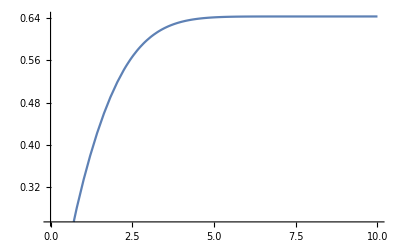

```mathematica
b=1;
Ω0=1;
τ=1;
Plot[NIntegrate[x Exp[-x]Coth[b x](1-Cos[(Ω0-x)τ])/(Ω0-x)^2,{x,0,t}],{t,0,10}]
```

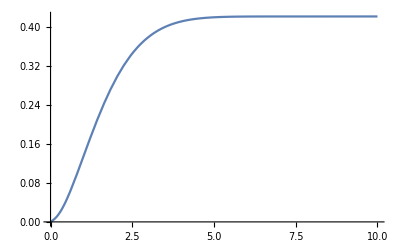

```mathematica
b=10;
Ω0=1;
τ=1;
Plot[NIntegrate[x Exp[-x]Coth[b x](1-Cos[(Ω0-x)τ])/(Ω0-x)^2,{x,0,t}],{t,0,10}]
```

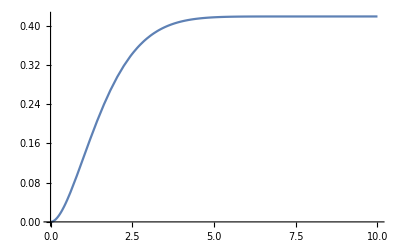

```mathematica
Ω0=1;
τ=1;
Plot[NIntegrate[x Exp[-x](1-Cos[(Ω0-x)τ])/(Ω0-x)^2,{x,0,t}],{t,0,10}]
```

```mathematica
2^0+2^1+2^3+2^4+2^5+2^6+2^7+2^9+2^10+2^11
```

3835

```mathematica
{{a11,a12},{a21,a22}}.{{b11,b12},{b21,b22}}
{{a11,a12},{a21,a22}}{{b11,b12},{b21,b22}}
```

{{a11 b11+a12 b21,a11 b12+a12 b22},{a21 b11+a22 b21,a21 b12+a22 b22}}

{{a11 b11,a12 b12},{a21 b21,a22 b22}}

```mathematica
Clear[L0,L1]
```

# Three qubit PMME

```mathematica
AdjacencyGraph[{{0, 1,0,0}, {1, 0,1,0}, {0, 1,0,1},{0,0,1,0}},DirectedEdges->True]
```

-Graphics-

The LO is the error correction generator and L1 is the lindblad errors of 3 qubit

```mathematica
L0[η_]:=η{{0,1,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}};
L1[γ_]:=γ{{-3,1,0,0},{3,-3,2,0},{0,2,-3,3},{0,0,1,-3}};
Mat=L0[η]+ L1[γ];
Eigenvalues[Mat]
Eigensystem[Mat]
```

{0,-4 γ-η,1/2 (-8 γ-η-√(16 γ^2+16 γ η+η^2)),1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))}

{{0,-4 γ-η,1/2 (-8 γ-η-√(16 γ^2+16 γ η+η^2)),1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))},{{1,(3 γ)/(γ+η),(3 γ)/(γ+η),1},{1,-1,-1,1},{-1,-(-2 γ-η-√(16 γ^2+16 γ η+η^2))/(2 (γ+η)),-(2 γ+η+√(16 γ^2+16 γ η+η^2))/(2 (γ+η)),1},{-1,-(-2 γ-η+√(16 γ^2+16 γ η+η^2))/(2 (γ+η)),-(2 γ+η-√(16 γ^2+16 γ η+η^2))/(2 (γ+η)),1}}}

Check that the Matrix is obtained by Q Lambda Inv(Q)

```mathematica
Λ=DiagonalMatrix[Eigensystem[Mat][[1]]];
Q=Transpose[Eigensystem[Mat][[2]]];
FullSimplify[Q.Λ.Inverse[Q]]//MatrixForm
Q//MatrixForm
```

(-3 γ | γ+η | 0 | 0
3 γ | -3 γ-η | 2 γ | 0
0 | 2 γ | -3 γ-η | 3 γ
0 | 0 | γ+η | -3 γ)

(1 | 1 | -1 | -1
(3 γ)/(γ+η) | -1 | -(-2 γ-η-√(16 γ^2+16 γ η+η^2))/(2 (γ+η)) | -(-2 γ-η+√(16 γ^2+16 γ η+η^2))/(2 (γ+η))
(3 γ)/(γ+η) | -1 | -(2 γ+η+√(16 γ^2+16 γ η+η^2))/(2 (γ+η)) | -(2 γ+η-√(16 γ^2+16 γ η+η^2))/(2 (γ+η))
1 | 1 | 1 | 1)

Since dv/dt = [L0] v + [L1 Q] Integrate[k (t')[Lambda[t] Inverse[Q]], {t', 0, t}]

```mathematica
FullSimplify[L1[γ].Q]//MatrixForm
```

(-(3 γ η)/(γ+η) | -4 γ | (γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(2 (γ+η)) | (γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)))/(2 (γ+η))
(3 γ η)/(γ+η) | 4 γ | -(γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(2 (γ+η)) | -(γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(2 (γ+η))
(3 γ η)/(γ+η) | 4 γ | (γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(2 (γ+η)) | (γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(2 (γ+η))
-(3 γ η)/(γ+η) | -4 γ | -(γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(2 (γ+η)) | (γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(2 (γ+η)))

```mathematica
Λ t//MatrixForm
MatrixExp[Λ t]//MatrixForm
```

(0 | 0 | 0 | 0
0 | t (-4 γ-η) | 0 | 0
0 | 0 | 1/2 t (-8 γ-η-√(16 γ^2+16 γ η+η^2)) | 0
0 | 0 | 0 | 1/2 t (-8 γ-η+√(16 γ^2+16 γ η+η^2)))

(1 | 0 | 0 | 0
0 | ⅇ^(-t (4 γ+η)) | 0 | 0
0 | 0 | ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) | 0
0 | 0 | 0 | ⅇ^(1/2 t (-8 γ-η+√(16 γ^2+16 γ η+η^2))))

Equation (154)

```mathematica
FullSimplify[MatrixExp[Λ t].Inverse[Q]]//MatrixForm
```

((γ+η)/(8 γ+2 η) | (γ+η)/(8 γ+2 η) | (γ+η)/(8 γ+2 η) | (γ+η)/(8 γ+2 η)
(3 ⅇ^(-t (4 γ+η)) γ)/(2 (4 γ+η)) | -(ⅇ^(-t (4 γ+η)) (γ+η))/(2 (4 γ+η)) | -(ⅇ^(-t (4 γ+η)) (γ+η))/(2 (4 γ+η)) | (3 ⅇ^(-t (4 γ+η)) γ)/(2 (4 γ+η))
(ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (2 γ+η-√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | (ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (γ+η))/(2 √(16 γ^2+16 γ η+η^2)) | -(ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (γ+η))/(2 √(16 γ^2+16 γ η+η^2)) | (ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (-2 γ-η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))
-(ⅇ^(1/2 t (-8 γ-η+√(16 γ^2+16 γ η+η^2))) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | -(ⅇ^(1/2 t (-8 γ-η+√(16 γ^2+16 γ η+η^2))) (γ+η))/(2 √(16 γ^2+16 γ η+η^2)) | (ⅇ^(1/2 t (-8 γ-η+√(16 γ^2+16 γ η+η^2))) (γ+η))/(2 √(16 γ^2+16 γ η+η^2)) | (ⅇ^(1/2 t (-8 γ-η+√(16 γ^2+16 γ η+η^2))) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)))

Remember that thes ki  are the shifted kernel laplace transforms ki=k(s-lambda_i)

```mathematica
DΛ=DiagonalMatrix[{k0,k1,k2,k3}]
FullSimplify[DΛ.Inverse[Q]]//MatrixForm
```

{{k0,0,0,0},{0,k1,0,0},{0,0,k2,0},{0,0,0,k3}}

((k0 (γ+η))/(2 (4 γ+η)) | (k0 (γ+η))/(2 (4 γ+η)) | (k0 (γ+η))/(2 (4 γ+η)) | (k0 (γ+η))/(2 (4 γ+η))
(3 k1 γ)/(8 γ+2 η) | -(k1 (γ+η))/(2 (4 γ+η)) | -(k1 (γ+η))/(2 (4 γ+η)) | (3 k1 γ)/(8 γ+2 η)
(k2 (2 γ+η-√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | (k2 (γ+η))/(2 √(16 γ^2+16 γ η+η^2)) | -(k2 (γ+η))/(2 √(16 γ^2+16 γ η+η^2)) | (k2 (-2 γ-η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))
-(k3 (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | -(k3 (γ+η))/(2 √(16 γ^2+16 γ η+η^2)) | (k3 (γ+η))/(2 √(16 γ^2+16 γ η+η^2)) | (k3 (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)))

```mathematica
FullSimplify[L1[γ].Q].FullSimplify[DΛ.Inverse[Q]]//MatrixForm
```

(-(3 k0 γ η)/(2 (4 γ+η))-(12 k1 γ^2)/(8 γ+2 η)-(k3 γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))+(k2 γ (2 γ+η-√(16 γ^2+16 γ η+η^2)) (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)) | -(3 k0 γ η)/(2 (4 γ+η))+(2 k1 γ (γ+η))/(4 γ+η)-(k3 γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | -(3 k0 γ η)/(2 (4 γ+η))+(2 k1 γ (γ+η))/(4 γ+η)+(k3 γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))-(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | -(3 k0 γ η)/(2 (4 γ+η))-(12 k1 γ^2)/(8 γ+2 η)+(k3 γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))+(k2 γ (-2 γ-η+√(16 γ^2+16 γ η+η^2)) (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))
(3 k0 γ η)/(2 (4 γ+η))+(12 k1 γ^2)/(8 γ+2 η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))-(k2 γ (2 γ+η-√(16 γ^2+16 γ η+η^2)) (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)) | (3 k0 γ η)/(2 (4 γ+η))-(2 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | (3 k0 γ η)/(2 (4 γ+η))-(2 k1 γ (γ+η))/(4 γ+η)-(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | (3 k0 γ η)/(2 (4 γ+η))+(12 k1 γ^2)/(8 γ+2 η)-(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))-(k2 γ (-2 γ-η+√(16 γ^2+16 γ η+η^2)) (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))
(3 k0 γ η)/(2 (4 γ+η))+(12 k1 γ^2)/(8 γ+2 η)-(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))+(k2 γ (2 γ+η-√(16 γ^2+16 γ η+η^2)) (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)) | (3 k0 γ η)/(2 (4 γ+η))-(2 k1 γ (γ+η))/(4 γ+η)-(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | (3 k0 γ η)/(2 (4 γ+η))-(2 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | (3 k0 γ η)/(2 (4 γ+η))+(12 k1 γ^2)/(8 γ+2 η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))+(k2 γ (-2 γ-η+√(16 γ^2+16 γ η+η^2)) (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))
-(3 k0 γ η)/(2 (4 γ+η))-(12 k1 γ^2)/(8 γ+2 η)-(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))-(k2 γ (2 γ+η-√(16 γ^2+16 γ η+η^2)) (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)) | -(3 k0 γ η)/(2 (4 γ+η))+(2 k1 γ (γ+η))/(4 γ+η)-(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))-(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | -(3 k0 γ η)/(2 (4 γ+η))+(2 k1 γ (γ+η))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | -(3 k0 γ η)/(2 (4 γ+η))-(12 k1 γ^2)/(8 γ+2 η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))-(k2 γ (-2 γ-η+√(16 γ^2+16 γ η+η^2)) (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)))

```mathematica
PmmeMat3=-s IdentityMatrix[4]+L0[η]+FullSimplify[L1[γ].Q].FullSimplify[DΛ.Inverse[Q]]
```

{{-s-(3 k0 γ η)/(2 (4 γ+η))-(12 k1 γ^2)/(8 γ+2 η)-(k3 γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))+(k2 γ (2 γ+η-√(16 γ^2+16 γ η+η^2)) (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)),η-(3 k0 γ η)/(2 (4 γ+η))+(2 k1 γ (γ+η))/(4 γ+η)-(k3 γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)),-(3 k0 γ η)/(2 (4 γ+η))+(2 k1 γ (γ+η))/(4 γ+η)+(k3 γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))-(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)),-(3 k0 γ η)/(2 (4 γ+η))-(12 k1 γ^2)/(8 γ+2 η)+(k3 γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))+(k2 γ (-2 γ-η+√(16 γ^2+16 γ η+η^2)) (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))},{(3 k0 γ η)/(2 (4 γ+η))+(12 k1 γ^2)/(8 γ+2 η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))-(k2 γ (2 γ+η-√(16 γ^2+16 γ η+η^2)) (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)),-s-η+(3 k0 γ η)/(2 (4 γ+η))-(2 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)),(3 k0 γ η)/(2 (4 γ+η))-(2 k1 γ (γ+η))/(4 γ+η)-(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)),(3 k0 γ η)/(2 (4 γ+η))+(12 k1 γ^2)/(8 γ+2 η)-(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))-(k2 γ (-2 γ-η+√(16 γ^2+16 γ η+η^2)) (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))},{(3 k0 γ η)/(2 (4 γ+η))+(12 k1 γ^2)/(8 γ+2 η)-(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))+(k2 γ (2 γ+η-√(16 γ^2+16 γ η+η^2)) (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)),(3 k0 γ η)/(2 (4 γ+η))-(2 k1 γ (γ+η))/(4 γ+η)-(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)),-s-η+(3 k0 γ η)/(2 (4 γ+η))-(2 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)),(3 k0 γ η)/(2 (4 γ+η))+(12 k1 γ^2)/(8 γ+2 η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))+(k2 γ (-2 γ-η+√(16 γ^2+16 γ η+η^2)) (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))},{-(3 k0 γ η)/(2 (4 γ+η))-(12 k1 γ^2)/(8 γ+2 η)-(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))-(k2 γ (2 γ+η-√(16 γ^2+16 γ η+η^2)) (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)),-(3 k0 γ η)/(2 (4 γ+η))+(2 k1 γ (γ+η))/(4 γ+η)-(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))-(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)),η-(3 k0 γ η)/(2 (4 γ+η))+(2 k1 γ (γ+η))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)),-s-(3 k0 γ η)/(2 (4 γ+η))-(12 k1 γ^2)/(8 γ+2 η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))-(k2 γ (-2 γ-η+√(16 γ^2+16 γ η+η^2)) (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))}}

```mathematica
FullSimplify[PmmeMat3]//MatrixForm
```

(-s+3/4 γ (-k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k3 η)/(√(16 γ^2+16 γ η+η^2))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2)))) | 1/4 ((2 (4 k1 γ (γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 (-4 s-4 η+(6 k0 γ η)/(4 γ+η)-(8 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))) | 1/4 (-4 s-4 η+(6 k0 γ η)/(4 γ+η)-(8 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 ((2 (4 k1 γ (γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | -s+3/4 γ (-k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k3 η)/(√(16 γ^2+16 γ η+η^2))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2)))))

```mathematica
Clear[s,γ,η,k0,k1,k2,k3]
```

Let' s define the matrix as a function of parameter s, the error rate γ, the error correction rate η and the laplace transform of kernels ki.

```mathematica
Func3Qub[s_,γ_,η_,k0_,k1_,k2_,k3_]:=({{-s+3/4 γ (-k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k3 η)/(√(16 γ^2+16 γ η+η^2))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2)))), 1/4 ((2 (4 k1 γ (γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2)))}, {3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 1/4 (-4 s-4 η+(6 k0 γ η)/(4 γ+η)-(8 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))), 3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))}, {3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))), 1/4 (-4 s-4 η+(6 k0 γ η)/(4 γ+η)-(8 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))}, {3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2))), 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 1/4 ((2 (4 k1 γ (γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), -s+3/4 γ (-k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k3 η)/(√(16 γ^2+16 γ η+η^2))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2))))}})
```

```mathematica
Simplify[Inverse[Func3Qub[s,γ,η,k0,k1,k2,k3]][[1,1]]]
```

-((4 s^3 (64 γ^3+80 γ^2 η+20 γ η^2+η^3)+24 γ^2 (4 k1 γ (γ+η)+η ((4-3 k0) γ+η)) (-k2 η √(16 γ^2+16 γ η+η^2)+k3 η √(16 γ^2+16 γ η+η^2)+k2 k3 (16 γ^2+16 γ η+η^2))+s^2 (832 k3 γ^4+512 γ^3 η-96 k0 γ^3 η+1040 k3 γ^3 η+640 γ^2 η^2-96 k0 γ^2 η^2+260 k3 γ^2 η^2+160 γ η^3-6 k0 γ η^3+13 k3 γ η^3+8 η^4-128 k3 γ^3 √(16 γ^2+16 γ η+η^2)-108 k3 γ^2 η √(16 γ^2+16 γ η+η^2)-19 k3 γ η^2 √(16 γ^2+16 γ η+η^2)+8 k1 γ (80 γ^3+112 γ^2 η+37 γ η^2+2 η^3)+k2 γ (4 γ+η) (208 γ^2+208 γ η+13 η^2+32 γ √(16 γ^2+16 γ η+η^2)+19 η √(16 γ^2+16 γ η+η^2)))+s (4 k1 γ (2 η (80 γ^3+112 γ^2 η+37 γ η^2+2 η^3)+k3 γ (448 γ^3+γ^2 (656 η-80 √(16 γ^2+16 γ η+η^2))+4 γ η (59 η-21 √(16 γ^2+16 γ η+η^2))+η^2 (13 η-19 √(16 γ^2+16 γ η+η^2)))+k2 γ (448 γ^3+16 γ^2 (41 η+5 √(16 γ^2+16 γ η+η^2))+η^2 (13 η+19 √(16 γ^2+16 γ η+η^2))+4 γ η (59 η+21 √(16 γ^2+16 γ η+η^2))))+η (-2 ((-8+3 k0) γ-2 η) η (16 γ^2+16 γ η+η^2)+k3 γ (-64 (-13+6 k0) γ^3+η^2 (13 η-19 √(16 γ^2+16 γ η+η^2))+4 γ η ((65-6 k0) η+3 (-7+2 k0) √(16 γ^2+16 γ η+η^2))+16 γ^2 ((65-24 k0) η+(-2+3 k0) √(16 γ^2+16 γ η+η^2))))+k2 γ (24 k3 γ (64 γ^3+80 γ^2 η+20 γ η^2+η^3)+η (-64 (-13+6 k0) γ^3+η^2 (13 η+19 √(16 γ^2+16 γ η+η^2))-4 γ η ((-65+6 k0) η+3 (-7+2 k0) √(16 γ^2+16 γ η+η^2))-16 γ^2 ((-65+24 k0) η+(-2+3 k0) √(16 γ^2+16 γ η+η^2))))))/(4 s (4 γ+η) (s+4 k1 γ+η) (s^2 (16 γ^2+16 γ η+η^2)+12 γ^2 (-k2 η √(16 γ^2+16 γ η+η^2)+k3 η √(16 γ^2+16 γ η+η^2)+k2 k3 (16 γ^2+16 γ η+η^2))+s (η (16 γ^2+16 γ η+η^2)+4 k3 γ (16 γ^2+16 γ η+η^2-2 γ √(16 γ^2+16 γ η+η^2)-η √(16 γ^2+16 γ η+η^2))+4 k2 γ (16 γ^2+η (η+√(16 γ^2+16 γ η+η^2))+2 γ (8 η+√(16 γ^2+16 γ η+η^2)))))))

Now let’s define the exponential kernel k(t)=c Exp[-ct] laplace transform

```mathematica
kLap[s_,c_]:=c/(s+c)
```

Now take the eigenvalues

```mathematica
Eigensystem[Mat][[1]]
```

{0,-4 γ-η,1/2 (-8 γ-η-√(16 γ^2+16 γ η+η^2)),1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))}

```mathematica
Eigensystem[Mat][[1,2]]
```

-4 γ-η

```mathematica
Simplify[Inverse[Func3Qub[s,γ,η,kLap[s-Eigensystem[Mat][[1,1]],c],kLap[s-Eigensystem[Mat][[1,2]],c],kLap[s-Eigensystem[Mat][[1,3]],c],kLap[s-Eigensystem[Mat][[1,4]],c]]][[1,1]]]
```

-(1+(c (s^3+6 γ^2 (γ+η)+s^2 (9 γ+2 η)+s (20 γ^2+9 γ η+η^2)))/(s (s^3+12 γ^2 (4 γ+η)+2 s^2 (6 γ+η)+s (44 γ^2+12 γ η+η^2))))/(c+s)

```mathematica
FullSimplify[InverseLaplaceTransform[Inverse[Func3Qub[s,γ,η,kLap[s-Eigensystem[Mat][[1,1]],c],kLap[s-Eigensystem[Mat][[1,2]],c],kLap[s-Eigensystem[Mat][[1,3]],c],kLap[s-Eigensystem[Mat][[1,4]],c]]][[1,1]],s,t]]
```

1/4 (-(6 c ⅇ^(-t (4 γ+η)) γ)/((c-4 γ-η) (4 γ+η))-(2 (γ+η))/(4 γ+η)-(12 ⅇ^(-c t) γ (c^2+2 γ (7 γ+η)-c (8 γ+η)))/((-c+4 γ+η) (c^2+12 γ^2-c (8 γ+η)))+(c ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (2 c γ-16 γ^2+c η-13 γ η-η^2-c √(16 γ^2+16 γ η+η^2)-c ⅇ^(t √(16 γ^2+16 γ η+η^2)) √(16 γ^2+16 γ η+η^2)+5 γ √(16 γ^2+16 γ η+η^2)+5 ⅇ^(t √(16 γ^2+16 γ η+η^2)) γ √(16 γ^2+16 γ η+η^2)+η √(16 γ^2+16 γ η+η^2)+ⅇ^(t √(16 γ^2+16 γ η+η^2)) η √(16 γ^2+16 γ η+η^2)+ⅇ^(t √(16 γ^2+16 γ η+η^2)) (16 γ^2+13 γ η+η^2-c (2 γ+η))))/(√(16 γ^2+16 γ η+η^2) (c^2+12 γ^2-c (8 γ+η))))

```mathematica
q0t[t_,γ_,η_,c_]:=InverseLaplaceTransform[Inverse[-Func3Qub[s, γ, η, kLap[s - Eigensystem[Mat][[1, 1]], c], kLap[s - Eigensystem[Mat][[1, 2]], c], kLap[s - Eigensystem[Mat][[1, 3]], c], kLap[s - Eigensystem[Mat][[1, 4]], c]]][[1, 1]], s, t]
```

```mathematica
q1t[t_,γ_,η_,c_]:=InverseLaplaceTransform[Inverse[-Func3Qub[s, γ, η, kLap[s - Eigensystem[Mat][[1, 1]], c], kLap[s - Eigensystem[Mat][[1, 2]], c], kLap[s - Eigensystem[Mat][[1, 3]], c], kLap[s - Eigensystem[Mat][[1, 4]], c]]][[2, 1]], s, t]
```

```mathematica
FullSimplify[q0t[t,γ,η,c]]
```

1/4 ((6 c ⅇ^(-t (4 γ+η)) γ)/((c-4 γ-η) (4 γ+η))+(2 (γ+η))/(4 γ+η)+(12 ⅇ^(-c t) γ (c^2+2 γ (7 γ+η)-c (8 γ+η)))/((-c+4 γ+η) (c^2+12 γ^2-c (8 γ+η)))+(c ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (-2 c γ+16 γ^2-c η+13 γ η+η^2+c √(16 γ^2+16 γ η+η^2)+c ⅇ^(t √(16 γ^2+16 γ η+η^2)) √(16 γ^2+16 γ η+η^2)-5 γ √(16 γ^2+16 γ η+η^2)-5 ⅇ^(t √(16 γ^2+16 γ η+η^2)) γ √(16 γ^2+16 γ η+η^2)-η √(16 γ^2+16 γ η+η^2)-ⅇ^(t √(16 γ^2+16 γ η+η^2)) η √(16 γ^2+16 γ η+η^2)-ⅇ^(t √(16 γ^2+16 γ η+η^2)) (16 γ^2+13 γ η+η^2-c (2 γ+η))))/(√(16 γ^2+16 γ η+η^2) (c^2+12 γ^2-c (8 γ+η))))

```mathematica
FullSimplify[q1t[t,γ,η,c]]
```

3/4 γ (2/(4 γ+η)-(2 c ⅇ^(-t (4 γ+η)))/((c-4 γ-η) (4 γ+η))-(4 ⅇ^(-c t) (c^2+6 γ^2-c (6 γ+η)))/((-c+4 γ+η) (c^2+12 γ^2-c (8 γ+η)))+(c ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (2 c (-1+ⅇ^(t √(16 γ^2+16 γ η+η^2)))+8 γ+η-√(16 γ^2+16 γ η+η^2)-ⅇ^(t √(16 γ^2+16 γ η+η^2)) (8 γ+η+√(16 γ^2+16 γ η+η^2))))/(√(16 γ^2+16 γ η+η^2) (c^2+12 γ^2-c (8 γ+η))))

```mathematica
q0tExplicit[t_,γ_,η_,c_]:=1/-4 (-(6 c ⅇ^(-t (4 γ+η)) γ)/((c-4 γ-η) (4 γ+η))-(2 (γ+η))/(4 γ+η)-(12 ⅇ^(-c t) γ (c^2+2 γ (7 γ+η)-c (8 γ+η)))/((-c+4 γ+η) (c^2+12 γ^2-c (8 γ+η)))+(c ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (2 c γ-16 γ^2+c η-13 γ η-η^2-c √(16 γ^2+16 γ η+η^2)-c ⅇ^(t √(16 γ^2+16 γ η+η^2)) √(16 γ^2+16 γ η+η^2)+5 γ √(16 γ^2+16 γ η+η^2)+5 ⅇ^(t √(16 γ^2+16 γ η+η^2)) γ √(16 γ^2+16 γ η+η^2)+η √(16 γ^2+16 γ η+η^2)+ⅇ^(t √(16 γ^2+16 γ η+η^2)) η √(16 γ^2+16 γ η+η^2)+ⅇ^(t √(16 γ^2+16 γ η+η^2)) (16 γ^2+13 γ η+η^2-c (2 γ+η))))/(√(16 γ^2+16 γ η+η^2) (c^2+12 γ^2-c (8 γ+η))))
```

```mathematica
q1tExplicit[t_,γ_,η_,c_]:=3/4 γ (2/(4 γ+η)-(2 c ⅇ^(-t (4 γ+η)))/((c-4 γ-η) (4 γ+η))-(4 ⅇ^(-c t) (c^2+6 γ^2-c (6 γ+η)))/((-c+4 γ+η) (c^2+12 γ^2-c (8 γ+η)))+(c ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (2 c (-1+ⅇ^(t √(16 γ^2+16 γ η+η^2)))+8 γ+η-√(16 γ^2+16 γ η+η^2)-ⅇ^(t √(16 γ^2+16 γ η+η^2)) (8 γ+η+√(16 γ^2+16 γ η+η^2))))/(√(16 γ^2+16 γ η+η^2) (c^2+12 γ^2-c (8 γ+η))))
```

```mathematica
qtExplicit[t_,γ_,η_,c_]:=q0tExplicit[t,γ,η,c]+q1tExplicit[t,γ,η,c]
```

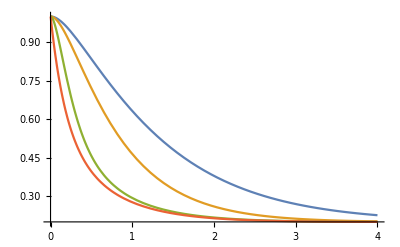

```mathematica
Plot[{q0tExplicit[t,1,1,1],q0tExplicit[t,1,1,2],q0tExplicit[t,1,1,10],q0tExplicit[t,1,1,1000]},{t,0,4}]
```

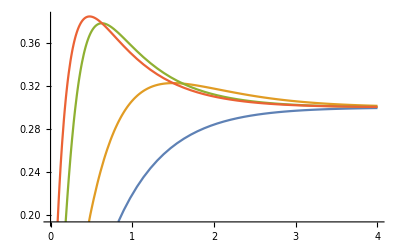

```mathematica
Plot[{q1tExplicit[t,1,1,1],q1tExplicit[t,1,1,2],q1tExplicit[t,1,1,10],q1tExplicit[t,1,1,1000]},{t,0,4}]
```

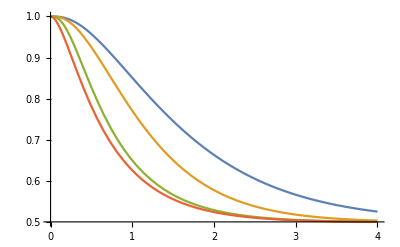

```mathematica
Plot[{qtExplicit[t,1,1,1],qtExplicit[t,1,1,2],qtExplicit[t,1,1,10],qtExplicit[t,1,1,1000]},{t,0,4}]
```

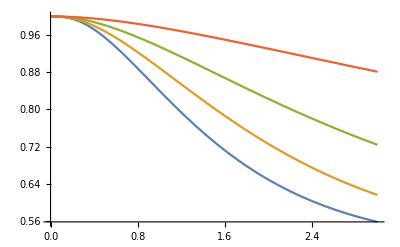

```mathematica
Plot[{qtExplicit[t,1,0,1],qtExplicit[t,1,6,1],qtExplicit[t,1,20,1],qtExplicit[t,1,80,1]},{t,0,3}]
```

now this is done in June 30

```mathematica
ResourceFunction["NInverseLaplaceTransform"][Exp[1-Sqrt[s]] s^(-3/4),s,3.7]
```

1.27511

```mathematica
Eigensystem[Mat][[1, 4]]
```

1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))

```mathematica
kLap[s_,c_]:=c/(s+c)
```

```mathematica
q0tNumerical[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][Inverse[-Func3Qub[s, γ, η, kLap[s , c], kLap[s - (-4 γ-η), c], kLap[s - 1/2 (-8 γ-η-√(16 γ^2+16 γ η+η^2)), c], kLap[s - 1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))]]][[1, 1]],s,t]
```

```mathematica
q0tNumerical[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][Inverse[-Func3Qub[s, γ, η,c/(s+c),c/((s- (-4 γ-η))+c), c/((s- 1/2 (-8 γ-η-√(16 γ^2+16 γ η+η^2)))+c), c/((s - 1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2)))+c)]][[1, 1]],s,t]
```

```mathematica
q0tNumerical[0.1,1,1,1]
```

0.987611

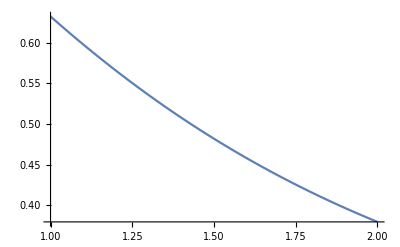

```mathematica
Plot[q0tNumerical[t,1,1,1],{t,1,2}]
```

```mathematica
Plot[{q0tExplicit[t,1,1,1]},{t,1,2}]
```

-Graphics-

```mathematica
kLapNum[s_,c_?NumericQ]:=c/(s+c)
kLapNum[s,c]
```

c/(c+s)

```mathematica
q0tNumer[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][Inverse[-Func3Qub[s, γ, η,kLapNum[s,c],kLapNum[s- (-4 γ-η),c],kLapNum[s- 1/2 (-8 γ-η-√(16 γ^2+16 γ η+η^2)),c], kLapNum[s- 1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2)),c]]][[1, 1]],s,t]
```

```mathematica
q0tExplicit[2,1,1,1]
```

1/4 (4/5-3/(10 ⅇ^10)+6/ⅇ^2-(ⅇ^(-9-√33) (-27+5 √33+27 ⅇ^(2 √33)+5 √33 ⅇ^(2 √33)))/(4 √33))

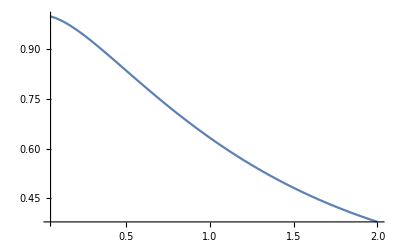

```mathematica
Plot[q0tNumer[t,1,1,1],{t,0.05,2}]
```

Zeno effect short time

```mathematica
M3[γ_,η_]:={{-3 γ,η+γ,0,0},{3 γ,-(η+3 γ),2 γ,0},{0,2 γ,-(η+3 γ),3 γ},{0,0,η+γ,-3 γ}}

MatrixForm[M3[γ,η]]
FullSimplify[MatrixExp[M3[γ,η]]]//MatrixForm

FullSimplify[MatrixForm[Dot[MatrixExp[M3[γ,η]],{1,0,0,0}]]]

FullSimplify[((IdentityMatrix[4]+M3[γ,η] t+MatrixPower[M3[γ,η],2] (t^2/2)+MatrixPower[M3[γ,η],3] (t^3/6)).{1,0,0,0})[[1]]]

FullSimplify[((IdentityMatrix[4]+M3[γ,η] t+MatrixPower[M3[γ,η],2] (t^2/2)+MatrixPower[M3[γ,η],3] (t^3/6)).{1,0,0,0})[[1]]+((IdentityMatrix[4]+M3[γ,η] t+MatrixPower[M3[γ,η],2] (t^2/2)+MatrixPower[M3[γ,η],3] (t^3/6)).{1,0,0,0})[[2]]]
```

(-3 γ | γ+η | 0 | 0
3 γ | -3 γ-η | 2 γ | 0
0 | 2 γ | -3 γ-η | 3 γ
0 | 0 | γ+η | -3 γ)

((3 ⅇ^(-4 γ-η) γ)/(8 γ+2 η)+(γ+η)/(8 γ+2 η)+(ⅇ^(-4 γ-η/2-1/2 √(16 γ^2+16 γ η+η^2)) (-2 γ-η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(ⅇ^(1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | (ⅇ^(-4 γ-η-1/2 √(16 γ^2+16 γ η+η^2)) (γ+η) (-ⅇ^(η/2) (4 γ+η) √(16 γ^2+16 γ η+η^2)+ⅇ^(η/2+√(16 γ^2+16 γ η+η^2)) (4 γ+η) √(16 γ^2+16 γ η+η^2)-ⅇ^(1/2 √(16 γ^2+16 γ η+η^2)) (16 γ^2+16 γ η+η^2)+ⅇ^(4 γ+η+1/2 √(16 γ^2+16 γ η+η^2)) (16 γ^2+16 γ η+η^2)))/(2 (4 γ+η) (16 γ^2+16 γ η+η^2)) | (ⅇ^(-4 γ-η-1/2 √(16 γ^2+16 γ η+η^2)) (γ+η) (ⅇ^(η/2) (4 γ+η) √(16 γ^2+16 γ η+η^2)-ⅇ^(η/2+√(16 γ^2+16 γ η+η^2)) (4 γ+η) √(16 γ^2+16 γ η+η^2)-ⅇ^(1/2 √(16 γ^2+16 γ η+η^2)) (16 γ^2+16 γ η+η^2)+ⅇ^(4 γ+η+1/2 √(16 γ^2+16 γ η+η^2)) (16 γ^2+16 γ η+η^2)))/(2 (4 γ+η) (16 γ^2+16 γ η+η^2)) | 1/2 (γ+η) (1/(4 γ+η)+(ⅇ^(-4 γ-η) ((6 γ)/(4 γ+η)+2 ⅇ^(η/2) (-Cosh[1/2 √(16 γ^2+16 γ η+η^2)]-((2 γ+η) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2)))))/(2 (γ+η)))
3/2 γ ((1-ⅇ^(-4 γ-η))/(4 γ+η)+(2 ⅇ^(-4 γ-η/2) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2))) | 1/4 ((6 γ)/(4 γ+η)+ⅇ^(-4 γ-η) ((2 (γ+η))/(4 γ+η)+2 ⅇ^(η/2) (Cosh[1/2 √(16 γ^2+16 γ η+η^2)]-((2 γ+η) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2))))) | 1/4 ((6 γ)/(4 γ+η)+ⅇ^(-4 γ-η) ((2 (γ+η))/(4 γ+η)+2 ⅇ^(η/2) (-Cosh[1/2 √(16 γ^2+16 γ η+η^2)]+((2 γ+η) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2))))) | 3/2 γ ((1-ⅇ^(-4 γ-η))/(4 γ+η)-(2 ⅇ^(-4 γ-η/2) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2)))
3/2 γ ((1-ⅇ^(-4 γ-η))/(4 γ+η)-(2 ⅇ^(-4 γ-η/2) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2))) | 1/4 ((6 γ)/(4 γ+η)+ⅇ^(-4 γ-η) ((2 (γ+η))/(4 γ+η)+2 ⅇ^(η/2) (-Cosh[1/2 √(16 γ^2+16 γ η+η^2)]+((2 γ+η) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2))))) | 1/4 ((6 γ)/(4 γ+η)+ⅇ^(-4 γ-η) ((2 (γ+η))/(4 γ+η)+2 ⅇ^(η/2) (Cosh[1/2 √(16 γ^2+16 γ η+η^2)]-((2 γ+η) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2))))) | 3/2 γ ((1-ⅇ^(-4 γ-η))/(4 γ+η)+(2 ⅇ^(-4 γ-η/2) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2)))
1/2 (γ+η) (1/(4 γ+η)+(ⅇ^(-4 γ-η) ((6 γ)/(4 γ+η)+2 ⅇ^(η/2) (-Cosh[1/2 √(16 γ^2+16 γ η+η^2)]-((2 γ+η) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2)))))/(2 (γ+η))) | (ⅇ^(-4 γ-η-1/2 √(16 γ^2+16 γ η+η^2)) (γ+η) (ⅇ^(η/2) (4 γ+η) √(16 γ^2+16 γ η+η^2)-ⅇ^(η/2+√(16 γ^2+16 γ η+η^2)) (4 γ+η) √(16 γ^2+16 γ η+η^2)-ⅇ^(1/2 √(16 γ^2+16 γ η+η^2)) (16 γ^2+16 γ η+η^2)+ⅇ^(4 γ+η+1/2 √(16 γ^2+16 γ η+η^2)) (16 γ^2+16 γ η+η^2)))/(2 (4 γ+η) (16 γ^2+16 γ η+η^2)) | (ⅇ^(-4 γ-η-1/2 √(16 γ^2+16 γ η+η^2)) (γ+η) (-ⅇ^(η/2) (4 γ+η) √(16 γ^2+16 γ η+η^2)+ⅇ^(η/2+√(16 γ^2+16 γ η+η^2)) (4 γ+η) √(16 γ^2+16 γ η+η^2)-ⅇ^(1/2 √(16 γ^2+16 γ η+η^2)) (16 γ^2+16 γ η+η^2)+ⅇ^(4 γ+η+1/2 √(16 γ^2+16 γ η+η^2)) (16 γ^2+16 γ η+η^2)))/(2 (4 γ+η) (16 γ^2+16 γ η+η^2)) | (3 ⅇ^(-4 γ-η) γ)/(8 γ+2 η)+(γ+η)/(8 γ+2 η)+(ⅇ^(-4 γ-η/2-1/2 √(16 γ^2+16 γ η+η^2)) (-2 γ-η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(ⅇ^(1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)))

((3 ⅇ^(-4 γ-η) γ)/(8 γ+2 η)+(γ+η)/(8 γ+2 η)+(ⅇ^(-4 γ-η/2-1/2 √(16 γ^2+16 γ η+η^2)) (-2 γ-η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(ⅇ^(1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))
3/2 γ ((1-ⅇ^(-4 γ-η))/(4 γ+η)+(2 ⅇ^(-4 γ-η/2) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2)))
3/2 γ ((1-ⅇ^(-4 γ-η))/(4 γ+η)-(2 ⅇ^(-4 γ-η/2) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2)))
1/2 (γ+η) (1/(4 γ+η)+(ⅇ^(-4 γ-η) ((6 γ)/(4 γ+η)+2 ⅇ^(η/2) (-Cosh[1/2 √(16 γ^2+16 γ η+η^2)]-((2 γ+η) Sinh[1/2 √(16 γ^2+16 γ η+η^2)])/(√(16 γ^2+16 γ η+η^2)))))/(2 (γ+η))))

1-1/2 t γ (6-3 t (4 γ+η)+t^2 (18 γ^2+10 γ η+η^2))

1+t^2 γ^2 (-3+t (8 γ+η))

## Finally try to combine all

```mathematica
kLapExpKernel[s_,c_,λ_]:=c/((s-λ)+c)
```

```mathematica
L0[η_]:=η{{0,1,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}};
L1[γ_]:=γ{{-3,1,0,0},{3,-3,2,0},{0,2,-3,3},{0,0,1,-3}};
(*==L0[η]+L1[γ]*)FullSimplify[Transpose[Eigenvectors[L0[η]+L1[γ]]].DiagonalMatrix[Eigenvalues[L0[η]+L1[γ]]].Inverse[Transpose[Eigenvectors[L0[η]+L1[γ]]]]];
(*L1[γ].Q]==*)
FullSimplify[L1[γ].Transpose[Eigenvectors[L0[η]+L1[γ]]]];
(*DΛ.Inverse[Q]*)
DiagonalMatrix[{k0,k1,k2,k3}].Inverse[Transpose[Eigenvectors[L0[η]+L1[γ]]]];
FullSimplify[(L1[γ].Transpose[Eigenvectors[L0[η]+L1[γ]]]).(DiagonalMatrix[{k0,k1,k2,k3}].Inverse[Transpose[Eigenvectors[L0[η]+L1[γ]]]])]//MatrixForm
PmmeMat3[s_,γ_,η_,k0_,k1_,k2_,k3_]:=-s IdentityMatrix[4]+L0[η]+(L1[γ].Transpose[Eigenvectors[L0[η]+L1[γ]]]).(DiagonalMatrix[{k0,k1,k2,k3}].Inverse[Transpose[Eigenvectors[L0[η]+L1[γ]]]])
FullSimplify[PmmeMat3[s,γ,η,k0,k1,k2,k3]]//MatrixForm
```

(3/4 γ (-(2 (4 k1 γ+k0 η))/(4 γ+η)+k3 (-1-η/(√(16 γ^2+16 γ η+η^2)))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2)))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)+k3 (4 γ+η))/(4 γ+η)+(-k3 (8 γ+7 η)+k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)-5 k3 (4 γ+η))/(4 γ+η)+(k3 (16 γ+11 η)-k2 (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)-5 k3 (4 γ+η))/(4 γ+η)+(k3 (16 γ+11 η)-k2 (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)+k3 (4 γ+η))/(4 γ+η)+(-k3 (8 γ+7 η)+k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (-(2 (4 k1 γ+k0 η))/(4 γ+η)+k3 (-1-η/(√(16 γ^2+16 γ η+η^2)))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2)))))

(-s+3/4 γ (-k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k3 η)/(√(16 γ^2+16 γ η+η^2))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2)))) | 1/4 ((2 (4 k1 γ (γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 (-(2 (4 k1 γ (γ+η)+2 s (4 γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))) | 1/4 (-(2 (4 k1 γ (γ+η)+2 s (4 γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 ((2 (4 k1 γ (γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | -s+3/4 γ (-k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k3 η)/(√(16 γ^2+16 γ η+η^2))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2)))))

```mathematica
PmmeMat3ExpKernel[s_,γ_,η_,c_]:=-s IdentityMatrix[4]+L0[η]+(L1[γ].Transpose[Eigenvectors[L0[η]+L1[γ]]]).(DiagonalMatrix[{kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[1]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[2]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[3]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[4]]]}].Inverse[Transpose[Eigenvectors[L0[η]+L1[γ]]]])
q0tNum[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][Inverse[-FullSimplify[PmmeMat3ExpKernel[s,γ,η,c]]][[1, 1]],s,t]
```

```mathematica
q0fak[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][(Inverse[-PmmeMat3ExpKernel[s,γ,η,c]].{1,0,0,0})[[1]],s,t]
```

```mathematica
overlap3q[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][(Inverse[-PmmeMat3ExpKernel[s,γ,η,c]].{1,0,0,0})[[1]],s,t]+ResourceFunction["NInverseLaplaceTransform"][(Inverse[-PmmeMat3ExpKernel[s,γ,η,c]].{1,0,0,0})[[2]],s,t]
```

```mathematica
Plot[q0tNum[t,1,1,1],{t,0.05,2}]
```

-Graphics-

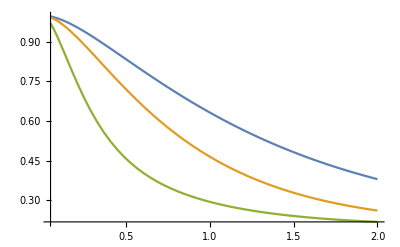

```mathematica
Plot[{q0tNum[t,1,1,1],q0tNum[t,1,1,2],q0tNum[t,1,1,10]},{t,0.05,2}]
```

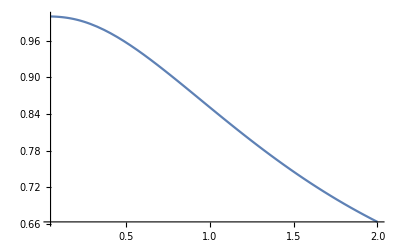

```mathematica
Plot[{overlap3q[t,1,1,1]},{t,0.05,2}]
```

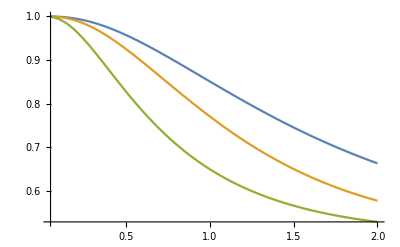

```mathematica
Plot[{overlap3q[t,1,1,1],overlap3q[t,1,1,2],overlap3q[t,1,1,10]},{t,0.05,2}]
```

overlap3q[t_, γ_, η_, c_]

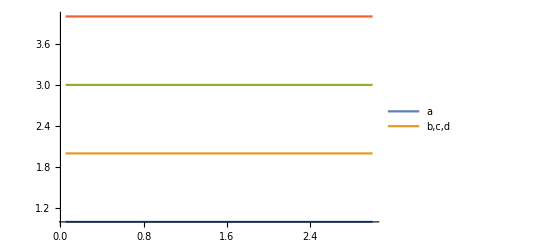

```mathematica
Plot[{1,2,3,4},{t,0.05,3},PlotLegends->{"a","b,c,d"}]
```

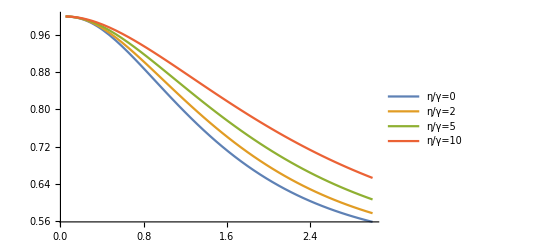

```mathematica
Plot[{overlap3q[t,1,0,1],overlap3q[t,1,2,1],overlap3q[t,1,5,1],overlap3q[t,1,10,1]},{t,0.05,3},PlotLegends->{"η/γ=0","η/γ=2","η/γ=5","η/γ=10"}]
```

```mathematica
Plot[q0fak[t,1,1,1],{t,0.05,2}]
```

-Graphics-

## Five qubit code

```mathematica
kLapExpKernel[s_,c_,λ_]:=c/((s-λ)+c)
```

```mathematica
L0five[η_]:=η{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,-2/3,1,2/3,1/2,1/3,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/3,0,-5/6,1/2,1/3,0,0,1/2,1/9,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,1/3,0,1/6,0,1/3,0,0,1/2,-1/9,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}}
MatrixForm[L0five[1]]
Total[L0five[η],{1}]
Eigenvalues[L0five[1]]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | -2/3 | 1 | 2/3 | 1/2 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/3 | 0 | -5/6 | 1/2 | 1/3 | 0 | 0 | 1/2 | 1/9 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/3 | 0 | 1/6 | 0 | 1/3 | 0 | 0 | 1/2 | -1/9 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0)

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{1/36 (-29-√217),-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1/36 (-29+√217),0,0,0}

```mathematica
L1five[γ_]:=γ{{-15,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{15,-13,2,2,0,0,0,0,0,0,0,0,0,0,0,0},{0,4,-15,2,3,1,0,0,0,0,0,0,0,0,0,0},{0,8,4,-13,0,2,3,0,0,0,0,0,0,0,0,0},{0,0,3,0,-15,1,0,0,1,0,4,0,0,0,0,0},{0,0,6,6,6,-12,6,4,3,2,0,0,0,0,0,0},{0,0,0,3,0,2,-15,0,0,2,0,0,0,0,0,0},{0,0,0,0,0,2,0,-15,3,2,0,0,3,1,0,0},{0,0,0,0,4,2,0,4,-14,2,8,4,2,0,2,0},{0,0,0,0,0,2,6,4,3,-11,0,0,0,4,3,0},{0,0,0,0,2,0,0,0,1,0,-15,1,0,0,0,5},{0,0,0,0,0,0,0,0,1,0,2,-14,2,0,2,10},{0,0,0,0,0,0,0,2,1,0,0,4,-12,2,2,0},{0,0,0,0,0,0,0,1,0,2,0,0,3,-11,6,0},{0,0,0,0,0,0,0,0,1,1,0,4,2,4,-15,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,-15}};
MatrixForm[L1five[1]]
Total[L1five[γ],{1}]
Eigenvalues[L1five[1]]
```

(-15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15 | -13 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | -15 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 | 4 | -13 | 0 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | -15 | 1 | 0 | 0 | 1 | 0 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 6 | 6 | -12 | 6 | 4 | 3 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 2 | -15 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | -15 | 3 | 2 | 0 | 0 | 3 | 1 | 0 | 0
0 | 0 | 0 | 0 | 4 | 2 | 0 | 4 | -14 | 2 | 8 | 4 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 2 | 6 | 4 | 3 | -11 | 0 | 0 | 0 | 4 | 3 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | -15 | 1 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | -14 | 2 | 0 | 2 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 4 | -12 | 2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 3 | -11 | 6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 4 | 2 | 4 | -15 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | -15)

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{-20,-20,-20,-20,-20,-16,-16,-16,-16,-12,-12,-12,-8,-8,-4,0}

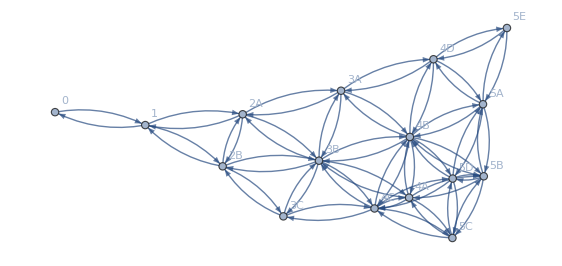

```mathematica
AdjacencyGraph[{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,1,0,1,0,0,0,0,0},{0,0,1,1,1,0,1,1,1,1,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,1,1,0,0,1,1,0,0},{0,0,0,0,1,1,0,1,0,1,1,1,1,0,1,0},{0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,0},{0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,1},{0,0,0,0,0,0,0,1,1,0,0,1,0,1,1,0},{0,0,0,0,0,0,0,1,0,1,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,1,1,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}},DirectedEdges->True,VertexLabels->{1->"0",2->"1",3->"2A",4->"2B",5->"3A",6->"3B",7->"3C",8->"4A",9->"4B",10->"4C",11->"4D",12->"5A",13->"5B",14->"5C",15->"5D",16->"5E"}]
```

```mathematica
MatrixForm[L0five[18]+L1five[1]]
```

(-15 | 19 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15 | -31 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | -33 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 | 4 | -31 | 0 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | -33 | 1 | 0 | 0 | 1 | 0 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 24 | 24 | 24 | -24 | 24 | 16 | 12 | 8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 2 | -33 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 8 | 0 | -30 | 12 | 8 | 0 | 0 | 12 | 3 | 0 | 0
0 | 0 | 0 | 0 | 4 | 2 | 0 | 4 | -32 | 2 | 8 | 4 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 2 | 6 | 4 | 3 | -29 | 0 | 0 | 0 | 4 | 3 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | -33 | 1 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | -32 | 2 | 0 | 2 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 4 | -30 | 2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 6 | 0 | 4 | 0 | 8 | 0 | 0 | 12 | -13 | 24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 4 | 2 | 4 | -33 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19 | 19 | 0 | 0 | 0 | -15)

```mathematica
DiagonalMatrix[Eigenvalues[L0five[36]]]
DiagonalMatrix[Eigenvalues[L1five[1]]]
```

{{-29-√217,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-36,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-36,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-36,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-36,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-36,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-36,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-36,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-36,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-36,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-36,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-36,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-29+√217,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{{-20,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-20,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-20,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-20,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-20,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-16,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-16,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-16,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-16,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-12,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-12,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-12,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-8,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-8,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
DiagonalMatrix[Eigenvalues[L0five[11]+L1five[1]]]//MatrixForm
```

(Root-35.8Root[28949642370900+16767440486289 #1+3892496306676 #1^2+487169783298 #1^3+36887468105 #1^4+1774605459 #1^5+54730182 #1^6+1050212 #1^7+11433 #1^8+54 #1^9&,1]-35.824125426649296 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Root-35.3Root[4032+1057 #1+62 #1^2+#1^3&,1]-35.27722929037653 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Root-34.3Root[28949642370900+16767440486289 #1+3892496306676 #1^2+487169783298 #1^3+36887468105 #1^4+1774605459 #1^5+54730182 #1^6+1050212 #1^7+11433 #1^8+54 #1^9&,2]-34.27816231275625 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Root-32.1Root[28949642370900+16767440486289 #1+3892496306676 #1^2+487169783298 #1^3+36887468105 #1^4+1774605459 #1^5+54730182 #1^6+1050212 #1^7+11433 #1^8+54 #1^9&,3]-32.12339680969611 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -31 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | Root-27.4Root[28949642370900+16767440486289 #1+3892496306676 #1^2+487169783298 #1^3+36887468105 #1^4+1774605459 #1^5+54730182 #1^6+1050212 #1^7+11433 #1^8+54 #1^9&,4]-27.39892327748256 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Root-27.0Root[28949642370900+16767440486289 #1+3892496306676 #1^2+487169783298 #1^3+36887468105 #1^4+1774605459 #1^5+54730182 #1^6+1050212 #1^7+11433 #1^8+54 #1^9&,5]-26.984204396330426 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Root-22.5Root[28949642370900+16767440486289 #1+3892496306676 #1^2+487169783298 #1^3+36887468105 #1^4+1774605459 #1^5+54730182 #1^6+1050212 #1^7+11433 #1^8+54 #1^9&,6]-22.493468087020236 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Root-21.4Root[4032+1057 #1+62 #1^2+#1^3&,2]-21.375867758393554 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Root-18.6Root[28949642370900+16767440486289 #1+3892496306676 #1^2+487169783298 #1^3+36887468105 #1^4+1774605459 #1^5+54730182 #1^6+1050212 #1^7+11433 #1^8+54 #1^9&,7]-18.58808825025657 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Root-9.31Root[28949642370900+16767440486289 #1+3892496306676 #1^2+487169783298 #1^3+36887468105 #1^4+1774605459 #1^5+54730182 #1^6+1050212 #1^7+11433 #1^8+54 #1^9&,8]-9.309152900593949 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Root-5.35Root[4032+1057 #1+62 #1^2+#1^3&,3]-5.346902951229917 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Root-4.72Root[28949642370900+16767440486289 #1+3892496306676 #1^2+487169783298 #1^3+36887468105 #1^4+1774605459 #1^5+54730182 #1^6+1050212 #1^7+11433 #1^8+54 #1^9&,9]-4.722700761436824 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Transpose[Eigenvectors[L0five[18]+L1five[1]]]
```

{{-1,Root0.209Root[-1896863849063+29273265121203 #1-140853827582805 #1^2+211498264866193 #1^3&,2]0.2087082269634763,-1,-1,0,-1,-3,-1,-1,-1,Root0.325Root[-1896863849063+29273265121203 #1-140853827582805 #1^2+211498264866193 #1^3&,3]0.3250842101742032,-1,-1,Root0.132Root[-1896863849063+29273265121203 #1-140853827582805 #1^2+211498264866193 #1^3&,1]0.1321885706588522,-1,385676611},{Root1.57Root[-1873763370-513795273 #1+44567935124 #1^2-114438116934 #1^3+38363210080 #1^4+237848335816 #1^5-421917365204 #1^6+317183329702 #1^7-116203326070 #1^8+16983563041 #1^9&,9]1.5689185029734822,Root-0.311Root[-244695436529127+1451868578638675 #1+21750520298486831 #1^2+46795696732813477 #1^3&,1]-0.310920077141792,Root1.45Root[-1873763370-513795273 #1+44567935124 #1^2-114438116934 #1^3+38363210080 #1^4+237848335816 #1^5-421917365204 #1^6+317183329702 #1^7-116203326070 #1^8+16983563041 #1^9&,8]1.4499027787368521,Root1.29Root[-1873763370-513795273 #1+44567935124 #1^2-114438116934 #1^3+38363210080 #1^4+237848335816 #1^5-421917365204 #1^6+317183329702 #1^7-116203326070 #1^8+16983563041 #1^9&,7]1.2892245429655527,0,Root1.03Root[-1873763370-513795273 #1+44567935124 #1^2-114438116934 #1^3+38363210080 #1^4+237848335816 #1^5-421917365204 #1^6+317183329702 #1^7-116203326070 #1^8+16983563041 #1^9&,6]1.025287832902956,3,1,Root0.999Root[-1873763370-513795273 #1+44567935124 #1^2-114438116934 #1^3+38363210080 #1^4+237848335816 #1^5-421917365204 #1^6+317183329702 #1^7-116203326070 #1^8+16983563041 #1^9&,5]0.9990252486157808,Root0.759Root[-1873763370-513795273 #1+44567935124 #1^2-114438116934 #1^3+38363210080 #1^4+237848335816 #1^5-421917365204 #1^6+317183329702 #1^7-116203326070 #1^8+16983563041 #1^9&,4]0.7594341632191356,Root-0.228Root[-244695436529127+1451868578638675 #1+21750520298486831 #1^2+46795696732813477 #1^3&,2]-0.2277280691897076,Root0.497Root[-1873763370-513795273 #1+44567935124 #1^2-114438116934 #1^3+38363210080 #1^4+237848335816 #1^5-421917365204 #1^6+317183329702 #1^7-116203326070 #1^8+16983563041 #1^9&,3]0.497291197893789,Root-0.168Root[-1873763370-513795273 #1+44567935124 #1^2-114438116934 #1^3+38363210080 #1^4+237848335816 #1^5-421917365204 #1^6+317183329702 #1^7-116203326070 #1^8+16983563041 #1^9&,2]-0.16795795776550243,Root0.0739Root[-244695436529127+1451868578638675 #1+21750520298486831 #1^2+46795696732813477 #1^3&,3]0.0738507009023943,Root-0.579Root[-1873763370-513795273 #1+44567935124 #1^2-114438116934 #1^3+38363210080 #1^4+237848335816 #1^5-421917365204 #1^6+317183329702 #1^7-116203326070 #1^8+16983563041 #1^9&,1]-0.5790210463841515,304481535},{Root-1.15Root[-1621072382891404364800-16970578949534564893184 #1-1390226553906413211328 #1^2+110878774968438401956720 #1^3-26346565559363144990760 #1^4-68905245965323140856856 #1^5+31621823898260710291137 #1^6+1985094764871001243784 #1^7-2329480837945585330239 #1^8+193345150681117111842 #1^9&,2]-1.1500218011176961,Root0.0847Root[-142361166878784-245972319667588304 #1+2801297676176247340 #1^2+1450666598717217787 #1^3&,3]0.08469216242585749,Root-0.321Root[-1621072382891404364800-16970578949534564893184 #1-1390226553906413211328 #1^2+110878774968438401956720 #1^3-26346565559363144990760 #1^4-68905245965323140856856 #1^5+31621823898260710291137 #1^6+1985094764871001243784 #1^7-2329480837945585330239 #1^8+193345150681117111842 #1^9&,3]-0.3212597996748503,Root2.15Root[-1621072382891404364800-16970578949534564893184 #1-1390226553906413211328 #1^2+110878774968438401956720 #1^3-26346565559363144990760 #1^4-68905245965323140856856 #1^5+31621823898260710291137 #1^6+1985094764871001243784 #1^7-2329480837945585330239 #1^8+193345150681117111842 #1^9&,7]2.1485673947447412,3,Root0.497Root[-1621072382891404364800-16970578949534564893184 #1-1390226553906413211328 #1^2+110878774968438401956720 #1^3-26346565559363144990760 #1^4-68905245965323140856856 #1^5+31621823898260710291137 #1^6+1985094764871001243784 #1^7-2329480837945585330239 #1^8+193345150681117111842 #1^9&,5]0.49702291071989935,18,1,Root9.62Root[-1621072382891404364800-16970578949534564893184 #1-1390226553906413211328 #1^2+110878774968438401956720 #1^3-26346565559363144990760 #1^4-68905245965323140856856 #1^5+31621823898260710291137 #1^6+1985094764871001243784 #1^7-2329480837945585330239 #1^8+193345150681117111842 #1^9&,9]9.624682229357504,Root-3.60Root[-1621072382891404364800-16970578949534564893184 #1-1390226553906413211328 #1^2+110878774968438401956720 #1^3-26346565559363144990760 #1^4-68905245965323140856856 #1^5+31621823898260710291137 #1^6+1985094764871001243784 #1^7-2329480837945585330239 #1^8+193345150681117111842 #1^9&,1]-3.600514139380211,Root-2.02Root[-142361166878784-245972319667588304 #1+2801297676176247340 #1^2+1450666598717217787 #1^3&,1]-2.015158844770454,Root2.96Root[-1621072382891404364800-16970578949534564893184 #1-1390226553906413211328 #1^2+110878774968438401956720 #1^3-26346565559363144990760 #1^4-68905245965323140856856 #1^5+31621823898260710291137 #1^6+1985094764871001243784 #1^7-2329480837945585330239 #1^8+193345150681117111842 #1^9&,8]2.9563109825324694,Root2.00Root[-1621072382891404364800-16970578949534564893184 #1-1390226553906413211328 #1^2+110878774968438401956720 #1^3-26346565559363144990760 #1^4-68905245965323140856856 #1^5+31621823898260710291137 #1^6+1985094764871001243784 #1^7-2329480837945585330239 #1^8+193345150681117111842 #1^9&,6]1.9973683224749654,Root-5.75 × 10^-4Root[-142361166878784-245972319667588304 #1+2801297676176247340 #1^2+1450666598717217787 #1^3&,2]-0.0005750047345389343,Root-0.104Root[-1621072382891404364800-16970578949534564893184 #1-1390226553906413211328 #1^2+110878774968438401956720 #1^3-26346565559363144990760 #1^4-68905245965323140856856 #1^5+31621823898260710291137 #1^6+1985094764871001243784 #1^7-2329480837945585330239 #1^8+193345150681117111842 #1^9&,4]-0.103853725693572,606908580},{Root-2.18Root[16380482903074114739200+238504884851276316392704 #1+999386320411239477015808 #1^2+1106831360421630834767360 #1^3-160806882075015069336896 #1^4-212166834023755874798560 #1^5+32567581798148677890096 #1^6+8524230524392394095456 #1^7-1961854188752114314536 #1^8+96672575340558555921 #1^9&,2]-2.1829302303336973,Root0.263Root[-2246499973517928-272699214487468412 #1+688236951498386386 #1^2+1450666598717217787 #1^3&,3]0.26292826122268553,Root-0.551Root[16380482903074114739200+238504884851276316392704 #1+999386320411239477015808 #1^2+1106831360421630834767360 #1^3-160806882075015069336896 #1^4-212166834023755874798560 #1^5+32567581798148677890096 #1^6+8524230524392394095456 #1^7-1961854188752114314536 #1^8+96672575340558555921 #1^9&,3]-0.5505896144243643,Root-0.125Root[16380482903074114739200+238504884851276316392704 #1+999386320411239477015808 #1^2+1106831360421630834767360 #1^3-160806882075015069336896 #1^4-212166834023755874798560 #1^5+32567581798148677890096 #1^6+8524230524392394095456 #1^7-1961854188752114314536 #1^8+96672575340558555921 #1^9&,5]-0.12472031177533341,-3,Root5.22Root[16380482903074114739200+238504884851276316392704 #1+999386320411239477015808 #1^2+1106831360421630834767360 #1^3-160806882075015069336896 #1^4-212166834023755874798560 #1^5+32567581798148677890096 #1^6+8524230524392394095456 #1^7-1961854188752114314536 #1^8+96672575340558555921 #1^9&,7]5.218735919664771,0,5,Root-3.61Root[16380482903074114739200+238504884851276316392704 #1+999386320411239477015808 #1^2+1106831360421630834767360 #1^3-160806882075015069336896 #1^4-212166834023755874798560 #1^5+32567581798148677890096 #1^6+8524230524392394095456 #1^7-1961854188752114314536 #1^8+96672575340558555921 #1^9&,1]-3.6139689904635715,Root11.7Root[16380482903074114739200+238504884851276316392704 #1+999386320411239477015808 #1^2+1106831360421630834767360 #1^3-160806882075015069336896 #1^4-212166834023755874798560 #1^5+32567581798148677890096 #1^6+8524230524392394095456 #1^7-1961854188752114314536 #1^8+96672575340558555921 #1^9&,9]11.696955086621983,Root-0.729Root[-2246499973517928-272699214487468412 #1+688236951498386386 #1^2+1450666598717217787 #1^3&,1]-0.7292801273416462,Root6.17Root[16380482903074114739200+238504884851276316392704 #1+999386320411239477015808 #1^2+1106831360421630834767360 #1^3-160806882075015069336896 #1^4-212166834023755874798560 #1^5+32567581798148677890096 #1^6+8524230524392394095456 #1^7-1961854188752114314536 #1^8+96672575340558555921 #1^9&,8]6.1726825133427665,Root3.89Root[16380482903074114739200+238504884851276316392704 #1+999386320411239477015808 #1^2+1106831360421630834767360 #1^3-160806882075015069336896 #1^4-212166834023755874798560 #1^5+32567581798148677890096 #1^6+8524230524392394095456 #1^7-1961854188752114314536 #1^8+96672575340558555921 #1^9&,6]3.8909741974218113,Root-8.08 × 10^-3Root[-2246499973517928-272699214487468412 #1+688236951498386386 #1^2+1450666598717217787 #1^3&,2]-0.008076201713423707,Root-0.213Root[16380482903074114739200+238504884851276316392704 #1+999386320411239477015808 #1^2+1106831360421630834767360 #1^3-160806882075015069336896 #1^4-212166834023755874798560 #1^5+32567581798148677890096 #1^6+8524230524392394095456 #1^7-1961854188752114314536 #1^8+96672575340558555921 #1^9&,4]-0.21333568085971896,1219980630},{Root-0.957Root[-655195711519882690560+71987081881492815817728 #1-72034480981253892597248 #1^2-128308565116447072753600 #1^3+107405793428549934712912 #1^4+59357355772932292298472 #1^5-37091047367034010706512 #1^6-9151754785077432467469 #1^7+3596430947420645550648 #1^8+290017726021675667763 #1^9&,4]-0.9573025761682589,Root0.138Root[6404491124214336-462601645778897552 #1+2822627401215095236 #1^2+1450666598717217787 #1^3&,3]0.13766840666068533,Root0.732Root[-655195711519882690560+71987081881492815817728 #1-72034480981253892597248 #1^2-128308565116447072753600 #1^3+107405793428549934712912 #1^4+59357355772932292298472 #1^5-37091047367034010706512 #1^6-9151754785077432467469 #1^7+3596430947420645550648 #1^8+290017726021675667763 #1^9&,6]0.7321267890501013,Root2.78Root[-655195711519882690560+71987081881492815817728 #1-72034480981253892597248 #1^2-128308565116447072753600 #1^3+107405793428549934712912 #1^4+59357355772932292298472 #1^5-37091047367034010706512 #1^6-9151754785077432467469 #1^7+3596430947420645550648 #1^8+290017726021675667763 #1^9&,9]2.7805584945533424,-3,Root-2.17Root[-655195711519882690560+71987081881492815817728 #1-72034480981253892597248 #1^2-128308565116447072753600 #1^3+107405793428549934712912 #1^4+59357355772932292298472 #1^5-37091047367034010706512 #1^6-9151754785077432467469 #1^7+3596430947420645550648 #1^8+290017726021675667763 #1^9&,2]-2.1697195964105864,-10,-5,Root-1.91Root[-655195711519882690560+71987081881492815817728 #1-72034480981253892597248 #1^2-128308565116447072753600 #1^3+107405793428549934712912 #1^4+59357355772932292298472 #1^5-37091047367034010706512 #1^6-9151754785077432467469 #1^7+3596430947420645550648 #1^8+290017726021675667763 #1^9&,3]-1.911783130138609,Root-13.9Root[-655195711519882690560+71987081881492815817728 #1-72034480981253892597248 #1^2-128308565116447072753600 #1^3+107405793428549934712912 #1^4+59357355772932292298472 #1^5-37091047367034010706512 #1^6-9151754785077432467469 #1^7+3596430947420645550648 #1^8+290017726021675667763 #1^9&,1]-13.941264985248607,Root-2.10Root[6404491124214336-462601645778897552 #1+2822627401215095236 #1^2+1450666598717217787 #1^3&,1]-2.098693851350324,Root1.13Root[-655195711519882690560+71987081881492815817728 #1-72034480981253892597248 #1^2-128308565116447072753600 #1^3+107405793428549934712912 #1^4+59357355772932292298472 #1^5-37091047367034010706512 #1^6-9151754785077432467469 #1^7+3596430947420645550648 #1^8+290017726021675667763 #1^9&,7]1.1349115720451584,Root1.92Root[-655195711519882690560+71987081881492815817728 #1-72034480981253892597248 #1^2-128308565116447072753600 #1^3+107405793428549934712912 #1^4+59357355772932292298472 #1^5-37091047367034010706512 #1^6-9151754785077432467469 #1^7+3596430947420645550648 #1^8+290017726021675667763 #1^9&,8]1.9225579824319898,Root0.0153Root[6404491124214336-462601645778897552 #1+2822627401215095236 #1^2+1450666598717217787 #1^3&,2]0.015280361904205833,Root9.19 × 10^-3Root[-655195711519882690560+71987081881492815817728 #1-72034480981253892597248 #1^2-128308565116447072753600 #1^3+107405793428549934712912 #1^4+59357355772932292298472 #1^5-37091047367034010706512 #1^6-9151754785077432467469 #1^7+3596430947420645550648 #1^8+290017726021675667763 #1^9&,5]0.009187409035125696,651253500},{Root14.5Root[849157405575580798156800+4449018855510343673708544 #1+4872519151127016731836416 #1^2-1785742433540006707200000 #1^3-583667891980923999862784 #1^4+77445285818040521521152 #1^5+8131791597434989051648 #1^6-715773839842935268960 #1^7-10782535372950426240 #1^8+798946903640979801 #1^9&,8]14.543220926492141,Root-0.568Root[221110623116845056+1318101326560673280 #1+2459243773503627144 #1^2+1450666598717217787 #1^3&,2]-0.5679321798829193,Root-3.83Root[849157405575580798156800+4449018855510343673708544 #1+4872519151127016731836416 #1^2-1785742433540006707200000 #1^3-583667891980923999862784 #1^4+77445285818040521521152 #1^5+8131791597434989051648 #1^6-715773839842935268960 #1^7-10782535372950426240 #1^8+798946903640979801 #1^9&,3]-3.827374598741101,Root-27.2Root[849157405575580798156800+4449018855510343673708544 #1+4872519151127016731836416 #1^2-1785742433540006707200000 #1^3-583667891980923999862784 #1^4+77445285818040521521152 #1^5+8131791597434989051648 #1^6-715773839842935268960 #1^7-10782535372950426240 #1^8+798946903640979801 #1^9&,1]-27.204650459455298,0,Root-8.77Root[849157405575580798156800+4449018855510343673708544 #1+4872519151127016731836416 #1^2-1785742433540006707200000 #1^3-583667891980923999862784 #1^4+77445285818040521521152 #1^5+8131791597434989051648 #1^6-715773839842935268960 #1^7-10782535372950426240 #1^8+798946903640979801 #1^9&,2]-8.765291306418792,0,0,Root-0.479Root[849157405575580798156800+4449018855510343673708544 #1+4872519151127016731836416 #1^2-1785742433540006707200000 #1^3-583667891980923999862784 #1^4+77445285818040521521152 #1^5+8131791597434989051648 #1^6-715773839842935268960 #1^7-10782535372950426240 #1^8+798946903640979801 #1^9&,4]-0.47924407828866855,Root2.54Root[849157405575580798156800+4449018855510343673708544 #1+4872519151127016731836416 #1^2-1785742433540006707200000 #1^3-583667891980923999862784 #1^4+77445285818040521521152 #1^5+8131791597434989051648 #1^6-715773839842935268960 #1^7-10782535372950426240 #1^8+798946903640979801 #1^9&,6]2.5356090301601713,Root-0.786Root[221110623116845056+1318101326560673280 #1+2459243773503627144 #1^2+1450666598717217787 #1^3&,1]-0.7857734959993208,Root7.54Root[849157405575580798156800+4449018855510343673708544 #1+4872519151127016731836416 #1^2-1785742433540006707200000 #1^3-583667891980923999862784 #1^4+77445285818040521521152 #1^5+8131791597434989051648 #1^6-715773839842935268960 #1^7-10782535372950426240 #1^8+798946903640979801 #1^9&,7]7.541531984035702,Root29.4Root[849157405575580798156800+4449018855510343673708544 #1+4872519151127016731836416 #1^2-1785742433540006707200000 #1^3-583667891980923999862784 #1^4+77445285818040521521152 #1^5+8131791597434989051648 #1^6-715773839842935268960 #1^7-10782535372950426240 #1^8+798946903640979801 #1^9&,9]29.448843476091447,Root-0.342Root[221110623116845056+1318101326560673280 #1+2459243773503627144 #1^2+1450666598717217787 #1^3&,3]-0.34154516650860617,Root-0.297Root[849157405575580798156800+4449018855510343673708544 #1+4872519151127016731836416 #1^2-1785742433540006707200000 #1^3-583667891980923999862784 #1^4+77445285818040521521152 #1^5+8131791597434989051648 #1^6-715773839842935268960 #1^7-10782535372950426240 #1^8+798946903640979801 #1^9&,5]-0.2967101078513382,14416335240},{Root-2.30Root[-1163260301885034496335360-28219093359392655545262336 #1+25835526429845166185918976 #1^2+5537368113830724287721984 #1^3-6760055334277717362574144 #1^4+243496081258434789193312 #1^5+405318549520478363567392 #1^6-41613897821660173154304 #1^7-2704660594002366205374 #1^8+290017726021675667763 #1^9&,3]-2.297544468432383,Root0.0164Root[3015838289975256-109937783915580780 #1-4555541475938934966 #1^2+1450666598717217787 #1^3&,2]0.016376747978480457,Root1.23Root[-1163260301885034496335360-28219093359392655545262336 #1+25835526429845166185918976 #1^2+5537368113830724287721984 #1^3-6760055334277717362574144 #1^4+243496081258434789193312 #1^5+405318549520478363567392 #1^6-41613897821660173154304 #1^7-2704660594002366205374 #1^8+290017726021675667763 #1^9&,5]1.2329530538500584,Root12.2Root[-1163260301885034496335360-28219093359392655545262336 #1+25835526429845166185918976 #1^2+5537368113830724287721984 #1^3-6760055334277717362574144 #1^4+243496081258434789193312 #1^5+405318549520478363567392 #1^6-41613897821660173154304 #1^7-2704660594002366205374 #1^8+290017726021675667763 #1^9&,9]12.186922419932102,3,Root-3.61Root[-1163260301885034496335360-28219093359392655545262336 #1+25835526429845166185918976 #1^2+5537368113830724287721984 #1^3-6760055334277717362574144 #1^4+243496081258434789193312 #1^5+405318549520478363567392 #1^6-41613897821660173154304 #1^7-2704660594002366205374 #1^8+290017726021675667763 #1^9&,2]-3.6078197894605246,-32,-9,Root-11.6Root[-1163260301885034496335360-28219093359392655545262336 #1+25835526429845166185918976 #1^2+5537368113830724287721984 #1^3-6760055334277717362574144 #1^4+243496081258434789193312 #1^5+405318549520478363567392 #1^6-41613897821660173154304 #1^7-2704660594002366205374 #1^8+290017726021675667763 #1^9&,1]-11.585822494210607,Root7.21Root[-1163260301885034496335360-28219093359392655545262336 #1+25835526429845166185918976 #1^2+5537368113830724287721984 #1^3-6760055334277717362574144 #1^4+243496081258434789193312 #1^5+405318549520478363567392 #1^6-41613897821660173154304 #1^7-2704660594002366205374 #1^8+290017726021675667763 #1^9&,8]7.209455969136055,Root3.16Root[3015838289975256-109937783915580780 #1-4555541475938934966 #1^2+1450666598717217787 #1^3&,3]3.1640530683197983,Root3.18Root[-1163260301885034496335360-28219093359392655545262336 #1+25835526429845166185918976 #1^2+5537368113830724287721984 #1^3-6760055334277717362574144 #1^4+243496081258434789193312 #1^5+405318549520478363567392 #1^6-41613897821660173154304 #1^7-2704660594002366205374 #1^8+290017726021675667763 #1^9&,7]3.1844965959485227,Root3.04Root[-1163260301885034496335360-28219093359392655545262336 #1+25835526429845166185918976 #1^2+5537368113830724287721984 #1^3-6760055334277717362574144 #1^4+243496081258434789193312 #1^5+405318549520478363567392 #1^6-41613897821660173154304 #1^7-2704660594002366205374 #1^8+290017726021675667763 #1^9&,6]3.0429906990725537,Root-0.0401Root[3015838289975256-109937783915580780 #1-4555541475938934966 #1^2+1450666598717217787 #1^3&,1]-0.040120747372815374,Root-0.0398Root[-1163260301885034496335360-28219093359392655545262336 #1+25835526429845166185918976 #1^2+5537368113830724287721984 #1^3-6760055334277717362574144 #1^4+243496081258434789193312 #1^5+405318549520478363567392 #1^6-41613897821660173154304 #1^7-2704660594002366205374 #1^8+290017726021675667763 #1^9&,4]-0.03978617943075143,1374414150},{Root-11.1Root[41522712829366739738296320-937008871817978672509353984 #1+705293870643621743519858688 #1^2-163998347312143676387917824 #1^3+3237806994132393570365440 #1^4+3098725343819143383355392 #1^5-196987350671759867969792 #1^6-21557853898168254666296 #1^7+1094115961066495837137 #1^8+70307327520406222488 #1^9&,3]-11.102431337416391,Root-0.799Root[179144017505427456+1194175747725921792 #1+2373120710186067912 #1^2+1450666598717217787 #1^3&,1]-0.7992256562645499,Root3.21Root[41522712829366739738296320-937008871817978672509353984 #1+705293870643621743519858688 #1^2-163998347312143676387917824 #1^3+3237806994132393570365440 #1^4+3098725343819143383355392 #1^5-196987350671759867969792 #1^6-21557853898168254666296 #1^7+1094115961066495837137 #1^8+70307327520406222488 #1^9&,5]3.2062014262712974,Root-19.1Root[41522712829366739738296320-937008871817978672509353984 #1+705293870643621743519858688 #1^2-163998347312143676387917824 #1^3+3237806994132393570365440 #1^4+3098725343819143383355392 #1^5-196987350671759867969792 #1^6-21557853898168254666296 #1^7+1094115961066495837137 #1^8+70307327520406222488 #1^9&,1]-19.087471257339214,0,Root4.79Root[41522712829366739738296320-937008871817978672509353984 #1+705293870643621743519858688 #1^2-163998347312143676387917824 #1^3+3237806994132393570365440 #1^4+3098725343819143383355392 #1^5-196987350671759867969792 #1^6-21557853898168254666296 #1^7+1094115961066495837137 #1^8+70307327520406222488 #1^9&,6]4.793061047919948,28,6,Root5.96Root[41522712829366739738296320-937008871817978672509353984 #1+705293870643621743519858688 #1^2-163998347312143676387917824 #1^3+3237806994132393570365440 #1^4+3098725343819143383355392 #1^5-196987350671759867969792 #1^6-21557853898168254666296 #1^7+1094115961066495837137 #1^8+70307327520406222488 #1^9&,8]5.960505500682468,Root9.03Root[41522712829366739738296320-937008871817978672509353984 #1+705293870643621743519858688 #1^2-163998347312143676387917824 #1^3+3237806994132393570365440 #1^4+3098725343819143383355392 #1^5-196987350671759867969792 #1^6-21557853898168254666296 #1^7+1094115961066495837137 #1^8+70307327520406222488 #1^9&,9]9.026826623287581,Root-0.561Root[179144017505427456+1194175747725921792 #1+2373120710186067912 #1^2+1450666598717217787 #1^3&,2]-0.561457079773183,Root-13.7Root[41522712829366739738296320-937008871817978672509353984 #1+705293870643621743519858688 #1^2-163998347312143676387917824 #1^3+3237806994132393570365440 #1^4+3098725343819143383355392 #1^5-196987350671759867969792 #1^6-21557853898168254666296 #1^7+1094115961066495837137 #1^8+70307327520406222488 #1^9&,2]-13.747906449873398,Root5.34Root[41522712829366739738296320-937008871817978672509353984 #1+705293870643621743519858688 #1^2-163998347312143676387917824 #1^3+3237806994132393570365440 #1^4+3098725343819143383355392 #1^5-196987350671759867969792 #1^6-21557853898168254666296 #1^7+1094115961066495837137 #1^8+70307327520406222488 #1^9&,7]5.34342754041218,Root-0.275Root[179144017505427456+1194175747725921792 #1+2373120710186067912 #1^2+1450666598717217787 #1^3&,3]-0.2752001830868609,Root0.0459Root[41522712829366739738296320-937008871817978672509353984 #1+705293870643621743519858688 #1^2-163998347312143676387917824 #1^3+3237806994132393570365440 #1^4+3098725343819143383355392 #1^5-196987350671759867969792 #1^6-21557853898168254666296 #1^7+1094115961066495837137 #1^8+70307327520406222488 #1^9&,4]0.04588177249834335,10160347080},{Root1.23Root[-164242710060065878425600+1484296773920127103246336 #1+1826595070462951933316096 #1^2-18780335971353905762499584 #1^3-2306589226669355028461632 #1^4+15644592266815138805907808 #1^5-1258220045809020891431644 #1^6-847607499758461397765076 #1^7-35333220023451851191659 #1^8+1740106356130054006578 #1^9&,7]1.2274393442660456,Root0.917Root[54281667959492032-2436747881212098928 #1+1264495163126721716 #1^2+1450666598717217787 #1^3&,3]0.9165236445043707,Root0.276Root[-164242710060065878425600+1484296773920127103246336 #1+1826595070462951933316096 #1^2-18780335971353905762499584 #1^3-2306589226669355028461632 #1^4+15644592266815138805907808 #1^5-1258220045809020891431644 #1^6-847607499758461397765076 #1^7-35333220023451851191659 #1^8+1740106356130054006578 #1^9&,6]0.2764666820180741,Root34.7Root[-164242710060065878425600+1484296773920127103246336 #1+1826595070462951933316096 #1^2-18780335971353905762499584 #1^3-2306589226669355028461632 #1^4+15644592266815138805907808 #1^5-1258220045809020891431644 #1^6-847607499758461397765076 #1^7-35333220023451851191659 #1^8+1740106356130054006578 #1^9&,9]34.72052928752655,2,Root-1.02Root[-164242710060065878425600+1484296773920127103246336 #1+1826595070462951933316096 #1^2-18780335971353905762499584 #1^3-2306589226669355028461632 #1^4+15644592266815138805907808 #1^5-1258220045809020891431644 #1^6-847607499758461397765076 #1^7-35333220023451851191659 #1^8+1740106356130054006578 #1^9&,3]-1.0170366225328578,0,10,Root-0.299Root[-164242710060065878425600+1484296773920127103246336 #1+1826595070462951933316096 #1^2-18780335971353905762499584 #1^3-2306589226669355028461632 #1^4+15644592266815138805907808 #1^5-1258220045809020891431644 #1^6-847607499758461397765076 #1^7-35333220023451851191659 #1^8+1740106356130054006578 #1^9&,4]-0.2988071386279965,Root-11.1Root[-164242710060065878425600+1484296773920127103246336 #1+1826595070462951933316096 #1^2-18780335971353905762499584 #1^3-2306589226669355028461632 #1^4+15644592266815138805907808 #1^5-1258220045809020891431644 #1^6-847607499758461397765076 #1^7-35333220023451851191659 #1^8+1740106356130054006578 #1^9&,1]-11.105933134542795,Root-1.81Root[54281667959492032-2436747881212098928 #1+1264495163126721716 #1^2+1450666598717217787 #1^3&,1]-1.8107354525131896,Root-6.73Root[-164242710060065878425600+1484296773920127103246336 #1+1826595070462951933316096 #1^2-18780335971353905762499584 #1^3-2306589226669355028461632 #1^4+15644592266815138805907808 #1^5-1258220045809020891431644 #1^6-847607499758461397765076 #1^7-35333220023451851191659 #1^8+1740106356130054006578 #1^9&,2]-6.725149010215287,Root3.11Root[-164242710060065878425600+1484296773920127103246336 #1+1826595070462951933316096 #1^2-18780335971353905762499584 #1^3-2306589226669355028461632 #1^4+15644592266815138805907808 #1^5-1258220045809020891431644 #1^6-847607499758461397765076 #1^7-35333220023451851191659 #1^8+1740106356130054006578 #1^9&,8]3.114372663698481,Root0.0225Root[54281667959492032-2436747881212098928 #1+1264495163126721716 #1^2+1450666598717217787 #1^3&,2]0.022546902892179296,Root0.113Root[-164242710060065878425600+1484296773920127103246336 #1+1826595070462951933316096 #1^2-18780335971353905762499584 #1^3-2306589226669355028461632 #1^4+15644592266815138805907808 #1^5-1258220045809020891431644 #1^6-847607499758461397765076 #1^7-35333220023451851191659 #1^8+1740106356130054006578 #1^9&,5]0.11332507794971343,3292742460},{Root2.30Root[1163260301885034496335360-28219093359392655545262336 #1-25835526429845166185918976 #1^2+5537368113830724287721984 #1^3+6760055334277717362574144 #1^4+243496081258434789193312 #1^5-405318549520478363567392 #1^6-41613897821660173154304 #1^7+2704660594002366205374 #1^8+290017726021675667763 #1^9&,7]2.297544468432383,Root0.0892Root[265056471302188392-1798555922760861612 #1-13300254196314191994 #1^2+1450666598717217787 #1^3&,2]0.0891587862758146,Root-1.23Root[1163260301885034496335360-28219093359392655545262336 #1-25835526429845166185918976 #1^2+5537368113830724287721984 #1^3+6760055334277717362574144 #1^4+243496081258434789193312 #1^5-405318549520478363567392 #1^6-41613897821660173154304 #1^7+2704660594002366205374 #1^8+290017726021675667763 #1^9&,5]-1.2329530538500584,Root-12.2Root[1163260301885034496335360-28219093359392655545262336 #1-25835526429845166185918976 #1^2+5537368113830724287721984 #1^3+6760055334277717362574144 #1^4+243496081258434789193312 #1^5-405318549520478363567392 #1^6-41613897821660173154304 #1^7+2704660594002366205374 #1^8+290017726021675667763 #1^9&,1]-12.186922419932102,-3,Root3.61Root[1163260301885034496335360-28219093359392655545262336 #1-25835526429845166185918976 #1^2+5537368113830724287721984 #1^3+6760055334277717362574144 #1^4+243496081258434789193312 #1^5-405318549520478363567392 #1^6-41613897821660173154304 #1^7+2704660594002366205374 #1^8+290017726021675667763 #1^9&,8]3.6078197894605246,16,-3,Root11.6Root[1163260301885034496335360-28219093359392655545262336 #1-25835526429845166185918976 #1^2+5537368113830724287721984 #1^3+6760055334277717362574144 #1^4+243496081258434789193312 #1^5-405318549520478363567392 #1^6-41613897821660173154304 #1^7+2704660594002366205374 #1^8+290017726021675667763 #1^9&,9]11.585822494210607,Root-7.21Root[1163260301885034496335360-28219093359392655545262336 #1-25835526429845166185918976 #1^2+5537368113830724287721984 #1^3+6760055334277717362574144 #1^4+243496081258434789193312 #1^5-405318549520478363567392 #1^6-41613897821660173154304 #1^7+2704660594002366205374 #1^8+290017726021675667763 #1^9&,2]-7.209455969136055,Root9.30Root[265056471302188392-1798555922760861612 #1-13300254196314191994 #1^2+1450666598717217787 #1^3&,3]9.299580737484733,Root-3.18Root[1163260301885034496335360-28219093359392655545262336 #1-25835526429845166185918976 #1^2+5537368113830724287721984 #1^3+6760055334277717362574144 #1^4+243496081258434789193312 #1^5-405318549520478363567392 #1^6-41613897821660173154304 #1^7+2704660594002366205374 #1^8+290017726021675667763 #1^9&,3]-3.1844965959485227,Root-3.04Root[1163260301885034496335360-28219093359392655545262336 #1-25835526429845166185918976 #1^2+5537368113830724287721984 #1^3+6760055334277717362574144 #1^4+243496081258434789193312 #1^5-405318549520478363567392 #1^6-41613897821660173154304 #1^7+2704660594002366205374 #1^8+290017726021675667763 #1^9&,4]-3.0429906990725537,Root-0.220Root[265056471302188392-1798555922760861612 #1-13300254196314191994 #1^2+1450666598717217787 #1^3&,1]-0.2203653376620886,Root0.0398Root[1163260301885034496335360-28219093359392655545262336 #1-25835526429845166185918976 #1^2+5537368113830724287721984 #1^3+6760055334277717362574144 #1^4+243496081258434789193312 #1^5-405318549520478363567392 #1^6-41613897821660173154304 #1^7+2704660594002366205374 #1^8+290017726021675667763 #1^9&,6]0.03978617943075143,6431527290},{Root-0.254Root[161863263498662969165-32865898260985560891016 #1+44053252824159564781158 #1^2+769570098366395287786198 #1^3-218105294724322693748752 #1^4-2079346315148455089717858 #1^5-112578348127697254428358 #1^6+176749121082574381789410 #1^7+33788968956262217145123 #1^8+1740106356130054006578 #1^9&,5]-0.2538441173092665,Root-0.505Root[-41712683409722597-1327287003727899 #1+893791907938113093 #1^2+1450666598717217787 #1^3&,1]-0.5053344128443471,Root-0.619Root[161863263498662969165-32865898260985560891016 #1+44053252824159564781158 #1^2+769570098366395287786198 #1^3-218105294724322693748752 #1^4-2079346315148455089717858 #1^5-112578348127697254428358 #1^6+176749121082574381789410 #1^7+33788968956262217145123 #1^8+1740106356130054006578 #1^9&,4]-0.6189427830369476,Root-8.01Root[161863263498662969165-32865898260985560891016 #1+44053252824159564781158 #1^2+769570098366395287786198 #1^3-218105294724322693748752 #1^4-2079346315148455089717858 #1^5-112578348127697254428358 #1^6+176749121082574381789410 #1^7+33788968956262217145123 #1^8+1740106356130054006578 #1^9&,1]-8.00551223565154,1,Root2.88Root[161863263498662969165-32865898260985560891016 #1+44053252824159564781158 #1^2+769570098366395287786198 #1^3-218105294724322693748752 #1^4-2079346315148455089717858 #1^5-112578348127697254428358 #1^6+176749121082574381789410 #1^7+33788968956262217145123 #1^8+1740106356130054006578 #1^9&,9]2.8758653546520594,-11,-2,Root-6.55Root[161863263498662969165-32865898260985560891016 #1+44053252824159564781158 #1^2+769570098366395287786198 #1^3-218105294724322693748752 #1^4-2079346315148455089717858 #1^5-112578348127697254428358 #1^6+176749121082574381789410 #1^7+33788968956262217145123 #1^8+1740106356130054006578 #1^9&,3]-6.554904773203349,Root-7.60Root[161863263498662969165-32865898260985560891016 #1+44053252824159564781158 #1^2+769570098366395287786198 #1^3-218105294724322693748752 #1^4-2079346315148455089717858 #1^5-112578348127697254428358 #1^6+176749121082574381789410 #1^7+33788968956262217145123 #1^8+1740106356130054006578 #1^9&,2]-7.602229488617488,Root-0.300Root[-41712683409722597-1327287003727899 #1+893791907938113093 #1^2+1450666598717217787 #1^3&,2]-0.30028273038709113,Root4.96 × 10^-3Root[161863263498662969165-32865898260985560891016 #1+44053252824159564781158 #1^2+769570098366395287786198 #1^3-218105294724322693748752 #1^4-2079346315148455089717858 #1^5-112578348127697254428358 #1^6+176749121082574381789410 #1^7+33788968956262217145123 #1^8+1740106356130054006578 #1^9&,6]0.0049608018109216665,Root0.546Root[161863263498662969165-32865898260985560891016 #1+44053252824159564781158 #1^2+769570098366395287786198 #1^3-218105294724322693748752 #1^4-2079346315148455089717858 #1^5-112578348127697254428358 #1^6+176749121082574381789410 #1^7+33788968956262217145123 #1^8+1740106356130054006578 #1^9&,8]0.546497978111697,Root0.189Root[-41712683409722597-1327287003727899 #1+893791907938113093 #1^2+1450666598717217787 #1^3&,3]0.1894921778338291,Root0.190Root[161863263498662969165-32865898260985560891016 #1+44053252824159564781158 #1^2+769570098366395287786198 #1^3-218105294724322693748752 #1^4-2079346315148455089717858 #1^5-112578348127697254428358 #1^6+176749121082574381789410 #1^7+33788968956262217145123 #1^8+1740106356130054006578 #1^9&,7]0.19034848257076986,490390515},{Root-1.32Root[139969127147322839318400+532590358063037087219584 #1-367572324248196328039648 #1^2-3433164930771421059328672 #1^3-3796357939515827916704232 #1^4-575202723851808501216120 #1^5+540915447567053935349926 #1^6+14931347001964341055746 #1^7-21882978098530268679063 #1^8+1740106356130054006578 #1^9&,2]-1.3150743856642158,Root-0.984Root[-211009132787830216-170008221069979852 #1+1473085174179452770 #1^2+1450666598717217787 #1^3&,1]-0.9844011939662203,Root-0.831Root[139969127147322839318400+532590358063037087219584 #1-367572324248196328039648 #1^2-3433164930771421059328672 #1^3-3796357939515827916704232 #1^4-575202723851808501216120 #1^5+540915447567053935349926 #1^6+14931347001964341055746 #1^7-21882978098530268679063 #1^8+1740106356130054006578 #1^9&,3]-0.8309599956999046,Root6.72Root[139969127147322839318400+532590358063037087219584 #1-367572324248196328039648 #1^2-3433164930771421059328672 #1^3-3796357939515827916704232 #1^4-575202723851808501216120 #1^5+540915447567053935349926 #1^6+14931347001964341055746 #1^7-21882978098530268679063 #1^8+1740106356130054006578 #1^9&,8]6.716287692685988,-1,Root-3.90Root[139969127147322839318400+532590358063037087219584 #1-367572324248196328039648 #1^2-3433164930771421059328672 #1^3-3796357939515827916704232 #1^4-575202723851808501216120 #1^5+540915447567053935349926 #1^6+14931347001964341055746 #1^7-21882978098530268679063 #1^8+1740106356130054006578 #1^9&,1]-3.901153187555015,6,2,Root5.56Root[139969127147322839318400+532590358063037087219584 #1-367572324248196328039648 #1^2-3433164930771421059328672 #1^3-3796357939515827916704232 #1^4-575202723851808501216120 #1^5+540915447567053935349926 #1^6+14931347001964341055746 #1^7-21882978098530268679063 #1^8+1740106356130054006578 #1^9&,7]5.555879524587568,Root6.84Root[139969127147322839318400+532590358063037087219584 #1-367572324248196328039648 #1^2-3433164930771421059328672 #1^3-3796357939515827916704232 #1^4-575202723851808501216120 #1^5+540915447567053935349926 #1^6+14931347001964341055746 #1^7-21882978098530268679063 #1^8+1740106356130054006578 #1^9&,9]6.8427953253983524,Root-0.400Root[-211009132787830216-170008221069979852 #1+1473085174179452770 #1^2+1450666598717217787 #1^3&,2]-0.4002375104073625,Root-0.502Root[139969127147322839318400+532590358063037087219584 #1-367572324248196328039648 #1^2-3433164930771421059328672 #1^3-3796357939515827916704232 #1^4-575202723851808501216120 #1^5+540915447567053935349926 #1^6+14931347001964341055746 #1^7-21882978098530268679063 #1^8+1740106356130054006578 #1^9&,4]-0.5022519997047107,Root-0.379Root[139969127147322839318400+532590358063037087219584 #1-367572324248196328039648 #1^2-3433164930771421059328672 #1^3-3796357939515827916704232 #1^4-575202723851808501216120 #1^5+540915447567053935349926 #1^6+14931347001964341055746 #1^7-21882978098530268679063 #1^8+1740106356130054006578 #1^9&,5]-0.37854002034619455,Root0.369Root[-211009132787830216-170008221069979852 #1+1473085174179452770 #1^2+1450666598717217787 #1^3&,3]0.36918472240277084,Root0.389Root[139969127147322839318400+532590358063037087219584 #1-367572324248196328039648 #1^2-3433164930771421059328672 #1^3-3796357939515827916704232 #1^4-575202723851808501216120 #1^5+540915447567053935349926 #1^6+14931347001964341055746 #1^7-21882978098530268679063 #1^8+1740106356130054006578 #1^9&,6]0.38867256381338167,1156613310},{Root2.11Root[781023643730400378880-6581576592137392930816 #1-18458033516375071420416 #1^2+8142922948012697097472 #1^3+6751895666569070345152 #1^4-574568928891657582032 #1^5-794807755956605899998 #1^6-114754164140087133154 #1^7-187712930215367411 #1^8+532631269093986534 #1^9&,8]2.107324377285955,Root0.329Root[-58989688941985792-1677654435583011520 #1+5172924016118029648 #1^2+1450666598717217787 #1^3&,3]0.3287063768853009,Root-0.411Root[781023643730400378880-6581576592137392930816 #1-18458033516375071420416 #1^2+8142922948012697097472 #1^3+6751895666569070345152 #1^4-574568928891657582032 #1^5-794807755956605899998 #1^6-114754164140087133154 #1^7-187712930215367411 #1^8+532631269093986534 #1^9&,5]-0.41086698937525107,Root-4.93Root[781023643730400378880-6581576592137392930816 #1-18458033516375071420416 #1^2+8142922948012697097472 #1^3+6751895666569070345152 #1^4-574568928891657582032 #1^5-794807755956605899998 #1^6-114754164140087133154 #1^7-187712930215367411 #1^8+532631269093986534 #1^9&,2]-4.929125889298083,0,Root1.67Root[781023643730400378880-6581576592137392930816 #1-18458033516375071420416 #1^2+8142922948012697097472 #1^3+6751895666569070345152 #1^4-574568928891657582032 #1^5-794807755956605899998 #1^6-114754164140087133154 #1^7-187712930215367411 #1^8+532631269093986534 #1^9&,7]1.672696685690687,-20,-10,Root-7.71Root[781023643730400378880-6581576592137392930816 #1-18458033516375071420416 #1^2+8142922948012697097472 #1^3+6751895666569070345152 #1^4-574568928891657582032 #1^5-794807755956605899998 #1^6-114754164140087133154 #1^7-187712930215367411 #1^8+532631269093986534 #1^9&,1]-7.712899099218894,Root17.5Root[781023643730400378880-6581576592137392930816 #1-18458033516375071420416 #1^2+8142922948012697097472 #1^3+6751895666569070345152 #1^4-574568928891657582032 #1^5-794807755956605899998 #1^6-114754164140087133154 #1^7-187712930215367411 #1^8+532631269093986534 #1^9&,9]17.541779124628817,Root-3.86Root[-58989688941985792-1677654435583011520 #1+5172924016118029648 #1^2+1450666598717217787 #1^3&,1]-3.862573313014291,Root-4.09Root[781023643730400378880-6581576592137392930816 #1-18458033516375071420416 #1^2+8142922948012697097472 #1^3+6751895666569070345152 #1^4-574568928891657582032 #1^5-794807755956605899998 #1^6-114754164140087133154 #1^7-187712930215367411 #1^8+532631269093986534 #1^9&,3]-4.0912225545776275,Root-3.92Root[781023643730400378880-6581576592137392930816 #1-18458033516375071420416 #1^2+8142922948012697097472 #1^3+6751895666569070345152 #1^4-574568928891657582032 #1^5-794807755956605899998 #1^6-114754164140087133154 #1^7-187712930215367411 #1^8+532631269093986534 #1^9&,4]-3.9199263049069555,Root-0.0320Root[-58989688941985792-1677654435583011520 #1+5172924016118029648 #1^2+1450666598717217787 #1^3&,2]-0.03202754347941581,Root0.0947Root[781023643730400378880-6581576592137392930816 #1-18458033516375071420416 #1^2+8142922948012697097472 #1^3+6751895666569070345152 #1^4-574568928891657582032 #1^5-794807755956605899998 #1^6-114754164140087133154 #1^7-187712930215367411 #1^8+532631269093986534 #1^9&,6]0.0946663166584463,2644808640},{Root-3.44Root[-94850602048620199390740480+516254951442665515216011264 #1-517994001110038034918670336 #1^2-143492872984315785240772608 #1^3+51803013733230263791362048 #1^4+8462705884898956455292416 #1^5-1043719262481075707241120 #1^6-125833033992474291683816 #1^7-145252848246858328017 #1^8+70307327520406222488 #1^9&,4]-3.4407895890757514,Root-0.160Root[61510144480985088+649305893954138112 #1+1885255978889815920 #1^2+1450666598717217787 #1^3&,3]-0.15963150317481664,Root0.621Root[-94850602048620199390740480+516254951442665515216011264 #1-517994001110038034918670336 #1^2-143492872984315785240772608 #1^3+51803013733230263791362048 #1^4+8462705884898956455292416 #1^5-1043719262481075707241120 #1^6-125833033992474291683816 #1^7-145252848246858328017 #1^8+70307327520406222488 #1^9&,6]0.6211731724698034,Root46.3Root[-94850602048620199390740480+516254951442665515216011264 #1-517994001110038034918670336 #1^2-143492872984315785240772608 #1^3+51803013733230263791362048 #1^4+8462705884898956455292416 #1^5-1043719262481075707241120 #1^6-125833033992474291683816 #1^7-145252848246858328017 #1^8+70307327520406222488 #1^9&,9]46.29212171679451,0,Root3.97Root[-94850602048620199390740480+516254951442665515216011264 #1-517994001110038034918670336 #1^2-143492872984315785240772608 #1^3+51803013733230263791362048 #1^4+8462705884898956455292416 #1^5-1043719262481075707241120 #1^6-125833033992474291683816 #1^7-145252848246858328017 #1^8+70307327520406222488 #1^9&,7]3.9722302584988447,0,0,Root-5.48Root[-94850602048620199390740480+516254951442665515216011264 #1-517994001110038034918670336 #1^2-143492872984315785240772608 #1^3+51803013733230263791362048 #1^4+8462705884898956455292416 #1^5-1043719262481075707241120 #1^6-125833033992474291683816 #1^7-145252848246858328017 #1^8+70307327520406222488 #1^9&,3]-5.481261422393799,Root-11.6Root[-94850602048620199390740480+516254951442665515216011264 #1-517994001110038034918670336 #1^2-143492872984315785240772608 #1^3+51803013733230263791362048 #1^4+8462705884898956455292416 #1^5-1043719262481075707241120 #1^6-125833033992474291683816 #1^7-145252848246858328017 #1^8+70307327520406222488 #1^9&,2]-11.562435653447753,Root-0.327Root[61510144480985088+649305893954138112 #1+1885255978889815920 #1^2+1450666598717217787 #1^3&,2]-0.32656000550017394,Root6.21Root[-94850602048620199390740480+516254951442665515216011264 #1-517994001110038034918670336 #1^2-143492872984315785240772608 #1^3+51803013733230263791362048 #1^4+8462705884898956455292416 #1^5-1043719262481075707241120 #1^6-125833033992474291683816 #1^7-145252848246858328017 #1^8+70307327520406222488 #1^9&,8]6.206374465837696,Root-34.8Root[-94850602048620199390740480+516254951442665515216011264 #1-517994001110038034918670336 #1^2-143492872984315785240772608 #1^3+51803013733230263791362048 #1^4+8462705884898956455292416 #1^5-1043719262481075707241120 #1^6-125833033992474291683816 #1^7-145252848246858328017 #1^8+70307327520406222488 #1^9&,1]-34.792271016503626,Root-0.813Root[61510144480985088+649305893954138112 #1+1885255978889815920 #1^2+1450666598717217787 #1^3&,1]-0.8133875817630831,Root0.251Root[-94850602048620199390740480+516254951442665515216011264 #1-517994001110038034918670336 #1^2-143492872984315785240772608 #1^3+51803013733230263791362048 #1^4+8462705884898956455292416 #1^5-1043719262481075707241120 #1^6-125833033992474291683816 #1^7-145252848246858328017 #1^8+70307327520406222488 #1^9&,5]0.2508283353529949,22258966320},{Root0.955Root[-59301600872583327398400+869214479233784581044992 #1-2792470527239254570905280 #1^2-552800042675520367402112 #1^3+9109578389293008386888112 #1^4-5520522619881674764680336 #1^5-1601564804278902103362692 #1^6+319934218238104635996792 #1^7+70646595420989908853307 #1^8+1740106356130054006578 #1^9&,8]0.9554908860676519,Root0.283Root[-19581845527019784-234794360112174364 #1+665566989710590890 #1^2+1450666598717217787 #1^3&,3]0.28268241035797387,Root0.274Root[-59301600872583327398400+869214479233784581044992 #1-2792470527239254570905280 #1^2-552800042675520367402112 #1^3+9109578389293008386888112 #1^4-5520522619881674764680336 #1^5-1601564804278902103362692 #1^6+319934218238104635996792 #1^7+70646595420989908853307 #1^8+1740106356130054006578 #1^9&,6]0.27412293240629015,Root-34.6Root[-59301600872583327398400+869214479233784581044992 #1-2792470527239254570905280 #1^2-552800042675520367402112 #1^3+9109578389293008386888112 #1^4-5520522619881674764680336 #1^5-1601564804278902103362692 #1^6+319934218238104635996792 #1^7+70646595420989908853307 #1^8+1740106356130054006578 #1^9&,1]-34.59580897575122,1,Root-4.20Root[-59301600872583327398400+869214479233784581044992 #1-2792470527239254570905280 #1^2-552800042675520367402112 #1^3+9109578389293008386888112 #1^4-5520522619881674764680336 #1^5-1601564804278902103362692 #1^6+319934218238104635996792 #1^7+70646595420989908853307 #1^8+1740106356130054006578 #1^9&,3]-4.201699297131913,0,5,Root3.91Root[-59301600872583327398400+869214479233784581044992 #1-2792470527239254570905280 #1^2-552800042675520367402112 #1^3+9109578389293008386888112 #1^4-5520522619881674764680336 #1^5-1601564804278902103362692 #1^6+319934218238104635996792 #1^7+70646595420989908853307 #1^8+1740106356130054006578 #1^9&,9]3.912776129091568,Root-0.591Root[-59301600872583327398400+869214479233784581044992 #1-2792470527239254570905280 #1^2-552800042675520367402112 #1^3+9109578389293008386888112 #1^4-5520522619881674764680336 #1^5-1601564804278902103362692 #1^6+319934218238104635996792 #1^7+70646595420989908853307 #1^8+1740106356130054006578 #1^9&,4]-0.5910219520791884,Root-0.670Root[-19581845527019784-234794360112174364 #1+665566989710590890 #1^2+1450666598717217787 #1^3&,1]-0.6702375357319913,Root0.552Root[-59301600872583327398400+869214479233784581044992 #1-2792470527239254570905280 #1^2-552800042675520367402112 #1^3+9109578389293008386888112 #1^4-5520522619881674764680336 #1^5-1601564804278902103362692 #1^6+319934218238104635996792 #1^7+70646595420989908853307 #1^8+1740106356130054006578 #1^9&,7]0.5524664968725209,Root-7.01Root[-59301600872583327398400+869214479233784581044992 #1-2792470527239254570905280 #1^2-552800042675520367402112 #1^3+9109578389293008386888112 #1^4-5520522619881674764680336 #1^5-1601564804278902103362692 #1^6+319934218238104635996792 #1^7+70646595420989908853307 #1^8+1740106356130054006578 #1^9&,2]-7.005346861120293,Root-0.0712Root[-19581845527019784-234794360112174364 #1+665566989710590890 #1^2+1450666598717217787 #1^3&,2]-0.07124567027339902,Root0.100Root[-59301600872583327398400+869214479233784581044992 #1-2792470527239254570905280 #1^2-552800042675520367402112 #1^3+9109578389293008386888112 #1^4-5520522619881674764680336 #1^5-1601564804278902103362692 #1^6+319934218238104635996792 #1^7+70646595420989908853307 #1^8+1740106356130054006578 #1^9&,5]0.10001060291000553,3293218350},{1,1,1,1,0,1,5,0,1,1,1,1,1,1,1,2086204845}}

```mathematica
MatrixForm[Transpose[Eigenvectors[L0five[18]+L1five[1]]].DiagonalMatrix[Eigenvalues[L0five[18]+L1five[1]]].Inverse[Transpose[Eigenvectors[L0five[18]+L1five[1]]]]]
```

$Aborted

```mathematica
MatrixForm[Transpose[N[Eigenvectors[L0five[18]+L1five[1]]]].DiagonalMatrix[N[Eigenvalues[L0five[18]+L1five[1]]]].Inverse[Transpose[N[Eigenvectors[L0five[18]+L1five[1]]]]]]
```

(-15.+1.77407×10^-15 ⅈ | -17.-4.59252×10^-15 ⅈ | -1.13826×10^-16-1.59728×10^-16 ⅈ | 6.22988×10^-16-1.99002×10^-16 ⅈ | -4.03379×10^-16+1.50521×10^-16 ⅈ | -6.26514×10^-16+1.58856×10^-16 ⅈ | -4.3536×10^-17+1.46429×10^-16 ⅈ | -1.04588×10^-15+1.55367×10^-16 ⅈ | -1.44385×10^-15+1.34203×10^-16 ⅈ | -1.14078×10^-15+9.2875×10^-17 ⅈ | -1.8234×10^-16-4.03231×10^-18 ⅈ | -2.54883×10^-16-5.71575×10^-17 ⅈ | -4.78123×10^-16+7.88135×10^-18 ⅈ | -2.48902×10^-16-3.28856×10^-17 ⅈ | -3.71972×10^-16-7.34596×10^-17 ⅈ | 2.62508×10^-16-3.58848×10^-17 ⅈ
15.+4.06071×10^-15 ⅈ | -31.-3.19606×10^-16 ⅈ | 2.+3.66597×10^-16 ⅈ | 2.+3.57088×10^-17 ⅈ | -6.5819×10^-16-1.75606×10^-16 ⅈ | -1.35932×10^-15-1.37334×10^-17 ⅈ | -1.39141×10^-16-1.77831×10^-16 ⅈ | -1.38771×10^-15-6.84285×10^-17 ⅈ | -1.60593×10^-15-8.11949×10^-17 ⅈ | -1.11297×10^-15-1.40237×10^-16 ⅈ | 5.02952×10^-16+1.27413×10^-16 ⅈ | -6.99904×10^-17+2.42392×10^-16 ⅈ | -1.0109×10^-16+1.45447×10^-16 ⅈ | -3.99525×10^-16+1.74609×10^-16 ⅈ | -2.1007×10^-16+1.28056×10^-16 ⅈ | 4.86782×10^-16+3.35966×10^-16 ⅈ
8.58094×10^-16+3.2103×10^-16 ⅈ | 4.+2.84431×10^-15 ⅈ | -33.+2.18614×10^-16 ⅈ | 2.+2.54194×10^-16 ⅈ | 3.-8.0836×10^-17 ⅈ | 1.-4.30471×10^-17 ⅈ | 6.56946×10^-15-8.4038×10^-17 ⅈ | 8.71147×10^-15-2.9774×10^-17 ⅈ | 1.12326×10^-14-9.55106×10^-18 ⅈ | 9.62076×10^-15-5.3784×10^-17 ⅈ | -1.05203×10^-16-3.20377×10^-17 ⅈ | -1.8013×10^-15-1.71021×10^-17 ⅈ | 3.8663×10^-15+2.72924×10^-17 ⅈ | 1.01876×10^-15-3.23779×10^-17 ⅈ | 1.81791×10^-15-3.74594×10^-17 ⅈ | -4.66151×10^-15-3.70192×10^-17 ⅈ
9.48513×10^-16+9.93562×10^-18 ⅈ | 8.-1.69065×10^-15 ⅈ | 4.-1.33112×10^-16 ⅈ | -31.-1.83472×10^-16 ⅈ | -1.3143×10^-15-8.65141×10^-17 ⅈ | 2.-3.11261×10^-17 ⅈ | 3.-5.24424×10^-17 ⅈ | 3.05729×10^-15-6.61822×10^-17 ⅈ | 5.10366×10^-15-7.60711×10^-17 ⅈ | 2.79344×10^-15-8.59639×10^-17 ⅈ | -1.42904×10^-15+6.34402×10^-18 ⅈ | 4.33033×10^-16+3.78839×10^-17 ⅈ | 7.22861×10^-16-2.4295×10^-18 ⅈ | -2.93782×10^-16+3.75453×10^-17 ⅈ | -1.39786×10^-15+3.05929×10^-17 ⅈ | -1.36518×10^-15+7.09012×10^-17 ⅈ
-2.24192×10^-16+3.01805×10^-16 ⅈ | -1.83585×10^-15+1.13311×10^-15 ⅈ | 3.+3.21128×10^-17 ⅈ | 3.00749×10^-16+2.94192×10^-17 ⅈ | -33.-1.24486×10^-16 ⅈ | 1.-1.19839×10^-16 ⅈ | -2.76277×10^-15-1.2967×10^-16 ⅈ | -6.05477×10^-15-9.0103×10^-17 ⅈ | 1.-8.62163×10^-17 ⅈ | -7.09842×10^-15-7.00144×10^-17 ⅈ | 4.-1.38515×10^-17 ⅈ | -1.1211×10^-15+1.60113×10^-17 ⅈ | -4.52704×10^-15-2.01724×10^-17 ⅈ | -2.89369×10^-15-1.29324×10^-17 ⅈ | -1.65829×10^-15-4.19135×10^-18 ⅈ | 6.73875×10^-17+2.26315×10^-17 ⅈ
-6.87233×10^-15-3.66668×10^-15 ⅈ | -1.09106×10^-15-3.20318×10^-16 ⅈ | 24.-4.87243×10^-16 ⅈ | 24.-3.38726×10^-16 ⅈ | 24.+4.03766×10^-17 ⅈ | -18.-3.79715×10^-17 ⅈ | 24.+4.84759×10^-17 ⅈ | 16.+3.25125×10^-17 ⅈ | 12.+2.92503×10^-17 ⅈ | 8.+9.81442×10^-17 ⅈ | 1.14753×10^-14-2.54422×10^-17 ⅈ | -7.3354×10^-15-7.62505×10^-17 ⅈ | 2.52064×10^-15-5.71765×10^-17 ⅈ | -6.15367×10^-15-5.8049×10^-17 ⅈ | -2.62622×10^-15-2.37276×10^-17 ⅈ | 1.40231×10^-14-1.17447×10^-16 ⅈ
2.38164×10^-15+1.20525×10^-16 ⅈ | -1.37075×10^-15+1.73535×10^-16 ⅈ | -1.42507×10^-15+2.97558×10^-17 ⅈ | 3.+4.63201×10^-17 ⅈ | -3.60892×10^-15+1.74229×10^-17 ⅈ | 2.+8.57179×10^-18 ⅈ | -33.+1.85969×10^-17 ⅈ | 5.54612×10^-17+5.99508×10^-18 ⅈ | 4.07451×10^-16+5.15967×10^-18 ⅈ | 2.+1.45743×10^-17 ⅈ | -8.51194×10^-15+1.58575×10^-18 ⅈ | 1.43907×10^-15-2.65533×10^-18 ⅈ | -2.75592×10^-15-2.54343×10^-18 ⅈ | 2.87779×10^-15+7.46576×10^-19 ⅈ | 2.85363×10^-15+4.4993×10^-18 ⅈ | -1.28377×10^-15-7.20533×10^-18 ⅈ
-2.24798×10^-15-1.95193×10^-17 ⅈ | 3.9893×10^-15-3.03688×10^-15 ⅈ | 1.31848×10^-15-2.71732×10^-17 ⅈ | 3.52091×10^-15-3.1777×10^-17 ⅈ | 1.37516×10^-14+3.98492×10^-16 ⅈ | 8.+3.40197×10^-16 ⅈ | 5.20615×10^-15+4.02685×10^-16 ⅈ | -30.+2.52399×10^-16 ⅈ | 12.+2.33817×10^-16 ⅈ | 8.+2.19038×10^-16 ⅈ | 8.57843×10^-15+7.55886×10^-17 ⅈ | -2.91252×10^-15-2.40696×10^-17 ⅈ | 12.+1.79762×10^-17 ⅈ | 3.+1.18704×10^-17 ⅈ | 6.78907×10^-15+2.33546×10^-19 ⅈ | -2.0432×10^-14-2.3958×10^-17 ⅈ
-1.50077×10^-15+1.09723×10^-15 ⅈ | 7.7408×10^-16+3.31057×10^-16 ⅈ | 1.30253×10^-15+1.0548×10^-16 ⅈ | -2.91044×10^-15+9.20611×10^-17 ⅈ | 4.-3.81712×10^-17 ⅈ | 2.-3.67291×10^-17 ⅈ | -7.72388×10^-15-4.02673×10^-17 ⅈ | 4.-3.42289×10^-17 ⅈ | -32.-4.40726×10^-17 ⅈ | 2.-1.73395×10^-17 ⅈ | 8.-6.44096×10^-18 ⅈ | 4.+2.03426×10^-17 ⅈ | 2.+6.98667×10^-18 ⅈ | 6.34835×10^-15+3.58599×10^-17 ⅈ | 2.+3.87757×10^-17 ⅈ | 1.40115×10^-14+2.30869×10^-17 ⅈ
5.30599×10^-15+1.21585×10^-15 ⅈ | -5.29571×10^-15+1.262×10^-15 ⅈ | 6.62311×10^-15+2.26456×10^-16 ⅈ | 8.19039×10^-15+2.19947×10^-16 ⅈ | -9.44931×10^-16-5.50538×10^-17 ⅈ | 2.-5.50111×10^-17 ⅈ | 6.-7.09505×10^-17 ⅈ | 4.-4.33024×10^-17 ⅈ | 3.-3.75909×10^-17 ⅈ | -29.-4.20269×10^-17 ⅈ | -2.01553×10^-15-2.31882×10^-17 ⅈ | -6.52437×10^-15-8.1431×10^-18 ⅈ | -1.10768×10^-14-6.88515×10^-18 ⅈ | 4.-2.90346×10^-17 ⅈ | 3.-2.8069×10^-17 ⅈ | 4.852×10^-15-1.23555×10^-17 ⅈ
8.43762×10^-16+3.61933×10^-16 ⅈ | 2.96122×10^-16-4.02617×10^-16 ⅈ | -4.27829×10^-16-1.28625×10^-17 ⅈ | 4.20205×10^-17-1.22112×10^-17 ⅈ | 2.-8.4526×10^-18 ⅈ | 4.38186×10^-16-7.24983×10^-18 ⅈ | 1.94453×10^-15-6.35395×10^-18 ⅈ | -3.18089×10^-15-1.44044×10^-17 ⅈ | 1.-2.04694×10^-17 ⅈ | 4.33312×10^-16-8.0222×10^-18 ⅈ | -33.+5.69867×10^-18 ⅈ | 1.+1.57237×10^-17 ⅈ | -1.41682×10^-15-2.18459×10^-18 ⅈ | 2.69402×10^-16+1.83656×10^-17 ⅈ | 1.67984×10^-15+2.01318×10^-17 ⅈ | 5.+2.29769×10^-17 ⅈ
9.37561×10^-16+1.45363×10^-16 ⅈ | -1.76341×10^-15-7.2635×10^-17 ⅈ | -1.30512×10^-15-8.65283×10^-18 ⅈ | -1.76323×10^-15-9.588×10^-18 ⅈ | 2.25314×10^-15-8.84706×10^-18 ⅈ | -1.57728×10^-16-1.43143×10^-17 ⅈ | 1.68923×10^-15-1.61632×10^-17 ⅈ | -5.78887×10^-15-5.44314×10^-18 ⅈ | 1.+3.24466×10^-18 ⅈ | 1.0119×10^-15-1.44869×10^-17 ⅈ | 2.+8.06343×10^-18 ⅈ | -32.+2.29243×10^-18 ⅈ | 2.-7.47675×10^-18 ⅈ | 3.04968×10^-17-3.54035×10^-17 ⅈ | 2.-3.45651×10^-17 ⅈ | 10.+4.94292×10^-18 ⅈ
5.60875×10^-16+6.44245×10^-16 ⅈ | 9.94572×10^-16+7.21744×10^-16 ⅈ | -7.18899×10^-16+1.46472×10^-16 ⅈ | -3.4111×10^-16+1.47381×10^-16 ⅈ | -1.96074×10^-15-1.39043×10^-17 ⅈ | -1.71665×10^-15-2.48479×10^-18 ⅈ | -1.82138×10^-16-1.443×10^-17 ⅈ | 2.-5.57302×10^-18 ⅈ | 1.-4.7526×10^-18 ⅈ | -2.57404×10^-15-1.35586×10^-17 ⅈ | 3.549×10^-15-5.78552×10^-17 ⅈ | 4.-5.38624×10^-17 ⅈ | -30.+4.30722×10^-18 ⅈ | 2.-1.19086×10^-17 ⅈ | 2.-1.74188×10^-17 ⅈ | 5.53863×10^-15-7.74702×10^-17 ⅈ
-3.51672×10^-15-9.36073×10^-16 ⅈ | 5.4528×10^-15-1.8061×10^-15 ⅈ | 4.23756×10^-16-2.17061×10^-16 ⅈ | -2.42788×10^-15-2.01513×10^-16 ⅈ | 4.72169×10^-15+9.86684×10^-17 ⅈ | 6.+1.07497×10^-16 ⅈ | 3.05995×10^-15+9.95267×10^-17 ⅈ | 4.+8.99843×10^-17 ⅈ | 1.30307×10^-14+7.62264×10^-17 ⅈ | 8.+7.58819×10^-17 ⅈ | 1.19056×10^-15+7.39399×10^-17 ⅈ | 3.58119×10^-15+6.24665×10^-17 ⅈ | 12.+5.19196×10^-17 ⅈ | -13.+7.44482×10^-17 ⅈ | 24.+6.284×10^-17 ⅈ | -8.66613×10^-15+8.08958×10^-17 ⅈ
8.75225×10^-16+1.10728×10^-15 ⅈ | -1.36256×10^-15+1.68872×10^-15 ⅈ | -1.45633×10^-15+1.50801×10^-16 ⅈ | 1.16836×10^-15+1.52839×10^-16 ⅈ | -2.91867×10^-15-1.74044×10^-16 ⅈ | -3.14758×10^-15-1.59665×10^-16 ⅈ | -3.85175×10^-16-1.80942×10^-16 ⅈ | -8.65949×10^-16-1.35431×10^-16 ⅈ | 1.-1.29529×10^-16 ⅈ | 1.-1.22455×10^-16 ⅈ | 1.87025×10^-15-3.33919×10^-17 ⅈ | 4.+8.49724×10^-18 ⅈ | 2.-3.86411×10^-17 ⅈ | 4.-3.60462×10^-17 ⅈ | -33.-3.01524×10^-17 ⅈ | 7.75956×10^-15+2.2799×10^-17 ⅈ
-1.32812×10^-15-5.27024×10^-16 ⅈ | 1.21179×10^-15+1.38679×10^-16 ⅈ | 4.64972×10^-16-8.63788×10^-18 ⅈ | 6.93104×10^-16-6.37428×10^-18 ⅈ | -9.91684×10^-16+2.96893×10^-17 ⅈ | -1.46714×10^-16+3.15761×10^-17 ⅈ | -1.4522×10^-15+3.43431×10^-17 ⅈ | 5.86856×10^-15+2.74119×10^-17 ⅈ | 1.19019×10^-15+2.51276×10^-17 ⅈ | -5.07599×10^-16+2.65947×10^-17 ⅈ | 19.-4.07079×10^-18 ⅈ | 19.-1.19423×10^-17 ⅈ | 2.56571×10^-15+9.26622×10^-18 ⅈ | -4.0334×10^-16+1.41176×10^-17 ⅈ | 6.44788×10^-16+1.14346×10^-17 ⅈ | -15.-1.86195×10^-17 ⅈ)

```mathematica
(**)
PmmeMat5ExpKernel[s_,γ_?NumericQ,η_?NumericQ,c_?NumericQ]:=-s IdentityMatrix[16]+L0five[η]+(L1five[γ].Transpose[N[Eigenvectors[L0five[η]+L1five[γ]]]]).(DiagonalMatrix[{kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[1]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[2]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[3]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[4]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[5]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[6]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[7]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[8]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[9]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[10]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[11]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[12]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[13]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[14]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[15]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[16]]]}].Inverse[Transpose[N[Eigenvectors[L0five[η]+L1five[γ]]]]])
```

```mathematica
N[PmmeMat5ExpKernel[1,1,1,1]]//MatrixForm
Inverse[N[PmmeMat5ExpKernel[1,1,1,1]]]//MatrixForm
```

(-1.81738 | -0.926368 | 0.0148424 | 0.0148424 | 0.00604321 | 0.00605714 | 0.00604345 | 0.00369987 | 0.00368278 | 0.00364249 | 0.0035598 | 0.00262788 | 0.00266997 | 0.00263428 | 0.00262937 | 0.00259281
0.194908 | -2.7791 | 0.0445272 | 0.0445273 | 0.0181296 | 0.0181714 | 0.0181304 | 0.0110996 | 0.0110483 | 0.0109275 | 0.0106794 | 0.00788363 | 0.00800992 | 0.00790284 | 0.00788811 | 0.00777843
0.0785677 | 0.0890434 | -2.77859 | 0.0673817 | 0.0662403 | 0.0484359 | 0.0393826 | 0.0295799 | 0.0306267 | 0.0279483 | 0.0332677 | 0.0218088 | 0.0215129 | 0.0206986 | 0.020924 | 0.0226133
0.157165 | 0.17812 | 0.134807 | -2.71116 | 0.0787969 | 0.0969354 | 0.10566 | 0.0592169 | 0.05776 | 0.0594714 | 0.0521676 | 0.0412603 | 0.0425664 | 0.0425241 | 0.0421809 | 0.0396142
0.0320916 | 0.0363705 | 0.0664024 | 0.0395398 | -2.78629 | 0.0461714 | 0.0346302 | 0.0332372 | 0.043636 | 0.0302542 | 0.0749561 | 0.0318503 | 0.0268524 | 0.0239976 | 0.0257457 | 0.0407814
0.0213318 | 0.0241761 | 1.03223 | 1.03224 | 1.03058 | -2.14602 | 1.03059 | 0.692371 | 0.524825 | 0.35711 | 0.0216093 | 0.017424 | 0.0180479 | 0.0175164 | 0.0174743 | 0.0166051
0.0643777 | 0.0729614 | 0.0793796 | 0.106233 | 0.069538 | 0.0927662 | -2.75144 | 0.0668547 | 0.0639822 | 0.0843404 | 0.0541263 | 0.0479858 | 0.0506418 | 0.055508 | 0.053711 | 0.0441465
0.00759247 | 0.0086048 | 0.0114506 | 0.0114843 | 0.0127804 | 0.34828 | 0.0130047 | -2.6602 | 0.516313 | 0.349168 | 0.0129086 | 0.0135787 | 0.517302 | 0.129348 | 0.0149749 | 0.0117841
0.079591 | 0.0902031 | 0.124975 | 0.117919 | 0.176385 | 0.152617 | 0.129341 | 0.172258 | -2.67787 | 0.151011 | 0.22159 | 0.181243 | 0.157602 | 0.130248 | 0.149262 | 0.171787
0.119669 | 0.135625 | 0.17375 | 0.184374 | 0.186578 | 0.222716 | 0.257408 | 0.242972 | 0.22854 | -2.5798 | 0.181988 | 0.187031 | 0.202424 | 0.251864 | 0.236647 | 0.163544
0.00959268 | 0.0108717 | 0.0168953 | 0.0132958 | 0.0376721 | 0.016596 | 0.0136755 | 0.0168441 | 0.027695 | 0.0150165 | -2.79977 | 0.0359211 | 0.0179246 | 0.0139225 | 0.0169771 | 0.0800211
0.0146397 | 0.0165917 | 0.0229162 | 0.0217253 | 0.0328177 | 0.0277077 | 0.0248782 | 0.0343482 | 0.0458484 | 0.0314462 | 0.0723114 | -2.76042 | 0.0634617 | 0.0404047 | 0.0597193 | 0.162196
0.0303048 | 0.0343454 | 0.0461176 | 0.0456321 | 0.0564678 | 0.0584991 | 0.0532311 | 0.0878094 | 0.0805387 | 0.0686284 | 0.0732091 | 0.127348 | -2.71303 | 0.104859 | 0.1072 | 0.0964429
-0.0167604 | -0.0189951 | -0.0254281 | -0.0252762 | -0.0229273 | 0.297643 | -0.0219147 | 0.151893 | -0.0150309 | 0.321865 | -0.013227 | -0.00577661 | 0.496905 | -1.95516 | 1.00053 | -0.0072883
0.0304904 | 0.0345558 | 0.0458688 | 0.0461771 | 0.0551537 | 0.0580511 | 0.0572089 | 0.0710645 | 0.0771528 | 0.0808117 | 0.0700951 | 0.120462 | 0.107857 | 0.127577 | -2.73631 | 0.0914759
-0.00617689 | -0.00700048 | -0.010148 | -0.00892694 | -0.017968 | -0.0112931 | -0.0098274 | -0.013049 | -0.0187463 | -0.0118434 | 0.930529 | 0.929775 | -0.0207455 | -0.0138481 | -0.0195501 | -1.94409)

(-0.53125 | 0.177083 | -2.79679×10^-17 | -2.86271×10^-17 | -1.62994×10^-17 | -2.55502×10^-17 | -1.40294×10^-17 | -2.09496×10^-17 | -1.78681×10^-17 | -1.20005×10^-17 | -5.69793×10^-18 | -2.03009×10^-17 | -1.3154×10^-17 | -1.57813×10^-17 | -1.82781×10^-17 | -2.16973×10^-17
-0.0397414 | -0.348347 | -0.00976585 | -0.00976588 | -0.00635637 | -0.00665392 | -0.00635653 | -0.00509988 | -0.00506789 | -0.00483277 | -0.00432827 | -0.00387369 | -0.00412046 | -0.00395257 | -0.00390753 | -0.00385393
-0.0212238 | -0.00801786 | -0.369786 | -0.018379 | -0.0181197 | -0.0166144 | -0.0147611 | -0.012735 | -0.0128184 | -0.0119066 | -0.0116009 | -0.00993384 | -0.0103055 | -0.00980008 | -0.00972363 | -0.0100432
-0.0424616 | -0.0160411 | -0.0367908 | -0.388198 | -0.029553 | -0.03329 | -0.0329129 | -0.0255141 | -0.0251907 | -0.0243392 | -0.0208611 | -0.0191189 | -0.020598 | -0.0198442 | -0.0195829 | -0.0188613
-0.0116984 | -0.00441939 | -0.0181543 | -0.0147948 | -0.368779 | -0.0165482 | -0.0141686 | -0.0134275 | -0.0147184 | -0.0125136 | -0.0183594 | -0.0128261 | -0.0114848 | -0.0107268 | -0.0108687 | -0.0140463
-0.0818199 | -0.0309097 | -0.267376 | -0.267378 | -0.265282 | -0.583946 | -0.265296 | -0.20966 | -0.194641 | -0.158499 | -0.0831025 | -0.0766645 | -0.10146 | -0.084442 | -0.0797396 | -0.0754569
-0.0234862 | -0.00887257 | -0.0297995 | -0.0331575 | -0.0285434 | -0.0334847 | -0.383145 | -0.0271344 | -0.0266114 | -0.0283592 | -0.0218938 | -0.0209097 | -0.0228876 | -0.0229993 | -0.0225962 | -0.020334
-0.0315128 | -0.0119048 | -0.0660912 | -0.0660963 | -0.0680502 | -0.11425 | -0.0680828 | -0.437717 | -0.12606 | -0.101554 | -0.0439059 | -0.0438993 | -0.118069 | -0.0671349 | -0.0524533 | -0.0420334
-0.0358576 | -0.0135462 | -0.0534633 | -0.052514 | -0.0604283 | -0.0628711 | -0.0544166 | -0.0589987 | -0.410169 | -0.0553716 | -0.0648076 | -0.0596858 | -0.055326 | -0.0507137 | -0.0528115 | -0.0587806
-0.0541204 | -0.0204455 | -0.0788474 | -0.0802773 | -0.0811215 | -0.0950809 | -0.0901777 | -0.087587 | -0.0853054 | -0.441017 | -0.0717028 | -0.0723898 | -0.0805866 | -0.0868055 | -0.084794 | -0.0690901
-0.00438096 | -0.00165503 | -0.00663476 | -0.00614912 | -0.0093217 | -0.00725045 | -0.00624601 | -0.00656989 | -0.00795427 | -0.00619486 | -0.365683 | -0.012973 | -0.00648466 | -0.0058299 | -0.00622151 | -0.0186049
-0.00768235 | -0.00290222 | -0.0116137 | -0.0114389 | -0.0131221 | -0.0140053 | -0.0120153 | -0.0133712 | -0.0147558 | -0.0129489 | -0.0263235 | -0.379495 | -0.0171636 | -0.0143368 | -0.0168174 | -0.0378658
-0.0157317 | -0.00594308 | -0.0239752 | -0.0239049 | -0.0256878 | -0.0298338 | -0.0252428 | -0.0300918 | -0.029027 | -0.0278842 | -0.0288769 | -0.0359535 | -0.387858 | -0.0333626 | -0.0337995 | -0.0321651
-0.0294378 | -0.0111209 | -0.0708515 | -0.0711334 | -0.0728189 | -0.134618 | -0.0746041 | -0.100942 | -0.0711322 | -0.125493 | -0.0449776 | -0.0507968 | -0.152422 | -0.570232 | -0.235523 | -0.0467781
-0.0158778 | -0.00599827 | -0.0241627 | -0.0242079 | -0.0257255 | -0.0302378 | -0.0260118 | -0.0283452 | -0.0284536 | -0.0298612 | -0.028204 | -0.0348127 | -0.0338564 | -0.037541 | -0.387046 | -0.0312221
-0.00150791 | -0.000569656 | -0.00228106 | -0.00219851 | -0.00280547 | -0.00265697 | -0.00228266 | -0.00249263 | -0.00283876 | -0.00239296 | -0.184417 | -0.184475 | -0.00295603 | -0.00252084 | -0.00287986 | -0.538309)

```mathematica
Chop[N[PmmeMat5ExpKernel[1,1,1,1]],10^-11]//MatrixForm
Inverse[Chop[N[PmmeMat5ExpKernel[1,1,1,1]],10^-11]]//MatrixForm
```

(-1.81738 | -0.926368 | 0.0148424 | 0.0148424 | 0.00604321 | 0.00605714 | 0.00604345 | 0.00369987 | 0.00368278 | 0.00364249 | 0.0035598 | 0.00262788 | 0.00266997 | 0.00263428 | 0.00262937 | 0.00259281
0.194908 | -2.7791 | 0.0445272 | 0.0445273 | 0.0181296 | 0.0181714 | 0.0181304 | 0.0110996 | 0.0110483 | 0.0109275 | 0.0106794 | 0.00788363 | 0.00800992 | 0.00790284 | 0.00788811 | 0.00777843
0.0785677 | 0.0890434 | -2.77859 | 0.0673817 | 0.0662403 | 0.0484359 | 0.0393826 | 0.0295799 | 0.0306267 | 0.0279483 | 0.0332677 | 0.0218088 | 0.0215129 | 0.0206986 | 0.020924 | 0.0226133
0.157165 | 0.17812 | 0.134807 | -2.71116 | 0.0787969 | 0.0969354 | 0.10566 | 0.0592169 | 0.05776 | 0.0594714 | 0.0521676 | 0.0412603 | 0.0425664 | 0.0425241 | 0.0421809 | 0.0396142
0.0320916 | 0.0363705 | 0.0664024 | 0.0395398 | -2.78629 | 0.0461714 | 0.0346302 | 0.0332372 | 0.043636 | 0.0302542 | 0.0749561 | 0.0318503 | 0.0268524 | 0.0239976 | 0.0257457 | 0.0407814
0.0213318 | 0.0241761 | 1.03223 | 1.03224 | 1.03058 | -2.14602 | 1.03059 | 0.692371 | 0.524825 | 0.35711 | 0.0216093 | 0.017424 | 0.0180479 | 0.0175164 | 0.0174743 | 0.0166051
0.0643777 | 0.0729614 | 0.0793796 | 0.106233 | 0.069538 | 0.0927662 | -2.75144 | 0.0668547 | 0.0639822 | 0.0843404 | 0.0541263 | 0.0479858 | 0.0506418 | 0.055508 | 0.053711 | 0.0441465
0.00759247 | 0.0086048 | 0.0114506 | 0.0114843 | 0.0127804 | 0.34828 | 0.0130047 | -2.6602 | 0.516313 | 0.349168 | 0.0129086 | 0.0135787 | 0.517302 | 0.129348 | 0.0149749 | 0.0117841
0.079591 | 0.0902031 | 0.124975 | 0.117919 | 0.176385 | 0.152617 | 0.129341 | 0.172258 | -2.67787 | 0.151011 | 0.22159 | 0.181243 | 0.157602 | 0.130248 | 0.149262 | 0.171787
0.119669 | 0.135625 | 0.17375 | 0.184374 | 0.186578 | 0.222716 | 0.257408 | 0.242972 | 0.22854 | -2.5798 | 0.181988 | 0.187031 | 0.202424 | 0.251864 | 0.236647 | 0.163544
0.00959268 | 0.0108717 | 0.0168953 | 0.0132958 | 0.0376721 | 0.016596 | 0.0136755 | 0.0168441 | 0.027695 | 0.0150165 | -2.79977 | 0.0359211 | 0.0179246 | 0.0139225 | 0.0169771 | 0.0800211
0.0146397 | 0.0165917 | 0.0229162 | 0.0217253 | 0.0328177 | 0.0277077 | 0.0248782 | 0.0343482 | 0.0458484 | 0.0314462 | 0.0723114 | -2.76042 | 0.0634617 | 0.0404047 | 0.0597193 | 0.162196
0.0303048 | 0.0343454 | 0.0461176 | 0.0456321 | 0.0564678 | 0.0584991 | 0.0532311 | 0.0878094 | 0.0805387 | 0.0686284 | 0.0732091 | 0.127348 | -2.71303 | 0.104859 | 0.1072 | 0.0964429
-0.0167604 | -0.0189951 | -0.0254281 | -0.0252762 | -0.0229273 | 0.297643 | -0.0219147 | 0.151893 | -0.0150309 | 0.321865 | -0.013227 | -0.00577661 | 0.496905 | -1.95516 | 1.00053 | -0.0072883
0.0304904 | 0.0345558 | 0.0458688 | 0.0461771 | 0.0551537 | 0.0580511 | 0.0572089 | 0.0710645 | 0.0771528 | 0.0808117 | 0.0700951 | 0.120462 | 0.107857 | 0.127577 | -2.73631 | 0.0914759
-0.00617689 | -0.00700048 | -0.010148 | -0.00892694 | -0.017968 | -0.0112931 | -0.0098274 | -0.013049 | -0.0187463 | -0.0118434 | 0.930529 | 0.929775 | -0.0207455 | -0.0138481 | -0.0195501 | -1.94409)

(-0.53125 | 0.177083 | -2.79679×10^-17 | -2.86271×10^-17 | -1.62994×10^-17 | -2.55502×10^-17 | -1.40294×10^-17 | -2.09496×10^-17 | -1.78681×10^-17 | -1.20005×10^-17 | -5.69793×10^-18 | -2.03009×10^-17 | -1.3154×10^-17 | -1.57813×10^-17 | -1.82781×10^-17 | -2.16973×10^-17
-0.0397414 | -0.348347 | -0.00976585 | -0.00976588 | -0.00635637 | -0.00665392 | -0.00635653 | -0.00509988 | -0.00506789 | -0.00483277 | -0.00432827 | -0.00387369 | -0.00412046 | -0.00395257 | -0.00390753 | -0.00385393
-0.0212238 | -0.00801786 | -0.369786 | -0.018379 | -0.0181197 | -0.0166144 | -0.0147611 | -0.012735 | -0.0128184 | -0.0119066 | -0.0116009 | -0.00993384 | -0.0103055 | -0.00980008 | -0.00972363 | -0.0100432
-0.0424616 | -0.0160411 | -0.0367908 | -0.388198 | -0.029553 | -0.03329 | -0.0329129 | -0.0255141 | -0.0251907 | -0.0243392 | -0.0208611 | -0.0191189 | -0.020598 | -0.0198442 | -0.0195829 | -0.0188613
-0.0116984 | -0.00441939 | -0.0181543 | -0.0147948 | -0.368779 | -0.0165482 | -0.0141686 | -0.0134275 | -0.0147184 | -0.0125136 | -0.0183594 | -0.0128261 | -0.0114848 | -0.0107268 | -0.0108687 | -0.0140463
-0.0818199 | -0.0309097 | -0.267376 | -0.267378 | -0.265282 | -0.583946 | -0.265296 | -0.20966 | -0.194641 | -0.158499 | -0.0831025 | -0.0766645 | -0.10146 | -0.084442 | -0.0797396 | -0.0754569
-0.0234862 | -0.00887257 | -0.0297995 | -0.0331575 | -0.0285434 | -0.0334847 | -0.383145 | -0.0271344 | -0.0266114 | -0.0283592 | -0.0218938 | -0.0209097 | -0.0228876 | -0.0229993 | -0.0225962 | -0.020334
-0.0315128 | -0.0119048 | -0.0660912 | -0.0660963 | -0.0680502 | -0.11425 | -0.0680828 | -0.437717 | -0.12606 | -0.101554 | -0.0439059 | -0.0438993 | -0.118069 | -0.0671349 | -0.0524533 | -0.0420334
-0.0358576 | -0.0135462 | -0.0534633 | -0.052514 | -0.0604283 | -0.0628711 | -0.0544166 | -0.0589987 | -0.410169 | -0.0553716 | -0.0648076 | -0.0596858 | -0.055326 | -0.0507137 | -0.0528115 | -0.0587806
-0.0541204 | -0.0204455 | -0.0788474 | -0.0802773 | -0.0811215 | -0.0950809 | -0.0901777 | -0.087587 | -0.0853054 | -0.441017 | -0.0717028 | -0.0723898 | -0.0805866 | -0.0868055 | -0.084794 | -0.0690901
-0.00438096 | -0.00165503 | -0.00663476 | -0.00614912 | -0.0093217 | -0.00725045 | -0.00624601 | -0.00656989 | -0.00795427 | -0.00619486 | -0.365683 | -0.012973 | -0.00648466 | -0.0058299 | -0.00622151 | -0.0186049
-0.00768235 | -0.00290222 | -0.0116137 | -0.0114389 | -0.0131221 | -0.0140053 | -0.0120153 | -0.0133712 | -0.0147558 | -0.0129489 | -0.0263235 | -0.379495 | -0.0171636 | -0.0143368 | -0.0168174 | -0.0378658
-0.0157317 | -0.00594308 | -0.0239752 | -0.0239049 | -0.0256878 | -0.0298338 | -0.0252428 | -0.0300918 | -0.029027 | -0.0278842 | -0.0288769 | -0.0359535 | -0.387858 | -0.0333626 | -0.0337995 | -0.0321651
-0.0294378 | -0.0111209 | -0.0708515 | -0.0711334 | -0.0728189 | -0.134618 | -0.0746041 | -0.100942 | -0.0711322 | -0.125493 | -0.0449776 | -0.0507968 | -0.152422 | -0.570232 | -0.235523 | -0.0467781
-0.0158778 | -0.00599827 | -0.0241627 | -0.0242079 | -0.0257255 | -0.0302378 | -0.0260118 | -0.0283452 | -0.0284536 | -0.0298612 | -0.028204 | -0.0348127 | -0.0338564 | -0.037541 | -0.387046 | -0.0312221
-0.00150791 | -0.000569656 | -0.00228106 | -0.00219851 | -0.00280547 | -0.00265697 | -0.00228266 | -0.00249263 | -0.00283876 | -0.00239296 | -0.184417 | -0.184475 | -0.00295603 | -0.00252084 | -0.00287986 | -0.538309)

```mathematica
Chop[N[PmmeMat5ExpKernel[s,1,1,1]],10^-11][[2,1]]
```

0.00976749/(0.959238+s)-0.356569/(5.56116+s)-0.00253072/(8.87517+s)-5.4541/(10.3492+s)-0.105399/(13.2386+s)-0.176209/(13.8596+s)-111.264/(15.3538+s)+114.066/(16.+s)+0.0393294/(17.9816+s)-0.0233505/(17.9872+s)+18.2038/(20.8116+s)+0.0109628/(22.1548+s)+0.0521572/(22.3085+s)+0.000270416/(22.8372+s)

```mathematica
MatrixRank[Chop[N[PmmeMat5ExpKernel[s,1,1,1]],10^-7]]
```

7

```mathematica
MatrixRank[Chop[N[PmmeMat5ExpKernel[s,1,18,1]],10^-7]]
```

9

```mathematica
Det[Chop[N[PmmeMat5ExpKernel[s,1,1,1]],10^-11]]
```

0.

```mathematica
Chop[N[PmmeMat5ExpKernel[s,1,1,1]],10^-11]//MatrixForm
```

```mathematica
Inverse[Chop[N[PmmeMat5ExpKernel[s,1,1,1]],10^-11]]//MatrixForm
```

Inverse::sing: Matrix {{-1. s+0.00938494/(0.959238+s)+0.100127/(5.56116+s)+0.000368096/(8.87517+s)+0.653246/(10.3492+s)+0.00937831/(13.2386+s)+0.0148579/(13.8596+s)+8.33205/(15.3538+s)-23.1476/(16.+s)-0.00246091/(17.9816+s)+«5»,«9»,«6»},{«13»+(«19»)/(«1»)+0.0393294/(«19»+s)-0.0233505/(17.9872+s)+«4»,-1.-1. s+«15»+«5»,0.+«14»+«4»,0.+«13»+«4»,«4»,0.+«13»+«4»,0.+0.0116571/(0.959238+s)+«10»+«4»,«6»},«8»,«6»} is singular.

```mathematica
PseudoInverse[Chop[N[PmmeMat5ExpKernel[s,1,1,1]],10^-11]]
```

```mathematica
Inverse[Chop[N[PmmeMat5ExpKernel[5,1,1,1]],10^-11]]//MatrixForm
```

(-0.175 | 0.025 | -1.90422×10^-18 | -1.69893×10^-18 | -1.15571×10^-18 | -7.69557×10^-20 | 1.33191×10^-19 | 1.16904×10^-18 | 7.00668×10^-19 | 1.80376×10^-18 | -4.97777×10^-19 | 6.52737×10^-19 | 1.64786×10^-18 | 2.57943×10^-18 | 2.24651×10^-18 | 1.86515×10^-19
-0.00721011 | -0.150067 | -0.00119011 | -0.00119014 | -0.000342197 | -0.000336155 | -0.000342423 | -0.000157767 | -0.000154424 | -0.000144155 | -0.000118402 | -0.0000651872 | -0.0000776375 | -0.0000713078 | -0.0000695476 | -0.0000510825
-0.00199792 | -0.00199792 | -0.150846 | -0.00165589 | -0.00170392 | -0.00106126 | -0.000770047 | -0.000496364 | -0.000519875 | -0.0004159 | -0.000507661 | -0.000219985 | -0.000246405 | -0.000213083 | -0.000213417 | -0.000167716
-0.00399816 | -0.00399816 | -0.00331718 | -0.152508 | -0.00154695 | -0.00213221 | -0.00248297 | -0.00100242 | -0.000947153 | -0.000953575 | -0.000617161 | -0.000399294 | -0.000491152 | -0.000464341 | -0.000447285 | -0.000317568
-0.000508379 | -0.000508379 | -0.00168278 | -0.00074799 | -0.150626 | -0.000977649 | -0.00060226 | -0.00055659 | -0.000903235 | -0.00041297 | -0.0018592 | -0.000426585 | -0.000344628 | -0.000252276 | -0.000292816 | -0.000298832
-0.00359437 | -0.00359437 | -0.0311412 | -0.0311433 | -0.0306876 | -0.172469 | -0.0307036 | -0.0216102 | -0.0181397 | -0.0133207 | -0.00337536 | -0.00228059 | -0.00397448 | -0.00278569 | -0.00247079 | -0.00178608
-0.00103454 | -0.00103454 | -0.00153918 | -0.00247335 | -0.00127121 | -0.00202951 | -0.15129 | -0.00118749 | -0.00109656 | -0.00175954 | -0.000665821 | -0.000541322 | -0.000676541 | -0.00079722 | -0.000742424 | -0.000460702
-0.0008554 | -0.0008554 | -0.00316645 | -0.00319269 | -0.00349315 | -0.0114526 | -0.00369435 | -0.156917 | -0.0151112 | -0.0116423 | -0.00208013 | -0.00209255 | -0.0145993 | -0.00552679 | -0.00280355 | -0.00166899
-0.000734779 | -0.000734779 | -0.00186081 | -0.0016322 | -0.00345572 | -0.00265162 | -0.00170302 | -0.00316715 | -0.152263 | -0.00182916 | -0.00484957 | -0.00346034 | -0.00272366 | -0.00161848 | -0.00227594 | -0.00241376
-0.00127111 | -0.00127111 | -0.00271935 | -0.00302625 | -0.00301464 | -0.00436694 | -0.00536752 | -0.0048471 | -0.00439754 | -0.154891 | -0.00269001 | -0.00280435 | -0.00351918 | -0.00517029 | -0.00469398 | -0.00257494
-0.000088262 | -0.000088262 | -0.000261191 | -0.000159901 | -0.00092799 | -0.000237666 | -0.000151435 | -0.000228549 | -0.000576661 | -0.000146069 | -0.150181 | -0.000639349 | -0.000231635 | -0.000134011 | -0.000200601 | -0.000393118
-0.000101965 | -0.000101965 | -0.000258633 | -0.000229746 | -0.000494054 | -0.000384065 | -0.000272589 | -0.000519198 | -0.000897406 | -0.000412357 | -0.00237472 | -0.15197 | -0.00145141 | -0.000691198 | -0.00135106 | -0.00524406
-0.000236828 | -0.000236828 | -0.0005785 | -0.000567617 | -0.000801804 | -0.000998893 | -0.000718375 | -0.00181168 | -0.00155454 | -0.0012267 | -0.00141432 | -0.00312996 | -0.152499 | -0.00236678 | -0.00244353 | -0.00225221
-0.000472674 | -0.000472674 | -0.00243031 | -0.00247551 | -0.00262951 | -0.0112359 | -0.00297604 | -0.00760694 | -0.00303587 | -0.0120634 | -0.00169184 | -0.00274971 | -0.0167933 | -0.176794 | -0.030167 | -0.00280274
-0.000232058 | -0.000232058 | -0.000556317 | -0.000559016 | -0.00077186 | -0.000967418 | -0.000792554 | -0.0011943 | -0.00140283 | -0.00155701 | -0.00178267 | -0.00337158 | -0.00243717 | -0.00318935 | -0.15181 | -0.00410312
-0.0000190227 | -0.0000190227 | -0.0000519824 | -0.0000389647 | -0.000142204 | -0.0000621731 | -0.0000424023 | -0.0000747747 | -0.000147407 | -0.0000558426 | -0.0259699 | -0.0259752 | -0.000168305 | -0.000082521 | -0.000155166 | -0.175564)

```mathematica
PseudoInverse[Chop[N[PmmeMat5ExpKernel[5,1,1,1]],10^-11]]//MatrixForm
```

(-0.175 | 0.025 | -1.58276×10^-17 | -3.41173×10^-17 | 3.52101×10^-18 | -4.65283×10^-17 | 6.90869×10^-18 | -4.27742×10^-17 | -2.84539×10^-17 | -1.5418×10^-17 | -5.83383×10^-18 | -4.04169×10^-18 | -1.34716×10^-17 | -1.63539×10^-17 | 1.76795×10^-20 | -9.09524×10^-18
-0.00721011 | -0.150067 | -0.00119011 | -0.00119014 | -0.000342197 | -0.000336155 | -0.000342423 | -0.000157767 | -0.000154424 | -0.000144155 | -0.000118402 | -0.0000651872 | -0.0000776375 | -0.0000713078 | -0.0000695476 | -0.0000510825
-0.00199792 | -0.00199792 | -0.150846 | -0.00165589 | -0.00170392 | -0.00106126 | -0.000770047 | -0.000496364 | -0.000519875 | -0.0004159 | -0.000507661 | -0.000219985 | -0.000246405 | -0.000213083 | -0.000213417 | -0.000167716
-0.00399816 | -0.00399816 | -0.00331718 | -0.152508 | -0.00154695 | -0.00213221 | -0.00248297 | -0.00100242 | -0.000947153 | -0.000953575 | -0.000617161 | -0.000399294 | -0.000491152 | -0.000464341 | -0.000447285 | -0.000317568
-0.000508379 | -0.000508379 | -0.00168278 | -0.00074799 | -0.150626 | -0.000977649 | -0.00060226 | -0.00055659 | -0.000903235 | -0.00041297 | -0.0018592 | -0.000426585 | -0.000344628 | -0.000252276 | -0.000292816 | -0.000298832
-0.00359437 | -0.00359437 | -0.0311412 | -0.0311433 | -0.0306876 | -0.172469 | -0.0307036 | -0.0216102 | -0.0181397 | -0.0133207 | -0.00337536 | -0.00228059 | -0.00397448 | -0.00278569 | -0.00247079 | -0.00178608
-0.00103454 | -0.00103454 | -0.00153918 | -0.00247335 | -0.00127121 | -0.00202951 | -0.15129 | -0.00118749 | -0.00109656 | -0.00175954 | -0.000665821 | -0.000541322 | -0.000676541 | -0.00079722 | -0.000742424 | -0.000460702
-0.0008554 | -0.0008554 | -0.00316645 | -0.00319269 | -0.00349315 | -0.0114526 | -0.00369435 | -0.156917 | -0.0151112 | -0.0116423 | -0.00208013 | -0.00209255 | -0.0145993 | -0.00552679 | -0.00280355 | -0.00166899
-0.000734779 | -0.000734779 | -0.00186081 | -0.0016322 | -0.00345572 | -0.00265162 | -0.00170302 | -0.00316715 | -0.152263 | -0.00182916 | -0.00484957 | -0.00346034 | -0.00272366 | -0.00161848 | -0.00227594 | -0.00241376
-0.00127111 | -0.00127111 | -0.00271935 | -0.00302625 | -0.00301464 | -0.00436694 | -0.00536752 | -0.0048471 | -0.00439754 | -0.154891 | -0.00269001 | -0.00280435 | -0.00351918 | -0.00517029 | -0.00469398 | -0.00257494
-0.000088262 | -0.000088262 | -0.000261191 | -0.000159901 | -0.00092799 | -0.000237666 | -0.000151435 | -0.000228549 | -0.000576661 | -0.000146069 | -0.150181 | -0.000639349 | -0.000231635 | -0.000134011 | -0.000200601 | -0.000393118
-0.000101965 | -0.000101965 | -0.000258633 | -0.000229746 | -0.000494054 | -0.000384065 | -0.000272589 | -0.000519198 | -0.000897406 | -0.000412357 | -0.00237472 | -0.15197 | -0.00145141 | -0.000691198 | -0.00135106 | -0.00524406
-0.000236828 | -0.000236828 | -0.0005785 | -0.000567617 | -0.000801804 | -0.000998893 | -0.000718375 | -0.00181168 | -0.00155454 | -0.0012267 | -0.00141432 | -0.00312996 | -0.152499 | -0.00236678 | -0.00244353 | -0.00225221
-0.000472674 | -0.000472674 | -0.00243031 | -0.00247551 | -0.00262951 | -0.0112359 | -0.00297604 | -0.00760694 | -0.00303587 | -0.0120634 | -0.00169184 | -0.00274971 | -0.0167933 | -0.176794 | -0.030167 | -0.00280274
-0.000232058 | -0.000232058 | -0.000556317 | -0.000559016 | -0.00077186 | -0.000967418 | -0.000792554 | -0.0011943 | -0.00140283 | -0.00155701 | -0.00178267 | -0.00337158 | -0.00243717 | -0.00318935 | -0.15181 | -0.00410312
-0.0000190227 | -0.0000190227 | -0.0000519824 | -0.0000389647 | -0.000142204 | -0.0000621731 | -0.0000424023 | -0.0000747747 | -0.000147407 | -0.0000558426 | -0.0259699 | -0.0259752 | -0.000168305 | -0.000082521 | -0.000155166 | -0.175564)

```mathematica
Chop[N[PmmeMat5ExpKernel[s,1,1,1]],10^-11]//MatrixForm
```

(-1. s+0.0093501/(0.958931+s)+0.0975222/(5.52252+s)+0.0176781/(9.31338+s)+0.63078/(10.3449+s)+0.0658288/(13.4204+s)+0.0708069/(13.8804+s)+10.6085/(15.4934+s)-25.6786/(16.+s)+0.146446/(17.5285+s)-0.0142853/(17.8888+s)+0.0388278/(18.7318+s)-0.966914/(20.7746+s)-(0.0132532-0.0195175 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0132532+0.0195175 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.000392401/(22.1254+s)+0.000238171/(22.7517+s) | -1.+0.0093757/(0.958931+s)+0.0681191/(5.52252+s)+0.00788046/(9.31338+s)+0.237807/(10.3449+s)+0.0113207/(13.4204+s)+0.0100054/(13.8804+s)+0.358302/(15.4934+s)-0.0149225/(17.5285+s)+0.00179882/(17.8888+s)-0.00707128/(18.7318+s)+0.307772/(20.7746+s)+(0.00493956-0.00761832 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.00493956+0.00761832 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00016024/(22.1254+s)-0.000107204/(22.7517+s) | 0.+0.0109702/(0.958931+s)+0.053562/(5.52252+s)+0.0126032/(9.31338+s)+0.0767118/(10.3449+s)+0.0227743/(13.4204+s)+0.0029027/(13.8804+s)-0.0489076/(15.4934+s)+0.0457424/(17.5285+s)-0.0127746/(17.8888+s)-0.0116808/(18.7318+s)-0.142476/(20.7746+s)-(0.00310917-0.0330233 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00310917+0.0330233 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.000365665/(22.1254+s)-0.00284331/(22.7517+s) | 0.+0.0109705/(0.958931+s)+0.0539187/(5.52252+s)-0.000699955/(9.31338+s)+0.100021/(10.3449+s)-0.00915189/(13.4204+s)-0.0000511112/(13.8804+s)+0.00235667/(15.4934+s)-0.0181548/(17.5285+s)+0.00573776/(17.8888+s)+0.00913897/(18.7318+s)-0.150918/(20.7746+s)-(0.00250946+0.00998732 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00250946-0.00998732 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.000325553/(22.1254+s)+0.00152553/(22.7517+s) | 0.+0.0111968/(0.958931+s)+0.0262912/(5.52252+s)+0.0284826/(9.31338+s)-0.0653199/(10.3449+s)+0.0276067/(13.4204+s)-0.00325971/(13.8804+s)-0.0931966/(15.4934+s)+0.0284661/(17.5285+s)-0.0115933/(17.8888+s)-0.0165086/(18.7318+s)+0.0830231/(20.7746+s)-(0.00746403+0.0108578 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00746403-0.0108578 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.000475641/(22.1254+s)-0.000736041/(22.7517+s) | 0.+0.0113929/(0.958931+s)+0.0262815/(5.52252+s)-0.000218994/(9.31338+s)-0.0241735/(10.3449+s)+0.00180977/(13.4204+s)-0.000138863/(13.8804+s)-0.0743039/(15.4934+s)-0.0010153/(17.5285+s)+0.00279791/(17.8888+s)+0.006763/(18.7318+s)+0.0395488/(20.7746+s)+(0.00476121-0.0100279 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.00476121+0.0100279 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0000763558/(22.1254+s)+0.00181063/(22.7517+s) | 0.+0.0111983/(0.958931+s)+0.0278937/(5.52252+s)-0.0144716/(9.31338+s)+0.00192685/(10.3449+s)-0.0317715/(13.4204+s)-0.00830046/(13.8804+s)-0.0332751/(15.4934+s)-0.00287628/(17.5285+s)-0.00473636/(17.8888+s)-0.0146471/(18.7318+s)+0.0880163/(20.7746+s)-(0.00625636-0.0289021 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00625636+0.0289021 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.000244463/(22.1254+s)-0.00619964/(22.7517+s) | 0.+0.0111891/(0.958931+s)-0.00329481/(5.52252+s)-0.0000982067/(9.31338+s)-0.0547505/(10.3449+s)+0.0170966/(13.4204+s)+0.00865583/(13.8804+s)+0.03482/(15.4934+s)-0.00236525/(17.5285+s)+0.00377525/(17.8888+s)+0.0102188/(18.7318+s)-0.0213686/(20.7746+s)+(0.000291741+0.00351868 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.000291741-0.00351868 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.000119971/(22.1254+s)-0.00434167/(22.7517+s) | 0.+0.0111752/(0.958931+s)-0.00430994/(5.52252+s)+0.0147933/(9.31338+s)-0.0729753/(10.3449+s)+0.0124178/(13.4204+s)+0.00347323/(13.8804+s)+0.0706178/(15.4934+s)-0.0207015/(17.5285+s)+0.00516435/(17.8888+s)-0.00417983/(18.7318+s)-0.00315965/(20.7746+s)-(0.00626041-0.0148577 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00626041+0.0148577 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0000713783/(22.1254+s)+0.000133979/(22.7517+s) | 0.+0.0111619/(0.958931+s)-0.00426278/(5.52252+s)-0.0179341/(9.31338+s)-0.0196706/(10.3449+s)-0.0164903/(13.4204+s)-0.0041281/(13.8804+s)+0.077154/(15.4934+s)+0.0105153/(17.5285+s)-0.00543149/(17.8888+s)-0.00823204/(18.7318+s)-0.0260518/(20.7746+s)+(0.0000834933-0.00641993 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0000834933+0.00641993 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.000135132/(22.1254+s)+0.00306795/(22.7517+s) | 0.+0.0111236/(0.958931+s)-0.0128301/(5.52252+s)+0.0617426/(9.31338+s)-0.101864/(10.3449+s)-0.015921/(13.4204+s)-0.0158989/(13.8804+s)+0.121983/(15.4934+s)-0.0311786/(17.5285+s)+0.00419269/(17.8888+s)+0.016505/(18.7318+s)-0.0750746/(20.7746+s)+(0.0189949-0.018707 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0189949+0.018707 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.000545932/(22.1254+s)-0.000223426/(22.7517+s) | 0.+0.0110758/(0.958931+s)-0.0457076/(5.52252+s)+0.048685/(9.31338+s)+0.0113598/(10.3449+s)-0.025459/(13.4204+s)-0.00369104/(13.8804+s)+0.00783337/(15.4934+s)+0.00286278/(17.5285+s)-0.00245189/(17.8888+s)-0.00691434/(18.7318+s)-0.0199974/(20.7746+s)+(0.0116345-0.0183725 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0116345+0.0183725 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.00220656/(22.1254+s)-0.00307104/(22.7517+s) | 0.+0.0110885/(0.958931+s)-0.0394228/(5.52252+s)+0.0153699/(9.31338+s)+0.0194224/(10.3449+s)+0.0338647/(13.4204+s)+0.0174781/(13.8804+s)-0.0772267/(15.4934+s)+0.0270558/(17.5285+s)-0.0103396/(17.8888+s)-0.00708936/(18.7318+s)+0.0095682/(20.7746+s)-(0.00115178+0.00235999 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00115178-0.00235999 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.000383046/(22.1254+s)+0.00291742/(22.7517+s) | 0.+0.0110809/(0.958931+s)-0.0400951/(5.52252+s)-0.0153368/(9.31338+s)+0.0765469/(10.3449+s)-0.00131654/(13.4204+s)-0.00525322/(13.8804+s)-0.03705/(15.4934+s)-0.00598655/(17.5285+s)+0.00403387/(17.8888+s)+0.0110277/(18.7318+s)-0.00225688/(20.7746+s)+(0.00250216+0.000364838 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.00250216-0.000364838 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.000798228/(22.1254+s)-0.0011969/(22.7517+s) | 0.+0.0110798/(0.958931+s)-0.0411531/(5.52252+s)-0.000450616/(9.31338+s)+0.058967/(10.3449+s)-0.0047602/(13.4204+s)-0.00469172/(13.8804+s)-0.0168847/(15.4934+s)-0.0152783/(17.5285+s)+0.003726/(17.8888+s)-0.00931455/(18.7318+s)+0.0320915/(20.7746+s)-(0.00564285-0.00581826 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00564285+0.00581826 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0019087/(22.1254+s)-0.000136702/(22.7517+s) | 0.+0.0110469/(0.958931+s)-0.0632634/(5.52252+s)+0.0724727/(9.31338+s)+0.0722241/(10.3449+s)-0.107921/(13.4204+s)-0.0284815/(13.8804+s)-0.0120201/(15.4934+s)+0.0312496/(17.5285+s)+0.00311778/(17.8888+s)+0.0423592/(18.7318+s)+0.00827636/(20.7746+s)-(0.0158331-0.0264553 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0158331+0.0264553 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00204431/(22.1254+s)+0.00464975/(22.7517+s)
0.00973409/(0.958931+s)-0.343524/(5.52252+s)-0.129287/(9.31338+s)-5.26381/(10.3449+s)-0.751792/(13.4204+s)-0.841215/(13.8804+s)-143.144/(15.4934+s)+149.501/(16.+s)-2.27409/(17.5285+s)+0.226976/(17.8888+s)-0.649658/(18.7318+s)+18.1534/(20.7746+s)+(0.259639-0.38752 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.259639+0.38752 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00789721/(22.1254+s)-0.00494246/(22.7517+s) | -1.-1. s+0.00976075/(0.958931+s)-0.239951/(5.52252+s)-0.0576328/(9.31338+s)-1.98448/(10.3449+s)-0.129287/(13.4204+s)-0.118868/(13.8804+s)-4.83471/(15.4934+s)+0.231724/(17.5285+s)-0.0285811/(17.8888+s)+0.118315/(18.7318+s)-5.77828/(20.7746+s)-(0.0967267-0.151233 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0967267+0.151233 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.00322489/(22.1254+s)+0.00222468/(22.7517+s) | 0.+0.0114208/(0.958931+s)-0.188673/(5.52252+s)-0.092172/(9.31338+s)-0.640154/(10.3449+s)-0.260092/(13.4204+s)-0.0344852/(13.8804+s)+0.659928/(15.4934+s)-0.710309/(17.5285+s)+0.202974/(17.8888+s)+0.195441/(18.7318+s)+2.67493/(20.7746+s)+(0.0574151-0.653305 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0574151+0.653305 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.00735914/(22.1254+s)+0.0590037/(22.7517+s) | 0.+0.011421/(0.958931+s)-0.18993/(5.52252+s)+0.00511904/(9.31338+s)-0.834664/(10.3449+s)+0.104518/(13.4204+s)+0.000607222/(13.8804+s)-0.0317994/(15.4934+s)+0.281916/(17.5285+s)-0.0911662/(17.8888+s)-0.152911/(18.7318+s)+2.83341/(20.7746+s)+(0.0508432+0.197156 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0508432-0.197156 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00655188/(22.1254+s)-0.0316575/(22.7517+s) | 0.+0.0116567/(0.958931+s)-0.0926111/(5.52252+s)-0.208304/(9.31338+s)+0.545089/(10.3449+s)-0.31528/(13.4204+s)+0.0387267/(13.8804+s)+1.25754/(15.4934+s)-0.442034/(17.5285+s)+0.184203/(17.8888+s)+0.276218/(18.7318+s)-1.55872/(20.7746+s)+(0.14891+0.213759 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.14891-0.213759 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00957245/(22.1254+s)+0.0152741/(22.7517+s) | 0.+0.0118608/(0.958931+s)-0.092577/(5.52252+s)+0.00160159/(9.31338+s)+0.201726/(10.3449+s)-0.0206684/(13.4204+s)+0.00164975/(13.8804+s)+1.00261/(15.4934+s)+0.015766/(17.5285+s)-0.0444555/(17.8888+s)-0.113157/(18.7318+s)-0.742511/(20.7746+s)-(0.0929043-0.198852 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0929043+0.198852 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.00153669/(22.1254+s)-0.0375737/(22.7517+s) | 0.+0.0116582/(0.958931+s)-0.0982562/(5.52252+s)+0.105836/(9.31338+s)-0.0160795/(10.3449+s)+0.362844/(13.4204+s)+0.0986129/(13.8804+s)+0.448994/(15.4934+s)+0.0446642/(17.5285+s)+0.0752551/(17.8888+s)+0.245073/(18.7318+s)-1.65247/(20.7746+s)+(0.120146-0.572209 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.120146+0.572209 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0049199/(22.1254+s)+0.128653/(22.7517+s) | 0.+0.0116486/(0.958931+s)+0.011606/(5.52252+s)+0.000718223/(9.31338+s)+0.456889/(10.3449+s)-0.19525/(13.4204+s)-0.102835/(13.8804+s)-0.46984/(15.4934+s)+0.0367287/(17.5285+s)-0.0599843/(17.8888+s)-0.170979/(18.7318+s)+0.401187/(20.7746+s)-(0.00620055+0.0695338 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00620055-0.0695338 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.00241445/(22.1254+s)+0.0900972/(22.7517+s) | 0.+0.0116342/(0.958931+s)+0.0151818/(5.52252+s)-0.108189/(9.31338+s)+0.608973/(10.3449+s)-0.141816/(13.4204+s)-0.0412634/(13.8804+s)-0.952873/(15.4934+s)+0.321463/(17.5285+s)-0.0820554/(17.8888+s)+0.069936/(18.7318+s)+0.059321/(20.7746+s)+(0.121952-0.294528 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.121952+0.294528 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00143651/(22.1254+s)-0.00278029/(22.7517+s) | 0.+0.0116203/(0.958931+s)+0.0150157/(5.52252+s)+0.131159/(9.31338+s)+0.16415/(10.3449+s)+0.188326/(13.4204+s)+0.0490436/(13.8804+s)-1.04107/(15.4934+s)-0.163286/(17.5285+s)+0.0862999/(17.8888+s)+0.137737/(18.7318+s)+0.489111/(20.7746+s)-(0.000861913-0.126942 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.000861913+0.126942 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00271958/(22.1254+s)-0.0636653/(22.7517+s) | 0.+0.0115804/(0.958931+s)+0.0451941/(5.52252+s)-0.451547/(9.31338+s)+0.850048/(10.3449+s)+0.181824/(13.4204+s)+0.188886/(13.8804+s)-1.64596/(15.4934+s)+0.484156/(17.5285+s)-0.0666168/(17.8888+s)-0.276159/(18.7318+s)+1.40949/(20.7746+s)-(0.373261-0.372201 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.373261+0.372201 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0109871/(22.1254+s)+0.00463648/(22.7517+s) | 0.+0.0115306/(0.958931+s)+0.161006/(5.52252+s)-0.356052/(9.31338+s)-0.0947964/(10.3449+s)+0.290752/(13.4204+s)+0.043851/(13.8804+s)-0.105699/(15.4934+s)-0.0444546/(17.5285+s)+0.0389576/(17.8888+s)+0.115689/(18.7318+s)+0.375442/(20.7746+s)-(0.227774-0.364682 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.227774+0.364682 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0444079/(22.1254+s)+0.0637295/(22.7517+s) | 0.+0.0115439/(0.958931+s)+0.138867/(5.52252+s)-0.112406/(9.31338+s)-0.162078/(10.3449+s)-0.386749/(13.4204+s)-0.207647/(13.8804+s)+1.04205/(15.4934+s)-0.420135/(17.5285+s)+0.164284/(17.8888+s)+0.118618/(18.7318+s)-0.179639/(20.7746+s)+(0.0230624+0.046519 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0230624-0.046519 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.00770894/(22.1254+s)-0.0605416/(22.7517+s) | 0.+0.011536/(0.958931+s)+0.141236/(5.52252+s)+0.112164/(9.31338+s)-0.638778/(10.3449+s)+0.0150354/(13.4204+s)+0.0624104/(13.8804+s)+0.499929/(15.4934+s)+0.0929619/(17.5285+s)-0.0640934/(17.8888+s)-0.184513/(18.7318+s)+0.042372/(20.7746+s)-(0.0495165+0.00690594 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0495165-0.00690594 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0160646/(22.1254+s)+0.0248377/(22.7517+s) | 0.+0.0115348/(0.958931+s)+0.144963/(5.52252+s)+0.00329553/(9.31338+s)-0.492075/(10.3449+s)+0.0543635/(13.4204+s)+0.0557396/(13.8804+s)+0.227831/(15.4934+s)+0.237249/(17.5285+s)-0.0592017/(17.8888+s)+0.155849/(18.7318+s)-0.602504/(20.7746+s)+(0.110853-0.115729 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.110853+0.115729 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0384133/(22.1254+s)+0.00283681/(22.7517+s) | 0.+0.0115005/(0.958931+s)+0.222846/(5.52252+s)-0.53002/(9.31338+s)-0.602704/(10.3449+s)+1.2325/(13.4204+s)+0.338372/(13.8804+s)+0.162191/(15.4934+s)-0.485258/(17.5285+s)-0.0495379/(17.8888+s)-0.708745/(18.7318+s)-0.155385/(20.7746+s)+(0.309793-0.525007 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.309793+0.525007 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0411425/(22.1254+s)-0.0964905/(22.7517+s)
0.0225423/(0.958931+s)-0.54732/(5.52252+s)-0.210092/(9.31338+s)-3.91177/(10.3449+s)-3.42897/(13.4204+s)+9.40003/(13.8804+s)-48.2768/(15.4934+s)+81.6896/(16.+s)-30.7399/(17.5285+s)+7.55978/(17.8888+s)+7.09959/(18.7318+s)-20.0323/(20.7746+s)+(0.612975-5.36837 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.612975+5.36837 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.177662/(22.1254+s)-0.0279952/(22.7517+s) | 0.+0.022604/(0.958931+s)-0.382303/(5.52252+s)-0.0936537/(9.31338+s)-1.47476/(10.3449+s)-0.589687/(13.4204+s)+1.32828/(13.8804+s)-1.63056/(15.4934+s)+3.13232/(17.5285+s)-0.951933/(17.8888+s)-1.29297/(18.7318+s)+6.37636/(20.7746+s)-(0.191877-2.07061 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.191877+2.07061 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0725498/(22.1254+s)+0.0126011/(22.7517+s) | -1.-1. s+0.0264483/(0.958931+s)-0.300604/(5.52252+s)-0.14978/(9.31338+s)-0.475727/(10.3449+s)-1.18629/(13.4204+s)+0.38535/(13.8804+s)+0.222567/(15.4934+s)-9.60157/(17.5285+s)+6.76033/(17.8888+s)-2.13582/(18.7318+s)-2.95179/(20.7746+s)-(2.88088+7.02932 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.88088-7.02932 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.165557/(22.1254+s)+0.33421/(22.7517+s) | 0.+0.0264489/(0.958931+s)-0.302606/(5.52252+s)+0.00831848/(9.31338+s)-0.620276/(10.3449+s)+0.476715/(13.4204+s)-0.00678531/(13.8804+s)-0.0107247/(15.4934+s)+3.81079/(17.5285+s)-3.03642/(17.8888+s)+1.67104/(18.7318+s)-3.12668/(20.7746+s)+(1.57105+1.75906 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.57105-1.75906 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.147397/(22.1254+s)-0.179315/(22.7517+s) | 0.+0.0269946/(0.958931+s)-0.147553/(5.52252+s)-0.338496/(9.31338+s)+0.40508/(10.3449+s)-1.43801/(13.4204+s)-0.432745/(13.8804+s)+0.424117/(15.4934+s)-5.97518/(17.5285+s)+6.13515/(17.8888+s)-3.01856/(18.7318+s)+1.72006/(20.7746+s)+(2.66864+1.40879 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.66864-1.40879 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.21535/(22.1254+s)+0.0865162/(22.7517+s) | 0.+0.0274673/(0.958931+s)-0.147499/(5.52252+s)+0.00260259/(9.31338+s)+0.149912/(10.3449+s)-0.0942698/(13.4204+s)-0.0184349/(13.8804+s)+0.33814/(15.4934+s)+0.213117/(17.5285+s)-1.48065/(17.8888+s)+1.2366/(18.7318+s)+0.819364/(20.7746+s)+(0.100525+2.54042 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.100525-2.54042 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0345706/(22.1254+s)-0.212826/(22.7517+s) | 0.+0.0269982/(0.958931+s)-0.156547/(5.52252+s)+0.171985/(9.31338+s)-0.0119494/(10.3449+s)+1.65495/(13.4204+s)-1.10194/(13.8804+s)+0.151428/(15.4934+s)+0.603746/(17.5285+s)+2.50648/(17.8888+s)-2.6782/(18.7318+s)+1.82351/(20.7746+s)-(1.80425+6.528 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.80425-6.528 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.110682/(22.1254+s)+0.728721/(22.7517+s) | 0.+0.026976/(0.958931+s)+0.0184914/(5.52252+s)+0.00116712/(9.31338+s)+0.339534/(10.3449+s)-0.890548/(13.4204+s)+1.14911/(13.8804+s)-0.158458/(15.4934+s)+0.496478/(17.5285+s)-1.99786/(17.8888+s)+1.86849/(18.7318+s)-0.442711/(20.7746+s)-(0.433341+0.682732 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.433341-0.682732 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0543175/(22.1254+s)+0.510331/(22.7517+s) | 0.+0.0269425/(0.958931+s)+0.0241885/(5.52252+s)-0.175808/(9.31338+s)+0.452555/(10.3449+s)-0.646833/(13.4204+s)+0.461092/(13.8804+s)-0.321366/(15.4934+s)+4.34536/(17.5285+s)-2.73297/(17.8888+s)-0.764274/(18.7318+s)-0.065461/(20.7746+s)-(0.309996+3.67955 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.309996-3.67955 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.032317/(22.1254+s)-0.0157482/(22.7517+s) | 0.+0.0269104/(0.958931+s)+0.0239238/(5.52252+s)+0.213134/(9.31338+s)+0.121987/(10.3449+s)+0.858965/(13.4204+s)-0.54803/(13.8804+s)-0.351111/(15.4934+s)-2.20721/(17.5285+s)+2.87434/(17.8888+s)-1.50521/(18.7318+s)-0.539736/(20.7746+s)+(0.665733+1.31115 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.665733-1.31115 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0611819/(22.1254+s)-0.360615/(22.7517+s) | 0.+0.026818/(0.958931+s)+0.0720056/(5.52252+s)-0.733768/(9.31338+s)+0.631709/(10.3449+s)+0.829311/(13.4204+s)-2.11068/(13.8804+s)-0.555117/(15.4934+s)+6.54456/(17.5285+s)-2.21877/(17.8888+s)+3.01791/(18.7318+s)-1.55538/(20.7746+s)-(1.86385-5.81452 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.86385+5.81452 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.247174/(22.1254+s)+0.0262621/(22.7517+s) | 0.+0.0267027/(0.958931+s)+0.256523/(5.52252+s)-0.578588/(9.31338+s)-0.0704474/(10.3449+s)+1.32614/(13.4204+s)-0.490007/(13.8804+s)-0.0356479/(15.4934+s)-0.600913/(17.5285+s)+1.29754/(17.8888+s)-1.26428/(18.7318+s)-0.414301/(20.7746+s)-(0.40637-4.96397 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.40637+4.96397 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.999037/(22.1254+s)+0.360978/(22.7517+s) | 0.+0.0267335/(0.958931+s)+0.221251/(5.52252+s)-0.18266/(9.31338+s)-0.120447/(10.3449+s)-1.76399/(13.4204+s)+2.32032/(13.8804+s)+0.351442/(15.4934+s)-5.67916/(17.5285+s)+5.47172/(17.8888+s)-1.29628/(18.7318+s)+0.198232/(20.7746+s)+(0.484587+0.356242 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.484587-0.356242 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.173427/(22.1254+s)-0.342921/(22.7517+s) | 0.+0.0267151/(0.958931+s)+0.225024/(5.52252+s)+0.182267/(9.31338+s)-0.474704/(10.3449+s)+0.0685776/(13.4204+s)-0.697396/(13.8804+s)+0.168606/(15.4934+s)+1.25661/(17.5285+s)-2.13472/(17.8888+s)+2.0164/(18.7318+s)-0.0467577/(20.7746+s)-(0.546353-0.192064 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.546353+0.192064 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.361403/(22.1254+s)+0.140687/(22.7517+s) | 0.+0.0267123/(0.958931+s)+0.230962/(5.52252+s)+0.00535526/(9.31338+s)-0.365683/(10.3449+s)+0.247955/(13.4204+s)-0.622853/(13.8804+s)+0.0768384/(15.4934+s)+3.207/(17.5285+s)-1.9718/(17.8888+s)-1.70315/(18.7318+s)+0.664866/(20.7746+s)+(0.525948-1.78026 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.525948+1.78026 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.864177/(22.1254+s)+0.0160683/(22.7517+s) | 0.+0.026633/(0.958931+s)+0.355051/(5.52252+s)-0.861287/(9.31338+s)-0.447896/(10.3449+s)+5.62151/(13.4204+s)-3.78109/(13.8804+s)+0.0547007/(15.4934+s)-6.55945/(17.5285+s)-1.64993/(17.8888+s)+7.7453/(18.7318+s)+0.171468/(20.7746+s)+(0.398551-7.05001 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.398551+7.05001 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.925575/(22.1254+s)-0.546544/(22.7517+s)
0.0457963/(0.958931+s)-1.08055/(5.52252+s)-0.15751/(9.31338+s)-8.33995/(10.3449+s)+2.83521/(13.4204+s)-9.87093/(13.8804+s)+83.5886/(15.4934+s)-51.4401/(16.+s)+33.6149/(17.5285+s)-7.88762/(17.8888+s)-5.8874/(18.7318+s)-32.3815/(20.7746+s)-(1.46824-6.69638 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.46824+6.69638 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.149527/(22.1254+s)+0.0471515/(22.7517+s) | 0.+0.0459217/(0.958931+s)-0.754763/(5.52252+s)-0.0702141/(9.31338+s)-3.14421/(10.3449+s)+0.487577/(13.4204+s)-1.39482/(13.8804+s)+2.82321/(15.4934+s)-3.42527/(17.5285+s)+0.993216/(17.8888+s)+1.07221/(18.7318+s)+10.3071/(20.7746+s)+(0.51008-2.58859 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.51008+2.58859 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0610605/(22.1254+s)-0.0212237/(22.7517+s) | 0.+0.0537316/(0.958931+s)-0.593469/(5.52252+s)-0.112293/(9.31338+s)-1.01426/(10.3449+s)+0.980877/(13.4204+s)-0.404654/(13.8804+s)-0.385363/(15.4934+s)+10.4996/(17.5285+s)-7.05351/(17.8888+s)+1.77115/(18.7318+s)-4.77146/(20.7746+s)+(2.72663+9.24479 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.72663-9.24479 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.139339/(22.1254+s)-0.562901/(22.7517+s) | -1.-1. s+0.0537328/(0.958931+s)-0.597422/(5.52252+s)+0.00623653/(9.31338+s)-1.32244/(10.3449+s)-0.394167/(13.4204+s)+0.00712522/(13.8804+s)+0.0185692/(15.4934+s)-4.1672/(17.5285+s)+3.1681/(17.8888+s)-1.38573/(18.7318+s)-5.05416/(20.7746+s)-(1.75531+2.42346 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.75531-2.42346 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.124054/(22.1254+s)+0.302016/(22.7517+s) | 0.+0.0548415/(0.958931+s)-0.291307/(5.52252+s)-0.253777/(9.31338+s)+0.863637/(10.3449+s)+1.18901/(13.4204+s)+0.454424/(13.8804+s)-0.734335/(15.4934+s)+6.53401/(17.5285+s)-6.40122/(17.8888+s)+2.50317/(18.7318+s)+2.7804/(20.7746+s)-(3.18595+2.12338 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(3.18595-2.12338 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.181246/(22.1254+s)-0.145717/(22.7517+s) | 0.+0.0558019/(0.958931+s)-0.2912/(5.52252+s)+0.00195121/(9.31338+s)+0.319614/(10.3449+s)+0.0779461/(13.4204+s)+0.0193584/(13.8804+s)-0.585471/(15.4934+s)-0.233048/(17.5285+s)+1.54487/(17.8888+s)-1.02546/(18.7318+s)+1.32447/(20.7746+s)+(0.201811-3.21939 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.201811+3.21939 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0290959/(22.1254+s)+0.358457/(22.7517+s) | 0.+0.0548489/(0.958931+s)-0.309064/(5.52252+s)+0.12894/(9.31338+s)-0.0254762/(10.3449+s)-1.36838/(13.4204+s)+1.15714/(13.8804+s)-0.262188/(15.4934+s)-0.660212/(17.5285+s)-2.61518/(17.8888+s)+2.22093/(18.7318+s)+2.94763/(20.7746+s)+(1.43262+8.47275 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.43262-8.47275 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0931541/(22.1254+s)-1.22736/(22.7517+s) | 0.+0.0548036/(0.958931+s)+0.0365067/(5.52252+s)+0.000875012/(9.31338+s)+0.723893/(10.3449+s)+0.736341/(13.4204+s)-1.20668/(13.8804+s)+0.274362/(15.4934+s)-0.542912/(17.5285+s)+2.0845/(17.8888+s)-1.54946/(18.7318+s)-0.715626/(20.7746+s)+(0.458607+0.917777 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.458607-0.917777 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0457156/(22.1254+s)-0.859536/(22.7517+s) | 0.+0.0547357/(0.958931+s)+0.0477543/(5.52252+s)-0.131807/(9.31338+s)+0.964854/(10.3449+s)+0.534828/(13.4204+s)-0.48419/(13.8804+s)+0.556427/(15.4934+s)-4.75176/(17.5285+s)+2.85149/(17.8888+s)+0.633781/(18.7318+s)-0.105815/(20.7746+s)-(0.084811-4.68425 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.084811+4.68425 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0271992/(22.1254+s)+0.0265243/(22.7517+s) | 0.+0.0546705/(0.958931+s)+0.0472317/(5.52252+s)+0.159791/(9.31338+s)+0.260078/(10.3449+s)-0.710227/(13.4204+s)+0.575484/(13.8804+s)+0.607928/(15.4934+s)+2.41364/(17.5285+s)-2.99899/(17.8888+s)+1.24821/(18.7318+s)-0.872463/(20.7746+s)-(0.670614+1.741 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.670614-1.741 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0514929/(22.1254+s)+0.607373/(22.7517+s) | 0.+0.0544828/(0.958931+s)+0.142157/(5.52252+s)-0.550121/(9.31338+s)+1.34681/(10.3449+s)-0.685708/(13.4204+s)+2.21642/(13.8804+s)+0.961154/(15.4934+s)-7.15664/(17.5285+s)+2.31499/(17.8888+s)-2.50263/(18.7318+s)-2.51421/(20.7746+s)+(3.10475-7.09765 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.10475+7.09765 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.208031/(22.1254+s)-0.0442324/(22.7517+s) | 0.+0.0542485/(0.958931+s)+0.506441/(5.52252+s)-0.433779/(9.31338+s)-0.150195/(10.3449+s)-1.0965/(13.4204+s)+0.514554/(13.8804+s)+0.0617224/(15.4934+s)+0.657114/(17.5285+s)-1.35381/(17.8888+s)+1.04841/(18.7318+s)-0.669702/(20.7746+s)+(1.15515-6.2127 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.15515+6.2127 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.840826/(22.1254+s)-0.607985/(22.7517+s) | 0.+0.0543111/(0.958931+s)+0.436806/(5.52252+s)-0.136944/(9.31338+s)-0.256796/(10.3449+s)+1.45854/(13.4204+s)-2.43656/(13.8804+s)-0.608501/(15.4934+s)+6.21031/(17.5285+s)-5.70902/(17.8888+s)+1.07495/(18.7318+s)+0.320435/(20.7746+s)-(0.565529+0.512328 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.565529-0.512328 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.145962/(22.1254+s)+0.577573/(22.7517+s) | 0.+0.0542736/(0.958931+s)+0.444255/(5.52252+s)+0.136649/(9.31338+s)-1.01208/(10.3449+s)-0.0567027/(13.4204+s)+0.732332/(13.8804+s)-0.291932/(15.4934+s)-1.37413/(17.5285+s)+2.2273/(17.8888+s)-1.67211/(18.7318+s)-0.075582/(20.7746+s)+(0.714429-0.171724 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.714429+0.171724 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.30417/(22.1254+s)-0.236954/(22.7517+s) | 0.+0.054268/(0.958931+s)+0.455978/(5.52252+s)+0.00401494/(9.31338+s)-0.779642/(10.3449+s)-0.205019/(13.4204+s)+0.654056/(13.8804+s)-0.133041/(15.4934+s)-3.50694/(17.5285+s)+2.05731/(17.8888+s)+1.41235/(18.7318+s)+1.07473/(20.7746+s)-(0.894161-2.1789 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.894161+2.1789 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.727323/(22.1254+s)-0.0270635/(22.7517+s) | 0.+0.0541069/(0.958931+s)+0.700961/(5.52252+s)-0.645724/(9.31338+s)-0.954922/(10.3449+s)-4.6481/(13.4204+s)+3.97051/(13.8804+s)-0.0947111/(15.4934+s)+7.17293/(17.5285+s)+1.72148/(17.8888+s)-6.42286/(18.7318+s)+0.277171/(20.7746+s)-(1.41519-8.8466 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.41519+8.8466 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.778998/(22.1254+s)+0.920529/(22.7517+s)
0.0217251/(0.958931+s)-0.295508/(5.52252+s)-0.283082/(9.31338+s)+1.34853/(10.3449+s)-6.03687/(13.4204+s)+19.4937/(13.8804+s)-14.1972/(15.4934+s)-1.20032/(16.+s)-0.611238/(17.5285+s)-3.52391/(17.8888+s)-2.59821/(18.7318+s)+11.2623/(20.7746+s)-(1.61057-7.79048 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.61057+7.79048 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.288974/(22.1254+s)+0.130201/(22.7517+s) | 0.+0.0217846/(0.958931+s)-0.206412/(5.52252+s)-0.126191/(9.31338+s)+0.508401/(10.3449+s)-1.03817/(13.4204+s)+2.75457/(13.8804+s)-0.479512/(15.4934+s)+0.0622837/(17.5285+s)+0.443733/(17.8888+s)+0.473183/(18.7318+s)-3.58482/(20.7746+s)+(0.555878-3.01074 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.555878+3.01074 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.118005/(22.1254+s)-0.0586056/(22.7517+s) | 0.+0.0254896/(0.958931+s)-0.162302/(5.52252+s)-0.201817/(9.31338+s)+0.164/(10.3449+s)-2.08853/(13.4204+s)+0.799136/(13.8804+s)+0.0654524/(15.4934+s)-0.19092/(17.5285+s)-3.15126/(17.8888+s)+0.781637/(18.7318+s)+1.65951/(20.7746+s)+(3.29233+10.6892 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.29233-10.6892 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.269285/(22.1254+s)-1.55436/(22.7517+s) | 0.+0.0254902/(0.958931+s)-0.163383/(5.52252+s)+0.0112085/(9.31338+s)+0.213831/(10.3449+s)+0.83928/(13.4204+s)-0.0140713/(13.8804+s)-0.00315391/(15.4934+s)+0.0757745/(17.5285+s)+1.41539/(17.8888+s)-0.611546/(18.7318+s)+1.75784/(20.7746+s)-(2.07044+2.78763 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.07044-2.78763 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.239746/(22.1254+s)+0.833966/(22.7517+s) | -1.-1. s+0.0260161/(0.958931+s)-0.0796666/(5.52252+s)-0.456096/(9.31338+s)-0.139645/(10.3449+s)-2.53169/(13.4204+s)-0.897424/(13.8804+s)+0.124724/(15.4934+s)-0.118812/(17.5285+s)-2.85984/(17.8888+s)+1.10469/(18.7318+s)-0.967024/(20.7746+s)-(3.7263+2.41954 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(3.7263-2.41954 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.350274/(22.1254+s)-0.402373/(22.7517+s) | 0.+0.0264717/(0.958931+s)-0.0796372/(5.52252+s)+0.00350678/(9.31338+s)-0.0516799/(10.3449+s)-0.165966/(13.4204+s)-0.0382302/(13.8804+s)+0.09944/(15.4934+s)+0.00423765/(17.5285+s)+0.690191/(17.8888+s)-0.452555/(18.7318+s)-0.460651/(20.7746+s)+(0.189412-3.73839 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.189412+3.73839 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0562303/(22.1254+s)+0.989818/(22.7517+s) | 0.+0.0260196/(0.958931+s)-0.0845226/(5.52252+s)+0.231735/(9.31338+s)+0.00411936/(10.3449+s)+2.91363/(13.4204+s)-2.28518/(13.8804+s)+0.0445317/(15.4934+s)+0.012005/(17.5285+s)-1.16837/(17.8888+s)+0.980132/(18.7318+s)-1.02518/(20.7746+s)+(1.78011+9.81134 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.78011-9.81134 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.180028/(22.1254+s)-3.38916/(22.7517+s) | 0.+0.0259981/(0.958931+s)+0.00998382/(5.52252+s)+0.0015726/(9.31338+s)-0.117049/(10.3449+s)-1.56785/(13.4204+s)+2.38302/(13.8804+s)-0.0465993/(15.4934+s)+0.00987208/(17.5285+s)+0.931282/(17.8888+s)-0.683804/(18.7318+s)+0.248895/(20.7746+s)+(0.544898+1.05856 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.544898-1.05856 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0883493/(22.1254+s)-2.37347/(22.7517+s) | 0.+0.0259659/(0.958931+s)+0.0130598/(5.52252+s)-0.236887/(9.31338+s)-0.156012/(10.3449+s)-1.13878/(13.4204+s)+0.956208/(13.8804+s)-0.094507/(15.4934+s)+0.086404/(17.5285+s)+1.27394/(17.8888+s)+0.279699/(18.7318+s)+0.0368025/(20.7746+s)-(0.0332873-5.43649 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0332873+5.43649 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0525648/(22.1254+s)+0.0732423/(22.7517+s) | 0.+0.025935/(0.958931+s)+0.0129169/(5.52252+s)+0.287181/(9.31338+s)-0.0420532/(10.3449+s)+1.51225/(13.4204+s)-1.1365/(13.8804+s)-0.103254/(15.4934+s)-0.0438886/(17.5285+s)-1.33984/(17.8888+s)+0.550857/(18.7318+s)+0.303442/(20.7746+s)-(0.802344+2.01082 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.802344-2.01082 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0995145/(22.1254+s)+1.67716/(22.7517+s) | 0.+0.0258459/(0.958931+s)+0.0388771/(5.52252+s)-0.988693/(9.31338+s)-0.217772/(10.3449+s)+1.46004/(13.4204+s)-4.37711/(13.8804+s)-0.163248/(15.4934+s)+0.130133/(17.5285+s)+1.03425/(17.8888+s)-1.10445/(18.7318+s)+0.874443/(20.7746+s)+(3.50389-8.27883 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.50389+8.27883 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.402038/(22.1254+s)-0.122141/(22.7517+s) | 0.+0.0257348/(0.958931+s)+0.138501/(5.52252+s)-0.779599/(9.31338+s)+0.0242857/(10.3449+s)+2.33473/(13.4204+s)-1.01617/(13.8804+s)-0.0104833/(15.4934+s)-0.0119487/(17.5285+s)-0.604834/(17.8888+s)+0.462682/(18.7318+s)+0.232922/(20.7746+s)+(1.254-7.22489 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.254+7.22489 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.62497/(22.1254+s)-1.67885/(22.7517+s) | 0.+0.0257645/(0.958931+s)+0.119457/(5.52252+s)-0.24612/(9.31338+s)+0.0415225/(10.3449+s)-3.10558/(13.4204+s)+4.81187/(13.8804+s)+0.103352/(15.4934+s)-0.112926/(17.5285+s)-2.55058/(17.8888+s)+0.474394/(18.7318+s)-0.111447/(20.7746+s)-(0.663327+0.586612 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.663327-0.586612 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.282084/(22.1254+s)+1.59487/(22.7517+s) | 0.+0.0257467/(0.958931+s)+0.121495/(5.52252+s)+0.24559/(9.31338+s)+0.163647/(10.3449+s)+0.120734/(13.4204+s)-1.44625/(13.8804+s)+0.0495836/(15.4934+s)+0.0249867/(17.5285+s)+0.995077/(17.8888+s)-0.737933/(18.7318+s)+0.0262874/(20.7746+s)+(0.826592-0.20919 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.826592+0.20919 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.587835/(22.1254+s)-0.65431/(22.7517+s) | 0.+0.025744/(0.958931+s)+0.124701/(5.52252+s)+0.00721577/(9.31338+s)+0.126064/(10.3449+s)+0.436537/(13.4204+s)-1.29167/(13.8804+s)+0.0225966/(15.4934+s)+0.0637687/(17.5285+s)+0.919131/(17.8888+s)+0.623295/(18.7318+s)-0.373791/(20.7746+s)-(1.00724-2.54069 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.00724+2.54069 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.40561/(22.1254+s)-0.0747312/(22.7517+s) | 0.+0.0256676/(0.958931+s)+0.191698/(5.52252+s)-1.16051/(9.31338+s)+0.154406/(10.3449+s)+9.89695/(13.4204+s)-7.84119/(13.8804+s)+0.0160863/(15.4934+s)-0.13043/(17.5285+s)+0.769097/(17.8888+s)-2.83452/(18.7318+s)-0.0964002/(20.7746+s)-(1.51911-10.2847 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.51911+10.2847 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.50548/(22.1254+s)+2.54189/(22.7517+s)
-0.222038/(0.958931+s)-2.80143/(5.52252+s)+0.0778019/(9.31338+s)+8.65979/(10.3449+s)+3.35484/(13.4204+s)-6.34993/(13.8804+s)+385.214/(15.4934+s)-418.197/(16.+s)-40.2285/(17.5285+s)+18.7385/(17.8888+s)+9.81143/(18.7318+s)+33.2585/(20.7746+s)+(4.34962-9.26057 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(4.34962+9.26057 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.278576/(22.1254+s)-0.294167/(22.7517+s) | 0.-0.222646/(0.958931+s)-1.95679/(5.52252+s)+0.0346821/(9.31338+s)+3.26479/(10.3449+s)+0.576939/(13.4204+s)-0.897281/(13.8804+s)+13.0107/(15.4934+s)+4.09919/(17.5285+s)-2.35957/(17.8888+s)-1.78685/(18.7318+s)-10.5863/(20.7746+s)-(1.59774-3.59882 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.59774+3.59882 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.113759/(22.1254+s)+0.132409/(22.7517+s) | 1.-0.260512/(0.958931+s)-1.53863/(5.52252+s)+0.055467/(9.31338+s)+1.05315/(10.3449+s)+1.16065/(13.4204+s)-0.260313/(13.8804+s)-1.77593/(15.4934+s)-12.5653/(17.5285+s)+16.757/(17.8888+s)-2.95164/(18.7318+s)+4.90069/(20.7746+s)-(0.913391+14.3556 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.913391-14.3556 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.259595/(22.1254+s)+3.51181/(22.7517+s) | 1.-0.260518/(0.958931+s)-1.54887/(5.52252+s)-0.00308052/(9.31338+s)+1.37315/(10.3449+s)-0.466409/(13.4204+s)+0.00458363/(13.8804+s)+0.0855753/(15.4934+s)+4.98708/(17.5285+s)-7.52643/(17.8888+s)+2.30933/(18.7318+s)+5.19104/(20.7746+s)+(1.75381+4.10707 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.75381-4.10707 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.231119/(22.1254+s)-1.8842/(22.7517+s) | 1.-0.265893/(0.958931+s)-0.755242/(5.52252+s)+0.125353/(9.31338+s)-0.896757/(10.3449+s)+1.40692/(13.4204+s)+0.292329/(13.8804+s)-3.38415/(15.4934+s)-7.81956/(17.5285+s)+15.2073/(17.8888+s)-4.17156/(18.7318+s)-2.8557/(20.7746+s)+(3.93509+4.14308 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.93509-4.14308 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.33767/(22.1254+s)+0.909093/(22.7517+s) | -0.333333-1. s-0.270549/(0.958931+s)-0.754963/(5.52252+s)-0.000963799/(9.31338+s)-0.331872/(10.3449+s)+0.0922317/(13.4204+s)+0.0124532/(13.8804+s)-2.69812/(15.4934+s)+0.2789/(17.5285+s)-3.67012/(17.8888+s)+1.70895/(18.7318+s)-1.36034/(20.7746+s)-(1.35753-4.61874 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.35753+4.61874 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.054207/(22.1254+s)-2.23633/(22.7517+s) | 1.-0.265929/(0.958931+s)-0.801277/(5.52252+s)-0.0636898/(9.31338+s)+0.0264532/(10.3449+s)-1.61917/(13.4204+s)+0.744382/(13.8804+s)-1.20828/(15.4934+s)+0.790106/(17.5285+s)+6.21285/(17.8888+s)-3.7012/(18.7318+s)-3.02745/(20.7746+s)+(0.714764-12.8044 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.714764+12.8044 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.173551/(22.1254+s)+7.65724/(22.7517+s) | 0.666667-0.265709/(0.958931+s)+0.094647/(5.52252+s)-0.00043221/(9.31338+s)-0.751654/(10.3449+s)+0.871294/(13.4204+s)-0.776252/(13.8804+s)+1.26438/(15.4934+s)+0.649728/(17.5285+s)-4.95214/(17.8888+s)+2.58219/(18.7318+s)+0.735007/(20.7746+s)-(0.364172+1.48725 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.364172-1.48725 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0851703/(22.1254+s)+5.36244/(22.7517+s) | 0.5-0.26538/(0.958931+s)+0.123808/(5.52252+s)+0.0651056/(9.31338+s)-1.00186/(10.3449+s)+0.632849/(13.4204+s)-0.311478/(13.8804+s)+2.56427/(15.4934+s)+5.68666/(17.5285+s)-6.77426/(17.8888+s)-1.0562/(18.7318+s)+0.108681/(20.7746+s)+(1.67131-6.78931 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.67131+6.78931 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0506734/(22.1254+s)-0.165479/(22.7517+s) | 0.333333-0.265064/(0.958931+s)+0.122453/(5.52252+s)-0.0789285/(9.31338+s)-0.270052/(10.3449+s)-0.840394/(13.4204+s)+0.370207/(13.8804+s)+2.80161/(15.4934+s)-2.88851/(17.5285+s)+7.12468/(17.8888+s)-2.08016/(18.7318+s)+0.896091/(20.7746+s)+(0.400696+2.7554 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.400696-2.7554 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0959338/(22.1254+s)-3.78926/(22.7517+s) | 0.-0.264154/(0.958931+s)+0.368557/(5.52252+s)+0.271731/(9.31338+s)-1.39846/(10.3449+s)-0.811382/(13.4204+s)+1.42581/(13.8804+s)+4.42944/(15.4934+s)+8.56469/(17.5285+s)-5.4997/(17.8888+s)+4.17067/(18.7318+s)+2.5823/(20.7746+s)-(6.86394-9.30379 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(6.86394+9.30379 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.387572/(22.1254+s)+0.275956/(22.7517+s) | 0.-0.263018/(0.958931+s)+1.313/(5.52252+s)+0.214264/(9.31338+s)+0.155955/(10.3449+s)-1.29747/(13.4204+s)+0.331011/(13.8804+s)+0.284445/(15.4934+s)-0.786399/(17.5285+s)+3.21623/(17.8888+s)-1.74719/(18.7318+s)+0.687839/(20.7746+s)-(3.73412-8.66009 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(3.73412+8.66009 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.5665/(22.1254+s)+3.79308/(22.7517+s) | 0.-0.263321/(0.958931+s)+1.13246/(5.52252+s)+0.0676433/(9.31338+s)+0.266644/(10.3449+s)+1.72585/(13.4204+s)-1.56743/(13.8804+s)-2.80425/(15.4934+s)-7.43217/(17.5285+s)+13.5629/(17.8888+s)-1.79142/(18.7318+s)-0.329113/(20.7746+s)+(0.653761+0.932504 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.653761-0.932504 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.271934/(22.1254+s)-3.60334/(22.7517+s) | 0.-0.26314/(0.958931+s)+1.15177/(5.52252+s)-0.0674978/(9.31338+s)+1.05089/(10.3449+s)-0.067095/(13.4204+s)+0.471107/(13.8804+s)-1.34536/(15.4934+s)+1.64449/(17.5285+s)-5.29137/(17.8888+s)+2.7866/(18.7318+s)+0.0776289/(20.7746+s)-(1.09651-0.0138449 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.09651+0.0138449 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.566684/(22.1254+s)+1.4783/(22.7517+s) | 0.-0.263113/(0.958931+s)+1.18217/(5.52252+s)-0.00198317/(9.31338+s)+0.809541/(10.3449+s)-0.242594/(13.4204+s)+0.420752/(13.8804+s)-0.613115/(15.4934+s)+4.19692/(17.5285+s)-4.88753/(17.8888+s)-2.3537/(18.7318+s)-1.10384/(20.7746+s)+(2.02134-2.87565 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.02134+2.87565 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.35504/(22.1254+s)+0.168843/(22.7517+s) | 0.-0.262331/(0.958931+s)+1.81731/(5.52252+s)+0.318954/(9.31338+s)+0.991543/(10.3449+s)-5.49998/(13.4204+s)+2.55421/(13.8804+s)-0.436472/(15.4934+s)-8.58419/(17.5285+s)-4.08971/(17.8888+s)+10.7038/(18.7318+s)-0.284678/(20.7746+s)+(4.98292-12.4075 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(4.98292+12.4075 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.45131/(22.1254+s)-5.74296/(22.7517+s)
0.0477303/(0.958931+s)-0.527712/(5.52252+s)+0.281977/(9.31338+s)+1.20718/(10.3449+s)+5.95418/(13.4204+s)-9.94043/(13.8804+s)+182.169/(15.4934+s)-217.22/(16.+s)+45.4226/(17.5285+s)-15.5696/(17.8888+s)-6.99228/(18.7318+s)+17.9798/(20.7746+s)-(1.44616+0.634985 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.44616-0.634985 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0519986/(22.1254+s)+0.131415/(22.7517+s) | 0.+0.047861/(0.958931+s)-0.368606/(5.52252+s)+0.125698/(9.31338+s)+0.455112/(10.3449+s)+1.02395/(13.4204+s)-1.40464/(13.8804+s)+6.15279/(15.4934+s)-4.62845/(17.5285+s)+1.96053/(17.8888+s)+1.27343/(18.7318+s)-5.72304/(20.7746+s)+(0.56164+0.232476 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.56164-0.232476 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.021234/(22.1254+s)-0.0591519/(22.7517+s) | 0.+0.0560008/(0.958931+s)-0.289835/(5.52252+s)+0.201029/(9.31338+s)+0.14681/(10.3449+s)+2.05992/(13.4204+s)-0.407503/(13.8804+s)-0.839844/(15.4934+s)+14.1877/(17.5285+s)-13.9231/(17.8888+s)+2.10353/(18.7318+s)+2.64936/(20.7746+s)-(2.21184-0.197174 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.21184+0.197174 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0484557/(22.1254+s)-1.56885/(22.7517+s) | 0.+0.0560021/(0.958931+s)-0.291765/(5.52252+s)-0.0111647/(9.31338+s)+0.191418/(10.3449+s)-0.827784/(13.4204+s)+0.00717539/(13.8804+s)+0.0404689/(15.4934+s)-5.63099/(17.5285+s)+6.2536/(17.8888+s)-1.64579/(18.7318+s)+2.80632/(20.7746+s)+(0.62695-0.286738 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.62695+0.286738 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0431404/(22.1254+s)+0.841741/(22.7517+s) | 0.+0.0571576/(0.958931+s)-0.142267/(5.52252+s)+0.454316/(9.31338+s)-0.125008/(10.3449+s)+2.49701/(13.4204+s)+0.457623/(13.8804+s)-1.60038/(15.4934+s)+8.82918/(17.5285+s)-12.6355/(17.8888+s)+2.97293/(18.7318+s)-1.54382/(20.7746+s)+(0.623966-0.623502 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.623966+0.623502 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0630291/(22.1254+s)-0.406124/(22.7517+s) | 0.+0.0581585/(0.958931+s)-0.142214/(5.52252+s)-0.00349309/(9.31338+s)-0.046263/(10.3449+s)+0.163693/(13.4204+s)+0.0194947/(13.8804+s)-1.27595/(15.4934+s)-0.31491/(17.5285+s)+3.04945/(17.8888+s)-1.21791/(18.7318+s)-0.735412/(20.7746+s)+(0.718096+0.191413 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.718096-0.191413 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0101182/(22.1254+s)+0.999046/(22.7517+s) | -1.-1. s+0.0571653/(0.958931+s)-0.150939/(5.52252+s)-0.230831/(9.31338+s)+0.00368758/(10.3449+s)-2.87372/(13.4204+s)+1.16528/(13.8804+s)-0.571403/(15.4934+s)-0.892121/(17.5285+s)-5.16216/(17.8888+s)+2.63772/(18.7318+s)-1.63667/(20.7746+s)-(1.97882+0.0601637 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.97882-0.0601637 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0323947/(22.1254+s)-3.42076/(22.7517+s) | 0.+0.0571181/(0.958931+s)+0.0178289/(5.52252+s)-0.00156646/(9.31338+s)-0.104781/(10.3449+s)+1.54638/(13.4204+s)-1.21517/(13.8804+s)+0.597932/(15.4934+s)-0.733618/(17.5285+s)+4.11466/(17.8888+s)-1.84024/(18.7318+s)+0.397351/(20.7746+s)-(0.228092-0.0620243 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.228092+0.0620243 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0158978/(22.1254+s)-2.39559/(22.7517+s) | 0.+0.0570473/(0.958931+s)+0.0233219/(5.52252+s)+0.235962/(9.31338+s)-0.139659/(10.3449+s)+1.12318/(13.4204+s)-0.487599/(13.8804+s)+1.21265/(15.4934+s)-6.42089/(17.5285+s)+5.62863/(17.8888+s)+0.752721/(18.7318+s)+0.0587539/(20.7746+s)-(1.0543+0.231336 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.0543-0.231336 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00945863/(22.1254+s)+0.0739251/(22.7517+s) | 0.+0.0569793/(0.958931+s)+0.0230667/(5.52252+s)-0.28606/(9.31338+s)-0.0376453/(10.3449+s)-1.49154/(13.4204+s)+0.579535/(13.8804+s)+1.32489/(15.4934+s)+3.26146/(17.5285+s)-5.91979/(17.8888+s)+1.48246/(18.7318+s)+0.484435/(20.7746+s)+(0.423655-0.0726268 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.423655+0.0726268 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0179069/(22.1254+s)+1.6928/(22.7517+s) | 0.+0.0567837/(0.958931+s)+0.069426/(5.52252+s)+0.984834/(9.31338+s)-0.194946/(10.3449+s)-1.44004/(13.4204+s)+2.23202/(13.8804+s)+2.0947/(15.4934+s)-9.67052/(17.5285+s)+4.56962/(17.8888+s)-2.9723/(18.7318+s)+1.39602/(20.7746+s)+(1.46267+1.02284 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.46267-1.02284 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0723436/(22.1254+s)-0.123279/(22.7517+s) | 0.+0.0565396/(0.958931+s)+0.247333/(5.52252+s)+0.776557/(9.31338+s)+0.0217402/(10.3449+s)-2.30275/(13.4204+s)+0.518177/(13.8804+s)+0.134515/(15.4934+s)+0.887935/(17.5285+s)-2.67232/(17.8888+s)+1.24516/(18.7318+s)+0.371852/(20.7746+s)+(1.35108+0.542351 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.35108-0.542351 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.292401/(22.1254+s)-1.6945/(22.7517+s) | 0.+0.0566048/(0.958931+s)+0.213324/(5.52252+s)+0.245159/(9.31338+s)+0.0371702/(10.3449+s)+3.06304/(13.4204+s)-2.45372/(13.8804+s)-1.32614/(15.4934+s)+8.39177/(17.5285+s)-11.2692/(17.8888+s)+1.27668/(18.7318+s)-0.177921/(20.7746+s)+(0.141347-0.104542 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.141347+0.104542 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0507589/(22.1254+s)+1.60974/(22.7517+s) | 0.+0.0565657/(0.958931+s)+0.216962/(5.52252+s)-0.244632/(9.31338+s)+0.146494/(10.3449+s)-0.11908/(13.4204+s)+0.737488/(13.8804+s)-0.636225/(15.4934+s)-1.85682/(17.5285+s)+4.39652/(17.8888+s)-1.98592/(18.7318+s)+0.0419669/(20.7746+s)+(0.00643045+0.169163 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.00643045-0.169163 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.105776/(22.1254+s)-0.66041/(22.7517+s) | 0.+0.0565599/(0.958931+s)+0.222688/(5.52252+s)-0.00718761/(9.31338+s)+0.11285/(10.3449+s)-0.430558/(13.4204+s)+0.65866/(13.8804+s)-0.289945/(15.4934+s)-4.73881/(17.5285+s)+4.06097/(17.8888+s)+1.6774/(18.7318+s)-0.596744/(20.7746+s)-(0.451696+0.30068 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.451696-0.30068 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.252929/(22.1254+s)-0.0754279/(22.7517+s) | 0.+0.0563919/(0.958931+s)+0.342331/(5.52252+s)+1.15598/(9.31338+s)+0.138221/(10.3449+s)-9.76139/(13.4204+s)+3.99846/(13.8804+s)-0.206409/(15.4934+s)+9.69253/(17.5285+s)+3.39808/(17.8888+s)-7.62823/(18.7318+s)-0.153899/(20.7746+s)-(1.93428+0.720395 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.93428-0.720395 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.2709/(22.1254+s)+2.56558/(22.7517+s)
-0.0888353/(0.958931+s)+0.309578/(5.52252+s)+0.489574/(9.31338+s)+10.1842/(10.3449+s)+1.89978/(13.4204+s)-17.0867/(13.8804+s)-238.919/(15.4934+s)+283.423/(16.+s)-31.3216/(17.5285+s)+5.96387/(17.8888+s)-6.03691/(18.7318+s)-12.3286/(20.7746+s)+(0.940095+4.92592 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.940095-4.92592 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.1104/(22.1254+s)+0.520656/(22.7517+s) | 0.-0.0890785/(0.958931+s)+0.21624/(5.52252+s)+0.21824/(9.31338+s)+3.83951/(10.3449+s)+0.326709/(13.4204+s)-2.41444/(13.8804+s)-8.06952/(15.4934+s)+3.1916/(17.5285+s)-0.750975/(17.8888+s)+1.09943/(18.7318+s)+3.92423/(20.7746+s)-(0.402073+1.88765 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.402073-1.88765 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.45344/(22.1254+s)-0.234355/(22.7517+s) | 0.-0.104228/(0.958931+s)+0.170029/(5.52252+s)+0.34903/(9.31338+s)+1.23855/(10.3449+s)+0.657253/(13.4204+s)-0.70046/(13.8804+s)+1.10147/(15.4934+s)-9.78327/(17.5285+s)+5.33319/(17.8888+s)+1.81612/(18.7318+s)-1.81663/(20.7746+s)+(4.49467+5.43227 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(4.49467-5.43227 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.03474/(22.1254+s)-6.21566/(22.7517+s) | 0.-0.104231/(0.958931+s)+0.171162/(5.52252+s)-0.0193844/(9.31338+s)+1.61488/(10.3449+s)-0.264118/(13.4204+s)+0.0123338/(13.8804+s)-0.0530758/(15.4934+s)+3.88291/(17.5285+s)-2.39542/(17.8888+s)-1.42092/(18.7318+s)-1.92426/(20.7746+s)-(1.87801+1.12452 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.87801-1.12452 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.921236/(22.1254+s)+3.33491/(22.7517+s) | 0.-0.106381/(0.958931+s)+0.0834597/(5.52252+s)+0.788792/(9.31338+s)-1.05462/(10.3449+s)+0.796714/(13.4204+s)+0.786612/(13.8804+s)+2.09893/(15.4934+s)-6.08825/(17.5285+s)+4.83999/(17.8888+s)+2.56673/(18.7318+s)+1.05858/(20.7746+s)-(2.75374+0.510924 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.75374-0.510924 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.34595/(22.1254+s)-1.60903/(22.7517+s) | 0.333333-0.108244/(0.958931+s)+0.0834289/(5.52252+s)-0.00606478/(9.31338+s)-0.390293/(10.3449+s)+0.0522291/(13.4204+s)+0.0335096/(13.8804+s)+1.67344/(15.4934+s)+0.21715/(17.5285+s)-1.16808/(17.8888+s)-1.0515/(18.7318+s)+0.504264/(20.7746+s)-(0.790953+2.22313 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.790953-2.22313 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.216068/(22.1254+s)+3.95814/(22.7517+s) | 0.-0.106396/(0.958931+s)+0.0885469/(5.52252+s)-0.400773/(9.31338+s)+0.0311099/(10.3449+s)-0.916908/(13.4204+s)+2.00301/(13.8804+s)+0.749407/(15.4934+s)+0.615171/(17.5285+s)+1.97735/(17.8888+s)+2.27732/(18.7318+s)+1.12225/(20.7746+s)+(3.40223+5.28555 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.40223-5.28555 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.691769/(22.1254+s)-13.5528/(22.7517+s) | -0.833333-1. s-0.106308/(0.958931+s)-0.0104592/(5.52252+s)-0.00271972/(9.31338+s)-0.883972/(10.3449+s)+0.493397/(13.4204+s)-2.08877/(13.8804+s)-0.784201/(15.4934+s)+0.505874/(17.5285+s)-1.5761/(17.8888+s)-1.58881/(18.7318+s)-0.272459/(20.7746+s)+(0.572585+0.485198 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.572585-0.485198 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.339487/(22.1254+s)-9.49115/(22.7517+s) | 0.5-0.106176/(0.958931+s)-0.0136816/(5.52252+s)+0.409682/(9.31338+s)-1.17822/(10.3449+s)+0.35837/(13.4204+s)-0.838137/(13.8804+s)-1.59042/(15.4934+s)+4.42759/(17.5285+s)-2.15603/(17.8888+s)+0.649876/(18.7318+s)-0.0402869/(20.7746+s)+(1.29128+3.17456 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.29128-3.17456 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.201983/(22.1254+s)+0.292886/(22.7517+s) | 0.333333-0.106049/(0.958931+s)-0.0135319/(5.52252+s)-0.496664/(9.31338+s)-0.317591/(10.3449+s)-0.475899/(13.4204+s)+0.996167/(13.8804+s)-1.73763/(15.4934+s)-2.24898/(17.5285+s)+2.26755/(17.8888+s)+1.27991/(18.7318+s)-0.332172/(20.7746+s)-(0.952116+0.977787 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.952116-0.977787 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.38239/(22.1254+s)+6.70672/(22.7517+s) | 0.-0.105685/(0.958931+s)-0.0407282/(5.52252+s)+1.70989/(9.31338+s)-1.64464/(10.3449+s)-0.45947/(13.4204+s)+3.83663/(13.8804+s)-2.74724/(15.4934+s)+6.66841/(17.5285+s)-1.75037/(17.8888+s)-2.56618/(18.7318+s)-0.957233/(20.7746+s)+(0.0449545-5.66683 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0449545+5.66683 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.54485/(22.1254+s)-0.488423/(22.7517+s) | 0.-0.105231/(0.958931+s)-0.145096/(5.52252+s)+1.34827/(9.31338+s)+0.183409/(10.3449+s)-0.734731/(13.4204+s)+0.890697/(13.8804+s)-0.17642/(15.4934+s)-0.612285/(17.5285+s)+1.02362/(17.8888+s)+1.07503/(18.7318+s)-0.254975/(20.7746+s)-(1.01142+4.51053 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.01142-4.51053 ⅈ)/((21.7715+0.12288 ⅈ)+s)+6.24403/(22.1254+s)-6.71348/(22.7517+s) | 0.5-0.105352/(0.958931+s)-0.125145/(5.52252+s)+0.42565/(9.31338+s)+0.313583/(10.3449+s)+0.977316/(13.4204+s)-4.21771/(13.8804+s)+1.73926/(15.4934+s)-5.78663/(17.5285+s)+4.31661/(17.8888+s)+1.10225/(18.7318+s)+0.121999/(20.7746+s)-(0.527786+0.181758 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.527786-0.181758 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.08393/(22.1254+s)+6.37766/(22.7517+s) | 0.111111-0.10528/(0.958931+s)-0.127279/(5.52252+s)-0.424735/(9.31338+s)+1.23588/(10.3449+s)-0.0379946/(13.4204+s)+1.26767/(13.8804+s)+0.834422/(15.4934+s)+1.28039/(17.5285+s)-1.68407/(17.8888+s)-1.71458/(18.7318+s)-0.0287762/(20.7746+s)+(0.431023-0.321125 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.431023+0.321125 ⅈ)/((21.7715+0.12288 ⅈ)+s)+2.25879/(22.1254+s)-2.61649/(22.7517+s) | 0.-0.105269/(0.958931+s)-0.130638/(5.52252+s)-0.0124793/(9.31338+s)+0.952049/(10.3449+s)-0.137377/(13.4204+s)+1.13218/(13.8804+s)+0.380269/(15.4934+s)+3.26769/(17.5285+s)-1.55554/(17.8888+s)+1.44822/(18.7318+s)+0.409181/(20.7746+s)+(0.0258538+1.72268 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0258538-1.72268 ⅈ)/((21.7715+0.12288 ⅈ)+s)-5.40115/(22.1254+s)-0.29884/(22.7517+s) | 0.-0.104956/(0.958931+s)-0.200826/(5.52252+s)+2.00704/(9.31338+s)+1.16609/(10.3449+s)-3.11453/(13.4204+s)+6.87297/(13.8804+s)+0.27071/(15.4934+s)-6.68359/(17.5285+s)-1.30162/(17.8888+s)-6.58597/(18.7318+s)+0.105527/(20.7746+s)+(1.5947+6.35667 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.5947-6.35667 ⅈ)/((21.7715+0.12288 ⅈ)+s)-5.78489/(22.1254+s)+10.1646/(22.7517+s)
0.0788065/(0.958931+s)+0.124251/(5.52252+s)-0.641516/(9.31338+s)+7.72218/(10.3449+s)-3.32707/(13.4204+s)+0.618674/(13.8804+s)-75.7135/(15.4934+s)+56.1217/(16.+s)+9.60501/(17.5285+s)+6.53863/(17.8888+s)+6.22103/(18.7318+s)+4.14785/(20.7746+s)-(4.73552+1.2184 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(4.73552-1.2184 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.66341/(22.1254+s)-0.361569/(22.7517+s) | 0.+0.0790223/(0.958931+s)+0.0867893/(5.52252+s)-0.285971/(9.31338+s)+2.9113/(10.3449+s)-0.572164/(13.4204+s)+0.0874221/(13.8804+s)-2.55723/(15.4934+s)-0.978727/(17.5285+s)-0.82335/(17.8888+s)-1.13297/(18.7318+s)-1.32028/(20.7746+s)+(1.83207+0.430011 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.83207-0.430011 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.679268/(22.1254+s)+0.162748/(22.7517+s) | 0.+0.0924617/(0.958931+s)+0.0682424/(5.52252+s)-0.457354/(9.31338+s)+0.939126/(10.3449+s)-1.15104/(13.4204+s)+0.0253623/(13.8804+s)+0.349057/(15.4934+s)+3.00011/(17.5285+s)+5.84717/(17.8888+s)-1.87151/(18.7318+s)+0.611192/(20.7746+s)-(6.65968-1.70632 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(6.65968+1.70632 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.55008/(22.1254+s)+4.31645/(22.7517+s) | 0.+0.0924639/(0.958931+s)+0.0686969/(5.52252+s)+0.0254005/(9.31338+s)+1.22448/(10.3449+s)+0.462548/(13.4204+s)-0.000446583/(13.8804+s)-0.0168197/(15.4934+s)-1.19072/(17.5285+s)-2.62627/(17.8888+s)+1.46426/(18.7318+s)+0.647404/(20.7746+s)+(1.77249-1.189 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.77249+1.189 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.38004/(22.1254+s)-2.31592/(22.7517+s) | 0.+0.0943717/(0.958931+s)+0.0334971/(5.52252+s)-1.0336/(9.31338+s)-0.799663/(10.3449+s)-1.39528/(13.4204+s)-0.0284816/(13.8804+s)+0.665151/(15.4934+s)+1.86701/(17.5285+s)+5.30644/(17.8888+s)-2.64502/(18.7318+s)-0.356151/(20.7746+s)+(1.5953-2.21646 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.5953+2.21646 ⅈ)/((21.7715+0.12288 ⅈ)+s)-2.01627/(22.1254+s)+1.11739/(22.7517+s) | 0.+0.0960243/(0.958931+s)+0.0334847/(5.52252+s)+0.00794701/(9.31338+s)-0.295939/(10.3449+s)-0.0914683/(13.4204+s)-0.00121332/(13.8804+s)+0.530312/(15.4934+s)-0.0665906/(17.5285+s)-1.28065/(17.8888+s)+1.08357/(18.7318+s)-0.169656/(20.7746+s)+(2.28961+0.226463 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.28961-0.226463 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.323678/(22.1254+s)-2.74873/(22.7517+s) | 0.+0.0943844/(0.958931+s)+0.0355389/(5.52252+s)+0.525155/(9.31338+s)+0.0235891/(10.3449+s)+1.60577/(13.4204+s)-0.0725251/(13.8804+s)+0.237487/(15.4934+s)-0.188647/(17.5285+s)+2.16791/(17.8888+s)-2.34678/(18.7318+s)-0.377571/(20.7746+s)-(6.07616-0.803757 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(6.07616+0.803757 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.03629/(22.1254+s)+9.41171/(22.7517+s) | 0.+0.0943065/(0.958931+s)-0.00419786/(5.52252+s)+0.00356379/(9.31338+s)-0.670271/(10.3449+s)-0.864083/(13.4204+s)+0.0756302/(13.8804+s)-0.248513/(15.4934+s)-0.15513/(17.5285+s)-1.728/(17.8888+s)+1.63727/(18.7318+s)+0.0916669/(20.7746+s)-(0.665962-0.303345 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.665962+0.303345 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.508564/(22.1254+s)+6.59112/(22.7517+s) | -1.-1. s+0.0941895/(0.958931+s)-0.00549121/(5.52252+s)-0.536829/(9.31338+s)-0.893383/(10.3449+s)-0.627611/(13.4204+s)+0.0303473/(13.8804+s)-0.504005/(15.4934+s)-1.35775/(17.5285+s)-2.36381/(17.8888+s)-0.669697/(18.7318+s)+0.0135542/(20.7746+s)-(3.33677+0.180654 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(3.33677-0.180654 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.302578/(22.1254+s)-0.203394/(22.7517+s) | 0.+0.0940774/(0.958931+s)-0.00543113/(5.52252+s)+0.650805/(9.31338+s)-0.240813/(10.3449+s)+0.833439/(13.4204+s)-0.0360692/(13.8804+s)-0.550654/(15.4934+s)+0.689666/(17.5285+s)+2.48609/(17.8888+s)-1.31895/(18.7318+s)+0.111757/(20.7746+s)+(1.2582-0.433341 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.2582+0.433341 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.572834/(22.1254+s)-4.65748/(22.7517+s) | 0.+0.0937544/(0.958931+s)-0.0163465/(5.52252+s)-2.24056/(9.31338+s)-1.24705/(10.3449+s)+0.804667/(13.4204+s)-0.138917/(13.8804+s)-0.870602/(15.4934+s)-2.04492/(17.5285+s)-1.91907/(17.8888+s)+2.64445/(18.7318+s)+0.322054/(20.7746+s)+(4.97955+2.39521 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(4.97955-2.39521 ⅈ)/((21.7715+0.12288 ⅈ)+s)+2.31424/(22.1254+s)+0.339185/(22.7517+s) | 0.+0.0933512/(0.958931+s)-0.0582352/(5.52252+s)-1.76672/(9.31338+s)+0.139069/(10.3449+s)+1.28673/(13.4204+s)-0.0322504/(13.8804+s)-0.0559074/(15.4934+s)+0.187762/(17.5285+s)+1.12227/(17.8888+s)-1.10782/(18.7318+s)+0.0857844/(20.7746+s)+(4.39879+0.982819 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(4.39879-0.982819 ⅈ)/((21.7715+0.12288 ⅈ)+s)-9.35378/(22.1254+s)+4.66217/(22.7517+s) | 0.+0.0934589/(0.958931+s)-0.0502278/(5.52252+s)-0.557753/(9.31338+s)+0.237774/(10.3449+s)-1.71157/(13.4204+s)+0.152715/(13.8804+s)+0.551173/(15.4934+s)+1.77451/(17.5285+s)+4.73262/(17.8888+s)-1.13586/(18.7318+s)-0.0410455/(20.7746+s)+(0.379701-0.389964 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.379701+0.389964 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.62376/(22.1254+s)-4.42896/(22.7517+s) | 0.+0.0933944/(0.958931+s)-0.0510844/(5.52252+s)+0.556553/(9.31338+s)+0.937108/(10.3449+s)+0.0665397/(13.4204+s)-0.0458999/(13.8804+s)+0.264428/(15.4934+s)-0.392641/(17.5285+s)-1.84637/(17.8888+s)+1.76687/(18.7318+s)+0.00968155/(20.7746+s)+(0.104073+0.513653 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.104073-0.513653 ⅈ)/((21.7715+0.12288 ⅈ)+s)-3.38374/(22.1254+s)+1.81702/(22.7517+s) | 0.+0.0933848/(0.958931+s)-0.0524324/(5.52252+s)+0.0163523/(9.31338+s)+0.72189/(10.3449+s)+0.240587/(13.4204+s)-0.0409938/(13.8804+s)+0.120507/(15.4934+s)-1.00206/(17.5285+s)-1.70545/(17.8888+s)-1.49239/(18.7318+s)-0.137666/(20.7746+s)-(1.53018+0.693272 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.53018-0.693272 ⅈ)/((21.7715+0.12288 ⅈ)+s)+8.09111/(22.1254+s)+0.207529/(22.7517+s) | 0.+0.0931075/(0.958931+s)-0.0806027/(5.52252+s)-2.62994/(9.31338+s)+0.884186/(10.3449+s)+5.45446/(13.4204+s)-0.248857/(13.8804+s)+0.0857881/(15.4934+s)+2.04957/(17.5285+s)-1.42706/(17.8888+s)+6.78684/(18.7318+s)-0.0355038/(20.7746+s)-(6.26956+1.23576 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(6.26956-1.23576 ⅈ)/((21.7715+0.12288 ⅈ)+s)+8.66597/(22.1254+s)-7.05882/(22.7517+s)
0.148231/(0.958931+s)+0.452561/(5.52252+s)+1.25348/(9.31338+s)+8.87043/(10.3449+s)+3.23085/(13.4204+s)+5.35163/(13.8804+s)-363.408/(15.4934+s)+378.383/(16.+s)-22.3697/(17.5285+s)+0.0308142/(17.8888+s)+5.01254/(18.7318+s)-19.3364/(20.7746+s)+(1.22714+0.904849 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.22714-0.904849 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0705669/(22.1254+s)-0.144544/(22.7517+s) | 0.+0.148636/(0.958931+s)+0.316114/(5.52252+s)+0.558767/(9.31338+s)+3.3442/(10.3449+s)+0.555617/(13.4204+s)+0.756215/(13.8804+s)-12.2741/(15.4934+s)+2.27941/(17.5285+s)-0.00388015/(17.8888+s)-0.912879/(18.7318+s)+6.15485/(20.7746+s)-(0.479577+0.338106 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.479577-0.338106 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0288165/(22.1254+s)+0.0650616/(22.7517+s) | 0.+0.173915/(0.958931+s)+0.24856/(5.52252+s)+0.893636/(9.31338+s)+1.07877/(10.3449+s)+1.11775/(13.4204+s)+0.219388/(13.8804+s)+1.6754/(15.4934+s)-6.98714/(17.5285+s)+0.0275556/(17.8888+s)-1.50796/(18.7318+s)-2.84925/(20.7746+s)+(2.12477+0.283663 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.12477-0.283663 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0657588/(22.1254+s)+1.72559/(22.7517+s) | 0.+0.173919/(0.958931+s)+0.250215/(5.52252+s)-0.0496307/(9.31338+s)+1.40655/(10.3449+s)-0.449172/(13.4204+s)-0.00386302/(13.8804+s)-0.080731/(15.4934+s)+2.77314/(17.5285+s)-0.0123767/(17.8888+s)+1.17981/(18.7318+s)-3.01806/(20.7746+s)-(0.651257-0.13699 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.651257+0.13699 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0585454/(22.1254+s)-0.925836/(22.7517+s) | 0.+0.177508/(0.958931+s)+0.122007/(5.52252+s)+2.01957/(9.31338+s)-0.918569/(10.3449+s)+1.35493/(13.4204+s)-0.246371/(13.8804+s)+3.19258/(15.4934+s)-4.34818/(17.5285+s)+0.0250073/(17.8888+s)-2.1312/(18.7318+s)+1.6603/(20.7746+s)-(0.719907-0.454761 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.719907+0.454761 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0855362/(22.1254+s)+0.446699/(22.7517+s) | 0.+0.180616/(0.958931+s)+0.121962/(5.52252+s)-0.0155279/(9.31338+s)-0.339944/(10.3449+s)+0.0888231/(13.4204+s)-0.0104954/(13.8804+s)+2.54538/(15.4934+s)+0.155087/(17.5285+s)-0.00603526/(17.8888+s)+0.873081/(18.7318+s)+0.7909/(20.7746+s)-(0.635629+0.332636 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.635629-0.332636 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0137313/(22.1254+s)-1.09886/(22.7517+s) | 0.+0.177532/(0.958931+s)+0.129444/(5.52252+s)-1.02611/(9.31338+s)+0.0270966/(10.3449+s)-1.55934/(13.4204+s)-0.627355/(13.8804+s)+1.13989/(15.4934+s)+0.439351/(17.5285+s)+0.0102166/(17.8888+s)-1.8909/(18.7318+s)+1.76016/(20.7746+s)+(1.85073+0.476558 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.85073-0.476558 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0439626/(22.1254+s)+3.76252/(22.7517+s) | 0.+0.177385/(0.958931+s)-0.0152899/(5.52252+s)-0.00696339/(9.31338+s)-0.769937/(10.3449+s)+0.839094/(13.4204+s)+0.654214/(13.8804+s)-1.19281/(15.4934+s)+0.361291/(17.5285+s)-0.00814344/(17.8888+s)+1.31921/(18.7318+s)-0.427332/(20.7746+s)+(0.227961-0.0100091 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.227961+0.0100091 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0215747/(22.1254+s)+2.63493/(22.7517+s) | 0.+0.177165/(0.958931+s)-0.0200007/(5.52252+s)+1.04892/(9.31338+s)-1.02622/(10.3449+s)+0.609461/(13.4204+s)+0.262509/(13.8804+s)-2.41911/(15.4934+s)+3.16215/(17.5285+s)-0.0111398/(17.8888+s)-0.539602/(18.7318+s)-0.0631869/(20.7746+s)+(0.943764+0.441572 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.943764-0.441572 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0128362/(22.1254+s)-0.0813108/(22.7517+s) | -1.-1. s+0.176954/(0.958931+s)-0.0197818/(5.52252+s)-1.27163/(9.31338+s)-0.276621/(10.3449+s)-0.809336/(13.4204+s)-0.312005/(13.8804+s)-2.64302/(15.4934+s)-1.6062/(17.5285+s)+0.011716/(17.8888+s)-1.06273/(18.7318+s)-0.520986/(20.7746+s)-(0.414376+0.0215041 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.414376-0.0215041 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0243013/(22.1254+s)-1.86192/(22.7517+s) | 0.+0.176347/(0.958931+s)-0.0595391/(5.52252+s)+4.37789/(9.31338+s)-1.43248/(10.3449+s)-0.781396/(13.4204+s)-1.20165/(13.8804+s)-4.17869/(15.4934+s)+4.76253/(17.5285+s)-0.00904386/(17.8888+s)+2.13075/(18.7318+s)-1.50135/(20.7746+s)-(1.16039+1.2736 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.16039-1.2736 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0981768/(22.1254+s)+0.135596/(22.7517+s) | 0.+0.175588/(0.958931+s)-0.21211/(5.52252+s)+3.45203/(9.31338+s)+0.159748/(10.3449+s)-1.24952/(13.4204+s)-0.278971/(13.8804+s)-0.268343/(15.4934+s)-0.437289/(17.5285+s)+0.00528886/(17.8888+s)-0.892619/(18.7318+s)-0.399909/(20.7746+s)-(1.15725+0.797439 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.15725-0.797439 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.396814/(22.1254+s)+1.86379/(22.7517+s) | 0.+0.175791/(0.958931+s)-0.182945/(5.52252+s)+1.08981/(9.31338+s)+0.27313/(10.3449+s)+1.66207/(13.4204+s)+1.32101/(13.8804+s)+2.64551/(15.4934+s)-4.13277/(17.5285+s)+0.0223031/(17.8888+s)-0.915213/(18.7318+s)+0.191346/(20.7746+s)-(0.155293-0.0684563 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.155293+0.0684563 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0688845/(22.1254+s)-1.77056/(22.7517+s) | 0.+0.17567/(0.958931+s)-0.186065/(5.52252+s)-1.08746/(9.31338+s)+1.07645/(10.3449+s)-0.0646154/(13.4204+s)-0.397042/(13.8804+s)+1.2692/(15.4934+s)+0.914444/(17.5285+s)-0.00870128/(17.8888+s)+1.42364/(18.7318+s)-0.0451333/(20.7746+s)+(0.0298401-0.160669 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0298401+0.160669 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.143548/(22.1254+s)+0.72639/(22.7517+s) | 0.+0.175652/(0.958931+s)-0.190975/(5.52252+s)-0.0319511/(9.31338+s)+0.829231/(10.3449+s)-0.233629/(13.4204+s)-0.354603/(13.8804+s)+0.578408/(15.4934+s)+2.33376/(17.5285+s)-0.00803719/(17.8888+s)-1.20248/(18.7318+s)+0.641769/(20.7746+s)+(0.361568+0.379005 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.361568-0.379005 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.343248/(22.1254+s)+0.0829637/(22.7517+s) | 0.+0.17513/(0.958931+s)-0.29358/(5.52252+s)+5.13871/(9.31338+s)+1.01566/(10.3449+s)-5.29672/(13.4204+s)-2.15265/(13.8804+s)+0.411764/(15.4934+s)-4.77337/(17.5285+s)-0.00672524/(17.8888+s)+5.46843/(18.7318+s)+0.165511/(20.7746+s)+(1.66869+1.08886 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.66869-1.08886 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.367635/(22.1254+s)-2.8219/(22.7517+s)
0.00904083/(0.958931+s)-0.0034597/(5.52252+s)-0.242667/(9.31338+s)+1.33281/(10.3449+s)-2.79214/(13.4204+s)+9.51093/(13.8804+s)-44.0254/(15.4934+s)+26.8605/(16.+s)+30.7481/(17.5285+s)-11.2014/(17.8888+s)-8.22335/(18.7318+s)-5.13417/(20.7746+s)+(1.28994-2.63093 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.28994+2.63093 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.581136/(22.1254+s)+0.000196718/(22.7517+s) | 0.+0.00906559/(0.958931+s)-0.0024166/(5.52252+s)-0.108175/(9.31338+s)+0.502476/(10.3449+s)-0.48017/(13.4204+s)+1.34395/(13.8804+s)-1.48696/(15.4934+s)-3.13316/(17.5285+s)+1.41049/(17.8888+s)+1.49763/(18.7318+s)+1.63422/(20.7746+s)-(0.474776-1.02287 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.474776+1.02287 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.237312/(22.1254+s)-0.0000885458/(22.7517+s) | 0.+0.0106074/(0.958931+s)-0.00190017/(5.52252+s)-0.173003/(9.31338+s)+0.162088/(10.3449+s)-0.965974/(13.4204+s)+0.389896/(13.8804+s)+0.202967/(15.4934+s)+9.60413/(17.5285+s)-10.0169/(17.8888+s)+2.47388/(18.7318+s)-0.756528/(20.7746+s)-(0.192703+4.11515 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.192703-4.11515 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.541541/(22.1254+s)-0.00234844/(22.7517+s) | 0.+0.0106076/(0.958931+s)-0.00191282/(5.52252+s)+0.00960825/(9.31338+s)+0.211339/(10.3449+s)+0.388179/(13.4204+s)-0.00686536/(13.8804+s)-0.00978024/(15.4934+s)-3.81181/(17.5285+s)+4.49911/(17.8888+s)-1.93554/(18.7318+s)-0.801351/(20.7746+s)+(0.482511+1.18448 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.482511-1.18448 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.482137/(22.1254+s)+0.00126002/(22.7517+s) | 0.+0.0108265/(0.958931+s)-0.000932707/(5.52252+s)-0.390979/(9.31338+s)-0.138018/(10.3449+s)-1.17094/(13.4204+s)-0.437851/(13.8804+s)+0.386768/(15.4934+s)+5.97677/(17.5285+s)-9.09054/(17.8888+s)+3.49635/(18.7318+s)+0.44084/(20.7746+s)+(1.10695+1.20525 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.10695-1.20525 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.704413/(22.1254+s)-0.000607935/(22.7517+s) | 0.+0.0110161/(0.958931+s)-0.000932363/(5.52252+s)+0.00300612/(9.31338+s)-0.0510776/(10.3449+s)-0.0767618/(13.4204+s)-0.0186524/(13.8804+s)+0.308363/(15.4934+s)-0.213173/(17.5285+s)+2.19391/(17.8888+s)-1.43234/(18.7318+s)+0.209998/(20.7746+s)-(0.410885-1.31608 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.410885+1.31608 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.113081/(22.1254+s)+0.00149549/(22.7517+s) | 0.+0.0108279/(0.958931+s)-0.00098956/(5.52252+s)+0.198651/(9.31338+s)+0.00407136/(10.3449+s)+1.34759/(13.4204+s)-1.11494/(13.8804+s)+0.138093/(15.4934+s)-0.603907/(17.5285+s)-3.71388/(17.8888+s)+3.10212/(18.7318+s)+0.467354/(20.7746+s)+(0.266084-3.66315 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.266084+3.66315 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.362043/(22.1254+s)-0.0051206/(22.7517+s) | 0.+0.010819/(0.958931+s)+0.000116887/(5.52252+s)+0.00134808/(9.31338+s)-0.115685/(10.3449+s)-0.725154/(13.4204+s)+1.16267/(13.8804+s)-0.144504/(15.4934+s)-0.496611/(17.5285+s)+2.96026/(17.8888+s)-2.16424/(18.7318+s)-0.113464/(20.7746+s)-(0.0971486+0.427625 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0971486-0.427625 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.177674/(22.1254+s)-0.00358601/(22.7517+s) | 0.+0.0108056/(0.958931+s)+0.0001529/(5.52252+s)-0.203066/(9.31338+s)-0.154193/(10.3449+s)-0.526703/(13.4204+s)+0.466532/(13.8804+s)-0.293066/(15.4934+s)-4.34652/(17.5285+s)+4.04948/(17.8888+s)+0.885247/(18.7318+s)-0.0167773/(20.7746+s)+(0.511144-1.93612 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.511144+1.93612 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.10571/(22.1254+s)+0.00011066/(22.7517+s) | 0.+0.0107927/(0.958931+s)+0.000151227/(5.52252+s)+0.246181/(9.31338+s)-0.0415631/(10.3449+s)+0.699437/(13.4204+s)-0.554496/(13.8804+s)-0.320191/(15.4934+s)+2.2078/(17.5285+s)-4.25895/(17.8888+s)+1.74346/(18.7318+s)-0.138331/(20.7746+s)+(0.101525+0.790937 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.101525-0.790937 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.200127/(22.1254+s)+0.00253398/(22.7517+s) | -1.-1. s+0.0107557/(0.958931+s)+0.00045516/(5.52252+s)-0.847538/(9.31338+s)-0.215234/(10.3449+s)+0.67529/(13.4204+s)-2.13558/(13.8804+s)-0.506232/(15.4934+s)-6.54631/(17.5285+s)+3.28758/(17.8888+s)-3.4956/(18.7318+s)-0.398635/(20.7746+s)-(2.01013-2.63124 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.01013+2.63124 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.808512/(22.1254+s)-0.000184539/(22.7517+s) | 0.+0.0107094/(0.958931+s)+0.00162152/(5.52252+s)-0.668297/(9.31338+s)+0.0240027/(10.3449+s)+1.07985/(13.4204+s)-0.495788/(13.8804+s)-0.0325087/(15.4934+s)+0.601073/(17.5285+s)-1.92258/(17.8888+s)+1.46439/(18.7318+s)-0.106183/(20.7746+s)-(1.11081-2.46193 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.11081+2.46193 ⅈ)/((21.7715+0.12288 ⅈ)+s)+3.26787/(22.1254+s)-0.00253653/(22.7517+s) | 0.+0.0107218/(0.958931+s)+0.00139856/(5.52252+s)-0.210981/(9.31338+s)+0.0410386/(10.3449+s)-1.43638/(13.4204+s)+2.3477/(13.8804+s)+0.320493/(15.4934+s)+5.68068/(17.5285+s)-8.10753/(17.8888+s)+1.50146/(18.7318+s)+0.0508057/(20.7746+s)+(0.182734+0.27016 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.182734-0.27016 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.567281/(22.1254+s)+0.00240965/(22.7517+s) | 0.+0.0107144/(0.958931+s)+0.00142241/(5.52252+s)+0.210528/(9.31338+s)+0.16174/(10.3449+s)+0.0558412/(13.4204+s)-0.705624/(13.8804+s)+0.153758/(15.4934+s)-1.25694/(17.5285+s)+3.16305/(17.8888+s)-2.33556/(18.7318+s)-0.0119837/(20.7746+s)-(0.314054+0.00129429 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.314054-0.00129429 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.18216/(22.1254+s)-0.000988581/(22.7517+s) | 0.+0.0107133/(0.958931+s)+0.00145995/(5.52252+s)+0.00618558/(9.31338+s)+0.124595/(10.3449+s)+0.201905/(13.4204+s)-0.630202/(13.8804+s)+0.0700718/(15.4934+s)-3.20786/(17.5285+s)+2.92164/(17.8888+s)+1.97273/(18.7318+s)+0.170401/(20.7746+s)+(0.592607-0.813755 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.592607+0.813755 ⅈ)/((21.7715+0.12288 ⅈ)+s)-2.82674/(22.1254+s)-0.00011291/(22.7517+s) | 0.+0.0106815/(0.958931+s)+0.00224434/(5.52252+s)-0.994828/(9.31338+s)+0.152606/(10.3449+s)+4.57748/(13.4204+s)-3.8257/(13.8804+s)+0.0498835/(15.4934+s)+6.56121/(17.5285+s)+2.44472/(17.8888+s)-8.97126/(18.7318+s)+0.0439463/(20.7746+s)+(1.48638-3.52901 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.48638+3.52901 ⅈ)/((21.7715+0.12288 ⅈ)+s)-3.02757/(22.1254+s)+0.00384047/(22.7517+s)
0.0227678/(0.958931+s)+0.427056/(5.52252+s)-0.657606/(9.31338+s)-1.54927/(10.3449+s)+5.40612/(13.4204+s)-9.93594/(13.8804+s)+37.778/(15.4934+s)-26.8605/(16.+s)-24.6318/(17.5285+s)+10.4651/(17.8888+s)+13.2164/(18.7318+s)-7.29321/(20.7746+s)+(2.12495-1.65046 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.12495+1.65046 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.737175/(22.1254+s)+0.100035/(22.7517+s) | 0.+0.0228301/(0.958931+s)+0.298298/(5.52252+s)-0.293144/(9.31338+s)-0.584085/(10.3449+s)+0.929703/(13.4204+s)-1.404/(13.8804+s)+1.27596/(15.4934+s)+2.50992/(17.5285+s)-1.31778/(17.8888+s)-2.40696/(18.7318+s)+2.32145/(20.7746+s)-(0.804095-0.652454 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.804095+0.652454 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.301031/(22.1254+s)-0.0450274/(22.7517+s) | 0.+0.0267129/(0.958931+s)+0.234552/(5.52252+s)-0.468824/(9.31338+s)-0.188414/(10.3449+s)+1.87032/(13.4204+s)-0.407319/(13.8804+s)-0.174166/(15.4934+s)-7.69371/(17.5285+s)+9.35846/(17.8888+s)-3.97599/(18.7318+s)-1.07467/(20.7746+s)+(1.50017-3.47272 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.50017+3.47272 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.686948/(22.1254+s)-1.19423/(22.7517+s) | 0.+0.0267135/(0.958931+s)+0.236114/(5.52252+s)+0.0260375/(9.31338+s)-0.245663/(10.3449+s)-0.75159/(13.4204+s)+0.00717215/(13.8804+s)+0.00839239/(15.4934+s)+3.05358/(17.5285+s)-4.20338/(17.8888+s)+3.11078/(18.7318+s)-1.13834/(20.7746+s)-(0.0794839-1.17175 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0794839+1.17175 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.611593/(22.1254+s)+0.640746/(22.7517+s) | 0.+0.0272647/(0.958931+s)+0.115131/(5.52252+s)-1.05952/(9.31338+s)+0.160434/(10.3449+s)+2.26717/(13.4204+s)+0.457417/(13.8804+s)-0.331884/(15.4934+s)-4.78789/(17.5285+s)+8.49302/(17.8888+s)-5.61928/(18.7318+s)+0.626224/(20.7746+s)+(0.42731+1.44065 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.42731-1.44065 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.893552/(22.1254+s)-0.309148/(22.7517+s) | 0.+0.0277422/(0.958931+s)+0.115088/(5.52252+s)+0.00814632/(9.31338+s)+0.0593732/(10.3449+s)+0.148626/(13.4204+s)+0.0194859/(13.8804+s)-0.264605/(15.4934+s)+0.17077/(17.5285+s)-2.0497/(17.8888+s)+2.30203/(18.7318+s)+0.298307/(20.7746+s)-(0.8696-0.920112 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.8696+0.920112 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.143444/(22.1254+s)+0.76049/(22.7517+s) | 0.+0.0272684/(0.958931+s)+0.122149/(5.52252+s)+0.538326/(9.31338+s)-0.0047326/(10.3449+s)-2.60921/(13.4204+s)+1.16476/(13.8804+s)-0.118497/(15.4934+s)+0.48378/(17.5285+s)+3.46977/(17.8888+s)-4.98569/(18.7318+s)+0.663887/(20.7746+s)+(1.69643-2.91485 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.69643+2.91485 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.459254/(22.1254+s)-2.60394/(22.7517+s) | 0.+0.0272459/(0.958931+s)-0.0144282/(5.52252+s)+0.00365317/(9.31338+s)+0.134474/(10.3449+s)+1.40404/(13.4204+s)-1.21463/(13.8804+s)+0.123998/(15.4934+s)+0.397827/(17.5285+s)-2.76568/(17.8888+s)+3.47834/(18.7318+s)-0.161179/(20.7746+s)+(0.0922617-0.391962 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0922617+0.391962 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.22538/(22.1254+s)-1.82356/(22.7517+s) | 0.+0.0272121/(0.958931+s)-0.0188735/(5.52252+s)-0.550293/(9.31338+s)+0.179236/(10.3449+s)+1.0198/(13.4204+s)-0.487379/(13.8804+s)+0.251479/(15.4934+s)+3.48193/(17.5285+s)-3.78331/(17.8888+s)-1.42276/(18.7318+s)-0.0238325/(20.7746+s)+(1.2023-1.39123 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.2023+1.39123 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.134093/(22.1254+s)+0.056273/(22.7517+s) | 0.+0.0271797/(0.958931+s)-0.018667/(5.52252+s)+0.667128/(9.31338+s)+0.0483135/(10.3449+s)-1.35425/(13.4204+s)+0.579274/(13.8804+s)+0.274755/(15.4934+s)-1.76863/(17.5285+s)+3.97901/(17.8888+s)-2.80207/(18.7318+s)-0.196503/(20.7746+s)-(0.235132-0.693463 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.235132+0.693463 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.253862/(22.1254+s)+1.28858/(22.7517+s) | 0.+0.0270863/(0.958931+s)-0.0561837/(5.52252+s)-2.29675/(9.31338+s)+0.250191/(10.3449+s)-1.30749/(13.4204+s)+2.23101/(13.8804+s)+0.434396/(15.4934+s)+5.24414/(17.5285+s)-3.07149/(17.8888+s)+5.61808/(18.7318+s)-0.566271/(20.7746+s)-(2.71924-1.36035 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.71924+1.36035 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.0256/(22.1254+s)-0.0938421/(22.7517+s) | -1.-1. s+0.0269699/(0.958931+s)-0.200157/(5.52252+s)-1.81103/(9.31338+s)-0.027901/(10.3449+s)-2.09079/(13.4204+s)+0.517943/(13.8804+s)+0.0278956/(15.4934+s)-0.48151/(17.5285+s)+1.79621/(17.8888+s)-2.35355/(18.7318+s)-0.150836/(20.7746+s)-(1.90903-1.58325 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.90903+1.58325 ⅈ)/((21.7715+0.12288 ⅈ)+s)-4.14531/(22.1254+s)-1.28988/(22.7517+s) | 0.+0.027001/(0.958931+s)-0.172635/(5.52252+s)-0.571742/(9.31338+s)-0.0477038/(10.3449+s)+2.7811/(13.4204+s)-2.45261/(13.8804+s)-0.275014/(15.4934+s)-4.55069/(17.5285+s)+7.57461/(17.8888+s)-2.41312/(18.7318+s)+0.0721708/(20.7746+s)+(0.0418336+0.296559 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0418336-0.296559 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.7196/(22.1254+s)+1.22536/(22.7517+s) | 0.+0.0269824/(0.958931+s)-0.175579/(5.52252+s)+0.570512/(9.31338+s)-0.188009/(10.3449+s)-0.10812/(13.4204+s)+0.737155/(13.8804+s)-0.131939/(15.4934+s)+1.00692/(17.5285+s)-2.95514/(17.8888+s)+3.75368/(18.7318+s)-0.0170232/(20.7746+s)-(0.258575+0.127688 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.258575-0.127688 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.49957/(22.1254+s)-0.502714/(22.7517+s) | 0.+0.0269796/(0.958931+s)-0.180212/(5.52252+s)+0.0167624/(9.31338+s)-0.14483/(10.3449+s)-0.390927/(13.4204+s)+0.658363/(13.8804+s)-0.0601284/(15.4934+s)+2.56976/(17.5285+s)-2.7296/(17.8888+s)-3.17054/(18.7318+s)+0.242059/(20.7746+s)+(0.816996-0.432427 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.816996+0.432427 ⅈ)/((21.7715+0.12288 ⅈ)+s)+3.58573/(22.1254+s)-0.0574169/(22.7517+s) | 0.+0.0268995/(0.958931+s)-0.277035/(5.52252+s)-2.6959/(9.31338+s)-0.177391/(10.3449+s)-8.86289/(13.4204+s)+3.99665/(13.8804+s)-0.0428049/(15.4934+s)-5.25607/(17.5285+s)-2.28403/(17.8888+s)+14.4185/(18.7318+s)+0.0624267/(20.7746+s)+(2.6491-2.31219 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.6491+2.31219 ⅈ)/((21.7715+0.12288 ⅈ)+s)+3.84049/(22.1254+s)+1.95296/(22.7517+s)
0.0506477/(0.958931+s)+0.854196/(5.52252+s)-0.203592/(9.31338+s)-3.40696/(10.3449+s)+2.0571/(13.4204+s)-25.3557/(13.8804+s)+173.507/(15.4934+s)-168.339/(16.+s)+45.3192/(17.5285+s)-18.7618/(17.8888+s)-11.6175/(18.7318+s)+7.45465/(20.7746+s)-(0.801575+0.283771 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.801575-0.283771 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.189259/(22.1254+s)-0.144362/(22.7517+s) | 0.+0.0507863/(0.958931+s)+0.596655/(5.52252+s)-0.0907563/(9.31338+s)-1.28444/(10.3449+s)+0.353763/(13.4204+s)-3.58291/(13.8804+s)+5.86021/(15.4934+s)-4.61792/(17.5285+s)+2.3625/(17.8888+s)+2.11577/(18.7318+s)-2.37284/(20.7746+s)+(0.310747+0.10262 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.310747-0.10262 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0772854/(22.1254+s)+0.0649799/(22.7517+s) | 0.+0.0594236/(0.958931+s)+0.469149/(5.52252+s)-0.145146/(9.31338+s)-0.414334/(10.3449+s)+0.711678/(13.4204+s)-1.03945/(13.8804+s)-0.799906/(15.4934+s)+14.1554/(17.5285+s)-16.7777/(17.8888+s)+3.49497/(18.7318+s)+1.09845/(20.7746+s)-(1.17979-0.1933 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.17979+0.1933 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.176364/(22.1254+s)+1.72342/(22.7517+s) | 0.+0.059425/(0.958931+s)+0.472274/(5.52252+s)+0.00806113/(9.31338+s)-0.54023/(10.3449+s)-0.285989/(13.4204+s)+0.0183028/(13.8804+s)+0.0385445/(15.4934+s)-5.61818/(17.5285+s)+7.53577/(17.8888+s)-2.73443/(18.7318+s)+1.16354/(20.7746+s)+(0.325289-0.178739 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.325289+0.178739 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.157018/(22.1254+s)-0.924673/(22.7517+s) | 0.+0.0606511/(0.958931+s)+0.230284/(5.52252+s)-0.328024/(9.31338+s)+0.352805/(10.3449+s)+0.862688/(13.4204+s)+1.16729/(13.8804+s)-1.52428/(15.4934+s)+8.80909/(17.5285+s)-15.2262/(17.8888+s)+4.93946/(18.7318+s)-0.640086/(20.7746+s)+(0.310374-0.359437 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.310374+0.359437 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.229406/(22.1254+s)+0.446137/(22.7517+s) | 0.+0.0617132/(0.958931+s)+0.230199/(5.52252+s)+0.00252207/(9.31338+s)+0.130566/(10.3449+s)+0.056554/(13.4204+s)+0.0497265/(13.8804+s)-1.21528/(15.4934+s)-0.314194/(17.5285+s)+3.67468/(17.8888+s)-2.02353/(18.7318+s)-0.304911/(20.7746+s)+(0.393128+0.0743876 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.393128-0.0743876 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0368272/(22.1254+s)-1.09748/(22.7517+s) | 0.+0.0606593/(0.958931+s)+0.244321/(5.52252+s)+0.166664/(9.31338+s)-0.0104073/(10.3449+s)-0.992835/(13.4204+s)+2.97237/(13.8804+s)-0.544231/(15.4934+s)-0.890091/(17.5285+s)-6.22056/(17.8888+s)+4.38251/(18.7318+s)-0.678583/(20.7746+s)-(1.06485-0.0459194 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.06485+0.0459194 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.117907/(22.1254+s)+3.75779/(22.7517+s) | 0.+0.0606092/(0.958931+s)-0.0288592/(5.52252+s)+0.00113101/(9.31338+s)+0.295718/(10.3449+s)+0.534255/(13.4204+s)-3.09963/(13.8804+s)+0.569499/(15.4934+s)-0.731949/(17.5285+s)+4.95828/(17.8888+s)-3.05752/(18.7318+s)+0.164747/(20.7746+s)-(0.120016-0.0423187 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.120016+0.0423187 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.057863/(22.1254+s)+2.63162/(22.7517+s) | 0.+0.060534/(0.958931+s)-0.0377507/(5.52252+s)-0.170369/(9.31338+s)+0.394153/(10.3449+s)+0.388046/(13.4204+s)-1.24375/(13.8804+s)+1.15499/(15.4934+s)-6.40628/(17.5285+s)+6.78266/(17.8888+s)+1.25063/(18.7318+s)+0.0243601/(20.7746+s)-(0.575219+0.082533 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.575219-0.082533 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0344265/(22.1254+s)-0.0812086/(22.7517+s) | 0.+0.060462/(0.958931+s)-0.0373376/(5.52252+s)+0.206541/(9.31338+s)+0.106245/(10.3449+s)-0.515308/(13.4204+s)+1.47826/(13.8804+s)+1.26189/(15.4934+s)+3.25404/(17.5285+s)-7.13352/(17.8888+s)+2.46307/(18.7318+s)+0.200853/(20.7746+s)+(0.224598-0.0557419 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.224598+0.0557419 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0651755/(22.1254+s)-1.85958/(22.7517+s) | 0.+0.0602544/(0.958931+s)-0.112378/(5.52252+s)-0.711067/(9.31338+s)+0.550187/(10.3449+s)-0.497518/(13.4204+s)+5.69336/(13.8804+s)+1.99509/(15.4934+s)-9.64852/(17.5285+s)+5.50652/(17.8888+s)-4.9384/(18.7318+s)+0.578805/(20.7746+s)+(0.825774+0.491364 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.825774-0.491364 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.263308/(22.1254+s)+0.135425/(22.7517+s) | 0.+0.0599953/(0.958931+s)-0.400352/(5.52252+s)-0.560687/(9.31338+s)-0.0613562/(10.3449+s)-0.795573/(13.4204+s)+1.32175/(13.8804+s)+0.128119/(15.4934+s)+0.885914/(17.5285+s)-3.22022/(17.8888+s)+2.06881/(18.7318+s)+0.154174/(20.7746+s)+(0.746863+0.237792 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.746863-0.237792 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.06425/(22.1254+s)+1.86145/(22.7517+s) | -1.-1. s+0.0600645/(0.958931+s)-0.345303/(5.52252+s)-0.177009/(9.31338+s)-0.104904/(10.3449+s)+1.05825/(13.4204+s)-6.25886/(13.8804+s)-1.26308/(15.4934+s)+8.37268/(17.5285+s)-13.5797/(17.8888+s)+2.12118/(18.7318+s)-0.0737683/(20.7746+s)+(0.0717599-0.0617186 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0717599+0.0617186 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.184747/(22.1254+s)-1.76834/(22.7517+s) | 0.+0.0600231/(0.958931+s)-0.351192/(5.52252+s)+0.176628/(9.31338+s)-0.413444/(10.3449+s)-0.0411409/(13.4204+s)+1.88116/(13.8804+s)-0.60597/(15.4934+s)-1.85259/(17.5285+s)+5.29793/(17.8888+s)-3.29956/(18.7318+s)+0.0174/(20.7746+s)+(0.0101396+0.090573 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0101396-0.090573 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.384993/(22.1254+s)+0.725476/(22.7517+s) | 0.+0.0600169/(0.958931+s)-0.36046/(5.52252+s)+0.00518958/(9.31338+s)-0.318492/(10.3449+s)-0.148752/(13.4204+s)+1.68009/(13.8804+s)-0.276157/(15.4934+s)-4.72802/(17.5285+s)+4.89359/(17.8888+s)+2.78697/(18.7318+s)-0.247417/(20.7746+s)-(0.254411+0.143586 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.254411-0.143586 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.920585/(22.1254+s)+0.0828594/(22.7517+s) | 0.+0.0598387/(0.958931+s)-0.554123/(5.52252+s)-0.834641/(9.31338+s)-0.390096/(10.3449+s)-3.37244/(13.4204+s)+10.1991/(13.8804+s)-0.196594/(15.4934+s)+9.67048/(17.5285+s)+4.09478/(17.8888+s)-12.6741/(18.7318+s)-0.0638085/(20.7746+s)-(1.06703+0.310334 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.06703-0.310334 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.985991/(22.1254+s)-2.81836/(22.7517+s)
-0.176098/(0.958931+s)+2.19018/(5.52252+s)+0.919222/(9.31338+s)-11.5877/(10.3449+s)-10.1381/(13.4204+s)+28.395/(13.8804+s)+40.5138/(15.4934+s)-57.1881/(16.+s)+17.4747/(17.5285+s)-6.25996/(17.8888+s)-12.7748/(18.7318+s)+13.4075/(20.7746+s)-(1.54744+1.34629 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.54744-1.34629 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.61904/(22.1254+s)-0.0617194/(22.7517+s) | 0.-0.17658/(0.958931+s)+1.52984/(5.52252+s)+0.409766/(9.31338+s)-4.36862/(10.3449+s)-1.74347/(13.4204+s)+4.01238/(13.8804+s)+1.36836/(15.4934+s)-1.78063/(17.5285+s)+0.78826/(17.8888+s)+2.32654/(18.7318+s)-4.26765/(20.7746+s)+(0.606436+0.505335 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.606436-0.505335 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.661146/(22.1254+s)+0.0277809/(22.7517+s) | 0.-0.206611/(0.958931+s)+1.20291/(5.52252+s)+0.655338/(9.31338+s)-1.40923/(10.3449+s)-3.50739/(13.4204+s)+1.16404/(13.8804+s)-0.186778/(15.4934+s)+5.45819/(17.5285+s)-5.59798/(17.8888+s)+3.84314/(18.7318+s)+1.97561/(20.7746+s)-(2.8184+0.610593 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.8184-0.610593 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.50872/(22.1254+s)+0.736814/(22.7517+s) | 0.-0.206616/(0.958931+s)+1.21092/(5.52252+s)-0.0363961/(9.31338+s)-1.83742/(10.3449+s)+1.40945/(13.4204+s)-0.0204966/(13.8804+s)+0.00900013/(15.4934+s)-2.16631/(17.5285+s)+2.51435/(17.8888+s)-3.00684/(18.7318+s)+2.09267/(20.7746+s)+(0.888122-0.113126 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.888122+0.113126 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.34322/(22.1254+s)-0.395326/(22.7517+s) | 0.-0.210879/(0.958931+s)+0.590456/(5.52252+s)+1.48103/(9.31338+s)+1.19995/(10.3449+s)-4.25162/(13.4204+s)-1.30721/(13.8804+s)-0.355918/(15.4934+s)+3.3967/(17.5285+s)-5.08029/(17.8888+s)+5.43153/(18.7318+s)-1.15122/(20.7746+s)+(1.01461-0.53179 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.01461+0.53179 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.96248/(22.1254+s)+0.190737/(22.7517+s) | 0.333333-0.214572/(0.958931+s)+0.590238/(5.52252+s)-0.0113872/(9.31338+s)+0.444078/(10.3449+s)-0.278717/(13.4204+s)-0.0556871/(13.8804+s)-0.283767/(15.4934+s)-0.12115/(17.5285+s)+1.22607/(17.8888+s)-2.22511/(18.7318+s)-0.548394/(20.7746+s)+(0.816281+0.514908 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.816281-0.514908 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.315042/(22.1254+s)-0.469205/(22.7517+s) | 0.-0.210907/(0.958931+s)+0.626447/(5.52252+s)-0.752489/(9.31338+s)-0.0353971/(10.3449+s)+4.89303/(13.4204+s)-3.32866/(13.8804+s)-0.127078/(15.4934+s)-0.34321/(17.5285+s)-2.07552/(17.8888+s)+4.8191/(18.7318+s)-1.22046/(20.7746+s)-(2.43004+0.839557 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.43004-0.839557 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.00865/(22.1254+s)+1.60657/(22.7517+s) | 0.166667-0.210733/(0.958931+s)-0.073996/(5.52252+s)-0.00510653/(9.31338+s)+1.00579/(10.3449+s)-2.63299/(13.4204+s)+3.47117/(13.8804+s)+0.132978/(15.4934+s)-0.282232/(17.5285+s)+1.65435/(17.8888+s)-3.36211/(18.7318+s)+0.296304/(20.7746+s)-(0.30676+0.011279 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.30676-0.011279 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.494995/(22.1254+s)+1.1251/(22.7517+s) | 0.-0.210472/(0.958931+s)-0.096794/(5.52252+s)+0.769217/(9.31338+s)+1.34059/(10.3449+s)-1.91242/(13.4204+s)+1.39284/(13.8804+s)+0.26969/(15.4934+s)-2.4702/(17.5285+s)+2.26307/(17.8888+s)+1.37522/(18.7318+s)+0.0438126/(20.7746+s)-(1.21766+0.69437 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.21766-0.69437 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.294505/(22.1254+s)-0.0347192/(22.7517+s) | 0.333333-0.210221/(0.958931+s)-0.0957348/(5.52252+s)-0.932533/(9.31338+s)+0.361357/(10.3449+s)+2.53961/(13.4204+s)-1.65546/(13.8804+s)+0.294651/(15.4934+s)+1.25473/(17.5285+s)-2.38013/(17.8888+s)+2.70845/(18.7318+s)+0.361242/(20.7746+s)+(0.553311+0.0737342 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.553311-0.0737342 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.557551/(22.1254+s)-0.795026/(22.7517+s) | 0.-0.209499/(0.958931+s)-0.288141/(5.52252+s)+3.21048/(9.31338+s)+1.87129/(10.3449+s)+2.45194/(13.4204+s)-6.37581/(13.8804+s)+0.465853/(15.4934+s)-3.72038/(17.5285+s)+1.83728/(17.8888+s)-5.43037/(18.7318+s)+1.04101/(20.7746+s)+(1.41798+1.83352 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.41798-1.83352 ⅈ)/((21.7715+0.12288 ⅈ)+s)+2.2525/(22.1254+s)+0.0578984/(22.7517+s) | 0.-0.208599/(0.958931+s)-1.02651/(5.52252+s)+2.53151/(9.31338+s)-0.208684/(10.3449+s)+3.92085/(13.4204+s)-1.48018/(13.8804+s)+0.0299157/(15.4934+s)+0.3416/(17.5285+s)-1.07444/(17.8888+s)+2.27491/(18.7318+s)+0.277289/(20.7746+s)+(1.46537+1.19469 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.46537-1.19469 ⅈ)/((21.7715+0.12288 ⅈ)+s)-9.10422/(22.1254+s)+0.795828/(22.7517+s) | 0.5-0.208839/(0.958931+s)-0.885369/(5.52252+s)+0.799199/(9.31338+s)-0.356797/(10.3449+s)-5.21539/(13.4204+s)+7.00909/(13.8804+s)-0.294929/(15.4934+s)+3.22842/(17.5285+s)-4.53093/(17.8888+s)+2.33249/(18.7318+s)-0.132675/(20.7746+s)+(0.215652-0.0749674 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.215652+0.0749674 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.58044/(22.1254+s)-0.756019/(22.7517+s) | -0.111111-1. s-0.208695/(0.958931+s)-0.900467/(5.52252+s)-0.79748/(9.31338+s)-1.4062/(10.3449+s)+0.202756/(13.4204+s)-2.10665/(13.8804+s)-0.141494/(15.4934+s)-0.714342/(17.5285+s)+1.76768/(17.8888+s)-3.62826/(18.7318+s)+0.0312946/(20.7746+s)-(0.057422-0.212209 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.057422+0.212209 ⅈ)/((21.7715+0.12288 ⅈ)+s)-3.29347/(22.1254+s)+0.310163/(22.7517+s) | 1.-0.208674/(0.958931+s)-0.92423/(5.52252+s)-0.023431/(9.31338+s)-1.08325/(10.3449+s)+0.733102/(13.4204+s)-1.88148/(13.8804+s)-0.0644826/(15.4934+s)-1.82308/(17.5285+s)+1.63277/(17.8888+s)+3.06461/(18.7318+s)-0.44499/(20.7746+s)-(0.443765+0.54739 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.443765-0.54739 ⅈ)/((21.7715+0.12288 ⅈ)+s)+7.87524/(22.1254+s)+0.0354249/(22.7517+s) | 0.-0.208054/(0.958931+s)-1.42079/(5.52252+s)+3.76842/(9.31338+s)-1.32679/(10.3449+s)+16.6205/(13.4204+s)-11.4217/(13.8804+s)-0.0459047/(15.4934+s)+3.72884/(17.5285+s)+1.36624/(17.8888+s)-13.9367/(18.7318+s)-0.114762/(20.7746+s)-(2.11958+1.64087 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.11958-1.64087 ⅈ)/((21.7715+0.12288 ⅈ)+s)+8.43476/(22.1254+s)-1.20493/(22.7517+s)
0.0509865/(0.958931+s)+0.920084/(5.52252+s)-0.085183/(9.31338+s)-5.78479/(10.3449+s)-0.762024/(13.4204+s)+7.01056/(13.8804+s)+41.2581/(15.4934+s)-43.4761/(16.+s)-22.0294/(17.5285+s)+12.9125/(17.8888+s)+16.9559/(18.7318+s)-13.0119/(20.7746+s)+(1.92062+1.1285 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.92062-1.1285 ⅈ)/((21.7715+0.12288 ⅈ)+s)+2.0643/(22.1254+s)+0.135698/(22.7517+s) | 0.+0.0511261/(0.958931+s)+0.642677/(5.52252+s)-0.0379724/(9.31338+s)-2.1809/(10.3449+s)-0.131047/(13.4204+s)+0.990632/(13.8804+s)+1.3935/(15.4934+s)+2.24474/(17.5285+s)-1.62595/(17.8888+s)-3.08799/(18.7318+s)+4.14172/(20.7746+s)-(0.748242+0.418477 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.748242-0.418477 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.842975/(22.1254+s)-0.0610798/(22.7517+s) | 0.+0.0598211/(0.958931+s)+0.505337/(5.52252+s)-0.0607292/(9.31338+s)-0.703513/(10.3449+s)-0.263632/(13.4204+s)+0.287395/(13.8804+s)-0.190209/(15.4934+s)-6.88086/(17.5285+s)+11.547/(17.8888+s)-5.10096/(18.7318+s)-1.91732/(20.7746+s)+(3.13066+0.0894965 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.13066-0.0894965 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.92365/(22.1254+s)-1.61998/(22.7517+s) | 0.+0.0598225/(0.958931+s)+0.508702/(5.52252+s)+0.00337277/(9.31338+s)-0.917275/(10.3449+s)+0.105941/(13.4204+s)-0.0050605/(13.8804+s)+0.00916548/(15.4934+s)+2.73096/(17.5285+s)-5.18635/(17.8888+s)+3.99094/(18.7318+s)-2.03091/(20.7746+s)-(0.92556-0.297976 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.92556+0.297976 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.71264/(22.1254+s)+0.869174/(22.7517+s) | 0.+0.0610568/(0.958931+s)+0.248047/(5.52252+s)-0.137245/(9.31338+s)+0.599039/(10.3449+s)-0.319571/(13.4204+s)-0.322742/(13.8804+s)-0.362457/(15.4934+s)-4.28205/(17.5285+s)+10.4791/(17.8888+s)-7.2092/(18.7318+s)+1.11725/(20.7746+s)-(0.977055-0.770167 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.977055+0.770167 ⅈ)/((21.7715+0.12288 ⅈ)+s)+2.50221/(22.1254+s)-0.41936/(22.7517+s) | 0.+0.0621261/(0.958931+s)+0.247955/(5.52252+s)+0.00105523/(9.31338+s)+0.221692/(10.3449+s)-0.0209497/(13.4204+s)-0.0137488/(13.8804+s)-0.28898/(15.4934+s)+0.152728/(17.5285+s)-2.52903/(17.8888+s)+2.95337/(18.7318+s)+0.532212/(20.7746+s)-(0.974176+0.386828 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.974176-0.386828 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.401685/(22.1254+s)+1.03161/(22.7517+s) | 0.+0.061065/(0.958931+s)+0.263167/(5.52252+s)+0.0697321/(9.31338+s)-0.0176709/(10.3449+s)+0.367783/(13.4204+s)-0.821826/(13.8804+s)-0.129412/(15.4934+s)+0.432668/(17.5285+s)+4.28118/(17.8888+s)-6.39634/(18.7318+s)+1.18444/(20.7746+s)+(2.76175+0.41142 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.76175-0.41142 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.28605/(22.1254+s)-3.53225/(22.7517+s) | 0.+0.0610146/(0.958931+s)-0.0310853/(5.52252+s)+0.000473214/(9.31338+s)+0.502109/(10.3449+s)-0.197908/(13.4204+s)+0.857011/(13.8804+s)+0.135421/(15.4934+s)+0.355796/(17.5285+s)-3.41245/(17.8888+s)+4.4625/(18.7318+s)-0.28756/(20.7746+s)+(0.329738-0.0491665 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.329738+0.0491665 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.63113/(22.1254+s)-2.47367/(22.7517+s) | 0.+0.060939/(0.958931+s)-0.0406626/(5.52252+s)-0.0712822/(9.31338+s)+0.669246/(10.3449+s)-0.143747/(13.4204+s)+0.343883/(13.8804+s)+0.274644/(15.4934+s)+3.11406/(17.5285+s)-4.66805/(17.8888+s)-1.82531/(18.7318+s)-0.0425197/(20.7746+s)+(1.43848+0.498329 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.43848-0.498329 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.3755/(22.1254+s)+0.0763345/(22.7517+s) | 0.+0.0608664/(0.958931+s)-0.0402176/(5.52252+s)+0.0864165/(9.31338+s)+0.180397/(10.3449+s)+0.190889/(13.4204+s)-0.408722/(13.8804+s)+0.300064/(15.4934+s)-1.58177/(17.5285+s)+4.90951/(17.8888+s)-3.59489/(18.7318+s)-0.350582/(20.7746+s)-(0.60541-0.0316858 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.60541+0.0316858 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.710889/(22.1254+s)+1.74797/(22.7517+s) | 0.+0.0606574/(0.958931+s)-0.121047/(5.52252+s)-0.29751/(9.31338+s)+0.934182/(10.3449+s)+0.184299/(13.4204+s)-1.57415/(13.8804+s)+0.474412/(15.4934+s)+4.69009/(17.5285+s)-3.78976/(17.8888+s)+7.20766/(18.7318+s)-1.01029/(20.7746+s)-(1.87963+1.67448 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.87963-1.67448 ⅈ)/((21.7715+0.12288 ⅈ)+s)-2.87198/(22.1254+s)-0.127297/(22.7517+s) | 0.+0.0603966/(0.958931+s)-0.431233/(5.52252+s)-0.234591/(9.31338+s)-0.104179/(10.3449+s)+0.294709/(13.4204+s)-0.365448/(13.8804+s)+0.0304653/(15.4934+s)-0.430638/(17.5285+s)+2.21626/(17.8888+s)-3.01946/(18.7318+s)-0.269106/(20.7746+s)-(1.80276+0.983027 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.80276-0.983027 ⅈ)/((21.7715+0.12288 ⅈ)+s)+11.6081/(22.1254+s)-1.74973/(22.7517+s) | 0.+0.0604663/(0.958931+s)-0.371938/(5.52252+s)-0.0740606/(9.31338+s)-0.17812/(10.3449+s)-0.392013/(13.4204+s)+1.7305/(13.8804+s)-0.300347/(15.4934+s)-4.06991/(17.5285+s)+9.34596/(17.8888+s)-3.09589/(18.7318+s)+0.12876/(20.7746+s)-(0.215266-0.123062 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.215266+0.123062 ⅈ)/((21.7715+0.12288 ⅈ)+s)-2.01509/(22.1254+s)+1.6622/(22.7517+s) | 0.+0.0604246/(0.958931+s)-0.378281/(5.52252+s)+0.0739013/(9.31338+s)-0.702001/(10.3449+s)+0.0152401/(13.4204+s)-0.520119/(13.8804+s)-0.144093/(15.4934+s)+0.900535/(17.5285+s)-3.64621/(17.8888+s)+4.81575/(18.7318+s)-0.0303711/(20.7746+s)+(0.0189599-0.238005 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0189599+0.238005 ⅈ)/((21.7715+0.12288 ⅈ)+s)+4.19924/(22.1254+s)-0.681934/(22.7517+s) | -1.-1. s+0.0604184/(0.958931+s)-0.388264/(5.52252+s)+0.00217132/(9.31338+s)-0.540778/(10.3449+s)+0.0551034/(13.4204+s)-0.464525/(13.8804+s)-0.0656673/(15.4934+s)+2.29826/(17.5285+s)-3.36792/(17.8888+s)-4.06762/(18.7318+s)+0.431859/(20.7746+s)+(0.58297+0.495832 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.58297-0.495832 ⅈ)/((21.7715+0.12288 ⅈ)+s)-10.0411/(22.1254+s)-0.0778862/(22.7517+s) | 0.+0.0602389/(0.958931+s)-0.596865/(5.52252+s)-0.349213/(9.31338+s)-0.662357/(10.3449+s)+1.24928/(13.4204+s)-2.81994/(13.8804+s)-0.046748/(15.4934+s)-4.70076/(17.5285+s)-2.81816/(17.8888+s)+18.4981/(18.7318+s)+0.111376/(20.7746+s)+(2.5902+1.32883 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.5902-1.32883 ⅈ)/((21.7715+0.12288 ⅈ)+s)-10.7545/(22.1254+s)+2.6492/(22.7517+s)
-0.030387/(0.958931+s)+0.224067/(5.52252+s)-0.429195/(9.31338+s)-0.11167/(10.3449+s)+2.43302/(13.4204+s)-0.470556/(13.8804+s)-26.9533/(15.4934+s)+33.62/(16.+s)-8.12472/(17.5285+s)+0.782345/(17.8888+s)-3.57562/(18.7318+s)+4.82102/(20.7746+s)-(1.10221-1.31565 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.10221+1.31565 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0457265/(22.1254+s)-0.0262914/(22.7517+s) | 0.-0.0304702/(0.958931+s)+0.156511/(5.52252+s)-0.191324/(9.31338+s)-0.0421/(10.3449+s)+0.418412/(13.4204+s)-0.0664921/(13.8804+s)-0.910352/(15.4934+s)+0.827889/(17.5285+s)-0.0985136/(17.8888+s)+0.651188/(18.7318+s)-1.53455/(20.7746+s)+(0.413319-0.515251 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.413319+0.515251 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0186728/(22.1254+s)+0.0118342/(22.7517+s) | 0.-0.0356523/(0.958931+s)+0.123064/(5.52252+s)-0.305984/(9.31338+s)-0.0135806/(10.3449+s)+0.841734/(13.4204+s)-0.0192902/(13.8804+s)+0.124261/(15.4934+s)-2.53775/(17.5285+s)+0.699613/(17.8888+s)+1.07568/(18.7318+s)+0.710384/(20.7746+s)-(0.466869-2.3675 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.466869+2.3675 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.042611/(22.1254+s)+0.31387/(22.7517+s) | 0.-0.0356531/(0.958931+s)+0.123884/(5.52252+s)+0.0169937/(9.31338+s)-0.0177071/(10.3449+s)-0.338253/(13.4204+s)+0.000339665/(13.8804+s)-0.00598768/(15.4934+s)+1.00721/(17.5285+s)-0.314233/(17.8888+s)-0.841601/(18.7318+s)+0.752473/(20.7746+s)-(0.108502+0.741269 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.108502-0.741269 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0379368/(22.1254+s)-0.168402/(22.7517+s) | 0.-0.0363887/(0.958931+s)+0.0604067/(5.52252+s)-0.691509/(9.31338+s)+0.0115638/(10.3449+s)+1.02034/(13.4204+s)+0.0216628/(13.8804+s)+0.236788/(15.4934+s)-1.57927/(17.5285+s)+0.634914/(17.8888+s)+1.52026/(18.7318+s)-0.413952/(20.7746+s)-(0.460745+0.840559 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.460745-0.840559 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0554265/(22.1254+s)+0.0812507/(22.7517+s) | 0.-0.037026/(0.958931+s)+0.0603844/(5.52252+s)+0.0053168/(9.31338+s)+0.00427954/(10.3449+s)+0.066889/(13.4204+s)+0.000922833/(13.8804+s)+0.188787/(15.4934+s)+0.0563279/(17.5285+s)-0.15323/(17.8888+s)-0.622799/(18.7318+s)-0.19719/(20.7746+s)+(0.418054-0.690963 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.418054+0.690963 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00889776/(22.1254+s)-0.199873/(22.7517+s) | 0.-0.0363936/(0.958931+s)+0.0640887/(5.52252+s)+0.351345/(9.31338+s)-0.000341119/(10.3449+s)-1.17427/(13.4204+s)+0.0551617/(13.8804+s)+0.0845433/(15.4934+s)+0.159573/(17.5285+s)+0.25939/(17.8888+s)+1.34884/(18.7318+s)-0.438848/(20.7746+s)-(0.664488-2.04615 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.664488+2.04615 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0284873/(22.1254+s)+0.68437/(22.7517+s) | 0.-0.0363636/(0.958931+s)-0.00757017/(5.52252+s)+0.00238429/(9.31338+s)+0.00969271/(10.3449+s)+0.631887/(13.4204+s)-0.0575234/(13.8804+s)-0.0884686/(15.4934+s)+0.131222/(17.5285+s)-0.206755/(17.8888+s)-0.94104/(18.7318+s)+0.106544/(20.7746+s)-(0.00465015-0.256822 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00465015+0.256822 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0139802/(22.1254+s)+0.479272/(22.7517+s) | 0.-0.0363185/(0.958931+s)-0.00990252/(5.52252+s)-0.359156/(9.31338+s)+0.0129191/(10.3449+s)+0.45896/(13.4204+s)-0.0230818/(13.8804+s)-0.179421/(15.4934+s)+1.1485/(17.5285+s)-0.282829/(17.8888+s)+0.384917/(18.7318+s)+0.015754/(20.7746+s)-(0.561936-1.02957 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.561936+1.02957 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.00831773/(22.1254+s)-0.0147897/(22.7517+s) | 0.-0.0362752/(0.958931+s)-0.00979416/(5.52252+s)+0.43541/(9.31338+s)+0.00348237/(10.3449+s)-0.609477/(13.4204+s)+0.0274338/(13.8804+s)-0.196028/(15.4934+s)-0.583377/(17.5285+s)+0.29746/(17.8888+s)+0.758081/(18.7318+s)+0.129894/(20.7746+s)+(0.0530554-0.46407 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0530554+0.46407 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0157469/(22.1254+s)-0.338667/(22.7517+s) | 1.-0.0361507/(0.958931+s)-0.0294784/(5.52252+s)-1.49901/(9.31338+s)+0.0180334/(10.3449+s)-0.588437/(13.4204+s)+0.105658/(13.8804+s)-0.309926/(15.4934+s)+1.72976/(17.5285+s)-0.229616/(17.8888+s)-1.51993/(18.7318+s)+0.374321/(20.7746+s)+(1.51186-1.21494 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.51186+1.21494 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0636175/(22.1254+s)+0.0246637/(22.7517+s) | 1.-0.0359953/(0.958931+s)-0.105018/(5.52252+s)-1.18199/(9.31338+s)-0.00201107/(10.3449+s)-0.94096/(13.4204+s)+0.0245292/(13.8804+s)-0.0199025/(15.4934+s)-0.158825/(17.5285+s)+0.13428/(17.8888+s)+0.636736/(18.7318+s)+0.0997066/(20.7746+s)+(0.976654-1.24462 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.976654+1.24462 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.257131/(22.1254+s)+0.339008/(22.7517+s) | 0.-0.0360368/(0.958931+s)-0.0905778/(5.52252+s)-0.373155/(9.31338+s)-0.00343842/(10.3449+s)+1.25163/(13.4204+s)-0.116153/(13.8804+s)+0.196213/(15.4934+s)-1.50103/(17.5285+s)+0.566257/(17.8888+s)+0.652853/(18.7318+s)-0.0477069/(20.7746+s)-(0.0660851+0.179253 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0660851-0.179253 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0446364/(22.1254+s)-0.322051/(22.7517+s) | 0.-0.0360119/(0.958931+s)-0.0921225/(5.52252+s)+0.372352/(9.31338+s)-0.0135514/(10.3449+s)-0.0486591/(13.4204+s)+0.0349109/(13.8804+s)+0.0941342/(15.4934+s)+0.332128/(17.5285+s)-0.220918/(17.8888+s)-1.01553/(18.7318+s)+0.0112528/(20.7746+s)+(0.178438+0.0447303 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.178438-0.0447303 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0930177/(22.1254+s)+0.132124/(22.7517+s) | 0.-0.0360082/(0.958931+s)-0.0945535/(5.52252+s)+0.0109402/(9.31338+s)-0.0104392/(10.3449+s)-0.175936/(13.4204+s)+0.0311794/(13.8804+s)+0.0428995/(15.4934+s)+0.847628/(17.5285+s)-0.204057/(17.8888+s)+0.857769/(18.7318+s)-0.160008/(20.7746+s)-(0.451042-0.37981 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.451042+0.37981 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.222421/(22.1254+s)+0.0150904/(22.7517+s) | 0.-1. s-0.0359013/(0.958931+s)-0.145354/(5.52252+s)-1.75951/(9.31338+s)-0.0127861/(10.3449+s)-3.98874/(13.4204+s)+0.189277/(13.8804+s)+0.0305398/(15.4934+s)-1.7337/(17.5285+s)-0.170748/(17.8888+s)-3.90082/(18.7318+s)-0.0412658/(20.7746+s)-(1.33974-1.79892 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.33974+1.79892 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.238224/(22.1254+s)-0.513281/(22.7517+s))

```mathematica
FullSimplify[Chop[N[PmmeMat5ExpKernel[s,1,1,1]],10^-11]]
```

```mathematica
FullSimplify[PmmeMat5ExpKernel[s,1,1,1]]//MatrixForm
```

((0.+0. ⅈ)-s+(0.0093501+4.89668×10^-18 ⅈ)/(0.958931+s)+(0.0975222-1.35352×10^-17 ⅈ)/(5.52252+s)+(0.0176781+8.92141×10^-18 ⅈ)/(9.31338+s)+(0.63078-1.78446×10^-17 ⅈ)/(10.3449+s)+(0.0658288-2.02976×10^-18 ⅈ)/(13.4204+s)+(0.0708069+5.60234×10^-19 ⅈ)/(13.8804+s)+(10.6085+2.29123×10^-17 ⅈ)/(15.4934+s)-(25.6786-2.57196×10^-31 ⅈ)/(16.+s)+(0.146446-9.47927×10^-19 ⅈ)/(17.5285+s)-(0.0142853+1.92913×10^-18 ⅈ)/(17.8888+s)+(0.0388278-6.8286×10^-18 ⅈ)/(18.7318+s)-(0.966914+2.02024×10^-17 ⅈ)/(20.7746+s)-(0.0132532-0.0195175 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0132532+0.0195175 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.000392401+6.07809×10^-19 ⅈ)/(22.1254+s)+(0.000238171+1.12136×10^-20 ⅈ)/(22.7517+s) | (-1.+0. ⅈ)+(0.0093757+4.35083×10^-19 ⅈ)/(0.958931+s)+(0.0681191-1.35678×10^-18 ⅈ)/(5.52252+s)+(0.00788046+1.11223×10^-18 ⅈ)/(9.31338+s)+(0.237807+6.88793×10^-19 ⅈ)/(10.3449+s)+(0.0113207-1.24834×10^-18 ⅈ)/(13.4204+s)+(0.0100054-2.41673×10^-19 ⅈ)/(13.8804+s)+(0.358302-3.78621×10^-18 ⅈ)/(15.4934+s)-(1.46998×10^-15-7.80361×10^-32 ⅈ)/(16.+s)-(0.0149225-9.11199×10^-19 ⅈ)/(17.5285+s)+(0.00179882-1.08587×10^-19 ⅈ)/(17.8888+s)-(0.00707128-3.92172×10^-19 ⅈ)/(18.7318+s)+(0.307772+1.24236×10^-18 ⅈ)/(20.7746+s)+(0.00493956-0.00761832 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.00493956+0.00761832 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.00016024-2.33141×10^-20 ⅈ)/(22.1254+s)-(0.000107204-1.13923×10^-20 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0109702-4.59021×10^-19 ⅈ)/(0.958931+s)+(0.053562+2.3424×10^-18 ⅈ)/(5.52252+s)+(0.0126032-2.04532×10^-18 ⅈ)/(9.31338+s)+(0.0767118+3.68488×10^-18 ⅈ)/(10.3449+s)+(0.0227743-7.17796×10^-19 ⅈ)/(13.4204+s)+(0.0029027-3.44067×10^-19 ⅈ)/(13.8804+s)-(0.0489076-5.27196×10^-18 ⅈ)/(15.4934+s)-(1.21957×10^-15-8.06825×10^-32 ⅈ)/(16.+s)+(0.0457424+3.28988×10^-19 ⅈ)/(17.5285+s)-(0.0127746+2.80996×10^-19 ⅈ)/(17.8888+s)-(0.0116808+4.59931×10^-19 ⅈ)/(18.7318+s)-(0.142476+6.41618×10^-18 ⅈ)/(20.7746+s)-(0.00310917-0.0330233 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00310917+0.0330233 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.000365665+4.1×10^-20 ⅈ)/(22.1254+s)-(0.00284331-9.7969×10^-20 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0109705+2.25628×10^-20 ⅈ)/(0.958931+s)+(0.0539187-7.00342×10^-19 ⅈ)/(5.52252+s)-(0.000699955-3.65158×10^-19 ⅈ)/(9.31338+s)+(0.100021-1.44139×10^-18 ⅈ)/(10.3449+s)-(0.00915189-7.46697×10^-19 ⅈ)/(13.4204+s)-(0.0000511112-2.57797×10^-19 ⅈ)/(13.8804+s)+(0.00235667-3.45885×10^-19 ⅈ)/(15.4934+s)-(1.12455×10^-15-1.28561×10^-31 ⅈ)/(16.+s)-(0.0181548+3.24342×10^-19 ⅈ)/(17.5285+s)+(0.00573776+9.90478×10^-20 ⅈ)/(17.8888+s)+(0.00913897-3.89149×10^-21 ⅈ)/(18.7318+s)-(0.150918-1.69239×10^-18 ⅈ)/(20.7746+s)-(0.00250946+0.00998732 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00250946-0.00998732 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.000325553-8.88878×10^-21 ⅈ)/(22.1254+s)+(0.00152553+2.1679×10^-20 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0111968-1.59332×10^-19 ⅈ)/(0.958931+s)+(0.0262912+6.36848×10^-19 ⅈ)/(5.52252+s)+(0.0284826+5.61012×10^-18 ⅈ)/(9.31338+s)-(0.0653199-3.92432×10^-18 ⅈ)/(10.3449+s)+(0.0276067-3.47239×10^-18 ⅈ)/(13.4204+s)-(0.00325971+3.71664×10^-19 ⅈ)/(13.8804+s)-(0.0931966+5.00084×10^-18 ⅈ)/(15.4934+s)-(6.74475×10^-16-9.94479×10^-32 ⅈ)/(16.+s)+(0.0284661+1.34512×10^-18 ⅈ)/(17.5285+s)-(0.0115933+3.70392×10^-20 ⅈ)/(17.8888+s)-(0.0165086-1.68295×10^-18 ⅈ)/(18.7318+s)+(0.0830231+4.23287×10^-18 ⅈ)/(20.7746+s)-(0.00746403+0.0108578 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00746403-0.0108578 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.000475641+4.51149×10^-20 ⅈ)/(22.1254+s)-(0.000736041-3.79547×10^-19 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0113929+1.14987×10^-19 ⅈ)/(0.958931+s)+(0.0262815-5.15784×10^-19 ⅈ)/(5.52252+s)-(0.000218994-6.7399×10^-19 ⅈ)/(9.31338+s)-(0.0241735+8.29563×10^-19 ⅈ)/(10.3449+s)+(0.00180977+2.38328×10^-19 ⅈ)/(13.4204+s)-(0.000138863-7.9163×10^-20 ⅈ)/(13.8804+s)-(0.0743039+2.36634×10^-18 ⅈ)/(15.4934+s)-(5.15926×10^-16-1.53661×10^-31 ⅈ)/(16.+s)-(0.0010153+2.62713×10^-20 ⅈ)/(17.5285+s)+(0.00279791+9.43676×10^-20 ⅈ)/(17.8888+s)+(0.006763+2.08193×10^-19 ⅈ)/(18.7318+s)+(0.0395488+1.86963×10^-18 ⅈ)/(20.7746+s)+(0.00476121-0.0100279 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.00476121+0.0100279 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0000763558-3.4018×10^-20 ⅈ)/(22.1254+s)+(0.00181063-6.64279×10^-20 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0111983-2.10475×10^-19 ⅈ)/(0.958931+s)+(0.0278937+2.35163×10^-18 ⅈ)/(5.52252+s)-(0.0144716+1.8965×10^-18 ⅈ)/(9.31338+s)+(0.00192685+2.06381×10^-18 ⅈ)/(10.3449+s)-(0.0317715+4.85633×10^-19 ⅈ)/(13.4204+s)-(0.00830046+2.46579×10^-19 ⅈ)/(13.8804+s)-(0.0332751-5.0441×10^-18 ⅈ)/(15.4934+s)-(4.49068×10^-16-1.28234×10^-31 ⅈ)/(16.+s)-(0.00287628+3.65433×10^-20 ⅈ)/(17.5285+s)-(0.00473636+2.18398×10^-19 ⅈ)/(17.8888+s)-(0.0146471+5.58619×10^-19 ⅈ)/(18.7318+s)+(0.0880163-4.72064×10^-18 ⅈ)/(20.7746+s)-(0.00625636-0.0289021 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00625636+0.0289021 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.000244463+8.85333×10^-20 ⅈ)/(22.1254+s)-(0.00619964-3.78823×10^-21 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0111891-6.66608×10^-20 ⅈ)/(0.958931+s)-(0.00329481+5.00349×10^-19 ⅈ)/(5.52252+s)-(0.0000982067+1.87128×10^-18 ⅈ)/(9.31338+s)-(0.0547505+6.05283×10^-19 ⅈ)/(10.3449+s)+(0.0170966+7.52323×10^-19 ⅈ)/(13.4204+s)+(0.00865583+4.26816×10^-20 ⅈ)/(13.8804+s)+(0.03482+1.52541×10^-18 ⅈ)/(15.4934+s)+(8.05954×10^-17+1.73737×10^-31 ⅈ)/(16.+s)-(0.00236525+2.1162×10^-19 ⅈ)/(17.5285+s)+(0.00377525-2.48314×10^-20 ⅈ)/(17.8888+s)+(0.0102188-4.62999×10^-19 ⅈ)/(18.7318+s)-(0.0213686+1.51814×10^-18 ⅈ)/(20.7746+s)+(0.000291741+0.00351868 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.000291741-0.00351868 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.000119971+1.47895×10^-20 ⅈ)/(22.1254+s)-(0.00434167+4.50081×10^-20 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0111752-2.43134×10^-19 ⅈ)/(0.958931+s)-(0.00430994-8.21758×10^-19 ⅈ)/(5.52252+s)+(0.0147933-1.01359×10^-18 ⅈ)/(9.31338+s)-(0.0729753-1.4091×10^-18 ⅈ)/(10.3449+s)+(0.0124178-5.00351×10^-19 ⅈ)/(13.4204+s)+(0.00347323-1.69632×10^-19 ⅈ)/(13.8804+s)+(0.0706178+3.19423×10^-18 ⅈ)/(15.4934+s)+(4.45994×10^-17+1.41723×10^-31 ⅈ)/(16.+s)-(0.0207015-1.05749×10^-19 ⅈ)/(17.5285+s)+(0.00516435-1.2768×10^-19 ⅈ)/(17.8888+s)-(0.00417983+2.2879×10^-19 ⅈ)/(18.7318+s)-(0.00315965+2.82793×10^-18 ⅈ)/(20.7746+s)-(0.00626041-0.0148577 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00626041+0.0148577 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0000713783-4.23313×10^-20 ⅈ)/(22.1254+s)+(0.000133979+1.02602×10^-19 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0111619+1.41394×10^-19 ⅈ)/(0.958931+s)-(0.00426278+5.19607×10^-19 ⅈ)/(5.52252+s)-(0.0179341-4.54486×10^-19 ⅈ)/(9.31338+s)-(0.0196706+8.98133×10^-19 ⅈ)/(10.3449+s)-(0.0164903-2.77981×10^-19 ⅈ)/(13.4204+s)-(0.0041281-1.10333×10^-19 ⅈ)/(13.8804+s)+(0.077154-8.7681×10^-19 ⅈ)/(15.4934+s)+(1.9432×10^-16+1.75507×10^-31 ⅈ)/(16.+s)+(0.0105153-1.43955×10^-19 ⅈ)/(17.5285+s)-(0.00543149-5.98261×10^-20 ⅈ)/(17.8888+s)-(0.00823204-5.19717×10^-20 ⅈ)/(18.7318+s)-(0.0260518-1.26783×10^-18 ⅈ)/(20.7746+s)+(0.0000834933-0.00641993 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0000834933+0.00641993 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.000135132+8.05822×10^-21 ⅈ)/(22.1254+s)+(0.00306795-2.94186×10^-20 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0111236+3.84348×10^-19 ⅈ)/(0.958931+s)-(0.0128301+1.29142×10^-19 ⅈ)/(5.52252+s)+(0.0617426+1.5094×10^-18 ⅈ)/(9.31338+s)-(0.101864+3.06597×10^-18 ⅈ)/(10.3449+s)-(0.015921-1.33363×10^-18 ⅈ)/(13.4204+s)-(0.0158989-2.70879×10^-19 ⅈ)/(13.8804+s)+(0.121983-3.40815×10^-18 ⅈ)/(15.4934+s)-(3.79866×10^-17-9.59743×10^-32 ⅈ)/(16.+s)-(0.0311786+6.3148×10^-19 ⅈ)/(17.5285+s)+(0.00419269+3.29915×10^-19 ⅈ)/(17.8888+s)+(0.016505+2.90071×10^-19 ⅈ)/(18.7318+s)-(0.0750746-3.09846×10^-18 ⅈ)/(20.7746+s)+(0.0189949-0.018707 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0189949+0.018707 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.000545932-1.75975×10^-19 ⅈ)/(22.1254+s)-(0.000223426+3.13798×10^-19 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0110758+3.15009×10^-19 ⅈ)/(0.958931+s)-(0.0457076+1.14212×10^-18 ⅈ)/(5.52252+s)+(0.048685+1.54951×10^-18 ⅈ)/(9.31338+s)+(0.0113598-1.70699×10^-18 ⅈ)/(10.3449+s)-(0.025459-5.54253×10^-19 ⅈ)/(13.4204+s)-(0.00369104-1.70228×10^-19 ⅈ)/(13.8804+s)+(0.00783337-3.60428×10^-18 ⅈ)/(15.4934+s)+(4.12997×10^-16+1.04179×10^-31 ⅈ)/(16.+s)+(0.00286278-5.12255×10^-20 ⅈ)/(17.5285+s)-(0.00245189-2.24623×10^-19 ⅈ)/(17.8888+s)-(0.00691434-5.18221×10^-19 ⅈ)/(18.7318+s)-(0.0199974-2.95362×10^-18 ⅈ)/(20.7746+s)+(0.0116345-0.0183725 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0116345+0.0183725 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.00220656+6.87614×10^-20 ⅈ)/(22.1254+s)-(0.00307104+1.19767×10^-19 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0110885-1.13533×10^-19 ⅈ)/(0.958931+s)-(0.0394228+1.05655×10^-18 ⅈ)/(5.52252+s)+(0.0153699+3.34341×10^-19 ⅈ)/(9.31338+s)+(0.0194224+1.75347×10^-18 ⅈ)/(10.3449+s)+(0.0338647-9.22573×10^-19 ⅈ)/(13.4204+s)+(0.0174781-1.75372×10^-19 ⅈ)/(13.8804+s)-(0.0772267+1.50085×10^-18 ⅈ)/(15.4934+s)+(4.34303×10^-16+1.43904×10^-31 ⅈ)/(16.+s)+(0.0270558+7.37387×10^-19 ⅈ)/(17.5285+s)-(0.0103396+7.88369×10^-20 ⅈ)/(17.8888+s)-(0.00708936-3.80601×10^-19 ⅈ)/(18.7318+s)+(0.0095682+2.2798×10^-20 ⅈ)/(20.7746+s)-(0.00115178+0.00235999 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00115178-0.00235999 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.000383046+2.15537×10^-20 ⅈ)/(22.1254+s)+(0.00291742+1.69001×10^-19 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0110809+4.82157×10^-20 ⅈ)/(0.958931+s)-(0.0400951-4.72548×10^-19 ⅈ)/(5.52252+s)-(0.0153368+6.95583×10^-20 ⅈ)/(9.31338+s)+(0.0765469-4.96455×10^-19 ⅈ)/(10.3449+s)-(0.00131654-3.44075×10^-19 ⅈ)/(13.4204+s)-(0.00525322-5.43031×10^-20 ⅈ)/(13.8804+s)-(0.03705+1.58354×10^-19 ⅈ)/(15.4934+s)+(5.79038×10^-16+1.38613×10^-31 ⅈ)/(16.+s)-(0.00598655+2.15053×10^-19 ⅈ)/(17.5285+s)+(0.00403387+1.74815×10^-20 ⅈ)/(17.8888+s)+(0.0110277-1.44279×10^-19 ⅈ)/(18.7318+s)-(0.00225688-8.23842×10^-20 ⅈ)/(20.7746+s)+(0.00250216+0.000364838 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.00250216-0.000364838 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.000798228+2.50439×10^-20 ⅈ)/(22.1254+s)-(0.0011969+8.54443×10^-20 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0110798-1.03699×10^-19 ⅈ)/(0.958931+s)-(0.0411531-9.3946×10^-19 ⅈ)/(5.52252+s)-(0.000450616-1.16689×10^-18 ⅈ)/(9.31338+s)+(0.058967+1.51774×10^-18 ⅈ)/(10.3449+s)-(0.0047602+1.09453×10^-18 ⅈ)/(13.4204+s)-(0.00469172+1.46196×10^-19 ⅈ)/(13.8804+s)-(0.0168847-4.54329×10^-19 ⅈ)/(15.4934+s)+(5.42176×10^-16+1.19121×10^-31 ⅈ)/(16.+s)-(0.0152783-3.00874×10^-19 ⅈ)/(17.5285+s)+(0.003726-7.36656×10^-20 ⅈ)/(17.8888+s)-(0.00931455-2.84714×10^-19 ⅈ)/(18.7318+s)+(0.0320915-2.54882×10^-19 ⅈ)/(20.7746+s)-(0.00564285-0.00581826 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00564285+0.00581826 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0019087+2.33995×10^-20 ⅈ)/(22.1254+s)-(0.000136702-1.27482×10^-19 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0110469-2.97332×10^-19 ⅈ)/(0.958931+s)-(0.0632634-3.51559×10^-18 ⅈ)/(5.52252+s)+(0.0724727-2.9507×10^-18 ⅈ)/(9.31338+s)+(0.0722241-1.12155×10^-18 ⅈ)/(10.3449+s)-(0.107921-1.24756×10^-18 ⅈ)/(13.4204+s)-(0.0284815-1.92534×10^-19 ⅈ)/(13.8804+s)-(0.0120201-1.0179×10^-17 ⅈ)/(15.4934+s)+(5.1419×10^-16+2.07468×10^-32 ⅈ)/(16.+s)+(0.0312496-1.3359×10^-18 ⅈ)/(17.5285+s)+(0.00311778-6.9368×10^-20 ⅈ)/(17.8888+s)+(0.0423592-1.20197×10^-18 ⅈ)/(18.7318+s)+(0.00827636-3.56403×10^-18 ⅈ)/(20.7746+s)-(0.0158331-0.0264553 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0158331+0.0264553 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.00204431+1.31905×10^-19 ⅈ)/(22.1254+s)+(0.00464975-9.10599×10^-20 ⅈ)/(22.7517+s)
(0.+0. ⅈ)+(0.00973409+5.09778×10^-18 ⅈ)/(0.958931+s)-(0.343524-4.76779×10^-17 ⅈ)/(5.52252+s)-(0.129287+6.52457×10^-17 ⅈ)/(9.31338+s)-(5.26381-1.48912×10^-16 ⅈ)/(10.3449+s)-(0.751792-2.31807×10^-17 ⅈ)/(13.4204+s)-(0.841215+6.65581×10^-18 ⅈ)/(13.8804+s)-(143.144+3.09165×10^-16 ⅈ)/(15.4934+s)+(149.501-1.4974×10^-30 ⅈ)/(16.+s)-(2.27409-1.47198×10^-17 ⅈ)/(17.5285+s)+(0.226976+3.06515×10^-17 ⅈ)/(17.8888+s)-(0.649658-1.14255×10^-16 ⅈ)/(18.7318+s)+(18.1534+3.79292×10^-16 ⅈ)/(20.7746+s)+(0.259639-0.38752 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.259639+0.38752 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.00789721+1.22324×10^-17 ⅈ)/(22.1254+s)-(0.00494246+2.32702×10^-19 ⅈ)/(22.7517+s) | (-1.+0. ⅈ)-s+(0.00976075+4.52951×10^-19 ⅈ)/(0.958931+s)-(0.239951-4.7793×10^-18 ⅈ)/(5.52252+s)-(0.0576328+8.13417×10^-18 ⅈ)/(9.31338+s)-(1.98448+5.74792×10^-18 ⅈ)/(10.3449+s)-(0.129287-1.42566×10^-17 ⅈ)/(13.4204+s)-(0.118868-2.87118×10^-18 ⅈ)/(13.8804+s)-(4.83471-5.10887×10^-17 ⅈ)/(15.4934+s)+(8.55824×10^-15-4.54326×10^-31 ⅈ)/(16.+s)+(0.231724-1.41495×10^-17 ⅈ)/(17.5285+s)-(0.0285811-1.72531×10^-18 ⅈ)/(17.8888+s)+(0.118315-6.56174×10^-18 ⅈ)/(18.7318+s)-(5.77828+2.33247×10^-17 ⅈ)/(20.7746+s)-(0.0967267-0.151233 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0967267+0.151233 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.00322489-4.69205×10^-19 ⅈ)/(22.1254+s)+(0.00222468-2.36409×10^-19 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0114208-4.77872×10^-19 ⅈ)/(0.958931+s)-(0.188673+8.25116×10^-18 ⅈ)/(5.52252+s)-(0.092172-1.49582×10^-17 ⅈ)/(9.31338+s)-(0.640154+3.075×10^-17 ⅈ)/(10.3449+s)-(0.260092-8.19753×10^-18 ⅈ)/(13.4204+s)-(0.0344852-4.08765×10^-18 ⅈ)/(13.8804+s)+(0.659928-7.11365×10^-17 ⅈ)/(15.4934+s)+(7.10035×10^-15-4.69733×10^-31 ⅈ)/(16.+s)-(0.710309+5.10868×10^-18 ⅈ)/(17.5285+s)+(0.202974+4.4647×10^-18 ⅈ)/(17.8888+s)+(0.195441+7.69546×10^-18 ⅈ)/(18.7318+s)+(2.67493+1.20461×10^-16 ⅈ)/(20.7746+s)+(0.0574151-0.653305 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0574151+0.653305 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.00735914+8.2514×10^-19 ⅈ)/(22.1254+s)+(0.0590037-2.03303×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.011421+2.34895×10^-20 ⅈ)/(0.958931+s)-(0.18993-2.46697×10^-18 ⅈ)/(5.52252+s)+(0.00511904-2.67054×10^-18 ⅈ)/(9.31338+s)-(0.834664-1.20283×10^-17 ⅈ)/(10.3449+s)+(0.104518-8.52759×10^-18 ⅈ)/(13.4204+s)+(0.000607222-3.06274×10^-18 ⅈ)/(13.8804+s)-(0.0317994-4.66716×10^-18 ⅈ)/(15.4934+s)+(6.54714×10^-15-7.48482×10^-31 ⅈ)/(16.+s)+(0.281916+5.03653×10^-18 ⅈ)/(17.5285+s)-(0.0911662+1.57375×10^-18 ⅈ)/(17.8888+s)-(0.152911-6.51115×10^-20 ⅈ)/(18.7318+s)+(2.83341-3.17738×10^-17 ⅈ)/(20.7746+s)+(0.0508432+0.197156 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0508432-0.197156 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.00655188-1.7889×10^-19 ⅈ)/(22.1254+s)-(0.0316575+4.49877×10^-19 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0116567-1.65876×10^-19 ⅈ)/(0.958931+s)-(0.0926111+2.24331×10^-18 ⅈ)/(5.52252+s)-(0.208304+4.10289×10^-17 ⅈ)/(9.31338+s)+(0.545089-3.27481×10^-17 ⅈ)/(10.3449+s)-(0.31528-3.96561×10^-17 ⅈ)/(13.4204+s)+(0.0387267+4.41553×10^-18 ⅈ)/(13.8804+s)+(1.25754+6.74782×10^-17 ⅈ)/(15.4934+s)+(3.92679×10^-15-5.78986×10^-31 ⅈ)/(16.+s)-(0.442034+2.08877×10^-17 ⅈ)/(17.5285+s)+(0.184203+5.88508×10^-19 ⅈ)/(17.8888+s)+(0.276218-2.81587×10^-17 ⅈ)/(18.7318+s)-(1.55872+7.94703×10^-17 ⅈ)/(20.7746+s)+(0.14891+0.213759 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.14891-0.213759 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.00957245+9.07954×10^-19 ⅈ)/(22.1254+s)+(0.0152741-7.87626×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0118608+1.19709×10^-19 ⅈ)/(0.958931+s)-(0.092577-1.81686×10^-18 ⅈ)/(5.52252+s)+(0.00160159-4.92915×10^-18 ⅈ)/(9.31338+s)+(0.201726+6.92264×10^-18 ⅈ)/(10.3449+s)-(0.0206684+2.7218×10^-18 ⅈ)/(13.4204+s)+(0.00164975-9.40489×10^-19 ⅈ)/(13.8804+s)+(1.00261+3.19299×10^-17 ⅈ)/(15.4934+s)+(3.00372×10^-15-8.94613×10^-31 ⅈ)/(16.+s)+(0.015766+4.07953×10^-19 ⅈ)/(17.5285+s)-(0.0444555+1.49939×10^-18 ⅈ)/(17.8888+s)-(0.113157+3.48344×10^-18 ⅈ)/(18.7318+s)-(0.742511+3.51014×10^-17 ⅈ)/(20.7746+s)-(0.0929043-0.198852 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0929043+0.198852 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.00153669-6.84625×10^-19 ⅈ)/(22.1254+s)-(0.0375737-1.37849×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0116582-2.19119×10^-19 ⅈ)/(0.958931+s)-(0.0982562+8.28366×10^-18 ⅈ)/(5.52252+s)+(0.105836+1.38698×10^-17 ⅈ)/(9.31338+s)-(0.0160795+1.72223×10^-17 ⅈ)/(10.3449+s)+(0.362844+5.54613×10^-18 ⅈ)/(13.4204+s)+(0.0986129+2.92946×10^-18 ⅈ)/(13.8804+s)+(0.448994-6.80619×10^-17 ⅈ)/(15.4934+s)+(2.61447×10^-15-7.46577×10^-31 ⅈ)/(16.+s)+(0.0446642+5.67461×10^-19 ⅈ)/(17.5285+s)+(0.0752551+3.47009×10^-18 ⅈ)/(17.8888+s)+(0.245073+9.3467×10^-18 ⅈ)/(18.7318+s)-(1.65247-8.86278×10^-17 ⅈ)/(20.7746+s)+(0.120146-0.572209 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.120146+0.572209 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0049199+1.78177×10^-18 ⅈ)/(22.1254+s)+(0.128653-7.86123×10^-20 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0116486-6.93985×10^-20 ⅈ)/(0.958931+s)+(0.011606+1.76249×10^-18 ⅈ)/(5.52252+s)+(0.000718223+1.36854×10^-17 ⅈ)/(9.31338+s)+(0.456889+5.05104×10^-18 ⅈ)/(10.3449+s)-(0.19525+8.59185×10^-18 ⅈ)/(13.4204+s)-(0.102835+5.07076×10^-19 ⅈ)/(13.8804+s)-(0.46984+2.05829×10^-17 ⅈ)/(15.4934+s)-(4.69226×10^-16+1.0115×10^-30 ⅈ)/(16.+s)+(0.0367287+3.28613×10^-18 ⅈ)/(17.5285+s)-(0.0599843-3.94542×10^-19 ⅈ)/(17.8888+s)-(0.170979-7.7468×10^-18 ⅈ)/(18.7318+s)+(0.401187+2.85023×10^-17 ⅈ)/(20.7746+s)-(0.00620055+0.0695338 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00620055-0.0695338 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.00241445+2.97645×10^-19 ⅈ)/(22.1254+s)+(0.0900972+9.33996×10^-19 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0116342-2.53119×10^-19 ⅈ)/(0.958931+s)+(0.0151818-2.89466×10^-18 ⅈ)/(5.52252+s)-(0.108189-7.41275×10^-18 ⅈ)/(9.31338+s)+(0.608973-1.17588×10^-17 ⅈ)/(10.3449+s)-(0.141816-5.71422×10^-18 ⅈ)/(13.4204+s)-(0.0412634-2.0153×10^-18 ⅈ)/(13.8804+s)-(0.952873+4.3101×10^-17 ⅈ)/(15.4934+s)-(2.59658×10^-16+8.25108×10^-31 ⅈ)/(16.+s)+(0.321463-1.64213×10^-18 ⅈ)/(17.5285+s)-(0.0820554-2.02868×10^-18 ⅈ)/(17.8888+s)+(0.069936+3.82806×10^-18 ⅈ)/(18.7318+s)+(0.059321+5.30931×10^-17 ⅈ)/(20.7746+s)+(0.121952-0.294528 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.121952+0.294528 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.00143651-8.51933×10^-19 ⅈ)/(22.1254+s)-(0.00278029+2.12918×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0116203+1.47201×10^-19 ⅈ)/(0.958931+s)+(0.0150157+1.83032×10^-18 ⅈ)/(5.52252+s)+(0.131159-3.32383×10^-18 ⅈ)/(9.31338+s)+(0.16415+7.49485×10^-18 ⅈ)/(10.3449+s)+(0.188326-3.17466×10^-18 ⅈ)/(13.4204+s)+(0.0490436-1.31081×10^-18 ⅈ)/(13.8804+s)-(1.04107-1.18311×10^-17 ⅈ)/(15.4934+s)-(1.13133×10^-15+1.0218×10^-30 ⅈ)/(16.+s)-(0.163286-2.23539×10^-18 ⅈ)/(17.5285+s)+(0.0862999-9.50565×10^-19 ⅈ)/(17.8888+s)+(0.137737-8.6958×10^-19 ⅈ)/(18.7318+s)+(0.489111-2.38029×10^-17 ⅈ)/(20.7746+s)-(0.000861913-0.126942 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.000861913+0.126942 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.00271958+1.62175×10^-19 ⅈ)/(22.1254+s)-(0.0636653-6.10487×10^-19 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0115804+4.00133×10^-19 ⅈ)/(0.958931+s)+(0.0451941+4.54906×10^-19 ⅈ)/(5.52252+s)-(0.451547+1.10388×10^-17 ⅈ)/(9.31338+s)+(0.850048+2.55853×10^-17 ⅈ)/(10.3449+s)+(0.181824-1.52306×10^-17 ⅈ)/(13.4204+s)+(0.188886-3.21816×10^-18 ⅈ)/(13.8804+s)-(1.64596-4.59874×10^-17 ⅈ)/(15.4934+s)+(2.21158×10^-16-5.58762×10^-31 ⅈ)/(16.+s)+(0.484156+9.80592×10^-18 ⅈ)/(17.5285+s)-(0.0666168+5.24195×10^-18 ⅈ)/(17.8888+s)-(0.276159+4.85341×10^-18 ⅈ)/(18.7318+s)+(1.40949-5.81723×10^-17 ⅈ)/(20.7746+s)-(0.373261-0.372201 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.373261+0.372201 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0109871-3.54156×10^-18 ⅈ)/(22.1254+s)+(0.00463648+6.51185×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0115306+3.27946×10^-19 ⅈ)/(0.958931+s)+(0.161006+4.02313×10^-18 ⅈ)/(5.52252+s)-(0.356052+1.13321×10^-17 ⅈ)/(9.31338+s)-(0.0947964-1.42447×10^-17 ⅈ)/(10.3449+s)+(0.290752-6.3298×10^-18 ⅈ)/(13.4204+s)+(0.043851-2.02238×10^-18 ⅈ)/(13.8804+s)-(0.105699-4.86339×10^-17 ⅈ)/(15.4934+s)-(2.40447×10^-15+6.06531×10^-31 ⅈ)/(16.+s)-(0.0444546-7.95453×10^-19 ⅈ)/(17.5285+s)+(0.0389576-3.569×10^-18 ⅈ)/(17.8888+s)+(0.115689-8.67076×10^-18 ⅈ)/(18.7318+s)+(0.375442-5.54528×10^-17 ⅈ)/(20.7746+s)-(0.227774-0.364682 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.227774+0.364682 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0444079+1.38385×10^-18 ⅈ)/(22.1254+s)+(0.0637295+2.48538×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0115439-1.18195×10^-19 ⅈ)/(0.958931+s)+(0.138867+3.72172×10^-18 ⅈ)/(5.52252+s)-(0.112406+2.44516×10^-18 ⅈ)/(9.31338+s)-(0.162078+1.46325×10^-17 ⅈ)/(10.3449+s)-(0.386749-1.05362×10^-17 ⅈ)/(13.4204+s)-(0.207647-2.0835×10^-18 ⅈ)/(13.8804+s)+(1.04205+2.02516×10^-17 ⅈ)/(15.4934+s)-(2.52851×10^-15+8.37807×10^-31 ⅈ)/(16.+s)-(0.420135+1.14505×10^-17 ⅈ)/(17.5285+s)+(0.164284+1.25262×10^-18 ⅈ)/(17.8888+s)+(0.118618-6.36814×10^-18 ⅈ)/(18.7318+s)-(0.179639+4.28023×10^-19 ⅈ)/(20.7746+s)+(0.0230624+0.046519 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0230624-0.046519 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.00770894+4.33776×10^-19 ⅈ)/(22.1254+s)-(0.0605416+3.50707×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.011536+5.01958×10^-20 ⅈ)/(0.958931+s)+(0.141236-1.66456×10^-18 ⅈ)/(5.52252+s)+(0.112164+5.08706×10^-19 ⅈ)/(9.31338+s)-(0.638778-4.14288×10^-18 ⅈ)/(10.3449+s)+(0.0150354-3.92948×10^-18 ⅈ)/(13.4204+s)+(0.0624104-6.45143×10^-19 ⅈ)/(13.8804+s)+(0.499929+2.13673×10^-18 ⅈ)/(15.4934+s)-(3.37116×10^-15+8.07006×10^-31 ⅈ)/(16.+s)+(0.0929619+3.33944×10^-18 ⅈ)/(17.5285+s)-(0.0640934+2.7776×10^-19 ⅈ)/(17.8888+s)-(0.184513-2.41404×10^-18 ⅈ)/(18.7318+s)+(0.042372-1.54673×10^-18 ⅈ)/(20.7746+s)-(0.0495165+0.00690594 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0495165-0.00690594 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0160646+5.04017×10^-19 ⅈ)/(22.1254+s)+(0.0248377+1.77312×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0115348-1.07958×10^-19 ⅈ)/(0.958931+s)+(0.144963-3.30927×10^-18 ⅈ)/(5.52252+s)+(0.00329553-8.53389×10^-18 ⅈ)/(9.31338+s)-(0.492075+1.26654×10^-17 ⅈ)/(10.3449+s)+(0.0543635+1.25×10^-17 ⅈ)/(13.4204+s)+(0.0557396+1.73687×10^-18 ⅈ)/(13.8804+s)+(0.227831-6.13044×10^-18 ⅈ)/(15.4934+s)-(3.15654×10^-15+6.93523×10^-31 ⅈ)/(16.+s)+(0.237249-4.67211×10^-18 ⅈ)/(17.5285+s)-(0.0592017-1.17046×10^-18 ⅈ)/(17.8888+s)+(0.155849-4.76377×10^-18 ⅈ)/(18.7318+s)-(0.602504-4.7853×10^-18 ⅈ)/(20.7746+s)+(0.110853-0.115729 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.110853+0.115729 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0384133+4.70923×10^-19 ⅈ)/(22.1254+s)+(0.00283681-2.64548×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0115005-3.09543×10^-19 ⅈ)/(0.958931+s)+(0.222846-1.23837×10^-17 ⅈ)/(5.52252+s)-(0.53002-2.15796×10^-17 ⅈ)/(9.31338+s)-(0.602704-9.35923×10^-18 ⅈ)/(10.3449+s)+(1.2325-1.42477×10^-17 ⅈ)/(13.4204+s)+(0.338372-2.28739×10^-18 ⅈ)/(13.8804+s)+(0.162191-1.37348×10^-16 ⅈ)/(15.4934+s)-(2.99361×10^-15+1.20788×10^-31 ⅈ)/(16.+s)-(0.485258-2.07445×10^-17 ⅈ)/(17.5285+s)-(0.0495379-1.10217×10^-18 ⅈ)/(17.8888+s)-(0.708745-2.01112×10^-17 ⅈ)/(18.7318+s)-(0.155385-6.6913×10^-17 ⅈ)/(20.7746+s)+(0.309793-0.525007 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.309793+0.525007 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0411425+2.65464×10^-18 ⅈ)/(22.1254+s)-(0.0964905-1.88965×10^-18 ⅈ)/(22.7517+s)
(0.+0. ⅈ)+(0.0225423+1.18055×10^-17 ⅈ)/(0.958931+s)-(0.54732-7.5963×10^-17 ⅈ)/(5.52252+s)-(0.210092+1.06025×10^-16 ⅈ)/(9.31338+s)-(3.91177-1.10663×10^-16 ⅈ)/(10.3449+s)-(3.42897-1.05729×10^-16 ⅈ)/(13.4204+s)+(9.40003+7.43744×10^-17 ⅈ)/(13.8804+s)-(48.2768+1.04269×10^-16 ⅈ)/(15.4934+s)+(81.6896-8.18201×10^-31 ⅈ)/(16.+s)-(30.7399-1.98975×10^-16 ⅈ)/(17.5285+s)+(7.55978+1.02089×10^-15 ⅈ)/(17.8888+s)+(7.09959-1.2486×10^-15 ⅈ)/(18.7318+s)-(20.0323+4.1855×10^-16 ⅈ)/(20.7746+s)+(0.612975-5.36837 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.612975+5.36837 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.177662+2.7519×10^-16 ⅈ)/(22.1254+s)-(0.0279952+1.31807×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.022604+1.04895×10^-18 ⅈ)/(0.958931+s)-(0.382303-7.61463×10^-18 ⅈ)/(5.52252+s)-(0.0936537+1.32181×10^-17 ⅈ)/(9.31338+s)-(1.47476+4.27154×10^-18 ⅈ)/(10.3449+s)-(0.589687-6.50253×10^-17 ⅈ)/(13.4204+s)+(1.32828-3.20836×10^-17 ⅈ)/(13.8804+s)-(1.63056-1.72302×10^-17 ⅈ)/(15.4934+s)+(4.67636×10^-15-2.48251×10^-31 ⅈ)/(16.+s)+(3.13232-1.91266×10^-16 ⅈ)/(17.5285+s)-(0.951933-5.7464×10^-17 ⅈ)/(17.8888+s)-(1.29297-7.1708×10^-17 ⅈ)/(18.7318+s)+(6.37636+2.57389×10^-17 ⅈ)/(20.7746+s)-(0.191877-2.07061 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.191877+2.07061 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0725498-1.05556×10^-17 ⅈ)/(22.1254+s)+(0.0126011-1.33908×10^-18 ⅈ)/(22.7517+s) | (-1.+0. ⅈ)-s+(0.0264483-1.10666×10^-18 ⅈ)/(0.958931+s)-(0.300604+1.31462×10^-17 ⅈ)/(5.52252+s)-(0.14978-2.43072×10^-17 ⅈ)/(9.31338+s)-(0.475727+2.28517×10^-17 ⅈ)/(10.3449+s)-(1.18629-3.73894×10^-17 ⅈ)/(13.4204+s)+(0.38535-4.56769×10^-17 ⅈ)/(13.8804+s)+(0.222567-2.39915×10^-17 ⅈ)/(15.4934+s)+(3.87974×10^-15-2.5667×10^-31 ⅈ)/(16.+s)-(9.60157+6.90564×10^-17 ⅈ)/(17.5285+s)+(6.76033+1.48703×10^-16 ⅈ)/(17.8888+s)-(2.13582+8.40975×10^-17 ⅈ)/(18.7318+s)-(2.95179+1.32929×10^-16 ⅈ)/(20.7746+s)-(2.88088+7.02932 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.88088-7.02932 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.165557+1.8563×10^-17 ⅈ)/(22.1254+s)+(0.33421-1.15155×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0264489+5.4397×10^-20 ⅈ)/(0.958931+s)-(0.302606-3.93051×10^-18 ⅈ)/(5.52252+s)+(0.00831848-4.33964×10^-18 ⅈ)/(9.31338+s)-(0.620276-8.93873×10^-18 ⅈ)/(10.3449+s)+(0.476715-3.88949×10^-17 ⅈ)/(13.4204+s)-(0.00678531-3.42241×10^-17 ⅈ)/(13.8804+s)-(0.0107247-1.57405×10^-18 ⅈ)/(15.4934+s)+(3.57746×10^-15-4.08982×10^-31 ⅈ)/(16.+s)+(3.81079+6.8081×10^-17 ⅈ)/(17.5285+s)-(3.03642+5.24161×10^-17 ⅈ)/(17.8888+s)+(1.67104-7.11551×10^-19 ⅈ)/(18.7318+s)-(3.12668-3.50625×10^-17 ⅈ)/(20.7746+s)+(1.57105+1.75906 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.57105-1.75906 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.147397-4.02446×10^-18 ⅈ)/(22.1254+s)-(0.179315+2.5482×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0269946-3.84136×10^-19 ⅈ)/(0.958931+s)-(0.147553+3.57416×10^-18 ⅈ)/(5.52252+s)-(0.338496+6.66724×10^-17 ⅈ)/(9.31338+s)+(0.40508-2.43366×10^-17 ⅈ)/(10.3449+s)-(1.43801-1.80874×10^-16 ⅈ)/(13.4204+s)-(0.432745+4.93406×10^-17 ⅈ)/(13.8804+s)+(0.424117+2.27577×10^-17 ⅈ)/(15.4934+s)+(2.14566×10^-15-3.16367×10^-31 ⅈ)/(16.+s)-(5.97518+2.82349×10^-16 ⅈ)/(17.5285+s)+(6.13515+1.96011×10^-17 ⅈ)/(17.8888+s)-(3.01856-3.07724×10^-16 ⅈ)/(18.7318+s)+(1.72006+8.76958×10^-17 ⅈ)/(20.7746+s)+(2.66864+1.40879 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.66864-1.40879 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.21535+2.04261×10^-17 ⅈ)/(22.1254+s)+(0.0865162-4.46129×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0274673+2.77223×10^-19 ⅈ)/(0.958931+s)-(0.147499-2.89472×10^-18 ⅈ)/(5.52252+s)+(0.00260259-8.00991×10^-18 ⅈ)/(9.31338+s)+(0.149912+5.14452×10^-18 ⅈ)/(10.3449+s)-(0.0942698+1.24143×10^-17 ⅈ)/(13.4204+s)-(0.0184349-1.05094×10^-17 ⅈ)/(13.8804+s)+(0.33814+1.07687×10^-17 ⅈ)/(15.4934+s)+(1.64128×10^-15-4.88831×10^-31 ⅈ)/(16.+s)+(0.213117+5.51448×10^-18 ⅈ)/(17.5285+s)-(1.48065+4.99393×10^-17 ⅈ)/(17.8888+s)+(1.2366+3.80677×10^-17 ⅈ)/(18.7318+s)+(0.819364+3.87346×10^-17 ⅈ)/(20.7746+s)+(0.100525+2.54042 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.100525-2.54042 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0345706-1.54019×10^-17 ⅈ)/(22.1254+s)-(0.212826-7.8081×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0269982-5.07436×10^-19 ⅈ)/(0.958931+s)-(0.156547+1.3198×10^-17 ⅈ)/(5.52252+s)+(0.171985+2.25386×10^-17 ⅈ)/(9.31338+s)-(0.0119494+1.27986×10^-17 ⅈ)/(10.3449+s)+(1.65495+2.52962×10^-17 ⅈ)/(13.4204+s)-(1.10194+3.27348×10^-17 ⅈ)/(13.8804+s)+(0.151428-2.29546×10^-17 ⅈ)/(15.4934+s)+(1.42859×10^-15-4.07941×10^-31 ⅈ)/(16.+s)+(0.603746+7.67063×10^-18 ⅈ)/(17.5285+s)+(2.50648+1.15576×10^-16 ⅈ)/(17.8888+s)-(2.6782+1.02143×10^-16 ⅈ)/(18.7318+s)+(1.82351-9.78012×10^-17 ⅈ)/(20.7746+s)-(1.80425+6.528 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.80425-6.528 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.110682+4.00841×10^-17 ⅈ)/(22.1254+s)+(0.728721-4.45278×10^-19 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.026976-1.60713×10^-19 ⅈ)/(0.958931+s)+(0.0184914+2.80809×10^-18 ⅈ)/(5.52252+s)+(0.00116712+2.22389×10^-17 ⅈ)/(9.31338+s)+(0.339534+3.75365×10^-18 ⅈ)/(10.3449+s)-(0.890548+3.91879×10^-17 ⅈ)/(13.4204+s)+(1.14911+5.66624×10^-18 ⅈ)/(13.8804+s)-(0.158458+6.94181×10^-18 ⅈ)/(15.4934+s)-(2.56393×10^-16+5.52697×10^-31 ⅈ)/(16.+s)+(0.496478+4.44201×10^-17 ⅈ)/(17.5285+s)-(1.99786-1.31408×10^-17 ⅈ)/(17.8888+s)+(1.86849-8.46586×10^-17 ⅈ)/(18.7318+s)-(0.442711+3.14524×10^-17 ⅈ)/(20.7746+s)-(0.433341+0.682732 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.433341-0.682732 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0543175+6.69606×10^-18 ⅈ)/(22.1254+s)+(0.510331+5.29037×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0269425-5.86175×10^-19 ⅈ)/(0.958931+s)+(0.0241885-4.61192×10^-18 ⅈ)/(5.52252+s)-(0.175808-1.20458×10^-17 ⅈ)/(9.31338+s)+(0.452555-8.73849×10^-18 ⅈ)/(10.3449+s)-(0.646833-2.60629×10^-17 ⅈ)/(13.4204+s)+(0.461092-2.25196×10^-17 ⅈ)/(13.8804+s)-(0.321366+1.45363×10^-17 ⅈ)/(15.4934+s)-(1.41881×10^-16+4.50852×10^-31 ⅈ)/(16.+s)+(4.34536-2.21974×10^-17 ⅈ)/(17.5285+s)-(2.73297-6.75681×10^-17 ⅈ)/(17.8888+s)-(0.764274+4.18338×10^-17 ⅈ)/(18.7318+s)-(0.065461+5.85884×10^-17 ⅈ)/(20.7746+s)-(0.309996+3.67955 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.309996-3.67955 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.032317-1.91658×10^-17 ⅈ)/(22.1254+s)-(0.0157482+1.20602×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0269104+3.40889×10^-19 ⅈ)/(0.958931+s)+(0.0239238+2.91617×10^-18 ⅈ)/(5.52252+s)+(0.213134-5.40125×10^-18 ⅈ)/(9.31338+s)+(0.121987+5.56975×10^-18 ⅈ)/(10.3449+s)+(0.858965-1.44798×10^-17 ⅈ)/(13.4204+s)-(0.54803-1.46474×10^-17 ⅈ)/(13.8804+s)-(0.351111-3.99017×10^-18 ⅈ)/(15.4934+s)-(6.18176×10^-16+5.58327×10^-31 ⅈ)/(16.+s)-(2.20721-3.02168×10^-17 ⅈ)/(17.5285+s)+(2.87434-3.16599×10^-17 ⅈ)/(17.8888+s)-(1.50521-9.50294×10^-18 ⅈ)/(18.7318+s)-(0.539736-2.62666×10^-17 ⅈ)/(20.7746+s)+(0.665733+1.31115 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.665733-1.31115 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0611819+3.64842×10^-18 ⅈ)/(22.1254+s)-(0.360615-3.45794×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.026818+9.2663×10^-19 ⅈ)/(0.958931+s)+(0.0720056+7.2478×10^-19 ⅈ)/(5.52252+s)-(0.733768+1.79382×10^-17 ⅈ)/(9.31338+s)+(0.631709+1.90136×10^-17 ⅈ)/(10.3449+s)+(0.829311-6.94679×10^-17 ⅈ)/(13.4204+s)-(2.11068-3.59608×10^-17 ⅈ)/(13.8804+s)-(0.555117-1.55097×10^-17 ⅈ)/(15.4934+s)+(1.20844×10^-16-3.05316×10^-31 ⅈ)/(16.+s)+(6.54456+1.32551×10^-16 ⅈ)/(17.5285+s)-(2.21877+1.74591×10^-16 ⅈ)/(17.8888+s)+(3.01791+5.3039×10^-17 ⅈ)/(18.7318+s)-(1.55538-6.41934×10^-17 ⅈ)/(20.7746+s)-(1.86385-5.81452 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.86385+5.81452 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.247174-7.9674×10^-17 ⅈ)/(22.1254+s)+(0.0262621+3.68846×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0267027+7.5946×10^-19 ⅈ)/(0.958931+s)+(0.256523+6.40987×10^-18 ⅈ)/(5.52252+s)-(0.578588+1.84148×10^-17 ⅈ)/(9.31338+s)-(0.0704474-1.05859×10^-17 ⅈ)/(10.3449+s)+(1.32614-2.88706×10^-17 ⅈ)/(13.4204+s)-(0.490007-2.25987×10^-17 ⅈ)/(13.8804+s)-(0.0356479-1.64023×10^-17 ⅈ)/(15.4934+s)-(1.31384×10^-15+3.31418×10^-31 ⅈ)/(16.+s)-(0.600913-1.07525×10^-17 ⅈ)/(17.5285+s)+(1.29754-1.1887×10^-16 ⅈ)/(17.8888+s)-(1.26428-9.47558×10^-17 ⅈ)/(18.7318+s)-(0.414301-6.11924×10^-17 ⅈ)/(20.7746+s)-(0.40637-4.96397 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.40637+4.96397 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.999037+3.11322×10^-17 ⅈ)/(22.1254+s)+(0.360978+1.40778×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0267335-2.73717×10^-19 ⅈ)/(0.958931+s)+(0.221251+5.92965×10^-18 ⅈ)/(5.52252+s)-(0.18266+3.97341×10^-18 ⅈ)/(9.31338+s)-(0.120447+1.08741×10^-17 ⅈ)/(10.3449+s)-(1.76399-4.80561×10^-17 ⅈ)/(13.4204+s)+(2.32032-2.32817×10^-17 ⅈ)/(13.8804+s)+(0.351442+6.83005×10^-18 ⅈ)/(15.4934+s)-(1.38162×10^-15+4.57791×10^-31 ⅈ)/(16.+s)-(5.67916+1.54781×10^-16 ⅈ)/(17.5285+s)+(5.47172+4.17205×10^-17 ⅈ)/(17.8888+s)-(1.29628-6.95923×10^-17 ⅈ)/(18.7318+s)+(0.198232+4.72325×10^-19 ⅈ)/(20.7746+s)+(0.484587+0.356242 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.484587-0.356242 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.173427+9.75858×10^-18 ⅈ)/(22.1254+s)-(0.342921+1.98649×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0267151+1.16244×10^-19 ⅈ)/(0.958931+s)+(0.225024-2.65206×10^-18 ⅈ)/(5.52252+s)+(0.182267+8.26652×10^-19 ⅈ)/(9.31338+s)-(0.474704-3.07876×10^-18 ⅈ)/(10.3449+s)+(0.0685776-1.79226×10^-17 ⅈ)/(13.4204+s)-(0.697396-7.20905×10^-18 ⅈ)/(13.8804+s)+(0.168606+7.20634×10^-19 ⅈ)/(15.4934+s)-(1.84205×10^-15+4.40961×10^-31 ⅈ)/(16.+s)+(1.25661+4.51408×10^-17 ⅈ)/(17.5285+s)-(2.13472+9.25119×10^-18 ⅈ)/(17.8888+s)+(2.0164-2.63811×10^-17 ⅈ)/(18.7318+s)-(0.0467577-1.70682×10^-18 ⅈ)/(20.7746+s)-(0.546353-0.192064 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.546353+0.192064 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.361403+1.13388×10^-17 ⅈ)/(22.1254+s)+(0.140687+1.00433×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0267123-2.50011×10^-19 ⅈ)/(0.958931+s)+(0.230962-5.2725×10^-18 ⅈ)/(5.52252+s)+(0.00535526-1.38676×10^-17 ⅈ)/(9.31338+s)-(0.365683+9.41225×10^-18 ⅈ)/(10.3449+s)+(0.247955+5.70131×10^-17 ⅈ)/(13.4204+s)-(0.622853+1.94084×10^-17 ⅈ)/(13.8804+s)+(0.0768384-2.06755×10^-18 ⅈ)/(15.4934+s)-(1.72478×10^-15+3.78952×10^-31 ⅈ)/(16.+s)+(3.207-6.3155×10^-17 ⅈ)/(17.5285+s)-(1.9718-3.89838×10^-17 ⅈ)/(17.8888+s)-(1.70315-5.20594×10^-17 ⅈ)/(18.7318+s)+(0.664866-5.2806×10^-18 ⅈ)/(20.7746+s)+(0.525948-1.78026 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.525948+1.78026 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.864177+1.05943×10^-17 ⅈ)/(22.1254+s)+(0.0160683-1.49846×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.026633-7.16842×10^-19 ⅈ)/(0.958931+s)+(0.355051-1.97304×10^-17 ⅈ)/(5.52252+s)-(0.861287-3.50671×10^-17 ⅈ)/(9.31338+s)-(0.447896-6.95526×10^-18 ⅈ)/(10.3449+s)+(5.62151-6.49847×10^-17 ⅈ)/(13.4204+s)-(3.78109-2.55601×10^-17 ⅈ)/(13.8804+s)+(0.0547007-4.63222×10^-17 ⅈ)/(15.4934+s)-(1.63576×10^-15+6.60003×10^-32 ⅈ)/(16.+s)-(6.55945-2.80413×10^-16 ⅈ)/(17.5285+s)-(1.64993-3.67095×10^-17 ⅈ)/(17.8888+s)+(7.7453-2.19779×10^-16 ⅈ)/(18.7318+s)+(0.171468-7.38388×10^-17 ⅈ)/(20.7746+s)+(0.398551-7.05001 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.398551+7.05001 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.925575+5.97209×10^-17 ⅈ)/(22.1254+s)-(0.546544-1.07034×10^-17 ⅈ)/(22.7517+s)
(0.+0. ⅈ)+(0.0457963+2.39837×10^-17 ⅈ)/(0.958931+s)-(1.08055-1.4997×10^-16 ⅈ)/(5.52252+s)-(0.15751+7.94889×10^-17 ⅈ)/(9.31338+s)-(8.33995-2.35935×10^-16 ⅈ)/(10.3449+s)+(2.83521-8.74207×10^-17 ⅈ)/(13.4204+s)-(9.87093+7.81002×10^-17 ⅈ)/(13.8804+s)+(83.5886+1.80536×10^-16 ⅈ)/(15.4934+s)-(51.4401-5.15223×10^-31 ⅈ)/(16.+s)+(33.6149-2.17584×10^-16 ⅈ)/(17.5285+s)-(7.88762+1.06517×10^-15 ⅈ)/(17.8888+s)-(5.8874-1.03541×10^-15 ⅈ)/(18.7318+s)-(32.3815+6.7657×10^-16 ⅈ)/(20.7746+s)-(1.46824-6.69638 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.46824+6.69638 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.149527+2.3161×10^-16 ⅈ)/(22.1254+s)+(0.0471515+2.22×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0459217+2.13101×10^-18 ⅈ)/(0.958931+s)-(0.754763-1.50332×10^-17 ⅈ)/(5.52252+s)-(0.0702141+9.90986×10^-18 ⅈ)/(9.31338+s)-(3.14421+9.10699×10^-18 ⅈ)/(10.3449+s)+(0.487577-5.37655×10^-17 ⅈ)/(13.4204+s)-(1.39482-3.36908×10^-17 ⅈ)/(13.8804+s)+(2.82321-2.98331×10^-17 ⅈ)/(15.4934+s)-(2.94471×10^-15-1.56324×10^-31 ⅈ)/(16.+s)-(3.42527-2.09154×10^-16 ⅈ)/(17.5285+s)+(0.993216-5.9956×10^-17 ⅈ)/(17.8888+s)+(1.07221-5.94645×10^-17 ⅈ)/(18.7318+s)+(10.3071+4.16059×10^-17 ⅈ)/(20.7746+s)+(0.51008-2.58859 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.51008+2.58859 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0610605-8.88399×10^-18 ⅈ)/(22.1254+s)-(0.0212237-2.25537×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0537316-2.24826×10^-18 ⅈ)/(0.958931+s)-(0.593469+2.59539×10^-17 ⅈ)/(5.52252+s)-(0.112293-1.82236×10^-17 ⅈ)/(9.31338+s)-(1.01426+4.87202×10^-17 ⅈ)/(10.3449+s)+(0.980877-3.09151×10^-17 ⅈ)/(13.4204+s)-(0.404654-4.79651×10^-17 ⅈ)/(13.8804+s)-(0.385363-4.15399×10^-17 ⅈ)/(15.4934+s)-(2.44308×10^-15-1.61625×10^-31 ⅈ)/(16.+s)+(10.4996+7.55149×10^-17 ⅈ)/(17.5285+s)-(7.05351+1.55152×10^-16 ⅈ)/(17.8888+s)+(1.77115+6.97386×10^-17 ⅈ)/(18.7318+s)-(4.77146+2.14875×10^-16 ⅈ)/(20.7746+s)+(2.72663+9.24479 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.72663-9.24479 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.139339+1.56233×10^-17 ⅈ)/(22.1254+s)-(0.562901-1.93953×10^-17 ⅈ)/(22.7517+s) | (-1.+0. ⅈ)-s+(0.0537328+1.10512×10^-19 ⅈ)/(0.958931+s)-(0.597422-7.75982×10^-18 ⅈ)/(5.52252+s)+(0.00623653-3.25352×10^-18 ⅈ)/(9.31338+s)-(1.32244-1.90575×10^-17 ⅈ)/(10.3449+s)-(0.394167-3.21599×10^-17 ⅈ)/(13.4204+s)+(0.00712522-3.59386×10^-17 ⅈ)/(13.8804+s)+(0.0185692-2.72537×10^-18 ⅈ)/(15.4934+s)-(2.25273×10^-15-2.57537×10^-31 ⅈ)/(16.+s)-(4.1672+7.44484×10^-17 ⅈ)/(17.5285+s)+(3.1681+5.46892×10^-17 ⅈ)/(17.8888+s)-(1.38573-5.9006×10^-19 ⅈ)/(18.7318+s)-(5.05416-5.66772×10^-17 ⅈ)/(20.7746+s)-(1.75531+2.42346 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.75531-2.42346 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.124054-3.38713×10^-18 ⅈ)/(22.1254+s)+(0.302016+4.29187×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0548415-7.804×10^-19 ⅈ)/(0.958931+s)-(0.291307+7.05629×10^-18 ⅈ)/(5.52252+s)-(0.253777+4.99856×10^-17 ⅈ)/(9.31338+s)+(0.863637-5.1886×10^-17 ⅈ)/(10.3449+s)+(1.18901-1.49554×10^-16 ⅈ)/(13.4204+s)+(0.454424+5.18124×10^-17 ⅈ)/(13.8804+s)-(0.734335+3.94037×10^-17 ⅈ)/(15.4934+s)-(1.35113×10^-15-1.99217×10^-31 ⅈ)/(16.+s)+(6.53401+3.08756×10^-16 ⅈ)/(17.5285+s)-(6.40122+2.04511×10^-17 ⅈ)/(17.8888+s)+(2.50317-2.55183×10^-16 ⅈ)/(18.7318+s)+(2.7804+1.41757×10^-16 ⅈ)/(20.7746+s)-(3.18595+2.12338 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(3.18595-2.12338 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.181246+1.71913×10^-17 ⅈ)/(22.1254+s)-(0.145717-7.51403×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0558019+5.63199×10^-19 ⅈ)/(0.958931+s)-(0.2912-5.7149×10^-18 ⅈ)/(5.52252+s)+(0.00195121-6.00519×10^-18 ⅈ)/(9.31338+s)+(0.319614+1.09682×10^-17 ⅈ)/(10.3449+s)+(0.0779461+1.02647×10^-17 ⅈ)/(13.4204+s)+(0.0193584-1.10358×10^-17 ⅈ)/(13.8804+s)-(0.585471+1.86453×10^-17 ⅈ)/(15.4934+s)-(1.03352×10^-15-3.07817×10^-31 ⅈ)/(16.+s)-(0.233048+6.03023×10^-18 ⅈ)/(17.5285+s)+(1.54487+5.2105×10^-17 ⅈ)/(17.8888+s)-(1.02546+3.1568×10^-17 ⅈ)/(18.7318+s)+(1.32447+6.2613×10^-17 ⅈ)/(20.7746+s)+(0.201811-3.21939 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.201811+3.21939 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0290959-1.29628×10^-17 ⅈ)/(22.1254+s)+(0.358457-1.3151×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0548489-1.03089×10^-18 ⅈ)/(0.958931+s)-(0.309064+2.60562×10^-17 ⅈ)/(5.52252+s)+(0.12894+1.68976×10^-17 ⅈ)/(9.31338+s)-(0.0254762+2.72869×10^-17 ⅈ)/(10.3449+s)-(1.36838+2.09159×10^-17 ⅈ)/(13.4204+s)+(1.15714+3.43747×10^-17 ⅈ)/(13.8804+s)-(0.262188-3.97445×10^-17 ⅈ)/(15.4934+s)-(8.99586×10^-16-2.56881×10^-31 ⅈ)/(16.+s)-(0.660212+8.38803×10^-18 ⅈ)/(17.5285+s)-(2.61518+1.20589×10^-16 ⅈ)/(17.8888+s)+(2.22093+8.47026×10^-17 ⅈ)/(18.7318+s)+(2.94763-1.58092×10^-16 ⅈ)/(20.7746+s)+(1.43262+8.47275 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.43262-8.47275 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0931541+3.37362×10^-17 ⅈ)/(22.1254+s)-(1.22736-7.49969×10^-19 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0548036-3.26501×10^-19 ⅈ)/(0.958931+s)+(0.0365067+5.54388×10^-18 ⅈ)/(5.52252+s)+(0.000875012+1.66729×10^-17 ⅈ)/(9.31338+s)+(0.723893+8.00284×10^-18 ⅈ)/(10.3449+s)+(0.736341+3.24022×10^-17 ⅈ)/(13.4204+s)-(1.20668+5.9501×10^-18 ⅈ)/(13.8804+s)+(0.274362+1.20193×10^-17 ⅈ)/(15.4934+s)+(1.61451×10^-16+3.48034×10^-31 ⅈ)/(16.+s)-(0.542912+4.85745×10^-17 ⅈ)/(17.5285+s)+(2.0845-1.37107×10^-17 ⅈ)/(17.8888+s)-(1.54946-7.02039×10^-17 ⅈ)/(18.7318+s)-(0.715626+5.08417×10^-17 ⅈ)/(20.7746+s)+(0.458607+0.917777 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.458607-0.917777 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0457156+5.63565×10^-18 ⅈ)/(22.1254+s)-(0.859536+8.91041×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0547357-1.19086×10^-18 ⅈ)/(0.958931+s)+(0.0477543-9.10511×10^-18 ⅈ)/(5.52252+s)-(0.131807-9.03096×10^-18 ⅈ)/(9.31338+s)+(0.964854-1.86306×10^-17 ⅈ)/(10.3449+s)+(0.534828-2.15499×10^-17 ⅈ)/(13.4204+s)-(0.48419-2.36478×10^-17 ⅈ)/(13.8804+s)+(0.556427+2.51687×10^-17 ⅈ)/(15.4934+s)+(8.93427×10^-17+2.83902×10^-31 ⅈ)/(16.+s)-(4.75176-2.42734×10^-17 ⅈ)/(17.5285+s)+(2.85149-7.04984×10^-17 ⅈ)/(17.8888+s)+(0.633781+3.46911×10^-17 ⅈ)/(18.7318+s)-(0.105815+9.47059×10^-17 ⅈ)/(20.7746+s)-(0.084811-4.68425 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.084811+4.68425 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0271992-1.61306×10^-17 ⅈ)/(22.1254+s)+(0.0265243+2.03126×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0546705+6.92541×10^-19 ⅈ)/(0.958931+s)+(0.0472317+5.75726×10^-18 ⅈ)/(5.52252+s)+(0.159791-4.04942×10^-18 ⅈ)/(9.31338+s)+(0.260078+1.18748×10^-17 ⅈ)/(10.3449+s)-(0.710227-1.19725×10^-17 ⅈ)/(13.4204+s)+(0.575484-1.53812×10^-17 ⅈ)/(13.8804+s)+(0.607928-6.90875×10^-18 ⅈ)/(15.4934+s)+(3.89266×10^-16+3.51579×10^-31 ⅈ)/(16.+s)+(2.41364-3.30429×10^-17 ⅈ)/(17.5285+s)-(2.99899-3.30329×10^-17 ⅈ)/(17.8888+s)+(1.24821-7.8804×10^-18 ⅈ)/(18.7318+s)-(0.872463-4.24589×10^-17 ⅈ)/(20.7746+s)-(0.670614+1.741 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.670614-1.741 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0514929+3.07064×10^-18 ⅈ)/(22.1254+s)+(0.607373-5.82411×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0544828+1.88252×10^-18 ⅈ)/(0.958931+s)+(0.142157+1.4309×10^-18 ⅈ)/(5.52252+s)-(0.550121+1.34486×10^-17 ⅈ)/(9.31338+s)+(1.34681+4.05372×10^-17 ⅈ)/(10.3449+s)-(0.685708-5.74389×10^-17 ⅈ)/(13.4204+s)+(2.21642-3.77623×10^-17 ⅈ)/(13.8804+s)+(0.961154-2.68542×10^-17 ⅈ)/(15.4934+s)-(7.60958×10^-17-1.92258×10^-31 ⅈ)/(16.+s)-(7.15664+1.44948×10^-16 ⅈ)/(17.5285+s)+(2.31499+1.82162×10^-16 ⅈ)/(17.8888+s)-(2.50263+4.39831×10^-17 ⅈ)/(18.7318+s)-(2.51421-1.03766×10^-16 ⅈ)/(20.7746+s)+(3.10475-7.09765 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.10475+7.09765 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.208031-6.70565×10^-17 ⅈ)/(22.1254+s)-(0.0442324+6.21236×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0542485+1.5429×10^-18 ⅈ)/(0.958931+s)+(0.506441+1.26547×10^-17 ⅈ)/(5.52252+s)-(0.433779+1.3806×10^-17 ⅈ)/(9.31338+s)-(0.150195-2.25692×10^-17 ⅈ)/(10.3449+s)-(1.0965-2.38714×10^-17 ⅈ)/(13.4204+s)+(0.514554-2.37308×10^-17 ⅈ)/(13.8804+s)+(0.0617224-2.83996×10^-17 ⅈ)/(15.4934+s)+(8.27326×10^-16+2.08695×10^-31 ⅈ)/(16.+s)+(0.657114-1.17581×10^-17 ⅈ)/(17.5285+s)-(1.35381-1.24026×10^-16 ⅈ)/(17.8888+s)+(1.04841-7.85771×10^-17 ⅈ)/(18.7318+s)-(0.669702-9.89152×10^-17 ⅈ)/(20.7746+s)+(1.15515-6.2127 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.15515+6.2127 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.840826+2.6202×10^-17 ⅈ)/(22.1254+s)-(0.607985+2.37108×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0543111-5.56077×10^-19 ⅈ)/(0.958931+s)+(0.436806+1.17066×10^-17 ⅈ)/(5.52252+s)-(0.136944+2.97894×10^-18 ⅈ)/(9.31338+s)-(0.256796+2.31837×10^-17 ⅈ)/(10.3449+s)+(1.45854-3.97348×10^-17 ⅈ)/(13.4204+s)-(2.43656-2.44481×10^-17 ⅈ)/(13.8804+s)-(0.608501+1.18258×10^-17 ⅈ)/(15.4934+s)+(8.70006×10^-16+2.88272×10^-31 ⅈ)/(16.+s)+(6.21031+1.69257×10^-16 ⅈ)/(17.5285+s)-(5.70902+4.35298×10^-17 ⅈ)/(17.8888+s)+(1.07495-5.771×10^-17 ⅈ)/(18.7318+s)+(0.320435+7.63495×10^-19 ⅈ)/(20.7746+s)-(0.565529+0.512328 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.565529-0.512328 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.145962+8.21317×10^-18 ⅈ)/(22.1254+s)+(0.577573+3.34578×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0542736+2.36158×10^-19 ⅈ)/(0.958931+s)+(0.444255-5.23584×10^-18 ⅈ)/(5.52252+s)+(0.136649+6.19757×10^-19 ⅈ)/(9.31338+s)-(1.01208-6.56396×10^-18 ⅈ)/(10.3449+s)-(0.0567027-1.48191×10^-17 ⅈ)/(13.4204+s)+(0.732332-7.5702×10^-18 ⅈ)/(13.8804+s)-(0.291932+1.24774×10^-18 ⅈ)/(15.4934+s)+(1.15994×10^-15+2.77674×10^-31 ⅈ)/(16.+s)-(1.37413+4.93626×10^-17 ⅈ)/(17.5285+s)+(2.2273+9.65238×10^-18 ⅈ)/(17.8888+s)-(1.67211-2.18768×10^-17 ⅈ)/(18.7318+s)-(0.075582-2.75901×10^-18 ⅈ)/(20.7746+s)+(0.714429-0.171724 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.714429+0.171724 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.30417+9.54313×10^-18 ⅈ)/(22.1254+s)-(0.236954+1.69157×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.054268-5.07915×10^-19 ⅈ)/(0.958931+s)+(0.455978-1.04093×10^-17 ⅈ)/(5.52252+s)+(0.00401494-1.03968×10^-17 ⅈ)/(9.31338+s)-(0.779642+2.00671×10^-17 ⅈ)/(10.3449+s)-(0.205019+4.71408×10^-17 ⅈ)/(13.4204+s)+(0.654056+2.03807×10^-17 ⅈ)/(13.8804+s)-(0.133041-3.57985×10^-18 ⅈ)/(15.4934+s)+(1.0861×10^-15+2.38627×10^-31 ⅈ)/(16.+s)-(3.50694-6.90616×10^-17 ⅈ)/(17.5285+s)+(2.05731-4.06744×10^-17 ⅈ)/(17.8888+s)+(1.41235-4.31707×10^-17 ⅈ)/(18.7318+s)+(1.07473-8.53588×10^-18 ⅈ)/(20.7746+s)-(0.894161-2.1789 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.894161+2.1789 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.727323+8.91652×10^-18 ⅈ)/(22.1254+s)-(0.0270635-2.52381×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0541069-1.45632×10^-18 ⅈ)/(0.958931+s)+(0.700961-3.89529×10^-17 ⅈ)/(5.52252+s)-(0.645724-2.62905×10^-17 ⅈ)/(9.31338+s)-(0.954922-1.48287×10^-17 ⅈ)/(10.3449+s)-(4.6481-5.3732×10^-17 ⅈ)/(13.4204+s)+(3.97051-2.68405×10^-17 ⅈ)/(13.8804+s)-(0.0947111-8.02042×10^-17 ⅈ)/(15.4934+s)+(1.03004×10^-15+4.15605×10^-32 ⅈ)/(16.+s)+(7.17293-3.06639×10^-16 ⅈ)/(17.5285+s)+(1.72148-3.83015×10^-17 ⅈ)/(17.8888+s)-(6.42286-1.82254×10^-16 ⅈ)/(18.7318+s)+(0.277171-1.19358×10^-16 ⅈ)/(20.7746+s)-(1.41519-8.8466 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.41519+8.8466 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.778998+5.02633×10^-17 ⅈ)/(22.1254+s)+(0.920529-1.80275×10^-17 ⅈ)/(22.7517+s)
(0.+0. ⅈ)+(0.0217251+1.13775×10^-17 ⅈ)/(0.958931+s)-(0.295508-4.10138×10^-17 ⅈ)/(5.52252+s)-(0.283082+1.4286×10^-16 ⅈ)/(9.31338+s)+(1.34853-3.81495×10^-17 ⅈ)/(10.3449+s)-(6.03687-1.8614×10^-16 ⅈ)/(13.4204+s)+(19.4937+1.54237×10^-16 ⅈ)/(13.8804+s)-(14.1972+3.06633×10^-17 ⅈ)/(15.4934+s)-(1.20032-1.20223×10^-32 ⅈ)/(16.+s)-(0.611238-3.95646×10^-18 ⅈ)/(17.5285+s)-(3.52391+4.75878×10^-16 ⅈ)/(17.8888+s)-(2.59821-4.56944×10^-16 ⅈ)/(18.7318+s)+(11.2623+2.35311×10^-16 ⅈ)/(20.7746+s)-(1.61057-7.79048 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.61057+7.79048 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.288974+4.47606×10^-16 ⅈ)/(22.1254+s)+(0.130201+6.13015×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0217846+1.01092×10^-18 ⅈ)/(0.958931+s)-(0.206412-4.11128×10^-18 ⅈ)/(5.52252+s)-(0.126191+1.78103×10^-17 ⅈ)/(9.31338+s)+(0.508401+1.47255×10^-18 ⅈ)/(10.3449+s)-(1.03817-1.1448×10^-16 ⅈ)/(13.4204+s)+(2.75457-6.65347×10^-17 ⅈ)/(13.8804+s)-(0.479512-5.06704×10^-18 ⅈ)/(15.4934+s)-(6.87126×10^-17-3.6477×10^-33 ⅈ)/(16.+s)+(0.0622837-3.80316×10^-18 ⅈ)/(17.5285+s)+(0.443733-2.67862×10^-17 ⅈ)/(17.8888+s)+(0.473183-2.62427×10^-17 ⅈ)/(18.7318+s)-(3.58482+1.44705×10^-17 ⅈ)/(20.7746+s)+(0.555878-3.01074 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.555878+3.01074 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.118005-1.71691×10^-17 ⅈ)/(22.1254+s)-(0.0586056-6.22782×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0254896-1.06654×10^-18 ⅈ)/(0.958931+s)-(0.162302+7.09786×10^-18 ⅈ)/(5.52252+s)-(0.201817-3.27519×10^-17 ⅈ)/(9.31338+s)+(0.164+7.87779×10^-18 ⅈ)/(10.3449+s)-(2.08853-6.58259×10^-17 ⅈ)/(13.4204+s)+(0.799136-9.47244×10^-17 ⅈ)/(13.8804+s)+(0.0654524-7.0554×10^-18 ⅈ)/(15.4934+s)-(5.70075×10^-17-3.77141×10^-33 ⅈ)/(16.+s)-(0.19092+1.37313×10^-18 ⅈ)/(17.5285+s)-(3.15126+6.93163×10^-17 ⅈ)/(17.8888+s)+(0.781637+3.07768×10^-17 ⅈ)/(18.7318+s)+(1.65951+7.47334×10^-17 ⅈ)/(20.7746+s)+(3.29233+10.6892 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.29233-10.6892 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.269285+3.01934×10^-17 ⅈ)/(22.1254+s)-(1.55436-5.35568×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0254902+5.24252×10^-20 ⅈ)/(0.958931+s)-(0.163383-2.12215×10^-18 ⅈ)/(5.52252+s)+(0.0112085-5.84732×10^-18 ⅈ)/(9.31338+s)+(0.213831-3.08149×10^-18 ⅈ)/(10.3449+s)+(0.83928-6.84763×10^-17 ⅈ)/(13.4204+s)-(0.0140713-7.09736×10^-17 ⅈ)/(13.8804+s)-(0.00315391-4.62895×10^-19 ⅈ)/(15.4934+s)-(5.25659×10^-17-6.00943×10^-33 ⅈ)/(16.+s)+(0.0757745+1.35374×10^-18 ⅈ)/(17.5285+s)+(1.41539+2.44332×10^-17 ⅈ)/(17.8888+s)-(0.611546-2.60404×10^-19 ⅈ)/(18.7318+s)+(1.75784-1.97123×10^-17 ⅈ)/(20.7746+s)-(2.07044+2.78763 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.07044-2.78763 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.239746-6.54592×10^-18 ⅈ)/(22.1254+s)+(0.833966+1.18513×10^-17 ⅈ)/(22.7517+s) | (-1.+0. ⅈ)-s+(0.0260161-3.70212×10^-19 ⅈ)/(0.958931+s)-(0.0796666+1.92975×10^-18 ⅈ)/(5.52252+s)-(0.456096+8.98356×10^-17 ⅈ)/(9.31338+s)-(0.139645-8.38967×10^-18 ⅈ)/(10.3449+s)-(2.53169-3.18437×10^-16 ⅈ)/(13.4204+s)-(0.897424+1.02322×10^-16 ⅈ)/(13.8804+s)+(0.124724+6.69257×10^-18 ⅈ)/(15.4934+s)-(3.15275×10^-17-4.64857×10^-33 ⅈ)/(16.+s)-(0.118812+5.61428×10^-18 ⅈ)/(17.5285+s)-(2.85984+9.13684×10^-18 ⅈ)/(17.8888+s)+(1.10469-1.12617×10^-16 ⅈ)/(18.7318+s)-(0.967024+4.93031×10^-17 ⅈ)/(20.7746+s)-(3.7263+2.41954 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(3.7263-2.41954 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.350274+3.32237×10^-17 ⅈ)/(22.1254+s)-(0.402373-2.07487×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0264717+2.67174×10^-19 ⅈ)/(0.958931+s)-(0.0796372-1.56291×10^-18 ⅈ)/(5.52252+s)+(0.00350678-1.07927×10^-17 ⅈ)/(9.31338+s)-(0.0516799+1.7735×10^-18 ⅈ)/(10.3449+s)-(0.165966+2.1856×10^-17 ⅈ)/(13.4204+s)-(0.0382302-2.17942×10^-17 ⅈ)/(13.8804+s)+(0.09944+3.16684×10^-18 ⅈ)/(15.4934+s)-(2.41163×10^-17-7.18269×10^-33 ⅈ)/(16.+s)+(0.00423765+1.09651×10^-19 ⅈ)/(17.5285+s)+(0.690191+2.32786×10^-17 ⅈ)/(17.8888+s)-(0.452555+1.39315×10^-17 ⅈ)/(18.7318+s)-(0.460651+2.17768×10^-17 ⅈ)/(20.7746+s)+(0.189412-3.73839 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.189412+3.73839 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0562303-2.50517×10^-17 ⅈ)/(22.1254+s)+(0.989818-3.63142×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0260196-4.89042×10^-19 ⅈ)/(0.958931+s)-(0.0845226+7.12583×10^-18 ⅈ)/(5.52252+s)+(0.231735+3.03689×10^-17 ⅈ)/(9.31338+s)+(0.00411936+4.41215×10^-18 ⅈ)/(10.3449+s)+(2.91363+4.45352×10^-17 ⅈ)/(13.4204+s)-(2.28518+6.78853×10^-17 ⅈ)/(13.8804+s)+(0.0445317-6.75046×10^-18 ⅈ)/(15.4934+s)-(2.09912×10^-17-5.99413×10^-33 ⅈ)/(16.+s)+(0.012005+1.52524×10^-19 ⅈ)/(17.5285+s)-(1.16837+5.38747×10^-17 ⅈ)/(17.8888+s)+(0.980132+3.73807×10^-17 ⅈ)/(18.7318+s)-(1.02518-5.49843×10^-17 ⅈ)/(20.7746+s)+(1.78011+9.81134 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.78011-9.81134 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.180028+6.51981×10^-17 ⅈ)/(22.1254+s)-(3.38916-2.07092×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0259981-1.54888×10^-19 ⅈ)/(0.958931+s)+(0.00998382+1.51614×10^-18 ⅈ)/(5.52252+s)+(0.0015726+2.99651×10^-17 ⅈ)/(9.31338+s)-(0.117049+1.29402×10^-18 ⅈ)/(10.3449+s)-(1.56785+6.89923×10^-17 ⅈ)/(13.4204+s)+(2.38302+1.17506×10^-17 ⅈ)/(13.8804+s)-(0.0465993+2.04144×10^-18 ⅈ)/(15.4934+s)+(3.76734×10^-18+8.12112×10^-33 ⅈ)/(16.+s)+(0.00987208+8.83259×10^-19 ⅈ)/(17.5285+s)+(0.931282-6.12543×10^-18 ⅈ)/(17.8888+s)-(0.683804-3.09822×10^-17 ⅈ)/(18.7318+s)+(0.248895+1.76827×10^-17 ⅈ)/(20.7746+s)+(0.544898+1.05856 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.544898-1.05856 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0883493+1.08914×10^-17 ⅈ)/(22.1254+s)-(2.37347+2.46046×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0259659-5.64927×10^-19 ⅈ)/(0.958931+s)+(0.0130598-2.49006×10^-18 ⅈ)/(5.52252+s)-(0.236887-1.62307×10^-17 ⅈ)/(9.31338+s)-(0.156012-3.01247×10^-18 ⅈ)/(10.3449+s)-(1.13878-4.5885×10^-17 ⅈ)/(13.4204+s)+(0.956208-4.67011×10^-17 ⅈ)/(13.8804+s)-(0.094507+4.27481×10^-18 ⅈ)/(15.4934+s)+(2.08475×10^-18+6.62465×10^-33 ⅈ)/(16.+s)+(0.086404-4.41377×10^-19 ⅈ)/(17.5285+s)+(1.27394-3.14962×10^-17 ⅈ)/(17.8888+s)+(0.279699+1.53098×10^-17 ⅈ)/(18.7318+s)+(0.0368025+3.29387×10^-17 ⅈ)/(20.7746+s)-(0.0332873-5.43649 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0332873+5.43649 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0525648-3.11738×10^-17 ⅈ)/(22.1254+s)+(0.0732423+5.60898×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.025935+3.28532×10^-19 ⅈ)/(0.958931+s)+(0.0129169+1.57449×10^-18 ⅈ)/(5.52252+s)+(0.287181-7.27774×10^-18 ⅈ)/(9.31338+s)-(0.0420532+1.92009×10^-18 ⅈ)/(10.3449+s)+(1.51225-2.54925×10^-17 ⅈ)/(13.4204+s)-(1.1365-3.03757×10^-17 ⅈ)/(13.8804+s)-(0.103254-1.17342×10^-18 ⅈ)/(15.4934+s)+(9.08324×10^-18+8.20385×10^-33 ⅈ)/(16.+s)-(0.0438886-6.00837×10^-19 ⅈ)/(17.5285+s)-(1.33984-1.47579×10^-17 ⅈ)/(17.8888+s)+(0.550857-3.47775×10^-18 ⅈ)/(18.7318+s)+(0.303442-1.47672×10^-17 ⅈ)/(20.7746+s)-(0.802344+2.01082 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.802344-2.01082 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0995145+5.93427×10^-18 ⅈ)/(22.1254+s)+(1.67716-1.60823×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0258459+8.93041×10^-19 ⅈ)/(0.958931+s)+(0.0388771+3.91322×10^-19 ⅈ)/(5.52252+s)-(0.988693+2.41702×10^-17 ⅈ)/(9.31338+s)-(0.217772+6.55464×10^-18 ⅈ)/(10.3449+s)+(1.46004-1.22302×10^-16 ⅈ)/(13.4204+s)-(4.37711-7.45753×10^-17 ⅈ)/(13.8804+s)-(0.163248-4.56109×10^-18 ⅈ)/(15.4934+s)-(1.77564×10^-18-4.4862×10^-33 ⅈ)/(16.+s)+(0.130133+2.63567×10^-18 ⅈ)/(17.5285+s)+(1.03425+8.13836×10^-17 ⅈ)/(17.8888+s)-(1.10445+1.94105×10^-17 ⅈ)/(18.7318+s)+(0.874443-3.60898×10^-17 ⅈ)/(20.7746+s)+(3.50389-8.27883 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.50389+8.27883 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.402038-1.29592×10^-16 ⅈ)/(22.1254+s)-(0.122141+1.71544×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0257348+7.3193×10^-19 ⅈ)/(0.958931+s)+(0.138501+3.4608×10^-18 ⅈ)/(5.52252+s)-(0.779599+2.48125×10^-17 ⅈ)/(9.31338+s)+(0.0242857-3.64932×10^-18 ⅈ)/(10.3449+s)+(2.33473-5.08281×10^-17 ⅈ)/(13.4204+s)-(1.01617-4.68651×10^-17 ⅈ)/(13.8804+s)-(0.0104833-4.82356×10^-18 ⅈ)/(15.4934+s)+(1.9305×10^-17+4.86973×10^-33 ⅈ)/(16.+s)-(0.0119487-2.13805×10^-19 ⅈ)/(17.5285+s)-(0.604834-5.54102×10^-17 ⅈ)/(17.8888+s)+(0.462682-3.46774×10^-17 ⅈ)/(18.7318+s)+(0.232922-3.44027×10^-17 ⅈ)/(20.7746+s)+(1.254-7.22489 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.254+7.22489 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(1.62497+5.06376×10^-17 ⅈ)/(22.1254+s)-(1.67885+6.54734×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0257645-2.63796×10^-19 ⅈ)/(0.958931+s)+(0.119457+3.20153×10^-18 ⅈ)/(5.52252+s)-(0.24612+5.35385×10^-18 ⅈ)/(9.31338+s)+(0.0415225+3.74868×10^-18 ⅈ)/(10.3449+s)-(3.10558-8.46051×10^-17 ⅈ)/(13.4204+s)+(4.81187-4.82815×10^-17 ⅈ)/(13.8804+s)+(0.103352+2.00857×10^-18 ⅈ)/(15.4934+s)+(2.03009×10^-17+6.7266×10^-33 ⅈ)/(16.+s)-(0.112926+3.0777×10^-18 ⅈ)/(17.5285+s)-(2.55058+1.94475×10^-17 ⅈ)/(17.8888+s)+(0.474394-2.54684×10^-17 ⅈ)/(18.7318+s)-(0.111447+2.65544×10^-19 ⅈ)/(20.7746+s)-(0.663327+0.586612 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.663327-0.586612 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.282084+1.58727×10^-17 ⅈ)/(22.1254+s)+(1.59487+9.23882×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0257467+1.1203×10^-19 ⅈ)/(0.958931+s)+(0.121495-1.4319×10^-18 ⅈ)/(5.52252+s)+(0.24559+1.11385×10^-18 ⅈ)/(9.31338+s)+(0.163647-1.06136×10^-18 ⅈ)/(10.3449+s)+(0.120734-3.15536×10^-17 ⅈ)/(13.4204+s)-(1.44625-1.49501×10^-17 ⅈ)/(13.8804+s)+(0.0495836+2.11923×10^-19 ⅈ)/(15.4934+s)+(2.70664×10^-17+6.47931×10^-33 ⅈ)/(16.+s)+(0.0249867+8.97589×10^-19 ⅈ)/(17.5285+s)+(0.995077+4.31234×10^-18 ⅈ)/(17.8888+s)-(0.737933-9.65459×10^-18 ⅈ)/(18.7318+s)+(0.0262874-9.59583×10^-19 ⅈ)/(20.7746+s)+(0.826592-0.20919 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.826592+0.20919 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.587835+1.84429×10^-17 ⅈ)/(22.1254+s)-(0.65431+4.67099×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.025744-2.40948×10^-19 ⅈ)/(0.958931+s)+(0.124701-2.84672×10^-18 ⅈ)/(5.52252+s)+(0.00721577-1.86855×10^-17 ⅈ)/(9.31338+s)+(0.126064+3.24473×10^-18 ⅈ)/(10.3449+s)+(0.436537+1.00374×10^-16 ⅈ)/(13.4204+s)-(1.29167+4.0249×10^-17 ⅈ)/(13.8804+s)+(0.0225966-6.08024×10^-19 ⅈ)/(15.4934+s)+(2.53433×10^-17+5.56818×10^-33 ⅈ)/(16.+s)+(0.0637687-1.25579×10^-18 ⅈ)/(17.5285+s)+(0.919131-1.81719×10^-17 ⅈ)/(17.8888+s)+(0.623295-1.9052×10^-17 ⅈ)/(18.7318+s)-(0.373791-2.96878×10^-18 ⅈ)/(20.7746+s)-(1.00724-2.54069 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.00724+2.54069 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(1.40561+1.72319×10^-17 ⅈ)/(22.1254+s)-(0.0747312-6.96909×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0256676-6.90857×10^-19 ⅈ)/(0.958931+s)+(0.191698-1.06528×10^-17 ⅈ)/(5.52252+s)-(1.16051-4.725×10^-17 ⅈ)/(9.31338+s)+(0.154406-2.39772×10^-18 ⅈ)/(10.3449+s)+(9.89695-1.14409×10^-16 ⅈ)/(13.4204+s)-(7.84119-5.30063×10^-17 ⅈ)/(13.8804+s)+(0.0160863-1.36224×10^-17 ⅈ)/(15.4934+s)+(2.40352×10^-17+9.69784×10^-34 ⅈ)/(16.+s)-(0.13043-5.57579×10^-18 ⅈ)/(17.5285+s)+(0.769097-1.71117×10^-17 ⅈ)/(17.8888+s)-(2.83452-8.04317×10^-17 ⅈ)/(18.7318+s)-(0.0964002-4.15125×10^-17 ⅈ)/(20.7746+s)-(1.51911-10.2847 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.51911+10.2847 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(1.50548+9.71381×10^-17 ⅈ)/(22.1254+s)+(2.54189-4.97798×10^-17 ⅈ)/(22.7517+s)
(0.+0. ⅈ)-(0.222038+1.16282×10^-16 ⅈ)/(0.958931+s)-(2.80143-3.88812×10^-16 ⅈ)/(5.52252+s)+(0.0778019+3.92634×10^-17 ⅈ)/(9.31338+s)+(8.65979-2.44984×10^-16 ⅈ)/(10.3449+s)+(3.35484-1.03443×10^-16 ⅈ)/(13.4204+s)-(6.34993+5.02416×10^-17 ⅈ)/(13.8804+s)+(385.214+8.31992×10^-16 ⅈ)/(15.4934+s)-(418.197-4.18865×10^-30 ⅈ)/(16.+s)-(40.2285-2.60393×10^-16 ⅈ)/(17.5285+s)+(18.7385+2.5305×10^-15 ⅈ)/(17.8888+s)+(9.81143-1.72552×10^-15 ⅈ)/(18.7318+s)+(33.2585+6.94893×10^-16 ⅈ)/(20.7746+s)+(4.34962-9.26057 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(4.34962+9.26057 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.278576+4.315×10^-16 ⅈ)/(22.1254+s)-(0.294167+1.385×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.222646+1.0332×10^-17 ⅈ)/(0.958931+s)-(1.95679-3.89751×10^-17 ⅈ)/(5.52252+s)+(0.0346821+4.89496×10^-18 ⅈ)/(9.31338+s)+(3.26479+9.45624×10^-18 ⅈ)/(10.3449+s)+(0.576939-6.36194×10^-17 ⅈ)/(13.4204+s)-(0.897281-2.16732×10^-17 ⅈ)/(13.8804+s)+(13.0107-1.37485×10^-16 ⅈ)/(15.4934+s)-(2.39399×10^-14-1.27088×10^-30 ⅈ)/(16.+s)+(4.09919-2.50304×10^-16 ⅈ)/(17.5285+s)-(2.35957-1.42437×10^-16 ⅈ)/(17.8888+s)-(1.78685-9.90983×10^-17 ⅈ)/(18.7318+s)-(10.5863+4.27327×10^-17 ⅈ)/(20.7746+s)-(1.59774-3.59882 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.59774+3.59882 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.113759-1.65513×10^-17 ⅈ)/(22.1254+s)+(0.132409-1.40707×10^-17 ⅈ)/(22.7517+s) | (1.+0. ⅈ)-(0.260512-1.09004×10^-17 ⅈ)/(0.958931+s)-(1.53863+6.7288×10^-17 ⅈ)/(5.52252+s)+(0.055467-9.0015×10^-18 ⅈ)/(9.31338+s)+(1.05315+5.05886×10^-17 ⅈ)/(10.3449+s)+(1.16065-3.65811×10^-17 ⅈ)/(13.4204+s)-(0.260313-3.08558×10^-17 ⅈ)/(13.8804+s)-(1.77593-1.91435×10^-16 ⅈ)/(15.4934+s)-(1.98617×10^-14-1.31398×10^-30 ⅈ)/(16.+s)-(12.5653+9.03723×10^-17 ⅈ)/(17.5285+s)+(16.757+3.68593×10^-16 ⅈ)/(17.8888+s)-(2.95164+1.1622×10^-16 ⅈ)/(18.7318+s)+(4.90069+2.20694×10^-16 ⅈ)/(20.7746+s)-(0.913391+14.3556 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.913391-14.3556 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.259595+2.9107×10^-17 ⅈ)/(22.1254+s)+(3.51181-1.21003×10^-16 ⅈ)/(22.7517+s) | (1.+0. ⅈ)-(0.260518+5.35803×10^-19 ⅈ)/(0.958931+s)-(1.54887-2.01181×10^-17 ⅈ)/(5.52252+s)-(0.00308052-1.60707×10^-18 ⅈ)/(9.31338+s)+(1.37315-1.97884×10^-17 ⅈ)/(10.3449+s)-(0.466409-3.8054×10^-17 ⅈ)/(13.4204+s)+(0.00458363-2.31191×10^-17 ⅈ)/(13.8804+s)+(0.0855753-1.25598×10^-17 ⅈ)/(15.4934+s)-(1.83142×10^-14-2.09372×10^-30 ⅈ)/(16.+s)+(4.98708+8.90959×10^-17 ⅈ)/(17.5285+s)-(7.52643+1.29925×10^-16 ⅈ)/(17.8888+s)+(2.30933-9.83343×10^-19 ⅈ)/(18.7318+s)+(5.19104-5.82121×10^-17 ⅈ)/(20.7746+s)+(1.75381+4.10707 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.75381-4.10707 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.231119-6.31038×10^-18 ⅈ)/(22.1254+s)-(1.8842+2.6776×10^-17 ⅈ)/(22.7517+s) | (1.+0. ⅈ)-(0.265893-3.78368×10^-18 ⅈ)/(0.958931+s)-(0.755242+1.82941×10^-17 ⅈ)/(5.52252+s)+(0.125353+2.46903×10^-17 ⅈ)/(9.31338+s)-(0.896757-5.38758×10^-17 ⅈ)/(10.3449+s)+(1.40692-1.76963×10^-16 ⅈ)/(13.4204+s)+(0.292329+3.33307×10^-17 ⅈ)/(13.8804+s)-(3.38415+1.8159×10^-16 ⅈ)/(15.4934+s)-(1.09844×10^-14-1.61959×10^-30 ⅈ)/(16.+s)-(7.81956+3.69502×10^-16 ⅈ)/(17.5285+s)+(15.2073+4.85856×10^-17 ⅈ)/(17.8888+s)-(4.17156-4.25266×10^-16 ⅈ)/(18.7318+s)-(2.8557+1.45596×10^-16 ⅈ)/(20.7746+s)+(3.93509+4.14308 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.93509-4.14308 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.33767+3.20283×10^-17 ⅈ)/(22.1254+s)+(0.909093-4.68782×10^-16 ⅈ)/(22.7517+s) | (-0.333333+0. ⅈ)-s-(0.270549+2.73061×10^-18 ⅈ)/(0.958931+s)-(0.754963-1.48164×10^-17 ⅈ)/(5.52252+s)-(0.000963799-2.96625×10^-18 ⅈ)/(9.31338+s)-(0.331872+1.13888×10^-17 ⅈ)/(10.3449+s)+(0.0922317+1.21459×10^-17 ⅈ)/(13.4204+s)+(0.0124532-7.09931×10^-18 ⅈ)/(13.8804+s)-(2.69812+8.59263×10^-17 ⅈ)/(15.4934+s)-(8.40226×10^-15-2.50249×10^-30 ⅈ)/(16.+s)+(0.2789+7.21666×10^-18 ⅈ)/(17.5285+s)-(3.67012+1.23785×10^-16 ⅈ)/(17.8888+s)+(1.70895+5.26084×10^-17 ⅈ)/(18.7318+s)-(1.36034+6.43087×10^-17 ⅈ)/(20.7746+s)-(1.35753-4.61874 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.35753+4.61874 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.054207-2.41503×10^-17 ⅈ)/(22.1254+s)-(2.23633-8.20458×10^-17 ⅈ)/(22.7517+s) | (1.+0. ⅈ)-(0.265929-4.99817×10^-18 ⅈ)/(0.958931+s)-(0.801277+6.75531×10^-17 ⅈ)/(5.52252+s)-(0.0636898+8.34655×10^-18 ⅈ)/(9.31338+s)+(0.0264532+2.83334×10^-17 ⅈ)/(10.3449+s)-(1.61917+2.47493×10^-17 ⅈ)/(13.4204+s)+(0.744382+2.21131×10^-17 ⅈ)/(13.8804+s)-(1.20828-1.83161×10^-16 ⅈ)/(15.4934+s)-(7.31343×10^-15-2.08839×10^-30 ⅈ)/(16.+s)+(0.790106+1.00384×10^-17 ⅈ)/(17.5285+s)+(6.21285+2.86481×10^-16 ⅈ)/(17.8888+s)-(3.7012+1.41158×10^-16 ⅈ)/(18.7318+s)-(3.02745-1.62373×10^-16 ⅈ)/(20.7746+s)+(0.714764-12.8044 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.714764+12.8044 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.173551+6.28522×10^-17 ⅈ)/(22.1254+s)+(7.65724-4.67888×10^-18 ⅈ)/(22.7517+s) | (0.666667+0. ⅈ)-(0.265709-1.583×10^-18 ⅈ)/(0.958931+s)+(0.094647+1.4373×10^-17 ⅈ)/(5.52252+s)-(0.00043221+8.23556×10^-18 ⅈ)/(9.31338+s)-(0.751654+8.30975×10^-18 ⅈ)/(10.3449+s)+(0.871294+3.83407×10^-17 ⅈ)/(13.4204+s)-(0.776252+3.82767×10^-18 ⅈ)/(13.8804+s)+(1.26438+5.53906×10^-17 ⅈ)/(15.4934+s)+(1.31256×10^-15+2.82944×10^-30 ⅈ)/(16.+s)+(0.649728+5.81314×10^-17 ⅈ)/(17.5285+s)-(4.95214-3.25723×10^-17 ⅈ)/(17.8888+s)+(2.58219-1.16996×10^-16 ⅈ)/(18.7318+s)+(0.735007+5.22186×10^-17 ⅈ)/(20.7746+s)-(0.364172+1.48725 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.364172-1.48725 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0851703+1.04995×10^-17 ⅈ)/(22.1254+s)+(5.36244+5.559×10^-17 ⅈ)/(22.7517+s) | (0.5+0. ⅈ)-(0.26538-5.77374×10^-18 ⅈ)/(0.958931+s)+(0.123808-2.36059×10^-17 ⅈ)/(5.52252+s)+(0.0651056-4.46083×10^-18 ⅈ)/(9.31338+s)-(1.00186-1.93451×10^-17 ⅈ)/(10.3449+s)+(0.632849-2.54994×10^-17 ⅈ)/(13.4204+s)-(0.311478-1.52125×10^-17 ⅈ)/(13.8804+s)+(2.56427+1.15989×10^-16 ⅈ)/(15.4934+s)+(7.26337×10^-16+2.30806×10^-30 ⅈ)/(16.+s)+(5.68666-2.90491×10^-17 ⅈ)/(17.5285+s)-(6.77426-1.67482×10^-16 ⅈ)/(17.8888+s)-(1.0562+5.78131×10^-17 ⅈ)/(18.7318+s)+(0.108681+9.72708×10^-17 ⅈ)/(20.7746+s)+(1.67131-6.78931 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.67131+6.78931 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0506734-3.00521×10^-17 ⅈ)/(22.1254+s)-(0.165479+1.26725×10^-16 ⅈ)/(22.7517+s) | (0.333333+0. ⅈ)-(0.265064+3.35771×10^-18 ⅈ)/(0.958931+s)+(0.122453+1.49262×10^-17 ⅈ)/(5.52252+s)-(0.0789285-2.0002×10^-18 ⅈ)/(9.31338+s)-(0.270052+1.23302×10^-17 ⅈ)/(10.3449+s)-(0.840394-1.41668×10^-17 ⅈ)/(13.4204+s)+(0.370207-9.89465×10^-18 ⅈ)/(13.8804+s)+(2.80161-3.18387×10^-17 ⅈ)/(15.4934+s)+(3.16465×10^-15+2.85826×10^-30 ⅈ)/(16.+s)-(2.88851-3.9544×10^-17 ⅈ)/(17.5285+s)+(7.12468-7.8476×10^-17 ⅈ)/(17.8888+s)-(2.08016-1.31328×10^-17 ⅈ)/(18.7318+s)+(0.896091-4.36088×10^-17 ⅈ)/(20.7746+s)+(0.400696+2.7554 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.400696-2.7554 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0959338+5.72075×10^-18 ⅈ)/(22.1254+s)-(3.78926-3.63352×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.264154+9.12717×10^-18 ⅈ)/(0.958931+s)+(0.368557+3.70975×10^-18 ⅈ)/(5.52252+s)+(0.271731+6.64292×10^-18 ⅈ)/(9.31338+s)-(1.39846+4.20918×10^-17 ⅈ)/(10.3449+s)-(0.811382-6.7966×10^-17 ⅈ)/(13.4204+s)+(1.42581-2.42924×10^-17 ⅈ)/(13.8804+s)+(4.42944-1.23757×10^-16 ⅈ)/(15.4934+s)-(6.18642×10^-16-1.56302×10^-30 ⅈ)/(16.+s)+(8.56469+1.73466×10^-16 ⅈ)/(17.5285+s)-(5.4997+4.32761×10^-16 ⅈ)/(17.8888+s)+(4.17067+7.32983×10^-17 ⅈ)/(18.7318+s)+(2.5823-1.06576×10^-16 ⅈ)/(20.7746+s)-(6.86394-9.30379 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(6.86394+9.30379 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.387572-1.24929×10^-16 ⅈ)/(22.1254+s)+(0.275956+3.87575×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.263018+7.48057×10^-18 ⅈ)/(0.958931+s)+(1.313+3.28085×10^-17 ⅈ)/(5.52252+s)+(0.214264+6.81943×10^-18 ⅈ)/(9.31338+s)+(0.155955-2.34347×10^-17 ⅈ)/(10.3449+s)-(1.29747-2.82464×10^-17 ⅈ)/(13.4204+s)+(0.331011-1.5266×10^-17 ⅈ)/(13.8804+s)+(0.284445-1.30878×10^-16 ⅈ)/(15.4934+s)+(6.72598×10^-15+1.69664×10^-30 ⅈ)/(16.+s)-(0.786399-1.40715×10^-17 ⅈ)/(17.5285+s)+(3.21623-2.94646×10^-16 ⅈ)/(17.8888+s)-(1.74719-1.3095×10^-16 ⅈ)/(18.7318+s)+(0.687839-1.01594×10^-16 ⅈ)/(20.7746+s)-(3.73412-8.66009 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(3.73412+8.66009 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(1.5665+4.88156×10^-17 ⅈ)/(22.1254+s)+(3.79308+1.47926×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.263321-2.69608×10^-18 ⅈ)/(0.958931+s)+(1.13246+3.03506×10^-17 ⅈ)/(5.52252+s)+(0.0676433+1.47144×10^-18 ⅈ)/(9.31338+s)+(0.266644+2.40728×10^-17 ⅈ)/(10.3449+s)+(1.72585-4.70172×10^-17 ⅈ)/(13.4204+s)-(1.56743-1.57273×10^-17 ⅈ)/(13.8804+s)-(2.80425+5.44989×10^-17 ⅈ)/(15.4934+s)+(7.07296×10^-15+2.34359×10^-30 ⅈ)/(16.+s)-(7.43217+2.02558×10^-16 ⅈ)/(17.5285+s)+(13.5629+1.03413×10^-16 ⅈ)/(17.8888+s)-(1.79142-9.61745×10^-17 ⅈ)/(18.7318+s)-(0.329113+7.84172×10^-19 ⅈ)/(20.7746+s)+(0.653761+0.932504 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.653761-0.932504 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.271934+1.53015×10^-17 ⅈ)/(22.1254+s)-(3.60334+2.08736×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.26314+1.14498×10^-18 ⅈ)/(0.958931+s)+(1.15177-1.35744×10^-17 ⅈ)/(5.52252+s)-(0.0674978+3.06128×10^-19 ⅈ)/(9.31338+s)+(1.05089-6.81569×10^-18 ⅈ)/(10.3449+s)-(0.067095-1.75351×10^-17 ⅈ)/(13.4204+s)+(0.471107-4.86988×10^-18 ⅈ)/(13.8804+s)-(1.34536+5.75014×10^-18 ⅈ)/(15.4934+s)+(9.43009×10^-15+2.25743×10^-30 ⅈ)/(16.+s)+(1.64449+5.90746×10^-17 ⅈ)/(17.5285+s)-(5.29137+2.29311×10^-17 ⅈ)/(17.8888+s)+(2.7866-3.64579×10^-17 ⅈ)/(18.7318+s)+(0.0776289-2.83373×10^-18 ⅈ)/(20.7746+s)-(1.09651-0.0138449 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.09651+0.0138449 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.566684+1.77793×10^-17 ⅈ)/(22.1254+s)+(1.4783+1.05533×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.263113-2.46257×10^-18 ⅈ)/(0.958931+s)+(1.18217-2.6987×10^-17 ⅈ)/(5.52252+s)-(0.00198317-5.13551×10^-18 ⅈ)/(9.31338+s)+(0.809541+2.08366×10^-17 ⅈ)/(10.3449+s)-(0.242594+5.57805×10^-17 ⅈ)/(13.4204+s)+(0.420752+1.31108×10^-17 ⅈ)/(13.8804+s)-(0.613115-1.64976×10^-17 ⅈ)/(15.4934+s)+(8.82976×10^-15+1.93998×10^-30 ⅈ)/(16.+s)+(4.19692-8.26493×10^-17 ⅈ)/(17.5285+s)-(4.88753-9.66298×10^-17 ⅈ)/(17.8888+s)-(2.3537-7.19446×10^-17 ⅈ)/(18.7318+s)-(1.10384-8.76705×10^-18 ⅈ)/(20.7746+s)+(2.02134-2.87565 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.02134+2.87565 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(1.35504+1.66119×10^-17 ⅈ)/(22.1254+s)+(0.168843-1.57455×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.262331-7.06079×10^-18 ⅈ)/(0.958931+s)+(1.81731-1.00989×10^-16 ⅈ)/(5.52252+s)+(0.318954-1.29861×10^-17 ⅈ)/(9.31338+s)+(0.991543-1.53974×10^-17 ⅈ)/(10.3449+s)-(5.49998-6.35797×10^-17 ⅈ)/(13.4204+s)+(2.55421-1.72664×10^-17 ⅈ)/(13.8804+s)-(0.436472-3.69618×10^-16 ⅈ)/(15.4934+s)+(8.37399×10^-15+3.37878×10^-31 ⅈ)/(16.+s)-(8.58419-3.66969×10^-16 ⅈ)/(17.5285+s)-(4.08971-9.09925×10^-17 ⅈ)/(17.8888+s)+(10.7038-3.03728×10^-16 ⅈ)/(18.7318+s)-(0.284678-1.2259×10^-16 ⅈ)/(20.7746+s)+(4.98292-12.4075 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(4.98292+12.4075 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(1.45131+9.36429×10^-17 ⅈ)/(22.1254+s)-(5.74296-1.12469×10^-16 ⅈ)/(22.7517+s)
(0.+0. ⅈ)+(0.0477303+2.49966×10^-17 ⅈ)/(0.958931+s)-(0.527712-7.32416×10^-17 ⅈ)/(5.52252+s)+(0.281977+1.42302×10^-16 ⅈ)/(9.31338+s)+(1.20718-3.41508×10^-17 ⅈ)/(10.3449+s)+(5.95418-1.83591×10^-16 ⅈ)/(13.4204+s)-(9.94043+7.86501×10^-17 ⅈ)/(13.8804+s)+(182.169+3.93452×10^-16 ⅈ)/(15.4934+s)-(217.22-2.17567×10^-30 ⅈ)/(16.+s)+(45.4226-2.94014×10^-16 ⅈ)/(17.5285+s)-(15.5696+2.10256×10^-15 ⅈ)/(17.8888+s)-(6.99228-1.22972×10^-15 ⅈ)/(18.7318+s)+(17.9798+3.75665×10^-16 ⅈ)/(20.7746+s)-(1.44616+0.634985 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.44616-0.634985 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0519986+8.05432×10^-17 ⅈ)/(22.1254+s)+(0.131415+6.1873×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.047861+2.22101×10^-18 ⅈ)/(0.958931+s)-(0.368606-7.34183×10^-18 ⅈ)/(5.52252+s)+(0.125698+1.77408×10^-17 ⅈ)/(9.31338+s)+(0.455112+1.3182×10^-18 ⅈ)/(10.3449+s)+(1.02395-1.12912×10^-16 ⅈ)/(13.4204+s)-(1.40464-3.3928×10^-17 ⅈ)/(13.8804+s)+(6.15279-6.5017×10^-17 ⅈ)/(15.4934+s)-(1.24348×10^-14-6.60121×10^-31 ⅈ)/(16.+s)-(4.62845-2.82622×10^-16 ⅈ)/(17.5285+s)+(1.96053-1.18349×10^-16 ⅈ)/(17.8888+s)+(1.27343-7.0624×10^-17 ⅈ)/(18.7318+s)-(5.72304+2.31017×10^-17 ⅈ)/(20.7746+s)+(0.56164+0.232476 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.56164-0.232476 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.021234-3.08944×10^-18 ⅈ)/(22.1254+s)-(0.0591519-6.28588×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0560008-2.34321×10^-18 ⅈ)/(0.958931+s)-(0.289835+1.26752×10^-17 ⅈ)/(5.52252+s)+(0.201029-3.26241×10^-17 ⅈ)/(9.31338+s)+(0.14681+7.05206×10^-18 ⅈ)/(10.3449+s)+(2.05992-6.49243×10^-17 ⅈ)/(13.4204+s)-(0.407503-4.83028×10^-17 ⅈ)/(13.8804+s)-(0.839844-9.05304×10^-17 ⅈ)/(15.4934+s)-(1.03166×10^-14-6.82507×10^-31 ⅈ)/(16.+s)+(14.1877+1.02041×10^-16 ⅈ)/(17.5285+s)-(13.9231+3.06258×10^-16 ⅈ)/(17.8888+s)+(2.10353+8.28263×10^-17 ⅈ)/(18.7318+s)+(2.64936+1.19309×10^-16 ⅈ)/(20.7746+s)-(2.21184-0.197174 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.21184+0.197174 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0484557+5.43308×10^-18 ⅈ)/(22.1254+s)-(1.56885-5.40561×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0560021+1.15179×10^-19 ⅈ)/(0.958931+s)-(0.291765-3.78969×10^-18 ⅈ)/(5.52252+s)-(0.0111647-5.82449×10^-18 ⅈ)/(9.31338+s)+(0.191418-2.7585×10^-18 ⅈ)/(10.3449+s)-(0.827784-6.75384×10^-17 ⅈ)/(13.4204+s)+(0.00717539-3.61916×10^-17 ⅈ)/(13.8804+s)+(0.0404689-5.93957×10^-18 ⅈ)/(15.4934+s)-(9.51279×10^-15-1.08752×10^-30 ⅈ)/(16.+s)-(5.63099+1.006×10^-16 ⅈ)/(17.5285+s)+(6.2536+1.07952×10^-16 ⅈ)/(17.8888+s)-(1.64579-7.00796×10^-19 ⅈ)/(18.7318+s)+(2.80632-3.147×10^-17 ⅈ)/(20.7746+s)+(0.62695-0.286738 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.62695+0.286738 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0431404-1.17789×10^-18 ⅈ)/(22.1254+s)+(0.841741+1.19618×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0571576-8.13358×10^-19 ⅈ)/(0.958931+s)-(0.142267+3.44611×10^-18 ⅈ)/(5.52252+s)+(0.454316+8.9485×10^-17 ⅈ)/(9.31338+s)-(0.125008-7.5103×10^-18 ⅈ)/(10.3449+s)+(2.49701-3.14076×10^-16 ⅈ)/(13.4204+s)+(0.457623+5.21772×10^-17 ⅈ)/(13.8804+s)-(1.60038+8.58748×10^-17 ⅈ)/(15.4934+s)-(5.7055×10^-15-8.41247×10^-31 ⅈ)/(16.+s)+(8.82918+4.17211×10^-16 ⅈ)/(17.5285+s)-(12.6355+4.0369×10^-17 ⅈ)/(17.8888+s)+(2.97293-3.03073×10^-16 ⅈ)/(18.7318+s)-(1.54382+7.87106×10^-17 ⅈ)/(20.7746+s)+(0.623966-0.623502 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.623966+0.623502 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0630291+5.97836×10^-18 ⅈ)/(22.1254+s)-(0.406124-2.09422×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0581585+5.86984×10^-19 ⅈ)/(0.958931+s)-(0.142214-2.79101×10^-18 ⅈ)/(5.52252+s)-(0.00349309-1.07506×10^-17 ⅈ)/(9.31338+s)-(0.046263+1.5876×10^-18 ⅈ)/(10.3449+s)+(0.163693+2.15566×10^-17 ⅈ)/(13.4204+s)+(0.0194947-1.11135×10^-17 ⅈ)/(13.8804+s)-(1.27595+4.06349×10^-17 ⅈ)/(15.4934+s)-(4.36431×10^-15-1.29984×10^-30 ⅈ)/(16.+s)-(0.31491+8.14844×10^-18 ⅈ)/(17.5285+s)+(3.04945+1.02851×10^-16 ⅈ)/(17.8888+s)-(1.21791+3.74923×10^-17 ⅈ)/(18.7318+s)-(0.735412+3.47659×10^-17 ⅈ)/(20.7746+s)+(0.718096+0.191413 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.718096-0.191413 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0101182-4.50786×10^-18 ⅈ)/(22.1254+s)+(0.999046-3.66528×10^-17 ⅈ)/(22.7517+s) | (-1.+0. ⅈ)-s+(0.0571653-1.07443×10^-18 ⅈ)/(0.958931+s)-(0.150939+1.27251×10^-17 ⅈ)/(5.52252+s)-(0.230831+3.02504×10^-17 ⅈ)/(9.31338+s)+(0.00368758+3.94968×10^-18 ⅈ)/(10.3449+s)-(2.87372+4.39252×10^-17 ⅈ)/(13.4204+s)+(1.16528+3.46167×10^-17 ⅈ)/(13.8804+s)-(0.571403-8.66176×10^-17 ⅈ)/(15.4934+s)-(3.79875×10^-15-1.08475×10^-30 ⅈ)/(16.+s)-(0.892121+1.13345×10^-17 ⅈ)/(17.5285+s)-(5.16216+2.38033×10^-16 ⅈ)/(17.8888+s)+(2.63772+1.00599×10^-16 ⅈ)/(18.7318+s)-(1.63667-8.77805×10^-17 ⅈ)/(20.7746+s)-(1.97882+0.0601637 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.97882-0.0601637 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0323947+1.17319×10^-17 ⅈ)/(22.1254+s)-(3.42076-2.09022×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0571181-3.4029×10^-19 ⅈ)/(0.958931+s)+(0.0178289+2.70749×10^-18 ⅈ)/(5.52252+s)-(0.00156646+2.98481×10^-17 ⅈ)/(9.31338+s)-(0.104781+1.15838×10^-18 ⅈ)/(10.3449+s)+(1.54638+6.80473×10^-17 ⅈ)/(13.4204+s)-(1.21517+5.99198×10^-18 ⅈ)/(13.8804+s)+(0.597932+2.61945×10^-17 ⅈ)/(15.4934+s)+(6.81771×10^-16+1.46967×10^-30 ⅈ)/(16.+s)-(0.733618+6.56371×10^-17 ⅈ)/(17.5285+s)+(4.11466-2.70638×10^-17 ⅈ)/(17.8888+s)-(1.84024-8.33789×10^-17 ⅈ)/(18.7318+s)+(0.397351+2.82298×10^-17 ⅈ)/(20.7746+s)-(0.228092-0.0620243 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.228092+0.0620243 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0158978+1.95982×10^-18 ⅈ)/(22.1254+s)-(2.39559+2.4834×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0570473-1.24115×10^-18 ⅈ)/(0.958931+s)+(0.0233219-4.4467×10^-18 ⅈ)/(5.52252+s)+(0.235962-1.61674×10^-17 ⅈ)/(9.31338+s)-(0.139659-2.69671×10^-18 ⅈ)/(10.3449+s)+(1.12318-4.52565×10^-17 ⅈ)/(13.4204+s)-(0.487599-2.38143×10^-17 ⅈ)/(13.8804+s)+(1.21265+5.48516×10^-17 ⅈ)/(15.4934+s)+(3.77274×10^-16+1.19886×10^-30 ⅈ)/(16.+s)-(6.42089-3.27998×10^-17 ⅈ)/(17.5285+s)+(5.62863-1.39159×10^-16 ⅈ)/(17.8888+s)+(0.752721+4.12015×10^-17 ⅈ)/(18.7318+s)+(0.0587539+5.25855×10^-17 ⅈ)/(20.7746+s)-(1.0543+0.231336 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.0543-0.231336 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.00945863-5.60949×10^-18 ⅈ)/(22.1254+s)+(0.0739251+5.66127×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0569793+7.21789×10^-19 ⅈ)/(0.958931+s)+(0.0230667+2.8117×10^-18 ⅈ)/(5.52252+s)-(0.28606-7.24933×10^-18 ⅈ)/(9.31338+s)-(0.0376453+1.71883×10^-18 ⅈ)/(10.3449+s)-(1.49154-2.51433×10^-17 ⅈ)/(13.4204+s)+(0.579535-1.54895×10^-17 ⅈ)/(13.8804+s)+(1.32489-1.50566×10^-17 ⅈ)/(15.4934+s)+(1.64378×10^-15+1.48464×10^-30 ⅈ)/(16.+s)+(3.26146-4.46497×10^-17 ⅈ)/(17.5285+s)-(5.91979-6.52045×10^-17 ⅈ)/(17.8888+s)+(1.48246-9.35929×10^-18 ⅈ)/(18.7318+s)+(0.484435-2.35753×10^-17 ⅈ)/(20.7746+s)+(0.423655-0.0726268 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.423655+0.0726268 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0179069+1.06783×10^-18 ⅈ)/(22.1254+s)+(1.6928-1.62322×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0567837+1.96202×10^-18 ⅈ)/(0.958931+s)+(0.069426+6.98815×10^-19 ⅈ)/(5.52252+s)+(0.984834+2.40759×10^-17 ⅈ)/(9.31338+s)-(0.194946+5.86761×10^-18 ⅈ)/(10.3449+s)-(1.44004-1.20626×10^-16 ⅈ)/(13.4204+s)+(2.23202-3.80282×10^-17 ⅈ)/(13.8804+s)+(2.0947-5.8525×10^-17 ⅈ)/(15.4934+s)-(3.21335×10^-16-8.11863×10^-31 ⅈ)/(16.+s)-(9.67052+1.95863×10^-16 ⅈ)/(17.5285+s)+(4.56962+3.59575×10^-16 ⅈ)/(17.8888+s)-(2.9723+5.22373×10^-17 ⅈ)/(18.7318+s)+(1.39602-5.76161×10^-17 ⅈ)/(20.7746+s)+(1.46267+1.02284 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.46267-1.02284 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0723436-2.33192×10^-17 ⅈ)/(22.1254+s)-(0.123279+1.73143×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0565396+1.60806×10^-18 ⅈ)/(0.958931+s)+(0.247333+6.18023×10^-18 ⅈ)/(5.52252+s)+(0.776557+2.47156×10^-17 ⅈ)/(9.31338+s)+(0.0217402-3.26681×10^-18 ⅈ)/(10.3449+s)-(2.30275-5.01319×10^-17 ⅈ)/(13.4204+s)+(0.518177-2.38979×10^-17 ⅈ)/(13.8804+s)+(0.134515-6.18929×10^-17 ⅈ)/(15.4934+s)+(3.49361×10^-15+8.8127×10^-31 ⅈ)/(16.+s)+(0.887935-1.58884×10^-17 ⅈ)/(17.5285+s)-(2.67232-2.44817×10^-16 ⅈ)/(17.8888+s)+(1.24516-9.33234×10^-17 ⅈ)/(18.7318+s)+(0.371852-5.49227×10^-17 ⅈ)/(20.7746+s)+(1.35108+0.542351 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.35108-0.542351 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.292401+9.11186×10^-18 ⅈ)/(22.1254+s)-(1.6945+6.60838×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0566048-5.79561×10^-19 ⅈ)/(0.958931+s)+(0.213324+5.71722×10^-18 ⅈ)/(5.52252+s)+(0.245159+5.33295×10^-18 ⅈ)/(9.31338+s)+(0.0371702+3.35576×10^-18 ⅈ)/(10.3449+s)+(3.06304-8.34463×10^-17 ⅈ)/(13.4204+s)-(2.45372-2.46202×10^-17 ⅈ)/(13.8804+s)-(1.32614+2.57727×10^-17 ⅈ)/(15.4934+s)+(3.67384×10^-15+1.21731×10^-30 ⅈ)/(16.+s)+(8.39177+2.28712×10^-16 ⅈ)/(17.5285+s)-(11.2692+8.59245×10^-17 ⅈ)/(17.8888+s)+(1.27668-6.85403×10^-17 ⅈ)/(18.7318+s)-(0.177921+4.23931×10^-19 ⅈ)/(20.7746+s)+(0.141347-0.104542 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.141347+0.104542 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0507589+2.85616×10^-18 ⅈ)/(22.1254+s)+(1.60974+9.32496×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0565657+2.46131×10^-19 ⅈ)/(0.958931+s)+(0.216962-2.55705×10^-18 ⅈ)/(5.52252+s)-(0.244632+1.1095×10^-18 ⅈ)/(9.31338+s)+(0.146494-9.50109×10^-19 ⅈ)/(10.3449+s)-(0.11908-3.11214×10^-17 ⅈ)/(13.4204+s)+(0.737488-7.62349×10^-18 ⅈ)/(13.8804+s)-(0.636225+2.71926×10^-18 ⅈ)/(15.4934+s)+(4.89818×10^-15+1.17255×10^-30 ⅈ)/(16.+s)-(1.85682+6.6702×10^-17 ⅈ)/(17.5285+s)+(4.39652+1.90531×10^-17 ⅈ)/(17.8888+s)-(1.98592-2.59823×10^-17 ⅈ)/(18.7318+s)+(0.0419669-1.53194×10^-18 ⅈ)/(20.7746+s)+(0.00643045+0.169163 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.00643045-0.169163 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.105776+3.31866×10^-18 ⅈ)/(22.1254+s)-(0.66041+4.71454×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0565599-5.29365×10^-19 ⅈ)/(0.958931+s)+(0.222688-5.08361×10^-18 ⅈ)/(5.52252+s)-(0.00718761-1.86126×10^-17 ⅈ)/(9.31338+s)+(0.11285+2.90463×10^-18 ⅈ)/(10.3449+s)-(0.430558+9.89995×10^-17 ⅈ)/(13.4204+s)+(0.65866+2.05242×10^-17 ⅈ)/(13.8804+s)-(0.289945-7.80177×10^-18 ⅈ)/(15.4934+s)+(4.58636×10^-15+1.00767×10^-30 ⅈ)/(16.+s)-(4.73881-9.33206×10^-17 ⅈ)/(17.5285+s)+(4.06097-8.02882×10^-17 ⅈ)/(17.8888+s)+(1.6774-5.12725×10^-17 ⅈ)/(18.7318+s)-(0.596744-4.73955×10^-18 ⅈ)/(20.7746+s)-(0.451696+0.30068 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.451696-0.30068 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.252929+3.10076×10^-18 ⅈ)/(22.1254+s)-(0.0754279-7.03406×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0563919-1.51782×10^-18 ⅈ)/(0.958931+s)+(0.342331-1.90236×10^-17 ⅈ)/(5.52252+s)+(1.15598-4.70656×10^-17 ⅈ)/(9.31338+s)+(0.138221-2.1464×10^-18 ⅈ)/(10.3449+s)-(9.76139-1.12842×10^-16 ⅈ)/(13.4204+s)+(3.99846-2.70295×10^-17 ⅈ)/(13.8804+s)-(0.206409-1.74794×10^-16 ⅈ)/(15.4934+s)+(4.34962×10^-15+1.75501×10^-31 ⅈ)/(16.+s)+(9.69253-4.14351×10^-16 ⅈ)/(17.5285+s)+(3.39808-7.56042×10^-17 ⅈ)/(17.8888+s)-(7.62823-2.16457×10^-16 ⅈ)/(18.7318+s)-(0.153899-6.62733×10^-17 ⅈ)/(20.7746+s)-(1.93428+0.720395 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.93428-0.720395 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.2709+1.74793×10^-17 ⅈ)/(22.1254+s)+(2.56558-5.02439×10^-17 ⅈ)/(22.7517+s)
(0.+0. ⅈ)-(0.0888353+4.65234×10^-17 ⅈ)/(0.958931+s)+(0.309578-4.29666×10^-17 ⅈ)/(5.52252+s)+(0.489574+2.47068×10^-16 ⅈ)/(9.31338+s)+(10.1842-2.8811×10^-16 ⅈ)/(10.3449+s)+(1.89978-5.85777×10^-17 ⅈ)/(13.4204+s)-(17.0867+1.35192×10^-16 ⅈ)/(13.8804+s)-(238.919+5.16021×10^-16 ⅈ)/(15.4934+s)+(283.423-2.83876×10^-30 ⅈ)/(16.+s)-(31.3216-2.0274×10^-16 ⅈ)/(17.5285+s)+(5.96387+8.05377×10^-16 ⅈ)/(17.8888+s)-(6.03691-1.0617×10^-15 ⅈ)/(18.7318+s)-(12.3286+2.5759×10^-16 ⅈ)/(20.7746+s)+(0.940095+4.92592 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.940095-4.92592 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(1.1104+1.71995×10^-15 ⅈ)/(22.1254+s)+(0.520656+2.45136×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.0890785+4.13372×10^-18 ⅈ)/(0.958931+s)+(0.21624-4.30703×10^-18 ⅈ)/(5.52252+s)+(0.21824+3.08019×10^-17 ⅈ)/(9.31338+s)+(3.83951+1.11209×10^-17 ⅈ)/(10.3449+s)+(0.326709-3.60265×10^-17 ⅈ)/(13.4204+s)-(2.41444-5.83191×10^-17 ⅈ)/(13.8804+s)-(8.06952-8.52712×10^-17 ⅈ)/(15.4934+s)+(1.62247×10^-14-8.61309×10^-31 ⅈ)/(16.+s)+(3.1916-1.94885×10^-16 ⅈ)/(17.5285+s)-(0.750975-4.5333×10^-17 ⅈ)/(17.8888+s)+(1.09943-6.09745×10^-17 ⅈ)/(18.7318+s)+(3.92423+1.58406×10^-17 ⅈ)/(20.7746+s)-(0.402073+1.88765 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.402073-1.88765 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.45344-6.59731×10^-17 ⅈ)/(22.1254+s)-(0.234355-2.49042×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.104228-4.36116×10^-18 ⅈ)/(0.958931+s)+(0.170029+7.43581×10^-18 ⅈ)/(5.52252+s)+(0.34903-5.66426×10^-17 ⅈ)/(9.31338+s)+(1.23855+5.9494×10^-17 ⅈ)/(10.3449+s)+(0.657253-2.07152×10^-17 ⅈ)/(13.4204+s)-(0.70046-8.30279×10^-17 ⅈ)/(13.8804+s)+(1.10147-1.18733×10^-16 ⅈ)/(15.4934+s)+(1.34608×10^-14-8.90519×10^-31 ⅈ)/(16.+s)-(9.78327+7.03632×10^-17 ⅈ)/(17.5285+s)+(5.33319+1.17311×10^-16 ⅈ)/(17.8888+s)+(1.81612+7.15095×10^-17 ⅈ)/(18.7318+s)-(1.81663+8.1809×10^-17 ⅈ)/(20.7746+s)+(4.49467+5.43227 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(4.49467-5.43227 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(1.03474+1.1602×10^-16 ⅈ)/(22.1254+s)-(6.21566-2.14166×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.104231+2.1437×10^-19 ⅈ)/(0.958931+s)+(0.171162-2.22319×10^-18 ⅈ)/(5.52252+s)-(0.0193844-1.01126×10^-17 ⅈ)/(9.31338+s)+(1.61488-2.32718×10^-17 ⅈ)/(10.3449+s)-(0.264118-2.15493×10^-17 ⅈ)/(13.4204+s)+(0.0123338-6.22099×10^-17 ⅈ)/(13.8804+s)-(0.0530758-7.78987×10^-18 ⅈ)/(15.4934+s)+(1.24121×10^-14-1.41897×10^-30 ⅈ)/(16.+s)+(3.88291+6.93694×10^-17 ⅈ)/(17.5285+s)-(2.39542+4.13508×10^-17 ⅈ)/(17.8888+s)-(1.42092-6.05044×10^-19 ⅈ)/(18.7318+s)-(1.92426-2.15786×10^-17 ⅈ)/(20.7746+s)-(1.87801+1.12452 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.87801-1.12452 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.921236-2.51531×10^-17 ⅈ)/(22.1254+s)+(3.33491+4.73916×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.106381-1.51382×10^-18 ⅈ)/(0.958931+s)+(0.0834597+2.02163×10^-18 ⅈ)/(5.52252+s)+(0.788792+1.55366×10^-16 ⅈ)/(9.31338+s)-(1.05462-6.33599×10^-17 ⅈ)/(10.3449+s)+(0.796714-1.00211×10^-16 ⅈ)/(13.4204+s)+(0.786612+8.96877×10^-17 ⅈ)/(13.8804+s)+(2.09893+1.12627×10^-16 ⅈ)/(15.4934+s)+(7.4444×10^-15-1.09764×10^-30 ⅈ)/(16.+s)-(6.08825+2.87692×10^-16 ⅈ)/(17.5285+s)+(4.83999+1.54632×10^-17 ⅈ)/(17.8888+s)+(2.56673-2.61663×10^-16 ⅈ)/(18.7318+s)+(1.05858+5.39709×10^-17 ⅈ)/(20.7746+s)-(2.75374+0.510924 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.75374-0.510924 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(1.34595+1.27664×10^-16 ⅈ)/(22.1254+s)-(1.60903-8.29712×10^-16 ⅈ)/(22.7517+s) | (0.333333+0. ⅈ)-(0.108244+1.09249×10^-18 ⅈ)/(0.958931+s)+(0.0834289-1.63732×10^-18 ⅈ)/(5.52252+s)-(0.00606478-1.86654×10^-17 ⅈ)/(9.31338+s)-(0.390293+1.33937×10^-17 ⅈ)/(10.3449+s)+(0.0522291+6.87801×10^-18 ⅈ)/(13.4204+s)+(0.0335096-1.91031×10^-17 ⅈ)/(13.8804+s)+(1.67344+5.32935×10^-17 ⅈ)/(15.4934+s)+(5.69444×10^-15-1.696×10^-30 ⅈ)/(16.+s)+(0.21715+5.61884×10^-18 ⅈ)/(17.5285+s)-(1.16808+3.93968×10^-17 ⅈ)/(17.8888+s)-(1.0515+3.23696×10^-17 ⅈ)/(18.7318+s)+(0.504264+2.38386×10^-17 ⅈ)/(20.7746+s)-(0.790953+2.22313 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.790953-2.22313 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.216068-9.62626×10^-17 ⅈ)/(22.1254+s)+(3.95814-1.45215×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.106396-1.99972×10^-18 ⅈ)/(0.958931+s)+(0.0885469+7.46511×10^-18 ⅈ)/(5.52252+s)-(0.400773+5.25213×10^-17 ⅈ)/(9.31338+s)+(0.0311099+3.33211×10^-17 ⅈ)/(10.3449+s)-(0.916908+1.40151×10^-17 ⅈ)/(13.4204+s)+(2.00301+5.95029×10^-17 ⅈ)/(13.8804+s)+(0.749407-1.13601×10^-16 ⅈ)/(15.4934+s)+(4.95651×10^-15-1.41536×10^-30 ⅈ)/(16.+s)+(0.615171+7.81579×10^-18 ⅈ)/(17.5285+s)+(1.97735+9.11776×10^-17 ⅈ)/(17.8888+s)+(2.27732+8.68536×10^-17 ⅈ)/(18.7318+s)+(1.12225-6.01901×10^-17 ⅈ)/(20.7746+s)+(3.40223+5.28555 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.40223-5.28555 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.691769+2.50528×10^-16 ⅈ)/(22.1254+s)-(13.5528-8.2813×10^-18 ⅈ)/(22.7517+s) | (-0.833333+0. ⅈ)-s-(0.106308-6.33344×10^-19 ⅈ)/(0.958931+s)-(0.0104592+1.58833×10^-18 ⅈ)/(5.52252+s)-(0.00271972+5.18229×10^-17 ⅈ)/(9.31338+s)-(0.883972+9.77257×10^-18 ⅈ)/(10.3449+s)+(0.493397+2.17116×10^-17 ⅈ)/(13.4204+s)-(2.08877+1.02997×10^-17 ⅈ)/(13.8804+s)-(0.784201+3.43546×10^-17 ⅈ)/(15.4934+s)-(8.89558×10^-16+1.91759×10^-30 ⅈ)/(16.+s)+(0.505874+4.52607×10^-17 ⅈ)/(17.5285+s)-(1.5761-1.03667×10^-17 ⅈ)/(17.8888+s)-(1.58881-7.19866×10^-17 ⅈ)/(18.7318+s)-(0.272459+1.93569×10^-17 ⅈ)/(20.7746+s)+(0.572585+0.485198 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.572585-0.485198 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.339487+4.18507×10^-17 ⅈ)/(22.1254+s)-(9.49115+9.83904×10^-17 ⅈ)/(22.7517+s) | (0.5+0. ⅈ)-(0.106176-2.31002×10^-18 ⅈ)/(0.958931+s)-(0.0136816-2.60862×10^-18 ⅈ)/(5.52252+s)+(0.409682-2.80701×10^-17 ⅈ)/(9.31338+s)-(1.17822-2.27505×10^-17 ⅈ)/(10.3449+s)+(0.35837-1.44398×10^-17 ⅈ)/(13.4204+s)-(0.838137-4.09345×10^-17 ⅈ)/(13.8804+s)-(1.59042+7.19391×10^-17 ⅈ)/(15.4934+s)-(4.92258×10^-16+1.56424×10^-30 ⅈ)/(16.+s)+(4.42759-2.26174×10^-17 ⅈ)/(17.5285+s)-(2.15603-5.33042×10^-17 ⅈ)/(17.8888+s)+(0.649876+3.5572×10^-17 ⅈ)/(18.7318+s)-(0.0402869+3.60573×10^-17 ⅈ)/(20.7746+s)+(1.29128+3.17456 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.29128-3.17456 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.201983-1.19787×10^-16 ⅈ)/(22.1254+s)+(0.292886+2.24295×10^-16 ⅈ)/(22.7517+s) | (0.333333+0. ⅈ)-(0.106049+1.34339×10^-18 ⅈ)/(0.958931+s)-(0.0135319+1.64946×10^-18 ⅈ)/(5.52252+s)-(0.496664-1.25864×10^-17 ⅈ)/(9.31338+s)-(0.317591+1.45008×10^-17 ⅈ)/(10.3449+s)-(0.475899-8.02239×10^-18 ⅈ)/(13.4204+s)+(0.996167-2.66249×10^-17 ⅈ)/(13.8804+s)-(1.73763-1.97471×10^-17 ⅈ)/(15.4934+s)-(2.14477×10^-15+1.93712×10^-30 ⅈ)/(16.+s)-(2.24898-3.07886×10^-17 ⅈ)/(17.5285+s)+(2.26755-2.49763×10^-17 ⅈ)/(17.8888+s)+(1.27991-8.08051×10^-18 ⅈ)/(18.7318+s)-(0.332172-1.61653×10^-17 ⅈ)/(20.7746+s)-(0.952116+0.977787 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.952116-0.977787 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.38239+2.28028×10^-17 ⅈ)/(22.1254+s)+(6.70672-6.43108×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.105685+3.65169×10^-18 ⅈ)/(0.958931+s)-(0.0407282+4.09954×10^-19 ⅈ)/(5.52252+s)+(1.70989+4.1801×10^-17 ⅈ)/(9.31338+s)-(1.64464+4.95015×10^-17 ⅈ)/(10.3449+s)-(0.45947-3.84879×10^-17 ⅈ)/(13.4204+s)+(3.83663-6.53669×10^-17 ⅈ)/(13.8804+s)-(2.74724-7.67568×10^-17 ⅈ)/(15.4934+s)+(4.19271×10^-16-1.0593×10^-30 ⅈ)/(16.+s)+(6.66841+1.35059×10^-16 ⅈ)/(17.5285+s)-(1.75037+1.37734×10^-16 ⅈ)/(17.8888+s)-(2.56618+4.51×10^-17 ⅈ)/(18.7318+s)-(0.957233-3.95067×10^-17 ⅈ)/(20.7746+s)+(0.0449545-5.66683 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0449545+5.66683 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(1.54485-4.97966×10^-16 ⅈ)/(22.1254+s)-(0.488423+6.8598×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.105231+2.9929×10^-18 ⅈ)/(0.958931+s)-(0.145096+3.62558×10^-18 ⅈ)/(5.52252+s)+(1.34827+4.29118×10^-17 ⅈ)/(9.31338+s)+(0.183409-2.75601×10^-17 ⅈ)/(10.3449+s)-(0.734731-1.59954×10^-17 ⅈ)/(13.4204+s)+(0.890697-4.10783×10^-17 ⅈ)/(13.8804+s)-(0.17642-8.11739×10^-17 ⅈ)/(15.4934+s)-(4.55838×10^-15+1.14986×10^-30 ⅈ)/(16.+s)-(0.612285-1.0956×10^-17 ⅈ)/(17.5285+s)+(1.02362-9.37763×10^-17 ⅈ)/(17.8888+s)+(1.07503-8.05724×10^-17 ⅈ)/(18.7318+s)-(0.254975-3.76599×10^-17 ⅈ)/(20.7746+s)-(1.01142+4.51053 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.01142-4.51053 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(6.24403+1.94578×10^-16 ⅈ)/(22.1254+s)-(6.71348+2.61819×10^-16 ⅈ)/(22.7517+s) | (0.5+0. ⅈ)-(0.105352-1.07867×10^-18 ⅈ)/(0.958931+s)-(0.125145+3.35396×10^-18 ⅈ)/(5.52252+s)+(0.42565+9.25917×10^-18 ⅈ)/(9.31338+s)+(0.313583+2.83105×10^-17 ⅈ)/(10.3449+s)+(0.977316-2.66249×10^-17 ⅈ)/(13.4204+s)-(4.21771-4.23198×10^-17 ⅈ)/(13.8804+s)+(1.73926+3.38015×10^-17 ⅈ)/(15.4934+s)-(4.79354×10^-15+1.58831×10^-30 ⅈ)/(16.+s)-(5.78663+1.5771×10^-16 ⅈ)/(17.5285+s)+(4.31661+3.2913×10^-17 ⅈ)/(17.8888+s)+(1.10225-5.91755×10^-17 ⅈ)/(18.7318+s)+(0.121999+2.90685×10^-19 ⅈ)/(20.7746+s)-(0.527786+0.181758 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.527786-0.181758 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(1.08393+6.09916×10^-17 ⅈ)/(22.1254+s)+(6.37766+3.69447×10^-16 ⅈ)/(22.7517+s) | (0.111111+0. ⅈ)-(0.10528+4.58097×10^-19 ⅈ)/(0.958931+s)-(0.127279-1.50007×10^-18 ⅈ)/(5.52252+s)-(0.424735+1.92633×10^-18 ⅈ)/(9.31338+s)+(1.23588-8.0155×10^-18 ⅈ)/(10.3449+s)-(0.0379946-9.92981×10^-18 ⅈ)/(13.4204+s)+(1.26767-1.31041×10^-17 ⅈ)/(13.8804+s)+(0.834422+3.56637×10^-18 ⅈ)/(15.4934+s)-(6.39103×10^-15+1.52992×10^-30 ⅈ)/(16.+s)+(1.28039+4.5995×10^-17 ⅈ)/(17.5285+s)-(1.68407+7.29821×10^-18 ⅈ)/(17.8888+s)-(1.71458-2.24323×10^-17 ⅈ)/(18.7318+s)-(0.0287762-1.05043×10^-18 ⅈ)/(20.7746+s)+(0.431023-0.321125 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.431023+0.321125 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(2.25879+7.0868×10^-17 ⅈ)/(22.1254+s)-(2.61649+1.86786×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.105269-9.8525×10^-19 ⅈ)/(0.958931+s)-(0.130638-2.98226×10^-18 ⅈ)/(5.52252+s)-(0.0124793-3.23155×10^-17 ⅈ)/(9.31338+s)+(0.952049+2.45046×10^-17 ⅈ)/(10.3449+s)-(0.137377+3.15874×10^-17 ⅈ)/(13.4204+s)+(1.13218+3.52791×10^-17 ⅈ)/(13.8804+s)+(0.380269-1.02322×10^-17 ⅈ)/(15.4934+s)-(5.98417×10^-15+1.31478×10^-30 ⅈ)/(16.+s)+(3.26769-6.43502×10^-17 ⅈ)/(17.5285+s)-(1.55554-3.07541×10^-17 ⅈ)/(17.8888+s)+(1.44822-4.4267×10^-17 ⅈ)/(18.7318+s)+(0.409181-3.24985×10^-18 ⅈ)/(20.7746+s)+(0.0258538+1.72268 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0258538-1.72268 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(5.40115+6.62147×10^-17 ⅈ)/(22.1254+s)-(0.29884-2.78684×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.104956-2.82495×10^-18 ⅈ)/(0.958931+s)-(0.200826-1.116×10^-17 ⅈ)/(5.52252+s)+(2.00704-8.17162×10^-17 ⅈ)/(9.31338+s)+(1.16609-1.81079×10^-17 ⅈ)/(10.3449+s)-(3.11453-3.6004×10^-17 ⅈ)/(13.4204+s)+(6.87297-4.64612×10^-17 ⅈ)/(13.8804+s)+(0.27071-2.29246×10^-16 ⅈ)/(15.4934+s)-(5.67528×10^-15+2.28989×10^-31 ⅈ)/(16.+s)-(6.68359-2.8572×10^-16 ⅈ)/(17.5285+s)-(1.30162-2.89599×10^-17 ⅈ)/(17.8888+s)-(6.58597-1.86882×10^-16 ⅈ)/(18.7318+s)+(0.105527-4.54429×10^-17 ⅈ)/(20.7746+s)+(1.5947+6.35667 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.5947-6.35667 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(5.78489+3.73259×10^-16 ⅈ)/(22.1254+s)+(10.1646-1.99063×10^-16 ⅈ)/(22.7517+s)
(0.+0. ⅈ)+(0.0788065+4.12713×10^-17 ⅈ)/(0.958931+s)+(0.124251-1.72449×10^-17 ⅈ)/(5.52252+s)-(0.641516+3.23746×10^-16 ⅈ)/(9.31338+s)+(7.72218-2.18459×10^-16 ⅈ)/(10.3449+s)-(3.32707-1.02587×10^-16 ⅈ)/(13.4204+s)+(0.618674+4.89504×10^-18 ⅈ)/(13.8804+s)-(75.7135+1.63527×10^-16 ⅈ)/(15.4934+s)+(56.1217-5.62113×10^-31 ⅈ)/(16.+s)+(9.60501-6.21718×10^-17 ⅈ)/(17.5285+s)+(6.53863+8.82994×10^-16 ⅈ)/(17.8888+s)+(6.22103-1.09409×10^-15 ⅈ)/(18.7318+s)+(4.14785+8.66641×10^-17 ⅈ)/(20.7746+s)-(4.73552+1.2184 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(4.73552-1.2184 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(1.66341+2.57655×10^-15 ⅈ)/(22.1254+s)-(0.361569+1.70234×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0790223+3.66706×10^-18 ⅈ)/(0.958931+s)+(0.0867893-1.72865×10^-18 ⅈ)/(5.52252+s)-(0.285971+4.03614×10^-17 ⅈ)/(9.31338+s)+(2.9113+8.43239×10^-18 ⅈ)/(10.3449+s)-(0.572164-6.30929×10^-17 ⅈ)/(13.4204+s)+(0.0874221-2.11162×10^-18 ⅈ)/(13.8804+s)-(2.55723-2.70225×10^-17 ⅈ)/(15.4934+s)+(3.21271×10^-15-1.70551×10^-31 ⅈ)/(16.+s)-(0.978727-5.9763×10^-17 ⅈ)/(17.5285+s)-(0.82335-4.9702×10^-17 ⅈ)/(17.8888+s)-(1.13297-6.28342×10^-17 ⅈ)/(18.7318+s)-(1.32028+5.32944×10^-18 ⅈ)/(20.7746+s)+(1.83207+0.430011 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.83207-0.430011 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.679268-9.883×10^-17 ⅈ)/(22.1254+s)+(0.162748-1.72947×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0924617-3.86882×10^-18 ⅈ)/(0.958931+s)+(0.0682424+2.98441×10^-18 ⅈ)/(5.52252+s)-(0.457354-7.42219×10^-17 ⅈ)/(9.31338+s)+(0.939126+4.51113×10^-17 ⅈ)/(10.3449+s)-(1.15104-3.62783×10^-17 ⅈ)/(13.4204+s)+(0.0253623-3.00628×10^-18 ⅈ)/(13.8804+s)+(0.349057-3.76264×10^-17 ⅈ)/(15.4934+s)+(2.66542×10^-15-1.76335×10^-31 ⅈ)/(16.+s)+(3.00011+2.15774×10^-17 ⅈ)/(17.5285+s)+(5.84717+1.28617×10^-16 ⅈ)/(17.8888+s)-(1.87151+7.36906×10^-17 ⅈ)/(18.7318+s)+(0.611192+2.7524×10^-17 ⅈ)/(20.7746+s)-(6.65968-1.70632 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(6.65968+1.70632 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(1.55008+1.73802×10^-16 ⅈ)/(22.1254+s)+(4.31645-1.48727×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0924639+1.90169×10^-19 ⅈ)/(0.958931+s)+(0.0686969-8.92293×10^-19 ⅈ)/(5.52252+s)+(0.0254005-1.32511×10^-17 ⅈ)/(9.31338+s)+(1.22448-1.76458×10^-17 ⅈ)/(10.3449+s)+(0.462548-3.7739×10^-17 ⅈ)/(13.4204+s)-(0.000446583-2.2525×10^-18 ⅈ)/(13.8804+s)-(0.0168197-2.46861×10^-18 ⅈ)/(15.4934+s)+(2.45775×10^-15-2.80975×10^-31 ⅈ)/(16.+s)-(1.19072+2.12727×10^-17 ⅈ)/(17.5285+s)-(2.62627+4.53359×10^-17 ⅈ)/(17.8888+s)+(1.46426-6.23498×10^-19 ⅈ)/(18.7318+s)+(0.647404-7.25997×10^-18 ⅈ)/(20.7746+s)+(1.77249-1.189 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.77249+1.189 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(1.38004-3.76801×10^-17 ⅈ)/(22.1254+s)-(2.31592+3.2911×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0943717-1.34292×10^-18 ⅈ)/(0.958931+s)+(0.0334971+8.11396×10^-19 ⅈ)/(5.52252+s)-(1.0336+2.03584×10^-16 ⅈ)/(9.31338+s)-(0.799663-4.80425×10^-17 ⅈ)/(10.3449+s)-(1.39528-1.75499×10^-16 ⅈ)/(13.4204+s)-(0.0284816+3.24741×10^-18 ⅈ)/(13.8804+s)+(0.665151+3.56914×10^-17 ⅈ)/(15.4934+s)+(1.47409×10^-15-2.17347×10^-31 ⅈ)/(16.+s)+(1.86701+8.82229×10^-17 ⅈ)/(17.5285+s)+(5.30644+1.69535×10^-17 ⅈ)/(17.8888+s)-(2.64502-2.69644×10^-16 ⅈ)/(18.7318+s)-(0.356151+1.81581×10^-17 ⅈ)/(20.7746+s)+(1.5953-2.21646 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.5953+2.21646 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(2.01627+1.91245×10^-16 ⅈ)/(22.1254+s)+(1.11739-5.76193×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0960243+9.69156×10^-19 ⅈ)/(0.958931+s)+(0.0334847-6.57151×10^-19 ⅈ)/(5.52252+s)+(0.00794701-2.44582×10^-17 ⅈ)/(9.31338+s)-(0.295939+1.01557×10^-17 ⅈ)/(10.3449+s)-(0.0914683+1.20454×10^-17 ⅈ)/(13.4204+s)-(0.00121332-6.91685×10^-19 ⅈ)/(13.8804+s)+(0.530312+1.68887×10^-17 ⅈ)/(15.4934+s)+(1.12758×10^-15-3.35832×10^-31 ⅈ)/(16.+s)-(0.0665906+1.72306×10^-18 ⅈ)/(17.5285+s)-(1.28065+4.31937×10^-17 ⅈ)/(17.8888+s)+(1.08357+3.33569×10^-17 ⅈ)/(18.7318+s)-(0.169656+8.0203×10^-18 ⅈ)/(20.7746+s)+(2.28961+0.226463 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.28961-0.226463 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.323678-1.44205×10^-16 ⅈ)/(22.1254+s)-(2.74873-1.00845×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0943844-1.77397×10^-18 ⅈ)/(0.958931+s)+(0.0355389+2.99617×10^-18 ⅈ)/(5.52252+s)+(0.525155+6.88215×10^-17 ⅈ)/(9.31338+s)+(0.0235891+2.52657×10^-17 ⅈ)/(10.3449+s)+(1.60577+2.45445×10^-17 ⅈ)/(13.4204+s)-(0.0725251+2.15448×10^-18 ⅈ)/(13.8804+s)+(0.237487-3.60001×10^-17 ⅈ)/(15.4934+s)+(9.81457×10^-16-2.8026×10^-31 ⅈ)/(16.+s)-(0.188647+2.39677×10^-18 ⅈ)/(17.5285+s)+(2.16791+9.99648×10^-17 ⅈ)/(17.8888+s)-(2.34678+8.95026×10^-17 ⅈ)/(18.7318+s)-(0.377571-2.02505×10^-17 ⅈ)/(20.7746+s)-(6.07616-0.803757 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(6.07616+0.803757 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(1.03629+3.75299×10^-16 ⅈ)/(22.1254+s)+(9.41171-5.75094×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0943065-5.61845×10^-19 ⅈ)/(0.958931+s)-(0.00419786+6.37485×10^-19 ⅈ)/(5.52252+s)+(0.00356379+6.79064×10^-17 ⅈ)/(9.31338+s)-(0.670271+7.41003×10^-18 ⅈ)/(10.3449+s)-(0.864083+3.80234×10^-17 ⅈ)/(13.4204+s)+(0.0756302+3.7293×10^-19 ⅈ)/(13.8804+s)-(0.248513+1.0887×10^-17 ⅈ)/(15.4934+s)-(1.76145×10^-16+3.79709×10^-31 ⅈ)/(16.+s)-(0.15513+1.38795×10^-17 ⅈ)/(17.5285+s)-(1.728-1.13658×10^-17 ⅈ)/(17.8888+s)+(1.63727-7.41822×10^-17 ⅈ)/(18.7318+s)+(0.0916669+6.51248×10^-18 ⅈ)/(20.7746+s)-(0.665962-0.303345 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.665962+0.303345 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.508564+6.26939×10^-17 ⅈ)/(22.1254+s)+(6.59112+6.83271×10^-17 ⅈ)/(22.7517+s) | (-1.+0. ⅈ)-s+(0.0941895-2.04924×10^-18 ⅈ)/(0.958931+s)-(0.00549121-1.04699×10^-18 ⅈ)/(5.52252+s)-(0.536829-3.67818×10^-17 ⅈ)/(9.31338+s)-(0.893383-1.72506×10^-17 ⅈ)/(10.3449+s)-(0.627611-2.52884×10^-17 ⅈ)/(13.4204+s)+(0.0303473-1.48216×10^-18 ⅈ)/(13.8804+s)-(0.504005+2.27975×10^-17 ⅈ)/(15.4934+s)-(9.74738×10^-17+3.0974×10^-31 ⅈ)/(16.+s)-(1.35775-6.93581×10^-18 ⅈ)/(17.5285+s)-(2.36381-5.84413×10^-17 ⅈ)/(17.8888+s)-(0.669697+3.6657×10^-17 ⅈ)/(18.7318+s)+(0.0135542+1.21312×10^-17 ⅈ)/(20.7746+s)-(3.33677+0.180654 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(3.33677-0.180654 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.302578-1.79445×10^-16 ⅈ)/(22.1254+s)-(0.203394+1.55761×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0940774+1.19173×10^-18 ⅈ)/(0.958931+s)-(0.00543113+6.62021×10^-19 ⅈ)/(5.52252+s)+(0.650805-1.64927×10^-17 ⅈ)/(9.31338+s)-(0.240813+1.09952×10^-17 ⅈ)/(10.3449+s)+(0.833439-1.40495×10^-17 ⅈ)/(13.4204+s)-(0.0360692-9.64036×10^-19 ⅈ)/(13.8804+s)-(0.550654-6.25786×10^-18 ⅈ)/(15.4934+s)-(4.24693×10^-16+3.83577×10^-31 ⅈ)/(16.+s)+(0.689666-9.44157×10^-18 ⅈ)/(17.5285+s)+(2.48609-2.73834×10^-17 ⅈ)/(17.8888+s)-(1.31895-8.32697×10^-18 ⅈ)/(18.7318+s)+(0.111757-5.43871×10^-18 ⅈ)/(20.7746+s)+(1.2582-0.433341 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.2582+0.433341 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.572834+3.41594×10^-17 ⅈ)/(22.1254+s)-(4.65748-4.46606×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0937544+3.23945×10^-18 ⅈ)/(0.958931+s)-(0.0163465+1.64538×10^-19 ⅈ)/(5.52252+s)-(2.24056+5.47742×10^-17 ⅈ)/(9.31338+s)-(1.24705+3.75344×10^-17 ⅈ)/(10.3449+s)+(0.804667-6.74035×10^-17 ⅈ)/(13.4204+s)-(0.138917-2.3668×10^-18 ⅈ)/(13.8804+s)-(0.870602-2.43242×10^-17 ⅈ)/(15.4934+s)+(8.30213×10^-17-2.09756×10^-31 ⅈ)/(16.+s)-(2.04492+4.1417×10^-17 ⅈ)/(17.5285+s)-(1.91907+1.51008×10^-16 ⅈ)/(17.8888+s)+(2.64445+4.64755×10^-17 ⅈ)/(18.7318+s)+(0.322054-1.32917×10^-17 ⅈ)/(20.7746+s)+(4.97955+2.39521 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(4.97955-2.39521 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(2.31424-7.45971×10^-16 ⅈ)/(22.1254+s)+(0.339185+4.76378×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0933512+2.65503×10^-18 ⅈ)/(0.958931+s)-(0.0582352+1.45515×10^-18 ⅈ)/(5.52252+s)-(1.76672+5.62297×10^-17 ⅈ)/(9.31338+s)+(0.139069-2.08974×10^-17 ⅈ)/(10.3449+s)+(1.28673-2.80127×10^-17 ⅈ)/(13.4204+s)-(0.0322504-1.48736×10^-18 ⅈ)/(13.8804+s)-(0.0559074-2.5724×10^-17 ⅈ)/(15.4934+s)-(9.02621×10^-16+2.27688×10^-31 ⅈ)/(16.+s)+(0.187762-3.35973×10^-18 ⅈ)/(17.5285+s)+(1.12227-1.02814×10^-16 ⅈ)/(17.8888+s)-(1.10782-8.30299×10^-17 ⅈ)/(18.7318+s)+(0.0857844-1.26704×10^-17 ⅈ)/(20.7746+s)+(4.39879+0.982819 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(4.39879-0.982819 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(9.35378+2.91485×10^-16 ⅈ)/(22.1254+s)+(4.66217+1.8182×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0934589-9.56901×10^-19 ⅈ)/(0.958931+s)-(0.0502278+1.34613×10^-18 ⅈ)/(5.52252+s)-(0.557753+1.21328×10^-17 ⅈ)/(9.31338+s)+(0.237774+2.14664×10^-17 ⅈ)/(10.3449+s)-(1.71157-4.66281×10^-17 ⅈ)/(13.4204+s)+(0.152715-1.53231×10^-18 ⅈ)/(13.8804+s)+(0.551173+1.07117×10^-17 ⅈ)/(15.4934+s)-(9.49185×10^-16+3.14507×10^-31 ⅈ)/(16.+s)+(1.77451+4.83631×10^-17 ⅈ)/(17.5285+s)+(4.73262+3.6085×10^-17 ⅈ)/(17.8888+s)-(1.13586-6.09804×10^-17 ⅈ)/(18.7318+s)-(0.0410455+9.77986×10^-20 ⅈ)/(20.7746+s)+(0.379701-0.389964 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.379701+0.389964 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(1.62376+9.13675×10^-17 ⅈ)/(22.1254+s)-(4.42896+2.56562×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0933944+4.06382×10^-19 ⅈ)/(0.958931+s)-(0.0510844-6.02064×10^-19 ⅈ)/(5.52252+s)+(0.556553+2.52418×10^-18 ⅈ)/(9.31338+s)+(0.937108-6.07774×10^-18 ⅈ)/(10.3449+s)+(0.0665397-1.739×10^-17 ⅈ)/(13.4204+s)-(0.0458999-4.74472×10^-19 ⅈ)/(13.8804+s)+(0.264428+1.13018×10^-18 ⅈ)/(15.4934+s)-(1.26551×10^-15+3.02945×10^-31 ⅈ)/(16.+s)-(0.392641+1.41047×10^-17 ⅈ)/(17.5285+s)-(1.84637+8.00157×10^-18 ⅈ)/(17.8888+s)+(1.76687-2.31165×10^-17 ⅈ)/(18.7318+s)+(0.00968155-3.53411×10^-19 ⅈ)/(20.7746+s)+(0.104073+0.513653 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.104073-0.513653 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(3.38374+1.06163×10^-16 ⅈ)/(22.1254+s)+(1.81702+1.29714×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0933848-8.74023×10^-19 ⅈ)/(0.958931+s)-(0.0524324-1.19695×10^-18 ⅈ)/(5.52252+s)+(0.0163523-4.23448×10^-17 ⅈ)/(9.31338+s)+(0.72189+1.85806×10^-17 ⅈ)/(10.3449+s)+(0.240587+5.53189×10^-17 ⅈ)/(13.4204+s)-(0.0409938+1.27739×10^-18 ⅈ)/(13.8804+s)+(0.120507-3.24258×10^-18 ⅈ)/(15.4934+s)-(1.18495×10^-15+2.60344×10^-31 ⅈ)/(16.+s)-(1.00206-1.97335×10^-17 ⅈ)/(17.5285+s)-(1.70545-3.3718×10^-17 ⅈ)/(17.8888+s)-(1.49239-4.56172×10^-17 ⅈ)/(18.7318+s)-(0.137666-1.09339×10^-18 ⅈ)/(20.7746+s)-(1.53018+0.693272 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.53018-0.693272 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(8.09111+9.9192×10^-17 ⅈ)/(22.1254+s)+(0.207529-1.93532×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0931075-2.50604×10^-18 ⅈ)/(0.958931+s)-(0.0806027-4.47915×10^-18 ⅈ)/(5.52252+s)-(2.62994-1.07077×10^-16 ⅈ)/(9.31338+s)+(0.884186-1.37303×10^-17 ⅈ)/(10.3449+s)+(5.45446-6.30535×10^-17 ⅈ)/(13.4204+s)-(0.248857-1.68227×10^-18 ⅈ)/(13.8804+s)+(0.0857881-7.2648×10^-17 ⅈ)/(15.4934+s)-(1.12378×10^-15+4.53429×10^-32 ⅈ)/(16.+s)+(2.04957-8.76181×10^-17 ⅈ)/(17.5285+s)-(1.42706-3.17509×10^-17 ⅈ)/(17.8888+s)+(6.78684-1.92582×10^-16 ⅈ)/(18.7318+s)-(0.0355038-1.52889×10^-17 ⅈ)/(20.7746+s)-(6.26956+1.23576 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(6.26956-1.23576 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(8.66597+5.59155×10^-16 ⅈ)/(22.1254+s)-(7.05882-1.38239×10^-16 ⅈ)/(22.7517+s)
(0.+0. ⅈ)+(0.148231+7.76289×10^-17 ⅈ)/(0.958931+s)+(0.452561-6.28114×10^-17 ⅈ)/(5.52252+s)+(1.25348+6.32577×10^-16 ⅈ)/(9.31338+s)+(8.87043-2.50942×10^-16 ⅈ)/(10.3449+s)+(3.23085-9.96199×10^-17 ⅈ)/(13.4204+s)+(5.35163+4.23429×10^-17 ⅈ)/(13.8804+s)-(363.408+7.84894×10^-16 ⅈ)/(15.4934+s)+(378.383-3.78987×10^-30 ⅈ)/(16.+s)-(22.3697-1.44796×10^-16 ⅈ)/(17.5285+s)+(0.0308142+4.16123×10^-18 ⅈ)/(17.8888+s)+(5.01254-8.8155×10^-16 ⅈ)/(18.7318+s)-(19.3364+4.0401×10^-16 ⅈ)/(20.7746+s)+(1.22714+0.904849 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.22714-0.904849 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0705669+1.09305×10^-16 ⅈ)/(22.1254+s)-(0.144544+6.80545×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.148636+6.89753×10^-18 ⅈ)/(0.958931+s)+(0.316114-6.29629×10^-18 ⅈ)/(5.52252+s)+(0.558767+7.88632×10^-17 ⅈ)/(9.31338+s)+(3.3442+9.68625×10^-18 ⅈ)/(10.3449+s)+(0.555617-6.12683×10^-17 ⅈ)/(13.4204+s)+(0.756215-1.82658×10^-17 ⅈ)/(13.8804+s)-(12.2741-1.29702×10^-16 ⅈ)/(15.4934+s)+(2.16607×10^-14-1.14989×10^-30 ⅈ)/(16.+s)+(2.27941-1.39185×10^-16 ⅈ)/(17.5285+s)-(0.00388015-2.34227×10^-19 ⅈ)/(17.8888+s)-(0.912879-5.06281×10^-17 ⅈ)/(18.7318+s)+(6.15485+2.48447×10^-17 ⅈ)/(20.7746+s)-(0.479577+0.338106 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.479577-0.338106 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0288165-4.19266×10^-18 ⅈ)/(22.1254+s)+(0.0650616-6.91389×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.173915-7.27703×10^-18 ⅈ)/(0.958931+s)+(0.24856+1.08702×10^-17 ⅈ)/(5.52252+s)+(0.893636-1.45024×10^-16 ⅈ)/(9.31338+s)+(1.07877+5.18191×10^-17 ⅈ)/(10.3449+s)+(1.11775-3.52292×10^-17 ⅈ)/(13.4204+s)+(0.219388-2.60048×10^-17 ⅈ)/(13.8804+s)+(1.6754-1.80598×10^-16 ⅈ)/(15.4934+s)+(1.79708×10^-14-1.18888×10^-30 ⅈ)/(16.+s)-(6.98714+5.02529×10^-17 ⅈ)/(17.5285+s)+(0.0275556+6.06125×10^-19 ⅈ)/(17.8888+s)-(1.50796+5.93755×10^-17 ⅈ)/(18.7318+s)-(2.84925+1.28311×10^-16 ⅈ)/(20.7746+s)+(2.12477+0.283663 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.12477-0.283663 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0657588+7.37318×10^-18 ⅈ)/(22.1254+s)+(1.72559-5.94567×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.173919+3.57697×10^-19 ⅈ)/(0.958931+s)+(0.250215-3.25001×10^-18 ⅈ)/(5.52252+s)-(0.0496307-2.58917×10^-17 ⅈ)/(9.31338+s)+(1.40655-2.02697×10^-17 ⅈ)/(10.3449+s)-(0.449172-3.66476×10^-17 ⅈ)/(13.4204+s)-(0.00386302-1.94845×10^-17 ⅈ)/(13.8804+s)-(0.080731-1.18488×10^-17 ⅈ)/(15.4934+s)+(1.65707×10^-14-1.89439×10^-30 ⅈ)/(16.+s)+(2.77314+4.95431×10^-17 ⅈ)/(17.5285+s)-(0.0123767+2.13652×10^-19 ⅈ)/(17.8888+s)+(1.17981-5.02378×10^-19 ⅈ)/(18.7318+s)-(3.01806-3.38444×10^-17 ⅈ)/(20.7746+s)-(0.651257-0.13699 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.651257+0.13699 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0585454-1.5985×10^-18 ⅈ)/(22.1254+s)-(0.925836+1.31568×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.177508-2.52595×10^-18 ⅈ)/(0.958931+s)+(0.122007+2.95535×10^-18 ⅈ)/(5.52252+s)+(2.01957+3.97788×10^-16 ⅈ)/(9.31338+s)-(0.918569-5.51862×10^-17 ⅈ)/(10.3449+s)+(1.35493-1.70424×10^-16 ⅈ)/(13.4204+s)-(0.246371+2.80907×10^-17 ⅈ)/(13.8804+s)+(3.19258+1.71311×10^-16 ⅈ)/(15.4934+s)+(9.93862×10^-15-1.4654×10^-30 ⅈ)/(16.+s)-(4.34818+2.05467×10^-16 ⅈ)/(17.5285+s)+(0.0250073+7.98955×10^-20 ⅈ)/(17.8888+s)-(2.1312-2.17263×10^-16 ⅈ)/(18.7318+s)+(1.6603+8.46493×10^-17 ⅈ)/(20.7746+s)-(0.719907-0.454761 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.719907+0.454761 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0855362+8.11318×10^-18 ⅈ)/(22.1254+s)+(0.446699-2.30344×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.180616+1.82293×10^-18 ⅈ)/(0.958931+s)+(0.121962-2.39355×10^-18 ⅈ)/(5.52252+s)-(0.0155279-4.77896×10^-17 ⅈ)/(9.31338+s)-(0.339944+1.16658×10^-17 ⅈ)/(10.3449+s)+(0.0888231+1.16971×10^-17 ⅈ)/(13.4204+s)-(0.0104954-5.98319×10^-18 ⅈ)/(13.8804+s)+(2.54538+8.10621×10^-17 ⅈ)/(15.4934+s)+(7.60234×10^-15-2.26424×10^-30 ⅈ)/(16.+s)+(0.155087+4.01293×10^-18 ⅈ)/(17.5285+s)-(0.00603526+2.03556×10^-19 ⅈ)/(17.8888+s)+(0.873081+2.6877×10^-17 ⅈ)/(18.7318+s)+(0.7909+3.7389×10^-17 ⅈ)/(20.7746+s)-(0.635629+0.332636 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.635629-0.332636 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0137313-6.11758×10^-18 ⅈ)/(22.1254+s)-(1.09886-4.03146×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.177532-3.33673×10^-18 ⅈ)/(0.958931+s)+(0.129444+1.0913×10^-17 ⅈ)/(5.52252+s)-(1.02611+1.34472×10^-16 ⅈ)/(9.31338+s)+(0.0270966+2.90225×10^-17 ⅈ)/(10.3449+s)-(1.55934+2.38347×10^-17 ⅈ)/(13.4204+s)-(0.627355+1.86366×10^-17 ⅈ)/(13.8804+s)+(1.13989-1.72792×10^-16 ⅈ)/(15.4934+s)+(6.61717×10^-15-1.88957×10^-30 ⅈ)/(16.+s)+(0.439351+5.58198×10^-18 ⅈ)/(17.5285+s)+(0.0102166+4.71098×10^-19 ⅈ)/(17.8888+s)-(1.8909+7.21159×10^-17 ⅈ)/(18.7318+s)+(1.76016-9.44036×10^-17 ⅈ)/(20.7746+s)+(1.85073+0.476558 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.85073-0.476558 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0439626+1.59213×10^-17 ⅈ)/(22.1254+s)+(3.76252-2.29905×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.177385-1.0568×10^-18 ⅈ)/(0.958931+s)-(0.0152899+2.32192×10^-18 ⅈ)/(5.52252+s)-(0.00696339+1.32684×10^-16 ⅈ)/(9.31338+s)-(0.769937+8.51187×10^-18 ⅈ)/(10.3449+s)+(0.839094+3.69238×10^-17 ⅈ)/(13.4204+s)+(0.654214+3.22591×10^-18 ⅈ)/(13.8804+s)-(1.19281+5.2255×10^-17 ⅈ)/(15.4934+s)-(1.1876×10^-15+2.56007×10^-30 ⅈ)/(16.+s)+(0.361291+3.23249×10^-17 ⅈ)/(17.5285+s)-(0.00814344-5.35628×10^-20 ⅈ)/(17.8888+s)+(1.31921-5.97717×10^-17 ⅈ)/(18.7318+s)-(0.427332+3.03598×10^-17 ⅈ)/(20.7746+s)+(0.227961-0.0100091 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.227961+0.0100091 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0215747+2.65965×10^-18 ⅈ)/(22.1254+s)+(2.63493+2.73151×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.177165-3.85449×10^-18 ⅈ)/(0.958931+s)-(0.0200007-3.81345×10^-18 ⅈ)/(5.52252+s)+(1.04892-7.18689×10^-17 ⅈ)/(9.31338+s)-(1.02622-1.98156×10^-17 ⅈ)/(10.3449+s)+(0.609461-2.45571×10^-17 ⅈ)/(13.4204+s)+(0.262509-1.28209×10^-17 ⅈ)/(13.8804+s)-(2.41911+1.09423×10^-16 ⅈ)/(15.4934+s)-(6.57187×10^-16+2.08833×10^-30 ⅈ)/(16.+s)+(3.16215-1.61532×10^-17 ⅈ)/(17.5285+s)-(0.0111398-2.75413×10^-19 ⅈ)/(17.8888+s)-(0.539602+2.9536×10^-17 ⅈ)/(18.7318+s)-(0.0631869+5.65531×10^-17 ⅈ)/(20.7746+s)+(0.943764+0.441572 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.943764-0.441572 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0128362-7.61259×10^-18 ⅈ)/(22.1254+s)-(0.0813108+6.22687×10^-17 ⅈ)/(22.7517+s) | (-1.+0. ⅈ)-s+(0.176954+2.24158×10^-18 ⅈ)/(0.958931+s)-(0.0197818+2.41129×10^-18 ⅈ)/(5.52252+s)-(1.27163-3.22255×10^-17 ⅈ)/(9.31338+s)-(0.276621+1.26301×10^-17 ⅈ)/(10.3449+s)-(0.809336-1.36432×10^-17 ⅈ)/(13.4204+s)-(0.312005-8.33907×10^-18 ⅈ)/(13.8804+s)-(2.64302-3.00363×10^-17 ⅈ)/(15.4934+s)-(2.86336×10^-15+2.58615×10^-30 ⅈ)/(16.+s)-(1.6062-2.1989×10^-17 ⅈ)/(17.5285+s)+(0.011716-1.29048×10^-19 ⅈ)/(17.8888+s)-(1.06273-6.70938×10^-18 ⅈ)/(18.7318+s)-(0.520986-2.53541×10^-17 ⅈ)/(20.7746+s)-(0.414376+0.0215041 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.414376-0.0215041 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0243013+1.44914×10^-18 ⅈ)/(22.1254+s)-(1.86192-1.78539×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.176347+6.09322×10^-18 ⅈ)/(0.958931+s)-(0.0595391+5.99297×10^-19 ⅈ)/(5.52252+s)+(4.37789+1.07025×10^-16 ⅈ)/(9.31338+s)-(1.43248+4.31156×10^-17 ⅈ)/(10.3449+s)-(0.781396-6.54542×10^-17 ⅈ)/(13.4204+s)-(1.20165-2.04733×10^-17 ⅈ)/(13.8804+s)-(4.17869-1.16751×10^-16 ⅈ)/(15.4934+s)+(5.59745×10^-16-1.41421×10^-30 ⅈ)/(16.+s)+(4.76253+9.64584×10^-17 ⅈ)/(17.5285+s)-(0.00904386+7.11645×10^-19 ⅈ)/(17.8888+s)+(2.13075+3.74473×10^-17 ⅈ)/(18.7318+s)-(1.50135-6.19633×10^-17 ⅈ)/(20.7746+s)-(1.16039+1.2736 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.16039-1.2736 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0981768-3.16462×10^-17 ⅈ)/(22.1254+s)+(0.135596+1.90442×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.175588+4.99396×10^-18 ⅈ)/(0.958931+s)-(0.21211+5.30011×10^-18 ⅈ)/(5.52252+s)+(3.45203+1.09869×10^-16 ⅈ)/(9.31338+s)+(0.159748-2.40047×10^-17 ⅈ)/(10.3449+s)-(1.24952-2.72026×10^-17 ⅈ)/(13.4204+s)-(0.278971-1.28659×10^-17 ⅈ)/(13.8804+s)-(0.268343-1.23469×10^-16 ⅈ)/(15.4934+s)-(6.08564×10^-15+1.53512×10^-30 ⅈ)/(16.+s)-(0.437289-7.82468×10^-18 ⅈ)/(17.5285+s)+(0.00528886-4.84525×10^-19 ⅈ)/(17.8888+s)-(0.892619-6.69006×10^-17 ⅈ)/(18.7318+s)-(0.399909-5.90666×10^-17 ⅈ)/(20.7746+s)-(1.15725+0.797439 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.15725-0.797439 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.396814+1.23656×10^-17 ⅈ)/(22.1254+s)+(1.86379+7.2686×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.175791-1.79988×10^-18 ⅈ)/(0.958931+s)-(0.182945+4.90304×10^-18 ⅈ)/(5.52252+s)+(1.08981+2.37066×10^-17 ⅈ)/(9.31338+s)+(0.27313+2.46584×10^-17 ⅈ)/(10.3449+s)+(1.66207-4.52796×10^-17 ⅈ)/(13.4204+s)+(1.32101-1.32548×10^-17 ⅈ)/(13.8804+s)+(2.64551+5.14138×10^-17 ⅈ)/(15.4934+s)-(6.39959×10^-15+2.12047×10^-30 ⅈ)/(16.+s)-(4.13277+1.12636×10^-16 ⅈ)/(17.5285+s)+(0.0223031+1.70056×10^-19 ⅈ)/(17.8888+s)-(0.915213-4.91344×10^-17 ⅈ)/(18.7318+s)+(0.191346+4.55917×10^-19 ⅈ)/(20.7746+s)-(0.155293-0.0684563 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.155293+0.0684563 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0688845+3.87608×10^-18 ⅈ)/(22.1254+s)-(1.77056+1.02566×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.17567+7.64381×10^-19 ⅈ)/(0.958931+s)-(0.186065-2.1929×10^-18 ⅈ)/(5.52252+s)-(1.08746+4.93206×10^-18 ⅈ)/(9.31338+s)+(1.07645-6.98147×10^-18 ⅈ)/(10.3449+s)-(0.0646154-1.68871×10^-17 ⅈ)/(13.4204+s)-(0.397042-4.10426×10^-18 ⅈ)/(13.8804+s)+(1.2692+5.42463×10^-18 ⅈ)/(15.4934+s)-(8.53231×10^-15+2.04251×10^-30 ⅈ)/(16.+s)+(0.914444+3.28493×10^-17 ⅈ)/(17.5285+s)-(0.00870128+3.77085×10^-20 ⅈ)/(17.8888+s)+(1.42364-1.86259×10^-17 ⅈ)/(18.7318+s)-(0.0451333-1.64753×10^-18 ⅈ)/(20.7746+s)+(0.0298401-0.160669 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0298401+0.160669 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.143548+4.50373×10^-18 ⅈ)/(22.1254+s)+(0.72639+5.18555×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.175652-1.64399×10^-18 ⅈ)/(0.958931+s)-(0.190975-4.35966×10^-18 ⅈ)/(5.52252+s)-(0.0319511-8.27387×10^-17 ⅈ)/(9.31338+s)+(0.829231+2.13434×10^-17 ⅈ)/(10.3449+s)-(0.233629+5.37191×10^-17 ⅈ)/(13.4204+s)-(0.354603+1.10496×10^-17 ⅈ)/(13.8804+s)+(0.578408-1.55637×10^-17 ⅈ)/(15.4934+s)-(7.98914×10^-15+1.75529×10^-30 ⅈ)/(16.+s)+(2.33376-4.59584×10^-17 ⅈ)/(17.5285+s)-(0.00803719-1.58901×10^-19 ⅈ)/(17.8888+s)-(1.20248-3.67556×10^-17 ⅈ)/(18.7318+s)+(0.641769-5.09715×10^-18 ⅈ)/(20.7746+s)+(0.361568+0.379005 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.361568-0.379005 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.343248+4.20801×10^-18 ⅈ)/(22.1254+s)+(0.0829637-7.73681×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.17513-4.71372×10^-18 ⅈ)/(0.958931+s)-(0.29358-1.63144×10^-17 ⅈ)/(5.52252+s)+(5.13871-2.09221×10^-16 ⅈ)/(9.31338+s)+(1.01566-1.57719×10^-17 ⅈ)/(10.3449+s)-(5.29672-6.123×10^-17 ⅈ)/(13.4204+s)-(2.15265-1.45519×10^-17 ⅈ)/(13.8804+s)+(0.411764-3.48694×10^-16 ⅈ)/(15.4934+s)-(7.57676×10^-15+3.05711×10^-31 ⅈ)/(16.+s)-(4.77337-2.04059×10^-16 ⅈ)/(17.5285+s)-(0.00672524-1.49631×10^-19 ⅈ)/(17.8888+s)+(5.46843-1.55171×10^-16 ⅈ)/(18.7318+s)+(0.165511-7.12737×10^-17 ⅈ)/(20.7746+s)+(1.66869+1.08886 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.66869-1.08886 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.367635+2.3721×10^-17 ⅈ)/(22.1254+s)-(2.8219-5.52636×10^-17 ⅈ)/(22.7517+s)
(0.+0. ⅈ)+(0.00904083+4.73472×10^-18 ⅈ)/(0.958931+s)-(0.0034597-4.80175×10^-19 ⅈ)/(5.52252+s)-(0.242667+1.22464×10^-16 ⅈ)/(9.31338+s)+(1.33281-3.77049×10^-17 ⅈ)/(10.3449+s)-(2.79214-8.60926×10^-17 ⅈ)/(13.4204+s)+(9.51093+7.52519×10^-17 ⅈ)/(13.8804+s)-(44.0254+9.50868×10^-17 ⅈ)/(15.4934+s)+(26.8605-2.69034×10^-31 ⅈ)/(16.+s)+(30.7481-1.99028×10^-16 ⅈ)/(17.5285+s)-(11.2014+1.51267×10^-15 ⅈ)/(17.8888+s)-(8.22335-1.44623×10^-15 ⅈ)/(18.7318+s)-(5.13417+1.07272×10^-16 ⅈ)/(20.7746+s)+(1.28994-2.63093 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.28994+2.63093 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.581136+9.00151×10^-16 ⅈ)/(22.1254+s)+(0.000196718+9.26189×10^-21 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.00906559+4.20692×10^-19 ⅈ)/(0.958931+s)-(0.0024166-4.81334×10^-20 ⅈ)/(5.52252+s)-(0.108175+1.52675×10^-17 ⅈ)/(9.31338+s)+(0.502476+1.45539×10^-18 ⅈ)/(10.3449+s)-(0.48017-5.29487×10^-17 ⅈ)/(13.4204+s)+(1.34395-3.24621×10^-17 ⅈ)/(13.8804+s)-(1.48696-1.57128×10^-17 ⅈ)/(15.4934+s)+(1.53764×10^-15-8.16278×10^-32 ⅈ)/(16.+s)-(3.13316-1.91317×10^-16 ⅈ)/(17.5285+s)+(1.41049-8.51452×10^-17 ⅈ)/(17.8888+s)+(1.49763-8.30582×10^-17 ⅈ)/(18.7318+s)+(1.63422+6.59673×10^-18 ⅈ)/(20.7746+s)-(0.474776-1.02287 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.474776+1.02287 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.237312-3.45276×10^-17 ⅈ)/(22.1254+s)-(0.0000885458-9.40947×10^-21 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0106074-4.43838×10^-19 ⅈ)/(0.958931+s)-(0.00190017+8.30992×10^-20 ⅈ)/(5.52252+s)-(0.173003-2.8076×10^-17 ⅈ)/(9.31338+s)+(0.162088+7.78598×10^-18 ⅈ)/(10.3449+s)-(0.965974-3.04454×10^-17 ⅈ)/(13.4204+s)+(0.389896-4.62158×10^-17 ⅈ)/(13.8804+s)+(0.202967-2.18787×10^-17 ⅈ)/(15.4934+s)+(1.27571×10^-15-8.4396×10^-32 ⅈ)/(16.+s)+(9.60413+6.90748×10^-17 ⅈ)/(17.5285+s)-(10.0169+2.20335×10^-16 ⅈ)/(17.8888+s)+(2.47388+9.74088×10^-17 ⅈ)/(18.7318+s)-(0.756528+3.40689×10^-17 ⅈ)/(20.7746+s)-(0.192703+4.11515 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.192703-4.11515 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.541541+6.072×10^-17 ⅈ)/(22.1254+s)-(0.00234844-8.09177×10^-20 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0106076+2.18165×10^-20 ⅈ)/(0.958931+s)-(0.00191282-2.48454×10^-20 ⅈ)/(5.52252+s)+(0.00960825-5.0125×10^-18 ⅈ)/(9.31338+s)+(0.211339-3.04558×10^-18 ⅈ)/(10.3449+s)+(0.388179-3.16713×10^-17 ⅈ)/(13.4204+s)-(0.00686536-3.46279×10^-17 ⅈ)/(13.8804+s)-(0.00978024-1.43543×10^-18 ⅈ)/(15.4934+s)+(1.17631×10^-15-1.34478×10^-31 ⅈ)/(16.+s)-(3.81181+6.80992×10^-17 ⅈ)/(17.5285+s)+(4.49911+7.76656×10^-17 ⅈ)/(17.8888+s)-(1.93554-8.24179×10^-19 ⅈ)/(18.7318+s)-(0.801351-8.98632×10^-18 ⅈ)/(20.7746+s)+(0.482511+1.18448 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.482511-1.18448 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.482137-1.31641×10^-17 ⅈ)/(22.1254+s)+(0.00126002+1.79058×10^-20 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0108265-1.54062×10^-19 ⅈ)/(0.958931+s)-(0.000932707+2.25928×10^-20 ⅈ)/(5.52252+s)-(0.390979+7.70098×10^-17 ⅈ)/(9.31338+s)-(0.138018-8.2919×10^-18 ⅈ)/(10.3449+s)-(1.17094-1.47282×10^-16 ⅈ)/(13.4204+s)-(0.437851+4.99228×10^-17 ⅈ)/(13.8804+s)+(0.386768+2.07536×10^-17 ⅈ)/(15.4934+s)+(7.05519×10^-16-1.04025×10^-31 ⅈ)/(16.+s)+(5.97677+2.82424×10^-16 ⅈ)/(17.5285+s)-(9.09054+2.90432×10^-17 ⅈ)/(17.8888+s)+(3.49635-3.56432×10^-16 ⅈ)/(18.7318+s)+(0.44084+2.24759×10^-17 ⅈ)/(20.7746+s)+(1.10695+1.20525 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.10695-1.20525 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.704413+6.68141×10^-17 ⅈ)/(22.1254+s)-(0.000607935-3.13488×10^-19 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0110161+1.11183×10^-19 ⅈ)/(0.958931+s)-(0.000932363-1.8298×10^-20 ⅈ)/(5.52252+s)+(0.00300612-9.25183×10^-18 ⅈ)/(9.31338+s)-(0.0510776+1.75283×10^-18 ⅈ)/(10.3449+s)-(0.0767618+1.01087×10^-17 ⅈ)/(13.4204+s)-(0.0186524-1.06333×10^-17 ⅈ)/(13.8804+s)+(0.308363+9.82035×10^-18 ⅈ)/(15.4934+s)+(5.39672×10^-16-1.60733×10^-31 ⅈ)/(16.+s)-(0.213173+5.51596×10^-18 ⅈ)/(17.5285+s)+(2.19391+7.39957×10^-17 ⅈ)/(17.8888+s)-(1.43234+4.40932×10^-17 ⅈ)/(18.7318+s)+(0.209998+9.92745×10^-18 ⅈ)/(20.7746+s)-(0.410885-1.31608 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.410885+1.31608 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.113081-5.03799×10^-17 ⅈ)/(22.1254+s)+(0.00149549-5.48663×10^-20 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0108279-2.03513×10^-19 ⅈ)/(0.958931+s)-(0.00098956+8.34266×10^-20 ⅈ)/(5.52252+s)+(0.198651+2.60331×10^-17 ⅈ)/(9.31338+s)+(0.00407136+4.36073×10^-18 ⅈ)/(10.3449+s)+(1.34759+2.05982×10^-17 ⅈ)/(13.4204+s)-(1.11494+3.31211×10^-17 ⅈ)/(13.8804+s)+(0.138093-2.09331×10^-17 ⅈ)/(15.4934+s)+(4.69737×10^-16-1.34136×10^-31 ⅈ)/(16.+s)-(0.603907+7.67268×10^-18 ⅈ)/(17.5285+s)-(3.71388+1.71251×10^-16 ⅈ)/(17.8888+s)+(3.10212+1.1831×10^-16 ⅈ)/(18.7318+s)+(0.467354-2.50659×10^-17 ⅈ)/(20.7746+s)+(0.266084-3.66315 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.266084+3.66315 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.362043+1.31116×10^-16 ⅈ)/(22.1254+s)-(0.0051206-3.1289×10^-21 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.010819-6.44559×10^-20 ⅈ)/(0.958931+s)+(0.000116887+1.77504×10^-20 ⅈ)/(5.52252+s)+(0.00134808+2.5687×10^-17 ⅈ)/(9.31338+s)-(0.115685+1.27893×10^-18 ⅈ)/(10.3449+s)-(0.725154+3.19099×10^-17 ⅈ)/(13.4204+s)+(1.16267+5.73309×10^-18 ⅈ)/(13.8804+s)-(0.144504+6.33049×10^-18 ⅈ)/(15.4934+s)-(8.43049×10^-17+1.81733×10^-31 ⅈ)/(16.+s)-(0.496611+4.4432×10^-17 ⅈ)/(17.5285+s)+(2.96026-1.94709×10^-17 ⅈ)/(17.8888+s)-(2.16424-9.80587×10^-17 ⅈ)/(18.7318+s)-(0.113464+8.06108×10^-18 ⅈ)/(20.7746+s)-(0.0971486+0.427625 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0971486-0.427625 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.177674+2.19029×10^-17 ⅈ)/(22.1254+s)-(0.00358601+3.71745×10^-20 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0108056-2.35092×10^-19 ⅈ)/(0.958931+s)+(0.0001529-2.91527×10^-20 ⅈ)/(5.52252+s)-(0.203066-1.39135×10^-17 ⅈ)/(9.31338+s)-(0.154193-2.97736×10^-18 ⅈ)/(10.3449+s)-(0.526703-2.12225×10^-17 ⅈ)/(13.4204+s)+(0.466532-2.27853×10^-17 ⅈ)/(13.8804+s)-(0.293066+1.32561×10^-17 ⅈ)/(15.4934+s)-(4.66521×10^-17+1.48245×10^-31 ⅈ)/(16.+s)-(4.34652-2.22033×10^-17 ⅈ)/(17.5285+s)+(4.04948-1.00117×10^-16 ⅈ)/(17.8888+s)+(0.885247+4.84554×10^-17 ⅈ)/(18.7318+s)-(0.0167773+1.50159×10^-17 ⅈ)/(20.7746+s)+(0.511144-1.93612 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.511144+1.93612 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.10571-6.26916×10^-17 ⅈ)/(22.1254+s)+(0.00011066+8.47447×10^-20 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0107927+1.36718×10^-19 ⅈ)/(0.958931+s)+(0.000151227+1.84336×10^-20 ⅈ)/(5.52252+s)+(0.246181-6.2387×10^-18 ⅈ)/(9.31338+s)-(0.0415631+1.89771×10^-18 ⅈ)/(10.3449+s)+(0.699437-1.17906×10^-17 ⅈ)/(13.4204+s)-(0.554496-1.48202×10^-17 ⅈ)/(13.8804+s)-(0.320191-3.63878×10^-18 ⅈ)/(15.4934+s)-(2.03263×10^-16+1.83584×10^-31 ⅈ)/(16.+s)+(2.2078-3.02249×10^-17 ⅈ)/(17.5285+s)-(4.25895-4.6911×10^-17 ⅈ)/(17.8888+s)+(1.74346-1.10071×10^-17 ⅈ)/(18.7318+s)-(0.138331-6.73198×10^-18 ⅈ)/(20.7746+s)+(0.101525+0.790937 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.101525-0.790937 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.200127+1.1934×10^-17 ⅈ)/(22.1254+s)+(0.00253398-2.42984×10^-20 ⅈ)/(22.7517+s) | (-1.+0. ⅈ)-s+(0.0107557+3.71635×10^-19 ⅈ)/(0.958931+s)+(0.00045516+4.58146×10^-21 ⅈ)/(5.52252+s)-(0.847538+2.07195×10^-17 ⅈ)/(9.31338+s)-(0.215234+6.47826×10^-18 ⅈ)/(10.3449+s)+(0.67529-5.65662×10^-17 ⅈ)/(13.4204+s)-(2.13558-3.63851×10^-17 ⅈ)/(13.8804+s)-(0.506232-1.41439×10^-17 ⅈ)/(15.4934+s)+(3.9735×10^-17-1.00392×10^-31 ⅈ)/(16.+s)-(6.54631+1.32586×10^-16 ⅈ)/(17.5285+s)+(3.28758+2.58694×10^-16 ⅈ)/(17.8888+s)-(3.4956+6.14342×10^-17 ⅈ)/(18.7318+s)-(0.398635-1.64524×10^-17 ⅈ)/(20.7746+s)-(2.01013-2.63124 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.01013+2.63124 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.808512-2.60615×10^-16 ⅈ)/(22.1254+s)-(0.000184539+2.59182×10^-19 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0107094+3.0459×10^-19 ⅈ)/(0.958931+s)+(0.00162152+4.05178×10^-20 ⅈ)/(5.52252+s)-(0.668297+2.127×10^-17 ⅈ)/(9.31338+s)+(0.0240027-3.60679×10^-18 ⅈ)/(10.3449+s)+(1.07985-2.35087×10^-17 ⅈ)/(13.4204+s)-(0.495788-2.28654×10^-17 ⅈ)/(13.8804+s)-(0.0325087-1.49578×10^-17 ⅈ)/(15.4934+s)-(4.32005×10^-16+1.08974×10^-31 ⅈ)/(16.+s)+(0.601073-1.07554×10^-17 ⅈ)/(17.5285+s)-(1.92258-1.76132×10^-16 ⅈ)/(17.8888+s)+(1.46439-1.09754×10^-16 ⅈ)/(18.7318+s)-(0.106183-1.56833×10^-17 ⅈ)/(20.7746+s)-(1.11081-2.46193 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.11081+2.46193 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(3.26787+1.01834×10^-16 ⅈ)/(22.1254+s)-(0.00253653+9.89222×10^-20 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0107218-1.09777×10^-19 ⅈ)/(0.958931+s)+(0.00139856+3.74823×10^-20 ⅈ)/(5.52252+s)-(0.210981+4.58948×10^-18 ⅈ)/(9.31338+s)+(0.0410386+3.705×10^-18 ⅈ)/(10.3449+s)-(1.43638-3.91311×10^-17 ⅈ)/(13.4204+s)+(2.3477-2.35564×10^-17 ⅈ)/(13.8804+s)+(0.320493+6.22857×10^-18 ⅈ)/(15.4934+s)-(4.54292×10^-16+1.50527×10^-31 ⅈ)/(16.+s)+(5.68068+1.54823×10^-16 ⅈ)/(17.5285+s)-(8.10753+6.18178×10^-17 ⅈ)/(17.8888+s)+(1.50146-8.06076×10^-17 ⅈ)/(18.7318+s)+(0.0508057+1.21054×10^-19 ⅈ)/(20.7746+s)+(0.182734+0.27016 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.182734-0.27016 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.567281+3.19205×10^-17 ⅈ)/(22.1254+s)+(0.00240965+1.39587×10^-19 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0107144+4.66209×10^-20 ⅈ)/(0.958931+s)+(0.00142241-1.67641×10^-20 ⅈ)/(5.52252+s)+(0.210528+9.54823×10^-19 ⅈ)/(9.31338+s)+(0.16174-1.04899×10^-18 ⅈ)/(10.3449+s)+(0.0558412-1.4594×10^-17 ⅈ)/(13.4204+s)-(0.705624-7.29411×10^-18 ⅈ)/(13.8804+s)+(0.153758+6.57172×10^-19 ⅈ)/(15.4934+s)-(6.05689×10^-16+1.44993×10^-31 ⅈ)/(16.+s)-(1.25694+4.51528×10^-17 ⅈ)/(17.5285+s)+(3.16305+1.37076×10^-17 ⅈ)/(17.8888+s)-(2.33556-3.05568×10^-17 ⅈ)/(18.7318+s)-(0.0119837-4.37448×10^-19 ⅈ)/(20.7746+s)-(0.314054+0.00129429 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.314054-0.00129429 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(1.18216+3.70894×10^-17 ⅈ)/(22.1254+s)-(0.000988581+7.05729×10^-20 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0107133-1.0027×10^-19 ⅈ)/(0.958931+s)+(0.00145995-3.33283×10^-20 ⅈ)/(5.52252+s)+(0.00618558-1.60178×10^-17 ⅈ)/(9.31338+s)+(0.124595+3.20692×10^-18 ⅈ)/(10.3449+s)+(0.201905+4.64246×10^-17 ⅈ)/(13.4204+s)-(0.630202+1.96374×10^-17 ⅈ)/(13.8804+s)+(0.0700718-1.88548×10^-18 ⅈ)/(15.4934+s)-(5.6713×10^-16+1.24604×10^-31 ⅈ)/(16.+s)-(3.20786-6.31719×10^-17 ⅈ)/(17.5285+s)+(2.92164-5.77628×10^-17 ⅈ)/(17.8888+s)+(1.97273-6.02996×10^-17 ⅈ)/(18.7318+s)+(0.170401-1.35339×10^-18 ⅈ)/(20.7746+s)+(0.592607-0.813755 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.592607+0.813755 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(2.82674+3.4654×10^-17 ⅈ)/(22.1254+s)-(0.00011291-1.05294×10^-19 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0106815-2.87498×10^-19 ⅈ)/(0.958931+s)+(0.00224434-1.24719×10^-19 ⅈ)/(5.52252+s)-(0.994828-4.05042×10^-17 ⅈ)/(9.31338+s)+(0.152606-2.36978×10^-18 ⅈ)/(10.3449+s)+(4.57748-5.29156×10^-17 ⅈ)/(13.4204+s)-(3.8257-2.58616×10^-17 ⅈ)/(13.8804+s)+(0.0498835-4.22429×10^-17 ⅈ)/(15.4934+s)-(5.37856×10^-16+2.17017×10^-32 ⅈ)/(16.+s)+(6.56121-2.80488×10^-16 ⅈ)/(17.5285+s)+(2.44472-5.4393×10^-17 ⅈ)/(17.8888+s)-(8.97126-2.54566×10^-16 ⅈ)/(18.7318+s)+(0.0439463-1.89245×10^-17 ⅈ)/(20.7746+s)+(1.48638-3.52901 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.48638+3.52901 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(3.02757+1.95348×10^-16 ⅈ)/(22.1254+s)+(0.00384047-7.52112×10^-20 ⅈ)/(22.7517+s)
(0.+0. ⅈ)+(0.0227678+1.19236×10^-17 ⅈ)/(0.958931+s)+(0.427056-5.92715×10^-17 ⅈ)/(5.52252+s)-(0.657606+3.31866×10^-16 ⅈ)/(9.31338+s)-(1.54927-4.38286×10^-17 ⅈ)/(10.3449+s)+(5.40612-1.66692×10^-16 ⅈ)/(13.4204+s)-(9.93594+7.86146×10^-17 ⅈ)/(13.8804+s)+(37.778+8.15936×10^-17 ⅈ)/(15.4934+s)-(26.8605-2.69034×10^-31 ⅈ)/(16.+s)-(24.6318-1.59438×10^-16 ⅈ)/(17.5285+s)+(10.4651+1.41324×10^-15 ⅈ)/(17.8888+s)+(13.2164-2.32436×10^-15 ⅈ)/(18.7318+s)-(7.29321+1.52382×10^-16 ⅈ)/(20.7746+s)+(2.12495-1.65046 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.12495+1.65046 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.737175+1.14185×10^-15 ⅈ)/(22.1254+s)+(0.100035+4.70987×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0228301+1.05944×10^-18 ⅈ)/(0.958931+s)+(0.298298-5.94145×10^-18 ⅈ)/(5.52252+s)-(0.293144+4.13737×10^-17 ⅈ)/(9.31338+s)-(0.584085+1.69176×10^-18 ⅈ)/(10.3449+s)+(0.929703-1.02519×10^-16 ⅈ)/(13.4204+s)-(1.404-3.39127×10^-17 ⅈ)/(13.8804+s)+(1.27596-1.34831×10^-17 ⅈ)/(15.4934+s)-(1.53764×10^-15-8.16278×10^-32 ⅈ)/(16.+s)+(2.50992-1.53261×10^-16 ⅈ)/(17.5285+s)-(1.31778-7.95485×10^-17 ⅈ)/(17.8888+s)-(2.40696-1.3349×10^-16 ⅈ)/(18.7318+s)+(2.32145+9.37081×10^-18 ⅈ)/(20.7746+s)-(0.804095-0.652454 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.804095+0.652454 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.301031-4.37985×10^-17 ⅈ)/(22.1254+s)-(0.0450274-4.78491×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0267129-1.11773×10^-18 ⅈ)/(0.958931+s)+(0.234552+1.02575×10^-17 ⅈ)/(5.52252+s)-(0.468824-7.60834×10^-17 ⅈ)/(9.31338+s)-(0.188414+9.05052×10^-18 ⅈ)/(10.3449+s)+(1.87032-5.89483×10^-17 ⅈ)/(13.4204+s)-(0.407319-4.8281×10^-17 ⅈ)/(13.8804+s)-(0.174166-1.87741×10^-17 ⅈ)/(15.4934+s)-(1.27571×10^-15-8.4396×10^-32 ⅈ)/(16.+s)-(7.69371+5.53347×10^-17 ⅈ)/(17.5285+s)+(9.35846+2.05853×10^-16 ⅈ)/(17.8888+s)-(3.97599+1.56554×10^-16 ⅈ)/(18.7318+s)-(1.07467+4.83957×10^-17 ⅈ)/(20.7746+s)+(1.50017-3.47272 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.50017+3.47272 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.686948+7.70237×10^-17 ⅈ)/(22.1254+s)-(1.19423-4.11484×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0267135+5.49413×10^-20 ⅈ)/(0.958931+s)+(0.236114-3.06685×10^-18 ⅈ)/(5.52252+s)+(0.0260375-1.35834×10^-17 ⅈ)/(9.31338+s)-(0.245663-3.54022×10^-18 ⅈ)/(10.3449+s)-(0.75159-6.13218×10^-17 ⅈ)/(13.4204+s)+(0.00717215-3.61752×10^-17 ⅈ)/(13.8804+s)+(0.00839239-1.23174×10^-18 ⅈ)/(15.4934+s)-(1.17631×10^-15-1.34478×10^-31 ⅈ)/(16.+s)+(3.05358+5.45532×10^-17 ⅈ)/(17.5285+s)-(4.20338+7.25606×10^-17 ⅈ)/(17.8888+s)+(3.11078-1.32461×10^-18 ⅈ)/(18.7318+s)-(1.13834-1.27653×10^-17 ⅈ)/(20.7746+s)-(0.0794839-1.17175 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0794839+1.17175 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.611593-1.66987×10^-17 ⅈ)/(22.1254+s)+(0.640746+9.10549×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0272647-3.87979×10^-19 ⅈ)/(0.958931+s)+(0.115131+2.7888×10^-18 ⅈ)/(5.52252+s)-(1.05952+2.0869×10^-16 ⅈ)/(9.31338+s)+(0.160434-9.63861×10^-18 ⅈ)/(10.3449+s)+(2.26717-2.85166×10^-16 ⅈ)/(13.4204+s)+(0.457417+5.21536×10^-17 ⅈ)/(13.8804+s)-(0.331884+1.78086×10^-17 ⅈ)/(15.4934+s)-(7.05519×10^-16-1.04025×10^-31 ⅈ)/(16.+s)-(4.78789+2.26245×10^-16 ⅈ)/(17.5285+s)+(8.49302+2.71342×10^-17 ⅈ)/(17.8888+s)-(5.61928-5.72852×10^-16 ⅈ)/(18.7318+s)+(0.626224+3.19276×10^-17 ⅈ)/(20.7746+s)+(0.42731+1.44065 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.42731-1.44065 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.893552+8.47541×10^-17 ⅈ)/(22.1254+s)-(0.309148-1.59415×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0277422+2.79997×10^-19 ⅈ)/(0.958931+s)+(0.115088-2.25865×10^-18 ⅈ)/(5.52252+s)+(0.00814632-2.50717×10^-17 ⅈ)/(9.31338+s)+(0.0593732+2.03751×10^-18 ⅈ)/(10.3449+s)+(0.148626+1.95724×10^-17 ⅈ)/(13.4204+s)+(0.0194859-1.11085×10^-17 ⅈ)/(13.8804+s)-(0.264605+8.42681×10^-18 ⅈ)/(15.4934+s)-(5.39672×10^-16-1.60733×10^-31 ⅈ)/(16.+s)+(0.17077+4.41874×10^-18 ⅈ)/(17.5285+s)-(2.0497+6.91319×10^-17 ⅈ)/(17.8888+s)+(2.30203+7.0866×10^-17 ⅈ)/(18.7318+s)+(0.298307+1.41022×10^-17 ⅈ)/(20.7746+s)-(0.8696-0.920112 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.8696+0.920112 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.143444-6.39072×10^-17 ⅈ)/(22.1254+s)+(0.76049-2.79007×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0272684-5.12513×10^-19 ⅈ)/(0.958931+s)+(0.122149+1.0298×10^-17 ⅈ)/(5.52252+s)+(0.538326+7.05476×10^-17 ⅈ)/(9.31338+s)-(0.0047326+5.06896×10^-18 ⅈ)/(10.3449+s)-(2.60921+3.98821×10^-17 ⅈ)/(13.4204+s)+(1.16476+3.46011×10^-17 ⅈ)/(13.8804+s)-(0.118497-1.79626×10^-17 ⅈ)/(15.4934+s)-(4.69737×10^-16-1.34136×10^-31 ⅈ)/(16.+s)+(0.48378+6.14646×10^-18 ⅈ)/(17.5285+s)+(3.46977+1.59995×10^-16 ⅈ)/(17.8888+s)-(4.98569+1.90146×10^-16 ⅈ)/(18.7318+s)+(0.663887-3.56067×10^-17 ⅈ)/(20.7746+s)+(1.69643-2.91485 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.69643+2.91485 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.459254+1.66321×10^-16 ⅈ)/(22.1254+s)-(2.60394-1.59111×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0272459-1.62321×10^-19 ⅈ)/(0.958931+s)-(0.0144282+2.19106×10^-18 ⅈ)/(5.52252+s)+(0.00365317+6.96095×10^-17 ⅈ)/(9.31338+s)+(0.134474+1.48665×10^-18 ⅈ)/(10.3449+s)+(1.40404+6.17838×10^-17 ⅈ)/(13.4204+s)-(1.21463+5.98928×10^-18 ⅈ)/(13.8804+s)+(0.123998+5.43217×10^-18 ⅈ)/(15.4934+s)+(8.43049×10^-17+1.81733×10^-31 ⅈ)/(16.+s)+(0.397827+3.55937×10^-17 ⅈ)/(17.5285+s)-(2.76568-1.8191×10^-17 ⅈ)/(17.8888+s)+(3.47834-1.57599×10^-16 ⅈ)/(18.7318+s)-(0.161179+1.1451×10^-17 ⅈ)/(20.7746+s)+(0.0922617-0.391962 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0922617+0.391962 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.22538+2.7784×10^-17 ⅈ)/(22.1254+s)-(1.82356+1.8904×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0272121-5.9204×10^-19 ⅈ)/(0.958931+s)-(0.0188735-3.59853×10^-18 ⅈ)/(5.52252+s)-(0.550293-3.77043×10^-17 ⅈ)/(9.31338+s)+(0.179236-3.46092×10^-18 ⅈ)/(10.3449+s)+(1.0198-4.10908×10^-17 ⅈ)/(13.4204+s)-(0.487379-2.38035×10^-17 ⅈ)/(13.8804+s)+(0.251479+1.1375×10^-17 ⅈ)/(15.4934+s)+(4.66521×10^-17+1.48245×10^-31 ⅈ)/(16.+s)+(3.48193-1.77867×10^-17 ⅈ)/(17.5285+s)-(3.78331-9.35359×10^-17 ⅈ)/(17.8888+s)-(1.42276+7.78769×10^-17 ⅈ)/(18.7318+s)-(0.0238325+2.13304×10^-17 ⅈ)/(20.7746+s)+(1.2023-1.39123 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.2023+1.39123 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.134093-7.95247×10^-17 ⅈ)/(22.1254+s)+(0.056273+4.30945×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0271797+3.443×10^-19 ⅈ)/(0.958931+s)-(0.018667+2.27539×10^-18 ⅈ)/(5.52252+s)+(0.667128-1.69063×10^-17 ⅈ)/(9.31338+s)+(0.0483135+2.20593×10^-18 ⅈ)/(10.3449+s)-(1.35425-2.2829×10^-17 ⅈ)/(13.4204+s)+(0.579274-1.54825×10^-17 ⅈ)/(13.8804+s)+(0.274755-3.12243×10^-18 ⅈ)/(15.4934+s)+(2.03263×10^-16+1.83584×10^-31 ⅈ)/(16.+s)-(1.76863-2.42127×10^-17 ⅈ)/(17.5285+s)+(3.97901-4.38275×10^-17 ⅈ)/(17.8888+s)-(2.80207-1.76905×10^-17 ⅈ)/(18.7318+s)-(0.196503-9.56293×10^-18 ⅈ)/(20.7746+s)-(0.235132-0.693463 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.235132+0.693463 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.253862+1.51384×10^-17 ⅈ)/(22.1254+s)+(1.28858-1.23562×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0270863+9.35901×10^-19 ⅈ)/(0.958931+s)-(0.0561837+5.65523×10^-19 ⅈ)/(5.52252+s)-(2.29675+5.6148×10^-17 ⅈ)/(9.31338+s)+(0.250191+7.53041×10^-18 ⅈ)/(10.3449+s)-(1.30749-1.09523×10^-16 ⅈ)/(13.4204+s)+(2.23101-3.8011×10^-17 ⅈ)/(13.8804+s)+(0.434396-1.21368×10^-17 ⅈ)/(15.4934+s)-(3.9735×10^-17-1.00392×10^-31 ⅈ)/(16.+s)+(5.24414+1.06213×10^-16 ⅈ)/(17.5285+s)-(3.07149+2.4169×10^-16 ⅈ)/(17.8888+s)+(5.61808+9.87362×10^-17 ⅈ)/(18.7318+s)-(0.566271-2.3371×10^-17 ⅈ)/(20.7746+s)-(2.71924-1.36035 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.71924+1.36035 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(1.0256-3.30592×10^-16 ⅈ)/(22.1254+s)-(0.0938421+1.31799×10^-16 ⅈ)/(22.7517+s) | (-1.+0. ⅈ)-s+(0.0269699+7.67058×10^-19 ⅈ)/(0.958931+s)-(0.200157+5.00141×10^-18 ⅈ)/(5.52252+s)-(1.81103+5.76399×10^-17 ⅈ)/(9.31338+s)-(0.027901-4.19257×10^-18 ⅈ)/(10.3449+s)-(2.09079-4.55175×10^-17 ⅈ)/(13.4204+s)+(0.517943-2.38871×10^-17 ⅈ)/(13.8804+s)+(0.0278956-1.28353×10^-17 ⅈ)/(15.4934+s)+(4.32005×10^-16+1.08974×10^-31 ⅈ)/(16.+s)-(0.48151-8.61595×10^-18 ⅈ)/(17.5285+s)+(1.79621-1.64555×10^-16 ⅈ)/(17.8888+s)-(2.35355-1.76395×10^-16 ⅈ)/(18.7318+s)-(0.150836-2.22784×10^-17 ⅈ)/(20.7746+s)-(1.90903-1.58325 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.90903+1.58325 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(4.14531+1.29177×10^-16 ⅈ)/(22.1254+s)-(1.28988+5.0304×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.027001-2.76456×10^-19 ⅈ)/(0.958931+s)-(0.172635+4.62671×10^-18 ⅈ)/(5.52252+s)-(0.571742+1.24371×10^-17 ⅈ)/(9.31338+s)-(0.0477038+4.30673×10^-18 ⅈ)/(10.3449+s)+(2.7811-7.57654×10^-17 ⅈ)/(13.4204+s)-(2.45261-2.46091×10^-17 ⅈ)/(13.8804+s)-(0.275014+5.34472×10^-18 ⅈ)/(15.4934+s)+(4.54292×10^-16+1.50527×10^-31 ⅈ)/(16.+s)-(4.55069+1.24026×10^-16 ⅈ)/(17.5285+s)+(7.57461+5.77545×10^-17 ⅈ)/(17.8888+s)-(2.41312-1.29551×10^-16 ⅈ)/(18.7318+s)+(0.0721708+1.7196×10^-19 ⅈ)/(20.7746+s)+(0.0418336+0.296559 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0418336-0.296559 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.7196+4.04913×10^-17 ⅈ)/(22.1254+s)+(1.22536+7.0983×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0269824+1.17407×10^-19 ⅈ)/(0.958931+s)-(0.175579-2.06932×10^-18 ⅈ)/(5.52252+s)+(0.570512+2.58749×10^-18 ⅈ)/(9.31338+s)-(0.188009-1.21936×10^-18 ⅈ)/(10.3449+s)-(0.10812-2.82568×10^-17 ⅈ)/(13.4204+s)+(0.737155-7.62005×10^-18 ⅈ)/(13.8804+s)-(0.131939+5.63917×10^-19 ⅈ)/(15.4934+s)+(6.05689×10^-16+1.44993×10^-31 ⅈ)/(16.+s)+(1.00692+3.61712×10^-17 ⅈ)/(17.5285+s)-(2.95514+1.28066×10^-17 ⅈ)/(17.8888+s)+(3.75368-4.91104×10^-17 ⅈ)/(18.7318+s)-(0.0170232-6.21405×10^-19 ⅈ)/(20.7746+s)-(0.258575+0.127688 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.258575-0.127688 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(1.49957+4.70481×10^-17 ⅈ)/(22.1254+s)-(0.502714+3.58878×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0269796-2.52512×10^-19 ⅈ)/(0.958931+s)-(0.180212-4.11396×10^-18 ⅈ)/(5.52252+s)+(0.0167624-4.34069×10^-17 ⅈ)/(9.31338+s)-(0.14483+3.72776×10^-18 ⅈ)/(10.3449+s)-(0.390927+8.9887×10^-17 ⅈ)/(13.4204+s)+(0.658363+2.05149×10^-17 ⅈ)/(13.8804+s)-(0.0601284-1.61792×10^-18 ⅈ)/(15.4934+s)+(5.6713×10^-16+1.24604×10^-31 ⅈ)/(16.+s)+(2.56976-5.0606×10^-17 ⅈ)/(17.5285+s)-(2.7296-5.39661×10^-17 ⅈ)/(17.8888+s)-(3.17054-9.69127×10^-17 ⅈ)/(18.7318+s)+(0.242059-1.92252×10^-18 ⅈ)/(20.7746+s)+(0.816996-0.432427 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.816996+0.432427 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(3.58573+4.39589×10^-17 ⅈ)/(22.1254+s)-(0.0574169-5.35444×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0268995-7.24014×10^-19 ⅈ)/(0.958931+s)-(0.277035-1.5395×10^-17 ⅈ)/(5.52252+s)-(2.6959-1.09763×10^-16 ⅈ)/(9.31338+s)-(0.177391-2.75466×10^-18 ⅈ)/(10.3449+s)-(8.86289-1.02455×10^-16 ⅈ)/(13.4204+s)+(3.99665-2.70173×10^-17 ⅈ)/(13.8804+s)-(0.0428049-3.62485×10^-17 ⅈ)/(15.4934+s)+(5.37856×10^-16+2.17017×10^-32 ⅈ)/(16.+s)-(5.25607-2.24694×10^-16 ⅈ)/(17.5285+s)-(2.28403-5.08177×10^-17 ⅈ)/(17.8888+s)+(14.4185-4.09136×10^-16 ⅈ)/(18.7318+s)+(0.0624267-2.68826×10^-17 ⅈ)/(20.7746+s)+(2.6491-2.31219 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.6491+2.31219 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(3.84049+2.478×10^-16 ⅈ)/(22.1254+s)+(1.95296-3.82465×10^-17 ⅈ)/(22.7517+s)
(0.+0. ⅈ)+(0.0506477+2.65244×10^-17 ⅈ)/(0.958931+s)+(0.854196-1.18555×10^-16 ⅈ)/(5.52252+s)-(0.203592+1.02745×10^-16 ⅈ)/(9.31338+s)-(3.40696-9.63821×10^-17 ⅈ)/(10.3449+s)+(2.0571-6.34284×10^-17 ⅈ)/(13.4204+s)-(25.3557+2.00618×10^-16 ⅈ)/(13.8804+s)+(173.507+3.74742×10^-16 ⅈ)/(15.4934+s)-(168.339-1.68607×10^-30 ⅈ)/(16.+s)+(45.3192-2.93345×10^-16 ⅈ)/(17.5285+s)-(18.7618+2.53364×10^-15 ⅈ)/(17.8888+s)-(11.6175-2.04316×10^-15 ⅈ)/(18.7318+s)+(7.45465+1.55755×10^-16 ⅈ)/(20.7746+s)-(0.801575+0.283771 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.801575-0.283771 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.189259+2.93152×10^-16 ⅈ)/(22.1254+s)-(0.144362+6.7969×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0507863+2.35676×10^-18 ⅈ)/(0.958931+s)+(0.596655-1.18841×10^-17 ⅈ)/(5.52252+s)-(0.0907563+1.28092×10^-17 ⅈ)/(9.31338+s)-(1.28444+3.7203×10^-18 ⅈ)/(10.3449+s)+(0.353763-3.90098×10^-17 ⅈ)/(13.4204+s)-(3.58291-8.65425×10^-17 ⅈ)/(13.8804+s)+(5.86021-6.19252×10^-17 ⅈ)/(15.4934+s)-(9.63662×10^-15-5.11573×10^-31 ⅈ)/(16.+s)-(4.61792-2.81979×10^-16 ⅈ)/(17.5285+s)+(2.3625-1.42614×10^-16 ⅈ)/(17.8888+s)+(2.11577-1.1734×10^-16 ⅈ)/(18.7318+s)-(2.37284+9.57824×10^-18 ⅈ)/(20.7746+s)+(0.310747+0.10262 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.310747-0.10262 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0772854-1.12446×10^-17 ⅈ)/(22.1254+s)+(0.0649799-6.9052×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0594236-2.48643×10^-18 ⅈ)/(0.958931+s)+(0.469149+2.05171×10^-17 ⅈ)/(5.52252+s)-(0.145146-2.35552×10^-17 ⅈ)/(9.31338+s)-(0.414334+1.99027×10^-17 ⅈ)/(10.3449+s)+(0.711678-2.24306×10^-17 ⅈ)/(13.4204+s)-(1.03945-1.23209×10^-16 ⅈ)/(13.8804+s)-(0.799906-8.62254×10^-17 ⅈ)/(15.4934+s)-(7.99502×10^-15-5.28922×10^-31 ⅈ)/(16.+s)+(14.1554+1.01808×10^-16 ⅈ)/(17.5285+s)-(16.7777+3.6905×10^-16 ⅈ)/(17.8888+s)+(3.49497+1.37614×10^-16 ⅈ)/(18.7318+s)+(1.09845+4.9467×10^-17 ⅈ)/(20.7746+s)-(1.17979-0.1933 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.17979+0.1933 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.176364+1.97747×10^-17 ⅈ)/(22.1254+s)+(1.72342-5.9382×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.059425+1.22218×10^-19 ⅈ)/(0.958931+s)+(0.472274-6.13429×10^-18 ⅈ)/(5.52252+s)+(0.00806113-4.20539×10^-18 ⅈ)/(9.31338+s)-(0.54023-7.78519×10^-18 ⅈ)/(10.3449+s)-(0.285989-2.33337×10^-17 ⅈ)/(13.4204+s)+(0.0183028-9.23164×10^-17 ⅈ)/(13.8804+s)+(0.0385445-5.65712×10^-18 ⅈ)/(15.4934+s)-(7.37211×10^-15-8.42794×10^-31 ⅈ)/(16.+s)-(5.61818+1.00371×10^-16 ⅈ)/(17.5285+s)+(7.53577+1.30086×10^-16 ⅈ)/(17.8888+s)-(2.73443-1.16436×10^-18 ⅈ)/(18.7318+s)+(1.16354-1.30478×10^-17 ⅈ)/(20.7746+s)+(0.325289-0.178739 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.325289+0.178739 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.157018-4.28715×10^-18 ⅈ)/(22.1254+s)-(0.924673+1.31403×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0606511-8.63071×10^-19 ⅈ)/(0.958931+s)+(0.230284+5.57814×10^-18 ⅈ)/(5.52252+s)-(0.328024+6.46097×10^-17 ⅈ)/(9.31338+s)+(0.352805-2.1196×10^-17 ⅈ)/(10.3449+s)+(0.862688-1.08509×10^-16 ⅈ)/(13.4204+s)+(1.16729+1.33092×10^-16 ⅈ)/(13.8804+s)-(1.52428+8.17912×10^-17 ⅈ)/(15.4934+s)-(4.42159×10^-15-6.5194×10^-31 ⅈ)/(16.+s)+(8.80909+4.16261×10^-16 ⅈ)/(17.5285+s)-(15.2262+4.86459×10^-17 ⅈ)/(17.8888+s)+(4.93946-5.03548×10^-16 ⅈ)/(18.7318+s)-(0.640086+3.26343×10^-17 ⅈ)/(20.7746+s)+(0.310374-0.359437 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.310374+0.359437 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.229406+2.17594×10^-17 ⅈ)/(22.1254+s)+(0.446137-2.30055×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0617132+6.22861×10^-19 ⅈ)/(0.958931+s)+(0.230199-4.51775×10^-18 ⅈ)/(5.52252+s)+(0.00252207-7.7621×10^-18 ⅈ)/(9.31338+s)+(0.130566+4.48062×10^-18 ⅈ)/(10.3449+s)+(0.056554+7.44756×10^-18 ⅈ)/(13.4204+s)+(0.0497265-2.8348×10^-17 ⅈ)/(13.8804+s)-(1.21528+3.87026×10^-17 ⅈ)/(15.4934+s)-(3.3822×10^-15-1.00734×10^-30 ⅈ)/(16.+s)-(0.314194+8.1299×10^-18 ⅈ)/(17.5285+s)+(3.67468+1.23939×10^-16 ⅈ)/(17.8888+s)-(2.02353+6.22926×10^-17 ⅈ)/(18.7318+s)-(0.304911+1.44143×10^-17 ⅈ)/(20.7746+s)+(0.393128+0.0743876 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.393128-0.0743876 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0368272-1.64072×10^-17 ⅈ)/(22.1254+s)-(1.09748-4.0264×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0606593-1.1401×10^-18 ⅈ)/(0.958931+s)+(0.244321+2.05979×10^-17 ⅈ)/(5.52252+s)+(0.166664+2.18413×10^-17 ⅈ)/(9.31338+s)-(0.0104073+1.1147×10^-17 ⅈ)/(10.3449+s)-(0.992835+1.51756×10^-17 ⅈ)/(13.4204+s)+(2.97237+8.82993×10^-17 ⅈ)/(13.8804+s)-(0.544231-8.24986×10^-17 ⅈ)/(15.4934+s)-(2.94391×10^-15-8.40648×10^-31 ⅈ)/(16.+s)-(0.890091+1.13087×10^-17 ⅈ)/(17.5285+s)-(6.22056+2.86837×10^-16 ⅈ)/(17.8888+s)+(4.38251+1.67142×10^-16 ⅈ)/(18.7318+s)-(0.678583-3.63949×10^-17 ⅈ)/(20.7746+s)-(1.06485-0.0459194 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.06485+0.0459194 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.117907+4.27005×10^-17 ⅈ)/(22.1254+s)+(3.75779-2.29616×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0606092-3.61089×10^-19 ⅈ)/(0.958931+s)-(0.0288592+4.38255×10^-18 ⅈ)/(5.52252+s)+(0.00113101+2.15509×10^-17 ⅈ)/(9.31338+s)+(0.295718+3.26924×10^-18 ⅈ)/(10.3449+s)+(0.534255+2.35095×10^-17 ⅈ)/(13.4204+s)-(3.09963+1.52842×10^-17 ⅈ)/(13.8804+s)+(0.569499+2.49488×10^-17 ⅈ)/(15.4934+s)+(5.28351×10^-16+1.13895×10^-30 ⅈ)/(16.+s)-(0.731949+6.54877×10^-17 ⅈ)/(17.5285+s)+(4.95828-3.26127×10^-17 ⅈ)/(17.8888+s)-(3.05752-1.38532×10^-16 ⅈ)/(18.7318+s)+(0.164747+1.17044×10^-17 ⅈ)/(20.7746+s)-(0.120016-0.0423187 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.120016+0.0423187 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.057863+7.13314×10^-18 ⅈ)/(22.1254+s)+(2.63162+2.72808×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.060534-1.31701×10^-18 ⅈ)/(0.958931+s)-(0.0377507-7.19777×10^-18 ⅈ)/(5.52252+s)-(0.170369-1.16731×10^-17 ⅈ)/(9.31338+s)+(0.394153-7.6108×10^-18 ⅈ)/(10.3449+s)+(0.388046-1.56356×10^-17 ⅈ)/(13.4204+s)-(1.24375-6.07447×10^-17 ⅈ)/(13.8804+s)+(1.15499+5.22432×10^-17 ⅈ)/(15.4934+s)+(2.92376×10^-16+9.29075×10^-31 ⅈ)/(16.+s)-(6.40628-3.27252×10^-17 ⅈ)/(17.5285+s)+(6.78266-1.6769×10^-16 ⅈ)/(17.8888+s)+(1.25063+6.84553×10^-17 ⅈ)/(18.7318+s)+(0.0243601+2.18026×10^-17 ⅈ)/(20.7746+s)-(0.575219+0.082533 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.575219-0.082533 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0344265-2.04168×10^-17 ⅈ)/(22.1254+s)-(0.0812086+6.21904×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.060462+7.65905×10^-19 ⅈ)/(0.958931+s)-(0.0373376+4.55123×10^-18 ⅈ)/(5.52252+s)+(0.206541-5.23414×10^-18 ⅈ)/(9.31338+s)+(0.106245+4.85098×10^-18 ⅈ)/(10.3449+s)-(0.515308-8.6867×10^-18 ⅈ)/(13.4204+s)+(1.47826-3.951×10^-17 ⅈ)/(13.8804+s)+(1.26189-1.43406×10^-17 ⅈ)/(15.4934+s)+(1.27388×10^-15+1.15055×10^-30 ⅈ)/(16.+s)+(3.25404-4.45481×10^-17 ⅈ)/(17.5285+s)-(7.13352-7.85733×10^-17 ⅈ)/(17.8888+s)+(2.46307-1.55503×10^-17 ⅈ)/(18.7318+s)+(0.200853-9.77461×10^-18 ⅈ)/(20.7746+s)+(0.224598-0.0557419 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.224598+0.0557419 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0651755+3.88656×10^-18 ⅈ)/(22.1254+s)-(1.85958-1.78315×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0602544+2.08194×10^-18 ⅈ)/(0.958931+s)-(0.112378+1.13116×10^-18 ⅈ)/(5.52252+s)-(0.711067+1.73832×10^-17 ⅈ)/(9.31338+s)+(0.550187+1.65599×10^-17 ⅈ)/(10.3449+s)-(0.497518-4.1675×10^-17 ⅈ)/(13.4204+s)+(5.69336-9.70011×10^-17 ⅈ)/(13.8804+s)+(1.99509-5.57419×10^-17 ⅈ)/(15.4934+s)-(2.49025×10^-16-6.29168×10^-31 ⅈ)/(16.+s)-(9.64852+1.95418×10^-16 ⅈ)/(17.5285+s)+(5.50652+4.33298×10^-16 ⅈ)/(17.8888+s)-(4.9384+8.6791×10^-17 ⅈ)/(18.7318+s)+(0.578805-2.38883×10^-17 ⅈ)/(20.7746+s)+(0.825774+0.491364 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.825774-0.491364 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.263308-8.48746×10^-17 ⅈ)/(22.1254+s)+(0.135425+1.90202×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0599953+1.70634×10^-18 ⅈ)/(0.958931+s)-(0.400352+1.00038×10^-17 ⅈ)/(5.52252+s)-(0.560687+1.78451×10^-17 ⅈ)/(9.31338+s)-(0.0613562-9.21976×10^-18 ⅈ)/(10.3449+s)-(0.795573-1.732×10^-17 ⅈ)/(13.4204+s)+(1.32175-6.09581×10^-17 ⅈ)/(13.8804+s)+(0.128119-5.89497×10^-17 ⅈ)/(15.4934+s)+(2.70744×10^-15+6.82957×10^-31 ⅈ)/(16.+s)+(0.885914-1.58522×10^-17 ⅈ)/(17.5285+s)-(3.22022-2.95012×10^-16 ⅈ)/(17.8888+s)+(2.06881-1.55055×10^-16 ⅈ)/(18.7318+s)+(0.154174-2.27716×10^-17 ⅈ)/(20.7746+s)+(0.746863+0.237792 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.746863-0.237792 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(1.06425+3.31643×10^-17 ⅈ)/(22.1254+s)+(1.86145+7.25947×10^-17 ⅈ)/(22.7517+s) | (-1.+0. ⅈ)-s+(0.0600645-6.14984×10^-19 ⅈ)/(0.958931+s)-(0.345303+9.25433×10^-18 ⅈ)/(5.52252+s)-(0.177009+3.85048×10^-18 ⅈ)/(9.31338+s)-(0.104904+9.4708×10^-18 ⅈ)/(10.3449+s)+(1.05825-2.88297×10^-17 ⅈ)/(13.4204+s)-(6.25886-6.28004×10^-17 ⅈ)/(13.8804+s)-(1.26308+2.45472×10^-17 ⅈ)/(15.4934+s)+(2.84711×10^-15+9.43374×10^-31 ⅈ)/(16.+s)+(8.37268+2.28191×10^-16 ⅈ)/(17.5285+s)-(13.5797+1.03541×10^-16 ⅈ)/(17.8888+s)+(2.12118-1.13878×10^-16 ⅈ)/(18.7318+s)-(0.0737683+1.75767×10^-19 ⅈ)/(20.7746+s)+(0.0717599-0.0617186 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0717599+0.0617186 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.184747+1.03956×10^-17 ⅈ)/(22.1254+s)-(1.76834+1.02437×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0600231+2.61175×10^-19 ⅈ)/(0.958931+s)-(0.351192-4.13904×10^-18 ⅈ)/(5.52252+s)+(0.176628+8.01077×10^-19 ⅈ)/(9.31338+s)-(0.413444-2.68145×10^-18 ⅈ)/(10.3449+s)-(0.0411409-1.07521×10^-17 ⅈ)/(13.4204+s)+(1.88116-1.94458×10^-17 ⅈ)/(13.8804+s)-(0.60597+2.58995×10^-18 ⅈ)/(15.4934+s)+(3.79594×10^-15+9.08692×10^-31 ⅈ)/(16.+s)-(1.85259+6.65502×10^-17 ⅈ)/(17.5285+s)+(5.29793+2.29595×10^-17 ⅈ)/(17.8888+s)-(3.29956-4.3169×10^-17 ⅈ)/(18.7318+s)+(0.0174-6.35161×10^-19 ⅈ)/(20.7746+s)+(0.0101396+0.090573 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0101396-0.090573 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.384993+1.20789×10^-17 ⅈ)/(22.1254+s)+(0.725476+5.17904×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0600169-5.6172×10^-19 ⅈ)/(0.958931+s)-(0.36046-8.22872×10^-18 ⅈ)/(5.52252+s)+(0.00518958-1.34386×10^-17 ⅈ)/(9.31338+s)-(0.318492+8.1976×10^-18 ⅈ)/(10.3449+s)-(0.148752+3.42031×10^-17 ⅈ)/(13.4204+s)+(1.68009+5.23524×10^-17 ⅈ)/(13.8804+s)-(0.276157-7.43077×10^-18 ⅈ)/(15.4934+s)+(3.55428×10^-15+7.8091×10^-31 ⅈ)/(16.+s)-(4.72802-9.31083×10^-17 ⅈ)/(17.5285+s)+(4.89359-9.67497×10^-17 ⅈ)/(17.8888+s)+(2.78697-8.51881×10^-17 ⅈ)/(18.7318+s)-(0.247417-1.96507×10^-18 ⅈ)/(20.7746+s)-(0.254411+0.143586 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.254411-0.143586 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.920585+1.12858×10^-17 ⅈ)/(22.1254+s)+(0.0828594-7.72709×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0598387-1.61059×10^-18 ⅈ)/(0.958931+s)-(0.554123-3.0793×10^-17 ⅈ)/(5.52252+s)-(0.834641-3.39822×10^-17 ⅈ)/(9.31338+s)-(0.390096-6.05769×10^-18 ⅈ)/(10.3449+s)-(3.37244-3.89854×10^-17 ⅈ)/(13.4204+s)+(10.1991-6.8946×10^-17 ⅈ)/(13.8804+s)-(0.196594-1.66482×10^-16 ⅈ)/(15.4934+s)+(3.37082×10^-15+1.36007×10^-31 ⅈ)/(16.+s)+(9.67048-4.13408×10^-16 ⅈ)/(17.5285+s)+(4.09478-9.11053×10^-17 ⅈ)/(17.8888+s)-(12.6741-3.59638×10^-16 ⅈ)/(18.7318+s)-(0.0638085-2.74777×10^-17 ⅈ)/(20.7746+s)-(1.06703+0.310334 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.06703-0.310334 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.985991+6.36191×10^-17 ⅈ)/(22.1254+s)-(2.81836-5.51942×10^-17 ⅈ)/(22.7517+s)
(0.+0. ⅈ)-(0.176098+9.22231×10^-17 ⅈ)/(0.958931+s)+(2.19018-3.03978×10^-16 ⅈ)/(5.52252+s)+(0.919222+4.63893×10^-16 ⅈ)/(9.31338+s)-(11.5877-3.27813×10^-16 ⅈ)/(10.3449+s)-(10.1381-3.12597×10^-16 ⅈ)/(13.4204+s)+(28.395+2.24666×10^-16 ⅈ)/(13.8804+s)+(40.5138+8.75023×10^-17 ⅈ)/(15.4934+s)-(57.1881-5.72794×10^-31 ⅈ)/(16.+s)+(17.4747-1.13111×10^-16 ⅈ)/(17.5285+s)-(6.25996+8.45362×10^-16 ⅈ)/(17.8888+s)-(12.7748-2.2467×10^-15 ⅈ)/(18.7318+s)+(13.4075+2.80132×10^-16 ⅈ)/(20.7746+s)-(1.54744+1.34629 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.54744-1.34629 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(1.61904+2.5078×10^-15 ⅈ)/(22.1254+s)-(0.0617194+2.90588×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.17658+8.19426×10^-18 ⅈ)/(0.958931+s)+(1.52984-3.04711×10^-17 ⅈ)/(5.52252+s)+(0.409766+5.78335×10^-17 ⅈ)/(9.31338+s)-(4.36862+1.26534×10^-17 ⅈ)/(10.3449+s)-(1.74347-1.92253×10^-16 ⅈ)/(13.4204+s)+(4.01238-9.69161×10^-17 ⅈ)/(13.8804+s)+(1.36836-1.44595×10^-17 ⅈ)/(15.4934+s)-(3.27376×10^-15-1.73792×10^-31 ⅈ)/(16.+s)-(1.78063-1.08728×10^-16 ⅈ)/(17.5285+s)+(0.78826-4.75837×10^-17 ⅈ)/(17.8888+s)+(2.32654-1.2903×10^-16 ⅈ)/(18.7318+s)-(4.26765+1.72269×10^-17 ⅈ)/(20.7746+s)+(0.606436+0.505335 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.606436-0.505335 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.661146-9.61933×10^-17 ⅈ)/(22.1254+s)+(0.0277809-2.95218×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.206611-8.6451×10^-18 ⅈ)/(0.958931+s)+(1.20291+5.26064×10^-17 ⅈ)/(5.52252+s)+(0.655338-1.06352×10^-16 ⅈ)/(9.31338+s)-(1.40923+6.76927×10^-17 ⅈ)/(10.3449+s)-(3.50739-1.10545×10^-16 ⅈ)/(13.4204+s)+(1.16404-1.37978×10^-16 ⅈ)/(13.8804+s)-(0.186778-2.01336×10^-17 ⅈ)/(15.4934+s)-(2.71607×10^-15-1.79685×10^-31 ⅈ)/(16.+s)+(5.45819+3.92564×10^-17 ⅈ)/(17.5285+s)-(5.59798+1.23135×10^-16 ⅈ)/(17.8888+s)+(3.84314+1.51323×10^-16 ⅈ)/(18.7318+s)+(1.97561+8.89684×10^-17 ⅈ)/(20.7746+s)-(2.8184+0.610593 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.8184-0.610593 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(1.50872+1.69165×10^-16 ⅈ)/(22.1254+s)+(0.736814-2.53876×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.206616+4.24944×10^-19 ⅈ)/(0.958931+s)+(1.21092-1.57285×10^-17 ⅈ)/(5.52252+s)-(0.0363961-1.89874×10^-17 ⅈ)/(9.31338+s)-(1.83742-2.64789×10^-17 ⅈ)/(10.3449+s)+(1.40945-1.14996×10^-16 ⅈ)/(13.4204+s)-(0.0204966-1.03382×10^-16 ⅈ)/(13.8804+s)+(0.00900013-1.32094×10^-18 ⅈ)/(15.4934+s)-(2.50446×10^-15-2.86314×10^-31 ⅈ)/(16.+s)-(2.16631+3.87019×10^-17 ⅈ)/(17.5285+s)+(2.51435+4.34038×10^-17 ⅈ)/(17.8888+s)-(3.00684-1.28035×10^-18 ⅈ)/(18.7318+s)+(2.09267-2.34671×10^-17 ⅈ)/(20.7746+s)+(0.888122-0.113126 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.888122+0.113126 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(1.34322-3.66749×10^-17 ⅈ)/(22.1254+s)-(0.395326+5.61788×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.210879-3.00083×10^-18 ⅈ)/(0.958931+s)+(0.590456+1.43025×10^-17 ⅈ)/(5.52252+s)+(1.48103+2.91714×10^-16 ⅈ)/(9.31338+s)+(1.19995-7.20913×10^-17 ⅈ)/(10.3449+s)-(4.25162-5.34771×10^-16 ⅈ)/(13.4204+s)-(1.30721+1.49045×10^-16 ⅈ)/(13.8804+s)-(0.355918+1.90982×10^-17 ⅈ)/(15.4934+s)-(1.5021×10^-15-2.21477×10^-31 ⅈ)/(16.+s)+(3.3967+1.60506×10^-16 ⅈ)/(17.5285+s)-(5.08029+1.62309×10^-17 ⅈ)/(17.8888+s)+(5.43153-5.53712×10^-16 ⅈ)/(18.7318+s)-(1.15122+5.86942×10^-17 ⅈ)/(20.7746+s)+(1.01461-0.53179 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.01461+0.53179 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(1.96248+1.86143×10^-16 ⅈ)/(22.1254+s)+(0.190737-9.83555×10^-17 ⅈ)/(22.7517+s) | (0.333333+0. ⅈ)-(0.214572+2.16563×10^-18 ⅈ)/(0.958931+s)+(0.590238-1.15836×10^-17 ⅈ)/(5.52252+s)-(0.0113872-3.5046×10^-17 ⅈ)/(9.31338+s)+(0.444078+1.52394×10^-17 ⅈ)/(10.3449+s)-(0.278717+3.67041×10^-17 ⅈ)/(13.4204+s)-(0.0556871-3.1746×10^-17 ⅈ)/(13.8804+s)-(0.283767+9.03705×10^-18 ⅈ)/(15.4934+s)-(1.149×10^-15-3.42213×10^-31 ⅈ)/(16.+s)-(0.12115+3.13481×10^-18 ⅈ)/(17.5285+s)+(1.22607+4.13528×10^-17 ⅈ)/(17.8888+s)-(2.22511+6.84982×10^-17 ⅈ)/(18.7318+s)-(0.548394+2.59248×10^-17 ⅈ)/(20.7746+s)+(0.816281+0.514908 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.816281-0.514908 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.315042-1.40357×10^-16 ⅈ)/(22.1254+s)-(0.469205-1.72141×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.210907-3.96403×10^-18 ⅈ)/(0.958931+s)+(0.626447+5.28137×10^-17 ⅈ)/(5.52252+s)-(0.752489+9.86137×10^-17 ⅈ)/(9.31338+s)-(0.0353971+3.7913×10^-17 ⅈ)/(10.3449+s)+(4.89303+7.47906×10^-17 ⅈ)/(13.4204+s)-(3.32866+9.88834×10^-17 ⅈ)/(13.8804+s)-(0.127078-1.92634×10^-17 ⅈ)/(15.4934+s)-(1.00011×10^-15-2.85585×10^-31 ⅈ)/(16.+s)-(0.34321+4.36051×10^-18 ⅈ)/(17.5285+s)-(2.07552+9.57044×10^-17 ⅈ)/(17.8888+s)+(4.8191+1.83793×10^-16 ⅈ)/(18.7318+s)-(1.22046-6.54576×10^-17 ⅈ)/(20.7746+s)-(2.43004+0.839557 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.43004-0.839557 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(1.00865+3.65286×10^-16 ⅈ)/(22.1254+s)+(1.60657-9.81679×10^-19 ⅈ)/(22.7517+s) | (0.166667+0. ⅈ)-(0.210733-1.25548×10^-18 ⅈ)/(0.958931+s)-(0.073996+1.1237×10^-17 ⅈ)/(5.52252+s)-(0.00510653+9.73024×10^-17 ⅈ)/(9.31338+s)+(1.00579+1.11193×10^-17 ⅈ)/(10.3449+s)-(2.63299+1.15863×10^-16 ⅈ)/(13.4204+s)+(3.47117+1.71162×10^-17 ⅈ)/(13.8804+s)+(0.132978+5.82555×10^-18 ⅈ)/(15.4934+s)+(1.79492×10^-16+3.86924×10^-31 ⅈ)/(16.+s)-(0.282232+2.52514×10^-17 ⅈ)/(17.5285+s)+(1.65435-1.08814×10^-17 ⅈ)/(17.8888+s)-(3.36211-1.52333×10^-16 ⅈ)/(18.7318+s)+(0.296304+2.10509×10^-17 ⅈ)/(20.7746+s)-(0.30676+0.011279 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.30676-0.011279 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.494995+6.10212×10^-17 ⅈ)/(22.1254+s)+(1.1251+1.16634×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.210472-4.57913×10^-18 ⅈ)/(0.958931+s)-(0.096794-1.84553×10^-17 ⅈ)/(5.52252+s)+(0.769217-5.27042×10^-17 ⅈ)/(9.31338+s)+(1.34059-2.58857×10^-17 ⅈ)/(10.3449+s)-(1.91242-7.70574×10^-17 ⅈ)/(13.4204+s)+(1.39284-6.8026×10^-17 ⅈ)/(13.8804+s)+(0.26969+1.21988×10^-17 ⅈ)/(15.4934+s)+(9.9326×10^-17+3.15626×10^-31 ⅈ)/(16.+s)-(2.4702-1.26185×10^-17 ⅈ)/(17.5285+s)+(2.26307-5.59506×10^-17 ⅈ)/(17.8888+s)+(1.37522+7.52748×10^-17 ⅈ)/(18.7318+s)+(0.0438126+3.92128×10^-17 ⅈ)/(20.7746+s)-(1.21766+0.69437 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.21766-0.69437 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.294505-1.74658×10^-16 ⅈ)/(22.1254+s)-(0.0347192+2.65883×10^-17 ⅈ)/(22.7517+s) | (0.333333+0. ⅈ)-(0.210221+2.66299×10^-18 ⅈ)/(0.958931+s)-(0.0957348+1.16695×10^-17 ⅈ)/(5.52252+s)-(0.932533-2.36322×10^-17 ⅈ)/(9.31338+s)+(0.361357+1.64991×10^-17 ⅈ)/(10.3449+s)+(2.53961-4.2811×10^-17 ⅈ)/(13.4204+s)-(1.65546-4.4246×10^-17 ⅈ)/(13.8804+s)+(0.294651-3.34854×10^-18 ⅈ)/(15.4934+s)+(4.32763×10^-16+3.90865×10^-31 ⅈ)/(16.+s)+(1.25473-1.71773×10^-17 ⅈ)/(17.5285+s)-(2.38013-2.62164×10^-17 ⅈ)/(17.8888+s)+(2.70845-1.70994×10^-17 ⅈ)/(18.7318+s)+(0.361242-1.758×10^-17 ⅈ)/(20.7746+s)+(0.553311+0.0737342 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.553311-0.0737342 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.557551+3.3248×10^-17 ⅈ)/(22.1254+s)-(0.795026-7.62351×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.209499+7.23873×10^-18 ⅈ)/(0.958931+s)-(0.288141+2.90032×10^-18 ⅈ)/(5.52252+s)+(3.21048+7.84854×10^-17 ⅈ)/(9.31338+s)+(1.87129+5.63231×10^-17 ⅈ)/(10.3449+s)+(2.45194-2.05388×10^-16 ⅈ)/(13.4204+s)-(6.37581-1.08628×10^-16 ⅈ)/(13.8804+s)+(0.465853-1.30157×10^-17 ⅈ)/(15.4934+s)-(8.45988×10^-17-2.13741×10^-31 ⅈ)/(16.+s)-(3.72038+7.53511×10^-17 ⅈ)/(17.5285+s)+(1.83728+1.44572×10^-16 ⅈ)/(17.8888+s)-(5.43037+9.54372×10^-17 ⅈ)/(18.7318+s)+(1.04101-4.29641×10^-17 ⅈ)/(20.7746+s)+(1.41798+1.83352 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.41798-1.83352 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(2.2525-7.26068×10^-16 ⅈ)/(22.1254+s)+(0.0578984+8.13173×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.208599+5.93282×10^-18 ⅈ)/(0.958931+s)-(1.02651+2.56501×10^-17 ⅈ)/(5.52252+s)+(2.53151+8.0571×10^-17 ⅈ)/(9.31338+s)-(0.208684-3.13581×10^-17 ⅈ)/(10.3449+s)+(3.92085-8.53587×10^-17 ⅈ)/(13.4204+s)-(1.48018-6.82649×10^-17 ⅈ)/(13.8804+s)+(0.0299157-1.37647×10^-17 ⅈ)/(15.4934+s)+(9.19772×10^-16+2.32014×10^-31 ⅈ)/(16.+s)+(0.3416-6.11246×10^-18 ⅈ)/(17.5285+s)-(1.07444-9.84321×10^-17 ⅈ)/(17.8888+s)+(2.27491-1.70501×10^-16 ⅈ)/(18.7318+s)+(0.277289-4.09556×10^-17 ⅈ)/(20.7746+s)+(1.46537+1.19469 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.46537-1.19469 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(9.10422+2.83708×10^-16 ⅈ)/(22.1254+s)+(0.795828+3.10364×10^-17 ⅈ)/(22.7517+s) | (0.5+0. ⅈ)-(0.208839-2.13825×10^-18 ⅈ)/(0.958931+s)-(0.885369+2.37284×10^-17 ⅈ)/(5.52252+s)+(0.799199+1.7385×10^-17 ⅈ)/(9.31338+s)-(0.356797+3.22119×10^-17 ⅈ)/(10.3449+s)-(5.21539-1.42082×10^-16 ⅈ)/(13.4204+s)+(7.00909-7.0328×10^-17 ⅈ)/(13.8804+s)-(0.294929+5.73176×10^-18 ⅈ)/(15.4934+s)+(9.67222×10^-16+3.20483×10^-31 ⅈ)/(16.+s)+(3.22842+8.79883×10^-17 ⅈ)/(17.5285+s)-(4.53093+3.45471×10^-17 ⅈ)/(17.8888+s)+(2.33249-1.25223×10^-16 ⅈ)/(18.7318+s)-(0.132675+3.16124×10^-19 ⅈ)/(20.7746+s)+(0.215652-0.0749674 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.215652+0.0749674 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(1.58044+8.89299×10^-17 ⅈ)/(22.1254+s)-(0.756019+4.37949×10^-17 ⅈ)/(22.7517+s) | (-0.111111+0. ⅈ)-s-(0.208695+9.08084×10^-19 ⅈ)/(0.958931+s)-(0.900467-1.06126×10^-17 ⅈ)/(5.52252+s)-(0.79748+3.61688×10^-18 ⅈ)/(9.31338+s)-(1.4062-9.12009×10^-18 ⅈ)/(10.3449+s)+(0.202756-5.29899×10^-17 ⅈ)/(13.4204+s)-(2.10665-2.17767×10^-17 ⅈ)/(13.8804+s)-(0.141494+6.04754×10^-19 ⅈ)/(15.4934+s)+(1.28956×10^-15+3.08701×10^-31 ⅈ)/(16.+s)-(0.714342+2.56611×10^-17 ⅈ)/(17.5285+s)+(1.76768+7.66056×10^-18 ⅈ)/(17.8888+s)-(3.62826-4.74695×10^-17 ⅈ)/(18.7318+s)+(0.0312946-1.14236×10^-18 ⅈ)/(20.7746+s)-(0.057422-0.212209 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.057422+0.212209 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(3.29347+1.0333×10^-16 ⅈ)/(22.1254+s)+(0.310163+2.2142×10^-17 ⅈ)/(22.7517+s) | (1.+0. ⅈ)-(0.208674-1.95305×10^-18 ⅈ)/(0.958931+s)-(0.92423-2.10987×10^-17 ⅈ)/(5.52252+s)-(0.023431-6.06755×10^-17 ⅈ)/(9.31338+s)-(1.08325+2.78815×10^-17 ⅈ)/(10.3449+s)+(0.733102+1.68565×10^-16 ⅈ)/(13.4204+s)-(1.88148+5.86277×10^-17 ⅈ)/(13.8804+s)-(0.0644826-1.73509×10^-18 ⅈ)/(15.4934+s)+(1.20746×10^-15+2.65291×10^-31 ⅈ)/(16.+s)-(1.82308-3.59016×10^-17 ⅈ)/(17.5285+s)+(1.63277-3.2281×10^-17 ⅈ)/(17.8888+s)+(3.06461-9.36745×10^-17 ⅈ)/(18.7318+s)-(0.44499-3.53426×10^-18 ⅈ)/(20.7746+s)-(0.443765+0.54739 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.443765-0.54739 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(7.87524+9.65456×10^-17 ⅈ)/(22.1254+s)+(0.0354249-3.30357×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.208054-5.59989×10^-18 ⅈ)/(0.958931+s)-(1.42079-7.89542×10^-17 ⅈ)/(5.52252+s)+(3.76842-1.5343×10^-16 ⅈ)/(9.31338+s)-(1.32679-2.06033×10^-17 ⅈ)/(10.3449+s)+(16.6205-1.92133×10^-16 ⅈ)/(13.4204+s)-(11.4217-7.72103×10^-17 ⅈ)/(13.8804+s)-(0.0459047-3.88735×10^-17 ⅈ)/(15.4934+s)+(1.14514×10^-15+4.62045×10^-32 ⅈ)/(16.+s)+(3.72884-1.59406×10^-16 ⅈ)/(17.5285+s)+(1.36624-3.03977×10^-17 ⅈ)/(17.8888+s)-(13.9367-3.95465×10^-16 ⅈ)/(18.7318+s)-(0.114762-4.94198×10^-17 ⅈ)/(20.7746+s)-(2.11958+1.64087 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.11958-1.64087 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(8.43476+5.44237×10^-16 ⅈ)/(22.1254+s)-(1.20493-2.35972×10^-17 ⅈ)/(22.7517+s)
(0.+0. ⅈ)+(0.0509865+2.67018×10^-17 ⅈ)/(0.958931+s)+(0.920084-1.27699×10^-16 ⅈ)/(5.52252+s)-(0.085183+4.29883×10^-17 ⅈ)/(9.31338+s)-(5.78479-1.6365×10^-16 ⅈ)/(10.3449+s)-(0.762024-2.34962×10^-17 ⅈ)/(13.4204+s)+(7.01056+5.54686×10^-17 ⅈ)/(13.8804+s)+(41.2581+8.91099×10^-17 ⅈ)/(15.4934+s)-(43.4761-4.35455×10^-31 ⅈ)/(16.+s)-(22.0294-1.42593×10^-16 ⅈ)/(17.5285+s)+(12.9125+1.74373×10^-15 ⅈ)/(17.8888+s)+(16.9559-2.98201×10^-15 ⅈ)/(18.7318+s)-(13.0119+2.71866×10^-16 ⅈ)/(20.7746+s)+(1.92062+1.1285 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.92062-1.1285 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(2.0643+3.1975×10^-15 ⅈ)/(22.1254+s)+(0.135698+6.38895×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0511261+2.37252×10^-18 ⅈ)/(0.958931+s)+(0.642677-1.28007×10^-17 ⅈ)/(5.52252+s)-(0.0379724+5.35934×10^-18 ⅈ)/(9.31338+s)-(2.1809+6.31683×10^-18 ⅈ)/(10.3449+s)-(0.131047-1.44506×10^-17 ⅈ)/(13.4204+s)+(0.990632-2.3928×10^-17 ⅈ)/(13.8804+s)+(1.3935-1.47252×10^-17 ⅈ)/(15.4934+s)-(2.48881×10^-15-1.32122×10^-31 ⅈ)/(16.+s)+(2.24474-1.37068×10^-16 ⅈ)/(17.5285+s)-(1.62595-9.81512×10^-17 ⅈ)/(17.8888+s)-(3.08799-1.7126×10^-16 ⅈ)/(18.7318+s)+(4.14172+1.67185×10^-17 ⅈ)/(20.7746+s)-(0.748242+0.418477 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.748242-0.418477 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.842975-1.22648×10^-16 ⅈ)/(22.1254+s)-(0.0610798-6.49075×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0598211-2.50306×10^-18 ⅈ)/(0.958931+s)+(0.505337+2.20997×10^-17 ⅈ)/(5.52252+s)-(0.0607292-9.85547×10^-18 ⅈ)/(9.31338+s)-(0.703513+3.37935×10^-17 ⅈ)/(10.3449+s)-(0.263632-8.3091×10^-18 ⅈ)/(13.4204+s)+(0.287395-3.40659×10^-17 ⅈ)/(13.8804+s)-(0.190209-2.05035×10^-17 ⅈ)/(15.4934+s)-(2.06484×10^-15-1.36602×10^-31 ⅈ)/(16.+s)-(6.88086+4.94885×10^-17 ⅈ)/(17.5285+s)+(11.547+2.53992×10^-16 ⅈ)/(17.8888+s)-(5.10096+2.00849×10^-16 ⅈ)/(18.7318+s)-(1.91732+8.63431×10^-17 ⅈ)/(20.7746+s)+(3.13066+0.0894965 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.13066-0.0894965 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(1.92365+2.15689×10^-16 ⅈ)/(22.1254+s)-(1.61998-5.58179×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0598225+1.23036×10^-19 ⅈ)/(0.958931+s)+(0.508702-6.60745×10^-18 ⅈ)/(5.52252+s)+(0.00337277-1.75953×10^-18 ⅈ)/(9.31338+s)-(0.917275-1.32187×10^-17 ⅈ)/(10.3449+s)+(0.105941-8.64366×10^-18 ⅈ)/(13.4204+s)-(0.0050605-2.55244×10^-17 ⅈ)/(13.8804+s)+(0.00916548-1.3452×10^-18 ⅈ)/(15.4934+s)-(1.90396×10^-15-2.17665×10^-31 ⅈ)/(16.+s)+(2.73096+4.87895×10^-17 ⅈ)/(17.5285+s)-(5.18635+8.95292×10^-17 ⅈ)/(17.8888+s)+(3.99094-1.69939×10^-18 ⅈ)/(18.7318+s)-(2.03091-2.27746×10^-17 ⅈ)/(20.7746+s)-(0.92556-0.297976 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.92556+0.297976 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(1.71264-4.67612×10^-17 ⅈ)/(22.1254+s)+(0.869174+1.23516×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0610568-8.68845×10^-19 ⅈ)/(0.958931+s)+(0.248047+6.00841×10^-18 ⅈ)/(5.52252+s)-(0.137245+2.70327×10^-17 ⅈ)/(9.31338+s)+(0.599039-3.59894×10^-17 ⅈ)/(10.3449+s)-(0.319571-4.01958×10^-17 ⅈ)/(13.4204+s)-(0.322742+3.67984×10^-17 ⅈ)/(13.8804+s)-(0.362457+1.94491×10^-17 ⅈ)/(15.4934+s)-(1.14194×10^-15-1.68374×10^-31 ⅈ)/(16.+s)-(4.28205+2.02342×10^-16 ⅈ)/(17.5285+s)+(10.4791+3.34796×10^-17 ⅈ)/(17.8888+s)-(7.2092-7.34935×10^-16 ⅈ)/(18.7318+s)+(1.11725+5.69622×10^-17 ⅈ)/(20.7746+s)-(0.977055-0.770167 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.977055+0.770167 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(2.50221+2.37336×10^-16 ⅈ)/(22.1254+s)-(0.41936-2.16247×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0621261+6.27027×10^-19 ⅈ)/(0.958931+s)+(0.247955-4.86622×10^-18 ⅈ)/(5.52252+s)+(0.00105523-3.24766×10^-18 ⅈ)/(9.31338+s)+(0.221692+7.6078×10^-18 ⅈ)/(10.3449+s)-(0.0209497+2.75885×10^-18 ⅈ)/(13.4204+s)-(0.0137488-7.8379×10^-18 ⅈ)/(13.8804+s)-(0.28898+9.20307×10^-18 ⅈ)/(15.4934+s)-(8.73505×10^-16-2.60161×10^-31 ⅈ)/(16.+s)+(0.152728+3.9519×10^-18 ⅈ)/(17.5285+s)-(2.52903+8.52987×10^-17 ⅈ)/(17.8888+s)+(2.95337+9.09169×10^-17 ⅈ)/(18.7318+s)+(0.532212+2.51598×10^-17 ⅈ)/(20.7746+s)-(0.974176+0.386828 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.974176-0.386828 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.401685-1.78959×10^-16 ⅈ)/(22.1254+s)+(1.03161-3.78473×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.061065-1.14773×10^-18 ⅈ)/(0.958931+s)+(0.263167+2.21867×10^-17 ⅈ)/(5.52252+s)+(0.0697321+9.13838×10^-18 ⅈ)/(9.31338+s)-(0.0176709+1.89269×10^-17 ⅈ)/(10.3449+s)+(0.367783+5.62161×10^-18 ⅈ)/(13.4204+s)-(0.821826+2.44137×10^-17 ⅈ)/(13.8804+s)-(0.129412-1.96173×10^-17 ⅈ)/(15.4934+s)-(7.6031×10^-16-2.1711×10^-31 ⅈ)/(16.+s)+(0.432668+5.49708×10^-18 ⅈ)/(17.5285+s)+(4.28118+1.9741×10^-16 ⅈ)/(17.8888+s)-(6.39634+2.43946×10^-16 ⅈ)/(18.7318+s)+(1.18444-6.35261×10^-17 ⅈ)/(20.7746+s)+(2.76175+0.41142 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.76175-0.41142 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(1.28605+4.65747×10^-16 ⅈ)/(22.1254+s)-(3.53225-2.15835×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0610146-3.63504×10^-19 ⅈ)/(0.958931+s)-(0.0310853+4.72059×10^-18 ⅈ)/(5.52252+s)+(0.000473214+9.01687×10^-18 ⅈ)/(9.31338+s)+(0.502109+5.55096×10^-18 ⅈ)/(10.3449+s)-(0.197908+8.70879×10^-18 ⅈ)/(13.4204+s)+(0.857011+4.22589×10^-18 ⅈ)/(13.8804+s)+(0.135421+5.93257×10^-18 ⅈ)/(15.4934+s)+(1.36455×10^-16+2.94151×10^-31 ⅈ)/(16.+s)+(0.355796+3.18332×10^-17 ⅈ)/(17.5285+s)-(3.41245-2.24451×10^-17 ⅈ)/(17.8888+s)+(4.4625-2.02189×10^-16 ⅈ)/(18.7318+s)-(0.28756+2.04297×10^-17 ⅈ)/(20.7746+s)+(0.329738-0.0491665 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.329738+0.0491665 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.63113+7.78033×10^-17 ⅈ)/(22.1254+s)-(2.47367+2.56434×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.060939-1.32582×10^-18 ⅈ)/(0.958931+s)-(0.0406626-7.75297×10^-18 ⅈ)/(5.52252+s)-(0.0712822-4.88402×10^-18 ⅈ)/(9.31338+s)+(0.669246-1.29226×10^-17 ⅈ)/(10.3449+s)-(0.143747-5.79199×10^-18 ⅈ)/(13.4204+s)+(0.343883-1.67952×10^-17 ⅈ)/(13.8804+s)+(0.274644+1.24229×10^-17 ⅈ)/(15.4934+s)+(7.55105×10^-17+2.39948×10^-31 ⅈ)/(16.+s)+(3.11406-1.59075×10^-17 ⅈ)/(17.5285+s)-(4.66805-1.1541×10^-16 ⅈ)/(17.8888+s)-(1.82531+9.99114×10^-17 ⅈ)/(18.7318+s)-(0.0425197+3.80557×10^-17 ⅈ)/(20.7746+s)+(1.43848+0.498329 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.43848-0.498329 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.3755-2.22692×10^-16 ⅈ)/(22.1254+s)+(0.0763345+5.84578×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0608664+7.71029×10^-19 ⅈ)/(0.958931+s)-(0.0402176+4.90228×10^-18 ⅈ)/(5.52252+s)+(0.0864165-2.18996×10^-18 ⅈ)/(9.31338+s)+(0.180397+8.23665×10^-18 ⅈ)/(10.3449+s)+(0.190889-3.21787×10^-18 ⅈ)/(13.4204+s)-(0.408722-1.09241×10^-17 ⅈ)/(13.8804+s)+(0.300064-3.41006×10^-18 ⅈ)/(15.4934+s)+(3.28999×10^-16+2.97147×10^-31 ⅈ)/(16.+s)-(1.58177-2.16546×10^-17 ⅈ)/(17.5285+s)+(4.90951-5.40767×10^-17 ⅈ)/(17.8888+s)-(3.59489-2.26958×10^-17 ⅈ)/(18.7318+s)-(0.350582-1.70613×10^-17 ⅈ)/(20.7746+s)-(0.60541-0.0316858 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.60541+0.0316858 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.710889+4.23919×10^-17 ⅈ)/(22.1254+s)+(1.74797-1.67613×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0606574+2.09587×10^-18 ⅈ)/(0.958931+s)-(0.121047+1.21841×10^-18 ⅈ)/(5.52252+s)-(0.29751+7.27313×10^-18 ⅈ)/(9.31338+s)+(0.934182+2.81176×10^-17 ⅈ)/(10.3449+s)+(0.184299-1.54379×10^-17 ⅈ)/(13.4204+s)-(1.57415-2.68197×10^-17 ⅈ)/(13.8804+s)+(0.474412-1.32549×10^-17 ⅈ)/(15.4934+s)-(6.43145×10^-17-1.62492×10^-31 ⅈ)/(16.+s)+(4.69009+9.49913×10^-17 ⅈ)/(17.5285+s)-(3.78976+2.98209×10^-16 ⅈ)/(17.8888+s)+(7.20766+1.26673×10^-16 ⅈ)/(18.7318+s)-(1.01029-4.16963×10^-17 ⅈ)/(20.7746+s)-(1.87963+1.67448 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.87963-1.67448 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(2.87198-9.25753×10^-16 ⅈ)/(22.1254+s)-(0.127297+1.78786×10^-16 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0603966+1.71776×10^-18 ⅈ)/(0.958931+s)-(0.431233+1.07754×10^-17 ⅈ)/(5.52252+s)-(0.234591+7.46639×10^-18 ⅈ)/(9.31338+s)-(0.104179-1.56545×10^-17 ⅈ)/(10.3449+s)+(0.294709-6.41595×10^-18 ⅈ)/(13.4204+s)-(0.365448-1.68542×10^-17 ⅈ)/(13.8804+s)+(0.0304653-1.40176×10^-17 ⅈ)/(15.4934+s)+(6.99238×10^-16+1.76384×10^-31 ⅈ)/(16.+s)-(0.430638-7.70566×10^-18 ⅈ)/(17.5285+s)+(2.21626-2.03036×10^-16 ⅈ)/(17.8888+s)-(3.01946-2.26304×10^-16 ⅈ)/(18.7318+s)-(0.269106-3.97471×10^-17 ⅈ)/(20.7746+s)-(1.80276+0.983027 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.80276-0.983027 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(11.6081+3.61733×10^-16 ⅈ)/(22.1254+s)-(1.74973+6.82376×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0604663-6.19098×10^-19 ⅈ)/(0.958931+s)-(0.371938+9.96816×10^-18 ⅈ)/(5.52252+s)-(0.0740606+1.61104×10^-18 ⅈ)/(9.31338+s)-(0.17812+1.60808×10^-17 ⅈ)/(10.3449+s)-(0.392013-1.06796×10^-17 ⅈ)/(13.4204+s)+(1.7305-1.73636×10^-17 ⅈ)/(13.8804+s)-(0.300347+5.83706×10^-18 ⅈ)/(15.4934+s)+(7.3531×10^-16+2.43641×10^-31 ⅈ)/(16.+s)-(4.06991+1.10922×10^-16 ⅈ)/(17.5285+s)+(9.34596+7.12605×10^-17 ⅈ)/(17.8888+s)-(3.09589-1.66207×10^-16 ⅈ)/(18.7318+s)+(0.12876+3.06795×10^-19 ⅈ)/(20.7746+s)-(0.215266-0.123062 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.215266+0.123062 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(2.01509+1.13387×10^-16 ⅈ)/(22.1254+s)+(1.6622+9.62887×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0604246+2.62922×10^-19 ⅈ)/(0.958931+s)-(0.378281-4.4583×10^-18 ⅈ)/(5.52252+s)+(0.0739013+3.3517×10^-19 ⅈ)/(9.31338+s)-(0.702001-4.55292×10^-18 ⅈ)/(10.3449+s)+(0.0152401-3.98296×10^-18 ⅈ)/(13.4204+s)-(0.520119-5.37653×10^-18 ⅈ)/(13.8804+s)-(0.144093+6.15864×10^-19 ⅈ)/(15.4934+s)+(9.80359×10^-16+2.34684×10^-31 ⅈ)/(16.+s)+(0.900535+3.23497×10^-17 ⅈ)/(17.5285+s)-(3.64621+1.58015×10^-17 ⅈ)/(17.8888+s)+(4.81575-6.30058×10^-17 ⅈ)/(18.7318+s)-(0.0303711-1.10865×10^-18 ⅈ)/(20.7746+s)+(0.0189599-0.238005 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0189599+0.238005 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(4.19924+1.31748×10^-16 ⅈ)/(22.1254+s)-(0.681934+4.86819×10^-17 ⅈ)/(22.7517+s) | (-1.+0. ⅈ)-s+(0.0604184-5.65478×10^-19 ⅈ)/(0.958931+s)-(0.388264-8.86344×10^-18 ⅈ)/(5.52252+s)+(0.00217132-5.62271×10^-18 ⅈ)/(9.31338+s)-(0.540778+1.3919×10^-17 ⅈ)/(10.3449+s)+(0.0551034+1.26701×10^-17 ⅈ)/(13.4204+s)-(0.464525+1.44748×10^-17 ⅈ)/(13.8804+s)-(0.0656673-1.76696×10^-18 ⅈ)/(15.4934+s)+(9.17948×10^-16+2.01682×10^-31 ⅈ)/(16.+s)+(2.29826-4.52594×10^-17 ⅈ)/(17.5285+s)-(3.36792-6.65862×10^-17 ⅈ)/(17.8888+s)-(4.06762-1.24333×10^-16 ⅈ)/(18.7318+s)+(0.431859-3.42997×10^-18 ⅈ)/(20.7746+s)+(0.58297+0.495832 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.58297-0.495832 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(10.0411+1.23098×10^-16 ⅈ)/(22.1254+s)-(0.0778862-7.26331×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)+(0.0602389-1.62136×10^-18 ⅈ)/(0.958931+s)-(0.596865-3.31682×10^-17 ⅈ)/(5.52252+s)-(0.349213-1.42181×10^-17 ⅈ)/(9.31338+s)-(0.662357-1.02856×10^-17 ⅈ)/(10.3449+s)+(1.24928-1.44416×10^-17 ⅈ)/(13.4204+s)-(2.81994-1.90628×10^-17 ⅈ)/(13.8804+s)-(0.046748-3.95876×10^-17 ⅈ)/(15.4934+s)+(8.70566×10^-16+3.5126×10^-32 ⅈ)/(16.+s)-(4.70076-2.00955×10^-16 ⅈ)/(17.5285+s)-(2.81816-6.27016×10^-17 ⅈ)/(17.8888+s)+(18.4981-5.24896×10^-16 ⅈ)/(18.7318+s)+(0.111376-4.79615×10^-17 ⅈ)/(20.7746+s)+(2.5902+1.32883 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.5902-1.32883 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(10.7545+6.93913×10^-16 ⅈ)/(22.1254+s)+(2.6492-5.18815×10^-17 ⅈ)/(22.7517+s)
(0.+0. ⅈ)-(0.030387+1.59138×10^-17 ⅈ)/(0.958931+s)+(0.224067-3.10985×10^-17 ⅈ)/(5.52252+s)-(0.429195+2.16597×10^-16 ⅈ)/(9.31338+s)-(0.11167-3.15911×10^-18 ⅈ)/(10.3449+s)+(2.43302-7.50196×10^-17 ⅈ)/(13.4204+s)-(0.470556+3.7231×10^-18 ⅈ)/(13.8804+s)-(26.9533+5.82142×10^-17 ⅈ)/(15.4934+s)+(33.62-3.36737×10^-31 ⅈ)/(16.+s)-(8.12472-5.25901×10^-17 ⅈ)/(17.5285+s)+(0.782345+1.0565×10^-16 ⅈ)/(17.8888+s)-(3.57562-6.2884×10^-16 ⅈ)/(18.7318+s)+(4.82102+1.00729×10^-16 ⅈ)/(20.7746+s)-(1.10221-1.31565 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.10221+1.31565 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0457265+7.08281×10^-17 ⅈ)/(22.1254+s)-(0.0262914+1.23785×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.0304702+1.41398×10^-18 ⅈ)/(0.958931+s)+(0.156511-3.11735×10^-18 ⅈ)/(5.52252+s)-(0.191324+2.70031×10^-17 ⅈ)/(9.31338+s)-(0.0421+1.2194×10^-19 ⅈ)/(10.3449+s)+(0.418412-4.61386×10^-17 ⅈ)/(13.4204+s)-(0.0664921-1.60607×10^-18 ⅈ)/(13.8804+s)-(0.910352-9.61975×10^-18 ⅈ)/(15.4934+s)+(1.92459×10^-15-1.0217×10^-31 ⅈ)/(16.+s)+(0.827889-5.05525×10^-17 ⅈ)/(17.5285+s)-(0.0985136-5.94682×10^-18 ⅈ)/(17.8888+s)+(0.651188-3.61148×10^-17 ⅈ)/(18.7318+s)-(1.53455+6.19437×10^-18 ⅈ)/(20.7746+s)+(0.413319-0.515251 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.413319+0.515251 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0186728-2.71679×10^-18 ⅈ)/(22.1254+s)+(0.0118342-1.25758×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.0356523-1.49178×10^-18 ⅈ)/(0.958931+s)+(0.123064+5.38191×10^-18 ⅈ)/(5.52252+s)-(0.305984-4.96568×10^-17 ⅈ)/(9.31338+s)-(0.0135806+6.52349×10^-19 ⅈ)/(10.3449+s)+(0.841734-2.65296×10^-17 ⅈ)/(13.4204+s)-(0.0192902-2.28654×10^-18 ⅈ)/(13.8804+s)+(0.124261-1.33947×10^-17 ⅈ)/(15.4934+s)+(1.59674×10^-15-1.05634×10^-31 ⅈ)/(16.+s)-(2.53775+1.8252×10^-17 ⅈ)/(17.5285+s)+(0.699613+1.5389×10^-17 ⅈ)/(17.8888+s)+(1.07568+4.23546×10^-17 ⅈ)/(18.7318+s)+(0.710384+3.1991×10^-17 ⅈ)/(20.7746+s)-(0.466869-2.3675 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.466869+2.3675 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.042611+4.77774×10^-18 ⅈ)/(22.1254+s)+(0.31387-1.08147×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.0356531+7.33272×10^-20 ⅈ)/(0.958931+s)+(0.123884-1.60911×10^-18 ⅈ)/(5.52252+s)+(0.0169937-8.8654×10^-18 ⅈ)/(9.31338+s)-(0.0177071-2.55174×10^-19 ⅈ)/(10.3449+s)-(0.338253-2.75978×10^-17 ⅈ)/(13.4204+s)+(0.000339665-1.71322×10^-18 ⅈ)/(13.8804+s)-(0.00598768-8.78803×10^-19 ⅈ)/(15.4934+s)+(1.47233×10^-15-1.6832×10^-31 ⅈ)/(16.+s)+(1.00721+1.79942×10^-17 ⅈ)/(17.5285+s)-(0.314233+5.42443×10^-18 ⅈ)/(17.8888+s)-(0.841601-3.58364×10^-19 ⅈ)/(18.7318+s)+(0.752473-8.43821×10^-18 ⅈ)/(20.7746+s)-(0.108502+0.741269 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.108502-0.741269 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0379368-1.03581×10^-18 ⅈ)/(22.1254+s)-(0.168402+2.39312×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.0363887-5.17815×10^-19 ⅈ)/(0.958931+s)+(0.0604067+1.46322×10^-18 ⅈ)/(5.52252+s)-(0.691509+1.36204×10^-16 ⅈ)/(9.31338+s)+(0.0115638-6.94738×10^-19 ⅈ)/(10.3449+s)+(1.02034-1.28339×10^-16 ⅈ)/(13.4204+s)+(0.0216628+2.46994×10^-18 ⅈ)/(13.8804+s)+(0.236788+1.27058×10^-17 ⅈ)/(15.4934+s)+(8.83064×10^-16-1.30203×10^-31 ⅈ)/(16.+s)-(1.57927+7.46263×10^-17 ⅈ)/(17.5285+s)+(0.634914+2.02848×10^-18 ⅈ)/(17.8888+s)+(1.52026-1.54981×10^-16 ⅈ)/(18.7318+s)-(0.413952+2.1105×10^-17 ⅈ)/(20.7746+s)-(0.460745+0.840559 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.460745-0.840559 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0554265+5.25725×10^-18 ⅈ)/(22.1254+s)+(0.0812507-4.18977×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.037026+3.73696×10^-19 ⅈ)/(0.958931+s)+(0.0603844-1.18507×10^-18 ⅈ)/(5.52252+s)+(0.0053168-1.63633×10^-17 ⅈ)/(9.31338+s)+(0.00427954+1.46861×10^-19 ⅈ)/(10.3449+s)+(0.066889+8.80856×10^-18 ⅈ)/(13.4204+s)+(0.000922833-5.26087×10^-19 ⅈ)/(13.8804+s)+(0.188787+6.01224×10^-18 ⅈ)/(15.4934+s)+(6.75481×10^-16-2.01182×10^-31 ⅈ)/(16.+s)+(0.0563279+1.45751×10^-18 ⅈ)/(17.5285+s)-(0.15323+5.16811×10^-18 ⅈ)/(17.8888+s)-(0.622799+1.91723×10^-17 ⅈ)/(18.7318+s)-(0.19719+9.32194×10^-18 ⅈ)/(20.7746+s)+(0.418054-0.690963 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.418054+0.690963 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.00889776-3.96413×10^-18 ⅈ)/(22.1254+s)-(0.199873-7.33289×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.0363936-6.84024×10^-19 ⅈ)/(0.958931+s)+(0.0640887+5.40311×10^-18 ⅈ)/(5.52252+s)+(0.351345+4.60438×10^-17 ⅈ)/(9.31338+s)-(0.000341119+3.65364×10^-19 ⅈ)/(10.3449+s)-(1.17427+1.79489×10^-17 ⅈ)/(13.4204+s)+(0.0551617+1.63867×10^-18 ⅈ)/(13.8804+s)+(0.0845433-1.28157×10^-17 ⅈ)/(15.4934+s)+(5.87947×10^-16-1.67891×10^-31 ⅈ)/(16.+s)+(0.159573+2.02739×10^-18 ⅈ)/(17.5285+s)+(0.25939+1.19608×10^-17 ⅈ)/(17.8888+s)+(1.34884+5.14428×10^-17 ⅈ)/(18.7318+s)-(0.438848-2.3537×10^-17 ⅈ)/(20.7746+s)-(0.664488-2.04615 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.664488+2.04615 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0284873+1.03168×10^-17 ⅈ)/(22.1254+s)+(0.68437-4.18178×10^-19 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.0363636-2.16642×10^-19 ⅈ)/(0.958931+s)-(0.00757017+1.1496×10^-18 ⅈ)/(5.52252+s)+(0.00238429+4.54315×10^-17 ⅈ)/(9.31338+s)+(0.00969271+1.07156×10^-19 ⅈ)/(10.3449+s)+(0.631887+2.78058×10^-17 ⅈ)/(13.4204+s)-(0.0575234+2.83646×10^-19 ⅈ)/(13.8804+s)-(0.0884686+3.87567×10^-18 ⅈ)/(15.4934+s)-(1.0552×10^-16+2.27467×10^-31 ⅈ)/(16.+s)+(0.131222+1.17405×10^-17 ⅈ)/(17.5285+s)-(0.206755-1.35991×10^-18 ⅈ)/(17.8888+s)-(0.94104-4.26372×10^-17 ⅈ)/(18.7318+s)+(0.106544+7.5694×10^-18 ⅈ)/(20.7746+s)-(0.00465015-0.256822 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00465015+0.256822 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0139802+1.72343×10^-18 ⅈ)/(22.1254+s)+(0.479272+4.96839×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.0363185-7.90164×10^-19 ⅈ)/(0.958931+s)-(0.00990252-1.88807×10^-18 ⅈ)/(5.52252+s)-(0.359156-2.46082×10^-17 ⅈ)/(9.31338+s)+(0.0129191-2.49458×10^-19 ⅈ)/(10.3449+s)+(0.45896-1.84929×10^-17 ⅈ)/(13.4204+s)-(0.0230818-1.12731×10^-18 ⅈ)/(13.8804+s)-(0.179421+8.11571×10^-18 ⅈ)/(15.4934+s)-(5.83922×10^-17+1.85552×10^-31 ⅈ)/(16.+s)+(1.1485-5.86689×10^-18 ⅈ)/(17.5285+s)-(0.282829-6.99248×10^-18 ⅈ)/(17.8888+s)+(0.384917+2.10691×10^-17 ⅈ)/(18.7318+s)+(0.015754+1.41×10^-17 ⅈ)/(20.7746+s)-(0.561936-1.02957 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.561936+1.02957 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.00831773-4.93287×10^-18 ⅈ)/(22.1254+s)-(0.0147897+1.13262×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.0362752+4.59519×10^-19 ⅈ)/(0.958931+s)-(0.00979416+1.19385×10^-18 ⅈ)/(5.52252+s)+(0.43541-1.10341×10^-17 ⅈ)/(9.31338+s)+(0.00348237+1.59×10^-19 ⅈ)/(10.3449+s)-(0.609477-1.02742×10^-17 ⅈ)/(13.4204+s)+(0.0274338-7.33233×10^-19 ⅈ)/(13.8804+s)-(0.196028-2.22774×10^-18 ⅈ)/(15.4934+s)-(2.54415×10^-16+2.29784×10^-31 ⅈ)/(16.+s)-(0.583377-7.98647×10^-18 ⅈ)/(17.5285+s)+(0.29746-3.27642×10^-18 ⅈ)/(17.8888+s)+(0.758081-4.78603×10^-18 ⅈ)/(18.7318+s)+(0.129894-6.32137×10^-18 ⅈ)/(20.7746+s)+(0.0530554-0.46407 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0530554+0.46407 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0157469+9.39026×10^-19 ⅈ)/(22.1254+s)-(0.338667-3.24748×10^-18 ⅈ)/(22.7517+s) | (1.+0. ⅈ)-(0.0361507+1.2491×10^-18 ⅈ)/(0.958931+s)-(0.0294784+2.96717×10^-19 ⅈ)/(5.52252+s)-(1.49901+3.66457×10^-17 ⅈ)/(9.31338+s)+(0.0180334+5.42781×10^-19 ⅈ)/(10.3449+s)-(0.588437-4.92909×10^-17 ⅈ)/(13.4204+s)+(0.105658-1.80016×10^-18 ⅈ)/(13.8804+s)-(0.309926-8.65921×10^-18 ⅈ)/(15.4934+s)+(4.97344×10^-17-1.25655×10^-31 ⅈ)/(16.+s)+(1.72976+3.5034×10^-17 ⅈ)/(17.5285+s)-(0.229616+1.8068×10^-17 ⅈ)/(17.8888+s)-(1.51993+2.67124×10^-17 ⅈ)/(18.7318+s)+(0.374321-1.54489×10^-17 ⅈ)/(20.7746+s)+(1.51186-1.21494 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.51186+1.21494 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0636175-2.05064×10^-17 ⅈ)/(22.1254+s)+(0.0246637+3.46397×10^-17 ⅈ)/(22.7517+s) | (1.+0. ⅈ)-(0.0359953+1.02375×10^-18 ⅈ)/(0.958931+s)-(0.105018+2.62413×10^-18 ⅈ)/(5.52252+s)-(1.18199+3.76194×10^-17 ⅈ)/(9.31338+s)-(0.00201107-3.02195×10^-19 ⅈ)/(10.3449+s)-(0.94096-2.04851×10^-17 ⅈ)/(13.4204+s)+(0.0245292-1.13127×10^-18 ⅈ)/(13.8804+s)-(0.0199025-9.15752×10^-18 ⅈ)/(15.4934+s)-(5.4072×10^-16+1.36398×10^-31 ⅈ)/(16.+s)-(0.158825-2.84194×10^-18 ⅈ)/(17.5285+s)+(0.13428-1.23017×10^-17 ⅈ)/(17.8888+s)+(0.636736-4.77225×10^-17 ⅈ)/(18.7318+s)+(0.0997066-1.47267×10^-17 ⅈ)/(20.7746+s)+(0.976654-1.24462 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.976654+1.24462 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.257131+8.01278×10^-18 ⅈ)/(22.1254+s)+(0.339008+1.3221×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.0360368-3.68971×10^-19 ⅈ)/(0.958931+s)-(0.0905778+2.42754×10^-18 ⅈ)/(5.52252+s)-(0.373155+8.11723×10^-18 ⅈ)/(9.31338+s)-(0.00343842+3.10423×10^-19 ⅈ)/(10.3449+s)+(1.25163-3.40982×10^-17 ⅈ)/(13.4204+s)-(0.116153-1.16546×10^-18 ⅈ)/(13.8804+s)+(0.196213+3.81327×10^-18 ⅈ)/(15.4934+s)-(5.68615×10^-16+1.88407×10^-31 ⅈ)/(16.+s)-(1.50103+4.09096×10^-17 ⅈ)/(17.5285+s)+(0.566257+4.31756×10^-18 ⅈ)/(17.8888+s)+(0.652853-3.50493×10^-17 ⅈ)/(18.7318+s)-(0.0477069+1.13671×10^-19 ⅈ)/(20.7746+s)-(0.0660851+0.179253 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0660851-0.179253 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.0446364+2.51165×10^-18 ⅈ)/(22.1254+s)-(0.322051+1.86559×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.0360119+1.56697×10^-19 ⅈ)/(0.958931+s)-(0.0921225-1.08573×10^-18 ⅈ)/(5.52252+s)+(0.372352+1.68876×10^-18 ⅈ)/(9.31338+s)-(0.0135514-8.78895×10^-20 ⅈ)/(10.3449+s)-(0.0486591-1.2717×10^-17 ⅈ)/(13.4204+s)+(0.0349109-3.60878×10^-19 ⅈ)/(13.8804+s)+(0.0941342+4.02336×10^-19 ⅈ)/(15.4934+s)-(7.58111×10^-16+1.81481×10^-31 ⅈ)/(16.+s)+(0.332128+1.1931×10^-17 ⅈ)/(17.5285+s)-(0.220918+9.57386×10^-19 ⅈ)/(17.8888+s)-(1.01553-1.32865×10^-17 ⅈ)/(18.7318+s)+(0.0112528-4.10767×10^-19 ⅈ)/(20.7746+s)+(0.178438+0.0447303 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.178438-0.0447303 ⅈ)/((21.7715+0.12288 ⅈ)+s)+(0.0930177+2.91837×10^-18 ⅈ)/(22.1254+s)+(0.132124+9.43209×10^-18 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-(0.0360082-3.37014×10^-19 ⅈ)/(0.958931+s)-(0.0945535-2.15851×10^-18 ⅈ)/(5.52252+s)+(0.0109402-2.833×10^-17 ⅈ)/(9.31338+s)-(0.0104392+2.68692×10^-19 ⅈ)/(10.3449+s)-(0.175936+4.04536×10^-17 ⅈ)/(13.4204+s)+(0.0311794+9.71564×10^-19 ⅈ)/(13.8804+s)+(0.0428995-1.15433×10^-18 ⅈ)/(15.4934+s)-(7.09849×10^-16+1.55961×10^-31 ⅈ)/(16.+s)+(0.847628-1.66922×10^-17 ⅈ)/(17.5285+s)-(0.204057-4.03435×10^-18 ⅈ)/(17.8888+s)+(0.857769-2.62191×10^-17 ⅈ)/(18.7318+s)-(0.160008-1.27084×10^-18 ⅈ)/(20.7746+s)-(0.451042-0.37981 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.451042+0.37981 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.222421+2.72674×10^-18 ⅈ)/(22.1254+s)+(0.0150904-1.40726×10^-17 ⅈ)/(22.7517+s) | (0.+0. ⅈ)-s-(0.0359013-9.66303×10^-19 ⅈ)/(0.958931+s)-(0.145354-8.07742×10^-18 ⅈ)/(5.52252+s)-(1.75951-7.16381×10^-17 ⅈ)/(9.31338+s)-(0.0127861-1.98552×10^-19 ⅈ)/(10.3449+s)-(3.98874-4.61098×10^-17 ⅈ)/(13.4204+s)+(0.189277-1.27951×10^-18 ⅈ)/(13.8804+s)+(0.0305398-2.5862×10^-17 ⅈ)/(15.4934+s)-(6.73208×10^-16+2.71629×10^-32 ⅈ)/(16.+s)-(1.7337-7.41147×10^-17 ⅈ)/(17.5285+s)-(0.170748-3.79899×10^-18 ⅈ)/(17.8888+s)-(3.90082-1.10689×10^-16 ⅈ)/(18.7318+s)-(0.0412658-1.77702×10^-17 ⅈ)/(20.7746+s)-(1.33974-1.79892 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.33974+1.79892 ⅈ)/((21.7715+0.12288 ⅈ)+s)-(0.238224+1.53709×10^-17 ⅈ)/(22.1254+s)-(0.513281-1.0052×10^-17 ⅈ)/(22.7517+s))

```mathematica
MatrixRank[PmmeMat5ExpKernel[s,1,1,1]]
```

9

```mathematica
MatrixRank[Chop[N[PmmeMat5ExpKernel[1,1,1,1]],10^-11]]
```

16

```mathematica
FullSimplify[Chop[N[PmmeMat5ExpKernel[s,1,1,1]],10^-11]]//MatrixForm
```

(-1. s+0.0093501/(0.958931+s)+0.0975222/(5.52252+s)+0.0176781/(9.31338+s)+0.63078/(10.3449+s)+0.0658288/(13.4204+s)+0.0708069/(13.8804+s)+10.6085/(15.4934+s)-25.6786/(16.+s)+0.146446/(17.5285+s)-0.0142853/(17.8888+s)+0.0388278/(18.7318+s)-0.966914/(20.7746+s)-(0.0132532-0.0195175 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0132532+0.0195175 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.000392401/(22.1254+s)+0.000238171/(22.7517+s) | -1.+0.0093757/(0.958931+s)+0.0681191/(5.52252+s)+0.00788046/(9.31338+s)+0.237807/(10.3449+s)+0.0113207/(13.4204+s)+0.0100054/(13.8804+s)+0.358302/(15.4934+s)-0.0149225/(17.5285+s)+0.00179882/(17.8888+s)-0.00707128/(18.7318+s)+0.307772/(20.7746+s)+(0.00493956-0.00761832 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.00493956+0.00761832 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00016024/(22.1254+s)-0.000107204/(22.7517+s) | 0.+0.0109702/(0.958931+s)+0.053562/(5.52252+s)+0.0126032/(9.31338+s)+0.0767118/(10.3449+s)+0.0227743/(13.4204+s)+0.0029027/(13.8804+s)-0.0489076/(15.4934+s)+0.0457424/(17.5285+s)-0.0127746/(17.8888+s)-0.0116808/(18.7318+s)-0.142476/(20.7746+s)-(0.00310917-0.0330233 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00310917+0.0330233 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.000365665/(22.1254+s)-0.00284331/(22.7517+s) | 0.+0.0109705/(0.958931+s)+0.0539187/(5.52252+s)-0.000699955/(9.31338+s)+0.100021/(10.3449+s)-0.00915189/(13.4204+s)-0.0000511112/(13.8804+s)+0.00235667/(15.4934+s)-0.0181548/(17.5285+s)+0.00573776/(17.8888+s)+0.00913897/(18.7318+s)-0.150918/(20.7746+s)-(0.00250946+0.00998732 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00250946-0.00998732 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.000325553/(22.1254+s)+0.00152553/(22.7517+s) | 0.+0.0111968/(0.958931+s)+0.0262912/(5.52252+s)+0.0284826/(9.31338+s)-0.0653199/(10.3449+s)+0.0276067/(13.4204+s)-0.00325971/(13.8804+s)-0.0931966/(15.4934+s)+0.0284661/(17.5285+s)-0.0115933/(17.8888+s)-0.0165086/(18.7318+s)+0.0830231/(20.7746+s)-(0.00746403+0.0108578 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00746403-0.0108578 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.000475641/(22.1254+s)-0.000736041/(22.7517+s) | 0.+0.0113929/(0.958931+s)+0.0262815/(5.52252+s)-0.000218994/(9.31338+s)-0.0241735/(10.3449+s)+0.00180977/(13.4204+s)-0.000138863/(13.8804+s)-0.0743039/(15.4934+s)-0.0010153/(17.5285+s)+0.00279791/(17.8888+s)+0.006763/(18.7318+s)+0.0395488/(20.7746+s)+(0.00476121-0.0100279 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.00476121+0.0100279 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0000763558/(22.1254+s)+0.00181063/(22.7517+s) | 0.+0.0111983/(0.958931+s)+0.0278937/(5.52252+s)-0.0144716/(9.31338+s)+0.00192685/(10.3449+s)-0.0317715/(13.4204+s)-0.00830046/(13.8804+s)-0.0332751/(15.4934+s)-0.00287628/(17.5285+s)-0.00473636/(17.8888+s)-0.0146471/(18.7318+s)+0.0880163/(20.7746+s)-(0.00625636-0.0289021 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00625636+0.0289021 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.000244463/(22.1254+s)-0.00619964/(22.7517+s) | 0.+0.0111891/(0.958931+s)-0.00329481/(5.52252+s)-0.0000982067/(9.31338+s)-0.0547505/(10.3449+s)+0.0170966/(13.4204+s)+0.00865583/(13.8804+s)+0.03482/(15.4934+s)-0.00236525/(17.5285+s)+0.00377525/(17.8888+s)+0.0102188/(18.7318+s)-0.0213686/(20.7746+s)+(0.000291741+0.00351868 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.000291741-0.00351868 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.000119971/(22.1254+s)-0.00434167/(22.7517+s) | 0.+0.0111752/(0.958931+s)-0.00430994/(5.52252+s)+0.0147933/(9.31338+s)-0.0729753/(10.3449+s)+0.0124178/(13.4204+s)+0.00347323/(13.8804+s)+0.0706178/(15.4934+s)-0.0207015/(17.5285+s)+0.00516435/(17.8888+s)-0.00417983/(18.7318+s)-0.00315965/(20.7746+s)-(0.00626041-0.0148577 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00626041+0.0148577 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0000713783/(22.1254+s)+0.000133979/(22.7517+s) | 0.+0.0111619/(0.958931+s)-0.00426278/(5.52252+s)-0.0179341/(9.31338+s)-0.0196706/(10.3449+s)-0.0164903/(13.4204+s)-0.0041281/(13.8804+s)+0.077154/(15.4934+s)+0.0105153/(17.5285+s)-0.00543149/(17.8888+s)-0.00823204/(18.7318+s)-0.0260518/(20.7746+s)+(0.0000834933-0.00641993 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0000834933+0.00641993 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.000135132/(22.1254+s)+0.00306795/(22.7517+s) | 0.+0.0111236/(0.958931+s)-0.0128301/(5.52252+s)+0.0617426/(9.31338+s)-0.101864/(10.3449+s)-0.015921/(13.4204+s)-0.0158989/(13.8804+s)+0.121983/(15.4934+s)-0.0311786/(17.5285+s)+0.00419269/(17.8888+s)+0.016505/(18.7318+s)-0.0750746/(20.7746+s)+(0.0189949-0.018707 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0189949+0.018707 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.000545932/(22.1254+s)-0.000223426/(22.7517+s) | 0.+0.0110758/(0.958931+s)-0.0457076/(5.52252+s)+0.048685/(9.31338+s)+0.0113598/(10.3449+s)-0.025459/(13.4204+s)-0.00369104/(13.8804+s)+0.00783337/(15.4934+s)+0.00286278/(17.5285+s)-0.00245189/(17.8888+s)-0.00691434/(18.7318+s)-0.0199974/(20.7746+s)+(0.0116345-0.0183725 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0116345+0.0183725 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.00220656/(22.1254+s)-0.00307104/(22.7517+s) | 0.+0.0110885/(0.958931+s)-0.0394228/(5.52252+s)+0.0153699/(9.31338+s)+0.0194224/(10.3449+s)+0.0338647/(13.4204+s)+0.0174781/(13.8804+s)-0.0772267/(15.4934+s)+0.0270558/(17.5285+s)-0.0103396/(17.8888+s)-0.00708936/(18.7318+s)+0.0095682/(20.7746+s)-(0.00115178+0.00235999 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00115178-0.00235999 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.000383046/(22.1254+s)+0.00291742/(22.7517+s) | 0.+0.0110809/(0.958931+s)-0.0400951/(5.52252+s)-0.0153368/(9.31338+s)+0.0765469/(10.3449+s)-0.00131654/(13.4204+s)-0.00525322/(13.8804+s)-0.03705/(15.4934+s)-0.00598655/(17.5285+s)+0.00403387/(17.8888+s)+0.0110277/(18.7318+s)-0.00225688/(20.7746+s)+(0.00250216+0.000364838 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.00250216-0.000364838 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.000798228/(22.1254+s)-0.0011969/(22.7517+s) | 0.+0.0110798/(0.958931+s)-0.0411531/(5.52252+s)-0.000450616/(9.31338+s)+0.058967/(10.3449+s)-0.0047602/(13.4204+s)-0.00469172/(13.8804+s)-0.0168847/(15.4934+s)-0.0152783/(17.5285+s)+0.003726/(17.8888+s)-0.00931455/(18.7318+s)+0.0320915/(20.7746+s)-(0.00564285-0.00581826 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00564285+0.00581826 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0019087/(22.1254+s)-0.000136702/(22.7517+s) | 0.+0.0110469/(0.958931+s)-0.0632634/(5.52252+s)+0.0724727/(9.31338+s)+0.0722241/(10.3449+s)-0.107921/(13.4204+s)-0.0284815/(13.8804+s)-0.0120201/(15.4934+s)+0.0312496/(17.5285+s)+0.00311778/(17.8888+s)+0.0423592/(18.7318+s)+0.00827636/(20.7746+s)-(0.0158331-0.0264553 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0158331+0.0264553 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00204431/(22.1254+s)+0.00464975/(22.7517+s)
0.00973409/(0.958931+s)-0.343524/(5.52252+s)-0.129287/(9.31338+s)-5.26381/(10.3449+s)-0.751792/(13.4204+s)-0.841215/(13.8804+s)-143.144/(15.4934+s)+149.501/(16.+s)-2.27409/(17.5285+s)+0.226976/(17.8888+s)-0.649658/(18.7318+s)+18.1534/(20.7746+s)+(0.259639-0.38752 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.259639+0.38752 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00789721/(22.1254+s)-0.00494246/(22.7517+s) | -1.-1. s+0.00976075/(0.958931+s)-0.239951/(5.52252+s)-0.0576328/(9.31338+s)-1.98448/(10.3449+s)-0.129287/(13.4204+s)-0.118868/(13.8804+s)-4.83471/(15.4934+s)+0.231724/(17.5285+s)-0.0285811/(17.8888+s)+0.118315/(18.7318+s)-5.77828/(20.7746+s)-(0.0967267-0.151233 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0967267+0.151233 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.00322489/(22.1254+s)+0.00222468/(22.7517+s) | 0.+0.0114208/(0.958931+s)-0.188673/(5.52252+s)-0.092172/(9.31338+s)-0.640154/(10.3449+s)-0.260092/(13.4204+s)-0.0344852/(13.8804+s)+0.659928/(15.4934+s)-0.710309/(17.5285+s)+0.202974/(17.8888+s)+0.195441/(18.7318+s)+2.67493/(20.7746+s)+(0.0574151-0.653305 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0574151+0.653305 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.00735914/(22.1254+s)+0.0590037/(22.7517+s) | 0.+0.011421/(0.958931+s)-0.18993/(5.52252+s)+0.00511904/(9.31338+s)-0.834664/(10.3449+s)+0.104518/(13.4204+s)+0.000607222/(13.8804+s)-0.0317994/(15.4934+s)+0.281916/(17.5285+s)-0.0911662/(17.8888+s)-0.152911/(18.7318+s)+2.83341/(20.7746+s)+(0.0508432+0.197156 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0508432-0.197156 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00655188/(22.1254+s)-0.0316575/(22.7517+s) | 0.+0.0116567/(0.958931+s)-0.0926111/(5.52252+s)-0.208304/(9.31338+s)+0.545089/(10.3449+s)-0.31528/(13.4204+s)+0.0387267/(13.8804+s)+1.25754/(15.4934+s)-0.442034/(17.5285+s)+0.184203/(17.8888+s)+0.276218/(18.7318+s)-1.55872/(20.7746+s)+(0.14891+0.213759 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.14891-0.213759 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00957245/(22.1254+s)+0.0152741/(22.7517+s) | 0.+0.0118608/(0.958931+s)-0.092577/(5.52252+s)+0.00160159/(9.31338+s)+0.201726/(10.3449+s)-0.0206684/(13.4204+s)+0.00164975/(13.8804+s)+1.00261/(15.4934+s)+0.015766/(17.5285+s)-0.0444555/(17.8888+s)-0.113157/(18.7318+s)-0.742511/(20.7746+s)-(0.0929043-0.198852 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0929043+0.198852 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.00153669/(22.1254+s)-0.0375737/(22.7517+s) | 0.+0.0116582/(0.958931+s)-0.0982562/(5.52252+s)+0.105836/(9.31338+s)-0.0160795/(10.3449+s)+0.362844/(13.4204+s)+0.0986129/(13.8804+s)+0.448994/(15.4934+s)+0.0446642/(17.5285+s)+0.0752551/(17.8888+s)+0.245073/(18.7318+s)-1.65247/(20.7746+s)+(0.120146-0.572209 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.120146+0.572209 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0049199/(22.1254+s)+0.128653/(22.7517+s) | 0.+0.0116486/(0.958931+s)+0.011606/(5.52252+s)+0.000718223/(9.31338+s)+0.456889/(10.3449+s)-0.19525/(13.4204+s)-0.102835/(13.8804+s)-0.46984/(15.4934+s)+0.0367287/(17.5285+s)-0.0599843/(17.8888+s)-0.170979/(18.7318+s)+0.401187/(20.7746+s)-(0.00620055+0.0695338 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00620055-0.0695338 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.00241445/(22.1254+s)+0.0900972/(22.7517+s) | 0.+0.0116342/(0.958931+s)+0.0151818/(5.52252+s)-0.108189/(9.31338+s)+0.608973/(10.3449+s)-0.141816/(13.4204+s)-0.0412634/(13.8804+s)-0.952873/(15.4934+s)+0.321463/(17.5285+s)-0.0820554/(17.8888+s)+0.069936/(18.7318+s)+0.059321/(20.7746+s)+(0.121952-0.294528 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.121952+0.294528 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00143651/(22.1254+s)-0.00278029/(22.7517+s) | 0.+0.0116203/(0.958931+s)+0.0150157/(5.52252+s)+0.131159/(9.31338+s)+0.16415/(10.3449+s)+0.188326/(13.4204+s)+0.0490436/(13.8804+s)-1.04107/(15.4934+s)-0.163286/(17.5285+s)+0.0862999/(17.8888+s)+0.137737/(18.7318+s)+0.489111/(20.7746+s)-(0.000861913-0.126942 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.000861913+0.126942 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00271958/(22.1254+s)-0.0636653/(22.7517+s) | 0.+0.0115804/(0.958931+s)+0.0451941/(5.52252+s)-0.451547/(9.31338+s)+0.850048/(10.3449+s)+0.181824/(13.4204+s)+0.188886/(13.8804+s)-1.64596/(15.4934+s)+0.484156/(17.5285+s)-0.0666168/(17.8888+s)-0.276159/(18.7318+s)+1.40949/(20.7746+s)-(0.373261-0.372201 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.373261+0.372201 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0109871/(22.1254+s)+0.00463648/(22.7517+s) | 0.+0.0115306/(0.958931+s)+0.161006/(5.52252+s)-0.356052/(9.31338+s)-0.0947964/(10.3449+s)+0.290752/(13.4204+s)+0.043851/(13.8804+s)-0.105699/(15.4934+s)-0.0444546/(17.5285+s)+0.0389576/(17.8888+s)+0.115689/(18.7318+s)+0.375442/(20.7746+s)-(0.227774-0.364682 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.227774+0.364682 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0444079/(22.1254+s)+0.0637295/(22.7517+s) | 0.+0.0115439/(0.958931+s)+0.138867/(5.52252+s)-0.112406/(9.31338+s)-0.162078/(10.3449+s)-0.386749/(13.4204+s)-0.207647/(13.8804+s)+1.04205/(15.4934+s)-0.420135/(17.5285+s)+0.164284/(17.8888+s)+0.118618/(18.7318+s)-0.179639/(20.7746+s)+(0.0230624+0.046519 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0230624-0.046519 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.00770894/(22.1254+s)-0.0605416/(22.7517+s) | 0.+0.011536/(0.958931+s)+0.141236/(5.52252+s)+0.112164/(9.31338+s)-0.638778/(10.3449+s)+0.0150354/(13.4204+s)+0.0624104/(13.8804+s)+0.499929/(15.4934+s)+0.0929619/(17.5285+s)-0.0640934/(17.8888+s)-0.184513/(18.7318+s)+0.042372/(20.7746+s)-(0.0495165+0.00690594 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0495165-0.00690594 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0160646/(22.1254+s)+0.0248377/(22.7517+s) | 0.+0.0115348/(0.958931+s)+0.144963/(5.52252+s)+0.00329553/(9.31338+s)-0.492075/(10.3449+s)+0.0543635/(13.4204+s)+0.0557396/(13.8804+s)+0.227831/(15.4934+s)+0.237249/(17.5285+s)-0.0592017/(17.8888+s)+0.155849/(18.7318+s)-0.602504/(20.7746+s)+(0.110853-0.115729 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.110853+0.115729 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0384133/(22.1254+s)+0.00283681/(22.7517+s) | 0.+0.0115005/(0.958931+s)+0.222846/(5.52252+s)-0.53002/(9.31338+s)-0.602704/(10.3449+s)+1.2325/(13.4204+s)+0.338372/(13.8804+s)+0.162191/(15.4934+s)-0.485258/(17.5285+s)-0.0495379/(17.8888+s)-0.708745/(18.7318+s)-0.155385/(20.7746+s)+(0.309793-0.525007 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.309793+0.525007 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0411425/(22.1254+s)-0.0964905/(22.7517+s)
0.0225423/(0.958931+s)-0.54732/(5.52252+s)-0.210092/(9.31338+s)-3.91177/(10.3449+s)-3.42897/(13.4204+s)+9.40003/(13.8804+s)-48.2768/(15.4934+s)+81.6896/(16.+s)-30.7399/(17.5285+s)+7.55978/(17.8888+s)+7.09959/(18.7318+s)-20.0323/(20.7746+s)+(0.612975-5.36837 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.612975+5.36837 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.177662/(22.1254+s)-0.0279952/(22.7517+s) | 0.+0.022604/(0.958931+s)-0.382303/(5.52252+s)-0.0936537/(9.31338+s)-1.47476/(10.3449+s)-0.589687/(13.4204+s)+1.32828/(13.8804+s)-1.63056/(15.4934+s)+3.13232/(17.5285+s)-0.951933/(17.8888+s)-1.29297/(18.7318+s)+6.37636/(20.7746+s)-(0.191877-2.07061 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.191877+2.07061 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0725498/(22.1254+s)+0.0126011/(22.7517+s) | -1.-1. s+0.0264483/(0.958931+s)-0.300604/(5.52252+s)-0.14978/(9.31338+s)-0.475727/(10.3449+s)-1.18629/(13.4204+s)+0.38535/(13.8804+s)+0.222567/(15.4934+s)-9.60157/(17.5285+s)+6.76033/(17.8888+s)-2.13582/(18.7318+s)-2.95179/(20.7746+s)-(2.88088+7.02932 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.88088-7.02932 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.165557/(22.1254+s)+0.33421/(22.7517+s) | 0.+0.0264489/(0.958931+s)-0.302606/(5.52252+s)+0.00831848/(9.31338+s)-0.620276/(10.3449+s)+0.476715/(13.4204+s)-0.00678531/(13.8804+s)-0.0107247/(15.4934+s)+3.81079/(17.5285+s)-3.03642/(17.8888+s)+1.67104/(18.7318+s)-3.12668/(20.7746+s)+(1.57105+1.75906 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.57105-1.75906 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.147397/(22.1254+s)-0.179315/(22.7517+s) | 0.+0.0269946/(0.958931+s)-0.147553/(5.52252+s)-0.338496/(9.31338+s)+0.40508/(10.3449+s)-1.43801/(13.4204+s)-0.432745/(13.8804+s)+0.424117/(15.4934+s)-5.97518/(17.5285+s)+6.13515/(17.8888+s)-3.01856/(18.7318+s)+1.72006/(20.7746+s)+(2.66864+1.40879 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.66864-1.40879 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.21535/(22.1254+s)+0.0865162/(22.7517+s) | 0.+0.0274673/(0.958931+s)-0.147499/(5.52252+s)+0.00260259/(9.31338+s)+0.149912/(10.3449+s)-0.0942698/(13.4204+s)-0.0184349/(13.8804+s)+0.33814/(15.4934+s)+0.213117/(17.5285+s)-1.48065/(17.8888+s)+1.2366/(18.7318+s)+0.819364/(20.7746+s)+(0.100525+2.54042 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.100525-2.54042 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0345706/(22.1254+s)-0.212826/(22.7517+s) | 0.+0.0269982/(0.958931+s)-0.156547/(5.52252+s)+0.171985/(9.31338+s)-0.0119494/(10.3449+s)+1.65495/(13.4204+s)-1.10194/(13.8804+s)+0.151428/(15.4934+s)+0.603746/(17.5285+s)+2.50648/(17.8888+s)-2.6782/(18.7318+s)+1.82351/(20.7746+s)-(1.80425+6.528 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.80425-6.528 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.110682/(22.1254+s)+0.728721/(22.7517+s) | 0.+0.026976/(0.958931+s)+0.0184914/(5.52252+s)+0.00116712/(9.31338+s)+0.339534/(10.3449+s)-0.890548/(13.4204+s)+1.14911/(13.8804+s)-0.158458/(15.4934+s)+0.496478/(17.5285+s)-1.99786/(17.8888+s)+1.86849/(18.7318+s)-0.442711/(20.7746+s)-(0.433341+0.682732 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.433341-0.682732 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0543175/(22.1254+s)+0.510331/(22.7517+s) | 0.+0.0269425/(0.958931+s)+0.0241885/(5.52252+s)-0.175808/(9.31338+s)+0.452555/(10.3449+s)-0.646833/(13.4204+s)+0.461092/(13.8804+s)-0.321366/(15.4934+s)+4.34536/(17.5285+s)-2.73297/(17.8888+s)-0.764274/(18.7318+s)-0.065461/(20.7746+s)-(0.309996+3.67955 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.309996-3.67955 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.032317/(22.1254+s)-0.0157482/(22.7517+s) | 0.+0.0269104/(0.958931+s)+0.0239238/(5.52252+s)+0.213134/(9.31338+s)+0.121987/(10.3449+s)+0.858965/(13.4204+s)-0.54803/(13.8804+s)-0.351111/(15.4934+s)-2.20721/(17.5285+s)+2.87434/(17.8888+s)-1.50521/(18.7318+s)-0.539736/(20.7746+s)+(0.665733+1.31115 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.665733-1.31115 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0611819/(22.1254+s)-0.360615/(22.7517+s) | 0.+0.026818/(0.958931+s)+0.0720056/(5.52252+s)-0.733768/(9.31338+s)+0.631709/(10.3449+s)+0.829311/(13.4204+s)-2.11068/(13.8804+s)-0.555117/(15.4934+s)+6.54456/(17.5285+s)-2.21877/(17.8888+s)+3.01791/(18.7318+s)-1.55538/(20.7746+s)-(1.86385-5.81452 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.86385+5.81452 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.247174/(22.1254+s)+0.0262621/(22.7517+s) | 0.+0.0267027/(0.958931+s)+0.256523/(5.52252+s)-0.578588/(9.31338+s)-0.0704474/(10.3449+s)+1.32614/(13.4204+s)-0.490007/(13.8804+s)-0.0356479/(15.4934+s)-0.600913/(17.5285+s)+1.29754/(17.8888+s)-1.26428/(18.7318+s)-0.414301/(20.7746+s)-(0.40637-4.96397 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.40637+4.96397 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.999037/(22.1254+s)+0.360978/(22.7517+s) | 0.+0.0267335/(0.958931+s)+0.221251/(5.52252+s)-0.18266/(9.31338+s)-0.120447/(10.3449+s)-1.76399/(13.4204+s)+2.32032/(13.8804+s)+0.351442/(15.4934+s)-5.67916/(17.5285+s)+5.47172/(17.8888+s)-1.29628/(18.7318+s)+0.198232/(20.7746+s)+(0.484587+0.356242 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.484587-0.356242 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.173427/(22.1254+s)-0.342921/(22.7517+s) | 0.+0.0267151/(0.958931+s)+0.225024/(5.52252+s)+0.182267/(9.31338+s)-0.474704/(10.3449+s)+0.0685776/(13.4204+s)-0.697396/(13.8804+s)+0.168606/(15.4934+s)+1.25661/(17.5285+s)-2.13472/(17.8888+s)+2.0164/(18.7318+s)-0.0467577/(20.7746+s)-(0.546353-0.192064 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.546353+0.192064 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.361403/(22.1254+s)+0.140687/(22.7517+s) | 0.+0.0267123/(0.958931+s)+0.230962/(5.52252+s)+0.00535526/(9.31338+s)-0.365683/(10.3449+s)+0.247955/(13.4204+s)-0.622853/(13.8804+s)+0.0768384/(15.4934+s)+3.207/(17.5285+s)-1.9718/(17.8888+s)-1.70315/(18.7318+s)+0.664866/(20.7746+s)+(0.525948-1.78026 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.525948+1.78026 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.864177/(22.1254+s)+0.0160683/(22.7517+s) | 0.+0.026633/(0.958931+s)+0.355051/(5.52252+s)-0.861287/(9.31338+s)-0.447896/(10.3449+s)+5.62151/(13.4204+s)-3.78109/(13.8804+s)+0.0547007/(15.4934+s)-6.55945/(17.5285+s)-1.64993/(17.8888+s)+7.7453/(18.7318+s)+0.171468/(20.7746+s)+(0.398551-7.05001 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.398551+7.05001 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.925575/(22.1254+s)-0.546544/(22.7517+s)
0.0457963/(0.958931+s)-1.08055/(5.52252+s)-0.15751/(9.31338+s)-8.33995/(10.3449+s)+2.83521/(13.4204+s)-9.87093/(13.8804+s)+83.5886/(15.4934+s)-51.4401/(16.+s)+33.6149/(17.5285+s)-7.88762/(17.8888+s)-5.8874/(18.7318+s)-32.3815/(20.7746+s)-(1.46824-6.69638 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.46824+6.69638 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.149527/(22.1254+s)+0.0471515/(22.7517+s) | 0.+0.0459217/(0.958931+s)-0.754763/(5.52252+s)-0.0702141/(9.31338+s)-3.14421/(10.3449+s)+0.487577/(13.4204+s)-1.39482/(13.8804+s)+2.82321/(15.4934+s)-3.42527/(17.5285+s)+0.993216/(17.8888+s)+1.07221/(18.7318+s)+10.3071/(20.7746+s)+(0.51008-2.58859 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.51008+2.58859 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0610605/(22.1254+s)-0.0212237/(22.7517+s) | 0.+0.0537316/(0.958931+s)-0.593469/(5.52252+s)-0.112293/(9.31338+s)-1.01426/(10.3449+s)+0.980877/(13.4204+s)-0.404654/(13.8804+s)-0.385363/(15.4934+s)+10.4996/(17.5285+s)-7.05351/(17.8888+s)+1.77115/(18.7318+s)-4.77146/(20.7746+s)+(2.72663+9.24479 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.72663-9.24479 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.139339/(22.1254+s)-0.562901/(22.7517+s) | -1.-1. s+0.0537328/(0.958931+s)-0.597422/(5.52252+s)+0.00623653/(9.31338+s)-1.32244/(10.3449+s)-0.394167/(13.4204+s)+0.00712522/(13.8804+s)+0.0185692/(15.4934+s)-4.1672/(17.5285+s)+3.1681/(17.8888+s)-1.38573/(18.7318+s)-5.05416/(20.7746+s)-(1.75531+2.42346 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.75531-2.42346 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.124054/(22.1254+s)+0.302016/(22.7517+s) | 0.+0.0548415/(0.958931+s)-0.291307/(5.52252+s)-0.253777/(9.31338+s)+0.863637/(10.3449+s)+1.18901/(13.4204+s)+0.454424/(13.8804+s)-0.734335/(15.4934+s)+6.53401/(17.5285+s)-6.40122/(17.8888+s)+2.50317/(18.7318+s)+2.7804/(20.7746+s)-(3.18595+2.12338 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(3.18595-2.12338 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.181246/(22.1254+s)-0.145717/(22.7517+s) | 0.+0.0558019/(0.958931+s)-0.2912/(5.52252+s)+0.00195121/(9.31338+s)+0.319614/(10.3449+s)+0.0779461/(13.4204+s)+0.0193584/(13.8804+s)-0.585471/(15.4934+s)-0.233048/(17.5285+s)+1.54487/(17.8888+s)-1.02546/(18.7318+s)+1.32447/(20.7746+s)+(0.201811-3.21939 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.201811+3.21939 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0290959/(22.1254+s)+0.358457/(22.7517+s) | 0.+0.0548489/(0.958931+s)-0.309064/(5.52252+s)+0.12894/(9.31338+s)-0.0254762/(10.3449+s)-1.36838/(13.4204+s)+1.15714/(13.8804+s)-0.262188/(15.4934+s)-0.660212/(17.5285+s)-2.61518/(17.8888+s)+2.22093/(18.7318+s)+2.94763/(20.7746+s)+(1.43262+8.47275 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.43262-8.47275 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0931541/(22.1254+s)-1.22736/(22.7517+s) | 0.+0.0548036/(0.958931+s)+0.0365067/(5.52252+s)+0.000875012/(9.31338+s)+0.723893/(10.3449+s)+0.736341/(13.4204+s)-1.20668/(13.8804+s)+0.274362/(15.4934+s)-0.542912/(17.5285+s)+2.0845/(17.8888+s)-1.54946/(18.7318+s)-0.715626/(20.7746+s)+(0.458607+0.917777 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.458607-0.917777 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0457156/(22.1254+s)-0.859536/(22.7517+s) | 0.+0.0547357/(0.958931+s)+0.0477543/(5.52252+s)-0.131807/(9.31338+s)+0.964854/(10.3449+s)+0.534828/(13.4204+s)-0.48419/(13.8804+s)+0.556427/(15.4934+s)-4.75176/(17.5285+s)+2.85149/(17.8888+s)+0.633781/(18.7318+s)-0.105815/(20.7746+s)-(0.084811-4.68425 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.084811+4.68425 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0271992/(22.1254+s)+0.0265243/(22.7517+s) | 0.+0.0546705/(0.958931+s)+0.0472317/(5.52252+s)+0.159791/(9.31338+s)+0.260078/(10.3449+s)-0.710227/(13.4204+s)+0.575484/(13.8804+s)+0.607928/(15.4934+s)+2.41364/(17.5285+s)-2.99899/(17.8888+s)+1.24821/(18.7318+s)-0.872463/(20.7746+s)-(0.670614+1.741 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.670614-1.741 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0514929/(22.1254+s)+0.607373/(22.7517+s) | 0.+0.0544828/(0.958931+s)+0.142157/(5.52252+s)-0.550121/(9.31338+s)+1.34681/(10.3449+s)-0.685708/(13.4204+s)+2.21642/(13.8804+s)+0.961154/(15.4934+s)-7.15664/(17.5285+s)+2.31499/(17.8888+s)-2.50263/(18.7318+s)-2.51421/(20.7746+s)+(3.10475-7.09765 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.10475+7.09765 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.208031/(22.1254+s)-0.0442324/(22.7517+s) | 0.+0.0542485/(0.958931+s)+0.506441/(5.52252+s)-0.433779/(9.31338+s)-0.150195/(10.3449+s)-1.0965/(13.4204+s)+0.514554/(13.8804+s)+0.0617224/(15.4934+s)+0.657114/(17.5285+s)-1.35381/(17.8888+s)+1.04841/(18.7318+s)-0.669702/(20.7746+s)+(1.15515-6.2127 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.15515+6.2127 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.840826/(22.1254+s)-0.607985/(22.7517+s) | 0.+0.0543111/(0.958931+s)+0.436806/(5.52252+s)-0.136944/(9.31338+s)-0.256796/(10.3449+s)+1.45854/(13.4204+s)-2.43656/(13.8804+s)-0.608501/(15.4934+s)+6.21031/(17.5285+s)-5.70902/(17.8888+s)+1.07495/(18.7318+s)+0.320435/(20.7746+s)-(0.565529+0.512328 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.565529-0.512328 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.145962/(22.1254+s)+0.577573/(22.7517+s) | 0.+0.0542736/(0.958931+s)+0.444255/(5.52252+s)+0.136649/(9.31338+s)-1.01208/(10.3449+s)-0.0567027/(13.4204+s)+0.732332/(13.8804+s)-0.291932/(15.4934+s)-1.37413/(17.5285+s)+2.2273/(17.8888+s)-1.67211/(18.7318+s)-0.075582/(20.7746+s)+(0.714429-0.171724 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.714429+0.171724 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.30417/(22.1254+s)-0.236954/(22.7517+s) | 0.+0.054268/(0.958931+s)+0.455978/(5.52252+s)+0.00401494/(9.31338+s)-0.779642/(10.3449+s)-0.205019/(13.4204+s)+0.654056/(13.8804+s)-0.133041/(15.4934+s)-3.50694/(17.5285+s)+2.05731/(17.8888+s)+1.41235/(18.7318+s)+1.07473/(20.7746+s)-(0.894161-2.1789 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.894161+2.1789 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.727323/(22.1254+s)-0.0270635/(22.7517+s) | 0.+0.0541069/(0.958931+s)+0.700961/(5.52252+s)-0.645724/(9.31338+s)-0.954922/(10.3449+s)-4.6481/(13.4204+s)+3.97051/(13.8804+s)-0.0947111/(15.4934+s)+7.17293/(17.5285+s)+1.72148/(17.8888+s)-6.42286/(18.7318+s)+0.277171/(20.7746+s)-(1.41519-8.8466 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.41519+8.8466 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.778998/(22.1254+s)+0.920529/(22.7517+s)
0.0217251/(0.958931+s)-0.295508/(5.52252+s)-0.283082/(9.31338+s)+1.34853/(10.3449+s)-6.03687/(13.4204+s)+19.4937/(13.8804+s)-14.1972/(15.4934+s)-1.20032/(16.+s)-0.611238/(17.5285+s)-3.52391/(17.8888+s)-2.59821/(18.7318+s)+11.2623/(20.7746+s)-(1.61057-7.79048 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.61057+7.79048 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.288974/(22.1254+s)+0.130201/(22.7517+s) | 0.+0.0217846/(0.958931+s)-0.206412/(5.52252+s)-0.126191/(9.31338+s)+0.508401/(10.3449+s)-1.03817/(13.4204+s)+2.75457/(13.8804+s)-0.479512/(15.4934+s)+0.0622837/(17.5285+s)+0.443733/(17.8888+s)+0.473183/(18.7318+s)-3.58482/(20.7746+s)+(0.555878-3.01074 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.555878+3.01074 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.118005/(22.1254+s)-0.0586056/(22.7517+s) | 0.+0.0254896/(0.958931+s)-0.162302/(5.52252+s)-0.201817/(9.31338+s)+0.164/(10.3449+s)-2.08853/(13.4204+s)+0.799136/(13.8804+s)+0.0654524/(15.4934+s)-0.19092/(17.5285+s)-3.15126/(17.8888+s)+0.781637/(18.7318+s)+1.65951/(20.7746+s)+(3.29233+10.6892 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.29233-10.6892 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.269285/(22.1254+s)-1.55436/(22.7517+s) | 0.+0.0254902/(0.958931+s)-0.163383/(5.52252+s)+0.0112085/(9.31338+s)+0.213831/(10.3449+s)+0.83928/(13.4204+s)-0.0140713/(13.8804+s)-0.00315391/(15.4934+s)+0.0757745/(17.5285+s)+1.41539/(17.8888+s)-0.611546/(18.7318+s)+1.75784/(20.7746+s)-(2.07044+2.78763 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.07044-2.78763 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.239746/(22.1254+s)+0.833966/(22.7517+s) | -1.-1. s+0.0260161/(0.958931+s)-0.0796666/(5.52252+s)-0.456096/(9.31338+s)-0.139645/(10.3449+s)-2.53169/(13.4204+s)-0.897424/(13.8804+s)+0.124724/(15.4934+s)-0.118812/(17.5285+s)-2.85984/(17.8888+s)+1.10469/(18.7318+s)-0.967024/(20.7746+s)-(3.7263+2.41954 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(3.7263-2.41954 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.350274/(22.1254+s)-0.402373/(22.7517+s) | 0.+0.0264717/(0.958931+s)-0.0796372/(5.52252+s)+0.00350678/(9.31338+s)-0.0516799/(10.3449+s)-0.165966/(13.4204+s)-0.0382302/(13.8804+s)+0.09944/(15.4934+s)+0.00423765/(17.5285+s)+0.690191/(17.8888+s)-0.452555/(18.7318+s)-0.460651/(20.7746+s)+(0.189412-3.73839 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.189412+3.73839 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0562303/(22.1254+s)+0.989818/(22.7517+s) | 0.+0.0260196/(0.958931+s)-0.0845226/(5.52252+s)+0.231735/(9.31338+s)+0.00411936/(10.3449+s)+2.91363/(13.4204+s)-2.28518/(13.8804+s)+0.0445317/(15.4934+s)+0.012005/(17.5285+s)-1.16837/(17.8888+s)+0.980132/(18.7318+s)-1.02518/(20.7746+s)+(1.78011+9.81134 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.78011-9.81134 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.180028/(22.1254+s)-3.38916/(22.7517+s) | 0.+0.0259981/(0.958931+s)+0.00998382/(5.52252+s)+0.0015726/(9.31338+s)-0.117049/(10.3449+s)-1.56785/(13.4204+s)+2.38302/(13.8804+s)-0.0465993/(15.4934+s)+0.00987208/(17.5285+s)+0.931282/(17.8888+s)-0.683804/(18.7318+s)+0.248895/(20.7746+s)+(0.544898+1.05856 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.544898-1.05856 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0883493/(22.1254+s)-2.37347/(22.7517+s) | 0.+0.0259659/(0.958931+s)+0.0130598/(5.52252+s)-0.236887/(9.31338+s)-0.156012/(10.3449+s)-1.13878/(13.4204+s)+0.956208/(13.8804+s)-0.094507/(15.4934+s)+0.086404/(17.5285+s)+1.27394/(17.8888+s)+0.279699/(18.7318+s)+0.0368025/(20.7746+s)-(0.0332873-5.43649 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0332873+5.43649 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0525648/(22.1254+s)+0.0732423/(22.7517+s) | 0.+0.025935/(0.958931+s)+0.0129169/(5.52252+s)+0.287181/(9.31338+s)-0.0420532/(10.3449+s)+1.51225/(13.4204+s)-1.1365/(13.8804+s)-0.103254/(15.4934+s)-0.0438886/(17.5285+s)-1.33984/(17.8888+s)+0.550857/(18.7318+s)+0.303442/(20.7746+s)-(0.802344+2.01082 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.802344-2.01082 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0995145/(22.1254+s)+1.67716/(22.7517+s) | 0.+0.0258459/(0.958931+s)+0.0388771/(5.52252+s)-0.988693/(9.31338+s)-0.217772/(10.3449+s)+1.46004/(13.4204+s)-4.37711/(13.8804+s)-0.163248/(15.4934+s)+0.130133/(17.5285+s)+1.03425/(17.8888+s)-1.10445/(18.7318+s)+0.874443/(20.7746+s)+(3.50389-8.27883 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.50389+8.27883 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.402038/(22.1254+s)-0.122141/(22.7517+s) | 0.+0.0257348/(0.958931+s)+0.138501/(5.52252+s)-0.779599/(9.31338+s)+0.0242857/(10.3449+s)+2.33473/(13.4204+s)-1.01617/(13.8804+s)-0.0104833/(15.4934+s)-0.0119487/(17.5285+s)-0.604834/(17.8888+s)+0.462682/(18.7318+s)+0.232922/(20.7746+s)+(1.254-7.22489 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.254+7.22489 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.62497/(22.1254+s)-1.67885/(22.7517+s) | 0.+0.0257645/(0.958931+s)+0.119457/(5.52252+s)-0.24612/(9.31338+s)+0.0415225/(10.3449+s)-3.10558/(13.4204+s)+4.81187/(13.8804+s)+0.103352/(15.4934+s)-0.112926/(17.5285+s)-2.55058/(17.8888+s)+0.474394/(18.7318+s)-0.111447/(20.7746+s)-(0.663327+0.586612 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.663327-0.586612 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.282084/(22.1254+s)+1.59487/(22.7517+s) | 0.+0.0257467/(0.958931+s)+0.121495/(5.52252+s)+0.24559/(9.31338+s)+0.163647/(10.3449+s)+0.120734/(13.4204+s)-1.44625/(13.8804+s)+0.0495836/(15.4934+s)+0.0249867/(17.5285+s)+0.995077/(17.8888+s)-0.737933/(18.7318+s)+0.0262874/(20.7746+s)+(0.826592-0.20919 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.826592+0.20919 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.587835/(22.1254+s)-0.65431/(22.7517+s) | 0.+0.025744/(0.958931+s)+0.124701/(5.52252+s)+0.00721577/(9.31338+s)+0.126064/(10.3449+s)+0.436537/(13.4204+s)-1.29167/(13.8804+s)+0.0225966/(15.4934+s)+0.0637687/(17.5285+s)+0.919131/(17.8888+s)+0.623295/(18.7318+s)-0.373791/(20.7746+s)-(1.00724-2.54069 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.00724+2.54069 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.40561/(22.1254+s)-0.0747312/(22.7517+s) | 0.+0.0256676/(0.958931+s)+0.191698/(5.52252+s)-1.16051/(9.31338+s)+0.154406/(10.3449+s)+9.89695/(13.4204+s)-7.84119/(13.8804+s)+0.0160863/(15.4934+s)-0.13043/(17.5285+s)+0.769097/(17.8888+s)-2.83452/(18.7318+s)-0.0964002/(20.7746+s)-(1.51911-10.2847 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.51911+10.2847 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.50548/(22.1254+s)+2.54189/(22.7517+s)
-0.222038/(0.958931+s)-2.80143/(5.52252+s)+0.0778019/(9.31338+s)+8.65979/(10.3449+s)+3.35484/(13.4204+s)-6.34993/(13.8804+s)+385.214/(15.4934+s)-418.197/(16.+s)-40.2285/(17.5285+s)+18.7385/(17.8888+s)+9.81143/(18.7318+s)+33.2585/(20.7746+s)+(4.34962-9.26057 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(4.34962+9.26057 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.278576/(22.1254+s)-0.294167/(22.7517+s) | 0.-0.222646/(0.958931+s)-1.95679/(5.52252+s)+0.0346821/(9.31338+s)+3.26479/(10.3449+s)+0.576939/(13.4204+s)-0.897281/(13.8804+s)+13.0107/(15.4934+s)+4.09919/(17.5285+s)-2.35957/(17.8888+s)-1.78685/(18.7318+s)-10.5863/(20.7746+s)-(1.59774-3.59882 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.59774+3.59882 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.113759/(22.1254+s)+0.132409/(22.7517+s) | 1.-0.260512/(0.958931+s)-1.53863/(5.52252+s)+0.055467/(9.31338+s)+1.05315/(10.3449+s)+1.16065/(13.4204+s)-0.260313/(13.8804+s)-1.77593/(15.4934+s)-12.5653/(17.5285+s)+16.757/(17.8888+s)-2.95164/(18.7318+s)+4.90069/(20.7746+s)-(0.913391+14.3556 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.913391-14.3556 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.259595/(22.1254+s)+3.51181/(22.7517+s) | 1.-0.260518/(0.958931+s)-1.54887/(5.52252+s)-0.00308052/(9.31338+s)+1.37315/(10.3449+s)-0.466409/(13.4204+s)+0.00458363/(13.8804+s)+0.0855753/(15.4934+s)+4.98708/(17.5285+s)-7.52643/(17.8888+s)+2.30933/(18.7318+s)+5.19104/(20.7746+s)+(1.75381+4.10707 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.75381-4.10707 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.231119/(22.1254+s)-1.8842/(22.7517+s) | 1.-0.265893/(0.958931+s)-0.755242/(5.52252+s)+0.125353/(9.31338+s)-0.896757/(10.3449+s)+1.40692/(13.4204+s)+0.292329/(13.8804+s)-3.38415/(15.4934+s)-7.81956/(17.5285+s)+15.2073/(17.8888+s)-4.17156/(18.7318+s)-2.8557/(20.7746+s)+(3.93509+4.14308 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.93509-4.14308 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.33767/(22.1254+s)+0.909093/(22.7517+s) | -0.333333-1. s-0.270549/(0.958931+s)-0.754963/(5.52252+s)-0.000963799/(9.31338+s)-0.331872/(10.3449+s)+0.0922317/(13.4204+s)+0.0124532/(13.8804+s)-2.69812/(15.4934+s)+0.2789/(17.5285+s)-3.67012/(17.8888+s)+1.70895/(18.7318+s)-1.36034/(20.7746+s)-(1.35753-4.61874 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.35753+4.61874 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.054207/(22.1254+s)-2.23633/(22.7517+s) | 1.-0.265929/(0.958931+s)-0.801277/(5.52252+s)-0.0636898/(9.31338+s)+0.0264532/(10.3449+s)-1.61917/(13.4204+s)+0.744382/(13.8804+s)-1.20828/(15.4934+s)+0.790106/(17.5285+s)+6.21285/(17.8888+s)-3.7012/(18.7318+s)-3.02745/(20.7746+s)+(0.714764-12.8044 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.714764+12.8044 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.173551/(22.1254+s)+7.65724/(22.7517+s) | 0.666667-0.265709/(0.958931+s)+0.094647/(5.52252+s)-0.00043221/(9.31338+s)-0.751654/(10.3449+s)+0.871294/(13.4204+s)-0.776252/(13.8804+s)+1.26438/(15.4934+s)+0.649728/(17.5285+s)-4.95214/(17.8888+s)+2.58219/(18.7318+s)+0.735007/(20.7746+s)-(0.364172+1.48725 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.364172-1.48725 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0851703/(22.1254+s)+5.36244/(22.7517+s) | 0.5-0.26538/(0.958931+s)+0.123808/(5.52252+s)+0.0651056/(9.31338+s)-1.00186/(10.3449+s)+0.632849/(13.4204+s)-0.311478/(13.8804+s)+2.56427/(15.4934+s)+5.68666/(17.5285+s)-6.77426/(17.8888+s)-1.0562/(18.7318+s)+0.108681/(20.7746+s)+(1.67131-6.78931 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.67131+6.78931 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0506734/(22.1254+s)-0.165479/(22.7517+s) | 0.333333-0.265064/(0.958931+s)+0.122453/(5.52252+s)-0.0789285/(9.31338+s)-0.270052/(10.3449+s)-0.840394/(13.4204+s)+0.370207/(13.8804+s)+2.80161/(15.4934+s)-2.88851/(17.5285+s)+7.12468/(17.8888+s)-2.08016/(18.7318+s)+0.896091/(20.7746+s)+(0.400696+2.7554 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.400696-2.7554 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0959338/(22.1254+s)-3.78926/(22.7517+s) | 0.-0.264154/(0.958931+s)+0.368557/(5.52252+s)+0.271731/(9.31338+s)-1.39846/(10.3449+s)-0.811382/(13.4204+s)+1.42581/(13.8804+s)+4.42944/(15.4934+s)+8.56469/(17.5285+s)-5.4997/(17.8888+s)+4.17067/(18.7318+s)+2.5823/(20.7746+s)-(6.86394-9.30379 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(6.86394+9.30379 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.387572/(22.1254+s)+0.275956/(22.7517+s) | 0.-0.263018/(0.958931+s)+1.313/(5.52252+s)+0.214264/(9.31338+s)+0.155955/(10.3449+s)-1.29747/(13.4204+s)+0.331011/(13.8804+s)+0.284445/(15.4934+s)-0.786399/(17.5285+s)+3.21623/(17.8888+s)-1.74719/(18.7318+s)+0.687839/(20.7746+s)-(3.73412-8.66009 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(3.73412+8.66009 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.5665/(22.1254+s)+3.79308/(22.7517+s) | 0.-0.263321/(0.958931+s)+1.13246/(5.52252+s)+0.0676433/(9.31338+s)+0.266644/(10.3449+s)+1.72585/(13.4204+s)-1.56743/(13.8804+s)-2.80425/(15.4934+s)-7.43217/(17.5285+s)+13.5629/(17.8888+s)-1.79142/(18.7318+s)-0.329113/(20.7746+s)+(0.653761+0.932504 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.653761-0.932504 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.271934/(22.1254+s)-3.60334/(22.7517+s) | 0.-0.26314/(0.958931+s)+1.15177/(5.52252+s)-0.0674978/(9.31338+s)+1.05089/(10.3449+s)-0.067095/(13.4204+s)+0.471107/(13.8804+s)-1.34536/(15.4934+s)+1.64449/(17.5285+s)-5.29137/(17.8888+s)+2.7866/(18.7318+s)+0.0776289/(20.7746+s)-(1.09651-0.0138449 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.09651+0.0138449 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.566684/(22.1254+s)+1.4783/(22.7517+s) | 0.-0.263113/(0.958931+s)+1.18217/(5.52252+s)-0.00198317/(9.31338+s)+0.809541/(10.3449+s)-0.242594/(13.4204+s)+0.420752/(13.8804+s)-0.613115/(15.4934+s)+4.19692/(17.5285+s)-4.88753/(17.8888+s)-2.3537/(18.7318+s)-1.10384/(20.7746+s)+(2.02134-2.87565 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.02134+2.87565 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.35504/(22.1254+s)+0.168843/(22.7517+s) | 0.-0.262331/(0.958931+s)+1.81731/(5.52252+s)+0.318954/(9.31338+s)+0.991543/(10.3449+s)-5.49998/(13.4204+s)+2.55421/(13.8804+s)-0.436472/(15.4934+s)-8.58419/(17.5285+s)-4.08971/(17.8888+s)+10.7038/(18.7318+s)-0.284678/(20.7746+s)+(4.98292-12.4075 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(4.98292+12.4075 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.45131/(22.1254+s)-5.74296/(22.7517+s)
0.0477303/(0.958931+s)-0.527712/(5.52252+s)+0.281977/(9.31338+s)+1.20718/(10.3449+s)+5.95418/(13.4204+s)-9.94043/(13.8804+s)+182.169/(15.4934+s)-217.22/(16.+s)+45.4226/(17.5285+s)-15.5696/(17.8888+s)-6.99228/(18.7318+s)+17.9798/(20.7746+s)-(1.44616+0.634985 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.44616-0.634985 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0519986/(22.1254+s)+0.131415/(22.7517+s) | 0.+0.047861/(0.958931+s)-0.368606/(5.52252+s)+0.125698/(9.31338+s)+0.455112/(10.3449+s)+1.02395/(13.4204+s)-1.40464/(13.8804+s)+6.15279/(15.4934+s)-4.62845/(17.5285+s)+1.96053/(17.8888+s)+1.27343/(18.7318+s)-5.72304/(20.7746+s)+(0.56164+0.232476 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.56164-0.232476 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.021234/(22.1254+s)-0.0591519/(22.7517+s) | 0.+0.0560008/(0.958931+s)-0.289835/(5.52252+s)+0.201029/(9.31338+s)+0.14681/(10.3449+s)+2.05992/(13.4204+s)-0.407503/(13.8804+s)-0.839844/(15.4934+s)+14.1877/(17.5285+s)-13.9231/(17.8888+s)+2.10353/(18.7318+s)+2.64936/(20.7746+s)-(2.21184-0.197174 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.21184+0.197174 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0484557/(22.1254+s)-1.56885/(22.7517+s) | 0.+0.0560021/(0.958931+s)-0.291765/(5.52252+s)-0.0111647/(9.31338+s)+0.191418/(10.3449+s)-0.827784/(13.4204+s)+0.00717539/(13.8804+s)+0.0404689/(15.4934+s)-5.63099/(17.5285+s)+6.2536/(17.8888+s)-1.64579/(18.7318+s)+2.80632/(20.7746+s)+(0.62695-0.286738 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.62695+0.286738 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0431404/(22.1254+s)+0.841741/(22.7517+s) | 0.+0.0571576/(0.958931+s)-0.142267/(5.52252+s)+0.454316/(9.31338+s)-0.125008/(10.3449+s)+2.49701/(13.4204+s)+0.457623/(13.8804+s)-1.60038/(15.4934+s)+8.82918/(17.5285+s)-12.6355/(17.8888+s)+2.97293/(18.7318+s)-1.54382/(20.7746+s)+(0.623966-0.623502 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.623966+0.623502 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0630291/(22.1254+s)-0.406124/(22.7517+s) | 0.+0.0581585/(0.958931+s)-0.142214/(5.52252+s)-0.00349309/(9.31338+s)-0.046263/(10.3449+s)+0.163693/(13.4204+s)+0.0194947/(13.8804+s)-1.27595/(15.4934+s)-0.31491/(17.5285+s)+3.04945/(17.8888+s)-1.21791/(18.7318+s)-0.735412/(20.7746+s)+(0.718096+0.191413 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.718096-0.191413 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0101182/(22.1254+s)+0.999046/(22.7517+s) | -1.-1. s+0.0571653/(0.958931+s)-0.150939/(5.52252+s)-0.230831/(9.31338+s)+0.00368758/(10.3449+s)-2.87372/(13.4204+s)+1.16528/(13.8804+s)-0.571403/(15.4934+s)-0.892121/(17.5285+s)-5.16216/(17.8888+s)+2.63772/(18.7318+s)-1.63667/(20.7746+s)-(1.97882+0.0601637 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.97882-0.0601637 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0323947/(22.1254+s)-3.42076/(22.7517+s) | 0.+0.0571181/(0.958931+s)+0.0178289/(5.52252+s)-0.00156646/(9.31338+s)-0.104781/(10.3449+s)+1.54638/(13.4204+s)-1.21517/(13.8804+s)+0.597932/(15.4934+s)-0.733618/(17.5285+s)+4.11466/(17.8888+s)-1.84024/(18.7318+s)+0.397351/(20.7746+s)-(0.228092-0.0620243 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.228092+0.0620243 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0158978/(22.1254+s)-2.39559/(22.7517+s) | 0.+0.0570473/(0.958931+s)+0.0233219/(5.52252+s)+0.235962/(9.31338+s)-0.139659/(10.3449+s)+1.12318/(13.4204+s)-0.487599/(13.8804+s)+1.21265/(15.4934+s)-6.42089/(17.5285+s)+5.62863/(17.8888+s)+0.752721/(18.7318+s)+0.0587539/(20.7746+s)-(1.0543+0.231336 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.0543-0.231336 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00945863/(22.1254+s)+0.0739251/(22.7517+s) | 0.+0.0569793/(0.958931+s)+0.0230667/(5.52252+s)-0.28606/(9.31338+s)-0.0376453/(10.3449+s)-1.49154/(13.4204+s)+0.579535/(13.8804+s)+1.32489/(15.4934+s)+3.26146/(17.5285+s)-5.91979/(17.8888+s)+1.48246/(18.7318+s)+0.484435/(20.7746+s)+(0.423655-0.0726268 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.423655+0.0726268 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0179069/(22.1254+s)+1.6928/(22.7517+s) | 0.+0.0567837/(0.958931+s)+0.069426/(5.52252+s)+0.984834/(9.31338+s)-0.194946/(10.3449+s)-1.44004/(13.4204+s)+2.23202/(13.8804+s)+2.0947/(15.4934+s)-9.67052/(17.5285+s)+4.56962/(17.8888+s)-2.9723/(18.7318+s)+1.39602/(20.7746+s)+(1.46267+1.02284 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.46267-1.02284 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0723436/(22.1254+s)-0.123279/(22.7517+s) | 0.+0.0565396/(0.958931+s)+0.247333/(5.52252+s)+0.776557/(9.31338+s)+0.0217402/(10.3449+s)-2.30275/(13.4204+s)+0.518177/(13.8804+s)+0.134515/(15.4934+s)+0.887935/(17.5285+s)-2.67232/(17.8888+s)+1.24516/(18.7318+s)+0.371852/(20.7746+s)+(1.35108+0.542351 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.35108-0.542351 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.292401/(22.1254+s)-1.6945/(22.7517+s) | 0.+0.0566048/(0.958931+s)+0.213324/(5.52252+s)+0.245159/(9.31338+s)+0.0371702/(10.3449+s)+3.06304/(13.4204+s)-2.45372/(13.8804+s)-1.32614/(15.4934+s)+8.39177/(17.5285+s)-11.2692/(17.8888+s)+1.27668/(18.7318+s)-0.177921/(20.7746+s)+(0.141347-0.104542 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.141347+0.104542 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0507589/(22.1254+s)+1.60974/(22.7517+s) | 0.+0.0565657/(0.958931+s)+0.216962/(5.52252+s)-0.244632/(9.31338+s)+0.146494/(10.3449+s)-0.11908/(13.4204+s)+0.737488/(13.8804+s)-0.636225/(15.4934+s)-1.85682/(17.5285+s)+4.39652/(17.8888+s)-1.98592/(18.7318+s)+0.0419669/(20.7746+s)+(0.00643045+0.169163 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.00643045-0.169163 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.105776/(22.1254+s)-0.66041/(22.7517+s) | 0.+0.0565599/(0.958931+s)+0.222688/(5.52252+s)-0.00718761/(9.31338+s)+0.11285/(10.3449+s)-0.430558/(13.4204+s)+0.65866/(13.8804+s)-0.289945/(15.4934+s)-4.73881/(17.5285+s)+4.06097/(17.8888+s)+1.6774/(18.7318+s)-0.596744/(20.7746+s)-(0.451696+0.30068 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.451696-0.30068 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.252929/(22.1254+s)-0.0754279/(22.7517+s) | 0.+0.0563919/(0.958931+s)+0.342331/(5.52252+s)+1.15598/(9.31338+s)+0.138221/(10.3449+s)-9.76139/(13.4204+s)+3.99846/(13.8804+s)-0.206409/(15.4934+s)+9.69253/(17.5285+s)+3.39808/(17.8888+s)-7.62823/(18.7318+s)-0.153899/(20.7746+s)-(1.93428+0.720395 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.93428-0.720395 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.2709/(22.1254+s)+2.56558/(22.7517+s)
-0.0888353/(0.958931+s)+0.309578/(5.52252+s)+0.489574/(9.31338+s)+10.1842/(10.3449+s)+1.89978/(13.4204+s)-17.0867/(13.8804+s)-238.919/(15.4934+s)+283.423/(16.+s)-31.3216/(17.5285+s)+5.96387/(17.8888+s)-6.03691/(18.7318+s)-12.3286/(20.7746+s)+(0.940095+4.92592 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.940095-4.92592 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.1104/(22.1254+s)+0.520656/(22.7517+s) | 0.-0.0890785/(0.958931+s)+0.21624/(5.52252+s)+0.21824/(9.31338+s)+3.83951/(10.3449+s)+0.326709/(13.4204+s)-2.41444/(13.8804+s)-8.06952/(15.4934+s)+3.1916/(17.5285+s)-0.750975/(17.8888+s)+1.09943/(18.7318+s)+3.92423/(20.7746+s)-(0.402073+1.88765 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.402073-1.88765 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.45344/(22.1254+s)-0.234355/(22.7517+s) | 0.-0.104228/(0.958931+s)+0.170029/(5.52252+s)+0.34903/(9.31338+s)+1.23855/(10.3449+s)+0.657253/(13.4204+s)-0.70046/(13.8804+s)+1.10147/(15.4934+s)-9.78327/(17.5285+s)+5.33319/(17.8888+s)+1.81612/(18.7318+s)-1.81663/(20.7746+s)+(4.49467+5.43227 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(4.49467-5.43227 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.03474/(22.1254+s)-6.21566/(22.7517+s) | 0.-0.104231/(0.958931+s)+0.171162/(5.52252+s)-0.0193844/(9.31338+s)+1.61488/(10.3449+s)-0.264118/(13.4204+s)+0.0123338/(13.8804+s)-0.0530758/(15.4934+s)+3.88291/(17.5285+s)-2.39542/(17.8888+s)-1.42092/(18.7318+s)-1.92426/(20.7746+s)-(1.87801+1.12452 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.87801-1.12452 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.921236/(22.1254+s)+3.33491/(22.7517+s) | 0.-0.106381/(0.958931+s)+0.0834597/(5.52252+s)+0.788792/(9.31338+s)-1.05462/(10.3449+s)+0.796714/(13.4204+s)+0.786612/(13.8804+s)+2.09893/(15.4934+s)-6.08825/(17.5285+s)+4.83999/(17.8888+s)+2.56673/(18.7318+s)+1.05858/(20.7746+s)-(2.75374+0.510924 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.75374-0.510924 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.34595/(22.1254+s)-1.60903/(22.7517+s) | 0.333333-0.108244/(0.958931+s)+0.0834289/(5.52252+s)-0.00606478/(9.31338+s)-0.390293/(10.3449+s)+0.0522291/(13.4204+s)+0.0335096/(13.8804+s)+1.67344/(15.4934+s)+0.21715/(17.5285+s)-1.16808/(17.8888+s)-1.0515/(18.7318+s)+0.504264/(20.7746+s)-(0.790953+2.22313 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.790953-2.22313 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.216068/(22.1254+s)+3.95814/(22.7517+s) | 0.-0.106396/(0.958931+s)+0.0885469/(5.52252+s)-0.400773/(9.31338+s)+0.0311099/(10.3449+s)-0.916908/(13.4204+s)+2.00301/(13.8804+s)+0.749407/(15.4934+s)+0.615171/(17.5285+s)+1.97735/(17.8888+s)+2.27732/(18.7318+s)+1.12225/(20.7746+s)+(3.40223+5.28555 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.40223-5.28555 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.691769/(22.1254+s)-13.5528/(22.7517+s) | -0.833333-1. s-0.106308/(0.958931+s)-0.0104592/(5.52252+s)-0.00271972/(9.31338+s)-0.883972/(10.3449+s)+0.493397/(13.4204+s)-2.08877/(13.8804+s)-0.784201/(15.4934+s)+0.505874/(17.5285+s)-1.5761/(17.8888+s)-1.58881/(18.7318+s)-0.272459/(20.7746+s)+(0.572585+0.485198 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.572585-0.485198 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.339487/(22.1254+s)-9.49115/(22.7517+s) | 0.5-0.106176/(0.958931+s)-0.0136816/(5.52252+s)+0.409682/(9.31338+s)-1.17822/(10.3449+s)+0.35837/(13.4204+s)-0.838137/(13.8804+s)-1.59042/(15.4934+s)+4.42759/(17.5285+s)-2.15603/(17.8888+s)+0.649876/(18.7318+s)-0.0402869/(20.7746+s)+(1.29128+3.17456 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.29128-3.17456 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.201983/(22.1254+s)+0.292886/(22.7517+s) | 0.333333-0.106049/(0.958931+s)-0.0135319/(5.52252+s)-0.496664/(9.31338+s)-0.317591/(10.3449+s)-0.475899/(13.4204+s)+0.996167/(13.8804+s)-1.73763/(15.4934+s)-2.24898/(17.5285+s)+2.26755/(17.8888+s)+1.27991/(18.7318+s)-0.332172/(20.7746+s)-(0.952116+0.977787 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.952116-0.977787 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.38239/(22.1254+s)+6.70672/(22.7517+s) | 0.-0.105685/(0.958931+s)-0.0407282/(5.52252+s)+1.70989/(9.31338+s)-1.64464/(10.3449+s)-0.45947/(13.4204+s)+3.83663/(13.8804+s)-2.74724/(15.4934+s)+6.66841/(17.5285+s)-1.75037/(17.8888+s)-2.56618/(18.7318+s)-0.957233/(20.7746+s)+(0.0449545-5.66683 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0449545+5.66683 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.54485/(22.1254+s)-0.488423/(22.7517+s) | 0.-0.105231/(0.958931+s)-0.145096/(5.52252+s)+1.34827/(9.31338+s)+0.183409/(10.3449+s)-0.734731/(13.4204+s)+0.890697/(13.8804+s)-0.17642/(15.4934+s)-0.612285/(17.5285+s)+1.02362/(17.8888+s)+1.07503/(18.7318+s)-0.254975/(20.7746+s)-(1.01142+4.51053 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.01142-4.51053 ⅈ)/((21.7715+0.12288 ⅈ)+s)+6.24403/(22.1254+s)-6.71348/(22.7517+s) | 0.5-0.105352/(0.958931+s)-0.125145/(5.52252+s)+0.42565/(9.31338+s)+0.313583/(10.3449+s)+0.977316/(13.4204+s)-4.21771/(13.8804+s)+1.73926/(15.4934+s)-5.78663/(17.5285+s)+4.31661/(17.8888+s)+1.10225/(18.7318+s)+0.121999/(20.7746+s)-(0.527786+0.181758 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.527786-0.181758 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.08393/(22.1254+s)+6.37766/(22.7517+s) | 0.111111-0.10528/(0.958931+s)-0.127279/(5.52252+s)-0.424735/(9.31338+s)+1.23588/(10.3449+s)-0.0379946/(13.4204+s)+1.26767/(13.8804+s)+0.834422/(15.4934+s)+1.28039/(17.5285+s)-1.68407/(17.8888+s)-1.71458/(18.7318+s)-0.0287762/(20.7746+s)+(0.431023-0.321125 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.431023+0.321125 ⅈ)/((21.7715+0.12288 ⅈ)+s)+2.25879/(22.1254+s)-2.61649/(22.7517+s) | 0.-0.105269/(0.958931+s)-0.130638/(5.52252+s)-0.0124793/(9.31338+s)+0.952049/(10.3449+s)-0.137377/(13.4204+s)+1.13218/(13.8804+s)+0.380269/(15.4934+s)+3.26769/(17.5285+s)-1.55554/(17.8888+s)+1.44822/(18.7318+s)+0.409181/(20.7746+s)+(0.0258538+1.72268 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0258538-1.72268 ⅈ)/((21.7715+0.12288 ⅈ)+s)-5.40115/(22.1254+s)-0.29884/(22.7517+s) | 0.-0.104956/(0.958931+s)-0.200826/(5.52252+s)+2.00704/(9.31338+s)+1.16609/(10.3449+s)-3.11453/(13.4204+s)+6.87297/(13.8804+s)+0.27071/(15.4934+s)-6.68359/(17.5285+s)-1.30162/(17.8888+s)-6.58597/(18.7318+s)+0.105527/(20.7746+s)+(1.5947+6.35667 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.5947-6.35667 ⅈ)/((21.7715+0.12288 ⅈ)+s)-5.78489/(22.1254+s)+10.1646/(22.7517+s)
0.0788065/(0.958931+s)+0.124251/(5.52252+s)-0.641516/(9.31338+s)+7.72218/(10.3449+s)-3.32707/(13.4204+s)+0.618674/(13.8804+s)-75.7135/(15.4934+s)+56.1217/(16.+s)+9.60501/(17.5285+s)+6.53863/(17.8888+s)+6.22103/(18.7318+s)+4.14785/(20.7746+s)-(4.73552+1.2184 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(4.73552-1.2184 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.66341/(22.1254+s)-0.361569/(22.7517+s) | 0.+0.0790223/(0.958931+s)+0.0867893/(5.52252+s)-0.285971/(9.31338+s)+2.9113/(10.3449+s)-0.572164/(13.4204+s)+0.0874221/(13.8804+s)-2.55723/(15.4934+s)-0.978727/(17.5285+s)-0.82335/(17.8888+s)-1.13297/(18.7318+s)-1.32028/(20.7746+s)+(1.83207+0.430011 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.83207-0.430011 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.679268/(22.1254+s)+0.162748/(22.7517+s) | 0.+0.0924617/(0.958931+s)+0.0682424/(5.52252+s)-0.457354/(9.31338+s)+0.939126/(10.3449+s)-1.15104/(13.4204+s)+0.0253623/(13.8804+s)+0.349057/(15.4934+s)+3.00011/(17.5285+s)+5.84717/(17.8888+s)-1.87151/(18.7318+s)+0.611192/(20.7746+s)-(6.65968-1.70632 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(6.65968+1.70632 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.55008/(22.1254+s)+4.31645/(22.7517+s) | 0.+0.0924639/(0.958931+s)+0.0686969/(5.52252+s)+0.0254005/(9.31338+s)+1.22448/(10.3449+s)+0.462548/(13.4204+s)-0.000446583/(13.8804+s)-0.0168197/(15.4934+s)-1.19072/(17.5285+s)-2.62627/(17.8888+s)+1.46426/(18.7318+s)+0.647404/(20.7746+s)+(1.77249-1.189 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.77249+1.189 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.38004/(22.1254+s)-2.31592/(22.7517+s) | 0.+0.0943717/(0.958931+s)+0.0334971/(5.52252+s)-1.0336/(9.31338+s)-0.799663/(10.3449+s)-1.39528/(13.4204+s)-0.0284816/(13.8804+s)+0.665151/(15.4934+s)+1.86701/(17.5285+s)+5.30644/(17.8888+s)-2.64502/(18.7318+s)-0.356151/(20.7746+s)+(1.5953-2.21646 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.5953+2.21646 ⅈ)/((21.7715+0.12288 ⅈ)+s)-2.01627/(22.1254+s)+1.11739/(22.7517+s) | 0.+0.0960243/(0.958931+s)+0.0334847/(5.52252+s)+0.00794701/(9.31338+s)-0.295939/(10.3449+s)-0.0914683/(13.4204+s)-0.00121332/(13.8804+s)+0.530312/(15.4934+s)-0.0665906/(17.5285+s)-1.28065/(17.8888+s)+1.08357/(18.7318+s)-0.169656/(20.7746+s)+(2.28961+0.226463 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.28961-0.226463 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.323678/(22.1254+s)-2.74873/(22.7517+s) | 0.+0.0943844/(0.958931+s)+0.0355389/(5.52252+s)+0.525155/(9.31338+s)+0.0235891/(10.3449+s)+1.60577/(13.4204+s)-0.0725251/(13.8804+s)+0.237487/(15.4934+s)-0.188647/(17.5285+s)+2.16791/(17.8888+s)-2.34678/(18.7318+s)-0.377571/(20.7746+s)-(6.07616-0.803757 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(6.07616+0.803757 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.03629/(22.1254+s)+9.41171/(22.7517+s) | 0.+0.0943065/(0.958931+s)-0.00419786/(5.52252+s)+0.00356379/(9.31338+s)-0.670271/(10.3449+s)-0.864083/(13.4204+s)+0.0756302/(13.8804+s)-0.248513/(15.4934+s)-0.15513/(17.5285+s)-1.728/(17.8888+s)+1.63727/(18.7318+s)+0.0916669/(20.7746+s)-(0.665962-0.303345 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.665962+0.303345 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.508564/(22.1254+s)+6.59112/(22.7517+s) | -1.-1. s+0.0941895/(0.958931+s)-0.00549121/(5.52252+s)-0.536829/(9.31338+s)-0.893383/(10.3449+s)-0.627611/(13.4204+s)+0.0303473/(13.8804+s)-0.504005/(15.4934+s)-1.35775/(17.5285+s)-2.36381/(17.8888+s)-0.669697/(18.7318+s)+0.0135542/(20.7746+s)-(3.33677+0.180654 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(3.33677-0.180654 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.302578/(22.1254+s)-0.203394/(22.7517+s) | 0.+0.0940774/(0.958931+s)-0.00543113/(5.52252+s)+0.650805/(9.31338+s)-0.240813/(10.3449+s)+0.833439/(13.4204+s)-0.0360692/(13.8804+s)-0.550654/(15.4934+s)+0.689666/(17.5285+s)+2.48609/(17.8888+s)-1.31895/(18.7318+s)+0.111757/(20.7746+s)+(1.2582-0.433341 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.2582+0.433341 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.572834/(22.1254+s)-4.65748/(22.7517+s) | 0.+0.0937544/(0.958931+s)-0.0163465/(5.52252+s)-2.24056/(9.31338+s)-1.24705/(10.3449+s)+0.804667/(13.4204+s)-0.138917/(13.8804+s)-0.870602/(15.4934+s)-2.04492/(17.5285+s)-1.91907/(17.8888+s)+2.64445/(18.7318+s)+0.322054/(20.7746+s)+(4.97955+2.39521 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(4.97955-2.39521 ⅈ)/((21.7715+0.12288 ⅈ)+s)+2.31424/(22.1254+s)+0.339185/(22.7517+s) | 0.+0.0933512/(0.958931+s)-0.0582352/(5.52252+s)-1.76672/(9.31338+s)+0.139069/(10.3449+s)+1.28673/(13.4204+s)-0.0322504/(13.8804+s)-0.0559074/(15.4934+s)+0.187762/(17.5285+s)+1.12227/(17.8888+s)-1.10782/(18.7318+s)+0.0857844/(20.7746+s)+(4.39879+0.982819 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(4.39879-0.982819 ⅈ)/((21.7715+0.12288 ⅈ)+s)-9.35378/(22.1254+s)+4.66217/(22.7517+s) | 0.+0.0934589/(0.958931+s)-0.0502278/(5.52252+s)-0.557753/(9.31338+s)+0.237774/(10.3449+s)-1.71157/(13.4204+s)+0.152715/(13.8804+s)+0.551173/(15.4934+s)+1.77451/(17.5285+s)+4.73262/(17.8888+s)-1.13586/(18.7318+s)-0.0410455/(20.7746+s)+(0.379701-0.389964 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.379701+0.389964 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.62376/(22.1254+s)-4.42896/(22.7517+s) | 0.+0.0933944/(0.958931+s)-0.0510844/(5.52252+s)+0.556553/(9.31338+s)+0.937108/(10.3449+s)+0.0665397/(13.4204+s)-0.0458999/(13.8804+s)+0.264428/(15.4934+s)-0.392641/(17.5285+s)-1.84637/(17.8888+s)+1.76687/(18.7318+s)+0.00968155/(20.7746+s)+(0.104073+0.513653 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.104073-0.513653 ⅈ)/((21.7715+0.12288 ⅈ)+s)-3.38374/(22.1254+s)+1.81702/(22.7517+s) | 0.+0.0933848/(0.958931+s)-0.0524324/(5.52252+s)+0.0163523/(9.31338+s)+0.72189/(10.3449+s)+0.240587/(13.4204+s)-0.0409938/(13.8804+s)+0.120507/(15.4934+s)-1.00206/(17.5285+s)-1.70545/(17.8888+s)-1.49239/(18.7318+s)-0.137666/(20.7746+s)-(1.53018+0.693272 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.53018-0.693272 ⅈ)/((21.7715+0.12288 ⅈ)+s)+8.09111/(22.1254+s)+0.207529/(22.7517+s) | 0.+0.0931075/(0.958931+s)-0.0806027/(5.52252+s)-2.62994/(9.31338+s)+0.884186/(10.3449+s)+5.45446/(13.4204+s)-0.248857/(13.8804+s)+0.0857881/(15.4934+s)+2.04957/(17.5285+s)-1.42706/(17.8888+s)+6.78684/(18.7318+s)-0.0355038/(20.7746+s)-(6.26956+1.23576 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(6.26956-1.23576 ⅈ)/((21.7715+0.12288 ⅈ)+s)+8.66597/(22.1254+s)-7.05882/(22.7517+s)
0.148231/(0.958931+s)+0.452561/(5.52252+s)+1.25348/(9.31338+s)+8.87043/(10.3449+s)+3.23085/(13.4204+s)+5.35163/(13.8804+s)-363.408/(15.4934+s)+378.383/(16.+s)-22.3697/(17.5285+s)+0.0308142/(17.8888+s)+5.01254/(18.7318+s)-19.3364/(20.7746+s)+(1.22714+0.904849 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.22714-0.904849 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0705669/(22.1254+s)-0.144544/(22.7517+s) | 0.+0.148636/(0.958931+s)+0.316114/(5.52252+s)+0.558767/(9.31338+s)+3.3442/(10.3449+s)+0.555617/(13.4204+s)+0.756215/(13.8804+s)-12.2741/(15.4934+s)+2.27941/(17.5285+s)-0.00388015/(17.8888+s)-0.912879/(18.7318+s)+6.15485/(20.7746+s)-(0.479577+0.338106 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.479577-0.338106 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0288165/(22.1254+s)+0.0650616/(22.7517+s) | 0.+0.173915/(0.958931+s)+0.24856/(5.52252+s)+0.893636/(9.31338+s)+1.07877/(10.3449+s)+1.11775/(13.4204+s)+0.219388/(13.8804+s)+1.6754/(15.4934+s)-6.98714/(17.5285+s)+0.0275556/(17.8888+s)-1.50796/(18.7318+s)-2.84925/(20.7746+s)+(2.12477+0.283663 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.12477-0.283663 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0657588/(22.1254+s)+1.72559/(22.7517+s) | 0.+0.173919/(0.958931+s)+0.250215/(5.52252+s)-0.0496307/(9.31338+s)+1.40655/(10.3449+s)-0.449172/(13.4204+s)-0.00386302/(13.8804+s)-0.080731/(15.4934+s)+2.77314/(17.5285+s)-0.0123767/(17.8888+s)+1.17981/(18.7318+s)-3.01806/(20.7746+s)-(0.651257-0.13699 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.651257+0.13699 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0585454/(22.1254+s)-0.925836/(22.7517+s) | 0.+0.177508/(0.958931+s)+0.122007/(5.52252+s)+2.01957/(9.31338+s)-0.918569/(10.3449+s)+1.35493/(13.4204+s)-0.246371/(13.8804+s)+3.19258/(15.4934+s)-4.34818/(17.5285+s)+0.0250073/(17.8888+s)-2.1312/(18.7318+s)+1.6603/(20.7746+s)-(0.719907-0.454761 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.719907+0.454761 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0855362/(22.1254+s)+0.446699/(22.7517+s) | 0.+0.180616/(0.958931+s)+0.121962/(5.52252+s)-0.0155279/(9.31338+s)-0.339944/(10.3449+s)+0.0888231/(13.4204+s)-0.0104954/(13.8804+s)+2.54538/(15.4934+s)+0.155087/(17.5285+s)-0.00603526/(17.8888+s)+0.873081/(18.7318+s)+0.7909/(20.7746+s)-(0.635629+0.332636 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.635629-0.332636 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0137313/(22.1254+s)-1.09886/(22.7517+s) | 0.+0.177532/(0.958931+s)+0.129444/(5.52252+s)-1.02611/(9.31338+s)+0.0270966/(10.3449+s)-1.55934/(13.4204+s)-0.627355/(13.8804+s)+1.13989/(15.4934+s)+0.439351/(17.5285+s)+0.0102166/(17.8888+s)-1.8909/(18.7318+s)+1.76016/(20.7746+s)+(1.85073+0.476558 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.85073-0.476558 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0439626/(22.1254+s)+3.76252/(22.7517+s) | 0.+0.177385/(0.958931+s)-0.0152899/(5.52252+s)-0.00696339/(9.31338+s)-0.769937/(10.3449+s)+0.839094/(13.4204+s)+0.654214/(13.8804+s)-1.19281/(15.4934+s)+0.361291/(17.5285+s)-0.00814344/(17.8888+s)+1.31921/(18.7318+s)-0.427332/(20.7746+s)+(0.227961-0.0100091 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.227961+0.0100091 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0215747/(22.1254+s)+2.63493/(22.7517+s) | 0.+0.177165/(0.958931+s)-0.0200007/(5.52252+s)+1.04892/(9.31338+s)-1.02622/(10.3449+s)+0.609461/(13.4204+s)+0.262509/(13.8804+s)-2.41911/(15.4934+s)+3.16215/(17.5285+s)-0.0111398/(17.8888+s)-0.539602/(18.7318+s)-0.0631869/(20.7746+s)+(0.943764+0.441572 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.943764-0.441572 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0128362/(22.1254+s)-0.0813108/(22.7517+s) | -1.-1. s+0.176954/(0.958931+s)-0.0197818/(5.52252+s)-1.27163/(9.31338+s)-0.276621/(10.3449+s)-0.809336/(13.4204+s)-0.312005/(13.8804+s)-2.64302/(15.4934+s)-1.6062/(17.5285+s)+0.011716/(17.8888+s)-1.06273/(18.7318+s)-0.520986/(20.7746+s)-(0.414376+0.0215041 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.414376-0.0215041 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0243013/(22.1254+s)-1.86192/(22.7517+s) | 0.+0.176347/(0.958931+s)-0.0595391/(5.52252+s)+4.37789/(9.31338+s)-1.43248/(10.3449+s)-0.781396/(13.4204+s)-1.20165/(13.8804+s)-4.17869/(15.4934+s)+4.76253/(17.5285+s)-0.00904386/(17.8888+s)+2.13075/(18.7318+s)-1.50135/(20.7746+s)-(1.16039+1.2736 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.16039-1.2736 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0981768/(22.1254+s)+0.135596/(22.7517+s) | 0.+0.175588/(0.958931+s)-0.21211/(5.52252+s)+3.45203/(9.31338+s)+0.159748/(10.3449+s)-1.24952/(13.4204+s)-0.278971/(13.8804+s)-0.268343/(15.4934+s)-0.437289/(17.5285+s)+0.00528886/(17.8888+s)-0.892619/(18.7318+s)-0.399909/(20.7746+s)-(1.15725+0.797439 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.15725-0.797439 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.396814/(22.1254+s)+1.86379/(22.7517+s) | 0.+0.175791/(0.958931+s)-0.182945/(5.52252+s)+1.08981/(9.31338+s)+0.27313/(10.3449+s)+1.66207/(13.4204+s)+1.32101/(13.8804+s)+2.64551/(15.4934+s)-4.13277/(17.5285+s)+0.0223031/(17.8888+s)-0.915213/(18.7318+s)+0.191346/(20.7746+s)-(0.155293-0.0684563 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.155293+0.0684563 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0688845/(22.1254+s)-1.77056/(22.7517+s) | 0.+0.17567/(0.958931+s)-0.186065/(5.52252+s)-1.08746/(9.31338+s)+1.07645/(10.3449+s)-0.0646154/(13.4204+s)-0.397042/(13.8804+s)+1.2692/(15.4934+s)+0.914444/(17.5285+s)-0.00870128/(17.8888+s)+1.42364/(18.7318+s)-0.0451333/(20.7746+s)+(0.0298401-0.160669 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0298401+0.160669 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.143548/(22.1254+s)+0.72639/(22.7517+s) | 0.+0.175652/(0.958931+s)-0.190975/(5.52252+s)-0.0319511/(9.31338+s)+0.829231/(10.3449+s)-0.233629/(13.4204+s)-0.354603/(13.8804+s)+0.578408/(15.4934+s)+2.33376/(17.5285+s)-0.00803719/(17.8888+s)-1.20248/(18.7318+s)+0.641769/(20.7746+s)+(0.361568+0.379005 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.361568-0.379005 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.343248/(22.1254+s)+0.0829637/(22.7517+s) | 0.+0.17513/(0.958931+s)-0.29358/(5.52252+s)+5.13871/(9.31338+s)+1.01566/(10.3449+s)-5.29672/(13.4204+s)-2.15265/(13.8804+s)+0.411764/(15.4934+s)-4.77337/(17.5285+s)-0.00672524/(17.8888+s)+5.46843/(18.7318+s)+0.165511/(20.7746+s)+(1.66869+1.08886 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.66869-1.08886 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.367635/(22.1254+s)-2.8219/(22.7517+s)
0.00904083/(0.958931+s)-0.0034597/(5.52252+s)-0.242667/(9.31338+s)+1.33281/(10.3449+s)-2.79214/(13.4204+s)+9.51093/(13.8804+s)-44.0254/(15.4934+s)+26.8605/(16.+s)+30.7481/(17.5285+s)-11.2014/(17.8888+s)-8.22335/(18.7318+s)-5.13417/(20.7746+s)+(1.28994-2.63093 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.28994+2.63093 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.581136/(22.1254+s)+0.000196718/(22.7517+s) | 0.+0.00906559/(0.958931+s)-0.0024166/(5.52252+s)-0.108175/(9.31338+s)+0.502476/(10.3449+s)-0.48017/(13.4204+s)+1.34395/(13.8804+s)-1.48696/(15.4934+s)-3.13316/(17.5285+s)+1.41049/(17.8888+s)+1.49763/(18.7318+s)+1.63422/(20.7746+s)-(0.474776-1.02287 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.474776+1.02287 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.237312/(22.1254+s)-0.0000885458/(22.7517+s) | 0.+0.0106074/(0.958931+s)-0.00190017/(5.52252+s)-0.173003/(9.31338+s)+0.162088/(10.3449+s)-0.965974/(13.4204+s)+0.389896/(13.8804+s)+0.202967/(15.4934+s)+9.60413/(17.5285+s)-10.0169/(17.8888+s)+2.47388/(18.7318+s)-0.756528/(20.7746+s)-(0.192703+4.11515 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.192703-4.11515 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.541541/(22.1254+s)-0.00234844/(22.7517+s) | 0.+0.0106076/(0.958931+s)-0.00191282/(5.52252+s)+0.00960825/(9.31338+s)+0.211339/(10.3449+s)+0.388179/(13.4204+s)-0.00686536/(13.8804+s)-0.00978024/(15.4934+s)-3.81181/(17.5285+s)+4.49911/(17.8888+s)-1.93554/(18.7318+s)-0.801351/(20.7746+s)+(0.482511+1.18448 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.482511-1.18448 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.482137/(22.1254+s)+0.00126002/(22.7517+s) | 0.+0.0108265/(0.958931+s)-0.000932707/(5.52252+s)-0.390979/(9.31338+s)-0.138018/(10.3449+s)-1.17094/(13.4204+s)-0.437851/(13.8804+s)+0.386768/(15.4934+s)+5.97677/(17.5285+s)-9.09054/(17.8888+s)+3.49635/(18.7318+s)+0.44084/(20.7746+s)+(1.10695+1.20525 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.10695-1.20525 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.704413/(22.1254+s)-0.000607935/(22.7517+s) | 0.+0.0110161/(0.958931+s)-0.000932363/(5.52252+s)+0.00300612/(9.31338+s)-0.0510776/(10.3449+s)-0.0767618/(13.4204+s)-0.0186524/(13.8804+s)+0.308363/(15.4934+s)-0.213173/(17.5285+s)+2.19391/(17.8888+s)-1.43234/(18.7318+s)+0.209998/(20.7746+s)-(0.410885-1.31608 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.410885+1.31608 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.113081/(22.1254+s)+0.00149549/(22.7517+s) | 0.+0.0108279/(0.958931+s)-0.00098956/(5.52252+s)+0.198651/(9.31338+s)+0.00407136/(10.3449+s)+1.34759/(13.4204+s)-1.11494/(13.8804+s)+0.138093/(15.4934+s)-0.603907/(17.5285+s)-3.71388/(17.8888+s)+3.10212/(18.7318+s)+0.467354/(20.7746+s)+(0.266084-3.66315 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.266084+3.66315 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.362043/(22.1254+s)-0.0051206/(22.7517+s) | 0.+0.010819/(0.958931+s)+0.000116887/(5.52252+s)+0.00134808/(9.31338+s)-0.115685/(10.3449+s)-0.725154/(13.4204+s)+1.16267/(13.8804+s)-0.144504/(15.4934+s)-0.496611/(17.5285+s)+2.96026/(17.8888+s)-2.16424/(18.7318+s)-0.113464/(20.7746+s)-(0.0971486+0.427625 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0971486-0.427625 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.177674/(22.1254+s)-0.00358601/(22.7517+s) | 0.+0.0108056/(0.958931+s)+0.0001529/(5.52252+s)-0.203066/(9.31338+s)-0.154193/(10.3449+s)-0.526703/(13.4204+s)+0.466532/(13.8804+s)-0.293066/(15.4934+s)-4.34652/(17.5285+s)+4.04948/(17.8888+s)+0.885247/(18.7318+s)-0.0167773/(20.7746+s)+(0.511144-1.93612 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.511144+1.93612 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.10571/(22.1254+s)+0.00011066/(22.7517+s) | 0.+0.0107927/(0.958931+s)+0.000151227/(5.52252+s)+0.246181/(9.31338+s)-0.0415631/(10.3449+s)+0.699437/(13.4204+s)-0.554496/(13.8804+s)-0.320191/(15.4934+s)+2.2078/(17.5285+s)-4.25895/(17.8888+s)+1.74346/(18.7318+s)-0.138331/(20.7746+s)+(0.101525+0.790937 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.101525-0.790937 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.200127/(22.1254+s)+0.00253398/(22.7517+s) | -1.-1. s+0.0107557/(0.958931+s)+0.00045516/(5.52252+s)-0.847538/(9.31338+s)-0.215234/(10.3449+s)+0.67529/(13.4204+s)-2.13558/(13.8804+s)-0.506232/(15.4934+s)-6.54631/(17.5285+s)+3.28758/(17.8888+s)-3.4956/(18.7318+s)-0.398635/(20.7746+s)-(2.01013-2.63124 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.01013+2.63124 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.808512/(22.1254+s)-0.000184539/(22.7517+s) | 0.+0.0107094/(0.958931+s)+0.00162152/(5.52252+s)-0.668297/(9.31338+s)+0.0240027/(10.3449+s)+1.07985/(13.4204+s)-0.495788/(13.8804+s)-0.0325087/(15.4934+s)+0.601073/(17.5285+s)-1.92258/(17.8888+s)+1.46439/(18.7318+s)-0.106183/(20.7746+s)-(1.11081-2.46193 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.11081+2.46193 ⅈ)/((21.7715+0.12288 ⅈ)+s)+3.26787/(22.1254+s)-0.00253653/(22.7517+s) | 0.+0.0107218/(0.958931+s)+0.00139856/(5.52252+s)-0.210981/(9.31338+s)+0.0410386/(10.3449+s)-1.43638/(13.4204+s)+2.3477/(13.8804+s)+0.320493/(15.4934+s)+5.68068/(17.5285+s)-8.10753/(17.8888+s)+1.50146/(18.7318+s)+0.0508057/(20.7746+s)+(0.182734+0.27016 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.182734-0.27016 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.567281/(22.1254+s)+0.00240965/(22.7517+s) | 0.+0.0107144/(0.958931+s)+0.00142241/(5.52252+s)+0.210528/(9.31338+s)+0.16174/(10.3449+s)+0.0558412/(13.4204+s)-0.705624/(13.8804+s)+0.153758/(15.4934+s)-1.25694/(17.5285+s)+3.16305/(17.8888+s)-2.33556/(18.7318+s)-0.0119837/(20.7746+s)-(0.314054+0.00129429 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.314054-0.00129429 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.18216/(22.1254+s)-0.000988581/(22.7517+s) | 0.+0.0107133/(0.958931+s)+0.00145995/(5.52252+s)+0.00618558/(9.31338+s)+0.124595/(10.3449+s)+0.201905/(13.4204+s)-0.630202/(13.8804+s)+0.0700718/(15.4934+s)-3.20786/(17.5285+s)+2.92164/(17.8888+s)+1.97273/(18.7318+s)+0.170401/(20.7746+s)+(0.592607-0.813755 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.592607+0.813755 ⅈ)/((21.7715+0.12288 ⅈ)+s)-2.82674/(22.1254+s)-0.00011291/(22.7517+s) | 0.+0.0106815/(0.958931+s)+0.00224434/(5.52252+s)-0.994828/(9.31338+s)+0.152606/(10.3449+s)+4.57748/(13.4204+s)-3.8257/(13.8804+s)+0.0498835/(15.4934+s)+6.56121/(17.5285+s)+2.44472/(17.8888+s)-8.97126/(18.7318+s)+0.0439463/(20.7746+s)+(1.48638-3.52901 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.48638+3.52901 ⅈ)/((21.7715+0.12288 ⅈ)+s)-3.02757/(22.1254+s)+0.00384047/(22.7517+s)
0.0227678/(0.958931+s)+0.427056/(5.52252+s)-0.657606/(9.31338+s)-1.54927/(10.3449+s)+5.40612/(13.4204+s)-9.93594/(13.8804+s)+37.778/(15.4934+s)-26.8605/(16.+s)-24.6318/(17.5285+s)+10.4651/(17.8888+s)+13.2164/(18.7318+s)-7.29321/(20.7746+s)+(2.12495-1.65046 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.12495+1.65046 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.737175/(22.1254+s)+0.100035/(22.7517+s) | 0.+0.0228301/(0.958931+s)+0.298298/(5.52252+s)-0.293144/(9.31338+s)-0.584085/(10.3449+s)+0.929703/(13.4204+s)-1.404/(13.8804+s)+1.27596/(15.4934+s)+2.50992/(17.5285+s)-1.31778/(17.8888+s)-2.40696/(18.7318+s)+2.32145/(20.7746+s)-(0.804095-0.652454 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.804095+0.652454 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.301031/(22.1254+s)-0.0450274/(22.7517+s) | 0.+0.0267129/(0.958931+s)+0.234552/(5.52252+s)-0.468824/(9.31338+s)-0.188414/(10.3449+s)+1.87032/(13.4204+s)-0.407319/(13.8804+s)-0.174166/(15.4934+s)-7.69371/(17.5285+s)+9.35846/(17.8888+s)-3.97599/(18.7318+s)-1.07467/(20.7746+s)+(1.50017-3.47272 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.50017+3.47272 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.686948/(22.1254+s)-1.19423/(22.7517+s) | 0.+0.0267135/(0.958931+s)+0.236114/(5.52252+s)+0.0260375/(9.31338+s)-0.245663/(10.3449+s)-0.75159/(13.4204+s)+0.00717215/(13.8804+s)+0.00839239/(15.4934+s)+3.05358/(17.5285+s)-4.20338/(17.8888+s)+3.11078/(18.7318+s)-1.13834/(20.7746+s)-(0.0794839-1.17175 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0794839+1.17175 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.611593/(22.1254+s)+0.640746/(22.7517+s) | 0.+0.0272647/(0.958931+s)+0.115131/(5.52252+s)-1.05952/(9.31338+s)+0.160434/(10.3449+s)+2.26717/(13.4204+s)+0.457417/(13.8804+s)-0.331884/(15.4934+s)-4.78789/(17.5285+s)+8.49302/(17.8888+s)-5.61928/(18.7318+s)+0.626224/(20.7746+s)+(0.42731+1.44065 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.42731-1.44065 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.893552/(22.1254+s)-0.309148/(22.7517+s) | 0.+0.0277422/(0.958931+s)+0.115088/(5.52252+s)+0.00814632/(9.31338+s)+0.0593732/(10.3449+s)+0.148626/(13.4204+s)+0.0194859/(13.8804+s)-0.264605/(15.4934+s)+0.17077/(17.5285+s)-2.0497/(17.8888+s)+2.30203/(18.7318+s)+0.298307/(20.7746+s)-(0.8696-0.920112 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.8696+0.920112 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.143444/(22.1254+s)+0.76049/(22.7517+s) | 0.+0.0272684/(0.958931+s)+0.122149/(5.52252+s)+0.538326/(9.31338+s)-0.0047326/(10.3449+s)-2.60921/(13.4204+s)+1.16476/(13.8804+s)-0.118497/(15.4934+s)+0.48378/(17.5285+s)+3.46977/(17.8888+s)-4.98569/(18.7318+s)+0.663887/(20.7746+s)+(1.69643-2.91485 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.69643+2.91485 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.459254/(22.1254+s)-2.60394/(22.7517+s) | 0.+0.0272459/(0.958931+s)-0.0144282/(5.52252+s)+0.00365317/(9.31338+s)+0.134474/(10.3449+s)+1.40404/(13.4204+s)-1.21463/(13.8804+s)+0.123998/(15.4934+s)+0.397827/(17.5285+s)-2.76568/(17.8888+s)+3.47834/(18.7318+s)-0.161179/(20.7746+s)+(0.0922617-0.391962 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0922617+0.391962 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.22538/(22.1254+s)-1.82356/(22.7517+s) | 0.+0.0272121/(0.958931+s)-0.0188735/(5.52252+s)-0.550293/(9.31338+s)+0.179236/(10.3449+s)+1.0198/(13.4204+s)-0.487379/(13.8804+s)+0.251479/(15.4934+s)+3.48193/(17.5285+s)-3.78331/(17.8888+s)-1.42276/(18.7318+s)-0.0238325/(20.7746+s)+(1.2023-1.39123 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.2023+1.39123 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.134093/(22.1254+s)+0.056273/(22.7517+s) | 0.+0.0271797/(0.958931+s)-0.018667/(5.52252+s)+0.667128/(9.31338+s)+0.0483135/(10.3449+s)-1.35425/(13.4204+s)+0.579274/(13.8804+s)+0.274755/(15.4934+s)-1.76863/(17.5285+s)+3.97901/(17.8888+s)-2.80207/(18.7318+s)-0.196503/(20.7746+s)-(0.235132-0.693463 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.235132+0.693463 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.253862/(22.1254+s)+1.28858/(22.7517+s) | 0.+0.0270863/(0.958931+s)-0.0561837/(5.52252+s)-2.29675/(9.31338+s)+0.250191/(10.3449+s)-1.30749/(13.4204+s)+2.23101/(13.8804+s)+0.434396/(15.4934+s)+5.24414/(17.5285+s)-3.07149/(17.8888+s)+5.61808/(18.7318+s)-0.566271/(20.7746+s)-(2.71924-1.36035 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.71924+1.36035 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.0256/(22.1254+s)-0.0938421/(22.7517+s) | -1.-1. s+0.0269699/(0.958931+s)-0.200157/(5.52252+s)-1.81103/(9.31338+s)-0.027901/(10.3449+s)-2.09079/(13.4204+s)+0.517943/(13.8804+s)+0.0278956/(15.4934+s)-0.48151/(17.5285+s)+1.79621/(17.8888+s)-2.35355/(18.7318+s)-0.150836/(20.7746+s)-(1.90903-1.58325 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.90903+1.58325 ⅈ)/((21.7715+0.12288 ⅈ)+s)-4.14531/(22.1254+s)-1.28988/(22.7517+s) | 0.+0.027001/(0.958931+s)-0.172635/(5.52252+s)-0.571742/(9.31338+s)-0.0477038/(10.3449+s)+2.7811/(13.4204+s)-2.45261/(13.8804+s)-0.275014/(15.4934+s)-4.55069/(17.5285+s)+7.57461/(17.8888+s)-2.41312/(18.7318+s)+0.0721708/(20.7746+s)+(0.0418336+0.296559 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0418336-0.296559 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.7196/(22.1254+s)+1.22536/(22.7517+s) | 0.+0.0269824/(0.958931+s)-0.175579/(5.52252+s)+0.570512/(9.31338+s)-0.188009/(10.3449+s)-0.10812/(13.4204+s)+0.737155/(13.8804+s)-0.131939/(15.4934+s)+1.00692/(17.5285+s)-2.95514/(17.8888+s)+3.75368/(18.7318+s)-0.0170232/(20.7746+s)-(0.258575+0.127688 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.258575-0.127688 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.49957/(22.1254+s)-0.502714/(22.7517+s) | 0.+0.0269796/(0.958931+s)-0.180212/(5.52252+s)+0.0167624/(9.31338+s)-0.14483/(10.3449+s)-0.390927/(13.4204+s)+0.658363/(13.8804+s)-0.0601284/(15.4934+s)+2.56976/(17.5285+s)-2.7296/(17.8888+s)-3.17054/(18.7318+s)+0.242059/(20.7746+s)+(0.816996-0.432427 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.816996+0.432427 ⅈ)/((21.7715+0.12288 ⅈ)+s)+3.58573/(22.1254+s)-0.0574169/(22.7517+s) | 0.+0.0268995/(0.958931+s)-0.277035/(5.52252+s)-2.6959/(9.31338+s)-0.177391/(10.3449+s)-8.86289/(13.4204+s)+3.99665/(13.8804+s)-0.0428049/(15.4934+s)-5.25607/(17.5285+s)-2.28403/(17.8888+s)+14.4185/(18.7318+s)+0.0624267/(20.7746+s)+(2.6491-2.31219 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.6491+2.31219 ⅈ)/((21.7715+0.12288 ⅈ)+s)+3.84049/(22.1254+s)+1.95296/(22.7517+s)
0.0506477/(0.958931+s)+0.854196/(5.52252+s)-0.203592/(9.31338+s)-3.40696/(10.3449+s)+2.0571/(13.4204+s)-25.3557/(13.8804+s)+173.507/(15.4934+s)-168.339/(16.+s)+45.3192/(17.5285+s)-18.7618/(17.8888+s)-11.6175/(18.7318+s)+7.45465/(20.7746+s)-(0.801575+0.283771 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.801575-0.283771 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.189259/(22.1254+s)-0.144362/(22.7517+s) | 0.+0.0507863/(0.958931+s)+0.596655/(5.52252+s)-0.0907563/(9.31338+s)-1.28444/(10.3449+s)+0.353763/(13.4204+s)-3.58291/(13.8804+s)+5.86021/(15.4934+s)-4.61792/(17.5285+s)+2.3625/(17.8888+s)+2.11577/(18.7318+s)-2.37284/(20.7746+s)+(0.310747+0.10262 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.310747-0.10262 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0772854/(22.1254+s)+0.0649799/(22.7517+s) | 0.+0.0594236/(0.958931+s)+0.469149/(5.52252+s)-0.145146/(9.31338+s)-0.414334/(10.3449+s)+0.711678/(13.4204+s)-1.03945/(13.8804+s)-0.799906/(15.4934+s)+14.1554/(17.5285+s)-16.7777/(17.8888+s)+3.49497/(18.7318+s)+1.09845/(20.7746+s)-(1.17979-0.1933 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.17979+0.1933 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.176364/(22.1254+s)+1.72342/(22.7517+s) | 0.+0.059425/(0.958931+s)+0.472274/(5.52252+s)+0.00806113/(9.31338+s)-0.54023/(10.3449+s)-0.285989/(13.4204+s)+0.0183028/(13.8804+s)+0.0385445/(15.4934+s)-5.61818/(17.5285+s)+7.53577/(17.8888+s)-2.73443/(18.7318+s)+1.16354/(20.7746+s)+(0.325289-0.178739 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.325289+0.178739 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.157018/(22.1254+s)-0.924673/(22.7517+s) | 0.+0.0606511/(0.958931+s)+0.230284/(5.52252+s)-0.328024/(9.31338+s)+0.352805/(10.3449+s)+0.862688/(13.4204+s)+1.16729/(13.8804+s)-1.52428/(15.4934+s)+8.80909/(17.5285+s)-15.2262/(17.8888+s)+4.93946/(18.7318+s)-0.640086/(20.7746+s)+(0.310374-0.359437 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.310374+0.359437 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.229406/(22.1254+s)+0.446137/(22.7517+s) | 0.+0.0617132/(0.958931+s)+0.230199/(5.52252+s)+0.00252207/(9.31338+s)+0.130566/(10.3449+s)+0.056554/(13.4204+s)+0.0497265/(13.8804+s)-1.21528/(15.4934+s)-0.314194/(17.5285+s)+3.67468/(17.8888+s)-2.02353/(18.7318+s)-0.304911/(20.7746+s)+(0.393128+0.0743876 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.393128-0.0743876 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0368272/(22.1254+s)-1.09748/(22.7517+s) | 0.+0.0606593/(0.958931+s)+0.244321/(5.52252+s)+0.166664/(9.31338+s)-0.0104073/(10.3449+s)-0.992835/(13.4204+s)+2.97237/(13.8804+s)-0.544231/(15.4934+s)-0.890091/(17.5285+s)-6.22056/(17.8888+s)+4.38251/(18.7318+s)-0.678583/(20.7746+s)-(1.06485-0.0459194 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.06485+0.0459194 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.117907/(22.1254+s)+3.75779/(22.7517+s) | 0.+0.0606092/(0.958931+s)-0.0288592/(5.52252+s)+0.00113101/(9.31338+s)+0.295718/(10.3449+s)+0.534255/(13.4204+s)-3.09963/(13.8804+s)+0.569499/(15.4934+s)-0.731949/(17.5285+s)+4.95828/(17.8888+s)-3.05752/(18.7318+s)+0.164747/(20.7746+s)-(0.120016-0.0423187 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.120016+0.0423187 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.057863/(22.1254+s)+2.63162/(22.7517+s) | 0.+0.060534/(0.958931+s)-0.0377507/(5.52252+s)-0.170369/(9.31338+s)+0.394153/(10.3449+s)+0.388046/(13.4204+s)-1.24375/(13.8804+s)+1.15499/(15.4934+s)-6.40628/(17.5285+s)+6.78266/(17.8888+s)+1.25063/(18.7318+s)+0.0243601/(20.7746+s)-(0.575219+0.082533 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.575219-0.082533 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0344265/(22.1254+s)-0.0812086/(22.7517+s) | 0.+0.060462/(0.958931+s)-0.0373376/(5.52252+s)+0.206541/(9.31338+s)+0.106245/(10.3449+s)-0.515308/(13.4204+s)+1.47826/(13.8804+s)+1.26189/(15.4934+s)+3.25404/(17.5285+s)-7.13352/(17.8888+s)+2.46307/(18.7318+s)+0.200853/(20.7746+s)+(0.224598-0.0557419 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.224598+0.0557419 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0651755/(22.1254+s)-1.85958/(22.7517+s) | 0.+0.0602544/(0.958931+s)-0.112378/(5.52252+s)-0.711067/(9.31338+s)+0.550187/(10.3449+s)-0.497518/(13.4204+s)+5.69336/(13.8804+s)+1.99509/(15.4934+s)-9.64852/(17.5285+s)+5.50652/(17.8888+s)-4.9384/(18.7318+s)+0.578805/(20.7746+s)+(0.825774+0.491364 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.825774-0.491364 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.263308/(22.1254+s)+0.135425/(22.7517+s) | 0.+0.0599953/(0.958931+s)-0.400352/(5.52252+s)-0.560687/(9.31338+s)-0.0613562/(10.3449+s)-0.795573/(13.4204+s)+1.32175/(13.8804+s)+0.128119/(15.4934+s)+0.885914/(17.5285+s)-3.22022/(17.8888+s)+2.06881/(18.7318+s)+0.154174/(20.7746+s)+(0.746863+0.237792 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.746863-0.237792 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.06425/(22.1254+s)+1.86145/(22.7517+s) | -1.-1. s+0.0600645/(0.958931+s)-0.345303/(5.52252+s)-0.177009/(9.31338+s)-0.104904/(10.3449+s)+1.05825/(13.4204+s)-6.25886/(13.8804+s)-1.26308/(15.4934+s)+8.37268/(17.5285+s)-13.5797/(17.8888+s)+2.12118/(18.7318+s)-0.0737683/(20.7746+s)+(0.0717599-0.0617186 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0717599+0.0617186 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.184747/(22.1254+s)-1.76834/(22.7517+s) | 0.+0.0600231/(0.958931+s)-0.351192/(5.52252+s)+0.176628/(9.31338+s)-0.413444/(10.3449+s)-0.0411409/(13.4204+s)+1.88116/(13.8804+s)-0.60597/(15.4934+s)-1.85259/(17.5285+s)+5.29793/(17.8888+s)-3.29956/(18.7318+s)+0.0174/(20.7746+s)+(0.0101396+0.090573 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0101396-0.090573 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.384993/(22.1254+s)+0.725476/(22.7517+s) | 0.+0.0600169/(0.958931+s)-0.36046/(5.52252+s)+0.00518958/(9.31338+s)-0.318492/(10.3449+s)-0.148752/(13.4204+s)+1.68009/(13.8804+s)-0.276157/(15.4934+s)-4.72802/(17.5285+s)+4.89359/(17.8888+s)+2.78697/(18.7318+s)-0.247417/(20.7746+s)-(0.254411+0.143586 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.254411-0.143586 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.920585/(22.1254+s)+0.0828594/(22.7517+s) | 0.+0.0598387/(0.958931+s)-0.554123/(5.52252+s)-0.834641/(9.31338+s)-0.390096/(10.3449+s)-3.37244/(13.4204+s)+10.1991/(13.8804+s)-0.196594/(15.4934+s)+9.67048/(17.5285+s)+4.09478/(17.8888+s)-12.6741/(18.7318+s)-0.0638085/(20.7746+s)-(1.06703+0.310334 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.06703-0.310334 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.985991/(22.1254+s)-2.81836/(22.7517+s)
-0.176098/(0.958931+s)+2.19018/(5.52252+s)+0.919222/(9.31338+s)-11.5877/(10.3449+s)-10.1381/(13.4204+s)+28.395/(13.8804+s)+40.5138/(15.4934+s)-57.1881/(16.+s)+17.4747/(17.5285+s)-6.25996/(17.8888+s)-12.7748/(18.7318+s)+13.4075/(20.7746+s)-(1.54744+1.34629 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.54744-1.34629 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.61904/(22.1254+s)-0.0617194/(22.7517+s) | 0.-0.17658/(0.958931+s)+1.52984/(5.52252+s)+0.409766/(9.31338+s)-4.36862/(10.3449+s)-1.74347/(13.4204+s)+4.01238/(13.8804+s)+1.36836/(15.4934+s)-1.78063/(17.5285+s)+0.78826/(17.8888+s)+2.32654/(18.7318+s)-4.26765/(20.7746+s)+(0.606436+0.505335 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.606436-0.505335 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.661146/(22.1254+s)+0.0277809/(22.7517+s) | 0.-0.206611/(0.958931+s)+1.20291/(5.52252+s)+0.655338/(9.31338+s)-1.40923/(10.3449+s)-3.50739/(13.4204+s)+1.16404/(13.8804+s)-0.186778/(15.4934+s)+5.45819/(17.5285+s)-5.59798/(17.8888+s)+3.84314/(18.7318+s)+1.97561/(20.7746+s)-(2.8184+0.610593 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.8184-0.610593 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.50872/(22.1254+s)+0.736814/(22.7517+s) | 0.-0.206616/(0.958931+s)+1.21092/(5.52252+s)-0.0363961/(9.31338+s)-1.83742/(10.3449+s)+1.40945/(13.4204+s)-0.0204966/(13.8804+s)+0.00900013/(15.4934+s)-2.16631/(17.5285+s)+2.51435/(17.8888+s)-3.00684/(18.7318+s)+2.09267/(20.7746+s)+(0.888122-0.113126 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.888122+0.113126 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.34322/(22.1254+s)-0.395326/(22.7517+s) | 0.-0.210879/(0.958931+s)+0.590456/(5.52252+s)+1.48103/(9.31338+s)+1.19995/(10.3449+s)-4.25162/(13.4204+s)-1.30721/(13.8804+s)-0.355918/(15.4934+s)+3.3967/(17.5285+s)-5.08029/(17.8888+s)+5.43153/(18.7318+s)-1.15122/(20.7746+s)+(1.01461-0.53179 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.01461+0.53179 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.96248/(22.1254+s)+0.190737/(22.7517+s) | 0.333333-0.214572/(0.958931+s)+0.590238/(5.52252+s)-0.0113872/(9.31338+s)+0.444078/(10.3449+s)-0.278717/(13.4204+s)-0.0556871/(13.8804+s)-0.283767/(15.4934+s)-0.12115/(17.5285+s)+1.22607/(17.8888+s)-2.22511/(18.7318+s)-0.548394/(20.7746+s)+(0.816281+0.514908 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.816281-0.514908 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.315042/(22.1254+s)-0.469205/(22.7517+s) | 0.-0.210907/(0.958931+s)+0.626447/(5.52252+s)-0.752489/(9.31338+s)-0.0353971/(10.3449+s)+4.89303/(13.4204+s)-3.32866/(13.8804+s)-0.127078/(15.4934+s)-0.34321/(17.5285+s)-2.07552/(17.8888+s)+4.8191/(18.7318+s)-1.22046/(20.7746+s)-(2.43004+0.839557 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.43004-0.839557 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.00865/(22.1254+s)+1.60657/(22.7517+s) | 0.166667-0.210733/(0.958931+s)-0.073996/(5.52252+s)-0.00510653/(9.31338+s)+1.00579/(10.3449+s)-2.63299/(13.4204+s)+3.47117/(13.8804+s)+0.132978/(15.4934+s)-0.282232/(17.5285+s)+1.65435/(17.8888+s)-3.36211/(18.7318+s)+0.296304/(20.7746+s)-(0.30676+0.011279 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.30676-0.011279 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.494995/(22.1254+s)+1.1251/(22.7517+s) | 0.-0.210472/(0.958931+s)-0.096794/(5.52252+s)+0.769217/(9.31338+s)+1.34059/(10.3449+s)-1.91242/(13.4204+s)+1.39284/(13.8804+s)+0.26969/(15.4934+s)-2.4702/(17.5285+s)+2.26307/(17.8888+s)+1.37522/(18.7318+s)+0.0438126/(20.7746+s)-(1.21766+0.69437 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.21766-0.69437 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.294505/(22.1254+s)-0.0347192/(22.7517+s) | 0.333333-0.210221/(0.958931+s)-0.0957348/(5.52252+s)-0.932533/(9.31338+s)+0.361357/(10.3449+s)+2.53961/(13.4204+s)-1.65546/(13.8804+s)+0.294651/(15.4934+s)+1.25473/(17.5285+s)-2.38013/(17.8888+s)+2.70845/(18.7318+s)+0.361242/(20.7746+s)+(0.553311+0.0737342 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.553311-0.0737342 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.557551/(22.1254+s)-0.795026/(22.7517+s) | 0.-0.209499/(0.958931+s)-0.288141/(5.52252+s)+3.21048/(9.31338+s)+1.87129/(10.3449+s)+2.45194/(13.4204+s)-6.37581/(13.8804+s)+0.465853/(15.4934+s)-3.72038/(17.5285+s)+1.83728/(17.8888+s)-5.43037/(18.7318+s)+1.04101/(20.7746+s)+(1.41798+1.83352 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.41798-1.83352 ⅈ)/((21.7715+0.12288 ⅈ)+s)+2.2525/(22.1254+s)+0.0578984/(22.7517+s) | 0.-0.208599/(0.958931+s)-1.02651/(5.52252+s)+2.53151/(9.31338+s)-0.208684/(10.3449+s)+3.92085/(13.4204+s)-1.48018/(13.8804+s)+0.0299157/(15.4934+s)+0.3416/(17.5285+s)-1.07444/(17.8888+s)+2.27491/(18.7318+s)+0.277289/(20.7746+s)+(1.46537+1.19469 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.46537-1.19469 ⅈ)/((21.7715+0.12288 ⅈ)+s)-9.10422/(22.1254+s)+0.795828/(22.7517+s) | 0.5-0.208839/(0.958931+s)-0.885369/(5.52252+s)+0.799199/(9.31338+s)-0.356797/(10.3449+s)-5.21539/(13.4204+s)+7.00909/(13.8804+s)-0.294929/(15.4934+s)+3.22842/(17.5285+s)-4.53093/(17.8888+s)+2.33249/(18.7318+s)-0.132675/(20.7746+s)+(0.215652-0.0749674 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.215652+0.0749674 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.58044/(22.1254+s)-0.756019/(22.7517+s) | -0.111111-1. s-0.208695/(0.958931+s)-0.900467/(5.52252+s)-0.79748/(9.31338+s)-1.4062/(10.3449+s)+0.202756/(13.4204+s)-2.10665/(13.8804+s)-0.141494/(15.4934+s)-0.714342/(17.5285+s)+1.76768/(17.8888+s)-3.62826/(18.7318+s)+0.0312946/(20.7746+s)-(0.057422-0.212209 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.057422+0.212209 ⅈ)/((21.7715+0.12288 ⅈ)+s)-3.29347/(22.1254+s)+0.310163/(22.7517+s) | 1.-0.208674/(0.958931+s)-0.92423/(5.52252+s)-0.023431/(9.31338+s)-1.08325/(10.3449+s)+0.733102/(13.4204+s)-1.88148/(13.8804+s)-0.0644826/(15.4934+s)-1.82308/(17.5285+s)+1.63277/(17.8888+s)+3.06461/(18.7318+s)-0.44499/(20.7746+s)-(0.443765+0.54739 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.443765-0.54739 ⅈ)/((21.7715+0.12288 ⅈ)+s)+7.87524/(22.1254+s)+0.0354249/(22.7517+s) | 0.-0.208054/(0.958931+s)-1.42079/(5.52252+s)+3.76842/(9.31338+s)-1.32679/(10.3449+s)+16.6205/(13.4204+s)-11.4217/(13.8804+s)-0.0459047/(15.4934+s)+3.72884/(17.5285+s)+1.36624/(17.8888+s)-13.9367/(18.7318+s)-0.114762/(20.7746+s)-(2.11958+1.64087 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(2.11958-1.64087 ⅈ)/((21.7715+0.12288 ⅈ)+s)+8.43476/(22.1254+s)-1.20493/(22.7517+s)
0.0509865/(0.958931+s)+0.920084/(5.52252+s)-0.085183/(9.31338+s)-5.78479/(10.3449+s)-0.762024/(13.4204+s)+7.01056/(13.8804+s)+41.2581/(15.4934+s)-43.4761/(16.+s)-22.0294/(17.5285+s)+12.9125/(17.8888+s)+16.9559/(18.7318+s)-13.0119/(20.7746+s)+(1.92062+1.1285 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.92062-1.1285 ⅈ)/((21.7715+0.12288 ⅈ)+s)+2.0643/(22.1254+s)+0.135698/(22.7517+s) | 0.+0.0511261/(0.958931+s)+0.642677/(5.52252+s)-0.0379724/(9.31338+s)-2.1809/(10.3449+s)-0.131047/(13.4204+s)+0.990632/(13.8804+s)+1.3935/(15.4934+s)+2.24474/(17.5285+s)-1.62595/(17.8888+s)-3.08799/(18.7318+s)+4.14172/(20.7746+s)-(0.748242+0.418477 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.748242-0.418477 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.842975/(22.1254+s)-0.0610798/(22.7517+s) | 0.+0.0598211/(0.958931+s)+0.505337/(5.52252+s)-0.0607292/(9.31338+s)-0.703513/(10.3449+s)-0.263632/(13.4204+s)+0.287395/(13.8804+s)-0.190209/(15.4934+s)-6.88086/(17.5285+s)+11.547/(17.8888+s)-5.10096/(18.7318+s)-1.91732/(20.7746+s)+(3.13066+0.0894965 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(3.13066-0.0894965 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.92365/(22.1254+s)-1.61998/(22.7517+s) | 0.+0.0598225/(0.958931+s)+0.508702/(5.52252+s)+0.00337277/(9.31338+s)-0.917275/(10.3449+s)+0.105941/(13.4204+s)-0.0050605/(13.8804+s)+0.00916548/(15.4934+s)+2.73096/(17.5285+s)-5.18635/(17.8888+s)+3.99094/(18.7318+s)-2.03091/(20.7746+s)-(0.92556-0.297976 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.92556+0.297976 ⅈ)/((21.7715+0.12288 ⅈ)+s)+1.71264/(22.1254+s)+0.869174/(22.7517+s) | 0.+0.0610568/(0.958931+s)+0.248047/(5.52252+s)-0.137245/(9.31338+s)+0.599039/(10.3449+s)-0.319571/(13.4204+s)-0.322742/(13.8804+s)-0.362457/(15.4934+s)-4.28205/(17.5285+s)+10.4791/(17.8888+s)-7.2092/(18.7318+s)+1.11725/(20.7746+s)-(0.977055-0.770167 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.977055+0.770167 ⅈ)/((21.7715+0.12288 ⅈ)+s)+2.50221/(22.1254+s)-0.41936/(22.7517+s) | 0.+0.0621261/(0.958931+s)+0.247955/(5.52252+s)+0.00105523/(9.31338+s)+0.221692/(10.3449+s)-0.0209497/(13.4204+s)-0.0137488/(13.8804+s)-0.28898/(15.4934+s)+0.152728/(17.5285+s)-2.52903/(17.8888+s)+2.95337/(18.7318+s)+0.532212/(20.7746+s)-(0.974176+0.386828 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.974176-0.386828 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.401685/(22.1254+s)+1.03161/(22.7517+s) | 0.+0.061065/(0.958931+s)+0.263167/(5.52252+s)+0.0697321/(9.31338+s)-0.0176709/(10.3449+s)+0.367783/(13.4204+s)-0.821826/(13.8804+s)-0.129412/(15.4934+s)+0.432668/(17.5285+s)+4.28118/(17.8888+s)-6.39634/(18.7318+s)+1.18444/(20.7746+s)+(2.76175+0.41142 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.76175-0.41142 ⅈ)/((21.7715+0.12288 ⅈ)+s)-1.28605/(22.1254+s)-3.53225/(22.7517+s) | 0.+0.0610146/(0.958931+s)-0.0310853/(5.52252+s)+0.000473214/(9.31338+s)+0.502109/(10.3449+s)-0.197908/(13.4204+s)+0.857011/(13.8804+s)+0.135421/(15.4934+s)+0.355796/(17.5285+s)-3.41245/(17.8888+s)+4.4625/(18.7318+s)-0.28756/(20.7746+s)+(0.329738-0.0491665 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.329738+0.0491665 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.63113/(22.1254+s)-2.47367/(22.7517+s) | 0.+0.060939/(0.958931+s)-0.0406626/(5.52252+s)-0.0712822/(9.31338+s)+0.669246/(10.3449+s)-0.143747/(13.4204+s)+0.343883/(13.8804+s)+0.274644/(15.4934+s)+3.11406/(17.5285+s)-4.66805/(17.8888+s)-1.82531/(18.7318+s)-0.0425197/(20.7746+s)+(1.43848+0.498329 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.43848-0.498329 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.3755/(22.1254+s)+0.0763345/(22.7517+s) | 0.+0.0608664/(0.958931+s)-0.0402176/(5.52252+s)+0.0864165/(9.31338+s)+0.180397/(10.3449+s)+0.190889/(13.4204+s)-0.408722/(13.8804+s)+0.300064/(15.4934+s)-1.58177/(17.5285+s)+4.90951/(17.8888+s)-3.59489/(18.7318+s)-0.350582/(20.7746+s)-(0.60541-0.0316858 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.60541+0.0316858 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.710889/(22.1254+s)+1.74797/(22.7517+s) | 0.+0.0606574/(0.958931+s)-0.121047/(5.52252+s)-0.29751/(9.31338+s)+0.934182/(10.3449+s)+0.184299/(13.4204+s)-1.57415/(13.8804+s)+0.474412/(15.4934+s)+4.69009/(17.5285+s)-3.78976/(17.8888+s)+7.20766/(18.7318+s)-1.01029/(20.7746+s)-(1.87963+1.67448 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.87963-1.67448 ⅈ)/((21.7715+0.12288 ⅈ)+s)-2.87198/(22.1254+s)-0.127297/(22.7517+s) | 0.+0.0603966/(0.958931+s)-0.431233/(5.52252+s)-0.234591/(9.31338+s)-0.104179/(10.3449+s)+0.294709/(13.4204+s)-0.365448/(13.8804+s)+0.0304653/(15.4934+s)-0.430638/(17.5285+s)+2.21626/(17.8888+s)-3.01946/(18.7318+s)-0.269106/(20.7746+s)-(1.80276+0.983027 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.80276-0.983027 ⅈ)/((21.7715+0.12288 ⅈ)+s)+11.6081/(22.1254+s)-1.74973/(22.7517+s) | 0.+0.0604663/(0.958931+s)-0.371938/(5.52252+s)-0.0740606/(9.31338+s)-0.17812/(10.3449+s)-0.392013/(13.4204+s)+1.7305/(13.8804+s)-0.300347/(15.4934+s)-4.06991/(17.5285+s)+9.34596/(17.8888+s)-3.09589/(18.7318+s)+0.12876/(20.7746+s)-(0.215266-0.123062 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.215266+0.123062 ⅈ)/((21.7715+0.12288 ⅈ)+s)-2.01509/(22.1254+s)+1.6622/(22.7517+s) | 0.+0.0604246/(0.958931+s)-0.378281/(5.52252+s)+0.0739013/(9.31338+s)-0.702001/(10.3449+s)+0.0152401/(13.4204+s)-0.520119/(13.8804+s)-0.144093/(15.4934+s)+0.900535/(17.5285+s)-3.64621/(17.8888+s)+4.81575/(18.7318+s)-0.0303711/(20.7746+s)+(0.0189599-0.238005 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0189599+0.238005 ⅈ)/((21.7715+0.12288 ⅈ)+s)+4.19924/(22.1254+s)-0.681934/(22.7517+s) | -1.-1. s+0.0604184/(0.958931+s)-0.388264/(5.52252+s)+0.00217132/(9.31338+s)-0.540778/(10.3449+s)+0.0551034/(13.4204+s)-0.464525/(13.8804+s)-0.0656673/(15.4934+s)+2.29826/(17.5285+s)-3.36792/(17.8888+s)-4.06762/(18.7318+s)+0.431859/(20.7746+s)+(0.58297+0.495832 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.58297-0.495832 ⅈ)/((21.7715+0.12288 ⅈ)+s)-10.0411/(22.1254+s)-0.0778862/(22.7517+s) | 0.+0.0602389/(0.958931+s)-0.596865/(5.52252+s)-0.349213/(9.31338+s)-0.662357/(10.3449+s)+1.24928/(13.4204+s)-2.81994/(13.8804+s)-0.046748/(15.4934+s)-4.70076/(17.5285+s)-2.81816/(17.8888+s)+18.4981/(18.7318+s)+0.111376/(20.7746+s)+(2.5902+1.32883 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(2.5902-1.32883 ⅈ)/((21.7715+0.12288 ⅈ)+s)-10.7545/(22.1254+s)+2.6492/(22.7517+s)
-0.030387/(0.958931+s)+0.224067/(5.52252+s)-0.429195/(9.31338+s)-0.11167/(10.3449+s)+2.43302/(13.4204+s)-0.470556/(13.8804+s)-26.9533/(15.4934+s)+33.62/(16.+s)-8.12472/(17.5285+s)+0.782345/(17.8888+s)-3.57562/(18.7318+s)+4.82102/(20.7746+s)-(1.10221-1.31565 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.10221+1.31565 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0457265/(22.1254+s)-0.0262914/(22.7517+s) | 0.-0.0304702/(0.958931+s)+0.156511/(5.52252+s)-0.191324/(9.31338+s)-0.0421/(10.3449+s)+0.418412/(13.4204+s)-0.0664921/(13.8804+s)-0.910352/(15.4934+s)+0.827889/(17.5285+s)-0.0985136/(17.8888+s)+0.651188/(18.7318+s)-1.53455/(20.7746+s)+(0.413319-0.515251 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.413319+0.515251 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0186728/(22.1254+s)+0.0118342/(22.7517+s) | 0.-0.0356523/(0.958931+s)+0.123064/(5.52252+s)-0.305984/(9.31338+s)-0.0135806/(10.3449+s)+0.841734/(13.4204+s)-0.0192902/(13.8804+s)+0.124261/(15.4934+s)-2.53775/(17.5285+s)+0.699613/(17.8888+s)+1.07568/(18.7318+s)+0.710384/(20.7746+s)-(0.466869-2.3675 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.466869+2.3675 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.042611/(22.1254+s)+0.31387/(22.7517+s) | 0.-0.0356531/(0.958931+s)+0.123884/(5.52252+s)+0.0169937/(9.31338+s)-0.0177071/(10.3449+s)-0.338253/(13.4204+s)+0.000339665/(13.8804+s)-0.00598768/(15.4934+s)+1.00721/(17.5285+s)-0.314233/(17.8888+s)-0.841601/(18.7318+s)+0.752473/(20.7746+s)-(0.108502+0.741269 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.108502-0.741269 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0379368/(22.1254+s)-0.168402/(22.7517+s) | 0.-0.0363887/(0.958931+s)+0.0604067/(5.52252+s)-0.691509/(9.31338+s)+0.0115638/(10.3449+s)+1.02034/(13.4204+s)+0.0216628/(13.8804+s)+0.236788/(15.4934+s)-1.57927/(17.5285+s)+0.634914/(17.8888+s)+1.52026/(18.7318+s)-0.413952/(20.7746+s)-(0.460745+0.840559 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.460745-0.840559 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0554265/(22.1254+s)+0.0812507/(22.7517+s) | 0.-0.037026/(0.958931+s)+0.0603844/(5.52252+s)+0.0053168/(9.31338+s)+0.00427954/(10.3449+s)+0.066889/(13.4204+s)+0.000922833/(13.8804+s)+0.188787/(15.4934+s)+0.0563279/(17.5285+s)-0.15323/(17.8888+s)-0.622799/(18.7318+s)-0.19719/(20.7746+s)+(0.418054-0.690963 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.418054+0.690963 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00889776/(22.1254+s)-0.199873/(22.7517+s) | 0.-0.0363936/(0.958931+s)+0.0640887/(5.52252+s)+0.351345/(9.31338+s)-0.000341119/(10.3449+s)-1.17427/(13.4204+s)+0.0551617/(13.8804+s)+0.0845433/(15.4934+s)+0.159573/(17.5285+s)+0.25939/(17.8888+s)+1.34884/(18.7318+s)-0.438848/(20.7746+s)-(0.664488-2.04615 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.664488+2.04615 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0284873/(22.1254+s)+0.68437/(22.7517+s) | 0.-0.0363636/(0.958931+s)-0.00757017/(5.52252+s)+0.00238429/(9.31338+s)+0.00969271/(10.3449+s)+0.631887/(13.4204+s)-0.0575234/(13.8804+s)-0.0884686/(15.4934+s)+0.131222/(17.5285+s)-0.206755/(17.8888+s)-0.94104/(18.7318+s)+0.106544/(20.7746+s)-(0.00465015-0.256822 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00465015+0.256822 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0139802/(22.1254+s)+0.479272/(22.7517+s) | 0.-0.0363185/(0.958931+s)-0.00990252/(5.52252+s)-0.359156/(9.31338+s)+0.0129191/(10.3449+s)+0.45896/(13.4204+s)-0.0230818/(13.8804+s)-0.179421/(15.4934+s)+1.1485/(17.5285+s)-0.282829/(17.8888+s)+0.384917/(18.7318+s)+0.015754/(20.7746+s)-(0.561936-1.02957 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.561936+1.02957 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.00831773/(22.1254+s)-0.0147897/(22.7517+s) | 0.-0.0362752/(0.958931+s)-0.00979416/(5.52252+s)+0.43541/(9.31338+s)+0.00348237/(10.3449+s)-0.609477/(13.4204+s)+0.0274338/(13.8804+s)-0.196028/(15.4934+s)-0.583377/(17.5285+s)+0.29746/(17.8888+s)+0.758081/(18.7318+s)+0.129894/(20.7746+s)+(0.0530554-0.46407 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0530554+0.46407 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0157469/(22.1254+s)-0.338667/(22.7517+s) | 1.-0.0361507/(0.958931+s)-0.0294784/(5.52252+s)-1.49901/(9.31338+s)+0.0180334/(10.3449+s)-0.588437/(13.4204+s)+0.105658/(13.8804+s)-0.309926/(15.4934+s)+1.72976/(17.5285+s)-0.229616/(17.8888+s)-1.51993/(18.7318+s)+0.374321/(20.7746+s)+(1.51186-1.21494 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(1.51186+1.21494 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0636175/(22.1254+s)+0.0246637/(22.7517+s) | 1.-0.0359953/(0.958931+s)-0.105018/(5.52252+s)-1.18199/(9.31338+s)-0.00201107/(10.3449+s)-0.94096/(13.4204+s)+0.0245292/(13.8804+s)-0.0199025/(15.4934+s)-0.158825/(17.5285+s)+0.13428/(17.8888+s)+0.636736/(18.7318+s)+0.0997066/(20.7746+s)+(0.976654-1.24462 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.976654+1.24462 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.257131/(22.1254+s)+0.339008/(22.7517+s) | 0.-0.0360368/(0.958931+s)-0.0905778/(5.52252+s)-0.373155/(9.31338+s)-0.00343842/(10.3449+s)+1.25163/(13.4204+s)-0.116153/(13.8804+s)+0.196213/(15.4934+s)-1.50103/(17.5285+s)+0.566257/(17.8888+s)+0.652853/(18.7318+s)-0.0477069/(20.7746+s)-(0.0660851+0.179253 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0660851-0.179253 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0446364/(22.1254+s)-0.322051/(22.7517+s) | 0.-0.0360119/(0.958931+s)-0.0921225/(5.52252+s)+0.372352/(9.31338+s)-0.0135514/(10.3449+s)-0.0486591/(13.4204+s)+0.0349109/(13.8804+s)+0.0941342/(15.4934+s)+0.332128/(17.5285+s)-0.220918/(17.8888+s)-1.01553/(18.7318+s)+0.0112528/(20.7746+s)+(0.178438+0.0447303 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.178438-0.0447303 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0930177/(22.1254+s)+0.132124/(22.7517+s) | 0.-0.0360082/(0.958931+s)-0.0945535/(5.52252+s)+0.0109402/(9.31338+s)-0.0104392/(10.3449+s)-0.175936/(13.4204+s)+0.0311794/(13.8804+s)+0.0428995/(15.4934+s)+0.847628/(17.5285+s)-0.204057/(17.8888+s)+0.857769/(18.7318+s)-0.160008/(20.7746+s)-(0.451042-0.37981 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.451042+0.37981 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.222421/(22.1254+s)+0.0150904/(22.7517+s) | 0.-1. s-0.0359013/(0.958931+s)-0.145354/(5.52252+s)-1.75951/(9.31338+s)-0.0127861/(10.3449+s)-3.98874/(13.4204+s)+0.189277/(13.8804+s)+0.0305398/(15.4934+s)-1.7337/(17.5285+s)-0.170748/(17.8888+s)-3.90082/(18.7318+s)-0.0412658/(20.7746+s)-(1.33974-1.79892 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(1.33974+1.79892 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.238224/(22.1254+s)-0.513281/(22.7517+s))

```mathematica
PseudoInverse[Chop[N[PmmeMat5ExpKernel[s,1,1,1]],10^-11]][[1]]//MatrixForm
```

```mathematica
PseudoInverse[Chop[N[PmmeMat5ExpKernel[s,1,1,1]],10^-11]][[1,1]]
```

{-1. s+0.0093501/(0.958931+s)+0.0975222/(5.52252+s)+0.0176781/(9.31338+s)+0.63078/(10.3449+s)+0.0658288/(13.4204+s)+0.0708069/(13.8804+s)+10.6085/(15.4934+s)-25.6786/(16.+s)+0.146446/(17.5285+s)-0.0142853/(17.8888+s)+0.0388278/(18.7318+s)-0.966914/(20.7746+s)-(0.0132532-0.0195175 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0132532+0.0195175 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.000392401/(22.1254+s)+0.000238171/(22.7517+s),-1.+0.0093757/(0.958931+s)+0.0681191/(5.52252+s)+0.00788046/(9.31338+s)+0.237807/(10.3449+s)+0.0113207/(13.4204+s)+0.0100054/(13.8804+s)+0.358302/(15.4934+s)-0.0149225/(17.5285+s)+0.00179882/(17.8888+s)-0.00707128/(18.7318+s)+0.307772/(20.7746+s)+(0.00493956-0.00761832 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.00493956+0.00761832 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00016024/(22.1254+s)-0.000107204/(22.7517+s),0.+0.0109702/(0.958931+s)+0.053562/(5.52252+s)+0.0126032/(9.31338+s)+0.0767118/(10.3449+s)+0.0227743/(13.4204+s)+0.0029027/(13.8804+s)-0.0489076/(15.4934+s)+0.0457424/(17.5285+s)-0.0127746/(17.8888+s)-0.0116808/(18.7318+s)-0.142476/(20.7746+s)-(0.00310917-0.0330233 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00310917+0.0330233 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.000365665/(22.1254+s)-0.00284331/(22.7517+s),0.+0.0109705/(0.958931+s)+0.0539187/(5.52252+s)-0.000699955/(9.31338+s)+0.100021/(10.3449+s)-0.00915189/(13.4204+s)-0.0000511112/(13.8804+s)+0.00235667/(15.4934+s)-0.0181548/(17.5285+s)+0.00573776/(17.8888+s)+0.00913897/(18.7318+s)-0.150918/(20.7746+s)-(0.00250946+0.00998732 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00250946-0.00998732 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.000325553/(22.1254+s)+0.00152553/(22.7517+s),0.+0.0111968/(0.958931+s)+0.0262912/(5.52252+s)+0.0284826/(9.31338+s)-0.0653199/(10.3449+s)+0.0276067/(13.4204+s)-0.00325971/(13.8804+s)-0.0931966/(15.4934+s)+0.0284661/(17.5285+s)-0.0115933/(17.8888+s)-0.0165086/(18.7318+s)+0.0830231/(20.7746+s)-(0.00746403+0.0108578 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00746403-0.0108578 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.000475641/(22.1254+s)-0.000736041/(22.7517+s),0.+0.0113929/(0.958931+s)+0.0262815/(5.52252+s)-0.000218994/(9.31338+s)-0.0241735/(10.3449+s)+0.00180977/(13.4204+s)-0.000138863/(13.8804+s)-0.0743039/(15.4934+s)-0.0010153/(17.5285+s)+0.00279791/(17.8888+s)+0.006763/(18.7318+s)+0.0395488/(20.7746+s)+(0.00476121-0.0100279 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.00476121+0.0100279 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0000763558/(22.1254+s)+0.00181063/(22.7517+s),0.+0.0111983/(0.958931+s)+0.0278937/(5.52252+s)-0.0144716/(9.31338+s)+0.00192685/(10.3449+s)-0.0317715/(13.4204+s)-0.00830046/(13.8804+s)-0.0332751/(15.4934+s)-0.00287628/(17.5285+s)-0.00473636/(17.8888+s)-0.0146471/(18.7318+s)+0.0880163/(20.7746+s)-(0.00625636-0.0289021 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00625636+0.0289021 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.000244463/(22.1254+s)-0.00619964/(22.7517+s),0.+0.0111891/(0.958931+s)-0.00329481/(5.52252+s)-0.0000982067/(9.31338+s)-0.0547505/(10.3449+s)+0.0170966/(13.4204+s)+0.00865583/(13.8804+s)+0.03482/(15.4934+s)-0.00236525/(17.5285+s)+0.00377525/(17.8888+s)+0.0102188/(18.7318+s)-0.0213686/(20.7746+s)+(0.000291741+0.00351868 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.000291741-0.00351868 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.000119971/(22.1254+s)-0.00434167/(22.7517+s),0.+0.0111752/(0.958931+s)-0.00430994/(5.52252+s)+0.0147933/(9.31338+s)-0.0729753/(10.3449+s)+0.0124178/(13.4204+s)+0.00347323/(13.8804+s)+0.0706178/(15.4934+s)-0.0207015/(17.5285+s)+0.00516435/(17.8888+s)-0.00417983/(18.7318+s)-0.00315965/(20.7746+s)-(0.00626041-0.0148577 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00626041+0.0148577 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.0000713783/(22.1254+s)+0.000133979/(22.7517+s),0.+0.0111619/(0.958931+s)-0.00426278/(5.52252+s)-0.0179341/(9.31338+s)-0.0196706/(10.3449+s)-0.0164903/(13.4204+s)-0.0041281/(13.8804+s)+0.077154/(15.4934+s)+0.0105153/(17.5285+s)-0.00543149/(17.8888+s)-0.00823204/(18.7318+s)-0.0260518/(20.7746+s)+(0.0000834933-0.00641993 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0000834933+0.00641993 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.000135132/(22.1254+s)+0.00306795/(22.7517+s),0.+0.0111236/(0.958931+s)-0.0128301/(5.52252+s)+0.0617426/(9.31338+s)-0.101864/(10.3449+s)-0.015921/(13.4204+s)-0.0158989/(13.8804+s)+0.121983/(15.4934+s)-0.0311786/(17.5285+s)+0.00419269/(17.8888+s)+0.016505/(18.7318+s)-0.0750746/(20.7746+s)+(0.0189949-0.018707 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0189949+0.018707 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.000545932/(22.1254+s)-0.000223426/(22.7517+s),0.+0.0110758/(0.958931+s)-0.0457076/(5.52252+s)+0.048685/(9.31338+s)+0.0113598/(10.3449+s)-0.025459/(13.4204+s)-0.00369104/(13.8804+s)+0.00783337/(15.4934+s)+0.00286278/(17.5285+s)-0.00245189/(17.8888+s)-0.00691434/(18.7318+s)-0.0199974/(20.7746+s)+(0.0116345-0.0183725 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.0116345+0.0183725 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.00220656/(22.1254+s)-0.00307104/(22.7517+s),0.+0.0110885/(0.958931+s)-0.0394228/(5.52252+s)+0.0153699/(9.31338+s)+0.0194224/(10.3449+s)+0.0338647/(13.4204+s)+0.0174781/(13.8804+s)-0.0772267/(15.4934+s)+0.0270558/(17.5285+s)-0.0103396/(17.8888+s)-0.00708936/(18.7318+s)+0.0095682/(20.7746+s)-(0.00115178+0.00235999 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00115178-0.00235999 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.000383046/(22.1254+s)+0.00291742/(22.7517+s),0.+0.0110809/(0.958931+s)-0.0400951/(5.52252+s)-0.0153368/(9.31338+s)+0.0765469/(10.3449+s)-0.00131654/(13.4204+s)-0.00525322/(13.8804+s)-0.03705/(15.4934+s)-0.00598655/(17.5285+s)+0.00403387/(17.8888+s)+0.0110277/(18.7318+s)-0.00225688/(20.7746+s)+(0.00250216+0.000364838 ⅈ)/((21.7715-0.12288 ⅈ)+s)+(0.00250216-0.000364838 ⅈ)/((21.7715+0.12288 ⅈ)+s)+0.000798228/(22.1254+s)-0.0011969/(22.7517+s),0.+0.0110798/(0.958931+s)-0.0411531/(5.52252+s)-0.000450616/(9.31338+s)+0.058967/(10.3449+s)-0.0047602/(13.4204+s)-0.00469172/(13.8804+s)-0.0168847/(15.4934+s)-0.0152783/(17.5285+s)+0.003726/(17.8888+s)-0.00931455/(18.7318+s)+0.0320915/(20.7746+s)-(0.00564285-0.00581826 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.00564285+0.00581826 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.0019087/(22.1254+s)-0.000136702/(22.7517+s),0.+0.0110469/(0.958931+s)-0.0632634/(5.52252+s)+0.0724727/(9.31338+s)+0.0722241/(10.3449+s)-0.107921/(13.4204+s)-0.0284815/(13.8804+s)-0.0120201/(15.4934+s)+0.0312496/(17.5285+s)+0.00311778/(17.8888+s)+0.0423592/(18.7318+s)+0.00827636/(20.7746+s)-(0.0158331-0.0264553 ⅈ)/((21.7715-0.12288 ⅈ)+s)-(0.0158331+0.0264553 ⅈ)/((21.7715+0.12288 ⅈ)+s)-0.00204431/(22.1254+s)+0.00464975/(22.7517+s)}

```mathematica
PinkPony[η_,γ_]:=Transpose[N[Eigenvectors[L0five[η]+L1five[γ]]]].DiagonalMatrix[Eigenvalues[L0five[η]+L1five[γ]]].Inverse[Transpose[N[Eigenvectors[L0five[η]+L1five[γ]]]]]
(* tarda mucho esto PinkPonyExact[η_,γ_]:=Transpose[Eigenvectors[L0five[η]+L1five[γ]]].DiagonalMatrix[Eigenvalues[L0five[η]+L1five[γ]]].Inverse[Transpose[Eigenvectors[L0five[η]+L1five[γ]]]]*)
PinkPony[1,1]//MatrixForm
L0five[1]+L1five[1]//MatrixForm
(*PinkPonyExact[1,1]//MatrixForm*)
```

(-15. | 9.43204×10^-16 | 4.86068×10^-16 | 4.1531×10^-16 | 1.21718×10^-16 | 5.59565×10^-17 | -3.23602×10^-17 | -3.72622×10^-18 | -7.57215×10^-18 | -1.00418×10^-16 | -1.78222×10^-17 | 1.99785×10^-16 | 2.85655×10^-16 | 1.67547×10^-16 | 1.81459×10^-16 | 5.30009×10^-17
15. | -14. | 2. | 2. | -6.46006×10^-16 | -2.34794×10^-15 | -7.40789×10^-16 | -9.8976×10^-16 | -7.03252×10^-16 | 5.98156×10^-16 | 1.74925×10^-15 | -1.34489×10^-16 | 1.0652×10^-15 | 4.08158×10^-16 | 5.93826×10^-17 | -2.9804×10^-16
1.59117×10^-13 | 4. | -16. | 2. | 3. | 1. | -7.22734×10^-15 | 6.68641×10^-15 | 2.49947×10^-15 | 7.03015×10^-16 | -2.4494×10^-14 | -4.13623×10^-15 | -2.97292×10^-14 | -6.44685×10^-15 | -4.92366×10^-15 | 1.45942×10^-14
-1.89634×10^-13 | 8. | 4. | -14. | 1.25612×10^-14 | 2. | 3. | -7.14124×10^-15 | -4.09319×10^-15 | -3.00454×10^-15 | 2.3195×10^-14 | -4.74019×10^-15 | 1.97367×10^-14 | -1.74527×10^-15 | -1.78563×10^-15 | -2.02107×10^-14
8.59338×10^-14 | -3.04282×10^-15 | 3. | -2.41618×10^-16 | -16. | 1. | 1.69143×10^-15 | 4.54237×10^-16 | 1. | 3.24868×10^-15 | 4. | -1.85608×10^-15 | -6.00864×10^-15 | -1.72814×10^-15 | -2.7022×10^-15 | -1.85505×10^-15
-1.3578×10^-13 | 7.2585×10^-16 | 7. | 7. | 7. | -12.3333 | 7. | 4.66667 | 3.5 | 2.33333 | 1.62613×10^-14 | 1.21994×10^-14 | 2.4077×10^-14 | 1.16008×10^-14 | 1.24931×10^-14 | -4.97447×10^-16
8.6692×10^-14 | 1.53735×10^-15 | -1.07476×10^-15 | 3. | -1.67919×10^-15 | 2. | -16. | -9.26513×10^-17 | -1.33691×10^-15 | 2. | -2.79386×10^-15 | 3.96617×10^-15 | 5.72388×10^-16 | 1.37109×10^-15 | 1.59554×10^-15 | 8.5273×10^-15
-1.48076×10^-13 | 1.40002×10^-14 | 1.0518×10^-14 | 8.78262×10^-15 | 1.25137×10^-14 | 2.33333 | 3.07398×10^-15 | -15.8333 | 3.5 | 2.33333 | 1.12053×10^-14 | 1.10605×10^-14 | 3.5 | 1.11111 | 8.41617×10^-15 | -8.23239×10^-15
2.20232×10^-14 | -4.93787×10^-15 | -1.87702×10^-15 | 9.57322×10^-16 | 4. | 2. | 9.60787×10^-15 | 4. | -15. | 2. | 8. | 4. | 2. | -1.35519×10^-15 | 2. | -9.32894×10^-15
1.63836×10^-13 | -1.33301×10^-14 | -9.72995×10^-15 | -7.05488×10^-15 | -2.53918×10^-14 | 2. | 6. | 4. | 3. | -12. | -3.39633×10^-14 | -1.18801×10^-14 | -4.57515×10^-14 | 4. | 3. | 1.23852×10^-14
-7.62292×10^-14 | 4.32347×10^-15 | 2.41614×10^-15 | -1.87686×10^-16 | 2. | -1.1924×10^-16 | -4.29019×10^-15 | -1.49154×10^-15 | 1. | -4.90678×10^-15 | -16. | 1. | 9.10766×10^-15 | 2.83251×10^-15 | 4.46637×10^-15 | 5.
1.95757×10^-13 | -1.00198×10^-16 | -4.64736×10^-15 | -3.17628×10^-15 | -1.39815×10^-14 | -2.38171×10^-16 | -4.77099×10^-15 | 3.15537×10^-15 | 1. | 3.05778×10^-15 | 2. | -15. | 2. | -6.9126×10^-15 | 2. | 10.
-1.06035×10^-13 | -2.76685×10^-15 | 1.15656×10^-15 | -1.25428×10^-15 | -2.78413×10^-16 | 1.27861×10^-15 | -1.82695×10^-15 | 2. | 1. | -9.98974×10^-16 | -5.07233×10^-15 | 4. | -13. | 2. | 2. | 3.01048×10^-15
-2.31348×10^-13 | 7.04149×10^-15 | 9.21555×10^-15 | 4.15121×10^-15 | 1.38414×10^-14 | 0.333333 | -3.05014×10^-15 | 1.16667 | 6.83324×10^-16 | 2.33333 | 1.16146×10^-14 | 1.64619×10^-14 | 3.5 | -11.1111 | 7. | 2.54796×10^-15
1.95087×10^-13 | -3.49126×10^-15 | -6.03488×10^-15 | -1.89051×10^-15 | -1.07438×10^-14 | -4.17269×10^-16 | 4.77543×10^-15 | 2.04247×10^-15 | 1. | 1. | -3.7247×10^-15 | 4. | 2. | 4. | -16. | -2.02816×10^-15
-5.72087×10^-14 | -1.58038×10^-15 | 5.41458×10^-16 | 2.16252×10^-17 | 5.31959×10^-15 | -1.25332×10^-15 | 1.91018×10^-15 | -1.75301×10^-15 | -1.34368×10^-15 | -1.38173×10^-15 | 2. | 2. | 8.49053×10^-15 | 1.59192×10^-15 | 1.27125×10^-17 | -15.)

(-15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15 | -14 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | -16 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 | 4 | -14 | 0 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | -16 | 1 | 0 | 0 | 1 | 0 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 7 | 7 | 7 | -37/3 | 7 | 14/3 | 7/2 | 7/3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 2 | -16 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 7/3 | 0 | -95/6 | 7/2 | 7/3 | 0 | 0 | 7/2 | 10/9 | 0 | 0
0 | 0 | 0 | 0 | 4 | 2 | 0 | 4 | -15 | 2 | 8 | 4 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 2 | 6 | 4 | 3 | -12 | 0 | 0 | 0 | 4 | 3 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | -16 | 1 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | -15 | 2 | 0 | 2 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 4 | -13 | 2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 1/3 | 0 | 7/6 | 0 | 7/3 | 0 | 0 | 7/2 | -100/9 | 7 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 4 | 2 | 4 | -16 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | -15)

```mathematica
N[L0five[1]+L1five[1]]//MatrixForm
```

(-15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
15. | -14. | 2. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 4. | -16. | 2. | 3. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 8. | 4. | -14. | 0. | 2. | 3. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 3. | 0. | -16. | 1. | 0. | 0. | 1. | 0. | 4. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 7. | 7. | 7. | -12.3333 | 7. | 4.66667 | 3.5 | 2.33333 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 3. | 0. | 2. | -16. | 0. | 0. | 2. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 2.33333 | 0. | -15.8333 | 3.5 | 2.33333 | 0. | 0. | 3.5 | 1.11111 | 0. | 0.
0. | 0. | 0. | 0. | 4. | 2. | 0. | 4. | -15. | 2. | 8. | 4. | 2. | 0. | 2. | 0.
0. | 0. | 0. | 0. | 0. | 2. | 6. | 4. | 3. | -12. | 0. | 0. | 0. | 4. | 3. | 0.
0. | 0. | 0. | 0. | 2. | 0. | 0. | 0. | 1. | 0. | -16. | 1. | 0. | 0. | 0. | 5.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 2. | -15. | 2. | 0. | 2. | 10.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 2. | 1. | 0. | 0. | 4. | -13. | 2. | 2. | 0.
0. | 0. | 0. | 0. | 0. | 0.333333 | 0. | 1.16667 | 0. | 2.33333 | 0. | 0. | 3.5 | -11.1111 | 7. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 4. | 2. | 4. | -16. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2. | 2. | 0. | 0. | 0. | -15.)

```mathematica
Chop[PinkPony[1,1],10^-11]//MatrixForm
```

(-15. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15. | -14. | 2. | 2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4. | -16. | 2. | 3. | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8. | 4. | -14. | 0 | 2. | 3. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3. | 0 | -16. | 1. | 0 | 0 | 1. | 0 | 4. | 0 | 0 | 0 | 0 | 0
0 | 0 | 7. | 7. | 7. | -12.3333 | 7. | 4.66667 | 3.5 | 2.33333 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3. | 0 | 2. | -16. | 0 | 0 | 2. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2.33333 | 0 | -15.8333 | 3.5 | 2.33333 | 0 | 0 | 3.5 | 1.11111 | 0 | 0
0 | 0 | 0 | 0 | 4. | 2. | 0 | 4. | -15. | 2. | 8. | 4. | 2. | 0 | 2. | 0
0 | 0 | 0 | 0 | 0 | 2. | 6. | 4. | 3. | -12. | 0 | 0 | 0 | 4. | 3. | 0
0 | 0 | 0 | 0 | 2. | 0 | 0 | 0 | 1. | 0 | -16. | 1. | 0 | 0 | 0 | 5.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 2. | -15. | 2. | 0 | 2. | 10.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2. | 1. | 0 | 0 | 4. | -13. | 2. | 2. | 0
0 | 0 | 0 | 0 | 0 | 0.333333 | 0 | 1.16667 | 0 | 2.33333 | 0 | 0 | 3.5 | -11.1111 | 7. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 1. | 0 | 4. | 2. | 4. | -16. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2. | 2. | 0 | 0 | 0 | -15.)

Trying again but without numerical approximation

```mathematica
PmmeMat5ExpKernelwihtKis[s_,γ_?NumericQ,η_?NumericQ,c_?NumericQ,k1_,k2_,k3_,k4_,k5_,k6_,k7_,k8_,k9_,k10_,k11_,k12_,k13_,k14_,k15_,k16_]:=-s IdentityMatrix[16]+L0five[η]+(L1five[γ].Transpose[N[Eigenvectors[L0five[η]+L1five[γ]]]]).(DiagonalMatrix[{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,k12,k13,k14,k15,k16}].Inverse[Transpose[N[Eigenvectors[L0five[η]+L1five[γ]]]]])
(*+0*(L1five[γ].Transpose[Eigenvectors[L0five[η]+L1five[γ]]]).(DiagonalMatrix[{kLapExpKernel[s,c,Eigenvalues[L0five[η]+L1five[γ]][[1]]],kLapExpKernel[s,c,Eigenvalues[L0five[η]+L1five[γ]][[2]]],kLapExpKernel[s,c,Eigenvalues[L0five[η]+L1five[γ]][[3]]],kLapExpKernel[s,c,Eigenvalues[L0five[η]+L1five[γ]][[4]]],kLapExpKernel[s,c,Eigenvalues[L0five[η]+L1five[γ]][[5]]],kLapExpKernel[s,c,Eigenvalues[L0five[η]+L1five[γ]][[6]]],kLapExpKernel[s,c,Eigenvalues[L0five[η]+L1five[γ]][[7]]],kLapExpKernel[s,c,Eigenvalues[L0five[η]+L1five[γ]][[8]]],kLapExpKernel[s,c,Eigenvalues[L0five[η]+L1five[γ]][[9]]],kLapExpKernel[s,c,Eigenvalues[L0five[η]+L1five[γ]][[10]]],kLapExpKernel[s,c,Eigenvalues[L0five[η]+L1five[γ]][[11]]],kLapExpKernel[s,c,Eigenvalues[L0five[η]+L1five[γ]][[12]]],kLapExpKernel[s,c,Eigenvalues[L0five[η]+L1five[γ]][[13]]],kLapExpKernel[s,c,Eigenvalues[L0five[η]+L1five[γ]][[14]]],kLapExpKernel[s,c,Eigenvalues[L0five[η]+L1five[γ]][[15]]],kLapExpKernel[s,c,Eigenvalues[L0five[η]+L1five[γ]][[16]]]}].Inverse[Transpose[Eigenvectors[L0five[η]+L1five[γ]]]])
*)
```

```mathematica
Eigenvalues[L0five[η]+L1five[γ]]
```

{-16 γ-η,-20 γ-η,1/18 Root[-3183464443978560353756774400000 γ^13 η-4125699912654969319572111360000 γ^12 η^2-1921397190506171675317370880000 γ^11 η^3-472498210951599515855486976000 γ^10 η^4-70679315213942029687377100800 γ^9 η^5-6844364922863655468151603200 γ^8 η^6-438757327693434888467251200 γ^7 η^7-18488677187485644993331200 γ^6 η^8-492013343032024625971200 γ^5 η^9-7496267351641620480000 γ^4 η^10-49975115677610803200 γ^3 η^11+(6036791834507492226383216640000 γ^13+4833625684157735095152672768000 γ^12 η+1579044135555579720786090393600 γ^11 η^2+277159650787648383668453376000 γ^10 η^3+28047642550619462535822704640 γ^9 η^4+1511575869768626587100774400 γ^8 η^5+14263069842411311067955200 γ^7 η^6-3845879541842096639508480 γ^6 η^7-292995126206312272035840 γ^5 η^8-10900266828115771883520 γ^4 η^9-235800796580702208000 γ^3 η^10-2868941825936916480 γ^2 η^11-15424418419015680 γ η^12) #1+(381491706208459578195050496000 γ^12+281487989900043532712175206400 γ^11 η+87708748678175842019856875520 γ^10 η^2+15330485463249755227084554240 γ^9 η^3+1668355236946332151921115136 γ^8 η^4+117663508949145690379714560 γ^7 η^5+5370473224086032703946752 γ^6 η^6+150259471470154834771968 γ^5 η^7+2089355214582939009024 γ^4 η^8-3982670527003287552 γ^3 η^9-565676263648493568 γ^2 η^10-6841015206211584 γ η^11-28563737812992 η^12) #1^2+(10784282995254912730162790400 γ^11+7210081031448670570272522240 γ^10 η+2054934195448483560922546176 γ^9 η^2+331174905973068681776922624 γ^8 η^3+33561957110362655314968576 γ^7 η^4+2241121374854799808462848 γ^6 η^5+100156292140223685722112 γ^5 η^6+2973188529042754904064 γ^4 η^7+56730277809202470912 γ^3 η^8+641813700226185216 γ^2 η^9+3299508435981312 γ η^10-3570467226624 η^11) #1^3+(181436210914444827175157760 γ^10+108944233267604089133334528 γ^9 η+27923614445065604057137152 γ^8 η^2+4040928653452732650405888 γ^7 η^3+366353805607155476398080 γ^6 η^4+21750890397233592950784 γ^5 η^5+855556751706172747776 γ^4 η^6+21927299535224764416 γ^3 η^7+345466375051189248 γ^2 η^8+2852186196280320 γ η^9+6744215872512 η^10) #1^4+(2033914089378596524130304 γ^9+1086739891800824302534656 γ^8 η+246835831596219249426432 γ^7 η^2+31398079595070503669760 γ^6 η^3+2469757515386671927296 γ^5 η^4+124630525275506214912 γ^4 η^5+4025820255248111616 γ^3 η^6+79540089395784192 γ^2 η^7+845250567220224 γ η^8+3258235010304 η^9) #1^5+(16084724695689320202240 γ^8+7560657077596746153984 γ^7 η+1496577113431368560640 γ^6 η^2+163416597347458879488 γ^5 η^3+10779902416010050560 γ^4 η^4+439473236863827456 γ^3 η^5+10751522363253504 γ^2 η^6+141688666934784 γ η^7+726092957952 η^8) #1^6+(92509795962845134848 γ^7+37693332270781046784 γ^6 η+6366505014995466240 γ^5 η^2+579003399903886848 γ^4 η^3+30623759267774976 γ^3 η^4+938876628445056 γ^2 η^5+15281548636032 γ η^6+98703474048 η^7) #1^7+(392432966501400576 γ^6+135892237873038336 γ^5 η+19036186114814208 γ^4 η^2+1382134971729024 γ^3 η^3+54773039045952 γ^2 η^4+1116184613760 γ η^5+8976707712 η^6) #1^8+(1229527929913344 γ^5+352061936462592 γ^4 η+39260389804992 γ^3 η^2+2130850600416 γ^2 η^3+56091942720 γ η^4+567080352 η^5) #1^9+(2813262741504 γ^4+639895064832 γ^3 η+53250059664 γ^2 η^2+1918433808 γ η^3+25100928 η^4) #1^10+(4573780992 γ^3+775219248 γ^2 η+42788628 γ η^2+766764 η^3) #1^11+(5007744 γ^2+562500 γ η+15444 η^2) #1^12+(3312 γ+185 η) #1^13+#1^14&,1],1/18 Root[-3183464443978560353756774400000 γ^13 η-4125699912654969319572111360000 γ^12 η^2-1921397190506171675317370880000 γ^11 η^3-472498210951599515855486976000 γ^10 η^4-70679315213942029687377100800 γ^9 η^5-6844364922863655468151603200 γ^8 η^6-438757327693434888467251200 γ^7 η^7-18488677187485644993331200 γ^6 η^8-492013343032024625971200 γ^5 η^9-7496267351641620480000 γ^4 η^10-49975115677610803200 γ^3 η^11+(6036791834507492226383216640000 γ^13+4833625684157735095152672768000 γ^12 η+1579044135555579720786090393600 γ^11 η^2+277159650787648383668453376000 γ^10 η^3+28047642550619462535822704640 γ^9 η^4+1511575869768626587100774400 γ^8 η^5+14263069842411311067955200 γ^7 η^6-3845879541842096639508480 γ^6 η^7-292995126206312272035840 γ^5 η^8-10900266828115771883520 γ^4 η^9-235800796580702208000 γ^3 η^10-2868941825936916480 γ^2 η^11-15424418419015680 γ η^12) #1+(381491706208459578195050496000 γ^12+281487989900043532712175206400 γ^11 η+87708748678175842019856875520 γ^10 η^2+15330485463249755227084554240 γ^9 η^3+1668355236946332151921115136 γ^8 η^4+117663508949145690379714560 γ^7 η^5+5370473224086032703946752 γ^6 η^6+150259471470154834771968 γ^5 η^7+2089355214582939009024 γ^4 η^8-3982670527003287552 γ^3 η^9-565676263648493568 γ^2 η^10-6841015206211584 γ η^11-28563737812992 η^12) #1^2+(10784282995254912730162790400 γ^11+7210081031448670570272522240 γ^10 η+2054934195448483560922546176 γ^9 η^2+331174905973068681776922624 γ^8 η^3+33561957110362655314968576 γ^7 η^4+2241121374854799808462848 γ^6 η^5+100156292140223685722112 γ^5 η^6+2973188529042754904064 γ^4 η^7+56730277809202470912 γ^3 η^8+641813700226185216 γ^2 η^9+3299508435981312 γ η^10-3570467226624 η^11) #1^3+(181436210914444827175157760 γ^10+108944233267604089133334528 γ^9 η+27923614445065604057137152 γ^8 η^2+4040928653452732650405888 γ^7 η^3+366353805607155476398080 γ^6 η^4+21750890397233592950784 γ^5 η^5+855556751706172747776 γ^4 η^6+21927299535224764416 γ^3 η^7+345466375051189248 γ^2 η^8+2852186196280320 γ η^9+6744215872512 η^10) #1^4+(2033914089378596524130304 γ^9+1086739891800824302534656 γ^8 η+246835831596219249426432 γ^7 η^2+31398079595070503669760 γ^6 η^3+2469757515386671927296 γ^5 η^4+124630525275506214912 γ^4 η^5+4025820255248111616 γ^3 η^6+79540089395784192 γ^2 η^7+845250567220224 γ η^8+3258235010304 η^9) #1^5+(16084724695689320202240 γ^8+7560657077596746153984 γ^7 η+1496577113431368560640 γ^6 η^2+163416597347458879488 γ^5 η^3+10779902416010050560 γ^4 η^4+439473236863827456 γ^3 η^5+10751522363253504 γ^2 η^6+141688666934784 γ η^7+726092957952 η^8) #1^6+(92509795962845134848 γ^7+37693332270781046784 γ^6 η+6366505014995466240 γ^5 η^2+579003399903886848 γ^4 η^3+30623759267774976 γ^3 η^4+938876628445056 γ^2 η^5+15281548636032 γ η^6+98703474048 η^7) #1^7+(392432966501400576 γ^6+135892237873038336 γ^5 η+19036186114814208 γ^4 η^2+1382134971729024 γ^3 η^3+54773039045952 γ^2 η^4+1116184613760 γ η^5+8976707712 η^6) #1^8+(1229527929913344 γ^5+352061936462592 γ^4 η+39260389804992 γ^3 η^2+2130850600416 γ^2 η^3+56091942720 γ η^4+567080352 η^5) #1^9+(2813262741504 γ^4+639895064832 γ^3 η+53250059664 γ^2 η^2+1918433808 γ η^3+25100928 η^4) #1^10+(4573780992 γ^3+775219248 γ^2 η+42788628 γ η^2+766764 η^3) #1^11+(5007744 γ^2+562500 γ η+15444 η^2) #1^12+(3312 γ+185 η) #1^13+#1^14&,2],1/18 Root[-3183464443978560353756774400000 γ^13 η-4125699912654969319572111360000 γ^12 η^2-1921397190506171675317370880000 γ^11 η^3-472498210951599515855486976000 γ^10 η^4-70679315213942029687377100800 γ^9 η^5-6844364922863655468151603200 γ^8 η^6-438757327693434888467251200 γ^7 η^7-18488677187485644993331200 γ^6 η^8-492013343032024625971200 γ^5 η^9-7496267351641620480000 γ^4 η^10-49975115677610803200 γ^3 η^11+(6036791834507492226383216640000 γ^13+4833625684157735095152672768000 γ^12 η+1579044135555579720786090393600 γ^11 η^2+277159650787648383668453376000 γ^10 η^3+28047642550619462535822704640 γ^9 η^4+1511575869768626587100774400 γ^8 η^5+14263069842411311067955200 γ^7 η^6-3845879541842096639508480 γ^6 η^7-292995126206312272035840 γ^5 η^8-10900266828115771883520 γ^4 η^9-235800796580702208000 γ^3 η^10-2868941825936916480 γ^2 η^11-15424418419015680 γ η^12) #1+(381491706208459578195050496000 γ^12+281487989900043532712175206400 γ^11 η+87708748678175842019856875520 γ^10 η^2+15330485463249755227084554240 γ^9 η^3+1668355236946332151921115136 γ^8 η^4+117663508949145690379714560 γ^7 η^5+5370473224086032703946752 γ^6 η^6+150259471470154834771968 γ^5 η^7+2089355214582939009024 γ^4 η^8-3982670527003287552 γ^3 η^9-565676263648493568 γ^2 η^10-6841015206211584 γ η^11-28563737812992 η^12) #1^2+(10784282995254912730162790400 γ^11+7210081031448670570272522240 γ^10 η+2054934195448483560922546176 γ^9 η^2+331174905973068681776922624 γ^8 η^3+33561957110362655314968576 γ^7 η^4+2241121374854799808462848 γ^6 η^5+100156292140223685722112 γ^5 η^6+2973188529042754904064 γ^4 η^7+56730277809202470912 γ^3 η^8+641813700226185216 γ^2 η^9+3299508435981312 γ η^10-3570467226624 η^11) #1^3+(181436210914444827175157760 γ^10+108944233267604089133334528 γ^9 η+27923614445065604057137152 γ^8 η^2+4040928653452732650405888 γ^7 η^3+366353805607155476398080 γ^6 η^4+21750890397233592950784 γ^5 η^5+855556751706172747776 γ^4 η^6+21927299535224764416 γ^3 η^7+345466375051189248 γ^2 η^8+2852186196280320 γ η^9+6744215872512 η^10) #1^4+(2033914089378596524130304 γ^9+1086739891800824302534656 γ^8 η+246835831596219249426432 γ^7 η^2+31398079595070503669760 γ^6 η^3+2469757515386671927296 γ^5 η^4+124630525275506214912 γ^4 η^5+4025820255248111616 γ^3 η^6+79540089395784192 γ^2 η^7+845250567220224 γ η^8+3258235010304 η^9) #1^5+(16084724695689320202240 γ^8+7560657077596746153984 γ^7 η+1496577113431368560640 γ^6 η^2+163416597347458879488 γ^5 η^3+10779902416010050560 γ^4 η^4+439473236863827456 γ^3 η^5+10751522363253504 γ^2 η^6+141688666934784 γ η^7+726092957952 η^8) #1^6+(92509795962845134848 γ^7+37693332270781046784 γ^6 η+6366505014995466240 γ^5 η^2+579003399903886848 γ^4 η^3+30623759267774976 γ^3 η^4+938876628445056 γ^2 η^5+15281548636032 γ η^6+98703474048 η^7) #1^7+(392432966501400576 γ^6+135892237873038336 γ^5 η+19036186114814208 γ^4 η^2+1382134971729024 γ^3 η^3+54773039045952 γ^2 η^4+1116184613760 γ η^5+8976707712 η^6) #1^8+(1229527929913344 γ^5+352061936462592 γ^4 η+39260389804992 γ^3 η^2+2130850600416 γ^2 η^3+56091942720 γ η^4+567080352 η^5) #1^9+(2813262741504 γ^4+639895064832 γ^3 η+53250059664 γ^2 η^2+1918433808 γ η^3+25100928 η^4) #1^10+(4573780992 γ^3+775219248 γ^2 η+42788628 γ η^2+766764 η^3) #1^11+(5007744 γ^2+562500 γ η+15444 η^2) #1^12+(3312 γ+185 η) #1^13+#1^14&,3],1/18 Root[-3183464443978560353756774400000 γ^13 η-4125699912654969319572111360000 γ^12 η^2-1921397190506171675317370880000 γ^11 η^3-472498210951599515855486976000 γ^10 η^4-70679315213942029687377100800 γ^9 η^5-6844364922863655468151603200 γ^8 η^6-438757327693434888467251200 γ^7 η^7-18488677187485644993331200 γ^6 η^8-492013343032024625971200 γ^5 η^9-7496267351641620480000 γ^4 η^10-49975115677610803200 γ^3 η^11+(6036791834507492226383216640000 γ^13+4833625684157735095152672768000 γ^12 η+1579044135555579720786090393600 γ^11 η^2+277159650787648383668453376000 γ^10 η^3+28047642550619462535822704640 γ^9 η^4+1511575869768626587100774400 γ^8 η^5+14263069842411311067955200 γ^7 η^6-3845879541842096639508480 γ^6 η^7-292995126206312272035840 γ^5 η^8-10900266828115771883520 γ^4 η^9-235800796580702208000 γ^3 η^10-2868941825936916480 γ^2 η^11-15424418419015680 γ η^12) #1+(381491706208459578195050496000 γ^12+281487989900043532712175206400 γ^11 η+87708748678175842019856875520 γ^10 η^2+15330485463249755227084554240 γ^9 η^3+1668355236946332151921115136 γ^8 η^4+117663508949145690379714560 γ^7 η^5+5370473224086032703946752 γ^6 η^6+150259471470154834771968 γ^5 η^7+2089355214582939009024 γ^4 η^8-3982670527003287552 γ^3 η^9-565676263648493568 γ^2 η^10-6841015206211584 γ η^11-28563737812992 η^12) #1^2+(10784282995254912730162790400 γ^11+7210081031448670570272522240 γ^10 η+2054934195448483560922546176 γ^9 η^2+331174905973068681776922624 γ^8 η^3+33561957110362655314968576 γ^7 η^4+2241121374854799808462848 γ^6 η^5+100156292140223685722112 γ^5 η^6+2973188529042754904064 γ^4 η^7+56730277809202470912 γ^3 η^8+641813700226185216 γ^2 η^9+3299508435981312 γ η^10-3570467226624 η^11) #1^3+(181436210914444827175157760 γ^10+108944233267604089133334528 γ^9 η+27923614445065604057137152 γ^8 η^2+4040928653452732650405888 γ^7 η^3+366353805607155476398080 γ^6 η^4+21750890397233592950784 γ^5 η^5+855556751706172747776 γ^4 η^6+21927299535224764416 γ^3 η^7+345466375051189248 γ^2 η^8+2852186196280320 γ η^9+6744215872512 η^10) #1^4+(2033914089378596524130304 γ^9+1086739891800824302534656 γ^8 η+246835831596219249426432 γ^7 η^2+31398079595070503669760 γ^6 η^3+2469757515386671927296 γ^5 η^4+124630525275506214912 γ^4 η^5+4025820255248111616 γ^3 η^6+79540089395784192 γ^2 η^7+845250567220224 γ η^8+3258235010304 η^9) #1^5+(16084724695689320202240 γ^8+7560657077596746153984 γ^7 η+1496577113431368560640 γ^6 η^2+163416597347458879488 γ^5 η^3+10779902416010050560 γ^4 η^4+439473236863827456 γ^3 η^5+10751522363253504 γ^2 η^6+141688666934784 γ η^7+726092957952 η^8) #1^6+(92509795962845134848 γ^7+37693332270781046784 γ^6 η+6366505014995466240 γ^5 η^2+579003399903886848 γ^4 η^3+30623759267774976 γ^3 η^4+938876628445056 γ^2 η^5+15281548636032 γ η^6+98703474048 η^7) #1^7+(392432966501400576 γ^6+135892237873038336 γ^5 η+19036186114814208 γ^4 η^2+1382134971729024 γ^3 η^3+54773039045952 γ^2 η^4+1116184613760 γ η^5+8976707712 η^6) #1^8+(1229527929913344 γ^5+352061936462592 γ^4 η+39260389804992 γ^3 η^2+2130850600416 γ^2 η^3+56091942720 γ η^4+567080352 η^5) #1^9+(2813262741504 γ^4+639895064832 γ^3 η+53250059664 γ^2 η^2+1918433808 γ η^3+25100928 η^4) #1^10+(4573780992 γ^3+775219248 γ^2 η+42788628 γ η^2+766764 η^3) #1^11+(5007744 γ^2+562500 γ η+15444 η^2) #1^12+(3312 γ+185 η) #1^13+#1^14&,4],1/18 Root[-3183464443978560353756774400000 γ^13 η-4125699912654969319572111360000 γ^12 η^2-1921397190506171675317370880000 γ^11 η^3-472498210951599515855486976000 γ^10 η^4-70679315213942029687377100800 γ^9 η^5-6844364922863655468151603200 γ^8 η^6-438757327693434888467251200 γ^7 η^7-18488677187485644993331200 γ^6 η^8-492013343032024625971200 γ^5 η^9-7496267351641620480000 γ^4 η^10-49975115677610803200 γ^3 η^11+(6036791834507492226383216640000 γ^13+4833625684157735095152672768000 γ^12 η+1579044135555579720786090393600 γ^11 η^2+277159650787648383668453376000 γ^10 η^3+28047642550619462535822704640 γ^9 η^4+1511575869768626587100774400 γ^8 η^5+14263069842411311067955200 γ^7 η^6-3845879541842096639508480 γ^6 η^7-292995126206312272035840 γ^5 η^8-10900266828115771883520 γ^4 η^9-235800796580702208000 γ^3 η^10-2868941825936916480 γ^2 η^11-15424418419015680 γ η^12) #1+(381491706208459578195050496000 γ^12+281487989900043532712175206400 γ^11 η+87708748678175842019856875520 γ^10 η^2+15330485463249755227084554240 γ^9 η^3+1668355236946332151921115136 γ^8 η^4+117663508949145690379714560 γ^7 η^5+5370473224086032703946752 γ^6 η^6+150259471470154834771968 γ^5 η^7+2089355214582939009024 γ^4 η^8-3982670527003287552 γ^3 η^9-565676263648493568 γ^2 η^10-6841015206211584 γ η^11-28563737812992 η^12) #1^2+(10784282995254912730162790400 γ^11+7210081031448670570272522240 γ^10 η+2054934195448483560922546176 γ^9 η^2+331174905973068681776922624 γ^8 η^3+33561957110362655314968576 γ^7 η^4+2241121374854799808462848 γ^6 η^5+100156292140223685722112 γ^5 η^6+2973188529042754904064 γ^4 η^7+56730277809202470912 γ^3 η^8+641813700226185216 γ^2 η^9+3299508435981312 γ η^10-3570467226624 η^11) #1^3+(181436210914444827175157760 γ^10+108944233267604089133334528 γ^9 η+27923614445065604057137152 γ^8 η^2+4040928653452732650405888 γ^7 η^3+366353805607155476398080 γ^6 η^4+21750890397233592950784 γ^5 η^5+855556751706172747776 γ^4 η^6+21927299535224764416 γ^3 η^7+345466375051189248 γ^2 η^8+2852186196280320 γ η^9+6744215872512 η^10) #1^4+(2033914089378596524130304 γ^9+1086739891800824302534656 γ^8 η+246835831596219249426432 γ^7 η^2+31398079595070503669760 γ^6 η^3+2469757515386671927296 γ^5 η^4+124630525275506214912 γ^4 η^5+4025820255248111616 γ^3 η^6+79540089395784192 γ^2 η^7+845250567220224 γ η^8+3258235010304 η^9) #1^5+(16084724695689320202240 γ^8+7560657077596746153984 γ^7 η+1496577113431368560640 γ^6 η^2+163416597347458879488 γ^5 η^3+10779902416010050560 γ^4 η^4+439473236863827456 γ^3 η^5+10751522363253504 γ^2 η^6+141688666934784 γ η^7+726092957952 η^8) #1^6+(92509795962845134848 γ^7+37693332270781046784 γ^6 η+6366505014995466240 γ^5 η^2+579003399903886848 γ^4 η^3+30623759267774976 γ^3 η^4+938876628445056 γ^2 η^5+15281548636032 γ η^6+98703474048 η^7) #1^7+(392432966501400576 γ^6+135892237873038336 γ^5 η+19036186114814208 γ^4 η^2+1382134971729024 γ^3 η^3+54773039045952 γ^2 η^4+1116184613760 γ η^5+8976707712 η^6) #1^8+(1229527929913344 γ^5+352061936462592 γ^4 η+39260389804992 γ^3 η^2+2130850600416 γ^2 η^3+56091942720 γ η^4+567080352 η^5) #1^9+(2813262741504 γ^4+639895064832 γ^3 η+53250059664 γ^2 η^2+1918433808 γ η^3+25100928 η^4) #1^10+(4573780992 γ^3+775219248 γ^2 η+42788628 γ η^2+766764 η^3) #1^11+(5007744 γ^2+562500 γ η+15444 η^2) #1^12+(3312 γ+185 η) #1^13+#1^14&,5],1/18 Root[-3183464443978560353756774400000 γ^13 η-4125699912654969319572111360000 γ^12 η^2-1921397190506171675317370880000 γ^11 η^3-472498210951599515855486976000 γ^10 η^4-70679315213942029687377100800 γ^9 η^5-6844364922863655468151603200 γ^8 η^6-438757327693434888467251200 γ^7 η^7-18488677187485644993331200 γ^6 η^8-492013343032024625971200 γ^5 η^9-7496267351641620480000 γ^4 η^10-49975115677610803200 γ^3 η^11+(6036791834507492226383216640000 γ^13+4833625684157735095152672768000 γ^12 η+1579044135555579720786090393600 γ^11 η^2+277159650787648383668453376000 γ^10 η^3+28047642550619462535822704640 γ^9 η^4+1511575869768626587100774400 γ^8 η^5+14263069842411311067955200 γ^7 η^6-3845879541842096639508480 γ^6 η^7-292995126206312272035840 γ^5 η^8-10900266828115771883520 γ^4 η^9-235800796580702208000 γ^3 η^10-2868941825936916480 γ^2 η^11-15424418419015680 γ η^12) #1+(381491706208459578195050496000 γ^12+281487989900043532712175206400 γ^11 η+87708748678175842019856875520 γ^10 η^2+15330485463249755227084554240 γ^9 η^3+1668355236946332151921115136 γ^8 η^4+117663508949145690379714560 γ^7 η^5+5370473224086032703946752 γ^6 η^6+150259471470154834771968 γ^5 η^7+2089355214582939009024 γ^4 η^8-3982670527003287552 γ^3 η^9-565676263648493568 γ^2 η^10-6841015206211584 γ η^11-28563737812992 η^12) #1^2+(10784282995254912730162790400 γ^11+7210081031448670570272522240 γ^10 η+2054934195448483560922546176 γ^9 η^2+331174905973068681776922624 γ^8 η^3+33561957110362655314968576 γ^7 η^4+2241121374854799808462848 γ^6 η^5+100156292140223685722112 γ^5 η^6+2973188529042754904064 γ^4 η^7+56730277809202470912 γ^3 η^8+641813700226185216 γ^2 η^9+3299508435981312 γ η^10-3570467226624 η^11) #1^3+(181436210914444827175157760 γ^10+108944233267604089133334528 γ^9 η+27923614445065604057137152 γ^8 η^2+4040928653452732650405888 γ^7 η^3+366353805607155476398080 γ^6 η^4+21750890397233592950784 γ^5 η^5+855556751706172747776 γ^4 η^6+21927299535224764416 γ^3 η^7+345466375051189248 γ^2 η^8+2852186196280320 γ η^9+6744215872512 η^10) #1^4+(2033914089378596524130304 γ^9+1086739891800824302534656 γ^8 η+246835831596219249426432 γ^7 η^2+31398079595070503669760 γ^6 η^3+2469757515386671927296 γ^5 η^4+124630525275506214912 γ^4 η^5+4025820255248111616 γ^3 η^6+79540089395784192 γ^2 η^7+845250567220224 γ η^8+3258235010304 η^9) #1^5+(16084724695689320202240 γ^8+7560657077596746153984 γ^7 η+1496577113431368560640 γ^6 η^2+163416597347458879488 γ^5 η^3+10779902416010050560 γ^4 η^4+439473236863827456 γ^3 η^5+10751522363253504 γ^2 η^6+141688666934784 γ η^7+726092957952 η^8) #1^6+(92509795962845134848 γ^7+37693332270781046784 γ^6 η+6366505014995466240 γ^5 η^2+579003399903886848 γ^4 η^3+30623759267774976 γ^3 η^4+938876628445056 γ^2 η^5+15281548636032 γ η^6+98703474048 η^7) #1^7+(392432966501400576 γ^6+135892237873038336 γ^5 η+19036186114814208 γ^4 η^2+1382134971729024 γ^3 η^3+54773039045952 γ^2 η^4+1116184613760 γ η^5+8976707712 η^6) #1^8+(1229527929913344 γ^5+352061936462592 γ^4 η+39260389804992 γ^3 η^2+2130850600416 γ^2 η^3+56091942720 γ η^4+567080352 η^5) #1^9+(2813262741504 γ^4+639895064832 γ^3 η+53250059664 γ^2 η^2+1918433808 γ η^3+25100928 η^4) #1^10+(4573780992 γ^3+775219248 γ^2 η+42788628 γ η^2+766764 η^3) #1^11+(5007744 γ^2+562500 γ η+15444 η^2) #1^12+(3312 γ+185 η) #1^13+#1^14&,6],1/18 Root[-3183464443978560353756774400000 γ^13 η-4125699912654969319572111360000 γ^12 η^2-1921397190506171675317370880000 γ^11 η^3-472498210951599515855486976000 γ^10 η^4-70679315213942029687377100800 γ^9 η^5-6844364922863655468151603200 γ^8 η^6-438757327693434888467251200 γ^7 η^7-18488677187485644993331200 γ^6 η^8-492013343032024625971200 γ^5 η^9-7496267351641620480000 γ^4 η^10-49975115677610803200 γ^3 η^11+(6036791834507492226383216640000 γ^13+4833625684157735095152672768000 γ^12 η+1579044135555579720786090393600 γ^11 η^2+277159650787648383668453376000 γ^10 η^3+28047642550619462535822704640 γ^9 η^4+1511575869768626587100774400 γ^8 η^5+14263069842411311067955200 γ^7 η^6-3845879541842096639508480 γ^6 η^7-292995126206312272035840 γ^5 η^8-10900266828115771883520 γ^4 η^9-235800796580702208000 γ^3 η^10-2868941825936916480 γ^2 η^11-15424418419015680 γ η^12) #1+(381491706208459578195050496000 γ^12+281487989900043532712175206400 γ^11 η+87708748678175842019856875520 γ^10 η^2+15330485463249755227084554240 γ^9 η^3+1668355236946332151921115136 γ^8 η^4+117663508949145690379714560 γ^7 η^5+5370473224086032703946752 γ^6 η^6+150259471470154834771968 γ^5 η^7+2089355214582939009024 γ^4 η^8-3982670527003287552 γ^3 η^9-565676263648493568 γ^2 η^10-6841015206211584 γ η^11-28563737812992 η^12) #1^2+(10784282995254912730162790400 γ^11+7210081031448670570272522240 γ^10 η+2054934195448483560922546176 γ^9 η^2+331174905973068681776922624 γ^8 η^3+33561957110362655314968576 γ^7 η^4+2241121374854799808462848 γ^6 η^5+100156292140223685722112 γ^5 η^6+2973188529042754904064 γ^4 η^7+56730277809202470912 γ^3 η^8+641813700226185216 γ^2 η^9+3299508435981312 γ η^10-3570467226624 η^11) #1^3+(181436210914444827175157760 γ^10+108944233267604089133334528 γ^9 η+27923614445065604057137152 γ^8 η^2+4040928653452732650405888 γ^7 η^3+366353805607155476398080 γ^6 η^4+21750890397233592950784 γ^5 η^5+855556751706172747776 γ^4 η^6+21927299535224764416 γ^3 η^7+345466375051189248 γ^2 η^8+2852186196280320 γ η^9+6744215872512 η^10) #1^4+(2033914089378596524130304 γ^9+1086739891800824302534656 γ^8 η+246835831596219249426432 γ^7 η^2+31398079595070503669760 γ^6 η^3+2469757515386671927296 γ^5 η^4+124630525275506214912 γ^4 η^5+4025820255248111616 γ^3 η^6+79540089395784192 γ^2 η^7+845250567220224 γ η^8+3258235010304 η^9) #1^5+(16084724695689320202240 γ^8+7560657077596746153984 γ^7 η+1496577113431368560640 γ^6 η^2+163416597347458879488 γ^5 η^3+10779902416010050560 γ^4 η^4+439473236863827456 γ^3 η^5+10751522363253504 γ^2 η^6+141688666934784 γ η^7+726092957952 η^8) #1^6+(92509795962845134848 γ^7+37693332270781046784 γ^6 η+6366505014995466240 γ^5 η^2+579003399903886848 γ^4 η^3+30623759267774976 γ^3 η^4+938876628445056 γ^2 η^5+15281548636032 γ η^6+98703474048 η^7) #1^7+(392432966501400576 γ^6+135892237873038336 γ^5 η+19036186114814208 γ^4 η^2+1382134971729024 γ^3 η^3+54773039045952 γ^2 η^4+1116184613760 γ η^5+8976707712 η^6) #1^8+(1229527929913344 γ^5+352061936462592 γ^4 η+39260389804992 γ^3 η^2+2130850600416 γ^2 η^3+56091942720 γ η^4+567080352 η^5) #1^9+(2813262741504 γ^4+639895064832 γ^3 η+53250059664 γ^2 η^2+1918433808 γ η^3+25100928 η^4) #1^10+(4573780992 γ^3+775219248 γ^2 η+42788628 γ η^2+766764 η^3) #1^11+(5007744 γ^2+562500 γ η+15444 η^2) #1^12+(3312 γ+185 η) #1^13+#1^14&,7],1/18 Root[-3183464443978560353756774400000 γ^13 η-4125699912654969319572111360000 γ^12 η^2-1921397190506171675317370880000 γ^11 η^3-472498210951599515855486976000 γ^10 η^4-70679315213942029687377100800 γ^9 η^5-6844364922863655468151603200 γ^8 η^6-438757327693434888467251200 γ^7 η^7-18488677187485644993331200 γ^6 η^8-492013343032024625971200 γ^5 η^9-7496267351641620480000 γ^4 η^10-49975115677610803200 γ^3 η^11+(6036791834507492226383216640000 γ^13+4833625684157735095152672768000 γ^12 η+1579044135555579720786090393600 γ^11 η^2+277159650787648383668453376000 γ^10 η^3+28047642550619462535822704640 γ^9 η^4+1511575869768626587100774400 γ^8 η^5+14263069842411311067955200 γ^7 η^6-3845879541842096639508480 γ^6 η^7-292995126206312272035840 γ^5 η^8-10900266828115771883520 γ^4 η^9-235800796580702208000 γ^3 η^10-2868941825936916480 γ^2 η^11-15424418419015680 γ η^12) #1+(381491706208459578195050496000 γ^12+281487989900043532712175206400 γ^11 η+87708748678175842019856875520 γ^10 η^2+15330485463249755227084554240 γ^9 η^3+1668355236946332151921115136 γ^8 η^4+117663508949145690379714560 γ^7 η^5+5370473224086032703946752 γ^6 η^6+150259471470154834771968 γ^5 η^7+2089355214582939009024 γ^4 η^8-3982670527003287552 γ^3 η^9-565676263648493568 γ^2 η^10-6841015206211584 γ η^11-28563737812992 η^12) #1^2+(10784282995254912730162790400 γ^11+7210081031448670570272522240 γ^10 η+2054934195448483560922546176 γ^9 η^2+331174905973068681776922624 γ^8 η^3+33561957110362655314968576 γ^7 η^4+2241121374854799808462848 γ^6 η^5+100156292140223685722112 γ^5 η^6+2973188529042754904064 γ^4 η^7+56730277809202470912 γ^3 η^8+641813700226185216 γ^2 η^9+3299508435981312 γ η^10-3570467226624 η^11) #1^3+(181436210914444827175157760 γ^10+108944233267604089133334528 γ^9 η+27923614445065604057137152 γ^8 η^2+4040928653452732650405888 γ^7 η^3+366353805607155476398080 γ^6 η^4+21750890397233592950784 γ^5 η^5+855556751706172747776 γ^4 η^6+21927299535224764416 γ^3 η^7+345466375051189248 γ^2 η^8+2852186196280320 γ η^9+6744215872512 η^10) #1^4+(2033914089378596524130304 γ^9+1086739891800824302534656 γ^8 η+246835831596219249426432 γ^7 η^2+31398079595070503669760 γ^6 η^3+2469757515386671927296 γ^5 η^4+124630525275506214912 γ^4 η^5+4025820255248111616 γ^3 η^6+79540089395784192 γ^2 η^7+845250567220224 γ η^8+3258235010304 η^9) #1^5+(16084724695689320202240 γ^8+7560657077596746153984 γ^7 η+1496577113431368560640 γ^6 η^2+163416597347458879488 γ^5 η^3+10779902416010050560 γ^4 η^4+439473236863827456 γ^3 η^5+10751522363253504 γ^2 η^6+141688666934784 γ η^7+726092957952 η^8) #1^6+(92509795962845134848 γ^7+37693332270781046784 γ^6 η+6366505014995466240 γ^5 η^2+579003399903886848 γ^4 η^3+30623759267774976 γ^3 η^4+938876628445056 γ^2 η^5+15281548636032 γ η^6+98703474048 η^7) #1^7+(392432966501400576 γ^6+135892237873038336 γ^5 η+19036186114814208 γ^4 η^2+1382134971729024 γ^3 η^3+54773039045952 γ^2 η^4+1116184613760 γ η^5+8976707712 η^6) #1^8+(1229527929913344 γ^5+352061936462592 γ^4 η+39260389804992 γ^3 η^2+2130850600416 γ^2 η^3+56091942720 γ η^4+567080352 η^5) #1^9+(2813262741504 γ^4+639895064832 γ^3 η+53250059664 γ^2 η^2+1918433808 γ η^3+25100928 η^4) #1^10+(4573780992 γ^3+775219248 γ^2 η+42788628 γ η^2+766764 η^3) #1^11+(5007744 γ^2+562500 γ η+15444 η^2) #1^12+(3312 γ+185 η) #1^13+#1^14&,8],1/18 Root[-3183464443978560353756774400000 γ^13 η-4125699912654969319572111360000 γ^12 η^2-1921397190506171675317370880000 γ^11 η^3-472498210951599515855486976000 γ^10 η^4-70679315213942029687377100800 γ^9 η^5-6844364922863655468151603200 γ^8 η^6-438757327693434888467251200 γ^7 η^7-18488677187485644993331200 γ^6 η^8-492013343032024625971200 γ^5 η^9-7496267351641620480000 γ^4 η^10-49975115677610803200 γ^3 η^11+(6036791834507492226383216640000 γ^13+4833625684157735095152672768000 γ^12 η+1579044135555579720786090393600 γ^11 η^2+277159650787648383668453376000 γ^10 η^3+28047642550619462535822704640 γ^9 η^4+1511575869768626587100774400 γ^8 η^5+14263069842411311067955200 γ^7 η^6-3845879541842096639508480 γ^6 η^7-292995126206312272035840 γ^5 η^8-10900266828115771883520 γ^4 η^9-235800796580702208000 γ^3 η^10-2868941825936916480 γ^2 η^11-15424418419015680 γ η^12) #1+(381491706208459578195050496000 γ^12+281487989900043532712175206400 γ^11 η+87708748678175842019856875520 γ^10 η^2+15330485463249755227084554240 γ^9 η^3+1668355236946332151921115136 γ^8 η^4+117663508949145690379714560 γ^7 η^5+5370473224086032703946752 γ^6 η^6+150259471470154834771968 γ^5 η^7+2089355214582939009024 γ^4 η^8-3982670527003287552 γ^3 η^9-565676263648493568 γ^2 η^10-6841015206211584 γ η^11-28563737812992 η^12) #1^2+(10784282995254912730162790400 γ^11+7210081031448670570272522240 γ^10 η+2054934195448483560922546176 γ^9 η^2+331174905973068681776922624 γ^8 η^3+33561957110362655314968576 γ^7 η^4+2241121374854799808462848 γ^6 η^5+100156292140223685722112 γ^5 η^6+2973188529042754904064 γ^4 η^7+56730277809202470912 γ^3 η^8+641813700226185216 γ^2 η^9+3299508435981312 γ η^10-3570467226624 η^11) #1^3+(181436210914444827175157760 γ^10+108944233267604089133334528 γ^9 η+27923614445065604057137152 γ^8 η^2+4040928653452732650405888 γ^7 η^3+366353805607155476398080 γ^6 η^4+21750890397233592950784 γ^5 η^5+855556751706172747776 γ^4 η^6+21927299535224764416 γ^3 η^7+345466375051189248 γ^2 η^8+2852186196280320 γ η^9+6744215872512 η^10) #1^4+(2033914089378596524130304 γ^9+1086739891800824302534656 γ^8 η+246835831596219249426432 γ^7 η^2+31398079595070503669760 γ^6 η^3+2469757515386671927296 γ^5 η^4+124630525275506214912 γ^4 η^5+4025820255248111616 γ^3 η^6+79540089395784192 γ^2 η^7+845250567220224 γ η^8+3258235010304 η^9) #1^5+(16084724695689320202240 γ^8+7560657077596746153984 γ^7 η+1496577113431368560640 γ^6 η^2+163416597347458879488 γ^5 η^3+10779902416010050560 γ^4 η^4+439473236863827456 γ^3 η^5+10751522363253504 γ^2 η^6+141688666934784 γ η^7+726092957952 η^8) #1^6+(92509795962845134848 γ^7+37693332270781046784 γ^6 η+6366505014995466240 γ^5 η^2+579003399903886848 γ^4 η^3+30623759267774976 γ^3 η^4+938876628445056 γ^2 η^5+15281548636032 γ η^6+98703474048 η^7) #1^7+(392432966501400576 γ^6+135892237873038336 γ^5 η+19036186114814208 γ^4 η^2+1382134971729024 γ^3 η^3+54773039045952 γ^2 η^4+1116184613760 γ η^5+8976707712 η^6) #1^8+(1229527929913344 γ^5+352061936462592 γ^4 η+39260389804992 γ^3 η^2+2130850600416 γ^2 η^3+56091942720 γ η^4+567080352 η^5) #1^9+(2813262741504 γ^4+639895064832 γ^3 η+53250059664 γ^2 η^2+1918433808 γ η^3+25100928 η^4) #1^10+(4573780992 γ^3+775219248 γ^2 η+42788628 γ η^2+766764 η^3) #1^11+(5007744 γ^2+562500 γ η+15444 η^2) #1^12+(3312 γ+185 η) #1^13+#1^14&,9],1/18 Root[-3183464443978560353756774400000 γ^13 η-4125699912654969319572111360000 γ^12 η^2-1921397190506171675317370880000 γ^11 η^3-472498210951599515855486976000 γ^10 η^4-70679315213942029687377100800 γ^9 η^5-6844364922863655468151603200 γ^8 η^6-438757327693434888467251200 γ^7 η^7-18488677187485644993331200 γ^6 η^8-492013343032024625971200 γ^5 η^9-7496267351641620480000 γ^4 η^10-49975115677610803200 γ^3 η^11+(6036791834507492226383216640000 γ^13+4833625684157735095152672768000 γ^12 η+1579044135555579720786090393600 γ^11 η^2+277159650787648383668453376000 γ^10 η^3+28047642550619462535822704640 γ^9 η^4+1511575869768626587100774400 γ^8 η^5+14263069842411311067955200 γ^7 η^6-3845879541842096639508480 γ^6 η^7-292995126206312272035840 γ^5 η^8-10900266828115771883520 γ^4 η^9-235800796580702208000 γ^3 η^10-2868941825936916480 γ^2 η^11-15424418419015680 γ η^12) #1+(381491706208459578195050496000 γ^12+281487989900043532712175206400 γ^11 η+87708748678175842019856875520 γ^10 η^2+15330485463249755227084554240 γ^9 η^3+1668355236946332151921115136 γ^8 η^4+117663508949145690379714560 γ^7 η^5+5370473224086032703946752 γ^6 η^6+150259471470154834771968 γ^5 η^7+2089355214582939009024 γ^4 η^8-3982670527003287552 γ^3 η^9-565676263648493568 γ^2 η^10-6841015206211584 γ η^11-28563737812992 η^12) #1^2+(10784282995254912730162790400 γ^11+7210081031448670570272522240 γ^10 η+2054934195448483560922546176 γ^9 η^2+331174905973068681776922624 γ^8 η^3+33561957110362655314968576 γ^7 η^4+2241121374854799808462848 γ^6 η^5+100156292140223685722112 γ^5 η^6+2973188529042754904064 γ^4 η^7+56730277809202470912 γ^3 η^8+641813700226185216 γ^2 η^9+3299508435981312 γ η^10-3570467226624 η^11) #1^3+(181436210914444827175157760 γ^10+108944233267604089133334528 γ^9 η+27923614445065604057137152 γ^8 η^2+4040928653452732650405888 γ^7 η^3+366353805607155476398080 γ^6 η^4+21750890397233592950784 γ^5 η^5+855556751706172747776 γ^4 η^6+21927299535224764416 γ^3 η^7+345466375051189248 γ^2 η^8+2852186196280320 γ η^9+6744215872512 η^10) #1^4+(2033914089378596524130304 γ^9+1086739891800824302534656 γ^8 η+246835831596219249426432 γ^7 η^2+31398079595070503669760 γ^6 η^3+2469757515386671927296 γ^5 η^4+124630525275506214912 γ^4 η^5+4025820255248111616 γ^3 η^6+79540089395784192 γ^2 η^7+845250567220224 γ η^8+3258235010304 η^9) #1^5+(16084724695689320202240 γ^8+7560657077596746153984 γ^7 η+1496577113431368560640 γ^6 η^2+163416597347458879488 γ^5 η^3+10779902416010050560 γ^4 η^4+439473236863827456 γ^3 η^5+10751522363253504 γ^2 η^6+141688666934784 γ η^7+726092957952 η^8) #1^6+(92509795962845134848 γ^7+37693332270781046784 γ^6 η+6366505014995466240 γ^5 η^2+579003399903886848 γ^4 η^3+30623759267774976 γ^3 η^4+938876628445056 γ^2 η^5+15281548636032 γ η^6+98703474048 η^7) #1^7+(392432966501400576 γ^6+135892237873038336 γ^5 η+19036186114814208 γ^4 η^2+1382134971729024 γ^3 η^3+54773039045952 γ^2 η^4+1116184613760 γ η^5+8976707712 η^6) #1^8+(1229527929913344 γ^5+352061936462592 γ^4 η+39260389804992 γ^3 η^2+2130850600416 γ^2 η^3+56091942720 γ η^4+567080352 η^5) #1^9+(2813262741504 γ^4+639895064832 γ^3 η+53250059664 γ^2 η^2+1918433808 γ η^3+25100928 η^4) #1^10+(4573780992 γ^3+775219248 γ^2 η+42788628 γ η^2+766764 η^3) #1^11+(5007744 γ^2+562500 γ η+15444 η^2) #1^12+(3312 γ+185 η) #1^13+#1^14&,10],1/18 Root[-3183464443978560353756774400000 γ^13 η-4125699912654969319572111360000 γ^12 η^2-1921397190506171675317370880000 γ^11 η^3-472498210951599515855486976000 γ^10 η^4-70679315213942029687377100800 γ^9 η^5-6844364922863655468151603200 γ^8 η^6-438757327693434888467251200 γ^7 η^7-18488677187485644993331200 γ^6 η^8-492013343032024625971200 γ^5 η^9-7496267351641620480000 γ^4 η^10-49975115677610803200 γ^3 η^11+(6036791834507492226383216640000 γ^13+4833625684157735095152672768000 γ^12 η+1579044135555579720786090393600 γ^11 η^2+277159650787648383668453376000 γ^10 η^3+28047642550619462535822704640 γ^9 η^4+1511575869768626587100774400 γ^8 η^5+14263069842411311067955200 γ^7 η^6-3845879541842096639508480 γ^6 η^7-292995126206312272035840 γ^5 η^8-10900266828115771883520 γ^4 η^9-235800796580702208000 γ^3 η^10-2868941825936916480 γ^2 η^11-15424418419015680 γ η^12) #1+(381491706208459578195050496000 γ^12+281487989900043532712175206400 γ^11 η+87708748678175842019856875520 γ^10 η^2+15330485463249755227084554240 γ^9 η^3+1668355236946332151921115136 γ^8 η^4+117663508949145690379714560 γ^7 η^5+5370473224086032703946752 γ^6 η^6+150259471470154834771968 γ^5 η^7+2089355214582939009024 γ^4 η^8-3982670527003287552 γ^3 η^9-565676263648493568 γ^2 η^10-6841015206211584 γ η^11-28563737812992 η^12) #1^2+(10784282995254912730162790400 γ^11+7210081031448670570272522240 γ^10 η+2054934195448483560922546176 γ^9 η^2+331174905973068681776922624 γ^8 η^3+33561957110362655314968576 γ^7 η^4+2241121374854799808462848 γ^6 η^5+100156292140223685722112 γ^5 η^6+2973188529042754904064 γ^4 η^7+56730277809202470912 γ^3 η^8+641813700226185216 γ^2 η^9+3299508435981312 γ η^10-3570467226624 η^11) #1^3+(181436210914444827175157760 γ^10+108944233267604089133334528 γ^9 η+27923614445065604057137152 γ^8 η^2+4040928653452732650405888 γ^7 η^3+366353805607155476398080 γ^6 η^4+21750890397233592950784 γ^5 η^5+855556751706172747776 γ^4 η^6+21927299535224764416 γ^3 η^7+345466375051189248 γ^2 η^8+2852186196280320 γ η^9+6744215872512 η^10) #1^4+(2033914089378596524130304 γ^9+1086739891800824302534656 γ^8 η+246835831596219249426432 γ^7 η^2+31398079595070503669760 γ^6 η^3+2469757515386671927296 γ^5 η^4+124630525275506214912 γ^4 η^5+4025820255248111616 γ^3 η^6+79540089395784192 γ^2 η^7+845250567220224 γ η^8+3258235010304 η^9) #1^5+(16084724695689320202240 γ^8+7560657077596746153984 γ^7 η+1496577113431368560640 γ^6 η^2+163416597347458879488 γ^5 η^3+10779902416010050560 γ^4 η^4+439473236863827456 γ^3 η^5+10751522363253504 γ^2 η^6+141688666934784 γ η^7+726092957952 η^8) #1^6+(92509795962845134848 γ^7+37693332270781046784 γ^6 η+6366505014995466240 γ^5 η^2+579003399903886848 γ^4 η^3+30623759267774976 γ^3 η^4+938876628445056 γ^2 η^5+15281548636032 γ η^6+98703474048 η^7) #1^7+(392432966501400576 γ^6+135892237873038336 γ^5 η+19036186114814208 γ^4 η^2+1382134971729024 γ^3 η^3+54773039045952 γ^2 η^4+1116184613760 γ η^5+8976707712 η^6) #1^8+(1229527929913344 γ^5+352061936462592 γ^4 η+39260389804992 γ^3 η^2+2130850600416 γ^2 η^3+56091942720 γ η^4+567080352 η^5) #1^9+(2813262741504 γ^4+639895064832 γ^3 η+53250059664 γ^2 η^2+1918433808 γ η^3+25100928 η^4) #1^10+(4573780992 γ^3+775219248 γ^2 η+42788628 γ η^2+766764 η^3) #1^11+(5007744 γ^2+562500 γ η+15444 η^2) #1^12+(3312 γ+185 η) #1^13+#1^14&,11],1/18 Root[-3183464443978560353756774400000 γ^13 η-4125699912654969319572111360000 γ^12 η^2-1921397190506171675317370880000 γ^11 η^3-472498210951599515855486976000 γ^10 η^4-70679315213942029687377100800 γ^9 η^5-6844364922863655468151603200 γ^8 η^6-438757327693434888467251200 γ^7 η^7-18488677187485644993331200 γ^6 η^8-492013343032024625971200 γ^5 η^9-7496267351641620480000 γ^4 η^10-49975115677610803200 γ^3 η^11+(6036791834507492226383216640000 γ^13+4833625684157735095152672768000 γ^12 η+1579044135555579720786090393600 γ^11 η^2+277159650787648383668453376000 γ^10 η^3+28047642550619462535822704640 γ^9 η^4+1511575869768626587100774400 γ^8 η^5+14263069842411311067955200 γ^7 η^6-3845879541842096639508480 γ^6 η^7-292995126206312272035840 γ^5 η^8-10900266828115771883520 γ^4 η^9-235800796580702208000 γ^3 η^10-2868941825936916480 γ^2 η^11-15424418419015680 γ η^12) #1+(381491706208459578195050496000 γ^12+281487989900043532712175206400 γ^11 η+87708748678175842019856875520 γ^10 η^2+15330485463249755227084554240 γ^9 η^3+1668355236946332151921115136 γ^8 η^4+117663508949145690379714560 γ^7 η^5+5370473224086032703946752 γ^6 η^6+150259471470154834771968 γ^5 η^7+2089355214582939009024 γ^4 η^8-3982670527003287552 γ^3 η^9-565676263648493568 γ^2 η^10-6841015206211584 γ η^11-28563737812992 η^12) #1^2+(10784282995254912730162790400 γ^11+7210081031448670570272522240 γ^10 η+2054934195448483560922546176 γ^9 η^2+331174905973068681776922624 γ^8 η^3+33561957110362655314968576 γ^7 η^4+2241121374854799808462848 γ^6 η^5+100156292140223685722112 γ^5 η^6+2973188529042754904064 γ^4 η^7+56730277809202470912 γ^3 η^8+641813700226185216 γ^2 η^9+3299508435981312 γ η^10-3570467226624 η^11) #1^3+(181436210914444827175157760 γ^10+108944233267604089133334528 γ^9 η+27923614445065604057137152 γ^8 η^2+4040928653452732650405888 γ^7 η^3+366353805607155476398080 γ^6 η^4+21750890397233592950784 γ^5 η^5+855556751706172747776 γ^4 η^6+21927299535224764416 γ^3 η^7+345466375051189248 γ^2 η^8+2852186196280320 γ η^9+6744215872512 η^10) #1^4+(2033914089378596524130304 γ^9+1086739891800824302534656 γ^8 η+246835831596219249426432 γ^7 η^2+31398079595070503669760 γ^6 η^3+2469757515386671927296 γ^5 η^4+124630525275506214912 γ^4 η^5+4025820255248111616 γ^3 η^6+79540089395784192 γ^2 η^7+845250567220224 γ η^8+3258235010304 η^9) #1^5+(16084724695689320202240 γ^8+7560657077596746153984 γ^7 η+1496577113431368560640 γ^6 η^2+163416597347458879488 γ^5 η^3+10779902416010050560 γ^4 η^4+439473236863827456 γ^3 η^5+10751522363253504 γ^2 η^6+141688666934784 γ η^7+726092957952 η^8) #1^6+(92509795962845134848 γ^7+37693332270781046784 γ^6 η+6366505014995466240 γ^5 η^2+579003399903886848 γ^4 η^3+30623759267774976 γ^3 η^4+938876628445056 γ^2 η^5+15281548636032 γ η^6+98703474048 η^7) #1^7+(392432966501400576 γ^6+135892237873038336 γ^5 η+19036186114814208 γ^4 η^2+1382134971729024 γ^3 η^3+54773039045952 γ^2 η^4+1116184613760 γ η^5+8976707712 η^6) #1^8+(1229527929913344 γ^5+352061936462592 γ^4 η+39260389804992 γ^3 η^2+2130850600416 γ^2 η^3+56091942720 γ η^4+567080352 η^5) #1^9+(2813262741504 γ^4+639895064832 γ^3 η+53250059664 γ^2 η^2+1918433808 γ η^3+25100928 η^4) #1^10+(4573780992 γ^3+775219248 γ^2 η+42788628 γ η^2+766764 η^3) #1^11+(5007744 γ^2+562500 γ η+15444 η^2) #1^12+(3312 γ+185 η) #1^13+#1^14&,12],1/18 Root[-3183464443978560353756774400000 γ^13 η-4125699912654969319572111360000 γ^12 η^2-1921397190506171675317370880000 γ^11 η^3-472498210951599515855486976000 γ^10 η^4-70679315213942029687377100800 γ^9 η^5-6844364922863655468151603200 γ^8 η^6-438757327693434888467251200 γ^7 η^7-18488677187485644993331200 γ^6 η^8-492013343032024625971200 γ^5 η^9-7496267351641620480000 γ^4 η^10-49975115677610803200 γ^3 η^11+(6036791834507492226383216640000 γ^13+4833625684157735095152672768000 γ^12 η+1579044135555579720786090393600 γ^11 η^2+277159650787648383668453376000 γ^10 η^3+28047642550619462535822704640 γ^9 η^4+1511575869768626587100774400 γ^8 η^5+14263069842411311067955200 γ^7 η^6-3845879541842096639508480 γ^6 η^7-292995126206312272035840 γ^5 η^8-10900266828115771883520 γ^4 η^9-235800796580702208000 γ^3 η^10-2868941825936916480 γ^2 η^11-15424418419015680 γ η^12) #1+(381491706208459578195050496000 γ^12+281487989900043532712175206400 γ^11 η+87708748678175842019856875520 γ^10 η^2+15330485463249755227084554240 γ^9 η^3+1668355236946332151921115136 γ^8 η^4+117663508949145690379714560 γ^7 η^5+5370473224086032703946752 γ^6 η^6+150259471470154834771968 γ^5 η^7+2089355214582939009024 γ^4 η^8-3982670527003287552 γ^3 η^9-565676263648493568 γ^2 η^10-6841015206211584 γ η^11-28563737812992 η^12) #1^2+(10784282995254912730162790400 γ^11+7210081031448670570272522240 γ^10 η+2054934195448483560922546176 γ^9 η^2+331174905973068681776922624 γ^8 η^3+33561957110362655314968576 γ^7 η^4+2241121374854799808462848 γ^6 η^5+100156292140223685722112 γ^5 η^6+2973188529042754904064 γ^4 η^7+56730277809202470912 γ^3 η^8+641813700226185216 γ^2 η^9+3299508435981312 γ η^10-3570467226624 η^11) #1^3+(181436210914444827175157760 γ^10+108944233267604089133334528 γ^9 η+27923614445065604057137152 γ^8 η^2+4040928653452732650405888 γ^7 η^3+366353805607155476398080 γ^6 η^4+21750890397233592950784 γ^5 η^5+855556751706172747776 γ^4 η^6+21927299535224764416 γ^3 η^7+345466375051189248 γ^2 η^8+2852186196280320 γ η^9+6744215872512 η^10) #1^4+(2033914089378596524130304 γ^9+1086739891800824302534656 γ^8 η+246835831596219249426432 γ^7 η^2+31398079595070503669760 γ^6 η^3+2469757515386671927296 γ^5 η^4+124630525275506214912 γ^4 η^5+4025820255248111616 γ^3 η^6+79540089395784192 γ^2 η^7+845250567220224 γ η^8+3258235010304 η^9) #1^5+(16084724695689320202240 γ^8+7560657077596746153984 γ^7 η+1496577113431368560640 γ^6 η^2+163416597347458879488 γ^5 η^3+10779902416010050560 γ^4 η^4+439473236863827456 γ^3 η^5+10751522363253504 γ^2 η^6+141688666934784 γ η^7+726092957952 η^8) #1^6+(92509795962845134848 γ^7+37693332270781046784 γ^6 η+6366505014995466240 γ^5 η^2+579003399903886848 γ^4 η^3+30623759267774976 γ^3 η^4+938876628445056 γ^2 η^5+15281548636032 γ η^6+98703474048 η^7) #1^7+(392432966501400576 γ^6+135892237873038336 γ^5 η+19036186114814208 γ^4 η^2+1382134971729024 γ^3 η^3+54773039045952 γ^2 η^4+1116184613760 γ η^5+8976707712 η^6) #1^8+(1229527929913344 γ^5+352061936462592 γ^4 η+39260389804992 γ^3 η^2+2130850600416 γ^2 η^3+56091942720 γ η^4+567080352 η^5) #1^9+(2813262741504 γ^4+639895064832 γ^3 η+53250059664 γ^2 η^2+1918433808 γ η^3+25100928 η^4) #1^10+(4573780992 γ^3+775219248 γ^2 η+42788628 γ η^2+766764 η^3) #1^11+(5007744 γ^2+562500 γ η+15444 η^2) #1^12+(3312 γ+185 η) #1^13+#1^14&,13],1/18 Root[-3183464443978560353756774400000 γ^13 η-4125699912654969319572111360000 γ^12 η^2-1921397190506171675317370880000 γ^11 η^3-472498210951599515855486976000 γ^10 η^4-70679315213942029687377100800 γ^9 η^5-6844364922863655468151603200 γ^8 η^6-438757327693434888467251200 γ^7 η^7-18488677187485644993331200 γ^6 η^8-492013343032024625971200 γ^5 η^9-7496267351641620480000 γ^4 η^10-49975115677610803200 γ^3 η^11+(6036791834507492226383216640000 γ^13+4833625684157735095152672768000 γ^12 η+1579044135555579720786090393600 γ^11 η^2+277159650787648383668453376000 γ^10 η^3+28047642550619462535822704640 γ^9 η^4+1511575869768626587100774400 γ^8 η^5+14263069842411311067955200 γ^7 η^6-3845879541842096639508480 γ^6 η^7-292995126206312272035840 γ^5 η^8-10900266828115771883520 γ^4 η^9-235800796580702208000 γ^3 η^10-2868941825936916480 γ^2 η^11-15424418419015680 γ η^12) #1+(381491706208459578195050496000 γ^12+281487989900043532712175206400 γ^11 η+87708748678175842019856875520 γ^10 η^2+15330485463249755227084554240 γ^9 η^3+1668355236946332151921115136 γ^8 η^4+117663508949145690379714560 γ^7 η^5+5370473224086032703946752 γ^6 η^6+150259471470154834771968 γ^5 η^7+2089355214582939009024 γ^4 η^8-3982670527003287552 γ^3 η^9-565676263648493568 γ^2 η^10-6841015206211584 γ η^11-28563737812992 η^12) #1^2+(10784282995254912730162790400 γ^11+7210081031448670570272522240 γ^10 η+2054934195448483560922546176 γ^9 η^2+331174905973068681776922624 γ^8 η^3+33561957110362655314968576 γ^7 η^4+2241121374854799808462848 γ^6 η^5+100156292140223685722112 γ^5 η^6+2973188529042754904064 γ^4 η^7+56730277809202470912 γ^3 η^8+641813700226185216 γ^2 η^9+3299508435981312 γ η^10-3570467226624 η^11) #1^3+(181436210914444827175157760 γ^10+108944233267604089133334528 γ^9 η+27923614445065604057137152 γ^8 η^2+4040928653452732650405888 γ^7 η^3+366353805607155476398080 γ^6 η^4+21750890397233592950784 γ^5 η^5+855556751706172747776 γ^4 η^6+21927299535224764416 γ^3 η^7+345466375051189248 γ^2 η^8+2852186196280320 γ η^9+6744215872512 η^10) #1^4+(2033914089378596524130304 γ^9+1086739891800824302534656 γ^8 η+246835831596219249426432 γ^7 η^2+31398079595070503669760 γ^6 η^3+2469757515386671927296 γ^5 η^4+124630525275506214912 γ^4 η^5+4025820255248111616 γ^3 η^6+79540089395784192 γ^2 η^7+845250567220224 γ η^8+3258235010304 η^9) #1^5+(16084724695689320202240 γ^8+7560657077596746153984 γ^7 η+1496577113431368560640 γ^6 η^2+163416597347458879488 γ^5 η^3+10779902416010050560 γ^4 η^4+439473236863827456 γ^3 η^5+10751522363253504 γ^2 η^6+141688666934784 γ η^7+726092957952 η^8) #1^6+(92509795962845134848 γ^7+37693332270781046784 γ^6 η+6366505014995466240 γ^5 η^2+579003399903886848 γ^4 η^3+30623759267774976 γ^3 η^4+938876628445056 γ^2 η^5+15281548636032 γ η^6+98703474048 η^7) #1^7+(392432966501400576 γ^6+135892237873038336 γ^5 η+19036186114814208 γ^4 η^2+1382134971729024 γ^3 η^3+54773039045952 γ^2 η^4+1116184613760 γ η^5+8976707712 η^6) #1^8+(1229527929913344 γ^5+352061936462592 γ^4 η+39260389804992 γ^3 η^2+2130850600416 γ^2 η^3+56091942720 γ η^4+567080352 η^5) #1^9+(2813262741504 γ^4+639895064832 γ^3 η+53250059664 γ^2 η^2+1918433808 γ η^3+25100928 η^4) #1^10+(4573780992 γ^3+775219248 γ^2 η+42788628 γ η^2+766764 η^3) #1^11+(5007744 γ^2+562500 γ η+15444 η^2) #1^12+(3312 γ+185 η) #1^13+#1^14&,14]}

```mathematica
PmmeMat5ExpKernelwihtKis[s,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1]//MatrixForm
```

(-30.-s | 1.77636×10^-15 | 1.19936×10^-15 | 1.08719×10^-15 | 3.18649×10^-16 | 3.6526×10^-16 | -1.08846×10^-17 | 1.83075×10^-16 | 1.34568×10^-16 | -1.94205×10^-16 | -1.98516×10^-16 | 5.30991×10^-16 | 5.44483×10^-16 | 3.96299×10^-16 | 4.95316×10^-16 | 2.57983×10^-16
30. | -28.-s | 4. | 4. | 5.78297×10^-16 | -4.2004×10^-15 | 8.6736×10^-17 | -2.5632×10^-15 | -1.57502×10^-15 | 8.9284×10^-16 | 4.25837×10^-15 | -5.59306×10^-16 | 3.30754×10^-15 | 6.90854×10^-16 | -3.87978×10^-16 | -1.73658×10^-15
3.02115×10^-13 | 8. | -32.-s | 4. | 6. | 2. | -1.79158×10^-14 | 1.52475×10^-14 | 5.60809×10^-15 | 5.08508×10^-16 | -5.27097×10^-14 | -6.24934×10^-15 | -6.17832×10^-14 | -1.00027×10^-14 | -8.21805×10^-15 | 4.10829×10^-14
-3.32252×10^-13 | 16. | 8. | -28.-s | 1.93132×10^-14 | 4. | 6. | -1.16522×10^-14 | -7.28928×10^-15 | -6.08089×10^-15 | 2.8271×10^-14 | -6.48741×10^-15 | 2.95771×10^-14 | -1.95887×10^-15 | -2.91411×10^-15 | -3.66871×10^-14
1.48783×10^-13 | -7.22618×10^-15 | 6. | -1.57682×10^-15 | -32.-s | 2. | 1.60651×10^-15 | 3.11595×10^-15 | 2. | 4.87531×10^-15 | 8. | -4.32573×10^-15 | -1.15797×10^-14 | -2.46499×10^-15 | -3.75799×10^-15 | 6.13074×10^-15
-2.5102×10^-13 | 3.01244×10^-15 | 14. | 14. | 14. | -24.6667-s | 14. | 9.33333 | 7. | 4.66667 | 2.61396×10^-14 | 2.53245×10^-14 | 4.01347×10^-14 | 2.29503×10^-14 | 2.75554×10^-14 | 6.0973×10^-15
1.59243×10^-13 | 2.04697×10^-17 | -3.10771×10^-15 | 6. | -4.21899×10^-15 | 4. | -32.-s | 6.42747×10^-16 | -5.71529×10^-16 | 4. | -7.56999×10^-15 | 9.04063×10^-15 | 8.53953×10^-17 | 2.83976×10^-15 | 1.28591×10^-15 | 1.57588×10^-14
-2.76023×10^-13 | 2.27172×10^-14 | 1.69661×10^-14 | 1.73305×10^-14 | 3.46663×10^-14 | 4.66667 | 1.27854×10^-14 | -31.6667-s | 7. | 4.66667 | 4.23695×10^-14 | 1.39248×10^-14 | 7. | 2.22222 | 1.32088×10^-14 | -2.97499×10^-14
9.40587×10^-14 | -9.81138×10^-15 | -1.82332×10^-15 | 6.4103×10^-16 | 8. | 4. | 1.95315×10^-14 | 8. | -30.-s | 4. | 16. | 8. | 4. | -2.73572×10^-15 | 4. | -9.77985×10^-15
3.3334×10^-13 | -2.47023×10^-14 | -2.2693×10^-14 | -1.21284×10^-14 | -4.17635×10^-14 | 4. | 12. | 8. | 6. | -24.-s | -5.70684×10^-14 | -2.44081×10^-14 | -7.69492×10^-14 | 8. | 6. | 1.92463×10^-14
-1.53364×10^-13 | 8.12123×10^-15 | 3.3625×10^-15 | 8.59914×10^-16 | 4. | -1.5698×10^-15 | -1.11933×10^-15 | -6.30864×10^-15 | 2. | -7.68115×10^-15 | -32.-s | 2. | 2.45833×10^-14 | 3.71305×10^-15 | 6.43647×10^-15 | 10.
3.81239×10^-13 | -6.51678×10^-17 | -9.22857×10^-15 | -6.11151×10^-15 | -2.75411×10^-14 | 1.66619×10^-15 | -7.46796×10^-15 | 9.48728×10^-15 | 2. | 5.53379×10^-15 | 4. | -30.-s | 4. | -1.38604×10^-14 | 4. | 20.
-2.18741×10^-13 | -4.62767×10^-15 | 2.16915×10^-15 | -2.34246×10^-15 | 1.19222×10^-15 | 1.85228×10^-15 | -2.18721×10^-15 | 4. | 2. | -1.19116×10^-15 | -5.2527×10^-15 | 8. | -26.-s | 4. | 4. | 6.15117×10^-15
-4.22604×10^-13 | 1.46011×10^-14 | 1.6676×10^-14 | 9.21496×10^-15 | 2.49718×10^-14 | 0.666667 | -4.27994×10^-15 | 2.33333 | 5.78749×10^-16 | 4.66667 | 3.09173×10^-14 | 2.94382×10^-14 | 7. | -22.2222-s | 14. | -1.22775×10^-14
3.77451×10^-13 | -6.53436×10^-15 | -1.33668×10^-14 | -3.39789×10^-15 | -1.51413×10^-14 | -4.49718×10^-15 | 1.46861×10^-14 | 1.85803×10^-15 | 2. | 2. | -9.93831×10^-15 | 8. | 4. | 8. | -32.-s | 4.54603×10^-15
-9.79288×10^-14 | -2.76859×10^-15 | 6.26473×10^-16 | -4.10334×10^-16 | 1.03388×10^-14 | -2.94719×10^-15 | 3.92377×10^-15 | -4.08222×10^-15 | -2.6619×10^-15 | -2.53395×10^-15 | 4. | 4. | 1.69194×10^-14 | 2.96084×10^-15 | -3.49751×10^-16 | -30.-s)

```mathematica
N[PmmeMat5ExpKernelwihtKis[s,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1],2]//MatrixForm
```

(-30.-1. s | 1.77636×10^-15 | 1.19936×10^-15 | 1.08719×10^-15 | 3.18649×10^-16 | 3.6526×10^-16 | -1.08846×10^-17 | 1.83075×10^-16 | 1.34568×10^-16 | -1.94205×10^-16 | -1.98516×10^-16 | 5.30991×10^-16 | 5.44483×10^-16 | 3.96299×10^-16 | 4.95316×10^-16 | 2.57983×10^-16
30. | -28.-1. s | 4. | 4. | 5.78297×10^-16 | -4.2004×10^-15 | 8.6736×10^-17 | -2.5632×10^-15 | -1.57502×10^-15 | 8.9284×10^-16 | 4.25837×10^-15 | -5.59306×10^-16 | 3.30754×10^-15 | 6.90854×10^-16 | -3.87978×10^-16 | -1.73658×10^-15
3.02115×10^-13 | 8. | -32.-1. s | 4. | 6. | 2. | -1.79158×10^-14 | 1.52475×10^-14 | 5.60809×10^-15 | 5.08508×10^-16 | -5.27097×10^-14 | -6.24934×10^-15 | -6.17832×10^-14 | -1.00027×10^-14 | -8.21805×10^-15 | 4.10829×10^-14
-3.32252×10^-13 | 16. | 8. | -28.-1. s | 1.93132×10^-14 | 4. | 6. | -1.16522×10^-14 | -7.28928×10^-15 | -6.08089×10^-15 | 2.8271×10^-14 | -6.48741×10^-15 | 2.95771×10^-14 | -1.95887×10^-15 | -2.91411×10^-15 | -3.66871×10^-14
1.48783×10^-13 | -7.22618×10^-15 | 6. | -1.57682×10^-15 | -32.-1. s | 2. | 1.60651×10^-15 | 3.11595×10^-15 | 2. | 4.87531×10^-15 | 8. | -4.32573×10^-15 | -1.15797×10^-14 | -2.46499×10^-15 | -3.75799×10^-15 | 6.13074×10^-15
-2.5102×10^-13 | 3.01244×10^-15 | 14. | 14. | 14. | -24.6667-1. s | 14. | 9.33333 | 7. | 4.66667 | 2.61396×10^-14 | 2.53245×10^-14 | 4.01347×10^-14 | 2.29503×10^-14 | 2.75554×10^-14 | 6.0973×10^-15
1.59243×10^-13 | 2.04697×10^-17 | -3.10771×10^-15 | 6. | -4.21899×10^-15 | 4. | -32.-1. s | 6.42747×10^-16 | -5.71529×10^-16 | 4. | -7.56999×10^-15 | 9.04063×10^-15 | 8.53953×10^-17 | 2.83976×10^-15 | 1.28591×10^-15 | 1.57588×10^-14
-2.76023×10^-13 | 2.27172×10^-14 | 1.69661×10^-14 | 1.73305×10^-14 | 3.46663×10^-14 | 4.66667 | 1.27854×10^-14 | -31.6667-1. s | 7. | 4.66667 | 4.23695×10^-14 | 1.39248×10^-14 | 7. | 2.22222 | 1.32088×10^-14 | -2.97499×10^-14
9.40587×10^-14 | -9.81138×10^-15 | -1.82332×10^-15 | 6.4103×10^-16 | 8. | 4. | 1.95315×10^-14 | 8. | -30.-1. s | 4. | 16. | 8. | 4. | -2.73572×10^-15 | 4. | -9.77985×10^-15
3.3334×10^-13 | -2.47023×10^-14 | -2.2693×10^-14 | -1.21284×10^-14 | -4.17635×10^-14 | 4. | 12. | 8. | 6. | -24.-1. s | -5.70684×10^-14 | -2.44081×10^-14 | -7.69492×10^-14 | 8. | 6. | 1.92463×10^-14
-1.53364×10^-13 | 8.12123×10^-15 | 3.3625×10^-15 | 8.59914×10^-16 | 4. | -1.5698×10^-15 | -1.11933×10^-15 | -6.30864×10^-15 | 2. | -7.68115×10^-15 | -32.-1. s | 2. | 2.45833×10^-14 | 3.71305×10^-15 | 6.43647×10^-15 | 10.
3.81239×10^-13 | -6.51678×10^-17 | -9.22857×10^-15 | -6.11151×10^-15 | -2.75411×10^-14 | 1.66619×10^-15 | -7.46796×10^-15 | 9.48728×10^-15 | 2. | 5.53379×10^-15 | 4. | -30.-1. s | 4. | -1.38604×10^-14 | 4. | 20.
-2.18741×10^-13 | -4.62767×10^-15 | 2.16915×10^-15 | -2.34246×10^-15 | 1.19222×10^-15 | 1.85228×10^-15 | -2.18721×10^-15 | 4. | 2. | -1.19116×10^-15 | -5.2527×10^-15 | 8. | -26.-1. s | 4. | 4. | 6.15117×10^-15
-4.22604×10^-13 | 1.46011×10^-14 | 1.6676×10^-14 | 9.21496×10^-15 | 2.49718×10^-14 | 0.666667 | -4.27994×10^-15 | 2.33333 | 5.78749×10^-16 | 4.66667 | 3.09173×10^-14 | 2.94382×10^-14 | 7. | -22.2222-1. s | 14. | -1.22775×10^-14
3.77451×10^-13 | -6.53436×10^-15 | -1.33668×10^-14 | -3.39789×10^-15 | -1.51413×10^-14 | -4.49718×10^-15 | 1.46861×10^-14 | 1.85803×10^-15 | 2. | 2. | -9.93831×10^-15 | 8. | 4. | 8. | -32.-1. s | 4.54603×10^-15
-9.79288×10^-14 | -2.76859×10^-15 | 6.26473×10^-16 | -4.10334×10^-16 | 1.03388×10^-14 | -2.94719×10^-15 | 3.92377×10^-15 | -4.08222×10^-15 | -2.6619×10^-15 | -2.53395×10^-15 | 4. | 4. | 1.69194×10^-14 | 2.96084×10^-15 | -3.49751×10^-16 | -30.-1. s)

```mathematica
Chop[N[PmmeMat5ExpKernelwihtKis[s,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1],2],10^-13]//MatrixForm
```

(-30.-1. s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
30. | -28.-1. s | 4. | 4. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.02115×10^-13 | 8. | -32.-1. s | 4. | 6. | 2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.32252×10^-13 | 16. | 8. | -28.-1. s | 0 | 4. | 6. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.48783×10^-13 | 0 | 6. | 0 | -32.-1. s | 2. | 0 | 0 | 2. | 0 | 8. | 0 | 0 | 0 | 0 | 0
-2.5102×10^-13 | 0 | 14. | 14. | 14. | -24.6667-1. s | 14. | 9.33333 | 7. | 4.66667 | 0 | 0 | 0 | 0 | 0 | 0
1.59243×10^-13 | 0 | 0 | 6. | 0 | 4. | -32.-1. s | 0 | 0 | 4. | 0 | 0 | 0 | 0 | 0 | 0
-2.76023×10^-13 | 0 | 0 | 0 | 0 | 4.66667 | 0 | -31.6667-1. s | 7. | 4.66667 | 0 | 0 | 7. | 2.22222 | 0 | 0
0 | 0 | 0 | 0 | 8. | 4. | 0 | 8. | -30.-1. s | 4. | 16. | 8. | 4. | 0 | 4. | 0
3.3334×10^-13 | 0 | 0 | 0 | 0 | 4. | 12. | 8. | 6. | -24.-1. s | 0 | 0 | 0 | 8. | 6. | 0
-1.53364×10^-13 | 0 | 0 | 0 | 4. | 0 | 0 | 0 | 2. | 0 | -32.-1. s | 2. | 0 | 0 | 0 | 10.
3.81239×10^-13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2. | 0 | 4. | -30.-1. s | 4. | 0 | 4. | 20.
-2.18741×10^-13 | 0 | 0 | 0 | 0 | 0 | 0 | 4. | 2. | 0 | 0 | 8. | -26.-1. s | 4. | 4. | 0
-4.22604×10^-13 | 0 | 0 | 0 | 0 | 0.666667 | 0 | 2.33333 | 0 | 4.66667 | 0 | 0 | 7. | -22.2222-1. s | 14. | 0
3.77451×10^-13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2. | 2. | 0 | 8. | 4. | 8. | -32.-1. s | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4. | 4. | 0 | 0 | 0 | -30.-1. s)

```mathematica
-s IdentityMatrix[16]+L0five[2]+L1five[2]//MatrixForm
```

(-30-s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
30 | -28-s | 4 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 | -32-s | 4 | 6 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16 | 8 | -28-s | 0 | 4 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 0 | -32-s | 2 | 0 | 0 | 2 | 0 | 8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 14 | 14 | 14 | -74/3-s | 14 | 28/3 | 7 | 14/3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 6 | 0 | 4 | -32-s | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 14/3 | 0 | -95/3-s | 7 | 14/3 | 0 | 0 | 7 | 20/9 | 0 | 0
0 | 0 | 0 | 0 | 8 | 4 | 0 | 8 | -30-s | 4 | 16 | 8 | 4 | 0 | 4 | 0
0 | 0 | 0 | 0 | 0 | 4 | 12 | 8 | 6 | -24-s | 0 | 0 | 0 | 8 | 6 | 0
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 2 | 0 | -32-s | 2 | 0 | 0 | 0 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 4 | -30-s | 4 | 0 | 4 | 20
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 2 | 0 | 0 | 8 | -26-s | 4 | 4 | 0
0 | 0 | 0 | 0 | 0 | 2/3 | 0 | 7/3 | 0 | 14/3 | 0 | 0 | 7 | -200/9-s | 14 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 8 | 4 | 8 | -32-s | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 4 | 0 | 0 | 0 | -30-s)

```mathematica
Det[PmmeMat5ExpKernelExact[s,1,1,1]]
```

General::munfl: -(8.79715×10^-292)/(4.20487×10^29) is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
q0tNumFiveExact[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][Inverse[-FullSimplify[PmmeMat5ExpKernelExact[s,γ,η,c]]][[1, 1]],s,t]
```

```mathematica
ResourceFunction["NInverseLaplaceTransform"][Inverse[Chop[N[PmmeMat5ExpKernel[s,1,1,1]],10^-11]][[1,1]],s,t]
```

Inverse::sing: Matrix {{-1. s+0.00938494/(0.959238+s)+0.100127/(5.56116+s)+0.000368096/(8.87517+s)+0.653246/(10.3492+s)+0.00937831/(13.2386+s)+0.0148579/(13.8596+s)+8.33205/(15.3538+s)-23.1476/(16.+s)-0.00246091/(17.9816+s)+«5»,«9»,«6»},{«13»+(«19»)/(«1»)+0.0393294/(«19»+s)-0.0233505/(17.9872+s)+«4»,-1.-1. s+«15»+«5»,0.+«14»+«4»,0.+«13»+«4»,«4»,0.+«13»+«4»,0.+0.0116571/(0.959238+s)+«10»+«4»,«6»},«8»,«6»} is singular.

FunctionRepository`$a03f482024c843d792e288bfe86c4231`NInverseLaplaceTransform[{-1. s+0.00938494/(0.959238+s)+0.100127/(5.56116+s)+0.000368096/(8.87517+s)+0.653246/(10.3492+s)+0.00937831/(13.2386+s)+0.0148579/(13.8596+s)+8.33205/(15.3538+s)-23.1476/(16.+s)-0.00246091/(17.9816+s)+0.00146057/(17.9872+s)-0.967693/(20.8116+s)-0.00054393/(22.1548+s)-0.00256825/(22.3085+s)-0.0000129776/(22.8372+s),-1.+0.00941044/(0.959238+s)+0.0696807/(5.56116+s)+0.000174842/(8.87517+s)+0.24609/(10.3492+s)+0.00172649/(13.2386+s)+0.00212009/(13.8596+s)+0.35895/(15.3538+s)+0.000325107/(17.9816+s)-0.000193501/(17.9872+s)+0.310407/(20.8116+s)+0.000223186/(22.1548+s)+0.00108012/(22.3085+s)+(5.91536×10^-6)/(22.8372+s),0.+0.0110108/(0.959238+s)+0.0547975/(5.56116+s)+0.00037915/(8.87517+s)+0.0946078/(10.3492+s)+0.00526262/(13.2386+s)-0.00581428/(13.8596+s)-0.00887531/(15.3538+s)+0.0015793/(17.9816+s)-0.00187666/(17.9872+s)-0.150198/(20.8116+s)-0.000699702/(22.1548+s)-0.000134575/(22.3085+s)-0.0000391034/(22.8372+s),0.+0.0110108/(0.959238+s)+0.0548143/(5.56116+s)-0.0000557154/(8.87517+s)+0.0957594/(10.3492+s)-0.00225118/(13.2386+s)+0.00320935/(13.8596+s)-0.0114365/(15.3538+s)-0.000910819/(17.9816+s)+0.00101058/(17.9872+s)-0.150395/(20.8116+s)+0.000150243/(22.1548+s)-0.000919465/(22.3085+s)+0.0000137567/(22.8372+s),0.+0.0112385/(0.959238+s)+0.0276638/(5.56116+s)+0.00102968/(8.87517+s)-0.0254521/(10.3492+s)+0.0069157/(13.2386+s)-0.0124315/(13.8596+s)-0.0668465/(15.3538+s)-0.00671332/(17.9816+s)+0.00536484/(17.9872+s)+0.0670682/(20.8116+s)+0.000241287/(22.1548+s)-0.00814864/(22.3085+s)+0.0000699484/(22.8372+s),0.+0.0114345/(0.959238+s)+0.0264585/(5.56116+s)-0.0000193348/(8.87517+s)-0.024235/(10.3492+s)+0.000657067/(13.2386+s)+0.000279683/(13.8596+s)-0.0694607/(15.3538+s)+0.00308325/(17.9816+s)-0.00255673/(17.9872+s)+0.0502923/(20.8116+s)+0.000262235/(22.1548+s)+0.00381113/(22.3085+s)-(6.92108×10^-6)/(22.8372+s),0.+0.0112387/(0.959238+s)+0.0277391/(5.56116+s)-0.000437962/(8.87517+s)-0.0221314/(10.3492+s)-0.0075143/(13.2386+s)+0.00303015/(13.8596+s)-0.0699594/(15.3538+s)-0.00755862/(17.9816+s)+0.00633953/(17.9872+s)+0.0671873/(20.8116+s)-0.000652526/(22.1548+s)-0.00728304/(22.3085+s)+(2.33644×10^-6)/(22.8372+s),0.+0.0112298/(0.959238+s)-0.00385623/(5.56116+s)-0.000079098/(8.87517+s)-0.050582/(10.3492+s)+0.00419439/(13.2386+s)+0.00348937/(13.8596+s)+0.0543477/(15.3538+s)+0.00393552/(17.9816+s)-0.0030128/(17.9872+s)-0.012673/(20.8116+s)+0.00155445/(22.1548+s)-0.00846038/(22.3085+s)-0.0000876687/(22.8372+s),0.+0.0112163/(0.959238+s)-0.00407882/(5.56116+s)+0.000519285/(8.87517+s)-0.0514622/(10.3492+s)+0.00321836/(13.2386+s)-0.0000696523/(13.8596+s)+0.0639126/(15.3538+s)+0.000919412/(17.9816+s)-0.000904398/(17.9872+s)-0.0236875/(20.8116+s)-0.00210084/(22.1548+s)+0.00240439/(22.3085+s)+0.00011304/(22.8372+s),0.+0.0112006/(0.959238+s)-0.0053915/(5.56116+s)-0.000542647/(8.87517+s)-0.0441373/(10.3492+s)-0.00435171/(13.2386+s)-0.000345007/(13.8596+s)+0.0675611/(15.3538+s)-0.0019051/(17.9816+s)+0.00143445/(17.9872+s)-0.0261584/(20.8116+s)+0.000179548/(22.1548+s)+0.00245706/(22.3085+s)-(1.07681×10^-6)/(22.8372+s),0.+0.0111674/(0.959238+s)-0.0084225/(5.56116+s)+0.00264338/(8.87517+s)-0.0388026/(10.3492+s)-0.00362401/(13.2386+s)-0.0116379/(13.8596+s)+0.0735785/(15.3538+s)-0.0117042/(17.9816+s)+0.0109241/(17.9872+s)-0.031169/(20.8116+s)+0.00371152/(22.1548+s)+0.00368258/(22.3085+s)-0.000347354/(22.8372+s),0.+0.0111194/(0.959238+s)-0.0424676/(5.56116+s)+0.00197499/(8.87517+s)+0.05851/(10.3492+s)-0.00583349/(13.2386+s)+0.00600387/(13.8596+s)-0.0382828/(15.3538+s)+0.00346936/(17.9816+s)-0.00371547/(17.9872+s)+0.0114761/(20.8116+s)-0.00219257/(22.1548+s)+0.000300803/(22.3085+s)-0.000362563/(22.8372+s),0.+0.0111297/(0.959238+s)-0.0400478/(5.56116+s)+0.000260784/(8.87517+s)+0.047897/(10.3492+s)+0.0084567/(13.2386+s)+0.00832764/(13.8596+s)-0.0415878/(15.3538+s)-0.00840913/(17.9816+s)+0.00720357/(17.9872+s)+0.00281011/(20.8116+s)+0.000205571/(22.1548+s)+0.00366918/(22.3085+s)+0.0000844852/(22.8372+s),0.+0.0111211/(0.959238+s)-0.0419693/(5.56116+s)-0.000829172/(8.87517+s)+0.0614762/(10.3492+s)-0.000315928/(13.2386+s)-0.00507898/(13.8596+s)-0.0327083/(15.3538+s)+0.00158863/(17.9816+s)-0.000959505/(17.9872+s)+0.00812729/(20.8116+s)-0.00190433/(22.1548+s)+0.00150207/(22.3085+s)-0.0000498631/(22.8372+s),0.+0.0111204/(0.959238+s)-0.0422375/(5.56116+s)-0.000236562/(8.87517+s)+0.0613178/(10.3492+s)-0.0009527/(13.2386+s)-0.00256791/(13.8596+s)-0.0353482/(15.3538+s)+0.00268494/(17.9816+s)-0.0027898/(17.9872+s)+0.0105959/(20.8116+s)+0.00406751/(22.1548+s)-0.00577084/(22.3085+s)+0.000116896/(22.8372+s),0.+0.0111052/(0.959238+s)-0.0447165/(5.56116+s)+0.00462703/(8.87517+s)+0.0692094/(10.3492+s)-0.027687/(13.2386+s)+0.000864043/(13.8596+s)-0.0231119/(15.3538+s)+0.0120242/(17.9816+s)-0.00878903/(17.9872+s)+0.00853865/(20.8116+s)+0.000547231/(22.1548+s)-0.00339558/(22.3085+s)+0.000784295/(22.8372+s)},s,t]

```mathematica
ResourceFunction["NInverseLaplaceTransform"][Inverse[Chop[N[PmmeMat5ExpKernel[s,1,1,1]],10^-11]][[1,1]],s,1]
```

Inverse::sing: Matrix {«1»} is singular.

ResourceFunction::usermessage: NInverseLaplaceTransform::wrongexpr: The argument {-1. s+0.0093501 Power[«2»]+0.0975222 Power[«2»]+0.0176781 Power[«2»]+«3»+10.6085 Power[«2»]-25.6786 Power[«2»]+0.146446 Power[«2»]+«7»,-1.+0.0093757 Power[«2»]+«9»+«6»,«8»,«6»}…s .

$Failed

```mathematica
Inverse[Chop[N[PmmeMat5ExpKernel[s,1,1,1]],10^-11]][[1,1]]
```

$Aborted

```mathematica
ResourceFunction["NInverseLaplaceTransform"][Inverse[Chop[N[PmmeMat5ExpKernel[s,1,1,1]],10^-5]][[1,1]],s,1]
```

Inverse::sing: Matrix {«1»} is singular.

ResourceFunction::usermessage: NInverseLaplaceTransform::wrongexpr: The argument {-1. s+0.0093501 Power[«2»]+0.0975222 Power[«2»]+0.0176781 Power[«2»]+«3»+10.6085 Power[«2»]-25.6786 Power[«2»]+0.146446 Power[«2»]+«7»,-1.+0.0093757 Power[«2»]+«9»+«6»,«8»,«6»}…s .

$Failed

```mathematica
q0tNumFive[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][Inverse[-FullSimplify[PmmeMat5ExpKernel[s,γ,η,c]]][[1, 1]],s,t]
```

```mathematica
q0tNumFive[1,1,1,1]
```

Inverse::sing: Matrix {{«1»},{«1»},«7»,{(0.+0. ⅈ)-(0.148231+7.76289×10^-17 ⅈ)/(0.958931+s)-(0.452561-6.28114×10^-17 ⅈ)/(5.52252+s)+«9»+(363.408+7.84894×10^-16 ⅈ)/(15.4934+s)-(378.383-3.78987×10^-30 ⅈ)/(16.+s)+«7»,«18»+«7»,«1»,«1»,«3»,«1»,«1»,(1.+0. ⅈ)+«10»+«8»,«6»},«6»} is singular.

ResourceFunction::usermessage: NInverseLaplaceTransform::wrongexpr: The argument {(0.+0. ⅈ)+«17»+«8»,(1.+0. ⅈ)-(0.0093757+4.35083×10^-19 ⅈ) Power[«2»]-(0.0681191-1.35678×10^-18 ⅈ) Power[«2»]+«11»+(1.46998×10^-15-7.80361×10^-32 ⅈ) Power[«2»]+«7»,«7»,(0.+0. ⅈ)-(0.0111619+«24» ⅈ) «1»+«11»+«7»,«6»}… s .

$Failed

```mathematica
q0tNumFive[1,1,1,1]
```

Inverse::sing: Matrix {{«1»},{«1»},«7»,{(0.+0. ⅈ)-(0.148231+7.76289×10^-17 ⅈ)/(0.958931+s)-(0.452561-6.28114×10^-17 ⅈ)/(5.52252+s)+«9»+(363.408+7.84894×10^-16 ⅈ)/(15.4934+s)-(378.383-3.78987×10^-30 ⅈ)/(16.+s)+«7»,«18»+«7»,«1»,«1»,«3»,«1»,«1»,(1.+0. ⅈ)+«10»+«8»,«6»},«6»} is singular.

ResourceFunction::usermessage: NInverseLaplaceTransform::wrongexpr: The argument {(0.+0. ⅈ)+«17»+«8»,(1.+0. ⅈ)-(0.0093757+4.35083×10^-19 ⅈ) Power[«2»]-(0.0681191-1.35678×10^-18 ⅈ) Power[«2»]+«11»+(1.46998×10^-15-7.80361×10^-32 ⅈ) Power[«2»]+«7»,«7»,(0.+0. ⅈ)-(0.0111619+«24» ⅈ) «1»+«11»+«7»,«6»}… s .

$Failed

```mathematica
q0tNumFive[0.5,1,1,1]
```

Inverse::sing: Matrix {{«1»},{«1»},«7»,{(0.+0. ⅈ)-(0.148231+7.76289×10^-17 ⅈ)/(0.958931+s)-(0.452561-6.28114×10^-17 ⅈ)/(5.52252+s)+«9»+(363.408+7.84894×10^-16 ⅈ)/(15.4934+s)-(378.383-3.78987×10^-30 ⅈ)/(16.+s)+«7»,«18»+«7»,«1»,«1»,«3»,«1»,«1»,(1.+0. ⅈ)+«10»+«8»,«6»},«6»} is singular.

ResourceFunction::usermessage: NInverseLaplaceTransform::wrongexpr: The argument {(0.+0. ⅈ)+«17»+«8»,(1.+0. ⅈ)-(0.0093757+4.35083×10^-19 ⅈ) Power[«2»]-(0.0681191-1.35678×10^-18 ⅈ) Power[«2»]+«11»+(1.46998×10^-15-7.80361×10^-32 ⅈ) Power[«2»]+«7»,«7»,(0.+0. ⅈ)-(0.0111619+«24» ⅈ) «1»+«11»+«7»,«6»}… s .

$Failed

```mathematica
q0tNumFive[2,1,1,1]
```

Inverse::sing: Matrix {{«1»},{«1»},«7»,{(0.+0. ⅈ)-(0.148231+7.76289×10^-17 ⅈ)/(0.958931+s)-(0.452561-6.28114×10^-17 ⅈ)/(5.52252+s)+«9»+(363.408+7.84894×10^-16 ⅈ)/(15.4934+s)-(378.383-3.78987×10^-30 ⅈ)/(16.+s)+«7»,«18»+«7»,«1»,«1»,«3»,«1»,«1»,(1.+0. ⅈ)+«10»+«8»,«6»},«6»} is singular.

ResourceFunction::usermessage: NInverseLaplaceTransform::wrongexpr: The argument {(0.+0. ⅈ)+«17»+«8»,(1.+0. ⅈ)-(0.0093757+4.35083×10^-19 ⅈ) Power[«2»]-(0.0681191-1.35678×10^-18 ⅈ) Power[«2»]+«11»+(1.46998×10^-15-7.80361×10^-32 ⅈ) Power[«2»]+«7»,«7»,(0.+0. ⅈ)-(0.0111619+«24» ⅈ) «1»+«11»+«7»,«6»}… s .

$Failed

## THIS IS OTHER

```mathematica
M={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-κ/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-κ/2,0,0,0,0,-2α,0,0,0,0,0,0,0,0},{-κ,0,0,-κ,0,0,2α,0,0,0,0,0,0,0,0,0},{0,0,0,0,-η,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-η-κ/2,0,0,0,0,0,0,0,0,0,0},{0,0,0,-2α,0,0,-η-κ/2,0,0,0,0,0,0,0,0,0},{0,0,2α,0,-κ,0,0,-η-κ,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-η,0,0,0,0,-2α,0,0},{0,0,0,0,0,0,0,0,0,-η-κ/2,0,0,-2α,0,0,0},{0,0,0,0,0,0,0,0,0,0,-η-κ/2,0,0,0,0,0},{0,0,0,0,0,0,0,0,-κ,0,0,-η-κ,0,0,0,0},{η,0,0,0,0,0,0,0,0,2α,0,0,-η,0,0,0},{0,η,0,0,0,0,0,0,2α,0,0,0,0,-η-κ/2,0,0},{0,0,η,0,0,0,0,0,0,0,0,0,0,0,-η-κ/2,0},{0,0,0,η,0,0,0,0,0,0,0,0,-κ,0,0,-η-κ}}
MatrixForm[M]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-κ/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-κ/2,0,0,0,0,-2 α,0,0,0,0,0,0,0,0},{-κ,0,0,-κ,0,0,2 α,0,0,0,0,0,0,0,0,0},{0,0,0,0,-η,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-η-κ/2,0,0,0,0,0,0,0,0,0,0},{0,0,0,-2 α,0,0,-η-κ/2,0,0,0,0,0,0,0,0,0},{0,0,2 α,0,-κ,0,0,-η-κ,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-η,0,0,0,0,-2 α,0,0},{0,0,0,0,0,0,0,0,0,-η-κ/2,0,0,-2 α,0,0,0},{0,0,0,0,0,0,0,0,0,0,-η-κ/2,0,0,0,0,0},{0,0,0,0,0,0,0,0,-κ,0,0,-η-κ,0,0,0,0},{η,0,0,0,0,0,0,0,0,2 α,0,0,-η,0,0,0},{0,η,0,0,0,0,0,0,2 α,0,0,0,0,-η-κ/2,0,0},{0,0,η,0,0,0,0,0,0,0,0,0,0,0,-η-κ/2,0},{0,0,0,η,0,0,0,0,0,0,0,0,-κ,0,0,-η-κ}}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -κ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -κ/2 | 0 | 0 | 0 | 0 | -2 α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-κ | 0 | 0 | -κ | 0 | 0 | 2 α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -η-κ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 α | 0 | 0 | -η-κ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 α | 0 | -κ | 0 | 0 | -η-κ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | 0 | 0 | -2 α | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η-κ/2 | 0 | 0 | -2 α | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η-κ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -κ | 0 | 0 | -η-κ | 0 | 0 | 0 | 0
η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 α | 0 | 0 | -η | 0 | 0 | 0
0 | η | 0 | 0 | 0 | 0 | 0 | 0 | 2 α | 0 | 0 | 0 | 0 | -η-κ/2 | 0 | 0
0 | 0 | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η-κ/2 | 0
0 | 0 | 0 | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -κ | 0 | 0 | -η-κ)

```mathematica
FullSimplify[NullSpace[M]]
```

{{((η+κ) (-1-(8 α^2)/(η (2 η+κ))) (8 α^2+κ (2 η+κ)))/(κ (16 α^2+(η+κ) (2 η+κ))),0,0,((η+κ) (8 α^2+η (2 η+κ)))/(η (16 α^2+(η+κ) (2 η+κ))),0,0,-(4 α (η+κ) (8 α^2+η (2 η+κ)))/(η (2 η+κ) (16 α^2+(η+κ) (2 η+κ))),0,0,(4 α (η+κ) (8 α^2+κ (2 η+κ)))/(κ (2 η+κ) (16 α^2+(η+κ) (2 η+κ))),0,0,-((η+κ) (8 α^2+κ (2 η+κ)))/(κ (16 α^2+(η+κ) (2 η+κ))),0,0,1}}

## error generator matrix explicit

This function you give the error and gives you the syndrome

```mathematica
Syndromes5[x0_]:=Switch[x0,"I",{0,0,0,0},"X1",{0,0,0,1},"X2",{1,0,0,0},"X3",{1,1,0,0},"X4",{0,1,1,0},"X5",{0,0,1,1},"Z1",{1,0,1,0},"Z2",{0,1,0,1},"Z3",{0,0,1,0},"Z4",{1,0,0,1},"Z5",{0,1,0,0},"Y1",{1,0,1,1},"Y2",{1,1,0,1},"Y3",{1,1,1,0},"Y4",{1,1,1,1},"Y5",{0,1,1,1}]

(*Test the function with different inputs*)
Syndromes5["X1"]  (*Output should be {0,0,0,1}*)
Syndromes5["X2"]  (*Output should be {1,0,0,0}*)
Syndromes5["X3"]  (*Output should be {1,1,0,0}*)
Syndromes5["X4"]  (*Output should be {0,1,1,0}*)
Syndromes5["X5"]  (*Output should be {0,0,1,1}*)
Syndromes5["Y2"]  (*Output should be {0,1,0,1}*)
```

{0,0,0,1}

{1,0,0,0}

{1,1,0,0}

{0,1,1,0}

{0,0,1,1}

{1,1,0,1}

This function you give the error and gives you the syndrome

```mathematica
RecoverSyndromes5[num0_]:=Switch[num0,{0,0,0,1},"X1",{1,0,0,0},"X2",{1,1,0,0},"X3",{0,1,1,0},"X4",{0,0,1,1},"X5",{1,0,1,0},"Z1",{0,1,0,1},"Z2",{0,0,1,0},"Z3",{1,0,0,1},"Z4",{0,1,0,0},"Z5",{1,0,1,1},"Y1",{1,1,0,1},"Y2",{1,1,1,0},"Y3",{1,1,1,1},"Y4",{0,1,1,1},"Y5"]
RecoverSyndromes5[{1,1,1,1}]
```

Y4

```mathematica
sumSyndrome[list_List]:=Mod[Total[Syndromes5/@list],2]
RecoverSyndromes5[sumSyndrome[{"X1","X2","I","I","I"}]]
```

Z4

```mathematica
(*Define the function to replace element at a specific position with a product*)replaceWithProduct[letter_String,list_List]:=Module[{position,element,modifiedList },position=ToExpression[StringDrop[letter,1]];
If[position>0&&position<=Length[list],(*Copy the original list to modifiedList*)modifiedList=list;
element=modifiedList[[position]];
modifiedList[[position]]=ToExpression[letter]*element;
modifiedList]]

(*Test the function with example inputs*)
replaceWithProduct["a4",{b1,b2,b3,b4,b5}]  (*Expected output:{b1,b2,b3,a4*b4,b5}*)
replaceWithProduct["x2",{y1,y2,y3,y4}]      (*Expected output:{y1,x2*y2,y3,y4}*)
replaceWithProduct["c5",{d1,d2,d3,d4,d5}]  (*Expected output:{d1,d2,d3,d4,c5*d5}*)
```

{b1,b2,b3,a4 b4,b5}

{y1,x2 y2,y3,y4}

{d1,d2,d3,d4,c5 d5}

```mathematica
CorrectedList[list_]:=replaceWithProduct[RecoverSyndromes5[sumSyndrome[list]],list]
CorrectedList[{"Y1","Y2","X3","I","I"}]
```

{Y1 Z1,Y2,X3,I,I}

### Creating all the list of possible errors

#### One error

This is the list of one error rhos (\rho_1)

```mathematica
rho1list[]:=Module[{variables={"X","Y","Z"},baseList={"I","I","I","I","I"},lists={},positions},Do[positions=Range[5];Do[lists=Append[lists,ReplacePart[baseList,pos->var]],{pos,positions}],{var,variables}];
lists]
rho1list[]
```

{{X,I,I,I,I},{I,X,I,I,I},{I,I,X,I,I},{I,I,I,X,I},{I,I,I,I,X},{Y,I,I,I,I},{I,Y,I,I,I},{I,I,Y,I,I},{I,I,I,Y,I},{I,I,I,I,Y},{Z,I,I,I,I},{I,Z,I,I,I},{I,I,Z,I,I},{I,I,I,Z,I},{I,I,I,I,Z}}

#### Two errors

This is the list of Two possible error rhos (\rho_ 2)

```mathematica
rho2list[]:=Module[{variables={"X","Y","Z"},baseList={"I","I","I","I","I"},lists={},pairs,varCombinations },pairs=Subsets[Range[5],{2}];
varCombinations=Tuples[variables,2];
Do[Do[lists=Append[lists,ReplacePart[baseList,{pair[[1]]->varPair[[1]],pair[[2]]->varPair[[2]]}]],{varPair,varCombinations}],{pair,pairs}];
lists]
rho2list[];
Length[rho2list[]]
```

90

This is the list of Two possible error rhos, but same errors (\rho_ 2A)

```mathematica
rho2Alist[]:=Module[{variables={"X","Y","Z"},baseList={"I","I","I","I","I"},lists={},pairs,varCombinations   },pairs=Subsets[Range[5],{2}];(*check that we took out the possible combinations to not repeat the errors*)
Do[Do[lists=Append[lists,ReplacePart[baseList,{pair[[1]]->variable,pair[[2]]->variable}]],{pair,pairs}],{variable,variables}];
lists]
rho2Alist[]
Length[rho2Alist[]]
```

{{X,X,I,I,I},{X,I,X,I,I},{X,I,I,X,I},{X,I,I,I,X},{I,X,X,I,I},{I,X,I,X,I},{I,X,I,I,X},{I,I,X,X,I},{I,I,X,I,X},{I,I,I,X,X},{Y,Y,I,I,I},{Y,I,Y,I,I},{Y,I,I,Y,I},{Y,I,I,I,Y},{I,Y,Y,I,I},{I,Y,I,Y,I},{I,Y,I,I,Y},{I,I,Y,Y,I},{I,I,Y,I,Y},{I,I,I,Y,Y},{Z,Z,I,I,I},{Z,I,Z,I,I},{Z,I,I,Z,I},{Z,I,I,I,Z},{I,Z,Z,I,I},{I,Z,I,Z,I},{I,Z,I,I,Z},{I,I,Z,Z,I},{I,I,Z,I,Z},{I,I,I,Z,Z}}

30

The list of Two possible error rhos such that the errors are different (\rho_ 2B)

```mathematica
rho2Blist[]:=Module[{variables={"X","Y","Z"},baseList={"I","I","I","I","I"},lists={},pairs,varPairs },pairs=Subsets[Range[5],{2}];
varPairs=Select[Tuples[variables,2],#[[1]]!=#[[2]]&];
Do[Do[lists=Append[lists,ReplacePart[baseList,{pair[[1]]->varPair[[1]],pair[[2]]->varPair[[2]]}]],{varPair,varPairs}],{pair,pairs}];
lists]
rho2Blist[];
Length[rho2Blist[]]
```

60

#### Three errors

The list of Three possible errors

```mathematica
rho3list[]:=Module[{variables={"X","Y","Z"},baseList={"I","I","I","I","I"},lists={},pairs,varCombinations },pairs=Subsets[Range[5],{3}];
varCombinations=Tuples[variables,3];
Do[Do[lists=Append[lists,ReplacePart[baseList,{pair[[1]]->varPair[[1]],pair[[2]]->varPair[[2]],pair[[3]]->varPair[[3]]}]],{varPair,varCombinations}],{pair,pairs}];
lists]
rho3list[];
Length[rho3list[]]
```

270

The list of Three possible error rhos such that the errors are different (\rho_ 3A)

```mathematica
rho3Alist[]:=Module[{variables={"X","Y","Z"},baseList={"I","I","I","I","I"},lists={},pairs,varCombinations   },pairs=Subsets[Range[5],{3}];(*check that we took out the possible combinations to not repeat the errors*)
Do[Do[lists=Append[lists,ReplacePart[baseList,{pair[[1]]->variable,pair[[2]]->variable,pair[[3]]->variable}]],{pair,pairs}],{variable,variables}];
lists]
rho3Alist[]
Length[rho3Alist[]]
```

{{X,X,X,I,I},{X,X,I,X,I},{X,X,I,I,X},{X,I,X,X,I},{X,I,X,I,X},{X,I,I,X,X},{I,X,X,X,I},{I,X,X,I,X},{I,X,I,X,X},{I,I,X,X,X},{Y,Y,Y,I,I},{Y,Y,I,Y,I},{Y,Y,I,I,Y},{Y,I,Y,Y,I},{Y,I,Y,I,Y},{Y,I,I,Y,Y},{I,Y,Y,Y,I},{I,Y,Y,I,Y},{I,Y,I,Y,Y},{I,I,Y,Y,Y},{Z,Z,Z,I,I},{Z,Z,I,Z,I},{Z,Z,I,I,Z},{Z,I,Z,Z,I},{Z,I,Z,I,Z},{Z,I,I,Z,Z},{I,Z,Z,Z,I},{I,Z,Z,I,Z},{I,Z,I,Z,Z},{I,I,Z,Z,Z}}

30

The list of Three possible error rhos such that two errors are the same and the other different (\rho_ 3 B)

```mathematica
rho3Blist[]=Select[Select[rho3list[],Not[MemberQ[rho3Clist[],#]]&],Not[MemberQ[rho3Alist[],#]]&];
Length[rho3Blist[]]
```

180

The list of Three possible different errors (\rho_ 3C)

```mathematica
rho3Clist[]:=Module[{variables={"X","Y","Z"},baseList={"I","I","I","I","I"},lists={},triplets,varTriplets },(*Generate all combinations of three positions out of five*)triplets=Subsets[Range[5],{3}];
(*Generate all possible triplets of different variables*)varTriplets=Select[Tuples[variables,3],Length[Union[#]]==3&];
Do[Do[lists=Append[lists,ReplacePart[baseList,{triplet[[1]]->varTriplet[[1]],triplet[[2]]->varTriplet[[2]],triplet[[3]]->varTriplet[[3]]}]],{varTriplet,varTriplets}],{triplet,triplets}];
lists]

rho3Clist[];
Length[rho3Clist[]]
```

60

### Four errors

```mathematica
rho4list[]:=Module[{variables={"X","Y","Z"},baseList={"I","I","I","I","I"},lists={},pairs,varCombinations },pairs=Subsets[Range[5],{4}];
varCombinations=Tuples[variables,4];
Do[Do[lists=Append[lists,ReplacePart[baseList,{pair[[1]]->varPair[[1]],pair[[2]]->varPair[[2]],pair[[3]]->varPair[[3]],pair[[4]]->varPair[[4]]}]],{varPair,varCombinations}],{pair,pairs}];
lists]
rho4list[]
Length[rho4list[]]
```

{{X,X,X,X,I},{X,X,X,Y,I},{X,X,X,Z,I},{X,X,Y,X,I},{X,X,Y,Y,I},{X,X,Y,Z,I},{X,X,Z,X,I},{X,X,Z,Y,I},{X,X,Z,Z,I},{X,Y,X,X,I},{X,Y,X,Y,I},{X,Y,X,Z,I},{X,Y,Y,X,I},{X,Y,Y,Y,I},{X,Y,Y,Z,I},{X,Y,Z,X,I},{X,Y,Z,Y,I},{X,Y,Z,Z,I},{X,Z,X,X,I},{X,Z,X,Y,I},{X,Z,X,Z,I},{X,Z,Y,X,I},{X,Z,Y,Y,I},{X,Z,Y,Z,I},{X,Z,Z,X,I},{X,Z,Z,Y,I},{X,Z,Z,Z,I},{Y,X,X,X,I},{Y,X,X,Y,I},{Y,X,X,Z,I},{Y,X,Y,X,I},{Y,X,Y,Y,I},{Y,X,Y,Z,I},{Y,X,Z,X,I},{Y,X,Z,Y,I},{Y,X,Z,Z,I},{Y,Y,X,X,I},{Y,Y,X,Y,I},{Y,Y,X,Z,I},{Y,Y,Y,X,I},{Y,Y,Y,Y,I},{Y,Y,Y,Z,I},{Y,Y,Z,X,I},{Y,Y,Z,Y,I},{Y,Y,Z,Z,I},{Y,Z,X,X,I},{Y,Z,X,Y,I},{Y,Z,X,Z,I},{Y,Z,Y,X,I},{Y,Z,Y,Y,I},{Y,Z,Y,Z,I},{Y,Z,Z,X,I},{Y,Z,Z,Y,I},{Y,Z,Z,Z,I},{Z,X,X,X,I},{Z,X,X,Y,I},{Z,X,X,Z,I},{Z,X,Y,X,I},{Z,X,Y,Y,I},{Z,X,Y,Z,I},{Z,X,Z,X,I},{Z,X,Z,Y,I},{Z,X,Z,Z,I},{Z,Y,X,X,I},{Z,Y,X,Y,I},{Z,Y,X,Z,I},{Z,Y,Y,X,I},{Z,Y,Y,Y,I},{Z,Y,Y,Z,I},{Z,Y,Z,X,I},{Z,Y,Z,Y,I},{Z,Y,Z,Z,I},{Z,Z,X,X,I},{Z,Z,X,Y,I},{Z,Z,X,Z,I},{Z,Z,Y,X,I},{Z,Z,Y,Y,I},{Z,Z,Y,Z,I},{Z,Z,Z,X,I},{Z,Z,Z,Y,I},{Z,Z,Z,Z,I},{X,X,X,I,X},{X,X,X,I,Y},{X,X,X,I,Z},{X,X,Y,I,X},{X,X,Y,I,Y},{X,X,Y,I,Z},{X,X,Z,I,X},{X,X,Z,I,Y},{X,X,Z,I,Z},{X,Y,X,I,X},{X,Y,X,I,Y},{X,Y,X,I,Z},{X,Y,Y,I,X},{X,Y,Y,I,Y},{X,Y,Y,I,Z},{X,Y,Z,I,X},{X,Y,Z,I,Y},{X,Y,Z,I,Z},{X,Z,X,I,X},{X,Z,X,I,Y},{X,Z,X,I,Z},{X,Z,Y,I,X},{X,Z,Y,I,Y},{X,Z,Y,I,Z},{X,Z,Z,I,X},{X,Z,Z,I,Y},{X,Z,Z,I,Z},{Y,X,X,I,X},{Y,X,X,I,Y},{Y,X,X,I,Z},{Y,X,Y,I,X},{Y,X,Y,I,Y},{Y,X,Y,I,Z},{Y,X,Z,I,X},{Y,X,Z,I,Y},{Y,X,Z,I,Z},{Y,Y,X,I,X},{Y,Y,X,I,Y},{Y,Y,X,I,Z},{Y,Y,Y,I,X},{Y,Y,Y,I,Y},{Y,Y,Y,I,Z},{Y,Y,Z,I,X},{Y,Y,Z,I,Y},{Y,Y,Z,I,Z},{Y,Z,X,I,X},{Y,Z,X,I,Y},{Y,Z,X,I,Z},{Y,Z,Y,I,X},{Y,Z,Y,I,Y},{Y,Z,Y,I,Z},{Y,Z,Z,I,X},{Y,Z,Z,I,Y},{Y,Z,Z,I,Z},{Z,X,X,I,X},{Z,X,X,I,Y},{Z,X,X,I,Z},{Z,X,Y,I,X},{Z,X,Y,I,Y},{Z,X,Y,I,Z},{Z,X,Z,I,X},{Z,X,Z,I,Y},{Z,X,Z,I,Z},{Z,Y,X,I,X},{Z,Y,X,I,Y},{Z,Y,X,I,Z},{Z,Y,Y,I,X},{Z,Y,Y,I,Y},{Z,Y,Y,I,Z},{Z,Y,Z,I,X},{Z,Y,Z,I,Y},{Z,Y,Z,I,Z},{Z,Z,X,I,X},{Z,Z,X,I,Y},{Z,Z,X,I,Z},{Z,Z,Y,I,X},{Z,Z,Y,I,Y},{Z,Z,Y,I,Z},{Z,Z,Z,I,X},{Z,Z,Z,I,Y},{Z,Z,Z,I,Z},{X,X,I,X,X},{X,X,I,X,Y},{X,X,I,X,Z},{X,X,I,Y,X},{X,X,I,Y,Y},{X,X,I,Y,Z},{X,X,I,Z,X},{X,X,I,Z,Y},{X,X,I,Z,Z},{X,Y,I,X,X},{X,Y,I,X,Y},{X,Y,I,X,Z},{X,Y,I,Y,X},{X,Y,I,Y,Y},{X,Y,I,Y,Z},{X,Y,I,Z,X},{X,Y,I,Z,Y},{X,Y,I,Z,Z},{X,Z,I,X,X},{X,Z,I,X,Y},{X,Z,I,X,Z},{X,Z,I,Y,X},{X,Z,I,Y,Y},{X,Z,I,Y,Z},{X,Z,I,Z,X},{X,Z,I,Z,Y},{X,Z,I,Z,Z},{Y,X,I,X,X},{Y,X,I,X,Y},{Y,X,I,X,Z},{Y,X,I,Y,X},{Y,X,I,Y,Y},{Y,X,I,Y,Z},{Y,X,I,Z,X},{Y,X,I,Z,Y},{Y,X,I,Z,Z},{Y,Y,I,X,X},{Y,Y,I,X,Y},{Y,Y,I,X,Z},{Y,Y,I,Y,X},{Y,Y,I,Y,Y},{Y,Y,I,Y,Z},{Y,Y,I,Z,X},{Y,Y,I,Z,Y},{Y,Y,I,Z,Z},{Y,Z,I,X,X},{Y,Z,I,X,Y},{Y,Z,I,X,Z},{Y,Z,I,Y,X},{Y,Z,I,Y,Y},{Y,Z,I,Y,Z},{Y,Z,I,Z,X},{Y,Z,I,Z,Y},{Y,Z,I,Z,Z},{Z,X,I,X,X},{Z,X,I,X,Y},{Z,X,I,X,Z},{Z,X,I,Y,X},{Z,X,I,Y,Y},{Z,X,I,Y,Z},{Z,X,I,Z,X},{Z,X,I,Z,Y},{Z,X,I,Z,Z},{Z,Y,I,X,X},{Z,Y,I,X,Y},{Z,Y,I,X,Z},{Z,Y,I,Y,X},{Z,Y,I,Y,Y},{Z,Y,I,Y,Z},{Z,Y,I,Z,X},{Z,Y,I,Z,Y},{Z,Y,I,Z,Z},{Z,Z,I,X,X},{Z,Z,I,X,Y},{Z,Z,I,X,Z},{Z,Z,I,Y,X},{Z,Z,I,Y,Y},{Z,Z,I,Y,Z},{Z,Z,I,Z,X},{Z,Z,I,Z,Y},{Z,Z,I,Z,Z},{X,I,X,X,X},{X,I,X,X,Y},{X,I,X,X,Z},{X,I,X,Y,X},{X,I,X,Y,Y},{X,I,X,Y,Z},{X,I,X,Z,X},{X,I,X,Z,Y},{X,I,X,Z,Z},{X,I,Y,X,X},{X,I,Y,X,Y},{X,I,Y,X,Z},{X,I,Y,Y,X},{X,I,Y,Y,Y},{X,I,Y,Y,Z},{X,I,Y,Z,X},{X,I,Y,Z,Y},{X,I,Y,Z,Z},{X,I,Z,X,X},{X,I,Z,X,Y},{X,I,Z,X,Z},{X,I,Z,Y,X},{X,I,Z,Y,Y},{X,I,Z,Y,Z},{X,I,Z,Z,X},{X,I,Z,Z,Y},{X,I,Z,Z,Z},{Y,I,X,X,X},{Y,I,X,X,Y},{Y,I,X,X,Z},{Y,I,X,Y,X},{Y,I,X,Y,Y},{Y,I,X,Y,Z},{Y,I,X,Z,X},{Y,I,X,Z,Y},{Y,I,X,Z,Z},{Y,I,Y,X,X},{Y,I,Y,X,Y},{Y,I,Y,X,Z},{Y,I,Y,Y,X},{Y,I,Y,Y,Y},{Y,I,Y,Y,Z},{Y,I,Y,Z,X},{Y,I,Y,Z,Y},{Y,I,Y,Z,Z},{Y,I,Z,X,X},{Y,I,Z,X,Y},{Y,I,Z,X,Z},{Y,I,Z,Y,X},{Y,I,Z,Y,Y},{Y,I,Z,Y,Z},{Y,I,Z,Z,X},{Y,I,Z,Z,Y},{Y,I,Z,Z,Z},{Z,I,X,X,X},{Z,I,X,X,Y},{Z,I,X,X,Z},{Z,I,X,Y,X},{Z,I,X,Y,Y},{Z,I,X,Y,Z},{Z,I,X,Z,X},{Z,I,X,Z,Y},{Z,I,X,Z,Z},{Z,I,Y,X,X},{Z,I,Y,X,Y},{Z,I,Y,X,Z},{Z,I,Y,Y,X},{Z,I,Y,Y,Y},{Z,I,Y,Y,Z},{Z,I,Y,Z,X},{Z,I,Y,Z,Y},{Z,I,Y,Z,Z},{Z,I,Z,X,X},{Z,I,Z,X,Y},{Z,I,Z,X,Z},{Z,I,Z,Y,X},{Z,I,Z,Y,Y},{Z,I,Z,Y,Z},{Z,I,Z,Z,X},{Z,I,Z,Z,Y},{Z,I,Z,Z,Z},{I,X,X,X,X},{I,X,X,X,Y},{I,X,X,X,Z},{I,X,X,Y,X},{I,X,X,Y,Y},{I,X,X,Y,Z},{I,X,X,Z,X},{I,X,X,Z,Y},{I,X,X,Z,Z},{I,X,Y,X,X},{I,X,Y,X,Y},{I,X,Y,X,Z},{I,X,Y,Y,X},{I,X,Y,Y,Y},{I,X,Y,Y,Z},{I,X,Y,Z,X},{I,X,Y,Z,Y},{I,X,Y,Z,Z},{I,X,Z,X,X},{I,X,Z,X,Y},{I,X,Z,X,Z},{I,X,Z,Y,X},{I,X,Z,Y,Y},{I,X,Z,Y,Z},{I,X,Z,Z,X},{I,X,Z,Z,Y},{I,X,Z,Z,Z},{I,Y,X,X,X},{I,Y,X,X,Y},{I,Y,X,X,Z},{I,Y,X,Y,X},{I,Y,X,Y,Y},{I,Y,X,Y,Z},{I,Y,X,Z,X},{I,Y,X,Z,Y},{I,Y,X,Z,Z},{I,Y,Y,X,X},{I,Y,Y,X,Y},{I,Y,Y,X,Z},{I,Y,Y,Y,X},{I,Y,Y,Y,Y},{I,Y,Y,Y,Z},{I,Y,Y,Z,X},{I,Y,Y,Z,Y},{I,Y,Y,Z,Z},{I,Y,Z,X,X},{I,Y,Z,X,Y},{I,Y,Z,X,Z},{I,Y,Z,Y,X},{I,Y,Z,Y,Y},{I,Y,Z,Y,Z},{I,Y,Z,Z,X},{I,Y,Z,Z,Y},{I,Y,Z,Z,Z},{I,Z,X,X,X},{I,Z,X,X,Y},{I,Z,X,X,Z},{I,Z,X,Y,X},{I,Z,X,Y,Y},{I,Z,X,Y,Z},{I,Z,X,Z,X},{I,Z,X,Z,Y},{I,Z,X,Z,Z},{I,Z,Y,X,X},{I,Z,Y,X,Y},{I,Z,Y,X,Z},{I,Z,Y,Y,X},{I,Z,Y,Y,Y},{I,Z,Y,Y,Z},{I,Z,Y,Z,X},{I,Z,Y,Z,Y},{I,Z,Y,Z,Z},{I,Z,Z,X,X},{I,Z,Z,X,Y},{I,Z,Z,X,Z},{I,Z,Z,Y,X},{I,Z,Z,Y,Y},{I,Z,Z,Y,Z},{I,Z,Z,Z,X},{I,Z,Z,Z,Y},{I,Z,Z,Z,Z}}

405

```mathematica
90+120+180+15
```

405

```mathematica
rho4Dlist[]:=Module[{variables={"X","Y","Z"},baseList={"I","I","I","I","I"},lists={},pairs,varCombinations   },pairs=Subsets[Range[5],{4}];(*check that we took out the possible combinations to not repeat the errors*)
Do[Do[lists=Append[lists,ReplacePart[baseList,{pair[[1]]->variable,pair[[2]]->variable,pair[[3]]->variable,pair[[4]]->variable}]],{pair,pairs}],{variable,variables}];
lists]
rho4Dlist[]
Length[rho4Dlist[]]
```

{{X,X,X,X,I},{X,X,X,I,X},{X,X,I,X,X},{X,I,X,X,X},{I,X,X,X,X},{Y,Y,Y,Y,I},{Y,Y,Y,I,Y},{Y,Y,I,Y,Y},{Y,I,Y,Y,Y},{I,Y,Y,Y,Y},{Z,Z,Z,Z,I},{Z,Z,Z,I,Z},{Z,Z,I,Z,Z},{Z,I,Z,Z,Z},{I,Z,Z,Z,Z}}

15

The list of rho 4B counts only three same errors

```mathematica
(*Define a function to check if a list has any letter exactly 3 times*)hasThreeRepeats[list_]:=Module[{counts},counts=Tally[list];
AnyTrue[counts,#[[2]]==3&]];
rho4Blist[]=Select[rho4list[],hasThreeRepeats]
Length[rho4Blist[]]
```

{{X,X,X,Y,I},{X,X,X,Z,I},{X,X,Y,X,I},{X,X,Z,X,I},{X,Y,X,X,I},{X,Y,Y,Y,I},{X,Z,X,X,I},{X,Z,Z,Z,I},{Y,X,X,X,I},{Y,X,Y,Y,I},{Y,Y,X,Y,I},{Y,Y,Y,X,I},{Y,Y,Y,Z,I},{Y,Y,Z,Y,I},{Y,Z,Y,Y,I},{Y,Z,Z,Z,I},{Z,X,X,X,I},{Z,X,Z,Z,I},{Z,Y,Y,Y,I},{Z,Y,Z,Z,I},{Z,Z,X,Z,I},{Z,Z,Y,Z,I},{Z,Z,Z,X,I},{Z,Z,Z,Y,I},{X,X,X,I,Y},{X,X,X,I,Z},{X,X,Y,I,X},{X,X,Z,I,X},{X,Y,X,I,X},{X,Y,Y,I,Y},{X,Z,X,I,X},{X,Z,Z,I,Z},{Y,X,X,I,X},{Y,X,Y,I,Y},{Y,Y,X,I,Y},{Y,Y,Y,I,X},{Y,Y,Y,I,Z},{Y,Y,Z,I,Y},{Y,Z,Y,I,Y},{Y,Z,Z,I,Z},{Z,X,X,I,X},{Z,X,Z,I,Z},{Z,Y,Y,I,Y},{Z,Y,Z,I,Z},{Z,Z,X,I,Z},{Z,Z,Y,I,Z},{Z,Z,Z,I,X},{Z,Z,Z,I,Y},{X,X,I,X,Y},{X,X,I,X,Z},{X,X,I,Y,X},{X,X,I,Z,X},{X,Y,I,X,X},{X,Y,I,Y,Y},{X,Z,I,X,X},{X,Z,I,Z,Z},{Y,X,I,X,X},{Y,X,I,Y,Y},{Y,Y,I,X,Y},{Y,Y,I,Y,X},{Y,Y,I,Y,Z},{Y,Y,I,Z,Y},{Y,Z,I,Y,Y},{Y,Z,I,Z,Z},{Z,X,I,X,X},{Z,X,I,Z,Z},{Z,Y,I,Y,Y},{Z,Y,I,Z,Z},{Z,Z,I,X,Z},{Z,Z,I,Y,Z},{Z,Z,I,Z,X},{Z,Z,I,Z,Y},{X,I,X,X,Y},{X,I,X,X,Z},{X,I,X,Y,X},{X,I,X,Z,X},{X,I,Y,X,X},{X,I,Y,Y,Y},{X,I,Z,X,X},{X,I,Z,Z,Z},{Y,I,X,X,X},{Y,I,X,Y,Y},{Y,I,Y,X,Y},{Y,I,Y,Y,X},{Y,I,Y,Y,Z},{Y,I,Y,Z,Y},{Y,I,Z,Y,Y},{Y,I,Z,Z,Z},{Z,I,X,X,X},{Z,I,X,Z,Z},{Z,I,Y,Y,Y},{Z,I,Y,Z,Z},{Z,I,Z,X,Z},{Z,I,Z,Y,Z},{Z,I,Z,Z,X},{Z,I,Z,Z,Y},{I,X,X,X,Y},{I,X,X,X,Z},{I,X,X,Y,X},{I,X,X,Z,X},{I,X,Y,X,X},{I,X,Y,Y,Y},{I,X,Z,X,X},{I,X,Z,Z,Z},{I,Y,X,X,X},{I,Y,X,Y,Y},{I,Y,Y,X,Y},{I,Y,Y,Y,X},{I,Y,Y,Y,Z},{I,Y,Y,Z,Y},{I,Y,Z,Y,Y},{I,Y,Z,Z,Z},{I,Z,X,X,X},{I,Z,X,Z,Z},{I,Z,Y,Y,Y},{I,Z,Y,Z,Z},{I,Z,Z,X,Z},{I,Z,Z,Y,Z},{I,Z,Z,Z,X},{I,Z,Z,Z,Y}}

120

The rho 4A is when two pairs of errors appear

```mathematica
(*Define a function to check if a list has any letter exactly 3 times*)hasTwoDifferentPairs[list_]:=Module[{counts,pairs},(*Tally counts of each element in the list*)counts=Tally[list];
pairs=Select[counts,#[[2]]==2&];
Length[pairs]==2];
rho4Alist[]=Select[rho4list[],hasTwoDifferentPairs]
Length[rho4Alist[]]
```

{{X,X,Y,Y,I},{X,X,Z,Z,I},{X,Y,X,Y,I},{X,Y,Y,X,I},{X,Z,X,Z,I},{X,Z,Z,X,I},{Y,X,X,Y,I},{Y,X,Y,X,I},{Y,Y,X,X,I},{Y,Y,Z,Z,I},{Y,Z,Y,Z,I},{Y,Z,Z,Y,I},{Z,X,X,Z,I},{Z,X,Z,X,I},{Z,Y,Y,Z,I},{Z,Y,Z,Y,I},{Z,Z,X,X,I},{Z,Z,Y,Y,I},{X,X,Y,I,Y},{X,X,Z,I,Z},{X,Y,X,I,Y},{X,Y,Y,I,X},{X,Z,X,I,Z},{X,Z,Z,I,X},{Y,X,X,I,Y},{Y,X,Y,I,X},{Y,Y,X,I,X},{Y,Y,Z,I,Z},{Y,Z,Y,I,Z},{Y,Z,Z,I,Y},{Z,X,X,I,Z},{Z,X,Z,I,X},{Z,Y,Y,I,Z},{Z,Y,Z,I,Y},{Z,Z,X,I,X},{Z,Z,Y,I,Y},{X,X,I,Y,Y},{X,X,I,Z,Z},{X,Y,I,X,Y},{X,Y,I,Y,X},{X,Z,I,X,Z},{X,Z,I,Z,X},{Y,X,I,X,Y},{Y,X,I,Y,X},{Y,Y,I,X,X},{Y,Y,I,Z,Z},{Y,Z,I,Y,Z},{Y,Z,I,Z,Y},{Z,X,I,X,Z},{Z,X,I,Z,X},{Z,Y,I,Y,Z},{Z,Y,I,Z,Y},{Z,Z,I,X,X},{Z,Z,I,Y,Y},{X,I,X,Y,Y},{X,I,X,Z,Z},{X,I,Y,X,Y},{X,I,Y,Y,X},{X,I,Z,X,Z},{X,I,Z,Z,X},{Y,I,X,X,Y},{Y,I,X,Y,X},{Y,I,Y,X,X},{Y,I,Y,Z,Z},{Y,I,Z,Y,Z},{Y,I,Z,Z,Y},{Z,I,X,X,Z},{Z,I,X,Z,X},{Z,I,Y,Y,Z},{Z,I,Y,Z,Y},{Z,I,Z,X,X},{Z,I,Z,Y,Y},{I,X,X,Y,Y},{I,X,X,Z,Z},{I,X,Y,X,Y},{I,X,Y,Y,X},{I,X,Z,X,Z},{I,X,Z,Z,X},{I,Y,X,X,Y},{I,Y,X,Y,X},{I,Y,Y,X,X},{I,Y,Y,Z,Z},{I,Y,Z,Y,Z},{I,Y,Z,Z,Y},{I,Z,X,X,Z},{I,Z,X,Z,X},{I,Z,Y,Y,Z},{I,Z,Y,Z,Y},{I,Z,Z,X,X},{I,Z,Z,Y,Y}}

90

The rho 4C is when only one pair of errors appear

```mathematica
(*Define a function to check if a list has any letter exactly 3 times*)hasOneDifferentPairs[list_]:=Module[{counts,pairs},(*Tally counts of each element in the list*)counts=Tally[list];
pairs=Select[counts,#[[2]]==2&];
Length[pairs]==1];
rho4Clist[]=Select[rho4list[],hasOneDifferentPairs]
Length[rho4Clist[]]
```

{{X,X,Y,Z,I},{X,X,Z,Y,I},{X,Y,X,Z,I},{X,Y,Y,Z,I},{X,Y,Z,X,I},{X,Y,Z,Y,I},{X,Y,Z,Z,I},{X,Z,X,Y,I},{X,Z,Y,X,I},{X,Z,Y,Y,I},{X,Z,Y,Z,I},{X,Z,Z,Y,I},{Y,X,X,Z,I},{Y,X,Y,Z,I},{Y,X,Z,X,I},{Y,X,Z,Y,I},{Y,X,Z,Z,I},{Y,Y,X,Z,I},{Y,Y,Z,X,I},{Y,Z,X,X,I},{Y,Z,X,Y,I},{Y,Z,X,Z,I},{Y,Z,Y,X,I},{Y,Z,Z,X,I},{Z,X,X,Y,I},{Z,X,Y,X,I},{Z,X,Y,Y,I},{Z,X,Y,Z,I},{Z,X,Z,Y,I},{Z,Y,X,X,I},{Z,Y,X,Y,I},{Z,Y,X,Z,I},{Z,Y,Y,X,I},{Z,Y,Z,X,I},{Z,Z,X,Y,I},{Z,Z,Y,X,I},{X,X,Y,I,Z},{X,X,Z,I,Y},{X,Y,X,I,Z},{X,Y,Y,I,Z},{X,Y,Z,I,X},{X,Y,Z,I,Y},{X,Y,Z,I,Z},{X,Z,X,I,Y},{X,Z,Y,I,X},{X,Z,Y,I,Y},{X,Z,Y,I,Z},{X,Z,Z,I,Y},{Y,X,X,I,Z},{Y,X,Y,I,Z},{Y,X,Z,I,X},{Y,X,Z,I,Y},{Y,X,Z,I,Z},{Y,Y,X,I,Z},{Y,Y,Z,I,X},{Y,Z,X,I,X},{Y,Z,X,I,Y},{Y,Z,X,I,Z},{Y,Z,Y,I,X},{Y,Z,Z,I,X},{Z,X,X,I,Y},{Z,X,Y,I,X},{Z,X,Y,I,Y},{Z,X,Y,I,Z},{Z,X,Z,I,Y},{Z,Y,X,I,X},{Z,Y,X,I,Y},{Z,Y,X,I,Z},{Z,Y,Y,I,X},{Z,Y,Z,I,X},{Z,Z,X,I,Y},{Z,Z,Y,I,X},{X,X,I,Y,Z},{X,X,I,Z,Y},{X,Y,I,X,Z},{X,Y,I,Y,Z},{X,Y,I,Z,X},{X,Y,I,Z,Y},{X,Y,I,Z,Z},{X,Z,I,X,Y},{X,Z,I,Y,X},{X,Z,I,Y,Y},{X,Z,I,Y,Z},{X,Z,I,Z,Y},{Y,X,I,X,Z},{Y,X,I,Y,Z},{Y,X,I,Z,X},{Y,X,I,Z,Y},{Y,X,I,Z,Z},{Y,Y,I,X,Z},{Y,Y,I,Z,X},{Y,Z,I,X,X},{Y,Z,I,X,Y},{Y,Z,I,X,Z},{Y,Z,I,Y,X},{Y,Z,I,Z,X},{Z,X,I,X,Y},{Z,X,I,Y,X},{Z,X,I,Y,Y},{Z,X,I,Y,Z},{Z,X,I,Z,Y},{Z,Y,I,X,X},{Z,Y,I,X,Y},{Z,Y,I,X,Z},{Z,Y,I,Y,X},{Z,Y,I,Z,X},{Z,Z,I,X,Y},{Z,Z,I,Y,X},{X,I,X,Y,Z},{X,I,X,Z,Y},{X,I,Y,X,Z},{X,I,Y,Y,Z},{X,I,Y,Z,X},{X,I,Y,Z,Y},{X,I,Y,Z,Z},{X,I,Z,X,Y},{X,I,Z,Y,X},{X,I,Z,Y,Y},{X,I,Z,Y,Z},{X,I,Z,Z,Y},{Y,I,X,X,Z},{Y,I,X,Y,Z},{Y,I,X,Z,X},{Y,I,X,Z,Y},{Y,I,X,Z,Z},{Y,I,Y,X,Z},{Y,I,Y,Z,X},{Y,I,Z,X,X},{Y,I,Z,X,Y},{Y,I,Z,X,Z},{Y,I,Z,Y,X},{Y,I,Z,Z,X},{Z,I,X,X,Y},{Z,I,X,Y,X},{Z,I,X,Y,Y},{Z,I,X,Y,Z},{Z,I,X,Z,Y},{Z,I,Y,X,X},{Z,I,Y,X,Y},{Z,I,Y,X,Z},{Z,I,Y,Y,X},{Z,I,Y,Z,X},{Z,I,Z,X,Y},{Z,I,Z,Y,X},{I,X,X,Y,Z},{I,X,X,Z,Y},{I,X,Y,X,Z},{I,X,Y,Y,Z},{I,X,Y,Z,X},{I,X,Y,Z,Y},{I,X,Y,Z,Z},{I,X,Z,X,Y},{I,X,Z,Y,X},{I,X,Z,Y,Y},{I,X,Z,Y,Z},{I,X,Z,Z,Y},{I,Y,X,X,Z},{I,Y,X,Y,Z},{I,Y,X,Z,X},{I,Y,X,Z,Y},{I,Y,X,Z,Z},{I,Y,Y,X,Z},{I,Y,Y,Z,X},{I,Y,Z,X,X},{I,Y,Z,X,Y},{I,Y,Z,X,Z},{I,Y,Z,Y,X},{I,Y,Z,Z,X},{I,Z,X,X,Y},{I,Z,X,Y,X},{I,Z,X,Y,Y},{I,Z,X,Y,Z},{I,Z,X,Z,Y},{I,Z,Y,X,X},{I,Z,Y,X,Y},{I,Z,Y,X,Z},{I,Z,Y,Y,X},{I,Z,Y,Z,X},{I,Z,Z,X,Y},{I,Z,Z,Y,X}}

180

### Five errors

```mathematica
rho5list[]:=Module[{variables={"X","Y","Z"},baseList={"I","I","I","I","I"},lists={},pairs,varCombinations },pairs=Subsets[Range[5],{5}];
varCombinations=Tuples[variables,5];
Do[Do[lists=Append[lists,ReplacePart[baseList,{pair[[1]]->varPair[[1]],pair[[2]]->varPair[[2]],pair[[3]]->varPair[[3]],pair[[4]]->varPair[[4]],pair[[5]]->varPair[[5]]}]],{varPair,varCombinations}],{pair,pairs}];
lists]
rho5list[]
Length[rho5list[]]
```

{{X,X,X,X,X},{X,X,X,X,Y},{X,X,X,X,Z},{X,X,X,Y,X},{X,X,X,Y,Y},{X,X,X,Y,Z},{X,X,X,Z,X},{X,X,X,Z,Y},{X,X,X,Z,Z},{X,X,Y,X,X},{X,X,Y,X,Y},{X,X,Y,X,Z},{X,X,Y,Y,X},{X,X,Y,Y,Y},{X,X,Y,Y,Z},{X,X,Y,Z,X},{X,X,Y,Z,Y},{X,X,Y,Z,Z},{X,X,Z,X,X},{X,X,Z,X,Y},{X,X,Z,X,Z},{X,X,Z,Y,X},{X,X,Z,Y,Y},{X,X,Z,Y,Z},{X,X,Z,Z,X},{X,X,Z,Z,Y},{X,X,Z,Z,Z},{X,Y,X,X,X},{X,Y,X,X,Y},{X,Y,X,X,Z},{X,Y,X,Y,X},{X,Y,X,Y,Y},{X,Y,X,Y,Z},{X,Y,X,Z,X},{X,Y,X,Z,Y},{X,Y,X,Z,Z},{X,Y,Y,X,X},{X,Y,Y,X,Y},{X,Y,Y,X,Z},{X,Y,Y,Y,X},{X,Y,Y,Y,Y},{X,Y,Y,Y,Z},{X,Y,Y,Z,X},{X,Y,Y,Z,Y},{X,Y,Y,Z,Z},{X,Y,Z,X,X},{X,Y,Z,X,Y},{X,Y,Z,X,Z},{X,Y,Z,Y,X},{X,Y,Z,Y,Y},{X,Y,Z,Y,Z},{X,Y,Z,Z,X},{X,Y,Z,Z,Y},{X,Y,Z,Z,Z},{X,Z,X,X,X},{X,Z,X,X,Y},{X,Z,X,X,Z},{X,Z,X,Y,X},{X,Z,X,Y,Y},{X,Z,X,Y,Z},{X,Z,X,Z,X},{X,Z,X,Z,Y},{X,Z,X,Z,Z},{X,Z,Y,X,X},{X,Z,Y,X,Y},{X,Z,Y,X,Z},{X,Z,Y,Y,X},{X,Z,Y,Y,Y},{X,Z,Y,Y,Z},{X,Z,Y,Z,X},{X,Z,Y,Z,Y},{X,Z,Y,Z,Z},{X,Z,Z,X,X},{X,Z,Z,X,Y},{X,Z,Z,X,Z},{X,Z,Z,Y,X},{X,Z,Z,Y,Y},{X,Z,Z,Y,Z},{X,Z,Z,Z,X},{X,Z,Z,Z,Y},{X,Z,Z,Z,Z},{Y,X,X,X,X},{Y,X,X,X,Y},{Y,X,X,X,Z},{Y,X,X,Y,X},{Y,X,X,Y,Y},{Y,X,X,Y,Z},{Y,X,X,Z,X},{Y,X,X,Z,Y},{Y,X,X,Z,Z},{Y,X,Y,X,X},{Y,X,Y,X,Y},{Y,X,Y,X,Z},{Y,X,Y,Y,X},{Y,X,Y,Y,Y},{Y,X,Y,Y,Z},{Y,X,Y,Z,X},{Y,X,Y,Z,Y},{Y,X,Y,Z,Z},{Y,X,Z,X,X},{Y,X,Z,X,Y},{Y,X,Z,X,Z},{Y,X,Z,Y,X},{Y,X,Z,Y,Y},{Y,X,Z,Y,Z},{Y,X,Z,Z,X},{Y,X,Z,Z,Y},{Y,X,Z,Z,Z},{Y,Y,X,X,X},{Y,Y,X,X,Y},{Y,Y,X,X,Z},{Y,Y,X,Y,X},{Y,Y,X,Y,Y},{Y,Y,X,Y,Z},{Y,Y,X,Z,X},{Y,Y,X,Z,Y},{Y,Y,X,Z,Z},{Y,Y,Y,X,X},{Y,Y,Y,X,Y},{Y,Y,Y,X,Z},{Y,Y,Y,Y,X},{Y,Y,Y,Y,Y},{Y,Y,Y,Y,Z},{Y,Y,Y,Z,X},{Y,Y,Y,Z,Y},{Y,Y,Y,Z,Z},{Y,Y,Z,X,X},{Y,Y,Z,X,Y},{Y,Y,Z,X,Z},{Y,Y,Z,Y,X},{Y,Y,Z,Y,Y},{Y,Y,Z,Y,Z},{Y,Y,Z,Z,X},{Y,Y,Z,Z,Y},{Y,Y,Z,Z,Z},{Y,Z,X,X,X},{Y,Z,X,X,Y},{Y,Z,X,X,Z},{Y,Z,X,Y,X},{Y,Z,X,Y,Y},{Y,Z,X,Y,Z},{Y,Z,X,Z,X},{Y,Z,X,Z,Y},{Y,Z,X,Z,Z},{Y,Z,Y,X,X},{Y,Z,Y,X,Y},{Y,Z,Y,X,Z},{Y,Z,Y,Y,X},{Y,Z,Y,Y,Y},{Y,Z,Y,Y,Z},{Y,Z,Y,Z,X},{Y,Z,Y,Z,Y},{Y,Z,Y,Z,Z},{Y,Z,Z,X,X},{Y,Z,Z,X,Y},{Y,Z,Z,X,Z},{Y,Z,Z,Y,X},{Y,Z,Z,Y,Y},{Y,Z,Z,Y,Z},{Y,Z,Z,Z,X},{Y,Z,Z,Z,Y},{Y,Z,Z,Z,Z},{Z,X,X,X,X},{Z,X,X,X,Y},{Z,X,X,X,Z},{Z,X,X,Y,X},{Z,X,X,Y,Y},{Z,X,X,Y,Z},{Z,X,X,Z,X},{Z,X,X,Z,Y},{Z,X,X,Z,Z},{Z,X,Y,X,X},{Z,X,Y,X,Y},{Z,X,Y,X,Z},{Z,X,Y,Y,X},{Z,X,Y,Y,Y},{Z,X,Y,Y,Z},{Z,X,Y,Z,X},{Z,X,Y,Z,Y},{Z,X,Y,Z,Z},{Z,X,Z,X,X},{Z,X,Z,X,Y},{Z,X,Z,X,Z},{Z,X,Z,Y,X},{Z,X,Z,Y,Y},{Z,X,Z,Y,Z},{Z,X,Z,Z,X},{Z,X,Z,Z,Y},{Z,X,Z,Z,Z},{Z,Y,X,X,X},{Z,Y,X,X,Y},{Z,Y,X,X,Z},{Z,Y,X,Y,X},{Z,Y,X,Y,Y},{Z,Y,X,Y,Z},{Z,Y,X,Z,X},{Z,Y,X,Z,Y},{Z,Y,X,Z,Z},{Z,Y,Y,X,X},{Z,Y,Y,X,Y},{Z,Y,Y,X,Z},{Z,Y,Y,Y,X},{Z,Y,Y,Y,Y},{Z,Y,Y,Y,Z},{Z,Y,Y,Z,X},{Z,Y,Y,Z,Y},{Z,Y,Y,Z,Z},{Z,Y,Z,X,X},{Z,Y,Z,X,Y},{Z,Y,Z,X,Z},{Z,Y,Z,Y,X},{Z,Y,Z,Y,Y},{Z,Y,Z,Y,Z},{Z,Y,Z,Z,X},{Z,Y,Z,Z,Y},{Z,Y,Z,Z,Z},{Z,Z,X,X,X},{Z,Z,X,X,Y},{Z,Z,X,X,Z},{Z,Z,X,Y,X},{Z,Z,X,Y,Y},{Z,Z,X,Y,Z},{Z,Z,X,Z,X},{Z,Z,X,Z,Y},{Z,Z,X,Z,Z},{Z,Z,Y,X,X},{Z,Z,Y,X,Y},{Z,Z,Y,X,Z},{Z,Z,Y,Y,X},{Z,Z,Y,Y,Y},{Z,Z,Y,Y,Z},{Z,Z,Y,Z,X},{Z,Z,Y,Z,Y},{Z,Z,Y,Z,Z},{Z,Z,Z,X,X},{Z,Z,Z,X,Y},{Z,Z,Z,X,Z},{Z,Z,Z,Y,X},{Z,Z,Z,Y,Y},{Z,Z,Z,Y,Z},{Z,Z,Z,Z,X},{Z,Z,Z,Z,Y},{Z,Z,Z,Z,Z}}

243

```mathematica
30+60+90+60+3
```

243

The 5 A has only one different error from the other ones

```mathematica
Clear[rho5Alist]
```

```mathematica
hasOneDifferentfourths[list_]:=Module[{counts,fourths},(*Tally counts of each element in the list*)counts=Tally[list];
fourths=Select[counts,#[[2]]==4&];
Length[fourths]==1];
rho5Alist[]=Select[rho5list[],hasOneDifferentfourths]
```

{{X,X,X,X,Y},{X,X,X,X,Z},{X,X,X,Y,X},{X,X,X,Z,X},{X,X,Y,X,X},{X,X,Z,X,X},{X,Y,X,X,X},{X,Y,Y,Y,Y},{X,Z,X,X,X},{X,Z,Z,Z,Z},{Y,X,X,X,X},{Y,X,Y,Y,Y},{Y,Y,X,Y,Y},{Y,Y,Y,X,Y},{Y,Y,Y,Y,X},{Y,Y,Y,Y,Z},{Y,Y,Y,Z,Y},{Y,Y,Z,Y,Y},{Y,Z,Y,Y,Y},{Y,Z,Z,Z,Z},{Z,X,X,X,X},{Z,X,Z,Z,Z},{Z,Y,Y,Y,Y},{Z,Y,Z,Z,Z},{Z,Z,X,Z,Z},{Z,Z,Y,Z,Z},{Z,Z,Z,X,Z},{Z,Z,Z,Y,Z},{Z,Z,Z,Z,X},{Z,Z,Z,Z,Y}}

The rho5B has a pair of different errors compared to the others

```mathematica
(*Define a function to check if a list has any letter exactly 3 times*)rho5Blist[]=Select[rho5list[],hasOneDifferentPairs]
Length[rho5Blist[]]
```

{{X,X,X,Y,Y},{X,X,X,Z,Z},{X,X,Y,X,Y},{X,X,Y,Y,X},{X,X,Y,Y,Y},{X,X,Z,X,Z},{X,X,Z,Z,X},{X,X,Z,Z,Z},{X,Y,X,X,Y},{X,Y,X,Y,X},{X,Y,X,Y,Y},{X,Y,Y,X,X},{X,Y,Y,X,Y},{X,Y,Y,Y,X},{X,Z,X,X,Z},{X,Z,X,Z,X},{X,Z,X,Z,Z},{X,Z,Z,X,X},{X,Z,Z,X,Z},{X,Z,Z,Z,X},{Y,X,X,X,Y},{Y,X,X,Y,X},{Y,X,X,Y,Y},{Y,X,Y,X,X},{Y,X,Y,X,Y},{Y,X,Y,Y,X},{Y,Y,X,X,X},{Y,Y,X,X,Y},{Y,Y,X,Y,X},{Y,Y,Y,X,X},{Y,Y,Y,Z,Z},{Y,Y,Z,Y,Z},{Y,Y,Z,Z,Y},{Y,Y,Z,Z,Z},{Y,Z,Y,Y,Z},{Y,Z,Y,Z,Y},{Y,Z,Y,Z,Z},{Y,Z,Z,Y,Y},{Y,Z,Z,Y,Z},{Y,Z,Z,Z,Y},{Z,X,X,X,Z},{Z,X,X,Z,X},{Z,X,X,Z,Z},{Z,X,Z,X,X},{Z,X,Z,X,Z},{Z,X,Z,Z,X},{Z,Y,Y,Y,Z},{Z,Y,Y,Z,Y},{Z,Y,Y,Z,Z},{Z,Y,Z,Y,Y},{Z,Y,Z,Y,Z},{Z,Y,Z,Z,Y},{Z,Z,X,X,X},{Z,Z,X,X,Z},{Z,Z,X,Z,X},{Z,Z,Y,Y,Y},{Z,Z,Y,Y,Z},{Z,Z,Y,Z,Y},{Z,Z,Z,X,X},{Z,Z,Z,Y,Y}}

60

The 5C has two different pair of errors

```mathematica
(*Define a function to check if a list has any letter exactly 3 times*)rho5Clist[]=Select[rho5list[],hasTwoDifferentPairs]
Length[rho5Clist[]]
```

{{X,X,Y,Y,Z},{X,X,Y,Z,Y},{X,X,Y,Z,Z},{X,X,Z,Y,Y},{X,X,Z,Y,Z},{X,X,Z,Z,Y},{X,Y,X,Y,Z},{X,Y,X,Z,Y},{X,Y,X,Z,Z},{X,Y,Y,X,Z},{X,Y,Y,Z,X},{X,Y,Y,Z,Z},{X,Y,Z,X,Y},{X,Y,Z,X,Z},{X,Y,Z,Y,X},{X,Y,Z,Y,Z},{X,Y,Z,Z,X},{X,Y,Z,Z,Y},{X,Z,X,Y,Y},{X,Z,X,Y,Z},{X,Z,X,Z,Y},{X,Z,Y,X,Y},{X,Z,Y,X,Z},{X,Z,Y,Y,X},{X,Z,Y,Y,Z},{X,Z,Y,Z,X},{X,Z,Y,Z,Y},{X,Z,Z,X,Y},{X,Z,Z,Y,X},{X,Z,Z,Y,Y},{Y,X,X,Y,Z},{Y,X,X,Z,Y},{Y,X,X,Z,Z},{Y,X,Y,X,Z},{Y,X,Y,Z,X},{Y,X,Y,Z,Z},{Y,X,Z,X,Y},{Y,X,Z,X,Z},{Y,X,Z,Y,X},{Y,X,Z,Y,Z},{Y,X,Z,Z,X},{Y,X,Z,Z,Y},{Y,Y,X,X,Z},{Y,Y,X,Z,X},{Y,Y,X,Z,Z},{Y,Y,Z,X,X},{Y,Y,Z,X,Z},{Y,Y,Z,Z,X},{Y,Z,X,X,Y},{Y,Z,X,X,Z},{Y,Z,X,Y,X},{Y,Z,X,Y,Z},{Y,Z,X,Z,X},{Y,Z,X,Z,Y},{Y,Z,Y,X,X},{Y,Z,Y,X,Z},{Y,Z,Y,Z,X},{Y,Z,Z,X,X},{Y,Z,Z,X,Y},{Y,Z,Z,Y,X},{Z,X,X,Y,Y},{Z,X,X,Y,Z},{Z,X,X,Z,Y},{Z,X,Y,X,Y},{Z,X,Y,X,Z},{Z,X,Y,Y,X},{Z,X,Y,Y,Z},{Z,X,Y,Z,X},{Z,X,Y,Z,Y},{Z,X,Z,X,Y},{Z,X,Z,Y,X},{Z,X,Z,Y,Y},{Z,Y,X,X,Y},{Z,Y,X,X,Z},{Z,Y,X,Y,X},{Z,Y,X,Y,Z},{Z,Y,X,Z,X},{Z,Y,X,Z,Y},{Z,Y,Y,X,X},{Z,Y,Y,X,Z},{Z,Y,Y,Z,X},{Z,Y,Z,X,X},{Z,Y,Z,X,Y},{Z,Y,Z,Y,X},{Z,Z,X,X,Y},{Z,Z,X,Y,X},{Z,Z,X,Y,Y},{Z,Z,Y,X,X},{Z,Z,Y,X,Y},{Z,Z,Y,Y,X}}

90

The 5E has all the five exact same errors

```mathematica
hasallsame[list_]:=Module[{counts,fives},(*Tally counts of each element in the list*)counts=Tally[list];
fives=Select[counts,#[[2]]==5&];
Length[fives]==1];
rho5Elist[]=Select[rho5list[],hasallsame]
```

{{X,X,X,X,X},{Y,Y,Y,Y,Y},{Z,Z,Z,Z,Z}}

Finally rho 5D has the complement of 5A, 5B,5C and 5E.

```mathematica
rho5Dlist[]=Complement[rho5list[],Union[rho5Alist[],rho5Blist[],rho5Clist[],rho5Elist[]]]
```

{{X,X,X,Y,Z},{X,X,X,Z,Y},{X,X,Y,X,Z},{X,X,Y,Z,X},{X,X,Z,X,Y},{X,X,Z,Y,X},{X,Y,X,X,Z},{X,Y,X,Z,X},{X,Y,Y,Y,Z},{X,Y,Y,Z,Y},{X,Y,Z,X,X},{X,Y,Z,Y,Y},{X,Y,Z,Z,Z},{X,Z,X,X,Y},{X,Z,X,Y,X},{X,Z,Y,X,X},{X,Z,Y,Y,Y},{X,Z,Y,Z,Z},{X,Z,Z,Y,Z},{X,Z,Z,Z,Y},{Y,X,X,X,Z},{Y,X,X,Z,X},{Y,X,Y,Y,Z},{Y,X,Y,Z,Y},{Y,X,Z,X,X},{Y,X,Z,Y,Y},{Y,X,Z,Z,Z},{Y,Y,X,Y,Z},{Y,Y,X,Z,Y},{Y,Y,Y,X,Z},{Y,Y,Y,Z,X},{Y,Y,Z,X,Y},{Y,Y,Z,Y,X},{Y,Z,X,X,X},{Y,Z,X,Y,Y},{Y,Z,X,Z,Z},{Y,Z,Y,X,Y},{Y,Z,Y,Y,X},{Y,Z,Z,X,Z},{Y,Z,Z,Z,X},{Z,X,X,X,Y},{Z,X,X,Y,X},{Z,X,Y,X,X},{Z,X,Y,Y,Y},{Z,X,Y,Z,Z},{Z,X,Z,Y,Z},{Z,X,Z,Z,Y},{Z,Y,X,X,X},{Z,Y,X,Y,Y},{Z,Y,X,Z,Z},{Z,Y,Y,X,Y},{Z,Y,Y,Y,X},{Z,Y,Z,X,Z},{Z,Y,Z,Z,X},{Z,Z,X,Y,Z},{Z,Z,X,Z,Y},{Z,Z,Y,X,Z},{Z,Z,Y,Z,X},{Z,Z,Z,X,Y},{Z,Z,Z,Y,X}}

## Correction

```mathematica
Clear[Syndromes5,RecoverSyndromes5]
```

```mathematica
Syndromes5[x0_]:=Switch[x0,"I1",{0,0,0,0},"I2",{0,0,0,0},"I3",{0,0,0,0},"I4",{0,0,0,0},"I5",{0,0,0,0},"X1",{0,0,0,1},"X2",{1,0,0,0},"X3",{1,1,0,0},"X4",{0,1,1,0},"X5",{0,0,1,1},"Z1",{1,0,1,0},"Z2",{0,1,0,1},"Z3",{0,0,1,0},"Z4",{1,0,0,1},"Z5",{0,1,0,0},"Y1",{1,0,1,1},"Y2",{1,1,0,1},"Y3",{1,1,1,0},"Y4",{1,1,1,1},"Y5",{0,1,1,1}]

RecoverSyndromes5[num0_]:=Switch[num0,{0,0,0,0},"I1",{0,0,0,1},"X1",{1,0,0,0},"X2",{1,1,0,0},"X3",{0,1,1,0},"X4",{0,0,1,1},"X5",{1,0,1,0},"Z1",{0,1,0,1},"Z2",{0,0,1,0},"Z3",{1,0,0,1},"Z4",{0,1,0,0},"Z5",{1,0,1,1},"Y1",{1,1,0,1},"Y2",{1,1,1,0},"Y3",{1,1,1,1},"Y4",{0,1,1,1},"Y5"]

replaceWithProduct[letter_String,list_List]:=Module[{position,element,modifiedList },position=ToExpression[StringDrop[letter,1]];
If[position>0&&position<=Length[list],(*Copy the original list to modifiedList*)modifiedList=list;
element=modifiedList[[position]];
modifiedList[[position]]=ToExpression[letter]*element;
modifiedList]]

sumSyndrome[list_]:=Mod[Total[Syndromes5/@list],2]
CorrectedList[list_]:=replaceWithProduct[RecoverSyndromes5[sumSyndrome[list]],list]
CorrectedList[{"I1","Y2","X3","I4","I5"}]
```

{I1 X1,Y2,X3,I4,I5}

```mathematica
(*Append the position number to each element*)
Enumeratelist[list_]:=MapIndexed[ToString[#1]<>ToString[First[#2]]&,list];
rho1enum=Enumeratelist/@rho1list[];
rho2Aenum=Enumeratelist/@rho2Alist[];
rho2Benum=Enumeratelist/@rho2Blist[];
rho3Aenum=Enumeratelist/@rho3Alist[];
rho3Benum=Enumeratelist/@rho3Blist[];
rho3Cenum=Enumeratelist/@rho3Clist[];
rho4Aenum=Enumeratelist/@rho4Alist[];
rho4Benum=Enumeratelist/@rho4Blist[];
rho4Cenum=Enumeratelist/@rho4Clist[];
rho4Denum=Enumeratelist/@rho4Dlist[];
rho5Aenum=Enumeratelist/@rho5Alist[];
rho5Benum=Enumeratelist/@rho5Blist[];
rho5Cenum=Enumeratelist/@rho5Clist[];
rho5Denum=Enumeratelist/@rho5Dlist[];
rho5Eenum=Enumeratelist/@rho5Elist[];
```

#### Rho 1

```mathematica
ρ=rho1enum;
Length[ρ]
ρ
CorrectedList/@ρ
```

15

{{X1,I2,I3,I4,I5},{I1,X2,I3,I4,I5},{I1,I2,X3,I4,I5},{I1,I2,I3,X4,I5},{I1,I2,I3,I4,X5},{Y1,I2,I3,I4,I5},{I1,Y2,I3,I4,I5},{I1,I2,Y3,I4,I5},{I1,I2,I3,Y4,I5},{I1,I2,I3,I4,Y5},{Z1,I2,I3,I4,I5},{I1,Z2,I3,I4,I5},{I1,I2,Z3,I4,I5},{I1,I2,I3,Z4,I5},{I1,I2,I3,I4,Z5}}

{{X1 X1,I2,I3,I4,I5},{I1,X2 X2,I3,I4,I5},{I1,I2,X3 X3,I4,I5},{I1,I2,I3,X4 X4,I5},{I1,I2,I3,I4,X5 X5},{Y1 Y1,I2,I3,I4,I5},{I1,Y2 Y2,I3,I4,I5},{I1,I2,Y3 Y3,I4,I5},{I1,I2,I3,Y4 Y4,I5},{I1,I2,I3,I4,Y5 Y5},{Z1 Z1,I2,I3,I4,I5},{I1,Z2 Z2,I3,I4,I5},{I1,I2,Z3 Z3,I4,I5},{I1,I2,I3,Z4 Z4,I5},{I1,I2,I3,I4,Z5 Z5}}

Full Correction, makes rho1 into rho0

#### Rho 2A

```mathematica
ρ=rho2Aenum;
Length[ρ]
ρ
CorrectedList/@ρ
```

30

{{X1,X2,I3,I4,I5},{X1,I2,X3,I4,I5},{X1,I2,I3,X4,I5},{X1,I2,I3,I4,X5},{I1,X2,X3,I4,I5},{I1,X2,I3,X4,I5},{I1,X2,I3,I4,X5},{I1,I2,X3,X4,I5},{I1,I2,X3,I4,X5},{I1,I2,I3,X4,X5},{Y1,Y2,I3,I4,I5},{Y1,I2,Y3,I4,I5},{Y1,I2,I3,Y4,I5},{Y1,I2,I3,I4,Y5},{I1,Y2,Y3,I4,I5},{I1,Y2,I3,Y4,I5},{I1,Y2,I3,I4,Y5},{I1,I2,Y3,Y4,I5},{I1,I2,Y3,I4,Y5},{I1,I2,I3,Y4,Y5},{Z1,Z2,I3,I4,I5},{Z1,I2,Z3,I4,I5},{Z1,I2,I3,Z4,I5},{Z1,I2,I3,I4,Z5},{I1,Z2,Z3,I4,I5},{I1,Z2,I3,Z4,I5},{I1,Z2,I3,I4,Z5},{I1,I2,Z3,Z4,I5},{I1,I2,Z3,I4,Z5},{I1,I2,I3,Z4,Z5}}

{{X1,X2,I3,I4 Z4,I5},{X1,I2 Y2,X3,I4,I5},{X1,I2,I3,X4,I5 Y5},{X1,I2,I3 Z3,I4,X5},{I1,X2,X3,I4,I5 Z5},{I1,X2,I3 Y3,X4,I5},{I1 Y1,X2,I3,I4,X5},{I1 Z1,I2,X3,X4,I5},{I1,I2,X3,I4 Y4,X5},{I1,I2 Z2,I3,X4,X5},{Y1,Y2,I3,I4 X4,I5},{Y1,I2 Z2,Y3,I4,I5},{Y1,I2,I3,Y4,I5 Z5},{Y1,I2,I3 X3,I4,Y5},{I1,Y2,Y3,I4,I5 X5},{I1,Y2,I3 Z3,Y4,I5},{I1 Z1,Y2,I3,I4,Y5},{I1 X1,I2,Y3,Y4,I5},{I1,I2,Y3,I4 Z4,Y5},{I1,I2 X2,I3,Y4,Y5},{Z1,Z2,I3,I4 Y4,I5},{Z1,I2 X2,Z3,I4,I5},{Z1,I2,I3,Z4,I5 X5},{Z1,I2,I3 Y3,I4,Z5},{I1,Z2,Z3,I4,I5 Y5},{I1,Z2,I3 X3,Z4,I5},{I1 X1,Z2,I3,I4,Z5},{I1 Y1,I2,Z3,Z4,I5},{I1,I2,Z3,I4 X4,Z5},{I1,I2 Y2,I3,Z4,Z5}}

Full: rho2A into rho3B

#### Rho 2B

```mathematica
ρ=rho2Benum;
Length[ρ]
ρ
CorrectedList/@ρ
```

60

{{X1,Y2,I3,I4,I5},{X1,Z2,I3,I4,I5},{Y1,X2,I3,I4,I5},{Y1,Z2,I3,I4,I5},{Z1,X2,I3,I4,I5},{Z1,Y2,I3,I4,I5},{X1,I2,Y3,I4,I5},{X1,I2,Z3,I4,I5},{Y1,I2,X3,I4,I5},{Y1,I2,Z3,I4,I5},{Z1,I2,X3,I4,I5},{Z1,I2,Y3,I4,I5},{X1,I2,I3,Y4,I5},{X1,I2,I3,Z4,I5},{Y1,I2,I3,X4,I5},{Y1,I2,I3,Z4,I5},{Z1,I2,I3,X4,I5},{Z1,I2,I3,Y4,I5},{X1,I2,I3,I4,Y5},{X1,I2,I3,I4,Z5},{Y1,I2,I3,I4,X5},{Y1,I2,I3,I4,Z5},{Z1,I2,I3,I4,X5},{Z1,I2,I3,I4,Y5},{I1,X2,Y3,I4,I5},{I1,X2,Z3,I4,I5},{I1,Y2,X3,I4,I5},{I1,Y2,Z3,I4,I5},{I1,Z2,X3,I4,I5},{I1,Z2,Y3,I4,I5},{I1,X2,I3,Y4,I5},{I1,X2,I3,Z4,I5},{I1,Y2,I3,X4,I5},{I1,Y2,I3,Z4,I5},{I1,Z2,I3,X4,I5},{I1,Z2,I3,Y4,I5},{I1,X2,I3,I4,Y5},{I1,X2,I3,I4,Z5},{I1,Y2,I3,I4,X5},{I1,Y2,I3,I4,Z5},{I1,Z2,I3,I4,X5},{I1,Z2,I3,I4,Y5},{I1,I2,X3,Y4,I5},{I1,I2,X3,Z4,I5},{I1,I2,Y3,X4,I5},{I1,I2,Y3,Z4,I5},{I1,I2,Z3,X4,I5},{I1,I2,Z3,Y4,I5},{I1,I2,X3,I4,Y5},{I1,I2,X3,I4,Z5},{I1,I2,Y3,I4,X5},{I1,I2,Y3,I4,Z5},{I1,I2,Z3,I4,X5},{I1,I2,Z3,I4,Y5},{I1,I2,I3,X4,Y5},{I1,I2,I3,X4,Z5},{I1,I2,I3,Y4,X5},{I1,I2,I3,Y4,Z5},{I1,I2,I3,Z4,X5},{I1,I2,I3,Z4,Y5}}

{{X1,Y2,I3 X3,I4,I5},{X1,Z2,I3,I4,I5 Z5},{Y1,X2,I3,I4,I5 X5},{Y1,Z2,I3 Y3,I4,I5},{Z1,X2,I3 Z3,I4,I5},{Z1,Y2,I3,I4,I5 Y5},{X1,I2,Y3,I4 Y4,I5},{X1,I2,Z3,I4,I5 X5},{Y1,I2,X3,I4,I5 Y5},{Y1,I2,Z3,I4 Z4,I5},{Z1,I2,X3,I4 X4,I5},{Z1,I2,Y3,I4,I5 Z5},{X1,I2,I3 Y3,Y4,I5},{X1,I2 X2,I3,Z4,I5},{Y1,I2 Y2,I3,X4,I5},{Y1,I2,I3 Z3,Z4,I5},{Z1,I2,I3 X3,X4,I5},{Z1,I2 Z2,I3,Y4,I5},{X1,I2,I3,I4 X4,Y5},{X1,I2 Z2,I3,I4,Z5},{Y1,I2 X2,I3,I4,X5},{Y1,I2,I3,I4 Y4,Z5},{Z1,I2,I3,I4 Z4,X5},{Z1,I2 Y2,I3,I4,Y5},{I1,X2,Y3,I4 X4,I5},{I1 Z1,X2,Z3,I4,I5},{I1 X1,Y2,X3,I4,I5},{I1,Y2,Z3,I4 Y4,I5},{I1,Z2,X3,I4 Z4,I5},{I1 Y1,Z2,Y3,I4,I5},{I1,X2,I3,Y4,I5 Y5},{I1 X1,X2,I3,Z4,I5},{I1 Y1,Y2,I3,X4,I5},{I1,Y2,I3,Z4,I5 Z5},{I1,Z2,I3,X4,I5 X5},{I1 Z1,Z2,I3,Y4,I5},{I1,X2,I3,I4 Y4,Y5},{I1,X2,I3 X3,I4,Z5},{I1,Y2,I3 Y3,I4,X5},{I1,Y2,I3,I4 Z4,Z5},{I1,Z2,I3,I4 X4,X5},{I1,Z2,I3 Z3,I4,Y5},{I1,I2,X3,Y4,I5 X5},{I1,I2 Z2,X3,Z4,I5},{I1,I2 X2,Y3,X4,I5},{I1,I2,Y3,Z4,I5 Y5},{I1,I2,Z3,X4,I5 Z5},{I1,I2 Y2,Z3,Y4,I5},{I1 Y1,I2,X3,I4,Y5},{I1,I2 X2,X3,I4,Z5},{I1,I2 Y2,Y3,I4,X5},{I1 Z1,I2,Y3,I4,Z5},{I1 X1,I2,Z3,I4,X5},{I1,I2 Z2,Z3,I4,Y5},{I1 X1,I2,I3,X4,Y5},{I1,I2,I3 Z3,X4,Z5},{I1,I2,I3 X3,Y4,X5},{I1 Y1,I2,I3,Y4,Z5},{I1 Z1,I2,I3,Z4,X5},{I1,I2,I3 Y3,Z4,Y5}}

Full : rho2B into rho3B

#### Rho 3A

```mathematica
ρ=rho3Aenum;
Length[ρ]
ρ
CorrectedList/@ρ
```

30

{{X1,X2,X3,I4,I5},{X1,X2,I3,X4,I5},{X1,X2,I3,I4,X5},{X1,I2,X3,X4,I5},{X1,I2,X3,I4,X5},{X1,I2,I3,X4,X5},{I1,X2,X3,X4,I5},{I1,X2,X3,I4,X5},{I1,X2,I3,X4,X5},{I1,I2,X3,X4,X5},{Y1,Y2,Y3,I4,I5},{Y1,Y2,I3,Y4,I5},{Y1,Y2,I3,I4,Y5},{Y1,I2,Y3,Y4,I5},{Y1,I2,Y3,I4,Y5},{Y1,I2,I3,Y4,Y5},{I1,Y2,Y3,Y4,I5},{I1,Y2,Y3,I4,Y5},{I1,Y2,I3,Y4,Y5},{I1,I2,Y3,Y4,Y5},{Z1,Z2,Z3,I4,I5},{Z1,Z2,I3,Z4,I5},{Z1,Z2,I3,I4,Z5},{Z1,I2,Z3,Z4,I5},{Z1,I2,Z3,I4,Z5},{Z1,I2,I3,Z4,Z5},{I1,Z2,Z3,Z4,I5},{I1,Z2,Z3,I4,Z5},{I1,Z2,I3,Z4,Z5},{I1,I2,Z3,Z4,Z5}}

{{X1,X2 Z2,X3,I4,I5},{X1,X2,I3,X4 Y4,I5},{X1 Z1,X2,I3,I4,X5},{X1 Y1,I2,X3,X4,I5},{X1,I2,X3 Y3,I4,X5},{X1,I2,I3,X4,X5 Z5},{I1,X2,X3 Z3,X4,I5},{I1,X2,X3,I4,X5 Y5},{I1,X2 Y2,I3,X4,X5},{I1,I2,X3,X4 Z4,X5},{Y1,Y2 X2,Y3,I4,I5},{Y1,Y2,I3,Y4 Z4,I5},{Y1 X1,Y2,I3,I4,Y5},{Y1 Z1,I2,Y3,Y4,I5},{Y1,I2,Y3 Z3,I4,Y5},{Y1,I2,I3,Y4,Y5 X5},{I1,Y2,Y3 X3,Y4,I5},{I1,Y2,Y3,I4,Y5 Z5},{I1,Y2 Z2,I3,Y4,Y5},{I1,I2,Y3,Y4 X4,Y5},{Z1,Z2 Y2,Z3,I4,I5},{Z1,Z2,I3,Z4 X4,I5},{Z1 Y1,Z2,I3,I4,Z5},{Z1 X1,I2,Z3,Z4,I5},{Z1,I2,Z3 X3,I4,Z5},{Z1,I2,I3,Z4,Z5 Y5},{I1,Z2,Z3 Y3,Z4,I5},{I1,Z2,Z3,I4,Z5 X5},{I1,Z2 X2,I3,Z4,Z5},{I1,I2,Z3,Z4 Y4,Z5}}

Full : rho3A into rho3B

#### Rho 3B

```mathematica
ρ=rho3Benum;
Length[ρ]
```

180

We are dividing it in six parts since it is too long

```mathematica
ρ=rho3Benum[[1;;30]];
Length[ρ]
ρ
CorrectedList/@ρ
```

30

{{X1,X2,Y3,I4,I5},{X1,X2,Z3,I4,I5},{X1,Y2,X3,I4,I5},{X1,Y2,Y3,I4,I5},{X1,Z2,X3,I4,I5},{X1,Z2,Z3,I4,I5},{Y1,X2,X3,I4,I5},{Y1,X2,Y3,I4,I5},{Y1,Y2,X3,I4,I5},{Y1,Y2,Z3,I4,I5},{Y1,Z2,Y3,I4,I5},{Y1,Z2,Z3,I4,I5},{Z1,X2,X3,I4,I5},{Z1,X2,Z3,I4,I5},{Z1,Y2,Y3,I4,I5},{Z1,Y2,Z3,I4,I5},{Z1,Z2,X3,I4,I5},{Z1,Z2,Y3,I4,I5},{X1,X2,I3,Y4,I5},{X1,X2,I3,Z4,I5},{X1,Y2,I3,X4,I5},{X1,Y2,I3,Y4,I5},{X1,Z2,I3,X4,I5},{X1,Z2,I3,Z4,I5},{Y1,X2,I3,X4,I5},{Y1,X2,I3,Y4,I5},{Y1,Y2,I3,X4,I5},{Y1,Y2,I3,Z4,I5},{Y1,Z2,I3,Y4,I5},{Y1,Z2,I3,Z4,I5}}

{{X1,X2,Y3,I4,I5 Y5},{X1 Y1,X2,Z3,I4,I5},{X1 I1,Y2,X3,I4,I5},{X1,Y2,Y3 Z3,I4,I5},{X1,Z2 X2,X3,I4,I5},{X1,Z2,Z3,I4 X4,I5},{Y1,X2,X3,I4 Y4,I5},{Y1,X2 Y2,Y3,I4,I5},{Y1 Z1,Y2,X3,I4,I5},{Y1,Y2,Z3,I4,I5 Z5},{Y1 I1,Z2,Y3,I4,I5},{Y1,Z2,Z3 X3,I4,I5},{Z1,X2,X3 Y3,I4,I5},{Z1 I1,X2,Z3,I4,I5},{Z1,Y2,Y3,I4 Z4,I5},{Z1,Y2 Z2,Z3,I4,I5},{Z1,Z2,X3,I4,I5 X5},{Z1 X1,Z2,Y3,I4,I5},{X1,X2,I3,Y4 X4,I5},{X1 I1,X2,I3,Z4,I5},{X1 Z1,Y2,I3,X4,I5},{X1,Y2,I3,Y4,I5 X5},{X1,Z2,I3 Z3,X4,I5},{X1,Z2 Y2,I3,Z4,I5},{Y1,X2 Z2,I3,X4,I5},{Y1,X2,I3 X3,Y4,I5},{Y1 I1,Y2,I3,X4,I5},{Y1,Y2,I3,Z4 Y4,I5},{Y1 X1,Z2,I3,Y4,I5},{Y1,Z2,I3,Z4,I5 Y5}}

rho4A 1,6,7,10,12,15,17,22,23,26,30  = 11 
rho3B 2,3,4,5,8,9,11,13,14,16,18,19,20, 21,24,25,27,28,29,  = 19

```mathematica
ρ=rho3Benum[[31;;60]];
Length[ρ]
ρ
CorrectedList/@ρ
```

30

{{Z1,X2,I3,X4,I5},{Z1,X2,I3,Z4,I5},{Z1,Y2,I3,Y4,I5},{Z1,Y2,I3,Z4,I5},{Z1,Z2,I3,X4,I5},{Z1,Z2,I3,Y4,I5},{X1,X2,I3,I4,Y5},{X1,X2,I3,I4,Z5},{X1,Y2,I3,I4,X5},{X1,Y2,I3,I4,Y5},{X1,Z2,I3,I4,X5},{X1,Z2,I3,I4,Z5},{Y1,X2,I3,I4,X5},{Y1,X2,I3,I4,Y5},{Y1,Y2,I3,I4,X5},{Y1,Y2,I3,I4,Z5},{Y1,Z2,I3,I4,Y5},{Y1,Z2,I3,I4,Z5},{Z1,X2,I3,I4,X5},{Z1,X2,I3,I4,Z5},{Z1,Y2,I3,I4,Y5},{Z1,Y2,I3,I4,Z5},{Z1,Z2,I3,I4,X5},{Z1,Z2,I3,I4,Y5},{X1,I2,X3,Y4,I5},{X1,I2,X3,Z4,I5},{X1,I2,Y3,X4,I5},{X1,I2,Y3,Y4,I5},{X1,I2,Z3,X4,I5},{X1,I2,Z3,Z4,I5}}

{{Z1,X2,I3,X4,I5 Z5},{Z1 Y1,X2,I3,Z4,I5},{Z1,Y2 X2,I3,Y4,I5},{Z1,Y2,I3 Y3,Z4,I5},{Z1,Z2,I3,X4 Z4,I5},{Z1 I1,Z2,I3,Y4,I5},{X1,X2,I3 Y3,I4,Y5},{X1,X2 Y2,I3,I4,Z5},{X1,Y2,I3,I4 Y4,X5},{X1 Y1,Y2,I3,I4,Y5},{X1,Z2,I3,I4,X5 Y5},{X1 I1,Z2,I3,I4,Z5},{Y1 I1,X2,I3,I4,X5},{Y1,X2,I3,I4,Y5 Z5},{Y1,Y2 Z2,I3,I4,X5},{Y1,Y2,I3 Z3,I4,Z5},{Y1,Z2,I3,I4 Z4,Y5},{Y1 Z1,Z2,I3,I4,Z5},{Z1 X1,X2,I3,I4,X5},{Z1,X2,I3,I4 X4,Z5},{Z1 I1,Y2,I3,I4,Y5},{Z1,Y2,I3,I4,Z5 X5},{Z1,Z2,I3 X3,I4,X5},{Z1,Z2 X2,I3,I4,Y5},{X1,I2,X3 Z3,Y4,I5},{X1,I2,X3,Z4,I5 Z5},{X1,I2,Y3,X4 Z4,I5},{X1 I1,I2,Y3,Y4,I5},{X1,I2 Z2,Z3,X4,I5},{X1 Z1,I2,Z3,Z4,I5}}

rho4A 1,4,7,9,16,17,20,23,26,29  = 10
rho3B 2,3,5,6,8,10,11,12,13,14,15,18,19,21,22,24,25,27,28,30 = 20

```mathematica
ρ=rho3Benum[[61;;90]];
Length[ρ]
ρ
CorrectedList/@ρ
```

30

{{Y1,I2,X3,X4,I5},{Y1,I2,X3,Y4,I5},{Y1,I2,Y3,X4,I5},{Y1,I2,Y3,Z4,I5},{Y1,I2,Z3,Y4,I5},{Y1,I2,Z3,Z4,I5},{Z1,I2,X3,X4,I5},{Z1,I2,X3,Z4,I5},{Z1,I2,Y3,Y4,I5},{Z1,I2,Y3,Z4,I5},{Z1,I2,Z3,X4,I5},{Z1,I2,Z3,Y4,I5},{X1,I2,X3,I4,Y5},{X1,I2,X3,I4,Z5},{X1,I2,Y3,I4,X5},{X1,I2,Y3,I4,Y5},{X1,I2,Z3,I4,X5},{X1,I2,Z3,I4,Z5},{Y1,I2,X3,I4,X5},{Y1,I2,X3,I4,Y5},{Y1,I2,Y3,I4,X5},{Y1,I2,Y3,I4,Z5},{Y1,I2,Z3,I4,Y5},{Y1,I2,Z3,I4,Z5},{Z1,I2,X3,I4,X5},{Z1,I2,X3,I4,Z5},{Z1,I2,Y3,I4,Y5},{Z1,I2,Y3,I4,Z5},{Z1,I2,Z3,I4,X5},{Z1,I2,Z3,I4,Y5}}

{{Y1 X1,I2,X3,X4,I5},{Y1,I2 X2,X3,Y4,I5},{Y1,I2,Y3,X4,I5 X5},{Y1,I2,Y3 X3,Z4,I5},{Y1,I2,Z3,Y4 X4,I5},{Y1 I1,I2,Z3,Z4,I5},{Z1 I1,I2,X3,X4,I5},{Z1,I2,X3,Z4 Y4,I5},{Z1 Y1,I2,Y3,Y4,I5},{Z1,I2 Y2,Y3,Z4,I5},{Z1,I2,Z3 Y3,X4,I5},{Z1,I2,Z3,Y4,I5 Y5},{X1 Z1,I2,X3,I4,Y5},{X1,I2,X3,I4 Z4,Z5},{X1,I2,Y3 X3,I4,X5},{X1,I2 X2,Y3,I4,Y5},{X1 I1,I2,Z3,I4,X5},{X1,I2,Z3,I4,Z5 Y5},{Y1,I2,X3,I4,X5 Z5},{Y1 I1,I2,X3,I4,Y5},{Y1,I2,Y3,I4 X4,X5},{Y1 X1,I2,Y3,I4,Z5},{Y1,I2,Z3 Y3,I4,Y5},{Y1,I2 Y2,Z3,I4,Z5},{Z1,I2 Z2,X3,I4,X5},{Z1,I2,X3 Z3,I4,Z5},{Z1,I2,Y3,I4,Y5 X5},{Z1 I1,I2,Y3,I4,Z5},{Z1 Y1,I2,Z3,I4,X5},{Z1,I2,Z3,I4 Y4,Y5}}

rho4A 2,3,10,12,14,16,21,24,25,30 = 10
rho3B 1,4,5,6,7,8,9,11,13,15,17,18,19,20,22,23,26,27,28,29 = 20

```mathematica
ρ=rho3Benum[[91;;120]];
Length[ρ]
ρ
CorrectedList/@ρ
```

30

{{X1,I2,I3,X4,Y5},{X1,I2,I3,X4,Z5},{X1,I2,I3,Y4,X5},{X1,I2,I3,Y4,Y5},{X1,I2,I3,Z4,X5},{X1,I2,I3,Z4,Z5},{Y1,I2,I3,X4,X5},{Y1,I2,I3,X4,Y5},{Y1,I2,I3,Y4,X5},{Y1,I2,I3,Y4,Z5},{Y1,I2,I3,Z4,Y5},{Y1,I2,I3,Z4,Z5},{Z1,I2,I3,X4,X5},{Z1,I2,I3,X4,Z5},{Z1,I2,I3,Y4,Y5},{Z1,I2,I3,Y4,Z5},{Z1,I2,I3,Z4,X5},{Z1,I2,I3,Z4,Y5},{I1,X2,X3,Y4,I5},{I1,X2,X3,Z4,I5},{I1,X2,Y3,X4,I5},{I1,X2,Y3,Y4,I5},{I1,X2,Z3,X4,I5},{I1,X2,Z3,Z4,I5},{I1,Y2,X3,X4,I5},{I1,Y2,X3,Y4,I5},{I1,Y2,Y3,X4,I5},{I1,Y2,Y3,Z4,I5},{I1,Y2,Z3,Y4,I5},{I1,Y2,Z3,Z4,I5}}

{{X1 I1,I2,I3,X4,Y5},{X1,I2,I3,X4,Z5 X5},{X1,I2 Y2,I3,Y4,X5},{X1,I2,I3,Y4 Z4,Y5},{X1 Y1,I2,I3,Z4,X5},{X1,I2,I3 X3,Z4,Z5},{Y1,I2,I3 Y3,X4,X5},{Y1 Z1,I2,I3,X4,Y5},{Y1,I2,I3,Y4,X5 Y5},{Y1 I1,I2,I3,Y4,Z5},{Y1,I2 Z2,I3,Z4,Y5},{Y1,I2,I3,Z4 X4,Z5},{Z1,I2,I3,X4 Y4,X5},{Z1,I2 X2,I3,X4,Z5},{Z1,I2,I3 Z3,Y4,Y5},{Z1 X1,I2,I3,Y4,Z5},{Z1 I1,I2,I3,Z4,X5},{Z1,I2,I3,Z4,Y5 Z5},{I1 Y1,X2,X3,Y4,I5},{I1,X2 Y2,X3,Z4,I5},{I1 I1,X2,Y3,X4,I5},{I1,X2,Y3,Y4 Z4,I5},{I1,X2,Z3 X3,X4,I5},{I1,X2,Z3,Z4,I5 X5},{I1,Y2,X3,X4,I5 Y5},{I1,Y2,X3 Y3,Y4,I5},{I1,Y2 Z2,Y3,X4,I5},{I1 Z1,Y2,Y3,Z4,I5},{I1 I1,Y2,Z3,Y4,I5},{I1,Y2,Z3,Z4 X4,I5}}

rho4A 3,6,7,11,14,15,19,24,25,28 = 10
rho3B 1,2,4,5,8,9,10,12,13,16,17,18,20,21,22,23,26,27,29,30 = 20

```mathematica
ρ=rho3Benum[[121;;150]];
Length[ρ]
ρ
CorrectedList/@ρ
```

30

{{I1,Z2,X3,X4,I5},{I1,Z2,X3,Z4,I5},{I1,Z2,Y3,Y4,I5},{I1,Z2,Y3,Z4,I5},{I1,Z2,Z3,X4,I5},{I1,Z2,Z3,Y4,I5},{I1,X2,X3,I4,Y5},{I1,X2,X3,I4,Z5},{I1,X2,Y3,I4,X5},{I1,X2,Y3,I4,Y5},{I1,X2,Z3,I4,X5},{I1,X2,Z3,I4,Z5},{I1,Y2,X3,I4,X5},{I1,Y2,X3,I4,Y5},{I1,Y2,Y3,I4,X5},{I1,Y2,Y3,I4,Z5},{I1,Y2,Z3,I4,Y5},{I1,Y2,Z3,I4,Z5},{I1,Z2,X3,I4,X5},{I1,Z2,X3,I4,Z5},{I1,Z2,Y3,I4,Y5},{I1,Z2,Y3,I4,Z5},{I1,Z2,Z3,I4,X5},{I1,Z2,Z3,I4,Y5},{I1,X2,I3,X4,Y5},{I1,X2,I3,X4,Z5},{I1,X2,I3,Y4,X5},{I1,X2,I3,Y4,Y5},{I1,X2,I3,Z4,X5},{I1,X2,I3,Z4,Z5}}

{{I1,Z2,X3,X4 Y4,I5},{I1 I1,Z2,X3,Z4,I5},{I1,Z2,Y3,Y4,I5 Z5},{I1,Z2,Y3 Z3,Z4,I5},{I1 X1,Z2,Z3,X4,I5},{I1,Z2 X2,Z3,Y4,I5},{I1,X2,X3,I4,Y5 X5},{I1 I1,X2,X3,I4,Z5},{I1,X2 Z2,Y3,I4,X5},{I1 X1,X2,Y3,I4,Y5},{I1,X2,Z3,I4 Z4,X5},{I1,X2,Z3 Y3,I4,Z5},{I1,Y2,X3 Z3,I4,X5},{I1,Y2,X3,I4 X4,Y5},{I1 I1,Y2,Y3,I4,X5},{I1,Y2,Y3,I4,Z5 Y5},{I1,Y2 X2,Z3,I4,Y5},{I1 Y1,Y2,Z3,I4,Z5},{I1 Z1,Z2,X3,I4,X5},{I1,Z2 Y2,X3,I4,Z5},{I1,Z2,Y3 X3,I4,Y5},{I1,Z2,Y3,I4 Y4,Z5},{I1,Z2,Z3,I4,X5 Z5},{I1 I1,Z2,Z3,I4,Y5},{I1,X2,I3,X4 Z4,Y5},{I1 Z1,X2,I3,X4,Z5},{I1,X2,I3,Y4,X5 Z5},{I1 I1,X2,I3,Y4,Y5},{I1,X2,I3 Z3,Z4,X5},{I1,X2 Z2,I3,Z4,Z5}}

rho4A 3,5,10,11,14,18,19,22,26,29 = 10
rho3B 1,2,4,6,7,8,9,12,13,15,16,17,20,21,23,24,25,27,28,30 = 20

```mathematica
ρ=rho3Benum[[151;;180]];
Length[ρ]
ρ
CorrectedList/@ρ
```

30

{{I1,Y2,I3,X4,X5},{I1,Y2,I3,X4,Y5},{I1,Y2,I3,Y4,X5},{I1,Y2,I3,Y4,Z5},{I1,Y2,I3,Z4,Y5},{I1,Y2,I3,Z4,Z5},{I1,Z2,I3,X4,X5},{I1,Z2,I3,X4,Z5},{I1,Z2,I3,Y4,Y5},{I1,Z2,I3,Y4,Z5},{I1,Z2,I3,Z4,X5},{I1,Z2,I3,Z4,Y5},{I1,I2,X3,X4,Y5},{I1,I2,X3,X4,Z5},{I1,I2,X3,Y4,X5},{I1,I2,X3,Y4,Y5},{I1,I2,X3,Z4,X5},{I1,I2,X3,Z4,Z5},{I1,I2,Y3,X4,X5},{I1,I2,Y3,X4,Y5},{I1,I2,Y3,Y4,X5},{I1,I2,Y3,Y4,Z5},{I1,I2,Y3,Z4,Y5},{I1,I2,Y3,Z4,Z5},{I1,I2,Z3,X4,X5},{I1,I2,Z3,X4,Z5},{I1,I2,Z3,Y4,Y5},{I1,I2,Z3,Y4,Z5},{I1,I2,Z3,Z4,X5},{I1,I2,Z3,Z4,Y5}}

{{I1,Y2 X2,I3,X4,X5},{I1,Y2,I3 X3,X4,Y5},{I1 X1,Y2,I3,Y4,X5},{I1,Y2,I3,Y4 X4,Z5},{I1,Y2,I3,Z4,Y5 X5},{I1 I1,Y2,I3,Z4,Z5},{I1 I1,Z2,I3,X4,X5},{I1,Z2,I3,X4,Z5 Y5},{I1,Z2 Y2,I3,Y4,Y5},{I1,Z2,I3 Y3,Y4,Z5},{I1,Z2,I3,Z4 Y4,X5},{I1 Y1,Z2,I3,Z4,Y5},{I1,I2 Y2,X3,X4,Y5},{I1,I2,X3 Y3,X4,Z5},{I1 I1,I2,X3,Y4,X5},{I1,I2,X3,Y4,Y5 Z5},{I1,I2,X3,Z4 X4,X5},{I1 X1,I2,X3,Z4,Z5},{I1 Y1,I2,Y3,X4,X5},{I1,I2,Y3,X4 Y4,Y5},{I1,I2,Y3 Z3,Y4,X5},{I1,I2 Z2,Y3,Y4,Z5},{I1 I1,I2,Y3,Z4,Y5},{I1,I2,Y3,Z4,Z5 X5},{I1,I2,Z3,X4,X5 Y5},{I1 I1,I2,Z3,X4,Z5},{I1 Z1,I2,Z3,Y4,Y5},{I1,I2,Z3,Y4 Z4,Z5},{I1,I2 X2,Z3,Z4,X5},{I1,I2,Z3 X3,Z4,Y5}}

rho4A 2,3,10,12,13,18,19,22,27,29 = 10
rho3B 1,4,5,6,7,8,9,11,14,15,16,17,20,21,23,24,25,26,28,30  =  20

rho4A 1/3
rho3B 2/3

so we will assign 3B the element -1+2/3=-1/3 and the 4A is 1/3.

#### Rho 3C

```mathematica
ρ=rho3Cenum;
Length[ρ]
ρ
CorrectedList/@ρ
```

60

{{X1,Y2,Z3,I4,I5},{X1,Z2,Y3,I4,I5},{Y1,X2,Z3,I4,I5},{Y1,Z2,X3,I4,I5},{Z1,X2,Y3,I4,I5},{Z1,Y2,X3,I4,I5},{X1,Y2,I3,Z4,I5},{X1,Z2,I3,Y4,I5},{Y1,X2,I3,Z4,I5},{Y1,Z2,I3,X4,I5},{Z1,X2,I3,Y4,I5},{Z1,Y2,I3,X4,I5},{X1,Y2,I3,I4,Z5},{X1,Z2,I3,I4,Y5},{Y1,X2,I3,I4,Z5},{Y1,Z2,I3,I4,X5},{Z1,X2,I3,I4,Y5},{Z1,Y2,I3,I4,X5},{X1,I2,Y3,Z4,I5},{X1,I2,Z3,Y4,I5},{Y1,I2,X3,Z4,I5},{Y1,I2,Z3,X4,I5},{Z1,I2,X3,Y4,I5},{Z1,I2,Y3,X4,I5},{X1,I2,Y3,I4,Z5},{X1,I2,Z3,I4,Y5},{Y1,I2,X3,I4,Z5},{Y1,I2,Z3,I4,X5},{Z1,I2,X3,I4,Y5},{Z1,I2,Y3,I4,X5},{X1,I2,I3,Y4,Z5},{X1,I2,I3,Z4,Y5},{Y1,I2,I3,X4,Z5},{Y1,I2,I3,Z4,X5},{Z1,I2,I3,X4,Y5},{Z1,I2,I3,Y4,X5},{I1,X2,Y3,Z4,I5},{I1,X2,Z3,Y4,I5},{I1,Y2,X3,Z4,I5},{I1,Y2,Z3,X4,I5},{I1,Z2,X3,Y4,I5},{I1,Z2,Y3,X4,I5},{I1,X2,Y3,I4,Z5},{I1,X2,Z3,I4,Y5},{I1,Y2,X3,I4,Z5},{I1,Y2,Z3,I4,X5},{I1,Z2,X3,I4,Y5},{I1,Z2,Y3,I4,X5},{I1,X2,I3,Y4,Z5},{I1,X2,I3,Z4,Y5},{I1,Y2,I3,X4,Z5},{I1,Y2,I3,Z4,X5},{I1,Z2,I3,X4,Y5},{I1,Z2,I3,Y4,X5},{I1,I2,X3,Y4,Z5},{I1,I2,X3,Z4,Y5},{I1,I2,Y3,X4,Z5},{I1,I2,Y3,Z4,X5},{I1,I2,Z3,X4,Y5},{I1,I2,Z3,Y4,X5}}

{{X1,Y2,Z3 Y3,I4,I5},{X1 Z1,Z2,Y3,I4,I5},{Y1 X1,X2,Z3,I4,I5},{Y1,Z2,X3 Z3,I4,I5},{Z1,X2,Y3 X3,I4,I5},{Z1 Y1,Y2,X3,I4,I5},{X1,Y2 Z2,I3,Z4,I5},{X1 Y1,Z2,I3,Y4,I5},{Y1 Z1,X2,I3,Z4,I5},{Y1,Z2 X2,I3,X4,I5},{Z1,X2 Y2,I3,Y4,I5},{Z1 X1,Y2,I3,X4,I5},{X1,Y2 X2,I3,I4,Z5},{X1,Z2,I3,I4,Y5 X5},{Y1,X2,I3,I4,Z5 Y5},{Y1,Z2 Y2,I3,I4,X5},{Z1,X2 Z2,I3,I4,Y5},{Z1,Y2,I3,I4,X5 Z5},{X1,I2,Y3,Z4 X4,I5},{X1,I2,Z3 X3,Y4,I5},{Y1,I2,X3 Y3,Z4,I5},{Y1,I2,Z3,X4 Y4,I5},{Z1,I2,X3,Y4 Z4,I5},{Z1,I2,Y3 Z3,X4,I5},{X1 Y1,I2,Y3,I4,Z5},{X1,I2,Z3,I4,Y5 Z5},{Y1,I2,X3,I4,Z5 X5},{Y1 Z1,I2,Z3,I4,X5},{Z1 X1,I2,X3,I4,Y5},{Z1,I2,Y3,I4,X5 Y5},{X1 Z1,I2,I3,Y4,Z5},{X1,I2,I3,Z4 Y4,Y5},{Y1,I2,I3,X4 Z4,Z5},{Y1 X1,I2,I3,Z4,X5},{Z1 Y1,I2,I3,X4,Y5},{Z1,I2,I3,Y4 X4,X5},{I1,X2,Y3,Z4 Y4,I5},{I1,X2 Z2,Z3,Y4,I5},{I1,Y2 X2,X3,Z4,I5},{I1,Y2,Z3,X4 Z4,I5},{I1,Z2,X3,Y4 X4,I5},{I1,Z2 Y2,Y3,X4,I5},{I1,X2,Y3 Z3,I4,Z5},{I1,X2 Y2,Z3,I4,Y5},{I1,Y2 Z2,X3,I4,Z5},{I1,Y2,Z3 X3,I4,X5},{I1,Z2,X3 Y3,I4,Y5},{I1,Z2 X2,Y3,I4,X5},{I1,X2,I3,Y4,Z5 X5},{I1,X2,I3,Z4 X4,Y5},{I1,Y2,I3,X4 Y4,Z5},{I1,Y2,I3,Z4,X5 Y5},{I1,Z2,I3,X4,Y5 Z5},{I1,Z2,I3,Y4 Z4,X5},{I1,I2,X3,Y4,Z5 Y5},{I1,I2,X3 Z3,Z4,Y5},{I1,I2,Y3 X3,X4,Z5},{I1,I2,Y3,Z4,X5 Z5},{I1,I2,Z3,X4,Y5 X5},{I1,I2,Z3 Y3,Y4,X5}}

Full : rho3C into rho3B

### Rho 4A

```mathematica
ρ=rho4Aenum;
Length[ρ]
ρ
CorrectedList/@ρ
```

90

{{X1,X2,Y3,Y4,I5},{X1,X2,Z3,Z4,I5},{X1,Y2,X3,Y4,I5},{X1,Y2,Y3,X4,I5},{X1,Z2,X3,Z4,I5},{X1,Z2,Z3,X4,I5},{Y1,X2,X3,Y4,I5},{Y1,X2,Y3,X4,I5},{Y1,Y2,X3,X4,I5},{Y1,Y2,Z3,Z4,I5},{Y1,Z2,Y3,Z4,I5},{Y1,Z2,Z3,Y4,I5},{Z1,X2,X3,Z4,I5},{Z1,X2,Z3,X4,I5},{Z1,Y2,Y3,Z4,I5},{Z1,Y2,Z3,Y4,I5},{Z1,Z2,X3,X4,I5},{Z1,Z2,Y3,Y4,I5},{X1,X2,Y3,I4,Y5},{X1,X2,Z3,I4,Z5},{X1,Y2,X3,I4,Y5},{X1,Y2,Y3,I4,X5},{X1,Z2,X3,I4,Z5},{X1,Z2,Z3,I4,X5},{Y1,X2,X3,I4,Y5},{Y1,X2,Y3,I4,X5},{Y1,Y2,X3,I4,X5},{Y1,Y2,Z3,I4,Z5},{Y1,Z2,Y3,I4,Z5},{Y1,Z2,Z3,I4,Y5},{Z1,X2,X3,I4,Z5},{Z1,X2,Z3,I4,X5},{Z1,Y2,Y3,I4,Z5},{Z1,Y2,Z3,I4,Y5},{Z1,Z2,X3,I4,X5},{Z1,Z2,Y3,I4,Y5},{X1,X2,I3,Y4,Y5},{X1,X2,I3,Z4,Z5},{X1,Y2,I3,X4,Y5},{X1,Y2,I3,Y4,X5},{X1,Z2,I3,X4,Z5},{X1,Z2,I3,Z4,X5},{Y1,X2,I3,X4,Y5},{Y1,X2,I3,Y4,X5},{Y1,Y2,I3,X4,X5},{Y1,Y2,I3,Z4,Z5},{Y1,Z2,I3,Y4,Z5},{Y1,Z2,I3,Z4,Y5},{Z1,X2,I3,X4,Z5},{Z1,X2,I3,Z4,X5},{Z1,Y2,I3,Y4,Z5},{Z1,Y2,I3,Z4,Y5},{Z1,Z2,I3,X4,X5},{Z1,Z2,I3,Y4,Y5},{X1,I2,X3,Y4,Y5},{X1,I2,X3,Z4,Z5},{X1,I2,Y3,X4,Y5},{X1,I2,Y3,Y4,X5},{X1,I2,Z3,X4,Z5},{X1,I2,Z3,Z4,X5},{Y1,I2,X3,X4,Y5},{Y1,I2,X3,Y4,X5},{Y1,I2,Y3,X4,X5},{Y1,I2,Y3,Z4,Z5},{Y1,I2,Z3,Y4,Z5},{Y1,I2,Z3,Z4,Y5},{Z1,I2,X3,X4,Z5},{Z1,I2,X3,Z4,X5},{Z1,I2,Y3,Y4,Z5},{Z1,I2,Y3,Z4,Y5},{Z1,I2,Z3,X4,X5},{Z1,I2,Z3,Y4,Y5},{I1,X2,X3,Y4,Y5},{I1,X2,X3,Z4,Z5},{I1,X2,Y3,X4,Y5},{I1,X2,Y3,Y4,X5},{I1,X2,Z3,X4,Z5},{I1,X2,Z3,Z4,X5},{I1,Y2,X3,X4,Y5},{I1,Y2,X3,Y4,X5},{I1,Y2,Y3,X4,X5},{I1,Y2,Y3,Z4,Z5},{I1,Y2,Z3,Y4,Z5},{I1,Y2,Z3,Z4,Y5},{I1,Z2,X3,X4,Z5},{I1,Z2,X3,Z4,X5},{I1,Z2,Y3,Y4,Z5},{I1,Z2,Y3,Z4,Y5},{I1,Z2,Z3,X4,X5},{I1,Z2,Z3,Y4,Y5}}

{{X1,X2 X2,Y3,Y4,I5},{X1,X2,Z3 Z3,Z4,I5},{X1,Y2,X3,Y4 Y4,I5},{X1,Y2,Y3,X4,I5 Z5},{X1 X1,Z2,X3,Z4,I5},{X1 I1,Z2,Z3,X4,I5},{Y1 I1,X2,X3,Y4,I5},{Y1 Y1,X2,Y3,X4,I5},{Y1,Y2,X3 X3,X4,I5},{Y1,Y2 Y2,Z3,Z4,I5},{Y1,Z2,Y3,Z4 Z4,I5},{Y1,Z2,Z3,Y4,I5 X5},{Z1,X2,X3,Z4,I5 Y5},{Z1,X2,Z3,X4 X4,I5},{Z1 I1,Y2,Y3,Z4,I5},{Z1 Z1,Y2,Z3,Y4,I5},{Z1,Z2 Z2,X3,X4,I5},{Z1,Z2,Y3 Y3,Y4,I5},{X1 I1,X2,Y3,I4,Y5},{X1,X2,Z3,I4 Y4,Z5},{X1,Y2,X3,I4,Y5 Y5},{X1 X1,Y2,Y3,I4,X5},{X1,Z2,X3 X3,I4,Z5},{X1,Z2 Z2,Z3,I4,X5},{Y1,X2 X2,X3,I4,Y5},{Y1,X2,Y3 Y3,I4,X5},{Y1,Y2,X3,I4 Z4,X5},{Y1 I1,Y2,Z3,I4,Z5},{Y1,Z2,Y3,I4,Z5 Z5},{Y1 Y1,Z2,Z3,I4,Y5},{Z1 Z1,X2,X3,I4,Z5},{Z1,X2,Z3,I4,X5 X5},{Z1,Y2 Y2,Y3,I4,Z5},{Z1,Y2,Z3 Z3,I4,Y5},{Z1 I1,Z2,X3,I4,X5},{Z1,Z2,Y3,I4 X4,Y5},{X1 X1,X2,I3,Y4,Y5},{X1,X2,I3,Z4,Z5 Z5},{X1,Y2 Y2,I3,X4,Y5},{X1 I1,Y2,I3,Y4,X5},{X1,Z2,I3,X4 X4,Z5},{X1,Z2,I3 Y3,Z4,X5},{Y1,X2,I3 Z3,X4,Y5},{Y1,X2,I3,Y4 Y4,X5},{Y1,Y2,I3,X4,X5 X5},{Y1 Y1,Y2,I3,Z4,Z5},{Y1,Z2 Z2,I3,Y4,Z5},{Y1 I1,Z2,I3,Z4,Y5},{Z1 I1,X2,I3,X4,Z5},{Z1,X2 X2,I3,Z4,X5},{Z1,Y2,I3 X3,Y4,Z5},{Z1,Y2,I3,Z4 Z4,Y5},{Z1 Z1,Z2,I3,X4,X5},{Z1,Z2,I3,Y4,Y5 Y5},{X1,I2 Z2,X3,Y4,Y5},{X1 I1,I2,X3,Z4,Z5},{X1,I2,Y3 Y3,X4,Y5},{X1,I2,Y3,Y4,X5 X5},{X1 X1,I2,Z3,X4,Z5},{X1,I2,Z3,Z4 Z4,X5},{Y1,I2,X3,X4 X4,Y5},{Y1 Y1,I2,X3,Y4,X5},{Y1 I1,I2,Y3,X4,X5},{Y1,I2 X2,Y3,Z4,Z5},{Y1,I2,Z3 Z3,Y4,Z5},{Y1,I2,Z3,Z4,Y5 Y5},{Z1,I2,X3,X4,Z5 Z5},{Z1,I2,X3 X3,Z4,X5},{Z1,I2,Y3,Y4 Y4,Z5},{Z1 Z1,I2,Y3,Z4,Y5},{Z1,I2 Y2,Z3,X4,X5},{Z1 I1,I2,Z3,Y4,Y5},{I1,X2,X3 X3,Y4,Y5},{I1,X2,X3,Z4 Z4,Z5},{I1,X2,Y3,X4,Y5 Y5},{I1 Z1,X2,Y3,Y4,X5},{I1,X2 X2,Z3,X4,Z5},{I1 I1,X2,Z3,Z4,X5},{I1 I1,Y2,X3,X4,Y5},{I1,Y2 Y2,X3,Y4,X5},{I1,Y2,Y3,X4 X4,X5},{I1,Y2,Y3 Y3,Z4,Z5},{I1,Y2,Z3,Y4,Z5 Z5},{I1 X1,Y2,Z3,Z4,Y5},{I1 Y1,Z2,X3,X4,Z5},{I1,Z2,X3,Z4,X5 X5},{I1 I1,Z2,Y3,Y4,Z5},{I1,Z2 Z2,Y3,Z4,Y5},{I1,Z2,Z3 Z3,X4,X5},{I1,Z2,Z3,Y4 Y4,Y5}}

```mathematica
ρ=rho4Aenum[[41;;45]];
Length[ρ]
ρ
CorrectedList/@ρ
```

5

{{X1,Z2,I3,X4,Z5},{X1,Z2,I3,Z4,X5},{Y1,X2,I3,X4,Y5},{Y1,X2,I3,Y4,X5},{Y1,Y2,I3,X4,X5}}

{{X1,Z2,I3,X4 X4,Z5},{X1,Z2,I3 Y3,Z4,X5},{Y1,X2,I3 Z3,X4,Y5},{Y1,X2,I3,Y4 Y4,X5},{Y1,Y2,I3,X4,X5 X5}}

rho4A 6,7,15,19,28,35,40 = 7
rho3B 1,2,3,5,8,9,10,11,14,16,17,18,21,22,23,24,25,26,29,30,31,32,33,34,37,38,39,41,44,45 = 30
rho5C 4,12,13,20,27,36,42,43 = 8

```mathematica
ρ=rho4Aenum[[86;;90]];
Length[ρ]
ρ
CorrectedList/@ρ
```

5

{{I1,Z2,X3,Z4,X5},{I1,Z2,Y3,Y4,Z5},{I1,Z2,Y3,Z4,Y5},{I1,Z2,Z3,X4,X5},{I1,Z2,Z3,Y4,Y5}}

{{I1,Z2,X3,Z4,X5 X5},{I1 I1,Z2,Y3,Y4,Z5},{I1,Z2 Z2,Y3,Z4,Y5},{I1,Z2,Z3 Z3,X4,X5},{I1,Z2,Z3,Y4 Y4,Y5}}

rho4A 48,49,56,63,72,78,79,87  =  8
rho3B 45,46,47,50,52,53,54,57,58,59,60,61,62,65,66,67,68,69,70,73,74,75,77,80,81,82,83,86,88,89,90 = 30
rho5C 51,55,64,71,76,84,85  = 7

rho4A 15
rho3B 60
rho5C 15

```mathematica
1/6+2/3+1/6
-1+(1/6)
```

1

-5/6

### Rho 4 B

```mathematica
ρ=rho4Benum;
Length[ρ]
ρ
CorrectedList/@ρ
```

120

{{X1,X2,X3,Y4,I5},{X1,X2,X3,Z4,I5},{X1,X2,Y3,X4,I5},{X1,X2,Z3,X4,I5},{X1,Y2,X3,X4,I5},{X1,Y2,Y3,Y4,I5},{X1,Z2,X3,X4,I5},{X1,Z2,Z3,Z4,I5},{Y1,X2,X3,X4,I5},{Y1,X2,Y3,Y4,I5},{Y1,Y2,X3,Y4,I5},{Y1,Y2,Y3,X4,I5},{Y1,Y2,Y3,Z4,I5},{Y1,Y2,Z3,Y4,I5},{Y1,Z2,Y3,Y4,I5},{Y1,Z2,Z3,Z4,I5},{Z1,X2,X3,X4,I5},{Z1,X2,Z3,Z4,I5},{Z1,Y2,Y3,Y4,I5},{Z1,Y2,Z3,Z4,I5},{Z1,Z2,X3,Z4,I5},{Z1,Z2,Y3,Z4,I5},{Z1,Z2,Z3,X4,I5},{Z1,Z2,Z3,Y4,I5},{X1,X2,X3,I4,Y5},{X1,X2,X3,I4,Z5},{X1,X2,Y3,I4,X5},{X1,X2,Z3,I4,X5},{X1,Y2,X3,I4,X5},{X1,Y2,Y3,I4,Y5},{X1,Z2,X3,I4,X5},{X1,Z2,Z3,I4,Z5},{Y1,X2,X3,I4,X5},{Y1,X2,Y3,I4,Y5},{Y1,Y2,X3,I4,Y5},{Y1,Y2,Y3,I4,X5},{Y1,Y2,Y3,I4,Z5},{Y1,Y2,Z3,I4,Y5},{Y1,Z2,Y3,I4,Y5},{Y1,Z2,Z3,I4,Z5},{Z1,X2,X3,I4,X5},{Z1,X2,Z3,I4,Z5},{Z1,Y2,Y3,I4,Y5},{Z1,Y2,Z3,I4,Z5},{Z1,Z2,X3,I4,Z5},{Z1,Z2,Y3,I4,Z5},{Z1,Z2,Z3,I4,X5},{Z1,Z2,Z3,I4,Y5},{X1,X2,I3,X4,Y5},{X1,X2,I3,X4,Z5},{X1,X2,I3,Y4,X5},{X1,X2,I3,Z4,X5},{X1,Y2,I3,X4,X5},{X1,Y2,I3,Y4,Y5},{X1,Z2,I3,X4,X5},{X1,Z2,I3,Z4,Z5},{Y1,X2,I3,X4,X5},{Y1,X2,I3,Y4,Y5},{Y1,Y2,I3,X4,Y5},{Y1,Y2,I3,Y4,X5},{Y1,Y2,I3,Y4,Z5},{Y1,Y2,I3,Z4,Y5},{Y1,Z2,I3,Y4,Y5},{Y1,Z2,I3,Z4,Z5},{Z1,X2,I3,X4,X5},{Z1,X2,I3,Z4,Z5},{Z1,Y2,I3,Y4,Y5},{Z1,Y2,I3,Z4,Z5},{Z1,Z2,I3,X4,Z5},{Z1,Z2,I3,Y4,Z5},{Z1,Z2,I3,Z4,X5},{Z1,Z2,I3,Z4,Y5},{X1,I2,X3,X4,Y5},{X1,I2,X3,X4,Z5},{X1,I2,X3,Y4,X5},{X1,I2,X3,Z4,X5},{X1,I2,Y3,X4,X5},{X1,I2,Y3,Y4,Y5},{X1,I2,Z3,X4,X5},{X1,I2,Z3,Z4,Z5},{Y1,I2,X3,X4,X5},{Y1,I2,X3,Y4,Y5},{Y1,I2,Y3,X4,Y5},{Y1,I2,Y3,Y4,X5},{Y1,I2,Y3,Y4,Z5},{Y1,I2,Y3,Z4,Y5},{Y1,I2,Z3,Y4,Y5},{Y1,I2,Z3,Z4,Z5},{Z1,I2,X3,X4,X5},{Z1,I2,X3,Z4,Z5},{Z1,I2,Y3,Y4,Y5},{Z1,I2,Y3,Z4,Z5},{Z1,I2,Z3,X4,Z5},{Z1,I2,Z3,Y4,Z5},{Z1,I2,Z3,Z4,X5},{Z1,I2,Z3,Z4,Y5},{I1,X2,X3,X4,Y5},{I1,X2,X3,X4,Z5},{I1,X2,X3,Y4,X5},{I1,X2,X3,Z4,X5},{I1,X2,Y3,X4,X5},{I1,X2,Y3,Y4,Y5},{I1,X2,Z3,X4,X5},{I1,X2,Z3,Z4,Z5},{I1,Y2,X3,X4,X5},{I1,Y2,X3,Y4,Y5},{I1,Y2,Y3,X4,Y5},{I1,Y2,Y3,Y4,X5},{I1,Y2,Y3,Y4,Z5},{I1,Y2,Y3,Z4,Y5},{I1,Y2,Z3,Y4,Y5},{I1,Y2,Z3,Z4,Z5},{I1,Z2,X3,X4,X5},{I1,Z2,X3,Z4,Z5},{I1,Z2,Y3,Y4,Y5},{I1,Z2,Y3,Z4,Z5},{I1,Z2,Z3,X4,Z5},{I1,Z2,Z3,Y4,Z5},{I1,Z2,Z3,Z4,X5},{I1,Z2,Z3,Z4,Y5}}

{{X1 Z1,X2,X3,Y4,I5},{X1,X2,X3 X3,Z4,I5},{X1 X1,X2,Y3,X4,I5},{X1,X2 Y2,Z3,X4,I5},{X1,Y2,X3,X4 X4,I5},{X1,Y2 Y2,Y3,Y4,I5},{X1,Z2,X3 Y3,X4,I5},{X1,Z2,Z3,Z4 Y4,I5},{Y1,X2,X3,X4 Z4,I5},{Y1,X2,Y3 Z3,Y4,I5},{Y1,Y2 Z2,X3,Y4,I5},{Y1,Y2,Y3 Y3,X4,I5},{Y1 X1,Y2,Y3,Z4,I5},{Y1 Y1,Y2,Z3,Y4,I5},{Y1,Z2,Y3,Y4 Y4,I5},{Y1,Z2 Z2,Z3,Z4,I5},{Z1,X2 X2,X3,X4,I5},{Z1,X2,Z3,Z4 Z4,I5},{Z1,Y2,Y3,Y4 X4,I5},{Z1,Y2,Z3 X3,Z4,I5},{Z1 Z1,Z2,X3,Z4,I5},{Z1,Z2 X2,Y3,Z4,I5},{Z1 Y1,Z2,Z3,X4,I5},{Z1,Z2,Z3 Z3,Y4,I5},{X1,X2,X3 Z3,I4,Y5},{X1 X1,X2,X3,I4,Z5},{X1,X2,Y3,I4,X5 Z5},{X1,X2 X2,Z3,I4,X5},{X1,Y2,X3,I4,X5 X5},{X1,Y2 Z2,Y3,I4,Y5},{X1 Y1,Z2,X3,I4,X5},{X1,Z2,Z3 Z3,I4,Z5},{Y1,X2,X3 X3,I4,X5},{Y1 Z1,X2,Y3,I4,Y5},{Y1,Y2 Y2,X3,I4,Y5},{Y1 Y1,Y2,Y3,I4,X5},{Y1,Y2,Y3 X3,I4,Z5},{Y1,Y2,Z3,I4,Y5 X5},{Y1,Z2,Y3,I4,Y5 Y5},{Y1,Z2 X2,Z3,I4,Z5},{Z1,X2 Y2,X3,I4,X5},{Z1,X2,Z3,I4,Z5 Z5},{Z1,Y2,Y3 Y3,I4,Y5},{Z1 X1,Y2,Z3,I4,Z5},{Z1,Z2,X3,I4,Z5 Y5},{Z1,Z2 Z2,Y3,I4,Z5},{Z1,Z2,Z3 Y3,I4,X5},{Z1 Z1,Z2,Z3,I4,Y5},{X1,X2 X2,I3,X4,Y5},{X1 Y1,X2,I3,X4,Z5},{X1,X2 Z2,I3,Y4,X5},{X1,X2,I3,Z4,X5 X5},{X1,Y2,I3,X4 Z4,X5},{X1,Y2,I3,Y4,Y5 Z5},{X1 X1,Z2,I3,X4,X5},{X1,Z2,I3,Z4 Z4,Z5},{Y1,X2,I3,X4 X4,X5},{Y1 Y1,X2,I3,Y4,Y5},{Y1,Y2,I3,X4,Y5 Y5},{Y1 Z1,Y2,I3,Y4,X5},{Y1,Y2 Y2,I3,Y4,Z5},{Y1,Y2 X2,I3,Z4,Y5},{Y1,Z2,I3,Y4 X4,Y5},{Y1,Z2,I3,Z4,Z5 X5},{Z1,X2,I3,X4,X5 Y5},{Z1,X2,I3,Z4 Y4,Z5},{Z1,Y2,I3,Y4 Y4,Y5},{Z1 Z1,Y2,I3,Z4,Z5},{Z1,Z2 Y2,I3,X4,Z5},{Z1,Z2,I3,Y4,Z5 Z5},{Z1,Z2 Z2,I3,Z4,X5},{Z1 X1,Z2,I3,Z4,Y5},{X1,I2,X3 X3,X4,Y5},{X1,I2,X3,X4 Y4,Z5},{X1 X1,I2,X3,Y4,X5},{X1,I2,X3,Z4,X5 Y5},{X1 Z1,I2,Y3,X4,X5},{X1,I2,Y3,Y4,Y5 Y5},{X1,I2,Z3,X4 X4,X5},{X1,I2,Z3 Y3,Z4,Z5},{Y1,I2,X3 Z3,X4,X5},{Y1,I2,X3,Y4 Y4,Y5},{Y1,I2,Y3,X4,Y5 Z5},{Y1,I2,Y3,Y4 Z4,X5},{Y1,I2,Y3 Y3,Y4,Z5},{Y1 Y1,I2,Y3,Z4,Y5},{Y1 X1,I2,Z3,Y4,Y5},{Y1,I2,Z3,Z4,Z5 Z5},{Z1,I2,X3,X4,X5 X5},{Z1 Y1,I2,X3,Z4,Z5},{Z1,I2,Y3 X3,Y4,Y5},{Z1,I2,Y3,Z4 Z4,Z5},{Z1 Z1,I2,Z3,X4,Z5},{Z1,I2,Z3,Y4,Z5 X5},{Z1,I2,Z3 Z3,Z4,X5},{Z1,I2,Z3,Z4 X4,Y5},{I1,X2 Z2,X3,X4,Y5},{I1,X2,X3,X4 X4,Z5},{I1,X2 X2,X3,Y4,X5},{I1,X2,X3 Y3,Z4,X5},{I1,X2,Y3,X4,X5 X5},{I1,X2,Y3 Y3,Y4,Y5},{I1,X2,Z3,X4 Y4,X5},{I1,X2,Z3,Z4,Z5 Y5},{I1,Y2,X3,X4,X5 Z5},{I1,Y2,X3,Y4 Z4,Y5},{I1,Y2,Y3 Z3,X4,Y5},{I1,Y2,Y3,Y4 Y4,X5},{I1,Y2 X2,Y3,Y4,Z5},{I1,Y2 Y2,Y3,Z4,Y5},{I1,Y2,Z3,Y4,Y5 Y5},{I1,Y2,Z3 Z3,Z4,Z5},{I1,Z2,X3 X3,X4,X5},{I1,Z2,X3,Z4,Z5 Z5},{I1,Z2,Y3,Y4,Y5 X5},{I1,Z2,Y3,Z4 X4,Z5},{I1,Z2 Z2,Z3,X4,Z5},{I1,Z2,Z3 X3,Y4,Z5},{I1,Z2 Y2,Z3,Z4,X5},{I1,Z2,Z3,Z4 Z4,Y5}}

```mathematica
ρ=rho4Benum[[1;;30]];
Length[ρ]
ρ
CorrectedList/@ρ
```

30

{{X1,X2,X3,Y4,I5},{X1,X2,X3,Z4,I5},{X1,X2,Y3,X4,I5},{X1,X2,Z3,X4,I5},{X1,Y2,X3,X4,I5},{X1,Y2,Y3,Y4,I5},{X1,Z2,X3,X4,I5},{X1,Z2,Z3,Z4,I5},{Y1,X2,X3,X4,I5},{Y1,X2,Y3,Y4,I5},{Y1,Y2,X3,Y4,I5},{Y1,Y2,Y3,X4,I5},{Y1,Y2,Y3,Z4,I5},{Y1,Y2,Z3,Y4,I5},{Y1,Z2,Y3,Y4,I5},{Y1,Z2,Z3,Z4,I5},{Z1,X2,X3,X4,I5},{Z1,X2,Z3,Z4,I5},{Z1,Y2,Y3,Y4,I5},{Z1,Y2,Z3,Z4,I5},{Z1,Z2,X3,Z4,I5},{Z1,Z2,Y3,Z4,I5},{Z1,Z2,Z3,X4,I5},{Z1,Z2,Z3,Y4,I5},{X1,X2,X3,I4,Y5},{X1,X2,X3,I4,Z5},{X1,X2,Y3,I4,X5},{X1,X2,Z3,I4,X5},{X1,Y2,X3,I4,X5},{X1,Y2,Y3,I4,Y5}}

{{X1 Z1,X2,X3,Y4,I5},{X1,X2,X3 X3,Z4,I5},{X1 X1,X2,Y3,X4,I5},{X1,X2 Y2,Z3,X4,I5},{X1,Y2,X3,X4 X4,I5},{X1,Y2 Y2,Y3,Y4,I5},{X1,Z2,X3 Y3,X4,I5},{X1,Z2,Z3,Z4 Y4,I5},{Y1,X2,X3,X4 Z4,I5},{Y1,X2,Y3 Z3,Y4,I5},{Y1,Y2 Z2,X3,Y4,I5},{Y1,Y2,Y3 Y3,X4,I5},{Y1 X1,Y2,Y3,Z4,I5},{Y1 Y1,Y2,Z3,Y4,I5},{Y1,Z2,Y3,Y4 Y4,I5},{Y1,Z2 Z2,Z3,Z4,I5},{Z1,X2 X2,X3,X4,I5},{Z1,X2,Z3,Z4 Z4,I5},{Z1,Y2,Y3,Y4 X4,I5},{Z1,Y2,Z3 X3,Z4,I5},{Z1 Z1,Z2,X3,Z4,I5},{Z1,Z2 X2,Y3,Z4,I5},{Z1 Y1,Z2,Z3,X4,I5},{Z1,Z2,Z3 Z3,Y4,I5},{X1,X2,X3 Z3,I4,Y5},{X1 X1,X2,X3,I4,Z5},{X1,X2,Y3,I4,X5 Z5},{X1,X2 X2,Z3,I4,X5},{X1,Y2,X3,I4,X5 X5},{X1,Y2 Z2,Y3,I4,Y5}}

rho4A 1,4,7,8,9,10,11,13,19,20,22,23,25,27,30 = 15
rho3B 2,3,5,6,12,14,15,16,17,18,21,24,26,28,29 =15

```mathematica
ρ=rho4Benum[[51;;60]];
Length[ρ]
ρ
CorrectedList/@ρ
```

10

{{X1,X2,I3,Y4,X5},{X1,X2,I3,Z4,X5},{X1,Y2,I3,X4,X5},{X1,Y2,I3,Y4,Y5},{X1,Z2,I3,X4,X5},{X1,Z2,I3,Z4,Z5},{Y1,X2,I3,X4,X5},{Y1,X2,I3,Y4,Y5},{Y1,Y2,I3,X4,Y5},{Y1,Y2,I3,Y4,X5}}

{{X1,X2 Z2,I3,Y4,X5},{X1,X2,I3,Z4,X5 X5},{X1,Y2,I3,X4 Z4,X5},{X1,Y2,I3,Y4,Y5 Z5},{X1 X1,Z2,I3,X4,X5},{X1,Z2,I3,Z4 Z4,Z5},{Y1,X2,I3,X4 X4,X5},{Y1 Y1,X2,I3,Y4,Y5},{Y1,Y2,I3,X4,Y5 Y5},{Y1 Z1,Y2,I3,Y4,X5}}

rho4A 31,34,37,38,40,41,44,45,47,50,51,53,54,60 = 14
rho3B 32,33,35,36,39,42,43,46,48,49,52,55,56,57,58,59 = 16

```mathematica
ρ=rho4Benum[[81;;90]];
Length[ρ]
ρ
CorrectedList/@ρ
```

10

{{Y1,I2,X3,X4,X5},{Y1,I2,X3,Y4,Y5},{Y1,I2,Y3,X4,Y5},{Y1,I2,Y3,Y4,X5},{Y1,I2,Y3,Y4,Z5},{Y1,I2,Y3,Z4,Y5},{Y1,I2,Z3,Y4,Y5},{Y1,I2,Z3,Z4,Z5},{Z1,I2,X3,X4,X5},{Z1,I2,X3,Z4,Z5}}

{{Y1,I2,X3 Z3,X4,X5},{Y1,I2,X3,Y4 Y4,Y5},{Y1,I2,Y3,X4,Y5 Z5},{Y1,I2,Y3,Y4 Z4,X5},{Y1,I2,Y3 Y3,Y4,Z5},{Y1 Y1,I2,Y3,Z4,Y5},{Y1 X1,I2,Z3,Y4,Y5},{Y1,I2,Z3,Z4,Z5 Z5},{Z1,I2,X3,X4,X5 X5},{Z1 Y1,I2,X3,Z4,Z5}}

rho4A 62,63,64,65,66,69,72,74,76,77,80,81,83,84,87,90 = 16
rho3B 61,67,68,70,71,73,75,78,79,82,85,86,88,89 = 14

```mathematica
ρ=rho4Benum[[111;;120]];
Length[ρ]
ρ
CorrectedList/@ρ
```

10

{{I1,Y2,Z3,Y4,Y5},{I1,Y2,Z3,Z4,Z5},{I1,Z2,X3,X4,X5},{I1,Z2,X3,Z4,Z5},{I1,Z2,Y3,Y4,Y5},{I1,Z2,Y3,Z4,Z5},{I1,Z2,Z3,X4,Z5},{I1,Z2,Z3,Y4,Z5},{I1,Z2,Z3,Z4,X5},{I1,Z2,Z3,Z4,Y5}}

{{I1,Y2,Z3,Y4,Y5 Y5},{I1,Y2,Z3 Z3,Z4,Z5},{I1,Z2,X3 X3,X4,X5},{I1,Z2,X3,Z4,Z5 Z5},{I1,Z2,Y3,Y4,Y5 X5},{I1,Z2,Y3,Z4 X4,Z5},{I1,Z2 Z2,Z3,X4,Z5},{I1,Z2,Z3 X3,Y4,Z5},{I1,Z2 Y2,Z3,Z4,X5},{I1,Z2,Z3,Z4 Z4,Y5}}

rho4A 91,94,96,97,100,103,104,105,106,107,109,115,116,118,119  = 15
rho3B 92,93,95,98,99,101,102,108,110,111,112,113,114,117,120      = 15

rho4A 60   (=> 1/2)
rho3B 60   (=> -1/2)

### Rho 4C

```mathematica
ρ=rho4Cenum;
Length[ρ]
```

180

```mathematica
ρ=rho4Cenum[[41;;45]];
Length[ρ]
ρ
CorrectedList/@ρ
```

5

{{X1,Y2,Z3,I4,X5},{X1,Y2,Z3,I4,Y5},{X1,Y2,Z3,I4,Z5},{X1,Z2,X3,I4,Y5},{X1,Z2,Y3,I4,X5}}

{{X1,Y2 Y2,Z3,I4,X5},{X1,Y2,Z3,I4 Z4,Y5},{X1 Z1,Y2,Z3,I4,Z5},{X1,Z2,X3,I4 Y4,Y5},{X1,Z2,Y3,I4 Z4,X5}}

rho4A 4,5,9,12,13,16,21,24,25,28,32,33,37,38,43 =15
rho3B 1,3,6,10,17,22,23,26,29,30,35,39,41 =13
rho5C 2,7,8,11,14,15,18,19,20,27,31,34,36,40,42,44,45=17

```mathematica
ρ=rho4Cenum[[86;;90]];
Length[ρ]
ρ
CorrectedList/@ρ
```

5

{{Y1,X2,I3,Y4,Z5},{Y1,X2,I3,Z4,X5},{Y1,X2,I3,Z4,Y5},{Y1,X2,I3,Z4,Z5},{Y1,Y2,I3,X4,Z5}}

{{Y1,X2 X2,I3,Y4,Z5},{Y1,X2,I3,Z4 Z4,X5},{Y1,X2 Y2,I3,Z4,Y5},{Y1,X2,I3 Y3,Z4,Z5},{Y1,Y2,I3,X4,Z5 Z5}}

rho4A 46,53,54,55,56,63,66,71,72,76,77,81,84,85,92 = 15
rho3B 47,48,49,51,57,59,64,65,67,69,74,79,80,83,90,91,94 = 17
rho5C 50,52,58,60,61,62,68,70,73,75,78,82,93 = 13

sounds like
rho4A=rho3B=rho5C

### Rho 4 D

```mathematica
ρ=rho4Denum;
Length[ρ]
ρ
CorrectedList/@ρ
```

15

{{X1,X2,X3,X4,I5},{X1,X2,X3,I4,X5},{X1,X2,I3,X4,X5},{X1,I2,X3,X4,X5},{I1,X2,X3,X4,X5},{Y1,Y2,Y3,Y4,I5},{Y1,Y2,Y3,I4,Y5},{Y1,Y2,I3,Y4,Y5},{Y1,I2,Y3,Y4,Y5},{I1,Y2,Y3,Y4,Y5},{Z1,Z2,Z3,Z4,I5},{Z1,Z2,Z3,I4,Z5},{Z1,Z2,I3,Z4,Z5},{Z1,I2,Z3,Z4,Z5},{I1,Z2,Z3,Z4,Z5}}

{{X1,X2,X3,X4,I5 X5},{X1,X2,X3,I4 X4,X5},{X1,X2,I3 X3,X4,X5},{X1,I2 X2,X3,X4,X5},{I1 X1,X2,X3,X4,X5},{Y1,Y2,Y3,Y4,I5 Y5},{Y1,Y2,Y3,I4 Y4,Y5},{Y1,Y2,I3 Y3,Y4,Y5},{Y1,I2 Y2,Y3,Y4,Y5},{I1 Y1,Y2,Y3,Y4,Y5},{Z1,Z2,Z3,Z4,I5 Z5},{Z1,Z2,Z3,I4 Z4,Z5},{Z1,Z2,I3 Z3,Z4,Z5},{Z1,I2 Z2,Z3,Z4,Z5},{I1 Z1,Z2,Z3,Z4,Z5}}

Full : rho4D into rho5E

### Rho 5A

```mathematica
ρ=rho5Aenum;
Length[ρ]
ρ
CorrectedList/@ρ
```

30

{{X1,X2,X3,X4,Y5},{X1,X2,X3,X4,Z5},{X1,X2,X3,Y4,X5},{X1,X2,X3,Z4,X5},{X1,X2,Y3,X4,X5},{X1,X2,Z3,X4,X5},{X1,Y2,X3,X4,X5},{X1,Y2,Y3,Y4,Y5},{X1,Z2,X3,X4,X5},{X1,Z2,Z3,Z4,Z5},{Y1,X2,X3,X4,X5},{Y1,X2,Y3,Y4,Y5},{Y1,Y2,X3,Y4,Y5},{Y1,Y2,Y3,X4,Y5},{Y1,Y2,Y3,Y4,X5},{Y1,Y2,Y3,Y4,Z5},{Y1,Y2,Y3,Z4,Y5},{Y1,Y2,Z3,Y4,Y5},{Y1,Z2,Y3,Y4,Y5},{Y1,Z2,Z3,Z4,Z5},{Z1,X2,X3,X4,X5},{Z1,X2,Z3,Z4,Z5},{Z1,Y2,Y3,Y4,Y5},{Z1,Y2,Z3,Z4,Z5},{Z1,Z2,X3,Z4,Z5},{Z1,Z2,Y3,Z4,Z5},{Z1,Z2,Z3,X4,Z5},{Z1,Z2,Z3,Y4,Z5},{Z1,Z2,Z3,Z4,X5},{Z1,Z2,Z3,Z4,Y5}}

{{X1,X2,X3,X4,Y5 Z5},{X1,X2,X3,X4,Z5 Y5},{X1,X2,X3,Y4 Z4,X5},{X1,X2,X3,Z4 Y4,X5},{X1,X2,Y3 Z3,X4,X5},{X1,X2,Z3 Y3,X4,X5},{X1,Y2 Z2,X3,X4,X5},{X1 Z1,Y2,Y3,Y4,Y5},{X1,Z2 Y2,X3,X4,X5},{X1 Y1,Z2,Z3,Z4,Z5},{Y1 Z1,X2,X3,X4,X5},{Y1,X2 Z2,Y3,Y4,Y5},{Y1,Y2,X3 Z3,Y4,Y5},{Y1,Y2,Y3,X4 Z4,Y5},{Y1,Y2,Y3,Y4,X5 Z5},{Y1,Y2,Y3,Y4,Z5 X5},{Y1,Y2,Y3,Z4 X4,Y5},{Y1,Y2,Z3 X3,Y4,Y5},{Y1,Z2 X2,Y3,Y4,Y5},{Y1 X1,Z2,Z3,Z4,Z5},{Z1 Y1,X2,X3,X4,X5},{Z1,X2 Y2,Z3,Z4,Z5},{Z1 X1,Y2,Y3,Y4,Y5},{Z1,Y2 X2,Z3,Z4,Z5},{Z1,Z2,X3 Y3,Z4,Z5},{Z1,Z2,Y3 X3,Z4,Z5},{Z1,Z2,Z3,X4 Y4,Z5},{Z1,Z2,Z3,Y4 X4,Z5},{Z1,Z2,Z3,Z4,X5 Y5},{Z1,Z2,Z3,Z4,Y5 X5}}

Full : rho5A into rho5E

### Rho 5B

```mathematica
ρ=rho5Benum;
Length[ρ]
```

60

```mathematica
ρ=rho5Benum[[26;;30]];
Length[ρ]
ρ
CorrectedList/@ρ
```

5

{{Y1,X2,Y3,Y4,X5},{Y1,Y2,X3,X4,X5},{Y1,Y2,X3,X4,Y5},{Y1,Y2,X3,Y4,X5},{Y1,Y2,Y3,X4,X5}}

{{Y1 X1,X2,Y3,Y4,X5},{Y1,Y2,X3,X4 Y4,X5},{Y1 Y1,Y2,X3,X4,Y5},{Y1,Y2,X3,Y4 X4,X5},{Y1,Y2 Y2,Y3,X4,X5}}

rho5C 1,4,6,8,11,12,13,15,16,20,21,25,26,27,29 = 15
rho4A 2,3,5,7,9,10,14,17,18,19,22,23,24,28,30 =15

```mathematica
ρ=rho5Benum[[56;;60]];
Length[ρ]
ρ
CorrectedList/@ρ
```

5

{{Z1,Z2,Y3,Y4,Y5},{Z1,Z2,Y3,Y4,Z5},{Z1,Z2,Y3,Z4,Y5},{Z1,Z2,Z3,X4,X5},{Z1,Z2,Z3,Y4,Y5}}

{{Z1,Z2,Y3,Y4 Z4,Y5},{Z1 Z1,Z2,Y3,Y4,Z5},{Z1,Z2,Y3,Z4 Y4,Y5},{Z1,Z2 X2,Z3,X4,X5},{Z1,Z2 Z2,Z3,Y4,Y5}}

rho5C 31,33,37,38,39,42,43,44,47,51,52,54,56,58,59  = 15
rho4A 32,34,35,36,40,41,45,46,48,49,50,53,55,57,60 = 15

rho5B is transformed into
rho5C 30
rho4A 30

### Rho 5C

```mathematica
ρ=rho5Cenum[[41;;45]];
Length[ρ]
ρ
CorrectedList/@ρ
```

5

{{Y1,X2,Z3,Z4,X5},{Y1,X2,Z3,Z4,Y5},{Y1,Y2,X3,X4,Z5},{Y1,Y2,X3,Z4,X5},{Y1,Y2,X3,Z4,Z5}}

{{Y1 Y1,X2,Z3,Z4,X5},{Y1,X2,Z3,Z4 Y4,Y5},{Y1,Y2 X2,X3,X4,Z5},{Y1 I1,Y2,X3,Z4,X5},{Y1,Y2,X3,Z4,Z5 Y5}}

rho5C 1,3,4,5,6,7,8,10,11,12,13,14,16,17,18,19,20,21,22,23,24,26,27,29,30,32,33,34,35,36,37,38,39,40,42,43,44,45 = 38
rho4A 2,9,15,25,28,31,41 = 7

```mathematica
ρ=rho5Cenum[[86;;90]];
Length[ρ]
ρ
CorrectedList/@ρ
```

5

{{Z1,Z2,X3,Y4,X5},{Z1,Z2,X3,Y4,Y5},{Z1,Z2,Y3,X4,X5},{Z1,Z2,Y3,X4,Y5},{Z1,Z2,Y3,Y4,X5}}

{{Z1,Z2,X3,Y4 Y4,X5},{Z1 Y1,Z2,X3,Y4,Y5},{Z1,Z2,Y3,X4,X5 Z5},{Z1 I1,Z2,Y3,X4,Y5},{Z1,Z2 Y2,Y3,Y4,X5}}

rho5C 46,48,49,50,51,52,53,56,57,58,59,60,61,62,63,64,66,67,68,69,70,71,74,75,76,77,78,79,80,82,83,84,85,87,88,89,90 = 37
rho4A 47,54,55,65,72,73,81,86 = 8

rho5C = 75
rho4A = 15

```mathematica
75/90
```

5/6

### Rho 5D

```mathematica
ρ=rho5Denum;
Length[ρ]
ρ
CorrectedList/@ρ
```

60

{{X1,X2,X3,Y4,Z5},{X1,X2,X3,Z4,Y5},{X1,X2,Y3,X4,Z5},{X1,X2,Y3,Z4,X5},{X1,X2,Z3,X4,Y5},{X1,X2,Z3,Y4,X5},{X1,Y2,X3,X4,Z5},{X1,Y2,X3,Z4,X5},{X1,Y2,Y3,Y4,Z5},{X1,Y2,Y3,Z4,Y5},{X1,Y2,Z3,X4,X5},{X1,Y2,Z3,Y4,Y5},{X1,Y2,Z3,Z4,Z5},{X1,Z2,X3,X4,Y5},{X1,Z2,X3,Y4,X5},{X1,Z2,Y3,X4,X5},{X1,Z2,Y3,Y4,Y5},{X1,Z2,Y3,Z4,Z5},{X1,Z2,Z3,Y4,Z5},{X1,Z2,Z3,Z4,Y5},{Y1,X2,X3,X4,Z5},{Y1,X2,X3,Z4,X5},{Y1,X2,Y3,Y4,Z5},{Y1,X2,Y3,Z4,Y5},{Y1,X2,Z3,X4,X5},{Y1,X2,Z3,Y4,Y5},{Y1,X2,Z3,Z4,Z5},{Y1,Y2,X3,Y4,Z5},{Y1,Y2,X3,Z4,Y5},{Y1,Y2,Y3,X4,Z5},{Y1,Y2,Y3,Z4,X5},{Y1,Y2,Z3,X4,Y5},{Y1,Y2,Z3,Y4,X5},{Y1,Z2,X3,X4,X5},{Y1,Z2,X3,Y4,Y5},{Y1,Z2,X3,Z4,Z5},{Y1,Z2,Y3,X4,Y5},{Y1,Z2,Y3,Y4,X5},{Y1,Z2,Z3,X4,Z5},{Y1,Z2,Z3,Z4,X5},{Z1,X2,X3,X4,Y5},{Z1,X2,X3,Y4,X5},{Z1,X2,Y3,X4,X5},{Z1,X2,Y3,Y4,Y5},{Z1,X2,Y3,Z4,Z5},{Z1,X2,Z3,Y4,Z5},{Z1,X2,Z3,Z4,Y5},{Z1,Y2,X3,X4,X5},{Z1,Y2,X3,Y4,Y5},{Z1,Y2,X3,Z4,Z5},{Z1,Y2,Y3,X4,Y5},{Z1,Y2,Y3,Y4,X5},{Z1,Y2,Z3,X4,Z5},{Z1,Y2,Z3,Z4,X5},{Z1,Z2,X3,Y4,Z5},{Z1,Z2,X3,Z4,Y5},{Z1,Z2,Y3,X4,Z5},{Z1,Z2,Y3,Z4,X5},{Z1,Z2,Z3,X4,Y5},{Z1,Z2,Z3,Y4,X5}}

{{X1,X2,X3 Y3,Y4,Z5},{X1 Y1,X2,X3,Z4,Y5},{X1,X2 Z2,Y3,X4,Z5},{X1,X2 Y2,Y3,Z4,X5},{X1 Z1,X2,Z3,X4,Y5},{X1,X2,Z3,Y4,X5 Y5},{X1,Y2,X3 Z3,X4,Z5},{X1 Z1,Y2,X3,Z4,X5},{X1,Y2,Y3,Y4 Z4,Z5},{X1,Y2,Y3 X3,Z4,Y5},{X1 Y1,Y2,Z3,X4,X5},{X1,Y2,Z3,Y4 X4,Y5},{X1,Y2,Z3,Z4,Z5 X5},{X1,Z2,X3,X4 Z4,Y5},{X1,Z2,X3,Y4,X5 Z5},{X1,Z2,Y3,X4 Y4,X5},{X1,Z2,Y3 Z3,Y4,Y5},{X1,Z2,Y3,Z4,Z5 Y5},{X1,Z2 Y2,Z3,Y4,Z5},{X1,Z2 X2,Z3,Z4,Y5},{Y1,X2 Y2,X3,X4,Z5},{Y1,X2 Z2,X3,Z4,X5},{Y1,X2,Y3,Y4 X4,Z5},{Y1,X2,Y3,Z4,Y5 X5},{Y1,X2,Z3,X4,X5 Z5},{Y1,X2,Z3,Y4 Z4,Y5},{Y1,X2,Z3 X3,Z4,Z5},{Y1 X1,Y2,X3,Y4,Z5},{Y1,Y2,X3,Z4,Y5 Z5},{Y1 Z1,Y2,Y3,X4,Z5},{Y1,Y2,Y3 Z3,Z4,X5},{Y1,Y2 Z2,Z3,X4,Y5},{Y1,Y2 X2,Z3,Y4,X5},{Y1,Z2,X3,X4,X5 Y5},{Y1 Z1,Z2,X3,Y4,Y5},{Y1,Z2,X3,Z4 Y4,Z5},{Y1 X1,Z2,Y3,X4,Y5},{Y1,Z2,Y3 X3,Y4,X5},{Y1,Z2,Z3 Y3,X4,Z5},{Y1,Z2,Z3,Z4 X4,X5},{Z1,X2,X3,X4 Y4,Y5},{Z1,X2,X3 Z3,Y4,X5},{Z1,X2,Y3,X4 Z4,X5},{Z1,X2,Y3,Y4,Y5 Z5},{Z1 X1,X2,Y3,Z4,Z5},{Z1 Y1,X2,Z3,Y4,Z5},{Z1,X2,Z3 Y3,Z4,Y5},{Z1,Y2,X3 Y3,X4,X5},{Z1,Y2,X3,Y4,Y5 X5},{Z1,Y2,X3,Z4 X4,Z5},{Z1,Y2 X2,Y3,X4,Y5},{Z1,Y2 Z2,Y3,Y4,X5},{Z1,Y2,Z3,X4,Z5 Y5},{Z1,Y2,Z3,Z4 Y4,X5},{Z1,Z2 X2,X3,Y4,Z5},{Z1,Z2 Y2,X3,Z4,Y5},{Z1,Z2,Y3,X4,Z5 X5},{Z1 Y1,Z2,Y3,Z4,X5},{Z1,Z2,Z3 X3,X4,Y5},{Z1 X1,Z2,Z3,Y4,X5}}

Full: rho5D into rho5C

### Rho 5E

```mathematica
ρ=rho5Eenum;
Length[ρ]
ρ
CorrectedList/@ρ
```

3

{{X1,X2,X3,X4,X5},{Y1,Y2,Y3,Y4,Y5},{Z1,Z2,Z3,Z4,Z5}}

{{X1 I1,X2,X3,X4,X5},{Y1 I1,Y2,Y3,Y4,Y5},{Z1 I1,Z2,Z3,Z4,Z5}}

Full : rho5E into rho5E

```mathematica
L0fivecorrect[η_]:=η{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,-1/3,1,2/3,1/2,1/3,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/3,0,-5/6,1/2,1/3,0,0,1/2,1/6,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,0,0,1/6,0,1/3,0,0,1/2,-1/6,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}}
MatrixForm[L0fivecorrect[1]]
Total[L0fivecorrect[η],{1}]
Eigenvalues[L0fivecorrect[1]]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | -1/3 | 1 | 2/3 | 1/2 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/3 | 0 | -5/6 | 1/2 | 1/3 | 0 | 0 | 1/2 | 1/6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 1/3 | 0 | 0 | 1/2 | -1/6 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0)

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{1/3 (-2-√2),-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1/3 (-2+√2),0,0,0}

```mathematica
Eigenvalues[L0fivecorrect[1]]
```

{1/3 (-2-√2),-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1/3 (-2+√2),0,0,0}

```mathematica
L0fivecorrect[1]
FullSimplify[Transpose[Eigenvectors[L0fivecorrect[1]]].DiagonalMatrix[Eigenvalues[L0fivecorrect[1]]].Inverse[Transpose[Eigenvectors[L0fivecorrect[1]]]]]//MatrixForm
```

{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,-1/3,1,2/3,1/2,1/3,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/3,0,-5/6,1/2,1/3,0,0,1/2,1/6,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,0,0,1/6,0,1/3,0,0,1/2,-1/6,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}}

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | -1/3 | 1 | 2/3 | 1/2 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/3 | 0 | -5/6 | 1/2 | 1/3 | 0 | 0 | 1/2 | 1/6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 1/3 | 0 | 0 | 1/2 | -1/6 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0)

```mathematica
L1five[1]
FullSimplify[Transpose[Eigenvectors[L1five[1]]].DiagonalMatrix[Eigenvalues[L1five[1]]].Inverse[Transpose[Eigenvectors[L1five[1]]]]]//MatrixForm
```

{{-15,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{15,-13,2,2,0,0,0,0,0,0,0,0,0,0,0,0},{0,4,-15,2,3,1,0,0,0,0,0,0,0,0,0,0},{0,8,4,-13,0,2,3,0,0,0,0,0,0,0,0,0},{0,0,3,0,-15,1,0,0,1,0,4,0,0,0,0,0},{0,0,6,6,6,-12,6,4,3,2,0,0,0,0,0,0},{0,0,0,3,0,2,-15,0,0,2,0,0,0,0,0,0},{0,0,0,0,0,2,0,-15,3,2,0,0,3,1,0,0},{0,0,0,0,4,2,0,4,-14,2,8,4,2,0,2,0},{0,0,0,0,0,2,6,4,3,-11,0,0,0,4,3,0},{0,0,0,0,2,0,0,0,1,0,-15,1,0,0,0,5},{0,0,0,0,0,0,0,0,1,0,2,-14,2,0,2,10},{0,0,0,0,0,0,0,2,1,0,0,4,-12,2,2,0},{0,0,0,0,0,0,0,1,0,2,0,0,3,-11,6,0},{0,0,0,0,0,0,0,0,1,1,0,4,2,4,-15,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,-15}}

(-15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15 | -13 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | -15 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 | 4 | -13 | 0 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | -15 | 1 | 0 | 0 | 1 | 0 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 6 | 6 | -12 | 6 | 4 | 3 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 2 | -15 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | -15 | 3 | 2 | 0 | 0 | 3 | 1 | 0 | 0
0 | 0 | 0 | 0 | 4 | 2 | 0 | 4 | -14 | 2 | 8 | 4 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 2 | 6 | 4 | 3 | -11 | 0 | 0 | 0 | 4 | 3 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | -15 | 1 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | -14 | 2 | 0 | 2 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 4 | -12 | 2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 3 | -11 | 6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 4 | 2 | 4 | -15 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | -15)

```mathematica
Eigenvalues[L1five[γ]+L0fivecorrect[η]]
```

{0,-16 γ-η,-16 γ-η,-16 γ-η,-16 γ-η,-20 γ-η,1/6 Root[414720 γ^3+41472 γ^2 η+(17856 γ^2+1440 γ η+36 η^2) #1+(240 γ+12 η) #1^2+#1^3&,1],1/6 Root[414720 γ^3+41472 γ^2 η+(17856 γ^2+1440 γ η+36 η^2) #1+(240 γ+12 η) #1^2+#1^3&,2],1/6 Root[414720 γ^3+41472 γ^2 η+(17856 γ^2+1440 γ η+36 η^2) #1+(240 γ+12 η) #1^2+#1^3&,3],1/6 Root[10319560704000 γ^7+3482851737600 γ^6 η+454586204160 γ^5 η^2+28672911360 γ^4 η^3+884597760 γ^3 η^4+11197440 γ^2 η^5+(1189616025600 γ^6+347986575360 γ^5 η+39712923648 γ^4 η^2+2255122944 γ^3 η^3+68179968 γ^2 η^4+1130112 γ η^5+10368 η^6) #1+(54305095680 γ^5+13542764544 γ^4 η+1310114304 γ^3 η^2+62601984 γ^2 η^3+1547424 γ η^4+17280 η^5) #1^2+(1294921728 γ^4+265476096 γ^3 η+20348928 γ^2 η^2+709776 γ η^3+9936 η^4) #1^3+(17611776 γ^3+2785536 γ^2 η+149304 γ η^2+2784 η^3) #1^4+(137664 γ^2+14916 γ η+416 η^2) #1^5+(576 γ+32 η) #1^6+#1^7&,1],1/6 Root[10319560704000 γ^7+3482851737600 γ^6 η+454586204160 γ^5 η^2+28672911360 γ^4 η^3+884597760 γ^3 η^4+11197440 γ^2 η^5+(1189616025600 γ^6+347986575360 γ^5 η+39712923648 γ^4 η^2+2255122944 γ^3 η^3+68179968 γ^2 η^4+1130112 γ η^5+10368 η^6) #1+(54305095680 γ^5+13542764544 γ^4 η+1310114304 γ^3 η^2+62601984 γ^2 η^3+1547424 γ η^4+17280 η^5) #1^2+(1294921728 γ^4+265476096 γ^3 η+20348928 γ^2 η^2+709776 γ η^3+9936 η^4) #1^3+(17611776 γ^3+2785536 γ^2 η+149304 γ η^2+2784 η^3) #1^4+(137664 γ^2+14916 γ η+416 η^2) #1^5+(576 γ+32 η) #1^6+#1^7&,2],1/6 Root[10319560704000 γ^7+3482851737600 γ^6 η+454586204160 γ^5 η^2+28672911360 γ^4 η^3+884597760 γ^3 η^4+11197440 γ^2 η^5+(1189616025600 γ^6+347986575360 γ^5 η+39712923648 γ^4 η^2+2255122944 γ^3 η^3+68179968 γ^2 η^4+1130112 γ η^5+10368 η^6) #1+(54305095680 γ^5+13542764544 γ^4 η+1310114304 γ^3 η^2+62601984 γ^2 η^3+1547424 γ η^4+17280 η^5) #1^2+(1294921728 γ^4+265476096 γ^3 η+20348928 γ^2 η^2+709776 γ η^3+9936 η^4) #1^3+(17611776 γ^3+2785536 γ^2 η+149304 γ η^2+2784 η^3) #1^4+(137664 γ^2+14916 γ η+416 η^2) #1^5+(576 γ+32 η) #1^6+#1^7&,3],1/6 Root[10319560704000 γ^7+3482851737600 γ^6 η+454586204160 γ^5 η^2+28672911360 γ^4 η^3+884597760 γ^3 η^4+11197440 γ^2 η^5+(1189616025600 γ^6+347986575360 γ^5 η+39712923648 γ^4 η^2+2255122944 γ^3 η^3+68179968 γ^2 η^4+1130112 γ η^5+10368 η^6) #1+(54305095680 γ^5+13542764544 γ^4 η+1310114304 γ^3 η^2+62601984 γ^2 η^3+1547424 γ η^4+17280 η^5) #1^2+(1294921728 γ^4+265476096 γ^3 η+20348928 γ^2 η^2+709776 γ η^3+9936 η^4) #1^3+(17611776 γ^3+2785536 γ^2 η+149304 γ η^2+2784 η^3) #1^4+(137664 γ^2+14916 γ η+416 η^2) #1^5+(576 γ+32 η) #1^6+#1^7&,4],1/6 Root[10319560704000 γ^7+3482851737600 γ^6 η+454586204160 γ^5 η^2+28672911360 γ^4 η^3+884597760 γ^3 η^4+11197440 γ^2 η^5+(1189616025600 γ^6+347986575360 γ^5 η+39712923648 γ^4 η^2+2255122944 γ^3 η^3+68179968 γ^2 η^4+1130112 γ η^5+10368 η^6) #1+(54305095680 γ^5+13542764544 γ^4 η+1310114304 γ^3 η^2+62601984 γ^2 η^3+1547424 γ η^4+17280 η^5) #1^2+(1294921728 γ^4+265476096 γ^3 η+20348928 γ^2 η^2+709776 γ η^3+9936 η^4) #1^3+(17611776 γ^3+2785536 γ^2 η+149304 γ η^2+2784 η^3) #1^4+(137664 γ^2+14916 γ η+416 η^2) #1^5+(576 γ+32 η) #1^6+#1^7&,5],1/6 Root[10319560704000 γ^7+3482851737600 γ^6 η+454586204160 γ^5 η^2+28672911360 γ^4 η^3+884597760 γ^3 η^4+11197440 γ^2 η^5+(1189616025600 γ^6+347986575360 γ^5 η+39712923648 γ^4 η^2+2255122944 γ^3 η^3+68179968 γ^2 η^4+1130112 γ η^5+10368 η^6) #1+(54305095680 γ^5+13542764544 γ^4 η+1310114304 γ^3 η^2+62601984 γ^2 η^3+1547424 γ η^4+17280 η^5) #1^2+(1294921728 γ^4+265476096 γ^3 η+20348928 γ^2 η^2+709776 γ η^3+9936 η^4) #1^3+(17611776 γ^3+2785536 γ^2 η+149304 γ η^2+2784 η^3) #1^4+(137664 γ^2+14916 γ η+416 η^2) #1^5+(576 γ+32 η) #1^6+#1^7&,6],1/6 Root[10319560704000 γ^7+3482851737600 γ^6 η+454586204160 γ^5 η^2+28672911360 γ^4 η^3+884597760 γ^3 η^4+11197440 γ^2 η^5+(1189616025600 γ^6+347986575360 γ^5 η+39712923648 γ^4 η^2+2255122944 γ^3 η^3+68179968 γ^2 η^4+1130112 γ η^5+10368 η^6) #1+(54305095680 γ^5+13542764544 γ^4 η+1310114304 γ^3 η^2+62601984 γ^2 η^3+1547424 γ η^4+17280 η^5) #1^2+(1294921728 γ^4+265476096 γ^3 η+20348928 γ^2 η^2+709776 γ η^3+9936 η^4) #1^3+(17611776 γ^3+2785536 γ^2 η+149304 γ η^2+2784 η^3) #1^4+(137664 γ^2+14916 γ η+416 η^2) #1^5+(576 γ+32 η) #1^6+#1^7&,7]}

```mathematica
ηc=1
γc=1
L0fivecorrect[ηc]+L1five[γc]//MatrixForm
Eigenvalues[L0fivecorrect[ηc]+L1five[γc]]
Eigenvectors[L0fivecorrect[ηc]+L1five[γc]]
```

1

1

(-15 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15 | -14 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | -16 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 | 4 | -14 | 0 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | -16 | 1 | 0 | 0 | 1 | 0 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 7 | 7 | 7 | -37/3 | 7 | 14/3 | 7/2 | 7/3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 2 | -16 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 7/3 | 0 | -95/6 | 7/2 | 7/3 | 0 | 0 | 7/2 | 7/6 | 0 | 0
0 | 0 | 0 | 0 | 4 | 2 | 0 | 4 | -15 | 2 | 8 | 4 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 2 | 6 | 4 | 3 | -12 | 0 | 0 | 0 | 4 | 3 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | -16 | 1 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | -15 | 2 | 0 | 2 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 4 | -13 | 2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7/6 | 0 | 7/3 | 0 | 0 | 7/2 | -67/6 | 7 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 4 | 2 | 4 | -16 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | -15)

{Root-21.8Root[459316080+304714500 #1+80118219 #1^2+10982406 #1^3+856225 #1^4+38249 #1^5+912 #1^6+9 #1^7&,1]-21.842487361547583,Root-21.8Root[2112+537 #1+42 #1^2+#1^3&,1]-21.839622874423917,Root-21.3Root[459316080+304714500 #1+80118219 #1^2+10982406 #1^3+856225 #1^4+38249 #1^5+912 #1^6+9 #1^7&,2]-21.31718046704013,Root-21.1Root[459316080+304714500 #1+80118219 #1^2+10982406 #1^3+856225 #1^4+38249 #1^5+912 #1^6+9 #1^7&,3]-21.123510636869973,-21,-17,-17,-17,-17,Root-12.9Root[459316080+304714500 #1+80118219 #1^2+10982406 #1^3+856225 #1^4+38249 #1^5+912 #1^6+9 #1^7&,4]-12.871128172037384,Root-12.3Root[2112+537 #1+42 #1^2+#1^3&,2]-12.29496505040637,Root-12.0Root[459316080+304714500 #1+80118219 #1^2+10982406 #1^3+856225 #1^4+38249 #1^5+912 #1^6+9 #1^7&,5]-12.02701199918989,Root-7.92Root[459316080+304714500 #1+80118219 #1^2+10982406 #1^3+856225 #1^4+38249 #1^5+912 #1^6+9 #1^7&,6]-7.919487642975243,Root-7.87Root[2112+537 #1+42 #1^2+#1^3&,3]-7.865412075169715,Root-4.23Root[459316080+304714500 #1+80118219 #1^2+10982406 #1^3+856225 #1^4+38249 #1^5+912 #1^6+9 #1^7&,7]-4.232527053673127,0}

{{-1,Root3.42Root[-143685-164505 #1+30963 #1^2+56031 #1^3-4850 #1^4-5224 #1^5+264 #1^6+144 #1^7&,7]3.421243680773792,Root-2.19Root[233833321915365+417750542900445 #1-830135370723 #1^2-192238889456534 #1^3-66010721939732 #1^4-1746366280184 #1^5+985943487744 #1^6+51788626560 #1^7&,4]-2.1910470649683487,Root-3.72Root[3589563537614100+4107771816585990 #1+1229081839233249 #1^2-66446749382546 #1^3-67870418565064 #1^4-5994716800736 #1^5+44825152464 #1^6+12947156640 #1^7&,3]-3.7244830986531507,Root0.759Root[4264495611888005+26010309539796185 #1-46486331155715259 #1^2+1684354407067938 #1^3+6592839655906668 #1^4-547068100681944 #1^5+610247602944 #1^6+466097639040 #1^7&,4]0.7594270049673402,Root4.29Root[678971885691855105-478766949979626630 #1+96839069729933601 #1^2-3091820671277373 #1^3-535546740558578 #1^4+9596216713727 #1^5+678717559044 #1^6+5296564080 #1^7&,5]4.2868752449426175,Root0.677Root[11837949631869780-41138900564711130 #1+39106897683700491 #1^2-5223052466934558 #1^3-1482193034730520 #1^4+161800140693792 #1^5-4816046436048 #1^6+38841469920 #1^7&,3]0.6765666510942469,Root-3.44Root[3195125055097668315-1130600416481424000 #1-486534246379818588 #1^2+113626943888290392 #1^3+23438372700572032 #1^4-168096516245728 #1^5-41689761426432 #1^6+677960202240 #1^7&,3]-3.4365875522626443,Root2.35Root[408079641061058240-256892997005392760 #1+10747889972320383 #1^2+12047043865760949 #1^3-269335080854085 #1^4-157473246371643 #1^5-4890839912946 #1^6+43696653660 #1^7&,4]2.3452178987048367,Root-0.677Root[-11837949631869780-41138900564711130 #1-39106897683700491 #1^2-5223052466934558 #1^3+1482193034730520 #1^4+161800140693792 #1^5+4816046436048 #1^6+38841469920 #1^7&,5]-0.6765666510942469,Root-1.12Root[3636960193455+21508369060415 #1-23001724190589 #1^2-37622221295949 #1^3+4248247474894 #1^4+6388475109336 #1^5+431334637704 #1^6+6473578320 #1^7&,4]-1.1239736568205068,Root-2.30Root[-17938344950200-14932193539780 #1+40198823414202 #1^2-8534197174087 #1^3-6807547475788 #1^4+1962193347837 #1^5-110800716156 #1^6+1618394580 #1^7&,1]-2.297270023953285,Root1.43Root[-44304876197220-27769298785550 #1+23010640320921 #1^2+13519842221484 #1^3-462582366801 #1^4-135792119853 #1^5-1347122016 #1^6+66207051 #1^7&,5]1.4316200600010085,Root-0.850Root[-4607305367935429215-4935446780403517560 #1+750421371944573532 #1^2+216362112479851464 #1^3+1574562898655936 #1^4-895373415515936 #1^5-9037217226240 #1^6+135592040448 #1^7&,4]-0.8502876926799727,Root1.38Root[299739206704234380-282158081586366490 #1+12751058406450051 #1^2+27739705816359792 #1^3-1877304088518348 #1^4-174307089640248 #1^5+7583288037408 #1^6+69914645856 #1^7&,4]1.3792651999483139,1},{1/3,Root-1.14Root[11-24 #1-9 #1^2+18 #1^3&,1]-1.1399371457373193,Root0.432Root[163-531 #1+216 #1^2+324 #1^3&,2]0.432246725796826,Root1.54Root[86+9 #1-540 #1^2+324 #1^3&,3]1.5360919357670726,Root0.432Root[163-531 #1+216 #1^2+324 #1^3&,2]0.432246725796826,-7/3,Root4.93 × 10^-3Root[2-405 #1-108 #1^2+108 #1^3&,2]0.004931817506753977,-7/6,Root3.07Root[172+9 #1-270 #1^2+81 #1^3&,3]3.072183871534145,Root0.0148Root[2-135 #1-12 #1^2+4 #1^3&,2]0.014795452520261933,Root-1.14Root[11-24 #1-9 #1^2+18 #1^3&,1]-1.1399371457373193,Root-2.28Root[44-48 #1-9 #1^2+9 #1^3&,1]-2.2798742914746386,Root0.864Root[326-531 #1+108 #1^2+81 #1^3&,2]0.864493451593652,-7/6,Root1.54Root[86+9 #1-540 #1^2+324 #1^3&,3]1.5360919357670726,1},{-1,Root3.16Root[-143685-164505 #1+30963 #1^2+56031 #1^3-4850 #1^4-5224 #1^5+264 #1^6+144 #1^7&,6]3.1585902335200666,Root-2.35Root[233833321915365+417750542900445 #1-830135370723 #1^2-192238889456534 #1^3-66010721939732 #1^4-1746366280184 #1^5+985943487744 #1^6+51788626560 #1^7&,3]-2.3474573197047657,Root-1.71Root[3589563537614100+4107771816585990 #1+1229081839233249 #1^2-66446749382546 #1^3-67870418565064 #1^4-5994716800736 #1^5+44825152464 #1^6+12947156640 #1^7&,5]-1.7085300603436164,Root15.1Root[4264495611888005+26010309539796185 #1-46486331155715259 #1^2+1684354407067938 #1^3+6592839655906668 #1^4-547068100681944 #1^5+610247602944 #1^6+466097639040 #1^7&,6]15.054883096549132,Root-41.9Root[678971885691855105-478766949979626630 #1+96839069729933601 #1^2-3091820671277373 #1^3-535546740558578 #1^4+9596216713727 #1^5+678717559044 #1^6+5296564080 #1^7&,2]-41.900095895495866,Root26.8Root[11837949631869780-41138900564711130 #1+39106897683700491 #1^2-5223052466934558 #1^3-1482193034730520 #1^4+161800140693792 #1^5-4816046436048 #1^6+38841469920 #1^7&,6]26.80764066218249,Root52.7Root[3195125055097668315-1130600416481424000 #1-486534246379818588 #1^2+113626943888290392 #1^3+23438372700572032 #1^4-168096516245728 #1^5-41689761426432 #1^6+677960202240 #1^7&,7]52.70269999594681,Root-20.5Root[408079641061058240-256892997005392760 #1+10747889972320383 #1^2+12047043865760949 #1^3-269335080854085 #1^4-157473246371643 #1^5-4890839912946 #1^6+43696653660 #1^7&,1]-20.461848573519447,Root-26.8Root[-11837949631869780-41138900564711130 #1-39106897683700491 #1^2-5223052466934558 #1^3+1482193034730520 #1^4+161800140693792 #1^5+4816046436048 #1^6+38841469920 #1^7&,2]-26.80764066218249,Root-2.66Root[3636960193455+21508369060415 #1-23001724190589 #1^2-37622221295949 #1^3+4248247474894 #1^4+6388475109336 #1^5+431334637704 #1^6+6473578320 #1^7&,3]-2.6613034766035284,Root-0.497Root[-17938344950200-14932193539780 #1+40198823414202 #1^2-8534197174087 #1^3-6807547475788 #1^4+1962193347837 #1^5-110800716156 #1^6+1618394580 #1^7&,2]-0.49728675691653806,Root-12.7Root[-44304876197220-27769298785550 #1+23010640320921 #1^2+13519842221484 #1^3-462582366801 #1^4-135792119853 #1^5-1347122016 #1^6+66207051 #1^7&,2]-12.707425776844367,Root-10.8Root[-4607305367935429215-4935446780403517560 #1+750421371944573532 #1^2+216362112479851464 #1^3+1574562898655936 #1^4-895373415515936 #1^5-9037217226240 #1^6+135592040448 #1^7&,2]-10.802604100450942,Root22.2Root[299739206704234380-282158081586366490 #1+12751058406450051 #1^2+27739705816359792 #1^3-1877304088518348 #1^4-174307089640248 #1^5+7583288037408 #1^6+69914645856 #1^7&,7]22.170378633863063,1},{-1,Root3.06Root[-143685-164505 #1+30963 #1^2+56031 #1^3-4850 #1^4-5224 #1^5+264 #1^6+144 #1^7&,5]3.061755318434986,Root8.49Root[233833321915365+417750542900445 #1-830135370723 #1^2-192238889456534 #1^3-66010721939732 #1^4-1746366280184 #1^5+985943487744 #1^6+51788626560 #1^7&,7]8.490165781098069,Root-11.9Root[3589563537614100+4107771816585990 #1+1229081839233249 #1^2-66446749382546 #1^3-67870418565064 #1^4-5994716800736 #1^5+44825152464 #1^6+12947156640 #1^7&,2]-11.895389070280487,Root23.0Root[4264495611888005+26010309539796185 #1-46486331155715259 #1^2+1684354407067938 #1^3+6592839655906668 #1^4-547068100681944 #1^5+610247602944 #1^6+466097639040 #1^7&,7]23.037091987079844,Root-101.Root[678971885691855105-478766949979626630 #1+96839069729933601 #1^2-3091820671277373 #1^3-535546740558578 #1^4+9596216713727 #1^5+678717559044 #1^6+5296564080 #1^7&,1]-101.06697378266392,Root76.1Root[11837949631869780-41138900564711130 #1+39106897683700491 #1^2-5223052466934558 #1^3-1482193034730520 #1^4+161800140693792 #1^5-4816046436048 #1^6+38841469920 #1^7&,7]76.13872415510184,Root-18.9Root[3195125055097668315-1130600416481424000 #1-486534246379818588 #1^2+113626943888290392 #1^3+23438372700572032 #1^4-168096516245728 #1^5-41689761426432 #1^6+677960202240 #1^7&,1]-18.879294215068985,Root138.Root[408079641061058240-256892997005392760 #1+10747889972320383 #1^2+12047043865760949 #1^3-269335080854085 #1^4-157473246371643 #1^5-4890839912946 #1^6+43696653660 #1^7&,7]138.2179614693532,Root-76.1Root[-11837949631869780-41138900564711130 #1-39106897683700491 #1^2-5223052466934558 #1^3+1482193034730520 #1^4+161800140693792 #1^5+4816046436048 #1^6+38841469920 #1^7&,1]-76.13872415510184,Root-45.2Root[3636960193455+21508369060415 #1-23001724190589 #1^2-37622221295949 #1^3+4248247474894 #1^4+6388475109336 #1^5+431334637704 #1^6+6473578320 #1^7&,1]-45.16306771708477,Root42.1Root[-17938344950200-14932193539780 #1+40198823414202 #1^2-8534197174087 #1^3-6807547475788 #1^4+1962193347837 #1^5-110800716156 #1^6+1618394580 #1^7&,7]42.10131239864979,Root-31.5Root[-44304876197220-27769298785550 #1+23010640320921 #1^2+13519842221484 #1^3-462582366801 #1^4-135792119853 #1^5-1347122016 #1^6+66207051 #1^7&,1]-31.527257768177915,Root120.Root[-4607305367935429215-4935446780403517560 #1+750421371944573532 #1^2+216362112479851464 #1^3+1574562898655936 #1^4-895373415515936 #1^5-9037217226240 #1^6+135592040448 #1^7&,7]119.9462679977329,Root-126.Root[299739206704234380-282158081586366490 #1+12751058406450051 #1^2+27739705816359792 #1^3-1877304088518348 #1^4-174307089640248 #1^5+7583288037408 #1^6+69914645856 #1^7&,1]-126.32257239907273,1},{0,0,3,-3,-3,0,3,0,2,-3,1,-1,0,0,1,0},{1,-1,2,-8,2,12,0,0,-8,0,-3,2,0,0,0,1},{3/5,-3/5,-3/5,-3,1,6,7/5,-8/5,-2,-11/5,-4/5,4/5,0,0,1,0},{1/5,-1/5,-6/5,0,0,2,4/5,-1/5,0,-12/5,2/5,-2/5,0,1,0,0},{2/5,-2/5,-2/5,-2,1,3,8/5,-7/5,-2,-4/5,-1/5,1/5,1,0,0,0},{-1,Root-1.06Root[-143685-164505 #1+30963 #1^2+56031 #1^3-4850 #1^4-5224 #1^5+264 #1^6+144 #1^7&,4]-1.064435913981308,Root-17.5Root[233833321915365+417750542900445 #1-830135370723 #1^2-192238889456534 #1^3-66010721939732 #1^4-1746366280184 #1^5+985943487744 #1^6+51788626560 #1^7&,1]-17.48725815549285,Root24.4Root[3589563537614100+4107771816585990 #1+1229081839233249 #1^2-66446749382546 #1^3-67870418565064 #1^4-5994716800736 #1^5+44825152464 #1^6+12947156640 #1^7&,7]24.38645229751028,Root-39.7Root[4264495611888005+26010309539796185 #1-46486331155715259 #1^2+1684354407067938 #1^3+6592839655906668 #1^4-547068100681944 #1^5+610247602944 #1^6+466097639040 #1^7&,1]-39.72291433840194,Root19.9Root[678971885691855105-478766949979626630 #1+96839069729933601 #1^2-3091820671277373 #1^3-535546740558578 #1^4+9596216713727 #1^5+678717559044 #1^6+5296564080 #1^7&,7]19.938192685079418,Root22.0Root[11837949631869780-41138900564711130 #1+39106897683700491 #1^2-5223052466934558 #1^3-1482193034730520 #1^4+161800140693792 #1^5-4816046436048 #1^6+38841469920 #1^7&,5]22.03910451542553,Root32.8Root[3195125055097668315-1130600416481424000 #1-486534246379818588 #1^2+113626943888290392 #1^3+23438372700572032 #1^4-168096516245728 #1^5-41689761426432 #1^6+677960202240 #1^7&,6]32.774170831212004,Root-10.5Root[408079641061058240-256892997005392760 #1+10747889972320383 #1^2+12047043865760949 #1^3-269335080854085 #1^4-157473246371643 #1^5-4890839912946 #1^6+43696653660 #1^7&,2]-10.500543055830333,Root-22.0Root[-11837949631869780-41138900564711130 #1-39106897683700491 #1^2-5223052466934558 #1^3+1482193034730520 #1^4+161800140693792 #1^5+4816046436048 #1^6+38841469920 #1^7&,3]-22.03910451542553,Root-20.3Root[3636960193455+21508369060415 #1-23001724190589 #1^2-37622221295949 #1^3+4248247474894 #1^4+6388475109336 #1^5+431334637704 #1^6+6473578320 #1^7&,2]-20.315945690192155,Root21.4Root[-17938344950200-14932193539780 #1+40198823414202 #1^2-8534197174087 #1^3-6807547475788 #1^4+1962193347837 #1^5-110800716156 #1^6+1618394580 #1^7&,6]21.38038160417346,Root57.2Root[-44304876197220-27769298785550 #1+23010640320921 #1^2+13519842221484 #1^3-462582366801 #1^4-135792119853 #1^5-1347122016 #1^6+66207051 #1^7&,7]57.21017249389479,Root-52.7Root[-4607305367935429215-4935446780403517560 #1+750421371944573532 #1^2+216362112479851464 #1^3+1574562898655936 #1^4-895373415515936 #1^5-9037217226240 #1^6+135592040448 #1^7&,1]-52.712363516291425,Root-13.9Root[299739206704234380-282158081586366490 #1+12751058406450051 #1^2+27739705816359792 #1^3-1877304088518348 #1^4-174307089640248 #1^5+7583288037408 #1^6+69914645856 #1^7&,2]-13.885909241679949,1},{1/3,Root0.451Root[11-24 #1-9 #1^2+18 #1^3&,2]0.45083915826560506,Root-1.76Root[163-531 #1+216 #1^2+324 #1^3&,1]-1.760154773415388,Root-0.355Root[86+9 #1-540 #1^2+324 #1^3&,1]-0.35549696584049656,Root-1.76Root[163-531 #1+216 #1^2+324 #1^3&,1]-1.760154773415388,-7/3,Root2.50Root[2-405 #1-108 #1^2+108 #1^3&,3]2.498145914323613,-7/6,Root-0.711Root[172+9 #1-270 #1^2+81 #1^3&,1]-0.7109939316809931,Root7.49Root[2-135 #1-12 #1^2+4 #1^3&,3]7.494437742970839,Root0.451Root[11-24 #1-9 #1^2+18 #1^3&,2]0.45083915826560506,Root0.902Root[44-48 #1-9 #1^2+9 #1^3&,2]0.9016783165312101,Root-3.52Root[326-531 #1+108 #1^2+81 #1^3&,1]-3.520309546830776,-7/6,Root-0.355Root[86+9 #1-540 #1^2+324 #1^3&,1]-0.35549696584049656,1},{-1,Root-1.49Root[-143685-164505 #1+30963 #1^2+56031 #1^3-4850 #1^4-5224 #1^5+264 #1^6+144 #1^7&,3]-1.4864940004050555,Root1.42Root[233833321915365+417750542900445 #1-830135370723 #1^2-192238889456534 #1^3-66010721939732 #1^4-1746366280184 #1^5+985943487744 #1^6+51788626560 #1^7&,6]1.4234114492981786,Root4.61Root[3589563537614100+4107771816585990 #1+1229081839233249 #1^2-66446749382546 #1^3-67870418565064 #1^4-5994716800736 #1^5+44825152464 #1^6+12947156640 #1^7&,6]4.610171137664124,Root-0.133Root[4264495611888005+26010309539796185 #1-46486331155715259 #1^2+1684354407067938 #1^3+6592839655906668 #1^4-547068100681944 #1^5+610247602944 #1^6+466097639040 #1^7&,3]-0.1325036552044246,Root2.78Root[678971885691855105-478766949979626630 #1+96839069729933601 #1^2-3091820671277373 #1^3-535546740558578 #1^4+9596216713727 #1^5+678717559044 #1^6+5296564080 #1^7&,4]2.7783413001826402,Root3.25Root[11837949631869780-41138900564711130 #1+39106897683700491 #1^2-5223052466934558 #1^3-1482193034730520 #1^4+161800140693792 #1^5-4816046436048 #1^6+38841469920 #1^7&,4]3.2458119806582877,Root-6.69Root[3195125055097668315-1130600416481424000 #1-486534246379818588 #1^2+113626943888290392 #1^3+23438372700572032 #1^4-168096516245728 #1^5-41689761426432 #1^6+677960202240 #1^7&,2]-6.686333949947215,Root-6.97Root[408079641061058240-256892997005392760 #1+10747889972320383 #1^2+12047043865760949 #1^3-269335080854085 #1^4-157473246371643 #1^5-4890839912946 #1^6+43696653660 #1^7&,3]-6.9716337481463935,Root-3.25Root[-11837949631869780-41138900564711130 #1-39106897683700491 #1^2-5223052466934558 #1^3+1482193034730520 #1^4+161800140693792 #1^5+4816046436048 #1^6+38841469920 #1^7&,4]-3.2458119806582877,Root-0.151Root[3636960193455+21508369060415 #1-23001724190589 #1^2-37622221295949 #1^3+4248247474894 #1^4+6388475109336 #1^5+431334637704 #1^6+6473578320 #1^7&,5]-0.15084433303036046,Root1.64Root[-17938344950200-14932193539780 #1+40198823414202 #1^2-8534197174087 #1^3-6807547475788 #1^4+1962193347837 #1^5-110800716156 #1^6+1618394580 #1^7&,4]1.637338333435416,Root-1.29Root[-44304876197220-27769298785550 #1+23010640320921 #1^2+13519842221484 #1^3-462582366801 #1^4-135792119853 #1^5-1347122016 #1^6+66207051 #1^7&,4]-1.290907794093754,Root3.91Root[-4607305367935429215-4935446780403517560 #1+750421371944573532 #1^2+216362112479851464 #1^3+1574562898655936 #1^4-895373415515936 #1^5-9037217226240 #1^6+135592040448 #1^7&,5]3.907992649764575,Root2.36Root[299739206704234380-282158081586366490 #1+12751058406450051 #1^2+27739705816359792 #1^3-1877304088518348 #1^4-174307089640248 #1^5+7583288037408 #1^6+69914645856 #1^7&,5]2.3614626104822687,1},{-1,Root-3.54Root[-143685-164505 #1+30963 #1^2+56031 #1^3-4850 #1^4-5224 #1^5+264 #1^6+144 #1^7&,2]-3.5402561785123785,Root-0.663Root[233833321915365+417750542900445 #1-830135370723 #1^2-192238889456534 #1^3-66010721939732 #1^4-1746366280184 #1^5+985943487744 #1^6+51788626560 #1^7&,5]-0.6633114805677396,Root-2.60Root[3589563537614100+4107771816585990 #1+1229081839233249 #1^2-66446749382546 #1^3-67870418565064 #1^4-5994716800736 #1^5+44825152464 #1^6+12947156640 #1^7&,4]-2.5999742396711407,Root2.42Root[4264495611888005+26010309539796185 #1-46486331155715259 #1^2+1684354407067938 #1^3+6592839655906668 #1^4-547068100681944 #1^5+610247602944 #1^6+466097639040 #1^7&,5]2.420910313022104,Root6.74Root[678971885691855105-478766949979626630 #1+96839069729933601 #1^2-3091820671277373 #1^3-535546740558578 #1^4+9596216713727 #1^5+678717559044 #1^6+5296564080 #1^7&,6]6.738345639041476,Root0.563Root[11837949631869780-41138900564711130 #1+39106897683700491 #1^2-5223052466934558 #1^3-1482193034730520 #1^4+161800140693792 #1^5-4816046436048 #1^6+38841469920 #1^7&,2]0.5631428600068715,Root2.43Root[3195125055097668315-1130600416481424000 #1-486534246379818588 #1^2+113626943888290392 #1^3+23438372700572032 #1^4-168096516245728 #1^5-41689761426432 #1^6+677960202240 #1^7&,4]2.4300587752499876,Root6.19Root[408079641061058240-256892997005392760 #1+10747889972320383 #1^2+12047043865760949 #1^3-269335080854085 #1^4-157473246371643 #1^5-4890839912946 #1^6+43696653660 #1^7&,6]6.191534689051013,Root-0.563Root[-11837949631869780-41138900564711130 #1-39106897683700491 #1^2-5223052466934558 #1^3+1482193034730520 #1^4+161800140693792 #1^5+4816046436048 #1^6+38841469920 #1^7&,6]-0.5631428600068715,Root2.16Root[3636960193455+21508369060415 #1-23001724190589 #1^2-37622221295949 #1^3+4248247474894 #1^4+6388475109336 #1^5+431334637704 #1^6+6473578320 #1^7&,7]2.155562453308628,Root1.38Root[-17938344950200-14932193539780 #1+40198823414202 #1^2-8534197174087 #1^3-6807547475788 #1^4+1962193347837 #1^5-110800716156 #1^6+1618394580 #1^7&,3]1.3846937252037501,Root-1.76Root[-44304876197220-27769298785550 #1+23010640320921 #1^2+13519842221484 #1^3-462582366801 #1^4-135792119853 #1^5-1347122016 #1^6+66207051 #1^7&,3]-1.7575988324543645,Root-9.17Root[-4607305367935429215-4935446780403517560 #1+750421371944573532 #1^2+216362112479851464 #1^3+1574562898655936 #1^4-895373415515936 #1^5-9037217226240 #1^6+135592040448 #1^7&,3]-9.168404414291464,Root-3.59Root[299739206704234380-282158081586366490 #1+12751058406450051 #1^2+27739705816359792 #1^3-1877304088518348 #1^4-174307089640248 #1^5+7583288037408 #1^6+69914645856 #1^7&,3]-3.591560449379872,1},{1/3,Root1.19Root[11-24 #1-9 #1^2+18 #1^3&,3]1.1890979874717142,Root0.661Root[163-531 #1+216 #1^2+324 #1^3&,3]0.6612413809518954,Root0.486Root[86+9 #1-540 #1^2+324 #1^3&,2]0.4860716967400906,Root0.661Root[163-531 #1+216 #1^2+324 #1^3&,3]0.6612413809518954,-7/3,Root-1.50Root[2-405 #1-108 #1^2+108 #1^3&,1]-1.503077731830367,-7/6,Root0.972Root[172+9 #1-270 #1^2+81 #1^3&,2]0.9721433934801812,Root-4.51Root[2-135 #1-12 #1^2+4 #1^3&,1]-4.509233195491101,Root1.19Root[11-24 #1-9 #1^2+18 #1^3&,3]1.1890979874717142,Root2.38Root[44-48 #1-9 #1^2+9 #1^3&,3]2.3781959749434285,Root1.32Root[326-531 #1+108 #1^2+81 #1^3&,3]1.3224827619037909,-7/6,Root0.486Root[86+9 #1-540 #1^2+324 #1^3&,2]0.4860716967400906,1},{-1,Root-5.38Root[-143685-164505 #1+30963 #1^2+56031 #1^3-4850 #1^4-5224 #1^5+264 #1^6+144 #1^7&,1]-5.383736473163436,Root-6.26Root[233833321915365+417750542900445 #1-830135370723 #1^2-192238889456534 #1^3-66010721939732 #1^4-1746366280184 #1^5+985943487744 #1^6+51788626560 #1^7&,2]-6.262341307217222,Root-12.5Root[3589563537614100+4107771816585990 #1+1229081839233249 #1^2-66446749382546 #1^3-67870418565064 #1^4-5994716800736 #1^5+44825152464 #1^6+12947156640 #1^7&,1]-12.530408868671335,Root-2.73Root[4264495611888005+26010309539796185 #1-46486331155715259 #1^2+1684354407067938 #1^3+6592839655906668 #1^4-547068100681944 #1^5+610247602944 #1^6+466097639040 #1^7&,2]-2.726164294469535,Root-18.9Root[678971885691855105-478766949979626630 #1+96839069729933601 #1^2-3091820671277373 #1^3-535546740558578 #1^4+9596216713727 #1^5+678717559044 #1^6+5296564080 #1^7&,3]-18.917675399938894,Root-5.48Root[11837949631869780-41138900564711130 #1+39106897683700491 #1^2-5223052466934558 #1^3-1482193034730520 #1^4+161800140693792 #1^5-4816046436048 #1^6+38841469920 #1^7&,1]-5.47860727236914,Root2.59Root[3195125055097668315-1130600416481424000 #1-486534246379818588 #1^2+113626943888290392 #1^3+23438372700572032 #1^4-168096516245728 #1^5-41689761426432 #1^6+677960202240 #1^7&,5]2.5882193116680705,Root3.11Root[408079641061058240-256892997005392760 #1+10747889972320383 #1^2+12047043865760949 #1^3-269335080854085 #1^4-157473246371643 #1^5-4890839912946 #1^6+43696653660 #1^7&,5]3.106415647441882,Root5.48Root[-11837949631869780-41138900564711130 #1-39106897683700491 #1^2-5223052466934558 #1^3+1482193034730520 #1^4+161800140693792 #1^5+4816046436048 #1^6+38841469920 #1^7&,7]5.47860727236914,Root0.630Root[3636960193455+21508369060415 #1-23001724190589 #1^2-37622221295949 #1^3+4248247474894 #1^4+6388475109336 #1^5+431334637704 #1^6+6473578320 #1^7&,6]0.6295547729340351,Root4.75Root[-17938344950200-14932193539780 #1+40198823414202 #1^2-8534197174087 #1^3-6807547475788 #1^4+1962193347837 #1^5-110800716156 #1^6+1618394580 #1^7&,5]4.754181700229402,Root8.99Root[-44304876197220-27769298785550 #1+23010640320921 #1^2+13519842221484 #1^3-462582366801 #1^4-135792119853 #1^5-1347122016 #1^6+66207051 #1^7&,6]8.988505601686755,Root16.3Root[-4607305367935429215-4935446780403517560 #1+750421371944573532 #1^2+216362112479851464 #1^3+1574562898655936 #1^4-895373415515936 #1^5-9037217226240 #1^6+135592040448 #1^7&,6]16.32945608827082,Root9.42Root[299739206704234380-282158081586366490 #1+12751058406450051 #1^2+27739705816359792 #1^3-1877304088518348 #1^4-174307089640248 #1^5+7583288037408 #1^6+69914645856 #1^7&,6]9.423993221229454,1},{1/3,5/2,5,10,5,35,10,35/2,20,30,5/2,5,10,35/2,10,1}}

```mathematica
ηc=6
γc=1
(L0fivecorrect[ηc]+L1five[γc])//MatrixForm
FullSimplify[Transpose[Eigenvectors[L0fivecorrect[ηc]+L1five[γc]]].DiagonalMatrix[Eigenvalues[L0fivecorrect[ηc]+L1five[γc]]].Inverse[Transpose[Eigenvectors[L0fivecorrect[ηc]+L1five[γc]]]]]//MatrixForm
```

6

1

(-15 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15 | -19 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | -21 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 | 4 | -19 | 0 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | -21 | 1 | 0 | 0 | 1 | 0 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 12 | 12 | 12 | -14 | 12 | 8 | 6 | 4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 2 | -21 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 4 | 0 | -20 | 6 | 4 | 0 | 0 | 6 | 2 | 0 | 0
0 | 0 | 0 | 0 | 4 | 2 | 0 | 4 | -20 | 2 | 8 | 4 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 2 | 6 | 4 | 3 | -17 | 0 | 0 | 0 | 4 | 3 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | -21 | 1 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | -20 | 2 | 0 | 2 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 4 | -18 | 2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 4 | 0 | 0 | 6 | -12 | 12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 4 | 2 | 4 | -21 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 7 | 0 | 0 | 0 | -15)

$Aborted

```mathematica
Eigenvectors[L0fivecorrect[ηc]+L1five[γc]]
```

{{-1,Root3.42Root[-143685-164505 #1+30963 #1^2+56031 #1^3-4850 #1^4-5224 #1^5+264 #1^6+144 #1^7&,7]3.421243680773792,Root-2.19Root[233833321915365+417750542900445 #1-830135370723 #1^2-192238889456534 #1^3-66010721939732 #1^4-1746366280184 #1^5+985943487744 #1^6+51788626560 #1^7&,4]-2.1910470649683487,Root-3.72Root[3589563537614100+4107771816585990 #1+1229081839233249 #1^2-66446749382546 #1^3-67870418565064 #1^4-5994716800736 #1^5+44825152464 #1^6+12947156640 #1^7&,3]-3.7244830986531507,Root0.759Root[4264495611888005+26010309539796185 #1-46486331155715259 #1^2+1684354407067938 #1^3+6592839655906668 #1^4-547068100681944 #1^5+610247602944 #1^6+466097639040 #1^7&,4]0.7594270049673402,Root4.29Root[678971885691855105-478766949979626630 #1+96839069729933601 #1^2-3091820671277373 #1^3-535546740558578 #1^4+9596216713727 #1^5+678717559044 #1^6+5296564080 #1^7&,5]4.2868752449426175,Root0.677Root[11837949631869780-41138900564711130 #1+39106897683700491 #1^2-5223052466934558 #1^3-1482193034730520 #1^4+161800140693792 #1^5-4816046436048 #1^6+38841469920 #1^7&,3]0.6765666510942469,Root-3.44Root[3195125055097668315-1130600416481424000 #1-486534246379818588 #1^2+113626943888290392 #1^3+23438372700572032 #1^4-168096516245728 #1^5-41689761426432 #1^6+677960202240 #1^7&,3]-3.4365875522626443,Root2.35Root[408079641061058240-256892997005392760 #1+10747889972320383 #1^2+12047043865760949 #1^3-269335080854085 #1^4-157473246371643 #1^5-4890839912946 #1^6+43696653660 #1^7&,4]2.3452178987048367,Root-0.677Root[-11837949631869780-41138900564711130 #1-39106897683700491 #1^2-5223052466934558 #1^3+1482193034730520 #1^4+161800140693792 #1^5+4816046436048 #1^6+38841469920 #1^7&,5]-0.6765666510942469,Root-1.12Root[3636960193455+21508369060415 #1-23001724190589 #1^2-37622221295949 #1^3+4248247474894 #1^4+6388475109336 #1^5+431334637704 #1^6+6473578320 #1^7&,4]-1.1239736568205068,Root-2.30Root[-17938344950200-14932193539780 #1+40198823414202 #1^2-8534197174087 #1^3-6807547475788 #1^4+1962193347837 #1^5-110800716156 #1^6+1618394580 #1^7&,1]-2.297270023953285,Root1.43Root[-44304876197220-27769298785550 #1+23010640320921 #1^2+13519842221484 #1^3-462582366801 #1^4-135792119853 #1^5-1347122016 #1^6+66207051 #1^7&,5]1.4316200600010085,Root-0.850Root[-4607305367935429215-4935446780403517560 #1+750421371944573532 #1^2+216362112479851464 #1^3+1574562898655936 #1^4-895373415515936 #1^5-9037217226240 #1^6+135592040448 #1^7&,4]-0.8502876926799727,Root1.38Root[299739206704234380-282158081586366490 #1+12751058406450051 #1^2+27739705816359792 #1^3-1877304088518348 #1^4-174307089640248 #1^5+7583288037408 #1^6+69914645856 #1^7&,4]1.3792651999483139,1},{1/3,Root-1.14Root[11-24 #1-9 #1^2+18 #1^3&,1]-1.1399371457373193,Root0.432Root[163-531 #1+216 #1^2+324 #1^3&,2]0.432246725796826,Root1.54Root[86+9 #1-540 #1^2+324 #1^3&,3]1.5360919357670726,Root0.432Root[163-531 #1+216 #1^2+324 #1^3&,2]0.432246725796826,-7/3,Root4.93 × 10^-3Root[2-405 #1-108 #1^2+108 #1^3&,2]0.004931817506753977,-7/6,Root3.07Root[172+9 #1-270 #1^2+81 #1^3&,3]3.072183871534145,Root0.0148Root[2-135 #1-12 #1^2+4 #1^3&,2]0.014795452520261933,Root-1.14Root[11-24 #1-9 #1^2+18 #1^3&,1]-1.1399371457373193,Root-2.28Root[44-48 #1-9 #1^2+9 #1^3&,1]-2.2798742914746386,Root0.864Root[326-531 #1+108 #1^2+81 #1^3&,2]0.864493451593652,-7/6,Root1.54Root[86+9 #1-540 #1^2+324 #1^3&,3]1.5360919357670726,1},{-1,Root3.16Root[-143685-164505 #1+30963 #1^2+56031 #1^3-4850 #1^4-5224 #1^5+264 #1^6+144 #1^7&,6]3.1585902335200666,Root-2.35Root[233833321915365+417750542900445 #1-830135370723 #1^2-192238889456534 #1^3-66010721939732 #1^4-1746366280184 #1^5+985943487744 #1^6+51788626560 #1^7&,3]-2.3474573197047657,Root-1.71Root[3589563537614100+4107771816585990 #1+1229081839233249 #1^2-66446749382546 #1^3-67870418565064 #1^4-5994716800736 #1^5+44825152464 #1^6+12947156640 #1^7&,5]-1.7085300603436164,Root15.1Root[4264495611888005+26010309539796185 #1-46486331155715259 #1^2+1684354407067938 #1^3+6592839655906668 #1^4-547068100681944 #1^5+610247602944 #1^6+466097639040 #1^7&,6]15.054883096549132,Root-41.9Root[678971885691855105-478766949979626630 #1+96839069729933601 #1^2-3091820671277373 #1^3-535546740558578 #1^4+9596216713727 #1^5+678717559044 #1^6+5296564080 #1^7&,2]-41.900095895495866,Root26.8Root[11837949631869780-41138900564711130 #1+39106897683700491 #1^2-5223052466934558 #1^3-1482193034730520 #1^4+161800140693792 #1^5-4816046436048 #1^6+38841469920 #1^7&,6]26.80764066218249,Root52.7Root[3195125055097668315-1130600416481424000 #1-486534246379818588 #1^2+113626943888290392 #1^3+23438372700572032 #1^4-168096516245728 #1^5-41689761426432 #1^6+677960202240 #1^7&,7]52.70269999594681,Root-20.5Root[408079641061058240-256892997005392760 #1+10747889972320383 #1^2+12047043865760949 #1^3-269335080854085 #1^4-157473246371643 #1^5-4890839912946 #1^6+43696653660 #1^7&,1]-20.461848573519447,Root-26.8Root[-11837949631869780-41138900564711130 #1-39106897683700491 #1^2-5223052466934558 #1^3+1482193034730520 #1^4+161800140693792 #1^5+4816046436048 #1^6+38841469920 #1^7&,2]-26.80764066218249,Root-2.66Root[3636960193455+21508369060415 #1-23001724190589 #1^2-37622221295949 #1^3+4248247474894 #1^4+6388475109336 #1^5+431334637704 #1^6+6473578320 #1^7&,3]-2.6613034766035284,Root-0.497Root[-17938344950200-14932193539780 #1+40198823414202 #1^2-8534197174087 #1^3-6807547475788 #1^4+1962193347837 #1^5-110800716156 #1^6+1618394580 #1^7&,2]-0.49728675691653806,Root-12.7Root[-44304876197220-27769298785550 #1+23010640320921 #1^2+13519842221484 #1^3-462582366801 #1^4-135792119853 #1^5-1347122016 #1^6+66207051 #1^7&,2]-12.707425776844367,Root-10.8Root[-4607305367935429215-4935446780403517560 #1+750421371944573532 #1^2+216362112479851464 #1^3+1574562898655936 #1^4-895373415515936 #1^5-9037217226240 #1^6+135592040448 #1^7&,2]-10.802604100450942,Root22.2Root[299739206704234380-282158081586366490 #1+12751058406450051 #1^2+27739705816359792 #1^3-1877304088518348 #1^4-174307089640248 #1^5+7583288037408 #1^6+69914645856 #1^7&,7]22.170378633863063,1},{-1,Root3.06Root[-143685-164505 #1+30963 #1^2+56031 #1^3-4850 #1^4-5224 #1^5+264 #1^6+144 #1^7&,5]3.061755318434986,Root8.49Root[233833321915365+417750542900445 #1-830135370723 #1^2-192238889456534 #1^3-66010721939732 #1^4-1746366280184 #1^5+985943487744 #1^6+51788626560 #1^7&,7]8.490165781098069,Root-11.9Root[3589563537614100+4107771816585990 #1+1229081839233249 #1^2-66446749382546 #1^3-67870418565064 #1^4-5994716800736 #1^5+44825152464 #1^6+12947156640 #1^7&,2]-11.895389070280487,Root23.0Root[4264495611888005+26010309539796185 #1-46486331155715259 #1^2+1684354407067938 #1^3+6592839655906668 #1^4-547068100681944 #1^5+610247602944 #1^6+466097639040 #1^7&,7]23.037091987079844,Root-101.Root[678971885691855105-478766949979626630 #1+96839069729933601 #1^2-3091820671277373 #1^3-535546740558578 #1^4+9596216713727 #1^5+678717559044 #1^6+5296564080 #1^7&,1]-101.06697378266392,Root76.1Root[11837949631869780-41138900564711130 #1+39106897683700491 #1^2-5223052466934558 #1^3-1482193034730520 #1^4+161800140693792 #1^5-4816046436048 #1^6+38841469920 #1^7&,7]76.13872415510184,Root-18.9Root[3195125055097668315-1130600416481424000 #1-486534246379818588 #1^2+113626943888290392 #1^3+23438372700572032 #1^4-168096516245728 #1^5-41689761426432 #1^6+677960202240 #1^7&,1]-18.879294215068985,Root138.Root[408079641061058240-256892997005392760 #1+10747889972320383 #1^2+12047043865760949 #1^3-269335080854085 #1^4-157473246371643 #1^5-4890839912946 #1^6+43696653660 #1^7&,7]138.2179614693532,Root-76.1Root[-11837949631869780-41138900564711130 #1-39106897683700491 #1^2-5223052466934558 #1^3+1482193034730520 #1^4+161800140693792 #1^5+4816046436048 #1^6+38841469920 #1^7&,1]-76.13872415510184,Root-45.2Root[3636960193455+21508369060415 #1-23001724190589 #1^2-37622221295949 #1^3+4248247474894 #1^4+6388475109336 #1^5+431334637704 #1^6+6473578320 #1^7&,1]-45.16306771708477,Root42.1Root[-17938344950200-14932193539780 #1+40198823414202 #1^2-8534197174087 #1^3-6807547475788 #1^4+1962193347837 #1^5-110800716156 #1^6+1618394580 #1^7&,7]42.10131239864979,Root-31.5Root[-44304876197220-27769298785550 #1+23010640320921 #1^2+13519842221484 #1^3-462582366801 #1^4-135792119853 #1^5-1347122016 #1^6+66207051 #1^7&,1]-31.527257768177915,Root120.Root[-4607305367935429215-4935446780403517560 #1+750421371944573532 #1^2+216362112479851464 #1^3+1574562898655936 #1^4-895373415515936 #1^5-9037217226240 #1^6+135592040448 #1^7&,7]119.9462679977329,Root-126.Root[299739206704234380-282158081586366490 #1+12751058406450051 #1^2+27739705816359792 #1^3-1877304088518348 #1^4-174307089640248 #1^5+7583288037408 #1^6+69914645856 #1^7&,1]-126.32257239907273,1},{0,0,3,-3,-3,0,3,0,2,-3,1,-1,0,0,1,0},{1,-1,2,-8,2,12,0,0,-8,0,-3,2,0,0,0,1},{3/5,-3/5,-3/5,-3,1,6,7/5,-8/5,-2,-11/5,-4/5,4/5,0,0,1,0},{1/5,-1/5,-6/5,0,0,2,4/5,-1/5,0,-12/5,2/5,-2/5,0,1,0,0},{2/5,-2/5,-2/5,-2,1,3,8/5,-7/5,-2,-4/5,-1/5,1/5,1,0,0,0},{-1,Root-1.06Root[-143685-164505 #1+30963 #1^2+56031 #1^3-4850 #1^4-5224 #1^5+264 #1^6+144 #1^7&,4]-1.064435913981308,Root-17.5Root[233833321915365+417750542900445 #1-830135370723 #1^2-192238889456534 #1^3-66010721939732 #1^4-1746366280184 #1^5+985943487744 #1^6+51788626560 #1^7&,1]-17.48725815549285,Root24.4Root[3589563537614100+4107771816585990 #1+1229081839233249 #1^2-66446749382546 #1^3-67870418565064 #1^4-5994716800736 #1^5+44825152464 #1^6+12947156640 #1^7&,7]24.38645229751028,Root-39.7Root[4264495611888005+26010309539796185 #1-46486331155715259 #1^2+1684354407067938 #1^3+6592839655906668 #1^4-547068100681944 #1^5+610247602944 #1^6+466097639040 #1^7&,1]-39.72291433840194,Root19.9Root[678971885691855105-478766949979626630 #1+96839069729933601 #1^2-3091820671277373 #1^3-535546740558578 #1^4+9596216713727 #1^5+678717559044 #1^6+5296564080 #1^7&,7]19.938192685079418,Root22.0Root[11837949631869780-41138900564711130 #1+39106897683700491 #1^2-5223052466934558 #1^3-1482193034730520 #1^4+161800140693792 #1^5-4816046436048 #1^6+38841469920 #1^7&,5]22.03910451542553,Root32.8Root[3195125055097668315-1130600416481424000 #1-486534246379818588 #1^2+113626943888290392 #1^3+23438372700572032 #1^4-168096516245728 #1^5-41689761426432 #1^6+677960202240 #1^7&,6]32.774170831212004,Root-10.5Root[408079641061058240-256892997005392760 #1+10747889972320383 #1^2+12047043865760949 #1^3-269335080854085 #1^4-157473246371643 #1^5-4890839912946 #1^6+43696653660 #1^7&,2]-10.500543055830333,Root-22.0Root[-11837949631869780-41138900564711130 #1-39106897683700491 #1^2-5223052466934558 #1^3+1482193034730520 #1^4+161800140693792 #1^5+4816046436048 #1^6+38841469920 #1^7&,3]-22.03910451542553,Root-20.3Root[3636960193455+21508369060415 #1-23001724190589 #1^2-37622221295949 #1^3+4248247474894 #1^4+6388475109336 #1^5+431334637704 #1^6+6473578320 #1^7&,2]-20.315945690192155,Root21.4Root[-17938344950200-14932193539780 #1+40198823414202 #1^2-8534197174087 #1^3-6807547475788 #1^4+1962193347837 #1^5-110800716156 #1^6+1618394580 #1^7&,6]21.38038160417346,Root57.2Root[-44304876197220-27769298785550 #1+23010640320921 #1^2+13519842221484 #1^3-462582366801 #1^4-135792119853 #1^5-1347122016 #1^6+66207051 #1^7&,7]57.21017249389479,Root-52.7Root[-4607305367935429215-4935446780403517560 #1+750421371944573532 #1^2+216362112479851464 #1^3+1574562898655936 #1^4-895373415515936 #1^5-9037217226240 #1^6+135592040448 #1^7&,1]-52.712363516291425,Root-13.9Root[299739206704234380-282158081586366490 #1+12751058406450051 #1^2+27739705816359792 #1^3-1877304088518348 #1^4-174307089640248 #1^5+7583288037408 #1^6+69914645856 #1^7&,2]-13.885909241679949,1},{1/3,Root0.451Root[11-24 #1-9 #1^2+18 #1^3&,2]0.45083915826560506,Root-1.76Root[163-531 #1+216 #1^2+324 #1^3&,1]-1.760154773415388,Root-0.355Root[86+9 #1-540 #1^2+324 #1^3&,1]-0.35549696584049656,Root-1.76Root[163-531 #1+216 #1^2+324 #1^3&,1]-1.760154773415388,-7/3,Root2.50Root[2-405 #1-108 #1^2+108 #1^3&,3]2.498145914323613,-7/6,Root-0.711Root[172+9 #1-270 #1^2+81 #1^3&,1]-0.7109939316809931,Root7.49Root[2-135 #1-12 #1^2+4 #1^3&,3]7.494437742970839,Root0.451Root[11-24 #1-9 #1^2+18 #1^3&,2]0.45083915826560506,Root0.902Root[44-48 #1-9 #1^2+9 #1^3&,2]0.9016783165312101,Root-3.52Root[326-531 #1+108 #1^2+81 #1^3&,1]-3.520309546830776,-7/6,Root-0.355Root[86+9 #1-540 #1^2+324 #1^3&,1]-0.35549696584049656,1},{-1,Root-1.49Root[-143685-164505 #1+30963 #1^2+56031 #1^3-4850 #1^4-5224 #1^5+264 #1^6+144 #1^7&,3]-1.4864940004050555,Root1.42Root[233833321915365+417750542900445 #1-830135370723 #1^2-192238889456534 #1^3-66010721939732 #1^4-1746366280184 #1^5+985943487744 #1^6+51788626560 #1^7&,6]1.4234114492981786,Root4.61Root[3589563537614100+4107771816585990 #1+1229081839233249 #1^2-66446749382546 #1^3-67870418565064 #1^4-5994716800736 #1^5+44825152464 #1^6+12947156640 #1^7&,6]4.610171137664124,Root-0.133Root[4264495611888005+26010309539796185 #1-46486331155715259 #1^2+1684354407067938 #1^3+6592839655906668 #1^4-547068100681944 #1^5+610247602944 #1^6+466097639040 #1^7&,3]-0.1325036552044246,Root2.78Root[678971885691855105-478766949979626630 #1+96839069729933601 #1^2-3091820671277373 #1^3-535546740558578 #1^4+9596216713727 #1^5+678717559044 #1^6+5296564080 #1^7&,4]2.7783413001826402,Root3.25Root[11837949631869780-41138900564711130 #1+39106897683700491 #1^2-5223052466934558 #1^3-1482193034730520 #1^4+161800140693792 #1^5-4816046436048 #1^6+38841469920 #1^7&,4]3.2458119806582877,Root-6.69Root[3195125055097668315-1130600416481424000 #1-486534246379818588 #1^2+113626943888290392 #1^3+23438372700572032 #1^4-168096516245728 #1^5-41689761426432 #1^6+677960202240 #1^7&,2]-6.686333949947215,Root-6.97Root[408079641061058240-256892997005392760 #1+10747889972320383 #1^2+12047043865760949 #1^3-269335080854085 #1^4-157473246371643 #1^5-4890839912946 #1^6+43696653660 #1^7&,3]-6.9716337481463935,Root-3.25Root[-11837949631869780-41138900564711130 #1-39106897683700491 #1^2-5223052466934558 #1^3+1482193034730520 #1^4+161800140693792 #1^5+4816046436048 #1^6+38841469920 #1^7&,4]-3.2458119806582877,Root-0.151Root[3636960193455+21508369060415 #1-23001724190589 #1^2-37622221295949 #1^3+4248247474894 #1^4+6388475109336 #1^5+431334637704 #1^6+6473578320 #1^7&,5]-0.15084433303036046,Root1.64Root[-17938344950200-14932193539780 #1+40198823414202 #1^2-8534197174087 #1^3-6807547475788 #1^4+1962193347837 #1^5-110800716156 #1^6+1618394580 #1^7&,4]1.637338333435416,Root-1.29Root[-44304876197220-27769298785550 #1+23010640320921 #1^2+13519842221484 #1^3-462582366801 #1^4-135792119853 #1^5-1347122016 #1^6+66207051 #1^7&,4]-1.290907794093754,Root3.91Root[-4607305367935429215-4935446780403517560 #1+750421371944573532 #1^2+216362112479851464 #1^3+1574562898655936 #1^4-895373415515936 #1^5-9037217226240 #1^6+135592040448 #1^7&,5]3.907992649764575,Root2.36Root[299739206704234380-282158081586366490 #1+12751058406450051 #1^2+27739705816359792 #1^3-1877304088518348 #1^4-174307089640248 #1^5+7583288037408 #1^6+69914645856 #1^7&,5]2.3614626104822687,1},{-1,Root-3.54Root[-143685-164505 #1+30963 #1^2+56031 #1^3-4850 #1^4-5224 #1^5+264 #1^6+144 #1^7&,2]-3.5402561785123785,Root-0.663Root[233833321915365+417750542900445 #1-830135370723 #1^2-192238889456534 #1^3-66010721939732 #1^4-1746366280184 #1^5+985943487744 #1^6+51788626560 #1^7&,5]-0.6633114805677396,Root-2.60Root[3589563537614100+4107771816585990 #1+1229081839233249 #1^2-66446749382546 #1^3-67870418565064 #1^4-5994716800736 #1^5+44825152464 #1^6+12947156640 #1^7&,4]-2.5999742396711407,Root2.42Root[4264495611888005+26010309539796185 #1-46486331155715259 #1^2+1684354407067938 #1^3+6592839655906668 #1^4-547068100681944 #1^5+610247602944 #1^6+466097639040 #1^7&,5]2.420910313022104,Root6.74Root[678971885691855105-478766949979626630 #1+96839069729933601 #1^2-3091820671277373 #1^3-535546740558578 #1^4+9596216713727 #1^5+678717559044 #1^6+5296564080 #1^7&,6]6.738345639041476,Root0.563Root[11837949631869780-41138900564711130 #1+39106897683700491 #1^2-5223052466934558 #1^3-1482193034730520 #1^4+161800140693792 #1^5-4816046436048 #1^6+38841469920 #1^7&,2]0.5631428600068715,Root2.43Root[3195125055097668315-1130600416481424000 #1-486534246379818588 #1^2+113626943888290392 #1^3+23438372700572032 #1^4-168096516245728 #1^5-41689761426432 #1^6+677960202240 #1^7&,4]2.4300587752499876,Root6.19Root[408079641061058240-256892997005392760 #1+10747889972320383 #1^2+12047043865760949 #1^3-269335080854085 #1^4-157473246371643 #1^5-4890839912946 #1^6+43696653660 #1^7&,6]6.191534689051013,Root-0.563Root[-11837949631869780-41138900564711130 #1-39106897683700491 #1^2-5223052466934558 #1^3+1482193034730520 #1^4+161800140693792 #1^5+4816046436048 #1^6+38841469920 #1^7&,6]-0.5631428600068715,Root2.16Root[3636960193455+21508369060415 #1-23001724190589 #1^2-37622221295949 #1^3+4248247474894 #1^4+6388475109336 #1^5+431334637704 #1^6+6473578320 #1^7&,7]2.155562453308628,Root1.38Root[-17938344950200-14932193539780 #1+40198823414202 #1^2-8534197174087 #1^3-6807547475788 #1^4+1962193347837 #1^5-110800716156 #1^6+1618394580 #1^7&,3]1.3846937252037501,Root-1.76Root[-44304876197220-27769298785550 #1+23010640320921 #1^2+13519842221484 #1^3-462582366801 #1^4-135792119853 #1^5-1347122016 #1^6+66207051 #1^7&,3]-1.7575988324543645,Root-9.17Root[-4607305367935429215-4935446780403517560 #1+750421371944573532 #1^2+216362112479851464 #1^3+1574562898655936 #1^4-895373415515936 #1^5-9037217226240 #1^6+135592040448 #1^7&,3]-9.168404414291464,Root-3.59Root[299739206704234380-282158081586366490 #1+12751058406450051 #1^2+27739705816359792 #1^3-1877304088518348 #1^4-174307089640248 #1^5+7583288037408 #1^6+69914645856 #1^7&,3]-3.591560449379872,1},{1/3,Root1.19Root[11-24 #1-9 #1^2+18 #1^3&,3]1.1890979874717142,Root0.661Root[163-531 #1+216 #1^2+324 #1^3&,3]0.6612413809518954,Root0.486Root[86+9 #1-540 #1^2+324 #1^3&,2]0.4860716967400906,Root0.661Root[163-531 #1+216 #1^2+324 #1^3&,3]0.6612413809518954,-7/3,Root-1.50Root[2-405 #1-108 #1^2+108 #1^3&,1]-1.503077731830367,-7/6,Root0.972Root[172+9 #1-270 #1^2+81 #1^3&,2]0.9721433934801812,Root-4.51Root[2-135 #1-12 #1^2+4 #1^3&,1]-4.509233195491101,Root1.19Root[11-24 #1-9 #1^2+18 #1^3&,3]1.1890979874717142,Root2.38Root[44-48 #1-9 #1^2+9 #1^3&,3]2.3781959749434285,Root1.32Root[326-531 #1+108 #1^2+81 #1^3&,3]1.3224827619037909,-7/6,Root0.486Root[86+9 #1-540 #1^2+324 #1^3&,2]0.4860716967400906,1},{-1,Root-5.38Root[-143685-164505 #1+30963 #1^2+56031 #1^3-4850 #1^4-5224 #1^5+264 #1^6+144 #1^7&,1]-5.383736473163436,Root-6.26Root[233833321915365+417750542900445 #1-830135370723 #1^2-192238889456534 #1^3-66010721939732 #1^4-1746366280184 #1^5+985943487744 #1^6+51788626560 #1^7&,2]-6.262341307217222,Root-12.5Root[3589563537614100+4107771816585990 #1+1229081839233249 #1^2-66446749382546 #1^3-67870418565064 #1^4-5994716800736 #1^5+44825152464 #1^6+12947156640 #1^7&,1]-12.530408868671335,Root-2.73Root[4264495611888005+26010309539796185 #1-46486331155715259 #1^2+1684354407067938 #1^3+6592839655906668 #1^4-547068100681944 #1^5+610247602944 #1^6+466097639040 #1^7&,2]-2.726164294469535,Root-18.9Root[678971885691855105-478766949979626630 #1+96839069729933601 #1^2-3091820671277373 #1^3-535546740558578 #1^4+9596216713727 #1^5+678717559044 #1^6+5296564080 #1^7&,3]-18.917675399938894,Root-5.48Root[11837949631869780-41138900564711130 #1+39106897683700491 #1^2-5223052466934558 #1^3-1482193034730520 #1^4+161800140693792 #1^5-4816046436048 #1^6+38841469920 #1^7&,1]-5.47860727236914,Root2.59Root[3195125055097668315-1130600416481424000 #1-486534246379818588 #1^2+113626943888290392 #1^3+23438372700572032 #1^4-168096516245728 #1^5-41689761426432 #1^6+677960202240 #1^7&,5]2.5882193116680705,Root3.11Root[408079641061058240-256892997005392760 #1+10747889972320383 #1^2+12047043865760949 #1^3-269335080854085 #1^4-157473246371643 #1^5-4890839912946 #1^6+43696653660 #1^7&,5]3.106415647441882,Root5.48Root[-11837949631869780-41138900564711130 #1-39106897683700491 #1^2-5223052466934558 #1^3+1482193034730520 #1^4+161800140693792 #1^5+4816046436048 #1^6+38841469920 #1^7&,7]5.47860727236914,Root0.630Root[3636960193455+21508369060415 #1-23001724190589 #1^2-37622221295949 #1^3+4248247474894 #1^4+6388475109336 #1^5+431334637704 #1^6+6473578320 #1^7&,6]0.6295547729340351,Root4.75Root[-17938344950200-14932193539780 #1+40198823414202 #1^2-8534197174087 #1^3-6807547475788 #1^4+1962193347837 #1^5-110800716156 #1^6+1618394580 #1^7&,5]4.754181700229402,Root8.99Root[-44304876197220-27769298785550 #1+23010640320921 #1^2+13519842221484 #1^3-462582366801 #1^4-135792119853 #1^5-1347122016 #1^6+66207051 #1^7&,6]8.988505601686755,Root16.3Root[-4607305367935429215-4935446780403517560 #1+750421371944573532 #1^2+216362112479851464 #1^3+1574562898655936 #1^4-895373415515936 #1^5-9037217226240 #1^6+135592040448 #1^7&,6]16.32945608827082,Root9.42Root[299739206704234380-282158081586366490 #1+12751058406450051 #1^2+27739705816359792 #1^3-1877304088518348 #1^4-174307089640248 #1^5+7583288037408 #1^6+69914645856 #1^7&,6]9.423993221229454,1},{1/3,5/2,5,10,5,35,10,35/2,20,30,5/2,5,10,35/2,10,1}}

```mathematica
PmmeMat5ExpKernel[s_,γ_?NumericQ,η_?NumericQ,c_?NumericQ]:=-s IdentityMatrix[16]+L0five[η]+(L1five[γ].Transpose[N[Eigenvectors[L0five[η]+L1five[γ]]]]).(DiagonalMatrix[{kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[1]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[2]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[3]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[4]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[5]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[6]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[7]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[8]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[9]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[10]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[11]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[12]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[13]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[14]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[15]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[16]]]}].Inverse[Transpose[N[Eigenvectors[L0five[η]+L1five[γ]]]]])
```

```mathematica
Inverse[PmmeMat5ExpKernel[s,γc,ηc,1]]
```

$Aborted

```mathematica
q0tNumFiveExact[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][Inverse[-FullSimplify[PmmeMat5ExpKernelExact[s,γ,η,c]]][[1, 1]],s,t]
```

```mathematica
q0tNumFiveExact[0.3,γc,ηc,1]
```

## Incomplete PMME

d/dt ρ(t)=L0 ρ(t)+L1∫_0^t k[t']Exp[L1[t']] ρ(t-t')t'
Not Exp[L0[t']+L1[t']]
First L0 is the error correcting generator

```mathematica
L0fivecorrect[η_]:=η{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,-1/3,1,2/3,1/2,1/3,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/3,0,-5/6,1/2,1/3,0,0,1/2,1/6,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,0,0,1/6,0,1/3,0,0,1/2,-1/6,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}}
MatrixForm[L0fivecorrect[1]]
Eigenvalues[L0fivecorrect[1]]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | -1/3 | 1 | 2/3 | 1/2 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/3 | 0 | -5/6 | 1/2 | 1/3 | 0 | 0 | 1/2 | 1/6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 1/3 | 0 | 0 | 1/2 | -1/6 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0)

{1/3 (-2-√2),-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1/3 (-2+√2),0,0,0}

Now lets make L1 is the error correcting generator

```mathematica
L1five[γ_]:=γ{{-15,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{15,-13,2,2,0,0,0,0,0,0,0,0,0,0,0,0},{0,4,-15,2,3,1,0,0,0,0,0,0,0,0,0,0},{0,8,4,-13,0,2,3,0,0,0,0,0,0,0,0,0},{0,0,3,0,-15,1,0,0,1,0,4,0,0,0,0,0},{0,0,6,6,6,-12,6,4,3,2,0,0,0,0,0,0},{0,0,0,3,0,2,-15,0,0,2,0,0,0,0,0,0},{0,0,0,0,0,2,0,-15,3,2,0,0,3,1,0,0},{0,0,0,0,4,2,0,4,-14,2,8,4,2,0,2,0},{0,0,0,0,0,2,6,4,3,-11,0,0,0,4,3,0},{0,0,0,0,2,0,0,0,1,0,-15,1,0,0,0,5},{0,0,0,0,0,0,0,0,1,0,2,-14,2,0,2,10},{0,0,0,0,0,0,0,2,1,0,0,4,-12,2,2,0},{0,0,0,0,0,0,0,1,0,2,0,0,3,-11,6,0},{0,0,0,0,0,0,0,0,1,1,0,4,2,4,-15,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,-15}};
MatrixForm[L1five[1]]
Total[L1five[γ],{1}]
Eigenvalues[L1five[1]]
```

(-15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15 | -13 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | -15 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 | 4 | -13 | 0 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | -15 | 1 | 0 | 0 | 1 | 0 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 6 | 6 | -12 | 6 | 4 | 3 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 2 | -15 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | -15 | 3 | 2 | 0 | 0 | 3 | 1 | 0 | 0
0 | 0 | 0 | 0 | 4 | 2 | 0 | 4 | -14 | 2 | 8 | 4 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 2 | 6 | 4 | 3 | -11 | 0 | 0 | 0 | 4 | 3 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | -15 | 1 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | -14 | 2 | 0 | 2 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 4 | -12 | 2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 3 | -11 | 6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 4 | 2 | 4 | -15 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | -15)

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{-20,-20,-20,-20,-20,-16,-16,-16,-16,-12,-12,-12,-8,-8,-4,0}

```mathematica
N[L0five[1]+L1five[1]]
```

{{-15.,2.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{15.,-14.,2.,2.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,4.,-16.,2.,3.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,8.,4.,-14.,0.,2.,3.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,3.,0.,-16.,1.,0.,0.,1.,0.,4.,0.,0.,0.,0.,0.},{0.,0.,7.,7.,7.,-12.6667,7.,4.66667,3.5,2.33333,0.,0.,0.,0.,0.,0.},{0.,0.,0.,3.,0.,2.,-16.,0.,0.,2.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.33333,0.,-15.8333,3.5,2.33333,0.,0.,3.5,1.11111,0.,0.},{0.,0.,0.,0.,4.,2.,0.,4.,-15.,2.,8.,4.,2.,0.,2.,0.},{0.,0.,0.,0.,0.,2.,6.,4.,3.,-12.,0.,0.,0.,4.,3.,0.},{0.,0.,0.,0.,2.,0.,0.,0.,1.,0.,-16.,1.,0.,0.,0.,5.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,2.,-15.,2.,0.,2.,10.},{0.,0.,0.,0.,0.,0.,0.,2.,1.,0.,0.,4.,-13.,2.,2.,0.},{0.,0.,0.,0.,0.,0.333333,0.,1.16667,0.,2.33333,0.,0.,3.5,-11.1111,7.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,0.,4.,2.,4.,-16.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.,2.,0.,0.,0.,-15.}}

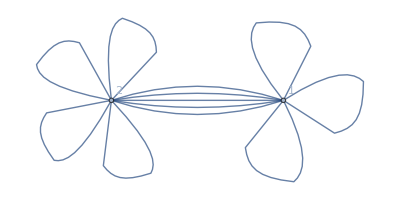

```mathematica
graph1=AdjacencyGraph[{{1,2},{2,3}}];
graph2=AdjacencyGraph[{{2,3},{3,1}}];
(*Get the adjacency matrices*)
adjMatrix1=Normal@AdjacencyMatrix[graph1];
adjMatrix2=Normal@AdjacencyMatrix[graph2];
(*Combine the adjacency matrices by element-wise addition*)
combinedAdjMatrix=adjMatrix1+adjMatrix2;
(*Create a new adjacency graph from the combined adjacency matrix*)
combinedGraph=AdjacencyGraph[combinedAdjMatrix];
(*Display the combined graph*)
GraphPlot[combinedGraph,VertexLabels->"Name"]
```

Let' s create the markov chain

```mathematica
MatrixForm[{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,1,1,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,1,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}}]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0)

```mathematica
AdjacencyGraph[{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,1,1,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,1,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}}]
```

-Graphics-

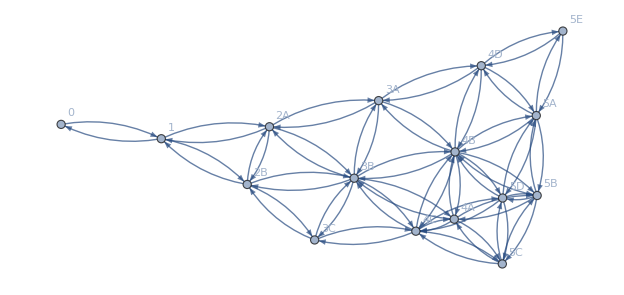

```mathematica
AdjacencyGraph[{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,1,0,1,0,0,0,0,0},{0,0,1,1,1,0,1,1,1,1,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,1,1,0,0,1,1,0,0},{0,0,0,0,1,1,0,1,0,1,1,1,1,0,1,0},{0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,0},{0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,1},{0,0,0,0,0,0,0,1,1,0,0,1,0,1,1,0},{0,0,0,0,0,0,0,1,0,1,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,1,1,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}},DirectedEdges->True,VertexLabels->{1->"0",2->"1",3->"2A",4->"2B",5->"3A",6->"3B",7->"3C",8->"4A",9->"4B",10->"4C",11->"4D",12->"5A",13->"5B",14->"5C",15->"5D",16->"5E"}]
```

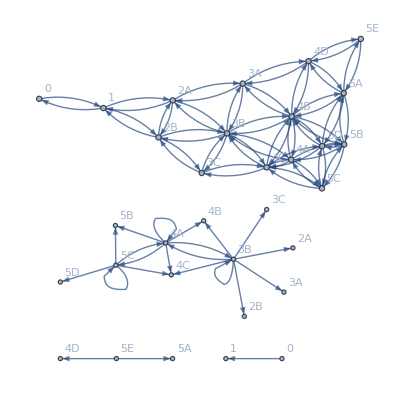

```mathematica
Show[{AdjacencyGraph[{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,1,1,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,1,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}},DirectedEdges->True,VertexLabels->{1->"0",2->"1",3->"2A",4->"2B",5->"3A",6->"3B",7->"3C",8->"4A",9->"4B",10->"4C",11->"4D",12->"5A",13->"5B",14->"5C",15->"5D",16->"5E"}],AdjacencyGraph[{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,1,0,1,0,0,0,0,0},{0,0,1,1,1,0,1,1,1,1,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,1,1,0,0,1,1,0,0},{0,0,0,0,1,1,0,1,0,1,1,1,1,0,1,0},{0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,0},{0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,1},{0,0,0,0,0,0,0,1,1,0,0,1,0,1,1,0},{0,0,0,0,0,0,0,1,0,1,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,1,1,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}},DirectedEdges->True,VertexLabels->{1->"0",2->"1",3->"2A",4->"2B",5->"3A",6->"3B",7->"3C",8->"4A",9->"4B",10->"4C",11->"4D",12->"5A",13->"5B",14->"5C",15->"5D",16->"5E"}]}]
```

Let' s check that we can eigendecompose the error matrix L1

```mathematica
γc=1
Transpose[Eigenvectors[L1five[γc]]].DiagonalMatrix[Eigenvalues[L1five[γc]]].Inverse[Transpose[Eigenvectors[L1five[γc]]]]//MatrixForm
Transpose[Eigenvectors[L1five[γc]]].DiagonalMatrix[Eigenvalues[L1five[γc]]].Inverse[Transpose[Eigenvectors[L1five[γc]]]]==L1five[γc]
```

1

(-15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15 | -13 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | -15 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 | 4 | -13 | 0 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | -15 | 1 | 0 | 0 | 1 | 0 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 6 | 6 | -12 | 6 | 4 | 3 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 2 | -15 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | -15 | 3 | 2 | 0 | 0 | 3 | 1 | 0 | 0
0 | 0 | 0 | 0 | 4 | 2 | 0 | 4 | -14 | 2 | 8 | 4 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 2 | 6 | 4 | 3 | -11 | 0 | 0 | 0 | 4 | 3 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | -15 | 1 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | -14 | 2 | 0 | 2 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 4 | -12 | 2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 3 | -11 | 6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 4 | 2 | 4 | -15 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | -15)

True

### Markovian case

```mathematica
ηc=1
γc=1
Transpose[Eigenvectors[L1five[γc]]].DiagonalMatrix[Eigenvalues[L1five[γc]]].Inverse[Transpose[Eigenvectors[L1five[γc]]]]
MatrixExp[L1five[γc]t]//MatrixForm
FullSimplify[MatrixExp[L1five[γc]t]][[1,1]]
```

1

1

{{-15,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{15,-13,2,2,0,0,0,0,0,0,0,0,0,0,0,0},{0,4,-15,2,3,1,0,0,0,0,0,0,0,0,0,0},{0,8,4,-13,0,2,3,0,0,0,0,0,0,0,0,0},{0,0,3,0,-15,1,0,0,1,0,4,0,0,0,0,0},{0,0,6,6,6,-12,6,4,3,2,0,0,0,0,0,0},{0,0,0,3,0,2,-15,0,0,2,0,0,0,0,0,0},{0,0,0,0,0,2,0,-15,3,2,0,0,3,1,0,0},{0,0,0,0,4,2,0,4,-14,2,8,4,2,0,2,0},{0,0,0,0,0,2,6,4,3,-11,0,0,0,4,3,0},{0,0,0,0,2,0,0,0,1,0,-15,1,0,0,0,5},{0,0,0,0,0,0,0,0,1,0,2,-14,2,0,2,10},{0,0,0,0,0,0,0,2,1,0,0,4,-12,2,2,0},{0,0,0,0,0,0,0,1,0,2,0,0,3,-11,6,0},{0,0,0,0,0,0,0,0,1,1,0,4,2,4,-15,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,-15}}

((ⅇ^(-20 t) (3+ⅇ^(4 t))^5)/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t)) (3+ⅇ^(4 t))^4)/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (3+ⅇ^(4 t))^3)/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (3+ⅇ^(4 t))^3)/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (3+ⅇ^(4 t))^2)/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (3+ⅇ^(4 t))^2)/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (3+ⅇ^(4 t))^2)/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (3+ⅇ^(4 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (3+ⅇ^(4 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (3+ⅇ^(4 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (3+ⅇ^(4 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^5)/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^5)/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^5)/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^5)/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^5)/1024
(15 ⅇ^(-20 t) (-1+ⅇ^(4 t)) (3+ⅇ^(4 t))^4)/1024 | (ⅇ^(-20 t) (3+ⅇ^(4 t))^3 (15-14 ⅇ^(4 t)+15 ⅇ^(8 t)))/1024 | (ⅇ^(-20 t) (3+ⅇ^(4 t))^2 (-15+13 ⅇ^(4 t)-13 ⅇ^(8 t)+15 ⅇ^(12 t)))/1024 | (ⅇ^(-20 t) (3+ⅇ^(4 t))^2 (-15+13 ⅇ^(4 t)-13 ⅇ^(8 t)+15 ⅇ^(12 t)))/1024 | (3 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (15+23 ⅇ^(4 t)+21 ⅇ^(8 t)+5 ⅇ^(12 t)))/1024 | (3 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (15+23 ⅇ^(4 t)+21 ⅇ^(8 t)+5 ⅇ^(12 t)))/1024 | (3 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (15+23 ⅇ^(4 t)+21 ⅇ^(8 t)+5 ⅇ^(12 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (15+34 ⅇ^(4 t)+15 ⅇ^(8 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (15+34 ⅇ^(4 t)+15 ⅇ^(8 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (15+34 ⅇ^(4 t)+15 ⅇ^(8 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (15+34 ⅇ^(4 t)+15 ⅇ^(8 t)))/1024 | (5 ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (1+3 ⅇ^(4 t)))/1024 | (5 ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (1+3 ⅇ^(4 t)))/1024 | (5 ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (1+3 ⅇ^(4 t)))/1024 | (5 ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (1+3 ⅇ^(4 t)))/1024 | (5 ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (1+3 ⅇ^(4 t)))/1024
15/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (3+ⅇ^(4 t))^3 | 1/512 ⅇ^(-20 t) (3+ⅇ^(4 t))^2 (-15+13 ⅇ^(4 t)-13 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (189+171 ⅇ^(4 t)+66 ⅇ^(8 t)+22 ⅇ^(12 t)+49 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/512 ⅇ^(-20 t) (-27-45 ⅇ^(4 t)-6 ⅇ^(8 t)+14 ⅇ^(12 t)+49 ⅇ^(16 t)+15 ⅇ^(20 t)) | 3/512 ⅇ^(-20 t) (-53+9 ⅇ^(4 t)+30 ⅇ^(8 t)+2 ⅇ^(12 t)+7 ⅇ^(16 t)+5 ⅇ^(20 t)) | 1/512 ⅇ^(-20 t) (-15-21 ⅇ^(4 t)+10 ⅇ^(8 t)-10 ⅇ^(12 t)+21 ⅇ^(16 t)+15 ⅇ^(20 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (19+23 ⅇ^(4 t)+17 ⅇ^(8 t)+5 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (5+21 ⅇ^(4 t)+23 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (29+29 ⅇ^(4 t)+23 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (-19+13 ⅇ^(4 t)+23 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (101+53 ⅇ^(4 t)+23 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (23+10 ⅇ^(4 t)+15 ⅇ^(8 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (7+10 ⅇ^(4 t)+15 ⅇ^(8 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (-9+10 ⅇ^(4 t)+15 ⅇ^(8 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (-1+10 ⅇ^(4 t)+15 ⅇ^(8 t)) | 5/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (11+2 ⅇ^(4 t)+3 ⅇ^(8 t))
15/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (3+ⅇ^(4 t))^3 | 1/256 ⅇ^(-20 t) (3+ⅇ^(4 t))^2 (-15+13 ⅇ^(4 t)-13 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/256 ⅇ^(-20 t) (-27-45 ⅇ^(4 t)-6 ⅇ^(8 t)+14 ⅇ^(12 t)+49 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (81+63 ⅇ^(4 t)+30 ⅇ^(8 t)+18 ⅇ^(12 t)+49 ⅇ^(16 t)+15 ⅇ^(20 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (19+23 ⅇ^(4 t)+17 ⅇ^(8 t)+5 ⅇ^(12 t)) | 1/256 ⅇ^(-20 t) (-15-21 ⅇ^(4 t)+10 ⅇ^(8 t)-10 ⅇ^(12 t)+21 ⅇ^(16 t)+15 ⅇ^(20 t)) | 3/256 ⅇ^(-20 t) (-17-3 ⅇ^(4 t)+10 ⅇ^(8 t)-2 ⅇ^(12 t)+7 ⅇ^(16 t)+5 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (5+21 ⅇ^(4 t)+23 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (-7+17 ⅇ^(4 t)+23 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (17+25 ⅇ^(4 t)+23 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (43+38 ⅇ^(4 t)+15 ⅇ^(8 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (-9+10 ⅇ^(4 t)+15 ⅇ^(8 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (-1+10 ⅇ^(4 t)+15 ⅇ^(8 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (7+10 ⅇ^(4 t)+15 ⅇ^(8 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (3+10 ⅇ^(4 t)+15 ⅇ^(8 t)) | 5/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (5+3 ⅇ^(4 t))
15/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (3+ⅇ^(4 t))^2 | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (15+23 ⅇ^(4 t)+21 ⅇ^(8 t)+5 ⅇ^(12 t)) | 3/512 ⅇ^(-20 t) (-53+9 ⅇ^(4 t)+30 ⅇ^(8 t)+2 ⅇ^(12 t)+7 ⅇ^(16 t)+5 ⅇ^(20 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (19+23 ⅇ^(4 t)+17 ⅇ^(8 t)+5 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (213+75 ⅇ^(4 t)+146 ⅇ^(8 t)+54 ⅇ^(12 t)+9 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/512 ⅇ^(-20 t) (-27-5 ⅇ^(4 t)+2 ⅇ^(8 t)+6 ⅇ^(12 t)+9 ⅇ^(16 t)+15 ⅇ^(20 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (-1+15 ⅇ^(4 t)+13 ⅇ^(8 t)+5 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (41+45 ⅇ^(4 t)+27 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (-15-29 ⅇ^(4 t)+2 ⅇ^(8 t)+30 ⅇ^(12 t)-3 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (1+21 ⅇ^(4 t)+27 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (-183-5 ⅇ^(4 t)+74 ⅇ^(8 t)+102 ⅇ^(12 t)-3 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (29+69 ⅇ^(4 t)+15 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (-19+21 ⅇ^(4 t)+15 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (1+10 ⅇ^(4 t)+5 ⅇ^(8 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (5-3 ⅇ^(4 t)+15 ⅇ^(8 t)+15 ⅇ^(12 t)) | 5/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (25+33 ⅇ^(4 t)+3 ⅇ^(8 t)+3 ⅇ^(12 t))
45/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (3+ⅇ^(4 t))^2 | 9/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (15+23 ⅇ^(4 t)+21 ⅇ^(8 t)+5 ⅇ^(12 t)) | 3/256 ⅇ^(-20 t) (-15-21 ⅇ^(4 t)+10 ⅇ^(8 t)-10 ⅇ^(12 t)+21 ⅇ^(16 t)+15 ⅇ^(20 t)) | 3/256 ⅇ^(-20 t) (-15-21 ⅇ^(4 t)+10 ⅇ^(8 t)-10 ⅇ^(12 t)+21 ⅇ^(16 t)+15 ⅇ^(20 t)) | 3/256 ⅇ^(-20 t) (-27-5 ⅇ^(4 t)+2 ⅇ^(8 t)+6 ⅇ^(12 t)+9 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (63+81 ⅇ^(4 t)+22 ⅇ^(8 t)+18 ⅇ^(12 t)+27 ⅇ^(16 t)+45 ⅇ^(20 t)) | 3/256 ⅇ^(-20 t) (-27-5 ⅇ^(4 t)+2 ⅇ^(8 t)+6 ⅇ^(12 t)+9 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (-69+17 ⅇ^(4 t)-2 ⅇ^(8 t)+18 ⅇ^(12 t)-9 ⅇ^(16 t)+45 ⅇ^(20 t)) | 3/256 ⅇ^(-20 t) (-7-5 ⅇ^(4 t)-6 ⅇ^(8 t)+6 ⅇ^(12 t)-3 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (27-47 ⅇ^(4 t)-34 ⅇ^(8 t)+18 ⅇ^(12 t)-9 ⅇ^(16 t)+45 ⅇ^(20 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (41+45 ⅇ^(4 t)+27 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (-3+5 ⅇ^(4 t)+15 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (13+5 ⅇ^(4 t)+15 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (-3+5 ⅇ^(4 t)+15 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (-3+5 ⅇ^(4 t)+15 ⅇ^(8 t)+15 ⅇ^(12 t)) | 15/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (7+6 ⅇ^(4 t)+3 ⅇ^(8 t))
15/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (3+ⅇ^(4 t))^2 | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (15+23 ⅇ^(4 t)+21 ⅇ^(8 t)+5 ⅇ^(12 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (19+23 ⅇ^(4 t)+17 ⅇ^(8 t)+5 ⅇ^(12 t)) | 3/256 ⅇ^(-20 t) (-17-3 ⅇ^(4 t)+10 ⅇ^(8 t)-2 ⅇ^(12 t)+7 ⅇ^(16 t)+5 ⅇ^(20 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (-1+15 ⅇ^(4 t)+13 ⅇ^(8 t)+5 ⅇ^(12 t)) | 1/256 ⅇ^(-20 t) (-27-5 ⅇ^(4 t)+2 ⅇ^(8 t)+6 ⅇ^(12 t)+9 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (105+63 ⅇ^(4 t)+46 ⅇ^(8 t)+18 ⅇ^(12 t)+9 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (41+45 ⅇ^(4 t)+27 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (7+11 ⅇ^(4 t)+9 ⅇ^(8 t)+5 ⅇ^(12 t)) | 1/256 ⅇ^(-20 t) (-35-ⅇ^(4 t)+6 ⅇ^(8 t)+18 ⅇ^(12 t)-3 ⅇ^(16 t)+15 ⅇ^(20 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (13+14 ⅇ^(4 t)+5 ⅇ^(8 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (1+10 ⅇ^(4 t)+5 ⅇ^(8 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (9+10 ⅇ^(4 t)+5 ⅇ^(8 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (13+21 ⅇ^(4 t)+15 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (3+3 ⅇ^(4 t)+5 ⅇ^(8 t)+5 ⅇ^(12 t)) | 15/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (3+ⅇ^(4 t))
45/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (3+ⅇ^(4 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (15+34 ⅇ^(4 t)+15 ⅇ^(8 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (5+21 ⅇ^(4 t)+23 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (5+21 ⅇ^(4 t)+23 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (41+45 ⅇ^(4 t)+27 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (-69+17 ⅇ^(4 t)-2 ⅇ^(8 t)+18 ⅇ^(12 t)-9 ⅇ^(16 t)+45 ⅇ^(20 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (41+45 ⅇ^(4 t)+27 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (215+113 ⅇ^(4 t)+118 ⅇ^(8 t)+18 ⅇ^(12 t)+3 ⅇ^(16 t)+45 ⅇ^(20 t)) | 3/512 ⅇ^(-20 t) (-35-5 ⅇ^(4 t)+18 ⅇ^(8 t)+6 ⅇ^(12 t)+ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/512 ⅇ^(-20 t) (-41-15 ⅇ^(4 t)-10 ⅇ^(8 t)+18 ⅇ^(12 t)+3 ⅇ^(16 t)+45 ⅇ^(20 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (29+53 ⅇ^(4 t)+31 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (33+45 ⅇ^(4 t)+35 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/512 ⅇ^(-20 t) (-31-21 ⅇ^(4 t)+42 ⅇ^(8 t)-10 ⅇ^(12 t)+5 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/512 ⅇ^(-20 t) (-29+65 ⅇ^(4 t)-66 ⅇ^(8 t)-30 ⅇ^(12 t)+15 ⅇ^(16 t)+45 ⅇ^(20 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (33+45 ⅇ^(4 t)+35 ⅇ^(8 t)+15 ⅇ^(12 t)) | 15/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (19+10 ⅇ^(4 t)+3 ⅇ^(8 t))
15/128 ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (3+ⅇ^(4 t)) | 1/128 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (15+34 ⅇ^(4 t)+15 ⅇ^(8 t)) | 1/128 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (29+29 ⅇ^(4 t)+23 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/128 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (-7+17 ⅇ^(4 t)+23 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/128 ⅇ^(-20 t) (-15-29 ⅇ^(4 t)+2 ⅇ^(8 t)+30 ⅇ^(12 t)-3 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/128 ⅇ^(-20 t) (-7-5 ⅇ^(4 t)-6 ⅇ^(8 t)+6 ⅇ^(12 t)-3 ⅇ^(16 t)+15 ⅇ^(20 t)) | 3/128 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (7+11 ⅇ^(4 t)+9 ⅇ^(8 t)+5 ⅇ^(12 t)) | 1/128 ⅇ^(-20 t) (-35-5 ⅇ^(4 t)+18 ⅇ^(8 t)+6 ⅇ^(12 t)+ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/128 ⅇ^(-20 t) (49+31 ⅇ^(4 t)+14 ⅇ^(8 t)+18 ⅇ^(12 t)+ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/128 ⅇ^(-20 t) (-7-9 ⅇ^(4 t)+6 ⅇ^(8 t)-6 ⅇ^(12 t)+ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/128 ⅇ^(-20 t) (-83+11 ⅇ^(4 t)+2 ⅇ^(8 t)+54 ⅇ^(12 t)+ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/128 ⅇ^(-20 t) (-31+11 ⅇ^(4 t)-22 ⅇ^(8 t)+22 ⅇ^(12 t)+5 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/128 ⅇ^(-20 t) (9-29 ⅇ^(4 t)+2 ⅇ^(8 t)-2 ⅇ^(12 t)+5 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/128 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (17+29 ⅇ^(4 t)+35 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/128 ⅇ^(-20 t) (-27+31 ⅇ^(4 t)-10 ⅇ^(8 t)-14 ⅇ^(12 t)+5 ⅇ^(16 t)+15 ⅇ^(20 t)) | 5/128 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (29+25 ⅇ^(4 t)+7 ⅇ^(8 t)+3 ⅇ^(12 t))
45/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (3+ⅇ^(4 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (15+34 ⅇ^(4 t)+15 ⅇ^(8 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (-19+13 ⅇ^(4 t)+23 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (17+25 ⅇ^(4 t)+23 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (1+21 ⅇ^(4 t)+27 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/256 ⅇ^(-20 t) (27-47 ⅇ^(4 t)-34 ⅇ^(8 t)+18 ⅇ^(12 t)-9 ⅇ^(16 t)+45 ⅇ^(20 t)) | 3/256 ⅇ^(-20 t) (-35-ⅇ^(4 t)+6 ⅇ^(8 t)+18 ⅇ^(12 t)-3 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (-41-15 ⅇ^(4 t)-10 ⅇ^(8 t)+18 ⅇ^(12 t)+3 ⅇ^(16 t)+45 ⅇ^(20 t)) | 3/256 ⅇ^(-20 t) (-7-9 ⅇ^(4 t)+6 ⅇ^(8 t)-6 ⅇ^(12 t)+ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (35+61 ⅇ^(4 t)+58 ⅇ^(8 t)+54 ⅇ^(12 t)+3 ⅇ^(16 t)+45 ⅇ^(20 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (13+5 ⅇ^(4 t)+31 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (1+13 ⅇ^(4 t)+35 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (9+37 ⅇ^(4 t)+35 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/256 ⅇ^(-20 t) (-13-47 ⅇ^(4 t)-18 ⅇ^(8 t)+18 ⅇ^(12 t)+15 ⅇ^(16 t)+45 ⅇ^(20 t)) | 3/256 ⅇ^(-20 t) (-3-9 ⅇ^(4 t)-2 ⅇ^(8 t)-6 ⅇ^(12 t)+5 ⅇ^(16 t)+15 ⅇ^(20 t)) | 15/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (3+10 ⅇ^(4 t)+3 ⅇ^(8 t))
(15 ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (3+ⅇ^(4 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (15+34 ⅇ^(4 t)+15 ⅇ^(8 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (101+53 ⅇ^(4 t)+23 ⅇ^(8 t)+15 ⅇ^(12 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (43+38 ⅇ^(4 t)+15 ⅇ^(8 t)))/1024 | (ⅇ^(-20 t) (-183-5 ⅇ^(4 t)+74 ⅇ^(8 t)+102 ⅇ^(12 t)-3 ⅇ^(16 t)+15 ⅇ^(20 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (41+45 ⅇ^(4 t)+27 ⅇ^(8 t)+15 ⅇ^(12 t)))/1024 | (3 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (13+14 ⅇ^(4 t)+5 ⅇ^(8 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (29+53 ⅇ^(4 t)+31 ⅇ^(8 t)+15 ⅇ^(12 t)))/1024 | (ⅇ^(-20 t) (-83+11 ⅇ^(4 t)+2 ⅇ^(8 t)+54 ⅇ^(12 t)+ⅇ^(16 t)+15 ⅇ^(20 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (13+5 ⅇ^(4 t)+31 ⅇ^(8 t)+15 ⅇ^(12 t)))/1024 | (ⅇ^(-20 t) (349+315 ⅇ^(4 t)+146 ⅇ^(8 t)+198 ⅇ^(12 t)+ⅇ^(16 t)+15 ⅇ^(20 t)))/1024 | (ⅇ^(-20 t) (33-149 ⅇ^(4 t)-22 ⅇ^(8 t)+118 ⅇ^(12 t)+5 ⅇ^(16 t)+15 ⅇ^(20 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (1+77 ⅇ^(4 t)+35 ⅇ^(8 t)+15 ⅇ^(12 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (31+50 ⅇ^(4 t)+15 ⅇ^(8 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (49+29 ⅇ^(4 t)+35 ⅇ^(8 t)+15 ⅇ^(12 t)))/1024 | (5 ⅇ^(-20 t) (-83-17 ⅇ^(4 t)+34 ⅇ^(8 t)+62 ⅇ^(12 t)+ⅇ^(16 t)+3 ⅇ^(20 t)))/1024
15/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^5 | 5/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (1+3 ⅇ^(4 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (23+10 ⅇ^(4 t)+15 ⅇ^(8 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (-9+10 ⅇ^(4 t)+15 ⅇ^(8 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (29+69 ⅇ^(4 t)+15 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (-3+5 ⅇ^(4 t)+15 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (1+10 ⅇ^(4 t)+5 ⅇ^(8 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (33+45 ⅇ^(4 t)+35 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (-31+11 ⅇ^(4 t)-22 ⅇ^(8 t)+22 ⅇ^(12 t)+5 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (1+13 ⅇ^(4 t)+35 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (33-149 ⅇ^(4 t)-22 ⅇ^(8 t)+118 ⅇ^(12 t)+5 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/512 ⅇ^(-20 t) (181+91 ⅇ^(4 t)+98 ⅇ^(8 t)+102 ⅇ^(12 t)+25 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/512 ⅇ^(-20 t) (-43-37 ⅇ^(4 t)+2 ⅇ^(8 t)+38 ⅇ^(12 t)+25 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (53+69 ⅇ^(4 t)+55 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (-107+59 ⅇ^(4 t)+2 ⅇ^(8 t)+6 ⅇ^(12 t)+25 ⅇ^(16 t)+15 ⅇ^(20 t)) | 5/512 ⅇ^(-20 t) (-79-33 ⅇ^(4 t)+58 ⅇ^(8 t)+46 ⅇ^(12 t)+5 ⅇ^(16 t)+3 ⅇ^(20 t))
15/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^5 | 5/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (1+3 ⅇ^(4 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (7+10 ⅇ^(4 t)+15 ⅇ^(8 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (-1+10 ⅇ^(4 t)+15 ⅇ^(8 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (-19+21 ⅇ^(4 t)+15 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (13+5 ⅇ^(4 t)+15 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (9+10 ⅇ^(4 t)+5 ⅇ^(8 t)) | 1/256 ⅇ^(-20 t) (-31-21 ⅇ^(4 t)+42 ⅇ^(8 t)-10 ⅇ^(12 t)+5 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (9-29 ⅇ^(4 t)+2 ⅇ^(8 t)-2 ⅇ^(12 t)+5 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (9+37 ⅇ^(4 t)+35 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (1+77 ⅇ^(4 t)+35 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/256 ⅇ^(-20 t) (-43-37 ⅇ^(4 t)+2 ⅇ^(8 t)+38 ⅇ^(12 t)+25 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (21+75 ⅇ^(4 t)+98 ⅇ^(8 t)+22 ⅇ^(12 t)+25 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (-11-5 ⅇ^(4 t)-30 ⅇ^(8 t)+6 ⅇ^(12 t)+25 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (13-45 ⅇ^(4 t)-22 ⅇ^(8 t)+14 ⅇ^(12 t)+25 ⅇ^(16 t)+15 ⅇ^(20 t)) | 5/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (17+33 ⅇ^(4 t)+11 ⅇ^(8 t)+3 ⅇ^(12 t))
45/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^5 | 15/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (1+3 ⅇ^(4 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (-9+10 ⅇ^(4 t)+15 ⅇ^(8 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (7+10 ⅇ^(4 t)+15 ⅇ^(8 t)) | 9/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (1+10 ⅇ^(4 t)+5 ⅇ^(8 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (-3+5 ⅇ^(4 t)+15 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (13+21 ⅇ^(4 t)+15 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (-29+65 ⅇ^(4 t)-66 ⅇ^(8 t)-30 ⅇ^(12 t)+15 ⅇ^(16 t)+45 ⅇ^(20 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (17+29 ⅇ^(4 t)+35 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/512 ⅇ^(-20 t) (-13-47 ⅇ^(4 t)-18 ⅇ^(8 t)+18 ⅇ^(12 t)+15 ⅇ^(16 t)+45 ⅇ^(20 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (31+50 ⅇ^(4 t)+15 ⅇ^(8 t)) | 3/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (53+69 ⅇ^(4 t)+55 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/512 ⅇ^(-20 t) (-11-5 ⅇ^(4 t)-30 ⅇ^(8 t)+6 ⅇ^(12 t)+25 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/512 ⅇ^(-20 t) (95+81 ⅇ^(4 t)+102 ⅇ^(8 t)+114 ⅇ^(12 t)+75 ⅇ^(16 t)+45 ⅇ^(20 t)) | 3/512 ⅇ^(-20 t) (-59-21 ⅇ^(4 t)+18 ⅇ^(8 t)+22 ⅇ^(12 t)+25 ⅇ^(16 t)+15 ⅇ^(20 t)) | 15/512 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (15+14 ⅇ^(4 t)+3 ⅇ^(8 t))
15/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^5 | 5/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (1+3 ⅇ^(4 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (-1+10 ⅇ^(4 t)+15 ⅇ^(8 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (3+10 ⅇ^(4 t)+15 ⅇ^(8 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (5-3 ⅇ^(4 t)+15 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (-3+5 ⅇ^(4 t)+15 ⅇ^(8 t)+15 ⅇ^(12 t)) | 3/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (3+3 ⅇ^(4 t)+5 ⅇ^(8 t)+5 ⅇ^(12 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (33+45 ⅇ^(4 t)+35 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/256 ⅇ^(-20 t) (-27+31 ⅇ^(4 t)-10 ⅇ^(8 t)-14 ⅇ^(12 t)+5 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (-3-9 ⅇ^(4 t)-2 ⅇ^(8 t)-6 ⅇ^(12 t)+5 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (49+29 ⅇ^(4 t)+35 ⅇ^(8 t)+15 ⅇ^(12 t)) | 1/256 ⅇ^(-20 t) (-107+59 ⅇ^(4 t)+2 ⅇ^(8 t)+6 ⅇ^(12 t)+25 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (13-45 ⅇ^(4 t)-22 ⅇ^(8 t)+14 ⅇ^(12 t)+25 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (-59-21 ⅇ^(4 t)+18 ⅇ^(8 t)+22 ⅇ^(12 t)+25 ⅇ^(16 t)+15 ⅇ^(20 t)) | 1/256 ⅇ^(-20 t) (121+63 ⅇ^(4 t)+14 ⅇ^(8 t)+18 ⅇ^(12 t)+25 ⅇ^(16 t)+15 ⅇ^(20 t)) | 5/256 ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (33+17 ⅇ^(4 t)+11 ⅇ^(8 t)+3 ⅇ^(12 t))
(3 ⅇ^(-20 t) (-1+ⅇ^(4 t))^5)/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (1+3 ⅇ^(4 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (11+2 ⅇ^(4 t)+3 ⅇ^(8 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (5+3 ⅇ^(4 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (25+33 ⅇ^(4 t)+3 ⅇ^(8 t)+3 ⅇ^(12 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (7+6 ⅇ^(4 t)+3 ⅇ^(8 t)))/1024 | (3 ⅇ^(-20 t) (-1+ⅇ^(4 t))^4 (3+ⅇ^(4 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (19+10 ⅇ^(4 t)+3 ⅇ^(8 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (29+25 ⅇ^(4 t)+7 ⅇ^(8 t)+3 ⅇ^(12 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (3+10 ⅇ^(4 t)+3 ⅇ^(8 t)))/1024 | (ⅇ^(-20 t) (-83-17 ⅇ^(4 t)+34 ⅇ^(8 t)+62 ⅇ^(12 t)+ⅇ^(16 t)+3 ⅇ^(20 t)))/1024 | (ⅇ^(-20 t) (-79-33 ⅇ^(4 t)+58 ⅇ^(8 t)+46 ⅇ^(12 t)+5 ⅇ^(16 t)+3 ⅇ^(20 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (17+33 ⅇ^(4 t)+11 ⅇ^(8 t)+3 ⅇ^(12 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^3 (15+14 ⅇ^(4 t)+3 ⅇ^(8 t)))/1024 | (ⅇ^(-20 t) (-1+ⅇ^(4 t))^2 (33+17 ⅇ^(4 t)+11 ⅇ^(8 t)+3 ⅇ^(12 t)))/1024 | (ⅇ^(-20 t) (241+415 ⅇ^(4 t)+250 ⅇ^(8 t)+110 ⅇ^(12 t)+5 ⅇ^(16 t)+3 ⅇ^(20 t)))/1024)

(ⅇ^(-20 t) (3+ⅇ^(4 t))^5)/1024

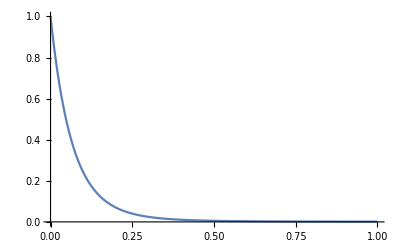

```mathematica
Plot[FullSimplify[MatrixExp[L1five[γc]t]][[1,1]],{t,0,1},PlotRange->{0,1}]
```

```mathematica
MatrixExp[(L0fivecorrect[ηc]+L1five[γc])t]//MatrixForm
```

$Aborted

```mathematica
q0MarkFive[η_,γ_,t_]:=MatrixExp[(L0fivecorrect[ηc]+L1five[γc])t][[1,1]]
```

```mathematica
LaplaceMatExp5[s_,γ_,η_]:=-s IdentityMatrix[16]+L0fivecorrect[η]+L1five[γ]
q0t5Markov[t_,γ_,η_]:=ResourceFunction["NInverseLaplaceTransform"][Inverse[-FullSimplify[LaplaceMatExp5[s,γ,η]]][[1, 1]],s,t]
```

```mathematica
q0t5Markov[1,γc,ηc]
```

0.00238127

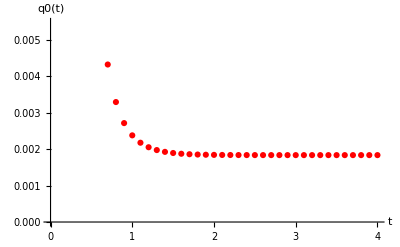

```mathematica
ListPlot[Table[{t,q0t5Markov[t,γc,ηc]},{t,0.1,4,0.1}],PlotStyle->Red,PlotMarkers->Automatic,AxesLabel->{"t","q0(t)"}]
```

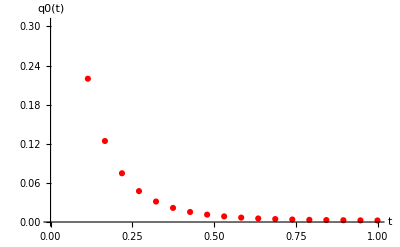

```mathematica
ListPlot[Table[{t,q0t5Markov[t,γc,ηc]},{t,0.01,1,0.052}],PlotStyle->Red,PlotMarkers->Automatic,AxesLabel->{"t","q0(t)"}]
```

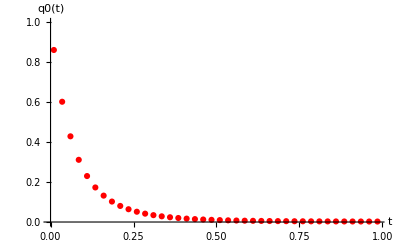

```mathematica
ListPlot[Table[{t,q0t5Markov[t,γc,ηc]},{t,.01,1,0.025}],PlotStyle->Red,PlotMarkers->Automatic,AxesLabel->{"t","q0(t)"},PlotRange->{0,1}]
```

```mathematica
q0t5Markov[0.2,γc,ηc]
```

0.0885608

### Post Markovian Master Equation incomplete

Now let’s creat the PMME for our incomplete problem

```mathematica
PmmeMat5ExpKernel[s_,γ_?NumericQ,η_?NumericQ,c_?NumericQ]:=-s IdentityMatrix[16]+L0fivecorrect[η]+(L1five[γ].Transpose[Eigenvectors[L1five[γ]]]).(DiagonalMatrix[{kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[1]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[2]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[3]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[4]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[5]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[6]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[7]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[8]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[9]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[10]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[11]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[12]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[13]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[14]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[15]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[16]]]}].Inverse[Transpose[Eigenvectors[L1five[γ]]]])
```

```mathematica
PmmeMat5ExpKernel[s,1,1,1]//MatrixForm
```

(-s-15/(256 (5+s))-45/(64 (9+s))-405/(128 (13+s))-405/(64 (17+s))-1215/(256 (21+s)) | 1-11/(256 (5+s))-21/(64 (9+s))-81/(128 (13+s))+27/(64 (17+s))+405/(256 (21+s)) | -7/(256 (5+s))-5/(64 (9+s))+27/(128 (13+s))+27/(64 (17+s))-135/(256 (21+s)) | -7/(256 (5+s))-5/(64 (9+s))+27/(128 (13+s))+27/(64 (17+s))-135/(256 (21+s)) | -3/(256 (5+s))+3/(64 (9+s))+15/(128 (13+s))-21/(64 (17+s))+45/(256 (21+s)) | -3/(256 (5+s))+3/(64 (9+s))+15/(128 (13+s))-21/(64 (17+s))+45/(256 (21+s)) | -3/(256 (5+s))+3/(64 (9+s))+15/(128 (13+s))-21/(64 (17+s))+45/(256 (21+s)) | 1/(256 (5+s))+3/(64 (9+s))-21/(128 (13+s))+11/(64 (17+s))-15/(256 (21+s)) | 1/(256 (5+s))+3/(64 (9+s))-21/(128 (13+s))+11/(64 (17+s))-15/(256 (21+s)) | 1/(256 (5+s))+3/(64 (9+s))-21/(128 (13+s))+11/(64 (17+s))-15/(256 (21+s)) | 1/(256 (5+s))+3/(64 (9+s))-21/(128 (13+s))+11/(64 (17+s))-15/(256 (21+s)) | 5/(256 (5+s))-5/(64 (9+s))+15/(128 (13+s))-5/(64 (17+s))+5/(256 (21+s)) | 5/(256 (5+s))-5/(64 (9+s))+15/(128 (13+s))-5/(64 (17+s))+5/(256 (21+s)) | 5/(256 (5+s))-5/(64 (9+s))+15/(128 (13+s))-5/(64 (17+s))+5/(256 (21+s)) | 5/(256 (5+s))-5/(64 (9+s))+15/(128 (13+s))-5/(64 (17+s))+5/(256 (21+s)) | 5/(256 (5+s))-5/(64 (9+s))+15/(128 (13+s))-5/(64 (17+s))+5/(256 (21+s))
-165/(256 (5+s))-315/(64 (9+s))-1215/(128 (13+s))+405/(64 (17+s))+6075/(256 (21+s)) | -1-s-121/(256 (5+s))-147/(64 (9+s))-243/(128 (13+s))-27/(64 (17+s))-2025/(256 (21+s)) | -77/(256 (5+s))-35/(64 (9+s))+81/(128 (13+s))-27/(64 (17+s))+675/(256 (21+s)) | -77/(256 (5+s))-35/(64 (9+s))+81/(128 (13+s))-27/(64 (17+s))+675/(256 (21+s)) | -33/(256 (5+s))+21/(64 (9+s))+45/(128 (13+s))+21/(64 (17+s))-225/(256 (21+s)) | -33/(256 (5+s))+21/(64 (9+s))+45/(128 (13+s))+21/(64 (17+s))-225/(256 (21+s)) | -33/(256 (5+s))+21/(64 (9+s))+45/(128 (13+s))+21/(64 (17+s))-225/(256 (21+s)) | 11/(256 (5+s))+21/(64 (9+s))-63/(128 (13+s))-11/(64 (17+s))+75/(256 (21+s)) | 11/(256 (5+s))+21/(64 (9+s))-63/(128 (13+s))-11/(64 (17+s))+75/(256 (21+s)) | 11/(256 (5+s))+21/(64 (9+s))-63/(128 (13+s))-11/(64 (17+s))+75/(256 (21+s)) | 11/(256 (5+s))+21/(64 (9+s))-63/(128 (13+s))-11/(64 (17+s))+75/(256 (21+s)) | 55/(256 (5+s))-35/(64 (9+s))+45/(128 (13+s))+5/(64 (17+s))-25/(256 (21+s)) | 55/(256 (5+s))-35/(64 (9+s))+45/(128 (13+s))+5/(64 (17+s))-25/(256 (21+s)) | 55/(256 (5+s))-35/(64 (9+s))+45/(128 (13+s))+5/(64 (17+s))-25/(256 (21+s)) | 55/(256 (5+s))-35/(64 (9+s))+45/(128 (13+s))+5/(64 (17+s))-25/(256 (21+s)) | 55/(256 (5+s))-35/(64 (9+s))+45/(128 (13+s))+5/(64 (17+s))-25/(256 (21+s))
-105/(128 (5+s))-75/(32 (9+s))+405/(64 (13+s))+405/(32 (17+s))-2025/(128 (21+s)) | -77/(128 (5+s))-35/(32 (9+s))+81/(64 (13+s))-27/(32 (17+s))+675/(128 (21+s)) | -1-s-49/(128 (5+s))-11/(32 (9+s))-99/(64 (13+s))-171/(32 (17+s))-945/(128 (21+s)) | -49/(128 (5+s))-7/(32 (9+s))+9/(64 (13+s))+45/(32 (17+s))+135/(128 (21+s)) | -21/(128 (5+s))-3/(32 (9+s))-135/(64 (13+s))-27/(32 (17+s))+795/(128 (21+s)) | -21/(128 (5+s))+5/(32 (9+s))-15/(64 (13+s))+21/(32 (17+s))+75/(128 (21+s)) | -21/(128 (5+s))+9/(32 (9+s))+45/(64 (13+s))+45/(32 (17+s))-285/(128 (21+s)) | 7/(128 (5+s))+5/(32 (9+s))+21/(64 (13+s))-11/(32 (17+s))-25/(128 (21+s)) | 7/(128 (5+s))+1/(32 (9+s))+9/(64 (13+s))+29/(32 (17+s))-145/(128 (21+s)) | 7/(128 (5+s))+9/(32 (9+s))+33/(64 (13+s))-51/(32 (17+s))+95/(128 (21+s)) | 7/(128 (5+s))-11/(32 (9+s))-27/(64 (13+s))+149/(32 (17+s))-505/(128 (21+s)) | 35/(128 (5+s))-19/(32 (9+s))+81/(64 (13+s))-59/(32 (17+s))+115/(128 (21+s)) | 35/(128 (5+s))-11/(32 (9+s))+9/(64 (13+s))-11/(32 (17+s))+35/(128 (21+s)) | 35/(128 (5+s))-3/(32 (9+s))-63/(64 (13+s))+37/(32 (17+s))-45/(128 (21+s)) | 35/(128 (5+s))-7/(32 (9+s))-27/(64 (13+s))+13/(32 (17+s))-5/(128 (21+s)) | 35/(128 (5+s))-35/(32 (9+s))+225/(64 (13+s))-155/(32 (17+s))+275/(128 (21+s))
-105/(64 (5+s))-75/(16 (9+s))+405/(32 (13+s))+405/(16 (17+s))-2025/(64 (21+s)) | -77/(64 (5+s))-35/(16 (9+s))+81/(32 (13+s))-27/(16 (17+s))+675/(64 (21+s)) | -49/(64 (5+s))-7/(16 (9+s))+9/(32 (13+s))+45/(16 (17+s))+135/(64 (21+s)) | -1-s-49/(64 (5+s))-9/(16 (9+s))-45/(32 (13+s))-63/(16 (17+s))-405/(64 (21+s)) | -21/(64 (5+s))+9/(16 (9+s))+45/(32 (13+s))+45/(16 (17+s))-285/(64 (21+s)) | -21/(64 (5+s))+5/(16 (9+s))-15/(32 (13+s))+21/(16 (17+s))+75/(64 (21+s)) | -21/(64 (5+s))+3/(16 (9+s))-45/(32 (13+s))+9/(16 (17+s))+255/(64 (21+s)) | 7/(64 (5+s))+5/(16 (9+s))+21/(32 (13+s))-11/(16 (17+s))-25/(64 (21+s)) | 7/(64 (5+s))+7/(16 (9+s))+27/(32 (13+s))-31/(16 (17+s))+35/(64 (21+s)) | 7/(64 (5+s))+3/(16 (9+s))+15/(32 (13+s))+9/(16 (17+s))-85/(64 (21+s)) | 7/(64 (5+s))+13/(16 (9+s))+45/(32 (13+s))-91/(16 (17+s))+215/(64 (21+s)) | 35/(64 (5+s))-3/(16 (9+s))-63/(32 (13+s))+37/(16 (17+s))-45/(64 (21+s)) | 35/(64 (5+s))-7/(16 (9+s))-27/(32 (13+s))+13/(16 (17+s))-5/(64 (21+s)) | 35/(64 (5+s))-11/(16 (9+s))+9/(32 (13+s))-11/(16 (17+s))+35/(64 (21+s)) | 35/(64 (5+s))-9/(16 (9+s))-9/(32 (13+s))+1/(16 (17+s))+15/(64 (21+s)) | 35/(64 (5+s))+5/(16 (9+s))-135/(32 (13+s))+85/(16 (17+s))-125/(64 (21+s))
-45/(128 (5+s))+45/(32 (9+s))+225/(64 (13+s))-315/(32 (17+s))+675/(128 (21+s)) | -33/(128 (5+s))+21/(32 (9+s))+45/(64 (13+s))+21/(32 (17+s))-225/(128 (21+s)) | -21/(128 (5+s))-3/(32 (9+s))-135/(64 (13+s))-27/(32 (17+s))+795/(128 (21+s)) | -21/(128 (5+s))+9/(32 (9+s))+45/(64 (13+s))+45/(32 (17+s))-285/(128 (21+s)) | -1-s-9/(128 (5+s))-27/(32 (9+s))-219/(64 (13+s))-75/(32 (17+s))-1065/(128 (21+s)) | -9/(128 (5+s))-3/(32 (9+s))-3/(64 (13+s))+5/(32 (17+s))+135/(128 (21+s)) | -9/(128 (5+s))+9/(32 (9+s))+81/(64 (13+s))-51/(32 (17+s))+15/(128 (21+s)) | 3/(128 (5+s))-3/(32 (9+s))+33/(64 (13+s))+37/(32 (17+s))-205/(128 (21+s)) | 3/(128 (5+s))-15/(32 (9+s))-3/(64 (13+s))+29/(32 (17+s))+75/(128 (21+s)) | 3/(128 (5+s))+9/(32 (9+s))+21/(64 (13+s))-19/(32 (17+s))-5/(128 (21+s)) | 3/(128 (5+s))-51/(32 (9+s))-111/(64 (13+s))+5/(32 (17+s))+915/(128 (21+s)) | 15/(128 (5+s))-27/(32 (9+s))+141/(64 (13+s))-11/(32 (17+s))-145/(128 (21+s)) | 15/(128 (5+s))-3/(32 (9+s))+69/(64 (13+s))-59/(32 (17+s))+95/(128 (21+s)) | 15/(128 (5+s))+21/(32 (9+s))-99/(64 (13+s))+21/(32 (17+s))+15/(128 (21+s)) | 15/(128 (5+s))+9/(32 (9+s))-39/(64 (13+s))+13/(32 (17+s))-25/(128 (21+s)) | 15/(128 (5+s))-75/(32 (9+s))+285/(64 (13+s))+85/(32 (17+s))-625/(128 (21+s))
-135/(64 (5+s))+135/(16 (9+s))+675/(32 (13+s))-945/(16 (17+s))+2025/(64 (21+s)) | -99/(64 (5+s))+63/(16 (9+s))+135/(32 (13+s))+63/(16 (17+s))-675/(64 (21+s)) | 1-63/(64 (5+s))+15/(16 (9+s))-45/(32 (13+s))+63/(16 (17+s))+225/(64 (21+s)) | 1-63/(64 (5+s))+15/(16 (9+s))-45/(32 (13+s))+63/(16 (17+s))+225/(64 (21+s)) | 1-27/(64 (5+s))-9/(16 (9+s))-9/(32 (13+s))+15/(16 (17+s))+405/(64 (21+s)) | -1/3-s-27/(64 (5+s))-9/(16 (9+s))-33/(32 (13+s))-81/(16 (17+s))-315/(64 (21+s)) | 1-27/(64 (5+s))-9/(16 (9+s))-9/(32 (13+s))+15/(16 (17+s))+405/(64 (21+s)) | 2/3+9/(64 (5+s))-9/(16 (9+s))+3/(32 (13+s))-17/(16 (17+s))+345/(64 (21+s)) | 1/2+9/(64 (5+s))-9/(16 (9+s))+27/(32 (13+s))+15/(16 (17+s))+105/(64 (21+s)) | 1/3+9/(64 (5+s))-9/(16 (9+s))+51/(32 (13+s))+47/(16 (17+s))-135/(64 (21+s)) | 9/(64 (5+s))-9/(16 (9+s))+99/(32 (13+s))+111/(16 (17+s))-615/(64 (21+s)) | 45/(64 (5+s))+15/(16 (9+s))-9/(32 (13+s))-33/(16 (17+s))+45/(64 (21+s)) | 45/(64 (5+s))+15/(16 (9+s))-81/(32 (13+s))+63/(16 (17+s))-195/(64 (21+s)) | 45/(64 (5+s))+15/(16 (9+s))-9/(32 (13+s))-33/(16 (17+s))+45/(64 (21+s)) | 45/(64 (5+s))+15/(16 (9+s))-9/(32 (13+s))-33/(16 (17+s))+45/(64 (21+s)) | 45/(64 (5+s))+15/(16 (9+s))+135/(32 (13+s))-225/(16 (17+s))+525/(64 (21+s))
-45/(64 (5+s))+45/(16 (9+s))+225/(32 (13+s))-315/(16 (17+s))+675/(64 (21+s)) | -33/(64 (5+s))+21/(16 (9+s))+45/(32 (13+s))+21/(16 (17+s))-225/(64 (21+s)) | -21/(64 (5+s))+9/(16 (9+s))+45/(32 (13+s))+45/(16 (17+s))-285/(64 (21+s)) | -21/(64 (5+s))+3/(16 (9+s))-45/(32 (13+s))+9/(16 (17+s))+255/(64 (21+s)) | -9/(64 (5+s))+9/(16 (9+s))+81/(32 (13+s))-51/(16 (17+s))+15/(64 (21+s)) | -9/(64 (5+s))-3/(16 (9+s))-3/(32 (13+s))+5/(16 (17+s))+135/(64 (21+s)) | -1-s-9/(64 (5+s))-9/(16 (9+s))-69/(32 (13+s))-63/(16 (17+s))-525/(64 (21+s)) | 3/(64 (5+s))-3/(16 (9+s))+33/(32 (13+s))+37/(16 (17+s))-205/(64 (21+s)) | 3/(64 (5+s))+3/(16 (9+s))+27/(32 (13+s))+9/(16 (17+s))-105/(64 (21+s)) | 3/(64 (5+s))-9/(16 (9+s))-9/(32 (13+s))+1/(16 (17+s))+175/(64 (21+s)) | 3/(64 (5+s))+21/(16 (9+s))+9/(32 (13+s))-75/(16 (17+s))+195/(64 (21+s)) | 15/(64 (5+s))+21/(16 (9+s))-99/(32 (13+s))+21/(16 (17+s))+15/(64 (21+s)) | 15/(64 (5+s))+9/(16 (9+s))+9/(32 (13+s))-51/(16 (17+s))+135/(64 (21+s)) | 15/(64 (5+s))-3/(16 (9+s))+21/(32 (13+s))+5/(16 (17+s))-65/(64 (21+s)) | 15/(64 (5+s))+3/(16 (9+s))-9/(32 (13+s))+9/(16 (17+s))-45/(64 (21+s)) | 15/(64 (5+s))+45/(16 (9+s))-315/(32 (13+s))+165/(16 (17+s))-225/(64 (21+s))
45/(128 (5+s))+135/(32 (9+s))-945/(64 (13+s))+495/(32 (17+s))-675/(128 (21+s)) | 33/(128 (5+s))+63/(32 (9+s))-189/(64 (13+s))-33/(32 (17+s))+225/(128 (21+s)) | 21/(128 (5+s))+15/(32 (9+s))+63/(64 (13+s))-33/(32 (17+s))-75/(128 (21+s)) | 21/(128 (5+s))+15/(32 (9+s))+63/(64 (13+s))-33/(32 (17+s))-75/(128 (21+s)) | 9/(128 (5+s))-9/(32 (9+s))+99/(64 (13+s))+111/(32 (17+s))-615/(128 (21+s)) | 1/3+9/(128 (5+s))-9/(32 (9+s))+3/(64 (13+s))-17/(32 (17+s))+345/(128 (21+s)) | 9/(128 (5+s))-9/(32 (9+s))+99/(64 (13+s))+111/(32 (17+s))-615/(128 (21+s)) | -5/6-s-3/(128 (5+s))-9/(32 (9+s))-177/(64 (13+s))-113/(32 (17+s))-1075/(128 (21+s)) | 1/2-3/(128 (5+s))-9/(32 (9+s))-81/(64 (13+s))+15/(32 (17+s))+525/(128 (21+s)) | 1/3-3/(128 (5+s))-9/(32 (9+s))+15/(64 (13+s))+15/(32 (17+s))+205/(128 (21+s)) | -3/(128 (5+s))-9/(32 (9+s))+207/(64 (13+s))+15/(32 (17+s))-435/(128 (21+s)) | -15/(128 (5+s))+15/(32 (9+s))+99/(64 (13+s))+63/(32 (17+s))-495/(128 (21+s)) | 1/2-15/(128 (5+s))+15/(32 (9+s))-189/(64 (13+s))+63/(32 (17+s))+465/(128 (21+s)) | 1/6-15/(128 (5+s))+15/(32 (9+s))+99/(64 (13+s))-65/(32 (17+s))+145/(128 (21+s)) | -15/(128 (5+s))+15/(32 (9+s))+99/(64 (13+s))+63/(32 (17+s))-495/(128 (21+s)) | -15/(128 (5+s))+15/(32 (9+s))+675/(64 (13+s))-705/(32 (17+s))+1425/(128 (21+s))
15/(32 (5+s))+45/(8 (9+s))-315/(16 (13+s))+165/(8 (17+s))-225/(32 (21+s)) | 11/(32 (5+s))+21/(8 (9+s))-63/(16 (13+s))-11/(8 (17+s))+75/(32 (21+s)) | 7/(32 (5+s))+1/(8 (9+s))+9/(16 (13+s))+29/(8 (17+s))-145/(32 (21+s)) | 7/(32 (5+s))+7/(8 (9+s))+27/(16 (13+s))-31/(8 (17+s))+35/(32 (21+s)) | 3/(32 (5+s))-15/(8 (9+s))-3/(16 (13+s))+29/(8 (17+s))+75/(32 (21+s)) | 3/(32 (5+s))-3/(8 (9+s))+9/(16 (13+s))+5/(8 (17+s))+35/(32 (21+s)) | 3/(32 (5+s))+3/(8 (9+s))+27/(16 (13+s))+9/(8 (17+s))-105/(32 (21+s)) | -1/(32 (5+s))-3/(8 (9+s))-27/(16 (13+s))+5/(8 (17+s))+175/(32 (21+s)) | -1-s-1/(32 (5+s))-9/(8 (9+s))-21/(16 (13+s))-31/(8 (17+s))-245/(32 (21+s)) | -1/(32 (5+s))+3/(8 (9+s))-9/(16 (13+s))+9/(8 (17+s))+35/(32 (21+s)) | -1/(32 (5+s))-27/(8 (9+s))-3/(16 (13+s))-11/(8 (17+s))+415/(32 (21+s)) | -5/(32 (5+s))-11/(8 (9+s))+33/(16 (13+s))-11/(8 (17+s))+155/(32 (21+s)) | -5/(32 (5+s))+1/(8 (9+s))-3/(16 (13+s))+29/(8 (17+s))-45/(32 (21+s)) | -5/(32 (5+s))+13/(8 (9+s))+9/(16 (13+s))+5/(8 (17+s))-85/(32 (21+s)) | -5/(32 (5+s))+7/(8 (9+s))+15/(16 (13+s))-31/(8 (17+s))+135/(32 (21+s)) | -5/(32 (5+s))-35/(8 (9+s))+105/(16 (13+s))+165/(8 (17+s))-725/(32 (21+s))
45/(64 (5+s))+135/(16 (9+s))-945/(32 (13+s))+495/(16 (17+s))-675/(64 (21+s)) | 33/(64 (5+s))+63/(16 (9+s))-189/(32 (13+s))-33/(16 (17+s))+225/(64 (21+s)) | 21/(64 (5+s))+27/(16 (9+s))+99/(32 (13+s))-153/(16 (17+s))+285/(64 (21+s)) | 21/(64 (5+s))+9/(16 (9+s))+45/(32 (13+s))+27/(16 (17+s))-255/(64 (21+s)) | 9/(64 (5+s))+27/(16 (9+s))+63/(32 (13+s))-57/(16 (17+s))-15/(64 (21+s)) | 9/(64 (5+s))-9/(16 (9+s))+51/(32 (13+s))+47/(16 (17+s))-135/(64 (21+s)) | 9/(64 (5+s))-27/(16 (9+s))-27/(32 (13+s))+3/(16 (17+s))+525/(64 (21+s)) | -3/(64 (5+s))-9/(16 (9+s))+15/(32 (13+s))+15/(16 (17+s))+205/(64 (21+s)) | -3/(64 (5+s))+9/(16 (9+s))-27/(32 (13+s))+27/(16 (17+s))+105/(64 (21+s)) | -1-s-3/(64 (5+s))-27/(16 (9+s))-87/(32 (13+s))-61/(16 (17+s))-175/(64 (21+s)) | -3/(64 (5+s))+63/(16 (9+s))-153/(32 (13+s))+63/(16 (17+s))-195/(64 (21+s)) | -15/(64 (5+s))+63/(16 (9+s))-45/(32 (13+s))-33/(16 (17+s))-15/(64 (21+s)) | -15/(64 (5+s))+27/(16 (9+s))+135/(32 (13+s))-57/(16 (17+s))-135/(64 (21+s)) | -15/(64 (5+s))-9/(16 (9+s))+27/(32 (13+s))+47/(16 (17+s))+65/(64 (21+s)) | -15/(64 (5+s))+9/(16 (9+s))+9/(32 (13+s))+27/(16 (17+s))+45/(64 (21+s)) | -15/(64 (5+s))+135/(16 (9+s))-405/(32 (13+s))+15/(16 (17+s))+225/(64 (21+s))
15/(256 (5+s))+45/(64 (9+s))-315/(128 (13+s))+165/(64 (17+s))-225/(256 (21+s)) | 11/(256 (5+s))+21/(64 (9+s))-63/(128 (13+s))-11/(64 (17+s))+75/(256 (21+s)) | 7/(256 (5+s))-11/(64 (9+s))-27/(128 (13+s))+149/(64 (17+s))-505/(256 (21+s)) | 7/(256 (5+s))+13/(64 (9+s))+45/(128 (13+s))-91/(64 (17+s))+215/(256 (21+s)) | 3/(256 (5+s))-51/(64 (9+s))-111/(128 (13+s))+5/(64 (17+s))+915/(256 (21+s)) | 3/(256 (5+s))-3/(64 (9+s))+33/(128 (13+s))+37/(64 (17+s))-205/(256 (21+s)) | 3/(256 (5+s))+21/(64 (9+s))+9/(128 (13+s))-75/(64 (17+s))+195/(256 (21+s)) | -1/(256 (5+s))-3/(64 (9+s))+69/(128 (13+s))+5/(64 (17+s))-145/(256 (21+s)) | -1/(256 (5+s))-27/(64 (9+s))-3/(128 (13+s))-11/(64 (17+s))+415/(256 (21+s)) | -1/(256 (5+s))+21/(64 (9+s))-51/(128 (13+s))+21/(64 (17+s))-65/(256 (21+s)) | -1-s-1/(256 (5+s))-99/(64 (9+s))-219/(128 (13+s))-315/(64 (17+s))-1745/(256 (21+s)) | -5/(256 (5+s))-59/(64 (9+s))+33/(128 (13+s))+149/(64 (17+s))-165/(256 (21+s)) | -5/(256 (5+s))-11/(64 (9+s))+177/(128 (13+s))-75/(64 (17+s))-5/(256 (21+s)) | -5/(256 (5+s))+37/(64 (9+s))-63/(128 (13+s))-43/(64 (17+s))+155/(256 (21+s)) | -5/(256 (5+s))+13/(64 (9+s))-39/(128 (13+s))+69/(64 (17+s))-245/(256 (21+s)) | -5/(256 (5+s))-155/(64 (9+s))-255/(128 (13+s))+85/(64 (17+s))+2075/(256 (21+s))
75/(128 (5+s))-75/(32 (9+s))+225/(64 (13+s))-75/(32 (17+s))+75/(128 (21+s)) | 55/(128 (5+s))-35/(32 (9+s))+45/(64 (13+s))+5/(32 (17+s))-25/(128 (21+s)) | 35/(128 (5+s))-19/(32 (9+s))+81/(64 (13+s))-59/(32 (17+s))+115/(128 (21+s)) | 35/(128 (5+s))-3/(32 (9+s))-63/(64 (13+s))+37/(32 (17+s))-45/(128 (21+s)) | 15/(128 (5+s))-27/(32 (9+s))+141/(64 (13+s))-11/(32 (17+s))-145/(128 (21+s)) | 15/(128 (5+s))+5/(32 (9+s))-3/(64 (13+s))-11/(32 (17+s))+15/(128 (21+s)) | 15/(128 (5+s))+21/(32 (9+s))-99/(64 (13+s))+21/(32 (17+s))+15/(128 (21+s)) | -5/(128 (5+s))+5/(32 (9+s))+33/(64 (13+s))+21/(32 (17+s))-165/(128 (21+s)) | -5/(128 (5+s))-11/(32 (9+s))+33/(64 (13+s))-11/(32 (17+s))+155/(128 (21+s)) | -5/(128 (5+s))+21/(32 (9+s))-15/(64 (13+s))-11/(32 (17+s))-5/(128 (21+s)) | -5/(128 (5+s))-59/(32 (9+s))+33/(64 (13+s))+149/(32 (17+s))-165/(128 (21+s)) | -1-s-25/(128 (5+s))-51/(32 (9+s))-147/(64 (13+s))-91/(32 (17+s))-905/(128 (21+s)) | -25/(128 (5+s))-19/(32 (9+s))-3/(64 (13+s))+37/(32 (17+s))+215/(128 (21+s)) | -25/(128 (5+s))+13/(32 (9+s))+45/(64 (13+s))+37/(32 (17+s))-265/(128 (21+s)) | -25/(128 (5+s))-3/(32 (9+s))-3/(64 (13+s))-59/(32 (17+s))+535/(128 (21+s)) | -25/(128 (5+s))-115/(32 (9+s))-435/(64 (13+s))+165/(32 (17+s))+1975/(128 (21+s))
75/(64 (5+s))-75/(16 (9+s))+225/(32 (13+s))-75/(16 (17+s))+75/(64 (21+s)) | 55/(64 (5+s))-35/(16 (9+s))+45/(32 (13+s))+5/(16 (17+s))-25/(64 (21+s)) | 35/(64 (5+s))-11/(16 (9+s))+9/(32 (13+s))-11/(16 (17+s))+35/(64 (21+s)) | 35/(64 (5+s))-7/(16 (9+s))-27/(32 (13+s))+13/(16 (17+s))-5/(64 (21+s)) | 15/(64 (5+s))-3/(16 (9+s))+69/(32 (13+s))-59/(16 (17+s))+95/(64 (21+s)) | 15/(64 (5+s))+5/(16 (9+s))-27/(32 (13+s))+21/(16 (17+s))-65/(64 (21+s)) | 15/(64 (5+s))+9/(16 (9+s))+9/(32 (13+s))-51/(16 (17+s))+135/(64 (21+s)) | -5/(64 (5+s))+5/(16 (9+s))-63/(32 (13+s))+21/(16 (17+s))+155/(64 (21+s)) | -5/(64 (5+s))+1/(16 (9+s))-3/(32 (13+s))+29/(16 (17+s))-45/(64 (21+s)) | -5/(64 (5+s))+9/(16 (9+s))+45/(32 (13+s))-19/(16 (17+s))-45/(64 (21+s)) | -5/(64 (5+s))-11/(16 (9+s))+177/(32 (13+s))-75/(16 (17+s))-5/(64 (21+s)) | -25/(64 (5+s))-19/(16 (9+s))-3/(32 (13+s))+37/(16 (17+s))+215/(64 (21+s)) | -1-s-25/(64 (5+s))-11/(16 (9+s))-147/(32 (13+s))-75/(16 (17+s))-105/(64 (21+s)) | -25/(64 (5+s))-3/(16 (9+s))+45/(32 (13+s))+5/(16 (17+s))+55/(64 (21+s)) | -25/(64 (5+s))-7/(16 (9+s))+33/(32 (13+s))+45/(16 (17+s))-65/(64 (21+s)) | -25/(64 (5+s))-35/(16 (9+s))+285/(32 (13+s))+5/(16 (17+s))-425/(64 (21+s))
225/(128 (5+s))-225/(32 (9+s))+675/(64 (13+s))-225/(32 (17+s))+225/(128 (21+s)) | 165/(128 (5+s))-105/(32 (9+s))+135/(64 (13+s))+15/(32 (17+s))-75/(128 (21+s)) | 105/(128 (5+s))-9/(32 (9+s))-189/(64 (13+s))+111/(32 (17+s))-135/(128 (21+s)) | 105/(128 (5+s))-33/(32 (9+s))+27/(64 (13+s))-33/(32 (17+s))+105/(128 (21+s)) | 45/(128 (5+s))+63/(32 (9+s))-297/(64 (13+s))+63/(32 (17+s))+45/(128 (21+s)) | 45/(128 (5+s))+15/(32 (9+s))-9/(64 (13+s))-33/(32 (17+s))+45/(128 (21+s)) | 45/(128 (5+s))-9/(32 (9+s))+63/(64 (13+s))+15/(32 (17+s))-195/(128 (21+s)) | 1/6-15/(128 (5+s))+15/(32 (9+s))+99/(64 (13+s))-65/(32 (17+s))+145/(128 (21+s)) | -15/(128 (5+s))+39/(32 (9+s))+27/(64 (13+s))+15/(32 (17+s))-255/(128 (21+s)) | 1/3-15/(128 (5+s))-9/(32 (9+s))+27/(64 (13+s))+47/(32 (17+s))+65/(128 (21+s)) | -15/(128 (5+s))+111/(32 (9+s))-189/(64 (13+s))-129/(32 (17+s))+465/(128 (21+s)) | -75/(128 (5+s))+39/(32 (9+s))+135/(64 (13+s))+111/(32 (17+s))-795/(128 (21+s)) | 1/2-75/(128 (5+s))-9/(32 (9+s))+135/(64 (13+s))+15/(32 (17+s))+165/(128 (21+s)) | -1/6-s-75/(128 (5+s))-57/(32 (9+s))-153/(64 (13+s))-81/(32 (17+s))-475/(128 (21+s)) | 1-75/(128 (5+s))-33/(32 (9+s))-81/(64 (13+s))+63/(32 (17+s))+885/(128 (21+s)) | -75/(128 (5+s))+135/(32 (9+s))+135/(64 (13+s))-465/(32 (17+s))+1125/(128 (21+s))
75/(64 (5+s))-75/(16 (9+s))+225/(32 (13+s))-75/(16 (17+s))+75/(64 (21+s)) | 55/(64 (5+s))-35/(16 (9+s))+45/(32 (13+s))+5/(16 (17+s))-25/(64 (21+s)) | 35/(64 (5+s))-7/(16 (9+s))-27/(32 (13+s))+13/(16 (17+s))-5/(64 (21+s)) | 35/(64 (5+s))-9/(16 (9+s))-9/(32 (13+s))+1/(16 (17+s))+15/(64 (21+s)) | 15/(64 (5+s))+9/(16 (9+s))-39/(32 (13+s))+13/(16 (17+s))-25/(64 (21+s)) | 15/(64 (5+s))+5/(16 (9+s))-3/(32 (13+s))-11/(16 (17+s))+15/(64 (21+s)) | 15/(64 (5+s))+3/(16 (9+s))-9/(32 (13+s))+9/(16 (17+s))-45/(64 (21+s)) | -5/(64 (5+s))+5/(16 (9+s))+33/(32 (13+s))+21/(16 (17+s))-165/(64 (21+s)) | -5/(64 (5+s))+7/(16 (9+s))+15/(32 (13+s))-31/(16 (17+s))+135/(64 (21+s)) | -5/(64 (5+s))+3/(16 (9+s))+3/(32 (13+s))+9/(16 (17+s))+15/(64 (21+s)) | -5/(64 (5+s))+13/(16 (9+s))-39/(32 (13+s))+69/(16 (17+s))-245/(64 (21+s)) | -25/(64 (5+s))-3/(16 (9+s))-3/(32 (13+s))-59/(16 (17+s))+535/(64 (21+s)) | -25/(64 (5+s))-7/(16 (9+s))+33/(32 (13+s))+45/(16 (17+s))-65/(64 (21+s)) | -25/(64 (5+s))-11/(16 (9+s))-27/(32 (13+s))+21/(16 (17+s))+295/(64 (21+s)) | -1-s-25/(64 (5+s))-9/(16 (9+s))-21/(32 (13+s))-63/(16 (17+s))-605/(64 (21+s)) | -25/(64 (5+s))+5/(16 (9+s))-75/(32 (13+s))+245/(16 (17+s))-825/(64 (21+s))
15/(256 (5+s))-15/(64 (9+s))+45/(128 (13+s))-15/(64 (17+s))+15/(256 (21+s)) | 11/(256 (5+s))-7/(64 (9+s))+9/(128 (13+s))+1/(64 (17+s))-5/(256 (21+s)) | 7/(256 (5+s))-7/(64 (9+s))+45/(128 (13+s))-31/(64 (17+s))+55/(256 (21+s)) | 7/(256 (5+s))+1/(64 (9+s))-27/(128 (13+s))+17/(64 (17+s))-25/(256 (21+s)) | 3/(256 (5+s))-15/(64 (9+s))+57/(128 (13+s))+17/(64 (17+s))-125/(256 (21+s)) | 3/(256 (5+s))+1/(64 (9+s))+9/(128 (13+s))-15/(64 (17+s))+35/(256 (21+s)) | 3/(256 (5+s))+9/(64 (9+s))-63/(128 (13+s))+33/(64 (17+s))-45/(256 (21+s)) | -1/(256 (5+s))+1/(64 (9+s))+45/(128 (13+s))-47/(64 (17+s))+95/(256 (21+s)) | -1/(256 (5+s))-7/(64 (9+s))+21/(128 (13+s))+33/(64 (17+s))-145/(256 (21+s)) | -1/(256 (5+s))+9/(64 (9+s))-27/(128 (13+s))+1/(64 (17+s))+15/(256 (21+s)) | 1-1/(256 (5+s))-31/(64 (9+s))-51/(128 (13+s))+17/(64 (17+s))+415/(256 (21+s)) | 1-5/(256 (5+s))-23/(64 (9+s))-87/(128 (13+s))+33/(64 (17+s))+395/(256 (21+s)) | -5/(256 (5+s))-7/(64 (9+s))+57/(128 (13+s))+1/(64 (17+s))-85/(256 (21+s)) | -5/(256 (5+s))+9/(64 (9+s))+9/(128 (13+s))-31/(64 (17+s))+75/(256 (21+s)) | -5/(256 (5+s))+1/(64 (9+s))-15/(128 (13+s))+49/(64 (17+s))-165/(256 (21+s)) | -s-5/(256 (5+s))-55/(64 (9+s))-375/(128 (13+s))-415/(64 (17+s))-1205/(256 (21+s)))

Now let’s get the first coefficient

```mathematica
q0tNumFive[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][Inverse[-FullSimplify[PmmeMat5ExpKernel[s,γ,η,c]]][[1, 1]],s,t]
```

```mathematica
q0tNumFive[5,1,1,1]
```

0.0165619

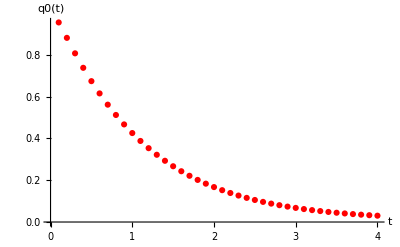

```mathematica
(*Plot the points using ListPlot*)
ListPlot[Table[{t,q0tNumFive[t,1,1,1]},{t,0.1,4,0.1}],PlotStyle->Red,PlotMarkers->Automatic,AxesLabel->{"t","q0(t)"}]
```

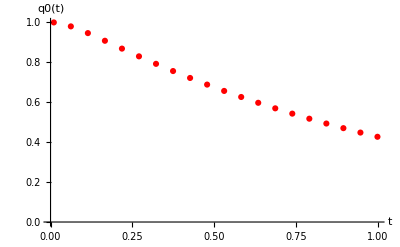

```mathematica
(*Plot the points using ListPlot*)
ListPlot[Table[{t,q0tNumFive[t,1,1,1]},{t,0.01,1,0.052}],PlotStyle->Red,PlotMarkers->Automatic,AxesLabel->{"t","q0(t)"}]
```

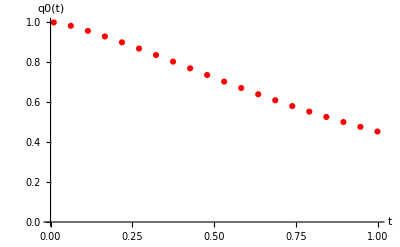

```mathematica
(*Plot the points using ListPlot*)
ListPlot[Table[{t,q0tNumFive[t,1,10,1]},{t,0.01,1,0.052}],PlotStyle->Red,PlotMarkers->Automatic,AxesLabel->{"t","q0(t)"}]
```

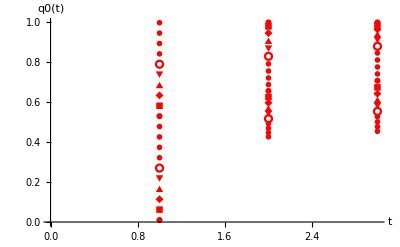

```mathematica
(*Plot the points using ListPlot*)
ListPlot[Table[{t,q0tNumFive[t,1,1,1],q0tNumFive[t,1,20,1]},{t,0.01,1,0.052}],PlotStyle->Red,PlotMarkers->Automatic,AxesLabel->{"t","q0(t)"}]
```

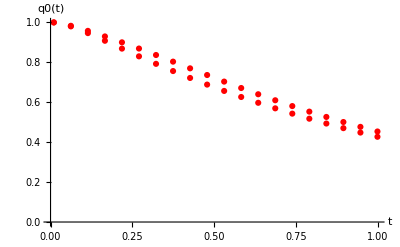

```mathematica
Show[{ListPlot[Table[{t,q0tNumFive[t,1,1,1]},{t,0.01,1,0.052}],PlotStyle->Red,PlotMarkers->Automatic,AxesLabel->{"t","q0(t)"}],
ListPlot[Table[{t,q0tNumFive[t,1,10,1]},{t,0.01,1,0.052}],PlotStyle->Red,PlotMarkers->Automatic,AxesLabel->{"t","q0(t)"}]}]
```

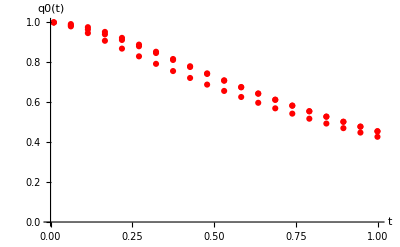

```mathematica
Show[{ListPlot[Table[{t,q0tNumFive[t,1,1,1]},{t,0.01,1,0.052}],PlotStyle->Red,PlotMarkers->Automatic,AxesLabel->{"t","q0(t)"}],
ListPlot[Table[{t,q0tNumFive[t,1,20,1]},{t,0.01,1,0.052}],PlotStyle->Red,PlotMarkers->Automatic,AxesLabel->{"t","q0(t)"}],ListPlot[Table[{t,q0tNumFive[t,1,80,1]},{t,0.01,1,0.052}],PlotStyle->Red,PlotMarkers->Automatic,AxesLabel->{"t","q0(t)"}]}]
```

## Hacer graficas de nuevo

```mathematica
FXX[α_,κ_,η_,t_]:=(η(κ+2η)+4α^2)/(η(κ+2η)+8α^2)+(4α^2)/(η(κ+2η)+8α^2)Exp[-(κ/4+η)t]*((4η+κ)Sin[Sqrt[64α^2-κ^2]t/4]/Sqrt[64α^2-κ^2]+Cos[Sqrt[64α^2-κ^2]t/4])
```

FIG 2. Plot for different values of k and R=η/α=1

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

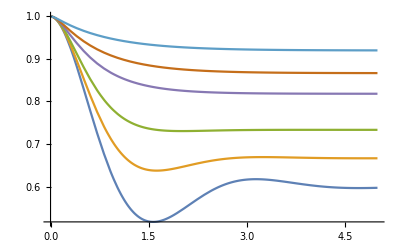

```mathematica
Plot[{FXX[1,0,1,t],FXX[1,2,1,t],FXX[1,5,1,t],FXX[1,8,1,t],FXX[1,12,1,t],FXX[1,20,1,t],FXX[1,40,1,t]},{t,0,5}]
```

FIG 12. Plot for different values of k and R = η/α = 1

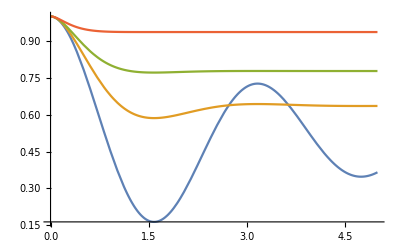

```mathematica
Plot[{FXX[1,1,0,t],FXX[1,1,1,t],FXX[1,1,2,t],FXX[1,1,5,t]},{t,0,5}]
```

```mathematica
L1five[γ_]:=γ{{-15,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{15,-13,2,2,0,0,0,0,0,0,0,0,0,0,0,0},{0,4,-15,2,3,1,0,0,0,0,0,0,0,0,0,0},{0,8,4,-13,0,2,3,0,0,0,0,0,0,0,0,0},{0,0,3,0,-15,1,0,0,1,0,4,0,0,0,0,0},{0,0,6,6,6,-12,6,4,3,2,0,0,0,0,0,0},{0,0,0,3,0,2,-15,0,0,2,0,0,0,0,0,0},{0,0,0,0,0,2,0,-15,3,2,0,0,3,1,0,0},{0,0,0,0,4,2,0,4,-14,2,8,4,2,0,2,0},{0,0,0,0,0,2,6,4,3,-11,0,0,0,4,3,0},{0,0,0,0,2,0,0,0,1,0,-15,1,0,0,0,5},{0,0,0,0,0,0,0,0,1,0,2,-14,2,0,2,10},{0,0,0,0,0,0,0,2,1,0,0,4,-12,2,2,0},{0,0,0,0,0,0,0,1,0,2,0,0,3,-11,6,0},{0,0,0,0,0,0,0,0,1,1,0,4,2,4,-15,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,-15}};
MatrixForm[L1five[1]]
Total[L1five[γ],{1}]
Eigenvalues[L1five[1]]
NullSpace[L1five[1]]
```

(-15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15 | -13 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | -15 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 | 4 | -13 | 0 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | -15 | 1 | 0 | 0 | 1 | 0 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 6 | 6 | -12 | 6 | 4 | 3 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 2 | -15 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | -15 | 3 | 2 | 0 | 0 | 3 | 1 | 0 | 0
0 | 0 | 0 | 0 | 4 | 2 | 0 | 4 | -14 | 2 | 8 | 4 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 2 | 6 | 4 | 3 | -11 | 0 | 0 | 0 | 4 | 3 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | -15 | 1 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | -14 | 2 | 0 | 2 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 4 | -12 | 2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 3 | -11 | 6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 4 | 2 | 4 | -15 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | -15)

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{-20,-20,-20,-20,-20,-16,-16,-16,-16,-12,-12,-12,-8,-8,-4,0}

{{1,15,30,60,30,180,60,90,120,180,15,30,60,90,60,3}}

```mathematica
L0fivecorrect[η_]:=η{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,-1/3,1,2/3,1/2,1/3,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/3,0,-5/6,1/2,1/3,0,0,1/2,1/6,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,0,0,1/6,0,1/3,0,0,1/2,-1/6,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}}
MatrixForm[L0fivecorrect[1]]
Eigenvalues[L0fivecorrect[1]]
NullSpace[L0fivecorrect[1]]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | -1/3 | 1 | 2/3 | 1/2 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/3 | 0 | -5/6 | 1/2 | 1/3 | 0 | 0 | 1/2 | 1/6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 1/3 | 0 | 0 | 1/2 | -1/6 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0)

{1/3 (-2-√2),-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1/3 (-2+√2),0,0,0}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,2,0,1,0,0,0,0,0,1,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
NullSpace[L1five[1]]
```

{{1,15,30,60,30,180,60,90,120,180,15,30,60,90,60,3}}

```mathematica
NullSpace[L0fivecorrect[η]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,2,0,1,0,0,0,0,0,1,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Eigenvalues[L1five[1]]
```

{-20,-20,-20,-20,-20,-16,-16,-16,-16,-12,-12,-12,-8,-8,-4,0}

```mathematica
Eigenvalues[L1five[γ]]
NullSpace[L1five[1]]
```

{-20 γ,-20 γ,-20 γ,-20 γ,-20 γ,-16 γ,-16 γ,-16 γ,-16 γ,-12 γ,-12 γ,-12 γ,-8 γ,-8 γ,-4 γ,0}

{{1,15,30,60,30,180,60,90,120,180,15,30,60,90,60,3}}

```mathematica
Eigenvalues[L0fivecorrect[η]]
NullSpace[L0fivecorrect[η]]
```

{1/3 (-2-√2) η,-η,-η,-η,-η,-η,-η,-η,-η,-η,-η,-η,1/3 (-2+√2) η,0,0,0}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,2,0,1,0,0,0,0,0,1,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
M5diss[γ_,η_]:=L1five[γ]+L0fivecorrect[η]
M5diss[γ,η]//MatrixForm
((IdentityMatrix[16]+M5diss[γ,η]t+MatrixPower[M5diss[γ,η],2] (t^2/2)+MatrixPower[M5diss[γ,η],3] (t^3/6)).{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0})//MatrixForm
```

(-15 γ | γ+η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15 γ | -13 γ-η | 2 γ | 2 γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 γ | -15 γ-η | 2 γ | 3 γ | γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 γ | 4 γ | -13 γ-η | 0 | 2 γ | 3 γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 γ | 0 | -15 γ-η | γ | 0 | 0 | γ | 0 | 4 γ | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 γ+η | 6 γ+η | 6 γ+η | -12 γ-η/3 | 6 γ+η | 4 γ+(2 η)/3 | 3 γ+η/2 | 2 γ+η/3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 γ | 0 | 2 γ | -15 γ-η | 0 | 0 | 2 γ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 γ+η/3 | 0 | -15 γ-(5 η)/6 | 3 γ+η/2 | 2 γ+η/3 | 0 | 0 | 3 γ+η/2 | γ+η/6 | 0 | 0
0 | 0 | 0 | 0 | 4 γ | 2 γ | 0 | 4 γ | -14 γ-η | 2 γ | 8 γ | 4 γ | 2 γ | 0 | 2 γ | 0
0 | 0 | 0 | 0 | 0 | 2 γ | 6 γ | 4 γ | 3 γ | -11 γ-η | 0 | 0 | 0 | 4 γ | 3 γ | 0
0 | 0 | 0 | 0 | 2 γ | 0 | 0 | 0 | γ | 0 | -15 γ-η | γ | 0 | 0 | 0 | 5 γ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ | 0 | 2 γ | -14 γ-η | 2 γ | 0 | 2 γ | 10 γ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ | γ | 0 | 0 | 4 γ | -12 γ-η | 2 γ | 2 γ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | γ+η/6 | 0 | 2 γ+η/3 | 0 | 0 | 3 γ+η/2 | -11 γ-η/6 | 6 γ+η | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ | γ | 0 | 4 γ | 2 γ | 4 γ | -15 γ-η | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ+η | γ+η | 0 | 0 | 0 | -15 γ)

(1-15 t γ+1/2 t^2 (225 γ^2+15 γ (γ+η))+1/6 t^3 ((-225 γ^2+15 γ (-13 γ-η)) (γ+η)-15 γ (225 γ^2+15 γ (γ+η)))
15 t γ+1/2 t^2 (-225 γ^2+15 γ (-13 γ-η))+1/6 t^3 (360 γ^3+(-225 γ^2+15 γ (-13 γ-η)) (-13 γ-η)+15 γ (225 γ^2+15 γ (γ+η)))
30 t^2 γ^2+1/6 t^3 (240 γ^3+4 γ (-225 γ^2+15 γ (-13 γ-η))+60 γ^2 (-15 γ-η))
60 t^2 γ^2+1/6 t^3 (240 γ^3+8 γ (-225 γ^2+15 γ (-13 γ-η))+120 γ^2 (-13 γ-η))
30 t^3 γ^3
30 t^3 γ^2 (6 γ+η)
60 t^3 γ^3
0
0
0
0
0
0
0
0
0)

```mathematica
M5ShortTime[γ_,η_,t_]:=IdentityMatrix[16]+M5diss[γ,η]t+MatrixPower[M5diss[γ,η],2] t^2/(2!)+MatrixPower[M5diss[γ,η],3] t^3/(3!)+MatrixPower[M5diss[γ,η],4] t^4/(4!)+MatrixPower[M5diss[γ,η],5] t^5/(5!)
FullSimplify[(M5ShortTime[γ,η,t].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0})[[1]]+(M5ShortTime[γ,η,t].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0})[[2]]]
Expand[FullSimplify[(M5ShortTime[γ,η,t].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0})[[1]]+(M5ShortTime[γ,η,t].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0})[[2]]]]
```

1+3/2 t^2 γ^2 (-60+20 t (30 γ+η)-5 t^2 (706 γ^2+60 γ η+η^2)+t^3 (15288 γ^3+2304 γ^2 η+90 γ η^2+η^3))

1-90 t^2 γ^2+900 t^3 γ^3-5295 t^4 γ^4+22932 t^5 γ^5+30 t^3 γ^2 η-450 t^4 γ^3 η+3456 t^5 γ^4 η-15/2 t^4 γ^2 η^2+135 t^5 γ^3 η^2+3/2 t^5 γ^2 η^3

```mathematica
15*12/2
```

90

```mathematica
(L1five[γ]+L0fivecorrect[η]).{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
```

{-15 γ,15 γ,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FullSimplify[MatrixForm[Dot[MatrixExp[M3[γ,η]],{1,0,0,0}]]]

FullSimplify[((IdentityMatrix[4]+M3[γ,η] t+MatrixPower[M3[γ,η],2] (t^2/2)+MatrixPower[M3[γ,η],3] (t^3/6)).{1,0,0,0})[[1]]]

FullSimplify[((IdentityMatrix[4]+M3[γ,η] t+MatrixPower[M3[γ,η],2] (t^2/2)+MatrixPower[M3[γ,η],3] (t^3/6)).{1,0,0,0})[[1]]+((IdentityMatrix[4]+M3[γ,η] t+MatrixPower[M3[γ,η],2] (t^2/2)+MatrixPower[M3[γ,η],3] (t^3/6)).{1,0,0,0})[[2]]]
```

Again PMME

```mathematica
PmmeMat5ExpKernel[s_,γ_?NumericQ,η_?NumericQ,c_?NumericQ]:=-s IdentityMatrix[16]+L0fivecorrect[η]+(L1five[γ].Transpose[Eigenvectors[L1five[γ]]]).(DiagonalMatrix[{kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[1]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[2]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[3]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[4]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[5]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[6]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[7]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[8]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[9]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[10]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[11]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[12]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[13]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[14]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[15]]],kLapExpKernel[s,c,Eigenvalues[L1five[γ]][[16]]]}].Inverse[Transpose[Eigenvectors[L1five[γ]]]])
```

```mathematica
PmmeMat5ExpKernel
```

```mathematica
overlap5q[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][(Inverse[-PmmeMat5ExpKernel[s,γ,η,c]].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0})[[1]],s,t]+ResourceFunction["NInverseLaplaceTransform"][(Inverse[-PmmeMat5ExpKernel[s,γ,η,c]].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0})[[2]],s,t]
```

```mathematica
ListPlot[Table[{t,overlap5q[t,1,0,1]},{t,0.1,4,0.1}],PlotStyle->Red,PlotMarkers->Automatic,AxesLabel->{"t","q0(t)"}]
```

$Aborted

```mathematica
ListPlot[Table[{t,overlap5q[t,1,0,1],overlap5q[t,1,100,1],overlap5q[t,1,300,1]},{t,0.1,4,0.1}],PlotStyle->Red,PlotMarkers->Automatic,AxesLabel->{"t","q0(t)"}]
```